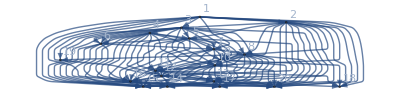

109

{0,0,0,0,0,0,0,0,0,0,0,0,0,3,15,4,47,2,19,10}

```mathematica
n=20;
destCount=7;
flow=100;
g= Graph[
Table[i,{i,n}],
Join[
Flatten[Table[i->j,{i,n-destCount-1},{j,RandomSample[Range[i+2,n-destCount],RandomInteger[n-i-destCount-1]]}]],
Table[i->i+1,{i,1,n-1-destCount}],
Flatten[Table[i->j,{j,n-destCount+1,n},{i,RandomSample[Range[n-destCount],RandomInteger[{1,n-destCount}]]}]]
],
VertexLabels->Table[i->i,{i,n}]
]
val=Sort[EdgeList[g]]; (*care arce sunt in graf*)
m=EdgeCount[g] (*numarul de arce*)

adjList=Join[{{0}},Sort[Gather[val,#1[[2]]==#2[[2]]&],#1[[1,2]]<#2[[1,2]]&][[All,All,1]]];

dest=Table[n-destCount+i,{i,destCount}];
flows = Differences[Flatten[{0,Sort[RandomSample[Range[flow-1],destCount-1]],flow}]];
(*Aici punem ce flux treb sa ajunga in fiecare destinatie*)
b=Table[0,n];
b[[n-destCount+1;;n]]=flows;(*marimea fluxului transmis din sursa spre destinatie*)
                                                (* b⟦1,2⟧=-1;b⟦n,2⟧=1;*)
b
X=Array[x,m];

(* Creaza un hash map care codeaza muchia cu pozitia ei in lista de muchii ---- Modul de codare este i*n + j pentru muchia i -> j *)
pos = SparseArray[MapIndexed[#⟦1⟧*n+#⟦2⟧->#2⟦1⟧&,val]];

lu=Table[{0,100},{i,m}];

γ=Table[RandomInteger[{1,5}],m];
δ=Table[RandomInteger[{1,5}],m];
f[j_Integer,x_]:=Piecewise[{{γ⟦j⟧ x, x≤δ⟦j⟧}, {γ⟦j⟧ δ⟦j⟧, x>δ⟦j⟧}, {0, True}}]
fd[j_Integer,x_]:=Piecewise[{{f[j,x]/x, x>0}, {γ⟦j⟧, x==0}, {0, True}}]
```

# Alg 3

```mathematica
(*Constante necesare pentru algoritm*)
prev=-1;(*Pentru epsilon*)
epsilon=0.0001;(*Pentru epsilon*)
numarIteratii=10;(*Pentru k iteratii*)
Do[
Print[Style["Test ","Section"],Style[bigCount,"Section"]];
thisTimer=Timing[
(*Generarea populatiei initiale*)
chromosomes= DeleteDuplicates[Table[Table[RandomChoice[adjList⟦i⟧]->i,{i,2,n}],{k,4*n}]];
chromosomeCount=Length[chromosomes];
(*Aflarea parintilor fiecarui nod*)

parents=Table[Flatten[{1,Sort[chromosomes[[i]],#1[[2]]<#2[[2]]&][[All,1]]}],{i,chromosomeCount}];
(*Aflarea solutiilor asociate*)
solutions=Table[
currentFlow=b;
currentX=Table[0,m];
currentSol=0;
DepthFirstScan[chromosomes⟦i⟧,1,"PostvisitVertex"->(
If[#≠parents⟦i⟧⟦#⟧,
edgeId=pos⟦parents⟦i⟧⟦#⟧*n+#⟧;
currentFlow⟦parents⟦i⟧⟦#⟧⟧+=currentFlow⟦#⟧;
currentX⟦edgeId⟧+=currentFlow⟦#⟧;
currentSol+=f[edgeId,currentFlow⟦#⟧];
]&)];
(*Print[{currentSol,currentX}];*)
currentSol
,{i,chromosomeCount}];
Print["Populatia initiala ",chromosomes];
Do[
Print["------------------------------------------------------------------"];
Print["Iteratia ",countIter];
(*Sortarea si alegerea cromozomilor parinti*)
chromosomes=chromosomes[[Ordering[solutions][[;;Quotient[chromosomeCount-Mod[chromosomeCount,4],2]]]]];
chromosomeCount=Length@chromosomes*2;
(*Aflarea parintilor fiecarui nod*)
parents=Table[Flatten[{1,Sort[chromosomes[[i]],#1[[2]]<#2[[2]]&][[All,1]]}],{i,chromosomeCount/2}];
(*Incrucisarea*)
children=Flatten[Table[
cutPoint=n-destCount+RandomInteger[{1,destCount-1}];
DestListLeft=Range[n-destCount+1,cutPoint];
DestListRight=Range[cutPoint+1,n];
edgeListLeft=Table[{},2];
edgeListRight=Table[{},2];
child=Table[{},2];
untouched=Table[{},2];
Do[
visitedVertices=Table[0,n];
visitedVertices[[DestListLeft]]=1;
visitedVertices[[DestListRight]]=2;
edgeListLeft⟦j-i+1⟧=Reap[DepthFirstScan[chromosomes⟦j⟧,1,"PostvisitVertex"->(
If[visitedVertices⟦#⟧==1&&#≠parents⟦i⟧⟦#⟧,
visitedVertices⟦parents⟦j⟧⟦#⟧⟧=1;
Sow[parents⟦j⟧⟦#⟧->#];
]&)]]⟦2,1⟧;
edgeListRight⟦j-i+1⟧=Reap[DepthFirstScan[chromosomes⟦j⟧,1,"PostvisitVertex"->(
If[visitedVertices⟦#⟧==2&&#≠parents⟦i⟧⟦#⟧,
visitedVertices⟦parents⟦j⟧⟦#⟧⟧=2;
Sow[parents⟦j⟧⟦#⟧->#];
]&)]]⟦2,1⟧;
,{j,i,i+1}];


child⟦1⟧=Union[edgeListLeft⟦1⟧,edgeListRight⟦2⟧];
child⟦2⟧=Union[edgeListLeft⟦2⟧,edgeListRight⟦1⟧];
untouched⟦1⟧=Complement[Range[n],child⟦1,All,2⟧];
untouched⟦2⟧=Complement[Range[n],child⟦2,All,2⟧];


Do[
If[untouched⟦j-i+1⟧=={},Continue[]];
visitedVertices=Table[0,n];
visitedVertices[[untouched⟦j-i+1⟧]]=1;
untouched⟦j-i+1⟧=Reap[DepthFirstScan[chromosomes⟦j⟧,1,"PostvisitVertex"->(
If[visitedVertices⟦#⟧==1,
visitedVertices⟦parents⟦j⟧⟦#⟧⟧=1;
Sow[parents⟦j⟧⟦#⟧->#];
]&)]]⟦2,1⟧;
,{j,i,i+1}];

child⟦1⟧=EdgeList@FindSpanningTree[Union[child⟦1⟧,untouched⟦1⟧]];
child⟦2⟧=EdgeList@FindSpanningTree[Union[child⟦2⟧,untouched⟦2⟧]];

{child⟦1⟧,child⟦2⟧}
,{i,1,chromosomeCount/2,2}],1];
chromosomes=Join[chromosomes,children];
Graph[#,VertexLabels->Automatic,GraphLayout->{"LayeredEmbedding","RootVertex"->1}]&/@chromosomes;
(*Mutatia*)
possibleVertices=DeleteCases[Table[If[Length@adjList[[i]]>1,i,0],{i,n}],0];
Do[
If[RandomReal[]<0.5,Continue[]];
chosenVertex=RandomChoice[possibleVertices];
chosenArc=Select[chromosomes⟦i⟧,#⟦2⟧==chosenVertex&];
chromosomes⟦i⟧=DeleteCases[chromosomes⟦i⟧,chosenArc[[1]]];
newParent=RandomChoice[Complement[adjList⟦chosenVertex⟧,{chosenArc⟦1,1⟧}]];
chromosomes⟦i⟧=Union[chromosomes⟦i⟧,{newParent->chosenVertex}];
,{i,chromosomeCount/2+1,chromosomeCount}];
Graph[#,VertexLabels->Automatic,GraphLayout->{"LayeredEmbedding","RootVertex"->1}]&/@chromosomes;
(*Aflarea parintilor fiecarui nod*)
parents=Table[Flatten[{1,Sort[chromosomes[[i]],#1[[2]]<#2[[2]]&][[All,1]]}],{i,chromosomeCount}];
(*Aflarea solutiilor asociate*)
bestSol=100000000000000000000;
bestX=Table[0,m];
solutions=Table[
currentFlow=b;
currentX=Table[0,m];
currentSol=0;
DepthFirstScan[chromosomes⟦i⟧,1,"PostvisitVertex"->(
If[#≠parents⟦i⟧⟦#⟧,

edgeId=pos⟦parents⟦i⟧⟦#⟧*n+#⟧;
currentFlow⟦parents⟦i⟧⟦#⟧⟧+=currentFlow⟦#⟧;
currentX⟦edgeId⟧+=currentFlow⟦#⟧;


currentSol+=f[edgeId,currentFlow⟦#⟧];
]&)];
If[bestSol>currentSol,bestSol=currentSol;bestX=currentX];
(*Print[{currentSol,currentX}];*)
currentSol
,{i,chromosomeCount}];
Print["Parintii si urmasii ",chromosomes];
Print["Cel mai bun cromozom ",chromosomes[[Ordering[solutions,1]]]];
Print["Cea mai buna solutie ",{Min[solutions],bestX}];
Print["Functia obiectiv totala ",Total[solutions]];
(*Print[Graph[#,VertexLabels->Automatic,GraphLayout->{"LayeredEmbedding","RootVertex"->1}]&/@chromosomes[[Ordering[solutions,1]]]];*)

,{countIter,numarIteratii}];
];
Print[thisTimer];
,{bigCount,1,10}]
```

Test 1

Populatia initiala {{1->2,2->3,3->4,4->5,5->6,5->7,1->8,7->9,9->10,5->11,9->12,8->13,2->14,2->15,7->16,2->17,13->18,3->19,1->20},{1->2,2->3,3->4,4->5,4->6,3->7,1->8,3->9,4->10,8->11,2->12,5->13,1->14,11->15,2->16,4->17,1->18,3->19,12->20},{1->2,2->3,3->4,3->5,1->6,1->7,3->8,3->9,1->10,10->11,9->12,11->13,11->14,2->15,9->16,8->17,1->18,8->19,9->20},{1->2,1->3,3->4,4->5,1->6,6->7,3->8,2->9,4->10,10->11,4->12,9->13,12->14,9->15,2->16,2->17,1->18,8->19,3->20},{1->2,1->3,3->4,4->5,1->6,6->7,1->8,2->9,9->10,7->11,8->12,12->13,11->14,5->15,2->16,3->17,11->18,8->19,1->20},{1->2,1->3,3->4,3->5,3->6,6->7,7->8,5->9,3->10,7->11,8->12,4->13,10->14,7->15,1->16,4->17,9->18,3->19,5->20},{1->2,1->3,3->4,3->5,1->6,5->7,3->8,3->9,3->10,8->11,8->12,2->13,10->14,13->15,6->16,13->17,1->18,3->19,8->20},{1->2,2->3,3->4,2->5,3->6,6->7,1->8,7->9,1->10,3->11,8->12,5->13,1->14,2->15,4->16,10->17,2->18,8->19,13->20},{1->2,1->3,3->4,2->5,1->6,6->7,3->8,2->9,1->10,7->11,5->12,11->13,1->14,11->15,11->16,8->17,1->18,3->19,12->20},{1->2,1->3,3->4,3->5,5->6,6->7,3->8,7->9,3->10,7->11,8->12,5->13,2->14,3->15,6->16,10->17,1->18,8->19,3->20},{1->2,2->3,3->4,4->5,4->6,1->7,7->8,5->9,3->10,10->11,5->12,5->13,2->14,13->15,5->16,2->17,1->18,8->19,8->20},{1->2,1->3,3->4,3->5,1->6,6->7,3->8,4->9,1->10,5->11,11->12,8->13,1->14,13->15,4->16,2->17,13->18,8->19,10->20},{1->2,1->3,3->4,2->5,4->6,6->7,7->8,2->9,3->10,8->11,2->12,12->13,13->14,7->15,2->16,7->17,13->18,8->19,7->20},{1->2,1->3,3->4,3->5,5->6,1->7,3->8,8->9,8->10,3->11,5->12,5->13,2->14,5->15,1->16,9->17,9->18,8->19,10->20},{1->2,1->3,3->4,2->5,5->6,3->7,3->8,3->9,4->10,10->11,8->12,4->13,10->14,4->15,3->16,9->17,2->18,3->19,4->20},{1->2,2->3,3->4,4->5,3->6,6->7,2->8,3->9,1->10,8->11,1->12,11->13,1->14,2->15,6->16,7->17,1->18,3->19,4->20},{1->2,2->3,3->4,2->5,1->6,1->7,3->8,2->9,1->10,10->11,11->12,8->13,1->14,10->15,6->16,13->17,13->18,8->19,4->20},{1->2,2->3,3->4,2->5,5->6,5->7,3->8,2->9,9->10,8->11,5->12,11->13,12->14,10->15,9->16,7->17,2->18,8->19,9->20},{1->2,2->3,3->4,4->5,1->6,5->7,1->8,4->9,3->10,4->11,2->12,2->13,11->14,4->15,4->16,4->17,11->18,3->19,13->20},{1->2,1->3,3->4,3->5,4->6,3->7,3->8,7->9,9->10,10->11,5->12,12->13,10->14,13->15,6->16,4->17,11->18,3->19,1->20},{1->2,1->3,3->4,4->5,4->6,3->7,1->8,5->9,1->10,7->11,11->12,10->13,12->14,1->15,3->16,3->17,13->18,3->19,2->20},{1->2,1->3,3->4,3->5,1->6,1->7,3->8,8->9,4->10,7->11,5->12,9->13,13->14,1->15,12->16,9->17,1->18,8->19,9->20},{1->2,2->3,3->4,3->5,3->6,3->7,3->8,2->9,1->10,5->11,5->12,9->13,11->14,10->15,11->16,13->17,13->18,3->19,4->20},{1->2,2->3,3->4,4->5,1->6,6->7,3->8,2->9,4->10,7->11,8->12,4->13,1->14,3->15,12->16,13->17,13->18,8->19,6->20},{1->2,2->3,3->4,3->5,1->6,1->7,3->8,3->9,4->10,7->11,5->12,4->13,2->14,4->15,7->16,10->17,11->18,3->19,5->20},{1->2,2->3,3->4,2->5,5->6,6->7,2->8,8->9,8->10,4->11,9->12,11->13,11->14,8->15,6->16,8->17,2->18,8->19,2->20},{1->2,1->3,3->4,2->5,4->6,6->7,7->8,5->9,9->10,10->11,9->12,10->13,2->14,13->15,12->16,8->17,13->18,8->19,7->20},{1->2,2->3,3->4,4->5,1->6,1->7,7->8,8->9,4->10,4->11,8->12,4->13,2->14,6->15,12->16,10->17,11->18,8->19,8->20},{1->2,1->3,3->4,3->5,3->6,5->7,1->8,7->9,8->10,7->11,2->12,5->13,12->14,2->15,5->16,8->17,2->18,8->19,11->20},{1->2,2->3,3->4,3->5,1->6,5->7,7->8,3->9,8->10,3->11,11->12,5->13,13->14,5->15,7->16,6->17,2->18,3->19,5->20},{1->2,1->3,3->4,3->5,1->6,1->7,7->8,2->9,1->10,5->11,1->12,4->13,11->14,13->15,5->16,7->17,11->18,3->19,12->20},{1->2,1->3,3->4,4->5,4->6,5->7,1->8,5->9,4->10,7->11,4->12,10->13,11->14,4->15,2->16,13->17,2->18,8->19,1->20},{1->2,1->3,3->4,4->5,1->6,1->7,3->8,2->9,8->10,3->11,9->12,10->13,11->14,13->15,2->16,9->17,9->18,3->19,11->20},{1->2,2->3,3->4,3->5,3->6,6->7,7->8,5->9,9->10,7->11,1->12,8->13,13->14,5->15,7->16,3->17,11->18,3->19,12->20},{1->2,1->3,3->4,4->5,1->6,3->7,1->8,4->9,1->10,10->11,9->12,12->13,1->14,4->15,3->16,6->17,11->18,3->19,6->20},{1->2,2->3,3->4,3->5,5->6,5->7,2->8,4->9,4->10,7->11,1->12,9->13,1->14,5->15,9->16,3->17,1->18,3->19,11->20},{1->2,2->3,3->4,3->5,5->6,5->7,7->8,2->9,1->10,8->11,8->12,4->13,1->14,8->15,2->16,9->17,13->18,8->19,9->20},{1->2,2->3,3->4,4->5,4->6,1->7,1->8,3->9,3->10,3->11,2->12,8->13,1->14,13->15,4->16,10->17,13->18,8->19,4->20},{1->2,2->3,3->4,3->5,3->6,6->7,1->8,2->9,8->10,8->11,1->12,10->13,12->14,4->15,3->16,10->17,11->18,8->19,13->20},{1->2,1->3,3->4,3->5,5->6,3->7,3->8,2->9,1->10,5->11,5->12,8->13,11->14,13->15,7->16,13->17,2->18,8->19,6->20},{1->2,2->3,3->4,4->5,4->6,5->7,7->8,2->9,4->10,4->11,2->12,5->13,1->14,10->15,6->16,7->17,9->18,3->19,2->20},{1->2,2->3,3->4,4->5,5->6,1->7,1->8,8->9,3->10,5->11,11->12,9->13,3->14,7->15,11->16,9->17,11->18,3->19,6->20},{1->2,2->3,3->4,3->5,5->6,1->7,2->8,7->9,8->10,5->11,2->12,9->13,3->14,5->15,7->16,4->17,11->18,8->19,4->20},{1->2,2->3,3->4,4->5,3->6,3->7,3->8,3->9,9->10,4->11,11->12,10->13,3->14,3->15,9->16,10->17,13->18,8->19,11->20},{1->2,1->3,3->4,3->5,1->6,3->7,3->8,5->9,9->10,5->11,1->12,12->13,2->14,4->15,5->16,13->17,13->18,3->19,6->20},{1->2,1->3,3->4,4->5,3->6,6->7,1->8,7->9,8->10,5->11,2->12,2->13,2->14,13->15,5->16,10->17,9->18,3->19,13->20},{1->2,1->3,3->4,2->5,4->6,3->7,7->8,5->9,4->10,5->11,5->12,10->13,2->14,13->15,11->16,8->17,11->18,8->19,8->20},{1->2,2->3,3->4,3->5,1->6,6->7,7->8,4->9,8->10,10->11,2->12,9->13,11->14,5->15,12->16,9->17,9->18,8->19,2->20},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,7->9,8->10,7->11,8->12,11->13,2->14,6->15,7->16,9->17,2->18,8->19,12->20},{1->2,2->3,3->4,2->5,3->6,3->7,7->8,8->9,8->10,10->11,1->12,2->13,2->14,11->15,5->16,3->17,1->18,3->19,4->20},{1->2,2->3,3->4,3->5,5->6,3->7,2->8,8->9,3->10,4->11,9->12,5->13,10->14,8->15,6->16,10->17,13->18,8->19,10->20},{1->2,1->3,3->4,3->5,4->6,1->7,2->8,8->9,9->10,8->11,9->12,5->13,11->14,13->15,11->16,3->17,2->18,3->19,5->20},{1->2,2->3,3->4,3->5,3->6,5->7,7->8,3->9,9->10,7->11,1->12,12->13,2->14,7->15,4->16,6->17,11->18,3->19,13->20},{1->2,1->3,3->4,2->5,3->6,6->7,7->8,3->9,8->10,7->11,8->12,8->13,3->14,2->15,5->16,6->17,13->18,8->19,8->20},{1->2,1->3,3->4,3->5,1->6,3->7,3->8,8->9,8->10,10->11,9->12,11->13,12->14,2->15,6->16,4->17,2->18,8->19,6->20},{1->2,2->3,3->4,4->5,4->6,5->7,3->8,2->9,8->10,10->11,5->12,4->13,1->14,6->15,1->16,3->17,9->18,3->19,11->20},{1->2,1->3,3->4,3->5,3->6,5->7,2->8,3->9,8->10,3->11,2->12,11->13,3->14,7->15,5->16,2->17,11->18,3->19,1->20},{1->2,1->3,3->4,2->5,5->6,5->7,1->8,5->9,9->10,7->11,8->12,8->13,1->14,5->15,9->16,2->17,13->18,3->19,1->20},{1->2,1->3,3->4,3->5,1->6,1->7,7->8,2->9,1->10,10->11,1->12,11->13,13->14,8->15,12->16,8->17,1->18,3->19,7->20},{1->2,1->3,3->4,3->5,1->6,6->7,3->8,8->9,3->10,10->11,1->12,2->13,13->14,5->15,9->16,9->17,9->18,8->19,12->20},{1->2,1->3,3->4,4->5,3->6,6->7,2->8,7->9,1->10,5->11,9->12,10->13,2->14,2->15,5->16,13->17,1->18,3->19,11->20},{1->2,1->3,3->4,3->5,1->6,1->7,1->8,8->9,1->10,10->11,2->12,11->13,10->14,8->15,2->16,7->17,2->18,3->19,1->20},{1->2,2->3,3->4,4->5,1->6,1->7,7->8,5->9,4->10,7->11,4->12,10->13,13->14,9->15,12->16,4->17,9->18,8->19,12->20},{1->2,2->3,3->4,2->5,3->6,5->7,1->8,5->9,3->10,8->11,9->12,11->13,3->14,13->15,12->16,9->17,9->18,3->19,3->20},{1->2,1->3,3->4,2->5,4->6,1->7,3->8,2->9,8->10,3->11,1->12,8->13,11->14,6->15,9->16,7->17,11->18,8->19,12->20},{1->2,2->3,3->4,4->5,5->6,3->7,2->8,3->9,1->10,10->11,4->12,11->13,10->14,6->15,12->16,13->17,2->18,8->19,4->20},{1->2,2->3,3->4,3->5,5->6,6->7,3->8,2->9,3->10,8->11,5->12,11->13,2->14,13->15,2->16,8->17,9->18,8->19,1->20},{1->2,1->3,3->4,4->5,5->6,3->7,3->8,3->9,9->10,7->11,5->12,2->13,1->14,13->15,6->16,13->17,9->18,8->19,5->20},{1->2,2->3,3->4,4->5,3->6,5->7,2->8,5->9,1->10,8->11,1->12,9->13,13->14,11->15,6->16,13->17,1->18,8->19,5->20},{1->2,1->3,3->4,4->5,4->6,6->7,7->8,4->9,9->10,4->11,9->12,9->13,10->14,4->15,1->16,10->17,1->18,8->19,7->20},{1->2,2->3,3->4,2->5,5->6,5->7,3->8,8->9,3->10,7->11,11->12,12->13,2->14,8->15,6->16,2->17,13->18,3->19,10->20},{1->2,2->3,3->4,4->5,4->6,5->7,2->8,7->9,9->10,8->11,11->12,2->13,10->14,4->15,3->16,13->17,1->18,3->19,13->20},{1->2,2->3,3->4,2->5,3->6,1->7,7->8,8->9,9->10,5->11,8->12,5->13,1->14,1->15,12->16,4->17,9->18,3->19,11->20},{1->2,1->3,3->4,4->5,5->6,6->7,2->8,4->9,3->10,7->11,4->12,9->13,1->14,8->15,3->16,2->17,13->18,8->19,1->20},{1->2,1->3,3->4,4->5,4->6,3->7,1->8,7->9,1->10,5->11,1->12,11->13,11->14,2->15,6->16,2->17,2->18,8->19,3->20},{1->2,2->3,3->4,4->5,4->6,5->7,3->8,5->9,1->10,4->11,5->12,8->13,12->14,2->15,12->16,13->17,11->18,3->19,4->20},{1->2,1->3,3->4,4->5,1->6,3->7,1->8,4->9,1->10,8->11,4->12,4->13,3->14,4->15,7->16,10->17,13->18,3->19,3->20},{1->2,1->3,3->4,3->5,3->6,1->7,7->8,5->9,1->10,5->11,11->12,2->13,1->14,1->15,6->16,2->17,13->18,3->19,11->20},{1->2,2->3,3->4,4->5,1->6,5->7,3->8,4->9,1->10,7->11,9->12,4->13,11->14,9->15,6->16,3->17,1->18,8->19,9->20},{1->2,1->3,3->4,2->5,4->6,6->7,7->8,4->9,9->10,3->11,4->12,10->13,13->14,7->15,11->16,7->17,11->18,8->19,4->20}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,1->3,3->4,3->5,1->6,6->7,3->8,8->9,3->10,10->11,1->12,2->13,13->14,5->15,9->16,9->17,9->18,8->19,12->20},{1->2,1->3,3->4,4->5,3->6,6->7,2->8,7->9,1->10,5->11,9->12,10->13,2->14,2->15,5->16,13->17,1->18,3->19,11->20},{1->2,1->3,3->4,3->5,1->6,6->7,3->8,4->9,1->10,5->11,11->12,8->13,1->14,13->15,4->16,2->17,13->18,8->19,10->20},{1->2,1->3,3->4,3->5,3->6,1->7,7->8,5->9,1->10,5->11,11->12,2->13,1->14,1->15,6->16,2->17,13->18,3->19,11->20},{1->2,1->3,3->4,4->5,1->6,6->7,3->8,2->9,4->10,10->11,4->12,9->13,12->14,9->15,2->16,2->17,1->18,8->19,3->20},{1->2,1->3,3->4,2->5,5->6,3->7,3->8,3->9,4->10,10->11,8->12,4->13,10->14,4->15,3->16,9->17,2->18,3->19,4->20},{1->2,1->3,3->4,3->5,5->6,3->7,3->8,2->9,1->10,5->11,5->12,8->13,11->14,13->15,7->16,13->17,2->18,8->19,6->20},{1->2,1->3,3->4,3->5,5->6,1->7,3->8,8->9,8->10,3->11,5->12,5->13,2->14,5->15,1->16,9->17,9->18,8->19,10->20},{1->2,1->3,3->4,3->5,1->6,1->7,7->8,2->9,1->10,5->11,1->12,4->13,11->14,13->15,5->16,7->17,11->18,3->19,12->20},{1->2,1->3,3->4,3->5,3->6,5->7,2->8,3->9,8->10,3->11,2->12,11->13,3->14,7->15,5->16,2->17,11->18,3->19,1->20},{1->2,1->3,3->4,4->5,1->6,3->7,1->8,4->9,1->10,8->11,4->12,4->13,3->14,4->15,7->16,10->17,13->18,3->19,3->20},{1->2,1->3,3->4,3->5,1->6,1->7,3->8,8->9,4->10,7->11,5->12,9->13,13->14,1->15,12->16,9->17,1->18,8->19,9->20},{1->2,1->3,3->4,2->5,4->6,1->7,3->8,2->9,8->10,3->11,1->12,8->13,11->14,6->15,9->16,7->17,11->18,8->19,12->20},{1->2,1->3,3->4,4->5,5->6,6->7,2->8,4->9,3->10,7->11,4->12,9->13,1->14,8->15,3->16,2->17,13->18,8->19,1->20},{1->2,1->3,3->4,3->5,1->6,1->7,1->8,8->9,1->10,10->11,2->12,11->13,10->14,8->15,2->16,7->17,2->18,3->19,1->20},{1->2,2->3,3->4,4->5,3->6,6->7,2->8,3->9,1->10,8->11,1->12,11->13,1->14,2->15,6->16,7->17,1->18,3->19,4->20},{1->2,1->3,3->4,4->5,5->6,3->7,3->8,3->9,9->10,7->11,5->12,2->13,1->14,13->15,6->16,13->17,9->18,8->19,5->20},{1->2,1->3,3->4,3->5,1->6,5->7,3->8,3->9,3->10,8->11,8->12,2->13,10->14,13->15,6->16,13->17,1->18,3->19,8->20},{1->2,1->3,3->4,4->5,1->6,1->7,3->8,2->9,8->10,3->11,9->12,10->13,11->14,13->15,2->16,9->17,9->18,3->19,11->20},{1->2,1->3,3->4,4->5,4->6,3->7,1->8,5->9,1->10,7->11,11->12,10->13,12->14,1->15,3->16,3->17,13->18,3->19,2->20},{1->2,1->3,3->4,2->5,3->6,6->7,7->8,3->9,8->10,7->11,8->12,8->13,3->14,2->15,5->16,6->17,13->18,8->19,8->20},{1->2,1->3,3->4,4->5,4->6,3->7,1->8,7->9,1->10,5->11,1->12,11->13,11->14,2->15,6->16,2->17,2->18,8->19,3->20},{1->2,1->3,3->4,3->5,3->6,5->7,1->8,7->9,8->10,7->11,2->12,5->13,12->14,2->15,5->16,8->17,2->18,8->19,11->20},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,7->9,8->10,7->11,8->12,11->13,2->14,6->15,7->16,9->17,2->18,8->19,12->20},{1->2,1->3,3->4,4->5,1->6,3->7,1->8,4->9,1->10,10->11,9->12,12->13,1->14,4->15,3->16,6->17,11->18,3->19,6->20},{1->2,2->3,3->4,3->5,5->6,5->7,2->8,4->9,4->10,7->11,1->12,9->13,1->14,5->15,9->16,3->17,1->18,3->19,11->20},{1->2,2->3,3->4,3->5,5->6,1->7,2->8,7->9,8->10,5->11,2->12,9->13,3->14,5->15,7->16,4->17,11->18,8->19,4->20},{1->2,2->3,3->4,4->5,4->6,5->7,3->8,2->9,8->10,10->11,5->12,4->13,1->14,6->15,1->16,3->17,9->18,3->19,11->20},{1->2,1->3,3->4,4->5,4->6,5->7,1->8,5->9,4->10,7->11,4->12,10->13,11->14,4->15,2->16,13->17,2->18,8->19,1->20},{1->2,2->3,3->4,4->5,4->6,5->7,3->8,5->9,1->10,4->11,5->12,8->13,12->14,2->15,12->16,13->17,11->18,3->19,4->20},{1->2,1->3,3->4,2->5,5->6,5->7,1->8,5->9,9->10,7->11,8->12,8->13,1->14,5->15,9->16,2->17,13->18,3->19,1->20},{1->2,1->3,3->4,3->5,3->6,6->7,7->8,5->9,3->10,7->11,8->12,4->13,10->14,7->15,1->16,4->17,9->18,3->19,5->20},{1->2,1->3,3->4,3->5,5->6,6->7,3->8,7->9,3->10,7->11,8->12,5->13,2->14,3->15,6->16,10->17,1->18,8->19,3->20},{1->2,2->3,3->4,3->5,3->6,5->7,7->8,3->9,9->10,7->11,1->12,12->13,2->14,7->15,4->16,6->17,11->18,3->19,13->20},{1->2,2->3,3->4,3->5,3->6,6->7,7->8,5->9,9->10,7->11,1->12,8->13,13->14,5->15,7->16,3->17,11->18,3->19,12->20},{1->2,1->3,3->4,2->5,4->6,6->7,7->8,4->9,9->10,3->11,4->12,10->13,13->14,7->15,11->16,7->17,11->18,8->19,4->20},{1->2,1->3,3->4,3->5,1->6,3->7,3->8,5->9,9->10,5->11,1->12,12->13,2->14,4->15,5->16,13->17,13->18,3->19,6->20},{1->2,1->3,3->4,3->5,1->6,3->7,3->8,8->9,8->10,10->11,9->12,11->13,12->14,2->15,6->16,4->17,2->18,8->19,6->20},{1->2,1->3,3->4,2->5,4->6,6->7,7->8,2->9,3->10,8->11,2->12,12->13,13->14,7->15,2->16,7->17,13->18,8->19,7->20},{1->2,2->3,3->4,2->5,1->6,1->7,3->8,2->9,1->10,10->11,11->12,8->13,1->14,10->15,6->16,13->17,13->18,8->19,4->20},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->10,6->7,13->14,5->11,5->15,8->9,8->19,11->20,9->16,9->17,9->18},{1->2,1->3,1->10,1->12,1->18,2->8,2->14,2->15,3->4,3->6,3->19,10->13,12->20,4->5,6->7,5->11,5->16,7->9,13->17},{1->2,1->3,1->6,1->10,2->17,3->4,3->5,3->8,3->19,4->9,4->16,5->11,6->7,8->13,11->12,11->14,11->20,13->15,13->18},{1->2,1->3,1->7,1->14,1->15,2->13,2->17,3->4,3->5,3->6,3->8,5->9,5->11,6->16,8->19,9->10,10->20,11->12,13->18},{1->2,1->3,1->6,2->9,2->16,2->17,2->18,3->4,3->8,3->19,6->7,9->13,9->15,4->5,4->10,4->12,4->20,10->11,12->14},{1->2,1->3,1->18,2->5,3->4,3->7,3->8,3->9,3->16,3->20,4->10,4->15,5->6,8->12,8->19,9->17,10->11,10->13,10->14},{1->2,1->3,3->4,3->5,3->7,3->8,5->6,5->11,5->12,7->16,8->9,8->10,8->13,8->19,11->14,9->18,10->20,13->15,13->17},{1->2,1->3,1->7,1->16,2->14,2->18,3->4,3->5,3->8,3->11,5->6,5->12,5->13,5->15,8->9,8->10,8->19,6->20,9->17},{1->2,1->3,1->6,1->7,1->10,1->12,2->9,2->17,3->4,3->5,3->11,3->19,4->13,5->16,7->8,7->15,11->14,11->18,11->20},{1->2,1->3,1->7,1->12,2->8,3->4,3->5,3->6,3->9,3->14,3->19,7->17,12->20,8->10,4->13,5->11,5->16,13->15,11->18},{1->2,1->3,1->6,1->8,1->10,3->4,3->7,3->14,4->5,4->12,4->13,4->15,5->20,7->16,8->9,8->11,8->19,10->17,13->18},{1->2,1->3,1->7,1->15,1->18,3->4,3->5,3->8,3->19,3->20,4->6,4->10,5->12,7->11,8->9,9->13,9->17,12->16,13->14},{1->2,1->3,1->7,1->12,1->20,2->5,2->8,2->17,3->4,3->11,3->16,8->10,8->19,4->6,4->9,11->14,6->15,9->13,13->18},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,3->4,3->10,3->11,4->5,5->6,7->17,8->15,8->19,9->13,9->16,11->18,12->20},{1->2,1->3,1->8,1->10,1->18,2->12,2->15,3->4,3->5,3->6,3->7,3->19,4->20,6->16,7->17,8->9,10->11,10->14,11->13},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,1->20,2->16,2->18,3->4,3->6,3->19,4->5,4->9,7->17,8->11,8->15,11->13},{1->2,1->3,1->6,1->14,1->18,2->13,3->4,3->7,3->8,3->9,3->19,6->16,13->15,13->17,4->5,7->11,8->20,9->10,5->12},{1->2,1->3,2->13,3->4,3->5,3->8,3->9,3->10,13->15,13->17,5->6,5->7,5->20,8->11,8->12,8->19,9->18,10->14,6->16},{1->2,1->3,1->6,1->7,2->9,2->16,2->20,3->4,3->8,3->11,3->19,9->12,9->17,9->18,4->5,8->10,11->14,10->13,13->15},{1->2,1->3,1->8,1->10,1->15,3->4,3->7,3->11,3->16,3->17,3->19,10->13,4->5,4->6,11->12,11->20,5->9,13->18,12->14},{1->2,1->3,1->8,2->5,2->15,2->17,2->18,3->4,3->6,3->9,3->14,3->20,8->10,8->12,8->13,8->19,6->7,6->16,7->11},{1->2,1->3,1->10,1->12,2->5,2->15,3->4,3->7,4->6,5->11,5->16,6->17,7->8,7->9,8->13,8->19,8->20,11->14,13->18},{1->2,1->8,2->3,2->12,2->15,2->18,3->4,3->5,5->6,5->7,5->13,5->16,7->9,7->11,8->10,8->19,9->17,12->14,12->20},{1->2,1->3,1->8,2->14,2->18,3->4,3->5,8->10,8->12,8->17,8->19,5->6,5->7,6->15,7->9,7->11,7->16,11->13,11->20},{1->2,1->3,1->6,1->8,1->10,1->14,1->18,3->4,3->5,3->16,3->17,3->19,4->9,4->15,5->7,9->12,7->11,11->20,12->13},{1->2,1->3,1->6,1->10,1->12,1->14,2->8,3->4,3->5,3->19,6->17,6->20,10->11,4->9,5->7,5->15,9->13,9->16,11->18},{1->2,1->7,2->3,2->9,2->12,7->16,3->4,3->5,3->8,3->14,3->19,9->13,9->18,4->17,5->6,5->15,8->10,10->11,11->20},{1->2,1->14,1->16,2->3,2->8,2->9,3->4,3->5,3->17,8->10,8->19,4->6,4->13,4->20,5->7,5->11,5->12,6->15,11->18},{1->2,1->3,3->4,3->8,3->19,4->5,4->6,4->10,4->11,4->15,4->20,8->13,5->7,5->9,5->12,11->14,11->18,12->16,13->17},{1->2,1->3,1->8,1->20,2->15,2->16,2->18,3->4,8->19,4->5,4->6,4->10,4->11,5->7,5->9,5->12,10->13,12->14,13->17},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->6,3->19,4->10,4->17,5->7,5->9,5->20,7->11,7->15,8->12,8->13,9->18},{1->2,1->3,1->8,1->20,2->5,2->17,3->4,3->6,3->10,3->19,8->12,8->13,5->9,5->15,6->7,10->14,9->16,7->11,13->18},{1->2,1->12,2->3,2->14,3->4,3->5,3->6,3->8,3->10,3->15,3->19,5->7,6->16,6->17,7->9,7->11,11->18,12->13,13->20},{1->2,1->3,1->12,1->18,2->14,3->4,3->5,3->8,3->9,3->10,3->20,4->16,5->6,5->7,7->11,7->15,8->19,10->17,12->13},{1->2,1->3,1->12,3->4,3->5,3->6,3->11,4->20,5->9,6->7,11->16,11->18,9->10,7->8,7->15,7->17,8->13,8->19,13->14},{1->2,1->3,1->12,3->4,3->5,3->6,3->15,3->17,3->19,4->9,6->7,7->8,7->11,7->16,9->10,10->13,11->18,12->20,13->14},{1->2,1->3,1->6,1->12,2->14,2->18,3->4,3->5,3->7,3->8,6->16,6->20,12->13,4->15,4->17,5->9,5->11,8->19,9->10},{1->2,1->3,1->6,1->12,2->15,3->4,3->5,3->7,3->8,3->19,6->20,12->13,12->14,5->16,8->9,8->10,10->11,13->17,13->18},{1->2,1->3,2->5,2->9,2->12,2->16,3->4,3->10,3->19,4->6,4->20,6->7,7->8,7->15,7->17,8->11,12->13,13->14,13->18},{1->2,1->3,1->6,1->10,1->14,2->9,3->4,3->5,3->8,6->7,6->16,7->20,8->13,8->19,10->11,10->15,11->12,13->17,13->18}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->10,6->7,13->14,5->11,5->15,8->9,8->19,11->20,9->16,9->17,9->18}}

Cea mai buna solutie {81,{3,97,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,25,0,0,72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,53,0,0,0,0,0,0,19,0,0,0,0,0,4,47,2,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,0,0,3,0,0,0,0}}

Functia obiectiv totala 9240

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->10,6->7,13->14,5->11,5->15,8->9,8->19,11->20,9->16,9->17,9->18},{1->2,1->3,1->8,1->10,1->15,3->4,3->7,3->11,3->16,3->17,3->19,10->13,4->5,4->6,11->12,11->20,5->9,13->18,12->14},{1->2,1->3,3->4,3->5,1->6,6->7,3->8,8->9,3->10,10->11,1->12,2->13,13->14,5->15,9->16,9->17,9->18,8->19,12->20},{1->2,1->3,1->6,1->14,1->18,2->13,3->4,3->7,3->8,3->9,3->19,6->16,13->15,13->17,4->5,7->11,8->20,9->10,5->12},{1->2,1->3,1->8,2->5,2->15,2->17,2->18,3->4,3->6,3->9,3->14,3->20,8->10,8->12,8->13,8->19,6->7,6->16,7->11},{1->2,1->3,1->18,2->5,3->4,3->7,3->8,3->9,3->16,3->20,4->10,4->15,5->6,8->12,8->19,9->17,10->11,10->13,10->14},{1->2,1->3,3->4,4->5,3->6,6->7,2->8,7->9,1->10,5->11,9->12,10->13,2->14,2->15,5->16,13->17,1->18,3->19,11->20},{1->2,1->3,1->6,1->8,1->10,1->14,1->18,3->4,3->5,3->16,3->17,3->19,4->9,4->15,5->7,9->12,7->11,11->20,12->13},{1->2,1->14,1->16,2->3,2->8,2->9,3->4,3->5,3->17,8->10,8->19,4->6,4->13,4->20,5->7,5->11,5->12,6->15,11->18},{1->2,1->3,1->10,1->12,1->18,2->8,2->14,2->15,3->4,3->6,3->19,10->13,12->20,4->5,6->7,5->11,5->16,7->9,13->17},{1->2,1->3,1->7,1->16,2->14,2->18,3->4,3->5,3->8,3->11,5->6,5->12,5->13,5->15,8->9,8->10,8->19,6->20,9->17},{1->2,1->3,1->6,1->7,1->10,1->12,2->9,2->17,3->4,3->5,3->11,3->19,4->13,5->16,7->8,7->15,11->14,11->18,11->20},{1->2,1->3,1->7,1->12,2->8,3->4,3->5,3->6,3->9,3->14,3->19,7->17,12->20,8->10,4->13,5->11,5->16,13->15,11->18},{1->2,1->3,1->7,1->15,1->18,3->4,3->5,3->8,3->19,3->20,4->6,4->10,5->12,7->11,8->9,9->13,9->17,12->16,13->14},{1->2,1->3,1->8,1->20,2->15,2->16,2->18,3->4,8->19,4->5,4->6,4->10,4->11,5->7,5->9,5->12,10->13,12->14,13->17},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,3->4,3->10,3->11,4->5,5->6,7->17,8->15,8->19,9->13,9->16,11->18,12->20},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,1->20,2->16,2->18,3->4,3->6,3->19,4->5,4->9,7->17,8->11,8->15,11->13},{1->2,1->3,1->12,3->4,3->5,3->6,3->15,3->17,3->19,4->9,6->7,7->8,7->11,7->16,9->10,10->13,11->18,12->20,13->14},{1->2,1->3,3->4,3->5,1->6,6->7,3->8,4->9,1->10,5->11,11->12,8->13,1->14,13->15,4->16,2->17,13->18,8->19,10->20},{1->2,1->3,3->4,3->5,3->6,1->7,7->8,5->9,1->10,5->11,11->12,2->13,1->14,1->15,6->16,2->17,13->18,3->19,11->20},{1->2,1->3,3->4,4->5,1->6,6->7,3->8,2->9,4->10,10->11,4->12,9->13,12->14,9->15,2->16,2->17,1->18,8->19,3->20},{1->2,1->3,3->4,2->5,5->6,3->7,3->8,3->9,4->10,10->11,8->12,4->13,10->14,4->15,3->16,9->17,2->18,3->19,4->20},{1->2,1->3,3->4,3->5,5->6,3->7,3->8,2->9,1->10,5->11,5->12,8->13,11->14,13->15,7->16,13->17,2->18,8->19,6->20},{1->2,1->3,1->6,2->9,2->16,2->17,2->18,3->4,3->8,3->19,6->7,9->13,9->15,4->5,4->10,4->12,4->20,10->11,12->14},{1->2,1->3,3->4,3->5,5->6,1->7,3->8,8->9,8->10,3->11,5->12,5->13,2->14,5->15,1->16,9->17,9->18,8->19,10->20},{1->2,1->3,3->4,3->5,1->6,1->7,7->8,2->9,1->10,5->11,1->12,4->13,11->14,13->15,5->16,7->17,11->18,3->19,12->20},{1->2,1->3,3->4,3->5,3->7,3->8,5->6,5->11,5->12,7->16,8->9,8->10,8->13,8->19,11->14,9->18,10->20,13->15,13->17},{1->2,1->3,3->4,3->5,3->6,5->7,2->8,3->9,8->10,3->11,2->12,11->13,3->14,7->15,5->16,2->17,11->18,3->19,1->20},{1->2,1->3,3->4,4->5,1->6,3->7,1->8,4->9,1->10,8->11,4->12,4->13,3->14,4->15,7->16,10->17,13->18,3->19,3->20},{1->2,1->3,3->4,3->5,1->6,1->7,3->8,8->9,4->10,7->11,5->12,9->13,13->14,1->15,12->16,9->17,1->18,8->19,9->20},{1->2,1->3,3->4,2->5,4->6,1->7,3->8,2->9,8->10,3->11,1->12,8->13,11->14,6->15,9->16,7->17,11->18,8->19,12->20},{1->2,1->3,3->4,4->5,5->6,6->7,2->8,4->9,3->10,7->11,4->12,9->13,1->14,8->15,3->16,2->17,13->18,8->19,1->20},{1->2,1->3,3->4,3->5,1->6,1->7,1->8,8->9,1->10,10->11,2->12,11->13,10->14,8->15,2->16,7->17,2->18,3->19,1->20},{1->2,2->3,3->4,4->5,3->6,6->7,2->8,3->9,1->10,8->11,1->12,11->13,1->14,2->15,6->16,7->17,1->18,3->19,4->20},{1->2,1->3,3->4,4->5,5->6,3->7,3->8,3->9,9->10,7->11,5->12,2->13,1->14,13->15,6->16,13->17,9->18,8->19,5->20},{1->2,1->3,3->4,3->5,1->6,5->7,3->8,3->9,3->10,8->11,8->12,2->13,10->14,13->15,6->16,13->17,1->18,3->19,8->20},{1->2,1->3,1->8,1->10,1->18,2->12,2->15,3->4,3->5,3->6,3->7,3->19,4->20,6->16,7->17,8->9,10->11,10->14,11->13},{1->2,1->3,1->6,1->12,2->15,3->4,3->5,3->7,3->8,3->19,6->20,12->13,12->14,5->16,8->9,8->10,10->11,13->17,13->18},{1->2,1->3,3->4,4->5,1->6,1->7,3->8,2->9,8->10,3->11,9->12,10->13,11->14,13->15,2->16,9->17,9->18,3->19,11->20},{1->2,1->3,1->6,1->10,1->14,2->9,3->4,3->5,3->8,6->7,6->16,7->20,8->13,8->19,10->11,10->15,11->12,13->17,13->18},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->10,3->11,6->7,13->14,5->15,8->9,8->19,11->20,9->16,9->17,9->18},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->7,3->11,3->16,3->17,3->19,10->13,4->6,5->9,11->12,11->20,13->18,12->14},{1->2,1->3,1->6,1->12,1->18,2->13,3->4,3->5,3->8,3->10,3->19,6->7,6->16,13->14,13->15,13->17,8->9,8->20,10->11},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->7,3->8,3->9,5->15,7->11,8->19,9->10,9->16,9->17,9->18,12->14,12->20},{1->2,1->3,1->8,1->18,2->5,2->15,3->4,3->6,3->9,3->14,3->20,6->7,7->11,8->10,8->12,8->13,8->19,9->17,12->16},{1->2,1->3,2->5,2->8,2->17,2->18,3->4,3->6,3->7,3->9,3->20,4->10,4->15,6->16,8->12,8->19,10->11,10->13,10->14},{1->2,1->3,1->10,1->18,2->8,2->14,2->15,3->4,3->5,3->6,3->19,10->13,5->7,5->16,7->9,7->11,9->12,11->20,13->17},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->16,3->17,3->19,4->9,4->15,5->7,5->11,9->12,10->14,11->20,12->13},{1->2,1->3,1->10,1->12,1->14,1->18,2->8,2->9,2->15,3->4,3->5,3->19,10->13,12->20,4->6,5->7,5->11,5->16,13->17},{1->2,1->3,1->10,1->16,2->8,2->14,3->4,3->5,3->6,3->17,4->20,5->11,6->7,6->15,7->9,8->19,9->12,10->13,11->18},{1->2,1->3,1->7,1->16,2->14,2->17,3->4,3->5,3->8,3->11,3->19,5->6,5->12,5->13,5->15,8->9,8->10,11->18,11->20},{1->2,1->3,1->7,1->12,2->18,3->4,3->5,3->8,3->10,3->11,4->13,5->6,5->16,6->20,7->15,8->9,8->19,9->17,11->14},{1->2,1->3,1->7,1->15,1->18,2->8,3->4,3->5,3->6,3->14,3->19,3->20,8->9,8->10,4->13,5->11,5->12,12->16,9->17},{1->2,1->3,1->7,1->12,3->4,3->5,3->8,3->19,7->17,12->20,4->6,4->10,4->13,5->11,5->16,8->9,13->14,13->15,11->18},{1->2,1->3,2->8,2->12,2->15,2->16,2->18,3->4,3->10,4->5,4->6,4->11,5->7,5->9,8->19,10->13,12->14,12->20,13->17},{1->2,1->3,1->7,1->8,1->14,1->20,2->9,2->12,3->4,3->10,3->11,4->5,5->6,5->13,7->17,8->15,8->19,9->16,11->18},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,2->16,2->18,3->4,3->6,3->19,7->17,8->11,8->15,12->20,4->5,4->9,11->13},{1->2,1->3,1->12,1->20,3->4,3->5,3->6,3->15,3->17,3->19,4->9,6->7,9->10,7->8,7->11,7->16,11->18,10->13,13->14},{1->2,1->3,1->6,1->10,1->14,2->17,3->4,3->5,3->8,3->19,4->9,4->16,5->11,6->7,8->13,8->20,11->12,13->15,13->18},{1->2,1->3,1->7,1->10,1->14,1->15,2->13,2->17,3->4,3->5,3->6,3->8,3->19,5->9,5->11,6->16,10->20,11->12,13->18},{1->2,1->3,1->6,2->5,2->9,2->16,2->18,3->4,3->8,3->19,4->10,4->12,4->20,6->7,9->13,9->15,9->17,10->11,12->14},{1->2,1->3,1->18,2->5,2->17,3->4,3->7,3->8,3->9,3->16,3->20,5->6,4->10,4->13,4->15,8->12,8->19,10->11,10->14},{1->2,1->3,1->10,2->9,2->17,2->18,3->4,3->5,3->7,3->8,3->19,4->20,5->6,5->11,5->12,7->16,8->13,11->14,13->15},{1->2,1->3,1->6,2->9,2->16,2->18,3->4,3->5,3->8,6->7,6->20,9->15,4->10,4->12,8->13,8->19,10->11,12->14,13->17},{1->2,1->3,1->7,1->12,2->14,2->17,3->4,3->5,3->8,3->19,5->6,5->11,5->13,5->15,5->16,8->9,8->10,11->18,12->20},{1->2,1->3,1->6,1->7,1->12,1->16,3->4,3->5,3->8,4->13,5->11,8->9,8->10,8->19,13->15,11->14,9->17,9->18,10->20},{1->2,1->3,1->20,2->17,3->4,3->5,3->8,3->11,3->19,5->6,5->7,5->16,7->15,8->9,8->10,8->12,8->13,11->14,11->18},{1->2,1->3,1->10,2->12,3->4,3->5,3->6,3->7,3->8,3->11,3->14,7->16,8->9,8->13,8->19,9->18,10->20,13->15,13->17},{1->2,1->3,1->6,1->8,1->10,3->4,3->7,3->14,3->19,8->9,8->11,10->17,4->5,4->12,4->13,4->15,7->16,13->18,9->20},{1->2,1->3,1->6,1->7,1->15,1->18,3->4,3->5,3->8,3->20,7->11,4->10,5->12,8->9,8->19,12->16,9->13,9->17,13->14},{1->2,1->3,1->7,1->12,1->20,2->5,2->8,2->9,3->4,3->11,7->17,8->10,8->19,9->13,9->16,4->6,11->14,6->15,13->18},{1->2,1->3,1->12,1->14,2->8,2->17,3->4,3->10,3->16,4->5,4->9,5->6,6->7,8->11,8->15,8->19,9->13,11->18,12->20},{1->2,1->3,1->6,1->7,1->8,1->10,2->16,2->18,3->4,3->5,3->19,4->12,4->20,7->17,8->9,8->15,10->11,10->14,11->13},{1->2,1->10,1->12,1->14,1->18,1->20,2->3,2->8,2->15,3->4,3->6,3->9,3->19,8->11,4->5,6->7,6->16,7->17,11->13},{1->2,1->6,1->14,1->18,2->3,2->13,3->4,3->7,3->8,3->9,3->19,4->5,5->12,6->16,7->11,8->20,9->10,13->15,13->17},{1->2,1->3,2->13,3->4,3->5,3->8,3->9,3->10,13->15,13->17,5->6,5->7,5->20,8->11,8->12,8->19,9->18,10->14,6->16},{1->2,1->3,1->6,1->8,1->10,2->15,3->4,3->5,3->7,3->19,6->16,6->20,8->9,9->12,10->11,10->14,12->13,13->17,13->18},{1->2,1->3,1->6,1->12,1->18,2->15,3->4,3->5,3->8,3->19,4->20,5->16,6->7,7->17,8->9,8->10,10->11,12->13,12->14},{1->2,1->3,1->6,2->9,2->16,3->4,3->8,3->11,6->7,9->12,9->17,4->5,8->10,8->13,8->19,11->14,7->20,13->15,13->18},{1->2,1->3,1->6,1->10,1->14,2->9,3->4,3->5,3->11,3->19,6->7,6->16,7->8,8->13,9->18,10->15,11->12,11->20,13->17}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->10,6->7,13->14,5->11,5->15,8->9,8->19,11->20,9->16,9->17,9->18}}

Cea mai buna solutie {81,{3,97,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0,25,0,0,72,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,53,0,0,0,0,0,0,19,0,0,0,0,0,4,47,2,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,0,0,3,0,0,0,0}}

Functia obiectiv totala 8319

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->10,6->7,13->14,5->11,5->15,8->9,8->19,11->20,9->16,9->17,9->18},{1->2,1->3,1->8,1->10,1->15,3->4,3->7,3->11,3->16,3->17,3->19,10->13,4->5,4->6,11->12,11->20,5->9,13->18,12->14},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->7,3->11,3->16,3->17,3->19,10->13,4->6,5->9,11->12,11->20,13->18,12->14},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->16,3->17,3->19,4->9,4->15,5->7,5->11,9->12,10->14,11->20,12->13},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->10,3->11,6->7,13->14,5->15,8->9,8->19,11->20,9->16,9->17,9->18},{1->2,1->3,1->10,1->12,1->14,1->18,2->8,2->9,2->15,3->4,3->5,3->19,10->13,12->20,4->6,5->7,5->11,5->16,13->17},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->7,3->8,3->9,5->15,7->11,8->19,9->10,9->16,9->17,9->18,12->14,12->20},{1->2,1->3,3->4,3->5,1->6,6->7,3->8,8->9,3->10,10->11,1->12,2->13,13->14,5->15,9->16,9->17,9->18,8->19,12->20},{1->2,1->3,1->10,2->12,3->4,3->5,3->6,3->7,3->8,3->11,3->14,7->16,8->9,8->13,8->19,9->18,10->20,13->15,13->17},{1->2,1->3,1->10,1->16,2->8,2->14,3->4,3->5,3->6,3->17,4->20,5->11,6->7,6->15,7->9,8->19,9->12,10->13,11->18},{1->2,1->3,1->6,1->7,1->15,1->18,3->4,3->5,3->8,3->20,7->11,4->10,5->12,8->9,8->19,12->16,9->13,9->17,13->14},{1->2,1->3,1->6,1->14,1->18,2->13,3->4,3->7,3->8,3->9,3->19,6->16,13->15,13->17,4->5,7->11,8->20,9->10,5->12},{1->2,1->3,1->8,2->5,2->15,2->17,2->18,3->4,3->6,3->9,3->14,3->20,8->10,8->12,8->13,8->19,6->7,6->16,7->11},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,2->16,2->18,3->4,3->6,3->19,7->17,8->11,8->15,12->20,4->5,4->9,11->13},{1->2,1->3,1->18,2->5,3->4,3->7,3->8,3->9,3->16,3->20,4->10,4->15,5->6,8->12,8->19,9->17,10->11,10->13,10->14},{1->2,1->3,1->6,2->5,2->9,2->16,2->18,3->4,3->8,3->19,4->10,4->12,4->20,6->7,9->13,9->15,9->17,10->11,12->14},{1->2,1->3,3->4,4->5,3->6,6->7,2->8,7->9,1->10,5->11,9->12,10->13,2->14,2->15,5->16,13->17,1->18,3->19,11->20},{1->2,1->3,1->6,1->12,1->18,2->13,3->4,3->5,3->8,3->10,3->19,6->7,6->16,13->14,13->15,13->17,8->9,8->20,10->11},{1->2,1->3,1->7,1->12,3->4,3->5,3->8,3->19,7->17,12->20,4->6,4->10,4->13,5->11,5->16,8->9,13->14,13->15,11->18},{1->2,1->3,1->6,1->10,1->14,2->17,3->4,3->5,3->8,3->19,4->9,4->16,5->11,6->7,8->13,8->20,11->12,13->15,13->18},{1->2,1->3,1->6,1->8,1->10,1->14,1->18,3->4,3->5,3->16,3->17,3->19,4->9,4->15,5->7,9->12,7->11,11->20,12->13},{1->2,1->3,1->7,1->12,2->18,3->4,3->5,3->8,3->10,3->11,4->13,5->6,5->16,6->20,7->15,8->9,8->19,9->17,11->14},{1->2,1->3,1->18,2->5,2->17,3->4,3->7,3->8,3->9,3->16,3->20,5->6,4->10,4->13,4->15,8->12,8->19,10->11,10->14},{1->2,1->3,2->5,2->8,2->17,2->18,3->4,3->6,3->7,3->9,3->20,4->10,4->15,6->16,8->12,8->19,10->11,10->13,10->14},{1->2,1->3,1->7,1->8,1->14,1->20,2->9,2->12,3->4,3->10,3->11,4->5,5->6,5->13,7->17,8->15,8->19,9->16,11->18},{1->2,1->14,1->16,2->3,2->8,2->9,3->4,3->5,3->17,8->10,8->19,4->6,4->13,4->20,5->7,5->11,5->12,6->15,11->18},{1->2,1->3,1->12,1->14,2->8,2->17,3->4,3->10,3->16,4->5,4->9,5->6,6->7,8->11,8->15,8->19,9->13,11->18,12->20},{1->2,1->3,1->10,1->12,1->18,2->8,2->14,2->15,3->4,3->6,3->19,10->13,12->20,4->5,6->7,5->11,5->16,7->9,13->17},{1->2,1->3,1->7,1->16,2->14,2->18,3->4,3->5,3->8,3->11,5->6,5->12,5->13,5->15,8->9,8->10,8->19,6->20,9->17},{1->2,1->3,1->6,1->7,1->10,1->12,2->9,2->17,3->4,3->5,3->11,3->19,4->13,5->16,7->8,7->15,11->14,11->18,11->20},{1->2,1->3,1->7,1->12,2->8,3->4,3->5,3->6,3->9,3->14,3->19,7->17,12->20,8->10,4->13,5->11,5->16,13->15,11->18},{1->2,1->3,1->7,1->15,1->18,3->4,3->5,3->8,3->19,3->20,4->6,4->10,5->12,7->11,8->9,9->13,9->17,12->16,13->14},{1->2,1->3,1->8,1->20,2->15,2->16,2->18,3->4,8->19,4->5,4->6,4->10,4->11,5->7,5->9,5->12,10->13,12->14,13->17},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,3->4,3->10,3->11,4->5,5->6,7->17,8->15,8->19,9->13,9->16,11->18,12->20},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,1->20,2->16,2->18,3->4,3->6,3->19,4->5,4->9,7->17,8->11,8->15,11->13},{1->2,1->3,1->12,3->4,3->5,3->6,3->15,3->17,3->19,4->9,6->7,7->8,7->11,7->16,9->10,10->13,11->18,12->20,13->14},{1->2,1->3,1->7,1->16,2->14,2->17,3->4,3->5,3->8,3->11,3->19,5->6,5->12,5->13,5->15,8->9,8->10,11->18,11->20},{1->2,1->3,3->4,3->5,1->6,6->7,3->8,4->9,1->10,5->11,11->12,8->13,1->14,13->15,4->16,2->17,13->18,8->19,10->20},{1->2,1->3,3->4,3->5,3->6,1->7,7->8,5->9,1->10,5->11,11->12,2->13,1->14,1->15,6->16,2->17,13->18,3->19,11->20},{1->2,1->3,3->4,4->5,1->6,6->7,3->8,2->9,4->10,10->11,4->12,9->13,12->14,9->15,2->16,2->17,1->18,8->19,3->20},{1->2,1->6,1->10,1->12,2->3,2->13,3->4,3->5,3->8,3->11,3->19,5->15,6->7,8->9,9->16,9->17,11->20,13->14,13->18},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,4->6,8->9,8->19,9->18,10->13,11->12,11->20,12->14},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->7,3->11,3->16,3->17,3->19,10->13,4->6,5->9,11->12,11->20,13->18,12->14},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,9->12,11->20,12->13},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->10,3->11,3->19,6->7,12->20,13->14,5->15,8->9,9->16,9->17,9->18},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->15,3->4,3->5,3->8,3->11,10->13,4->6,5->7,5->16,8->19,11->20,13->17},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->7,3->8,3->9,3->19,5->15,7->11,9->10,9->16,9->17,9->18,12->14,12->20},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->9,3->10,3->19,5->15,6->7,9->16,9->17,9->18,10->11,12->20,13->14},{1->2,1->10,1->16,2->3,2->8,2->12,3->4,3->5,3->6,3->7,3->14,3->17,4->20,5->11,6->15,8->9,8->13,8->19,11->18},{1->2,1->3,1->10,2->14,3->4,3->5,3->6,3->7,5->11,7->8,7->9,7->16,8->13,8->19,9->12,9->18,10->20,13->15,13->17},{1->2,1->3,1->6,1->7,1->18,2->13,3->4,3->5,3->8,3->19,6->16,7->11,13->14,13->15,13->17,4->10,5->12,8->9,8->20},{1->2,1->3,1->14,1->15,1->18,2->13,3->4,3->5,3->6,3->7,3->8,3->9,3->20,5->12,7->11,8->19,9->10,9->17,12->16},{1->2,1->3,1->7,1->8,1->12,2->5,2->15,2->18,3->4,3->6,3->9,3->14,6->16,7->11,7->17,8->10,8->13,8->19,12->20},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,2->16,2->17,2->18,3->4,3->6,3->20,8->11,8->15,8->19,4->5,4->9,11->13},{1->2,1->3,1->18,2->5,3->4,3->7,3->8,3->9,3->16,3->19,5->6,4->10,4->15,4->20,8->12,9->17,10->11,10->13,10->14},{1->2,1->3,1->6,2->5,2->9,2->16,2->18,2->20,3->4,3->8,4->10,4->12,6->7,8->19,9->13,9->15,9->17,10->11,12->14},{1->2,1->3,1->6,1->10,2->13,2->14,2->15,2->18,3->4,3->8,3->19,4->5,5->11,6->7,6->16,7->9,8->20,9->12,13->17},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,3->4,3->8,3->19,6->7,13->14,13->15,13->17,4->5,8->9,5->11,5->16,11->20},{1->2,1->3,1->7,1->8,1->12,3->4,3->5,3->19,4->6,4->10,4->13,5->11,5->16,7->17,8->9,8->20,13->14,13->15,13->18},{1->2,1->3,1->6,1->10,1->12,1->14,2->17,3->4,3->5,3->8,3->19,6->7,12->20,4->9,4->16,5->11,8->13,11->18,13->15},{1->2,1->3,1->10,1->14,2->18,3->4,3->5,3->8,3->16,3->17,3->19,4->9,4->15,5->6,5->7,6->20,7->11,9->12,12->13},{1->2,1->3,1->7,1->12,1->18,3->4,3->5,3->8,3->10,3->11,3->19,7->15,4->13,5->6,5->16,8->9,11->14,11->20,9->17},{1->2,1->3,1->18,2->5,2->8,2->17,3->4,3->7,3->9,3->16,3->20,5->6,8->12,8->19,4->10,4->13,4->15,10->11,10->14},{1->2,1->3,2->5,2->8,2->17,2->18,3->4,3->6,3->7,3->9,3->20,8->12,8->19,4->10,4->15,6->16,10->11,10->13,10->14},{1->2,1->3,1->7,1->8,1->14,2->9,2->12,3->4,3->5,3->10,3->17,8->15,8->19,9->16,4->20,5->6,5->11,5->13,11->18},{1->2,1->7,1->8,1->14,1->16,1->20,2->3,2->9,3->4,3->5,3->11,4->6,4->13,5->12,6->15,7->17,8->10,8->19,11->18},{1->2,1->3,1->14,1->18,2->8,2->17,3->4,3->10,3->16,3->19,4->5,4->9,5->6,6->7,8->11,8->15,9->12,9->13,12->20},{1->2,1->3,1->10,1->12,2->8,2->14,2->15,3->4,3->6,4->5,5->16,6->7,7->9,8->11,8->19,11->13,11->18,12->20,13->17},{1->2,1->3,1->7,2->14,2->17,3->4,3->5,3->6,3->8,3->11,3->19,5->12,5->13,5->16,7->15,8->9,8->10,11->18,11->20},{1->2,1->3,1->7,1->10,1->12,1->16,2->18,3->4,3->5,3->8,3->11,4->13,5->6,5->15,8->9,8->19,11->14,6->20,9->17},{1->2,1->3,1->7,1->18,2->8,3->4,3->5,3->6,3->9,3->14,3->19,3->20,4->13,5->11,5->12,5->16,7->17,8->10,13->15},{1->2,1->3,1->7,1->12,1->15,3->4,3->5,3->8,3->19,12->16,12->20,4->6,4->10,5->11,8->9,11->18,9->13,9->17,13->14},{1->2,1->3,1->7,2->8,2->9,2->12,3->4,3->11,3->19,4->5,4->6,4->10,7->17,8->15,9->16,10->13,11->18,12->14,12->20},{1->2,1->3,1->7,1->8,1->14,1->20,2->9,2->12,2->15,2->16,2->18,3->4,4->5,4->10,4->11,5->6,8->19,10->13,13->17},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,2->16,2->18,3->4,3->6,3->19,4->5,4->9,8->11,8->15,11->13,12->20,13->17},{1->2,1->3,1->12,1->20,3->4,3->5,3->6,3->15,3->17,3->19,4->9,6->7,9->10,7->8,7->11,7->16,11->18,10->13,13->14},{1->2,1->3,1->7,1->10,1->16,2->14,2->17,3->4,3->5,3->8,5->6,5->11,5->12,5->13,5->15,8->9,8->19,10->20,11->18},{1->2,1->3,1->6,1->10,1->14,2->17,3->4,3->5,3->8,3->11,3->19,6->7,4->9,4->16,8->13,11->12,11->20,13->15,13->18},{1->2,1->3,1->7,1->10,1->14,1->15,2->5,2->13,2->17,3->4,3->6,3->8,3->20,5->9,5->11,6->16,8->19,11->12,13->18},{1->2,1->3,1->6,1->18,2->9,2->16,2->17,3->4,3->5,3->8,3->19,6->7,9->13,9->15,4->10,4->12,5->11,12->14,11->20}}

Cel mai bun cromozom {{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,4->6,8->9,8->19,9->18,10->13,11->12,11->20,12->14}}

Cea mai buna solutie {71,{0,81,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,21,0,0,13,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,19,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,3,0,0,0,0,0,10,0,3,0,0,0,0,0,0,0}}

Functia obiectiv totala 7674

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,4->6,8->9,8->19,9->18,10->13,11->12,11->20,12->14},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,9->12,11->20,12->13},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->15,3->4,3->5,3->8,3->11,10->13,4->6,5->7,5->16,8->19,11->20,13->17},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,3->4,3->8,3->19,6->7,13->14,13->15,13->17,4->5,8->9,5->11,5->16,11->20},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->10,6->7,13->14,5->11,5->15,8->9,8->19,11->20,9->16,9->17,9->18},{1->2,1->3,1->8,1->10,1->15,3->4,3->7,3->11,3->16,3->17,3->19,10->13,4->5,4->6,11->12,11->20,5->9,13->18,12->14},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->7,3->11,3->16,3->17,3->19,10->13,4->6,5->9,11->12,11->20,13->18,12->14},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->16,3->17,3->19,4->9,4->15,5->7,5->11,9->12,10->14,11->20,12->13},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->7,3->11,3->16,3->17,3->19,10->13,4->6,5->9,11->12,11->20,13->18,12->14},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->10,3->11,6->7,13->14,5->15,8->9,8->19,11->20,9->16,9->17,9->18},{1->2,1->3,1->7,1->12,1->18,3->4,3->5,3->8,3->10,3->11,3->19,7->15,4->13,5->6,5->16,8->9,11->14,11->20,9->17},{1->2,1->3,1->10,1->12,1->14,1->18,2->8,2->9,2->15,3->4,3->5,3->19,10->13,12->20,4->6,5->7,5->11,5->16,13->17},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->7,3->8,3->9,5->15,7->11,8->19,9->10,9->16,9->17,9->18,12->14,12->20},{1->2,1->3,3->4,3->5,1->6,6->7,3->8,8->9,3->10,10->11,1->12,2->13,13->14,5->15,9->16,9->17,9->18,8->19,12->20},{1->2,1->3,1->10,2->12,3->4,3->5,3->6,3->7,3->8,3->11,3->14,7->16,8->9,8->13,8->19,9->18,10->20,13->15,13->17},{1->2,1->3,1->6,2->5,2->9,2->16,2->18,2->20,3->4,3->8,4->10,4->12,6->7,8->19,9->13,9->15,9->17,10->11,12->14},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->7,3->8,3->9,3->19,5->15,7->11,9->10,9->16,9->17,9->18,12->14,12->20},{1->2,1->3,1->7,1->8,1->12,2->5,2->15,2->18,3->4,3->6,3->9,3->14,6->16,7->11,7->17,8->10,8->13,8->19,12->20},{1->2,1->3,1->10,1->16,2->8,2->14,3->4,3->5,3->6,3->17,4->20,5->11,6->7,6->15,7->9,8->19,9->12,10->13,11->18},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,2->16,2->17,2->18,3->4,3->6,3->20,8->11,8->15,8->19,4->5,4->9,11->13},{1->2,1->3,1->6,1->7,1->15,1->18,3->4,3->5,3->8,3->20,7->11,4->10,5->12,8->9,8->19,12->16,9->13,9->17,13->14},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->10,3->11,3->19,6->7,12->20,13->14,5->15,8->9,9->16,9->17,9->18},{1->2,1->3,1->7,1->8,1->12,3->4,3->5,3->19,4->6,4->10,4->13,5->11,5->16,7->17,8->9,8->20,13->14,13->15,13->18},{1->2,1->3,1->10,1->14,2->18,3->4,3->5,3->8,3->16,3->17,3->19,4->9,4->15,5->6,5->7,6->20,7->11,9->12,12->13},{1->2,1->3,1->7,1->10,1->14,1->15,2->5,2->13,2->17,3->4,3->6,3->8,3->20,5->9,5->11,6->16,8->19,11->12,13->18},{1->2,1->3,1->6,1->14,1->18,2->13,3->4,3->7,3->8,3->9,3->19,6->16,13->15,13->17,4->5,7->11,8->20,9->10,5->12},{1->2,1->3,1->8,2->5,2->15,2->17,2->18,3->4,3->6,3->9,3->14,3->20,8->10,8->12,8->13,8->19,6->7,6->16,7->11},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,2->16,2->18,3->4,3->6,3->19,7->17,8->11,8->15,12->20,4->5,4->9,11->13},{1->2,1->3,1->18,2->5,3->4,3->7,3->8,3->9,3->16,3->20,4->10,4->15,5->6,8->12,8->19,9->17,10->11,10->13,10->14},{1->2,1->3,1->6,2->5,2->9,2->16,2->18,3->4,3->8,3->19,4->10,4->12,4->20,6->7,9->13,9->15,9->17,10->11,12->14},{1->2,1->3,1->7,1->18,2->8,3->4,3->5,3->6,3->9,3->14,3->19,3->20,4->13,5->11,5->12,5->16,7->17,8->10,13->15},{1->2,1->3,1->7,1->8,1->14,1->20,2->9,2->12,2->15,2->16,2->18,3->4,4->5,4->10,4->11,5->6,8->19,10->13,13->17},{1->2,1->3,3->4,4->5,3->6,6->7,2->8,7->9,1->10,5->11,9->12,10->13,2->14,2->15,5->16,13->17,1->18,3->19,11->20},{1->2,1->3,1->6,1->12,1->18,2->13,3->4,3->5,3->8,3->10,3->19,6->7,6->16,13->14,13->15,13->17,8->9,8->20,10->11},{1->2,1->3,1->7,1->12,3->4,3->5,3->8,3->19,7->17,12->20,4->6,4->10,4->13,5->11,5->16,8->9,13->14,13->15,11->18},{1->2,1->3,1->6,1->10,1->14,2->17,3->4,3->5,3->8,3->19,4->9,4->16,5->11,6->7,8->13,8->20,11->12,13->15,13->18},{1->2,1->3,1->6,1->7,1->18,2->13,3->4,3->5,3->8,3->19,6->16,7->11,13->14,13->15,13->17,4->10,5->12,8->9,8->20},{1->2,1->3,1->6,1->8,1->10,1->14,1->18,3->4,3->5,3->16,3->17,3->19,4->9,4->15,5->7,9->12,7->11,11->20,12->13},{1->2,1->3,1->7,1->12,2->18,3->4,3->5,3->8,3->10,3->11,4->13,5->6,5->16,6->20,7->15,8->9,8->19,9->17,11->14},{1->2,1->3,1->18,2->5,2->17,3->4,3->7,3->8,3->9,3->16,3->20,5->6,4->10,4->13,4->15,8->12,8->19,10->11,10->14},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,10->13,4->6,8->9,8->19,11->12,11->20,9->18,12->14},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,11->20,9->12,12->13},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->19,13->15,13->17,4->6,5->7,5->11,5->16,11->20},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,2->15,3->4,3->5,3->8,3->11,6->7,13->14,13->17,5->16,8->9,8->19,11->20},{1->2,1->3,1->6,1->10,1->12,1->15,3->4,3->5,3->8,3->11,3->16,3->17,3->19,6->7,8->9,11->13,11->20,13->14,13->18},{1->2,1->3,1->10,3->4,3->5,3->7,3->8,3->11,10->13,4->6,5->15,8->9,8->19,11->12,11->20,9->16,9->17,9->18,12->14},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->6,3->7,3->11,3->16,3->17,3->19,5->9,10->13,11->12,11->20,12->14,13->18},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->17,3->19,4->9,4->15,4->16,5->7,9->12,10->14,11->20,12->13},{1->2,1->3,1->10,1->15,3->4,3->5,3->7,3->8,3->16,4->6,8->9,8->19,9->17,9->18,10->11,10->13,11->12,11->20,12->14},{1->2,1->3,1->6,1->10,1->12,2->13,3->4,3->5,3->8,3->11,3->17,3->19,6->7,13->14,13->18,5->15,8->9,11->20,9->16},{1->2,1->7,1->12,1->18,2->3,3->4,3->5,3->8,3->10,3->11,3->19,4->13,5->6,5->16,7->15,8->9,9->17,11->14,12->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->15,3->4,3->5,3->8,3->11,3->19,4->6,5->7,5->16,10->13,11->20,13->17},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->7,3->8,3->9,12->14,12->20,5->15,7->11,8->19,9->10,9->16,9->17,9->18},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->10,5->15,6->7,7->9,8->19,9->16,9->17,9->18,10->11,12->20,13->14},{1->2,1->3,1->10,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->7,3->8,3->11,3->14,6->16,8->13,8->19,9->15,9->17},{1->2,1->3,1->6,1->10,2->5,3->4,3->7,3->8,10->11,10->20,4->12,7->16,8->9,8->13,8->19,12->14,9->18,13->15,13->17},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->7,3->8,3->9,3->19,12->14,12->20,5->15,7->11,9->10,9->16,9->17,9->18},{1->2,1->3,1->7,1->8,1->12,2->15,2->18,3->4,3->5,3->6,3->9,3->14,6->16,7->11,7->17,8->10,8->13,8->19,12->20},{1->2,1->3,1->8,1->10,1->16,2->14,3->4,3->5,3->6,3->17,3->20,5->11,6->7,7->9,8->15,8->19,9->12,10->13,11->18},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,2->16,2->17,2->18,3->4,3->6,8->11,8->15,8->19,4->5,4->9,4->20,11->13},{1->2,1->3,1->6,1->7,1->12,1->15,3->4,3->5,3->8,3->19,7->11,12->16,12->20,4->10,8->9,9->13,9->17,9->18,13->14},{1->2,1->3,1->6,1->12,1->18,3->4,3->5,3->8,3->10,3->11,3->20,5->15,6->7,8->9,8->19,9->13,9->16,9->17,13->14},{1->2,1->3,1->7,1->8,1->12,3->4,3->5,3->19,4->9,4->10,4->13,5->6,5->11,5->16,6->20,7->17,13->14,13->15,13->18},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->16,3->17,3->19,8->20,4->9,4->15,5->6,5->7,9->12,7->11,12->13},{1->2,1->3,1->7,1->10,1->14,1->15,2->5,2->13,2->16,2->17,3->4,3->6,3->8,3->19,5->9,5->11,8->20,11->12,13->18},{1->2,1->3,1->6,1->7,1->14,1->18,2->13,3->4,3->8,3->9,3->20,4->5,5->12,6->16,7->11,8->19,9->10,13->15,13->17},{1->2,1->3,1->8,1->12,2->5,2->15,2->17,2->18,3->4,3->6,3->9,3->14,6->7,6->16,7->11,8->10,8->13,8->19,12->20},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,2->16,2->18,3->4,3->6,3->20,7->17,8->11,8->15,8->19,4->5,4->9,11->13},{1->2,1->3,1->8,2->5,2->9,2->16,2->18,3->4,3->7,3->19,4->10,4->20,5->6,8->12,9->15,9->17,10->11,10->13,10->14},{1->2,1->3,1->6,1->18,2->5,2->9,2->20,3->4,3->8,3->16,4->10,4->12,4->15,6->7,8->19,9->13,9->17,10->11,12->14},{1->2,1->7,1->8,1->20,2->3,2->16,2->18,3->4,3->5,3->6,3->9,3->14,4->10,4->13,5->11,5->12,8->19,13->15,13->17},{1->2,1->3,1->7,1->8,1->14,1->18,2->9,2->12,2->15,3->4,3->5,3->19,3->20,7->17,4->10,4->11,5->6,5->16,10->13},{1->2,1->3,1->6,1->10,1->15,1->18,2->13,2->14,3->4,3->8,3->19,4->5,5->11,6->7,6->16,7->9,8->20,9->12,13->17},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,3->4,3->8,3->19,4->5,5->11,5->16,6->7,8->9,8->15,11->20,13->14,13->17},{1->2,1->3,1->7,1->12,3->4,3->5,3->8,4->6,4->10,4->13,5->11,5->16,7->17,8->9,8->19,8->20,11->18,13->14,13->15},{1->2,1->3,1->6,1->10,1->12,1->14,2->17,3->4,3->5,3->8,3->19,6->7,12->20,4->9,4->16,5->11,8->13,13->15,13->18},{1->2,1->3,1->18,2->13,3->4,3->5,3->8,3->17,3->19,4->6,4->10,5->7,5->12,6->16,7->11,8->9,11->20,13->14,13->15},{1->2,1->3,1->6,1->10,1->14,1->18,2->13,3->4,3->5,3->8,3->16,3->19,13->17,4->9,4->15,5->7,8->20,9->12,7->11},{1->2,1->3,1->7,1->12,1->18,2->8,2->17,3->4,3->5,3->10,3->11,3->16,3->20,4->13,4->15,5->6,8->9,8->19,11->14},{1->2,1->3,1->7,2->18,3->4,3->5,3->8,7->15,4->10,4->13,5->6,5->16,8->9,8->12,8->19,10->11,10->14,6->20,9->17}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->12,1->18,3->4,3->5,3->8,3->10,3->11,3->20,5->15,6->7,8->9,8->19,9->13,9->16,9->17,13->14}}

Cea mai buna solutie {69,{0,98,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,0,0,73,0,0,0,0,0,0,0,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,54,0,0,0,0,0,0,19,0,0,0,3,0,4,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0}}

Functia obiectiv totala 7143

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,1->3,1->6,1->12,1->18,3->4,3->5,3->8,3->10,3->11,3->20,5->15,6->7,8->9,8->19,9->13,9->16,9->17,13->14},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,4->6,8->9,8->19,9->18,10->13,11->12,11->20,12->14},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,10->13,4->6,8->9,8->19,11->12,11->20,9->18,12->14},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->19,13->15,13->17,4->6,5->7,5->11,5->16,11->20},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,2->15,3->4,3->5,3->8,3->11,6->7,13->14,13->17,5->16,8->9,8->19,11->20},{1->2,1->3,1->6,1->10,1->12,1->15,3->4,3->5,3->8,3->11,3->16,3->17,3->19,6->7,8->9,11->13,11->20,13->14,13->18},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->17,3->19,4->9,4->15,4->16,5->7,9->12,10->14,11->20,12->13},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,9->12,11->20,12->13},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,11->20,9->12,12->13},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->15,3->4,3->5,3->8,3->11,10->13,4->6,5->7,5->16,8->19,11->20,13->17},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->16,3->17,3->19,8->20,4->9,4->15,5->6,5->7,9->12,7->11,12->13},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,3->4,3->8,3->19,6->7,13->14,13->15,13->17,4->5,8->9,5->11,5->16,11->20},{1->2,1->3,1->10,3->4,3->5,3->7,3->8,3->11,10->13,4->6,5->15,8->9,8->19,11->12,11->20,9->16,9->17,9->18,12->14},{1->2,1->3,1->6,1->10,1->12,2->13,3->4,3->5,3->8,3->11,3->17,3->19,6->7,13->14,13->18,5->15,8->9,11->20,9->16},{1->2,1->3,1->7,1->8,1->14,1->18,2->9,2->12,2->15,3->4,3->5,3->19,3->20,7->17,4->10,4->11,5->6,5->16,10->13},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->15,3->4,3->5,3->8,3->11,3->19,4->6,5->7,5->16,10->13,11->20,13->17},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->10,6->7,13->14,5->11,5->15,8->9,8->19,11->20,9->16,9->17,9->18},{1->2,1->3,1->8,1->10,1->15,3->4,3->7,3->11,3->16,3->17,3->19,10->13,4->5,4->6,11->12,11->20,5->9,13->18,12->14},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->7,3->11,3->16,3->17,3->19,10->13,4->6,5->9,11->12,11->20,13->18,12->14},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->16,3->17,3->19,4->9,4->15,5->7,5->11,9->12,10->14,11->20,12->13},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->7,3->11,3->16,3->17,3->19,10->13,4->6,5->9,11->12,11->20,13->18,12->14},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->6,3->7,3->11,3->16,3->17,3->19,5->9,10->13,11->12,11->20,12->14,13->18},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->10,3->11,6->7,13->14,5->15,8->9,8->19,11->20,9->16,9->17,9->18},{1->2,1->3,1->7,1->12,1->18,3->4,3->5,3->8,3->10,3->11,3->19,7->15,4->13,5->6,5->16,8->9,11->14,11->20,9->17},{1->2,1->3,1->10,1->12,1->14,1->18,2->8,2->9,2->15,3->4,3->5,3->19,10->13,12->20,4->6,5->7,5->11,5->16,13->17},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,2->16,2->18,3->4,3->6,3->20,7->17,8->11,8->15,8->19,4->5,4->9,11->13},{1->2,1->3,1->6,1->10,1->14,1->18,2->13,3->4,3->5,3->8,3->16,3->19,13->17,4->9,4->15,5->7,8->20,9->12,7->11},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->7,3->8,3->9,5->15,7->11,8->19,9->10,9->16,9->17,9->18,12->14,12->20},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->7,3->8,3->9,12->14,12->20,5->15,7->11,8->19,9->10,9->16,9->17,9->18},{1->2,1->3,1->7,1->12,3->4,3->5,3->8,4->6,4->10,4->13,5->11,5->16,7->17,8->9,8->19,8->20,11->18,13->14,13->15},{1->2,1->3,3->4,3->5,1->6,6->7,3->8,8->9,3->10,10->11,1->12,2->13,13->14,5->15,9->16,9->17,9->18,8->19,12->20},{1->2,1->3,1->10,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->7,3->8,3->11,3->14,6->16,8->13,8->19,9->15,9->17},{1->2,1->3,1->10,2->12,3->4,3->5,3->6,3->7,3->8,3->11,3->14,7->16,8->9,8->13,8->19,9->18,10->20,13->15,13->17},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,3->4,3->8,3->19,4->5,5->11,5->16,6->7,8->9,8->15,11->20,13->14,13->17},{1->2,1->3,1->6,2->5,2->9,2->16,2->18,2->20,3->4,3->8,4->10,4->12,6->7,8->19,9->13,9->15,9->17,10->11,12->14},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->7,3->8,3->9,3->19,5->15,7->11,9->10,9->16,9->17,9->18,12->14,12->20},{1->2,1->3,1->7,1->8,1->12,2->5,2->15,2->18,3->4,3->6,3->9,3->14,6->16,7->11,7->17,8->10,8->13,8->19,12->20},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->7,3->8,3->9,3->19,12->14,12->20,5->15,7->11,9->10,9->16,9->17,9->18},{1->2,1->3,1->7,1->8,1->12,2->15,2->18,3->4,3->5,3->6,3->9,3->14,6->16,7->11,7->17,8->10,8->13,8->19,12->20},{1->2,1->3,1->6,1->7,1->14,1->18,2->13,3->4,3->8,3->9,3->20,4->5,5->12,6->16,7->11,8->19,9->10,13->15,13->17},{1->2,1->3,1->6,1->12,1->15,1->16,3->4,3->5,3->8,3->10,3->11,3->17,6->7,8->9,8->19,11->20,9->13,9->18,13->14},{1->2,1->3,1->10,1->18,3->4,3->5,3->7,3->8,3->11,3->20,10->13,4->6,5->15,8->9,8->19,11->12,9->16,9->17,12->14},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,10->13,4->6,8->9,8->19,11->12,11->20,9->18,12->14},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,3->19,13->15,13->17,4->6,5->7,5->16,11->20},{1->2,1->3,1->6,1->10,1->12,2->13,2->15,3->4,3->5,3->8,3->11,3->17,3->19,6->7,13->14,13->18,5->16,8->9,11->20},{1->2,1->3,1->6,1->10,1->12,1->15,1->18,2->13,3->4,3->5,3->8,3->11,3->16,6->7,13->14,13->17,8->9,8->19,11->20},{1->2,1->3,1->6,1->10,1->18,3->4,3->5,3->8,3->11,3->17,3->19,4->9,4->15,4->16,5->7,9->12,10->14,11->20,12->13},{1->2,1->3,1->6,1->8,1->10,1->18,2->13,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,9->12,11->20},{1->2,1->3,1->6,1->10,1->18,3->4,3->8,3->11,3->14,3->16,3->17,4->5,4->9,4->15,5->7,8->19,9->12,11->20,12->13},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->15,3->4,3->5,3->8,3->11,3->19,10->13,4->6,5->7,5->16,11->20,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,2->13,3->4,3->5,3->19,4->9,4->15,5->6,5->11,5->16,9->12,11->20,13->17},{1->2,1->3,1->6,1->8,1->10,1->12,2->9,2->13,2->18,3->4,3->16,3->17,3->19,4->5,5->11,6->7,8->20,13->14,13->15},{1->2,1->3,1->10,2->13,3->4,3->5,3->7,3->8,3->11,3->17,3->19,4->6,4->9,5->15,9->16,11->12,11->20,12->14,13->18},{1->2,1->3,1->6,1->10,1->12,2->13,3->4,3->5,3->8,3->11,6->7,13->14,5->15,8->9,8->19,11->20,9->16,9->17,9->18},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,2->9,2->12,2->15,3->4,3->5,3->11,3->19,5->6,5->16,7->17,10->13,11->20},{1->2,1->3,1->12,1->14,1->18,2->9,2->15,3->4,3->5,3->8,3->11,3->19,3->20,4->6,4->10,5->7,5->16,10->13,13->17},{1->2,1->3,1->6,1->10,1->12,1->15,2->13,3->4,3->5,3->8,3->11,3->16,3->17,3->19,3->20,6->7,8->9,13->14,13->18},{1->2,1->3,1->10,3->4,3->5,3->8,3->11,4->6,5->15,6->7,8->9,8->19,9->16,9->17,9->18,10->13,11->12,11->20,12->14},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->7,3->11,3->16,3->17,3->19,10->13,4->6,5->9,11->12,11->20,13->18,12->14},{1->2,1->3,1->6,1->8,1->10,1->18,2->12,3->4,3->5,3->11,3->16,3->17,3->19,4->9,4->15,5->7,10->14,11->20,12->13},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->7,3->11,3->16,3->19,4->6,5->9,10->13,10->17,11->12,11->20,12->14,13->18},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->6,3->7,3->11,3->16,3->17,3->19,10->13,5->9,11->12,11->20,13->18,12->14},{1->2,1->3,1->6,1->12,1->18,2->13,3->4,3->5,3->8,3->10,3->11,3->19,6->7,13->14,5->15,8->9,11->20,9->16,9->17},{1->2,1->3,1->7,1->12,3->4,3->5,3->8,3->10,3->11,7->15,4->13,5->6,5->16,8->9,8->19,11->14,11->20,9->17,9->18},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,2->9,2->16,2->18,3->4,3->5,4->6,5->11,7->17,8->15,8->19,9->20,10->13},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,1->18,2->15,3->4,3->5,3->6,3->19,8->11,10->13,12->20,4->9,5->16,13->17},{1->2,1->3,1->6,1->10,1->12,1->14,1->18,2->13,3->4,3->5,3->8,3->16,3->19,4->9,4->15,5->7,7->11,12->20,13->17},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->7,3->8,3->9,3->19,12->14,5->15,7->11,8->20,9->10,9->16,9->17,9->18},{1->2,1->3,1->6,1->7,1->12,3->4,3->5,3->8,3->9,7->17,12->14,4->13,5->11,5->16,8->19,8->20,9->10,13->15,11->18},{1->2,1->3,1->7,1->12,3->4,3->5,3->8,3->9,12->20,4->6,4->10,4->13,5->11,5->15,8->19,9->16,9->17,9->18,13->14},{1->2,1->3,1->6,1->12,2->9,2->13,2->20,3->4,3->5,3->8,3->10,5->15,6->7,6->16,8->19,9->17,10->11,13->14,13->18},{1->2,1->3,1->6,1->10,1->12,2->9,3->4,3->5,3->7,3->8,3->11,3->14,8->13,8->19,9->15,9->16,9->17,9->18,12->20},{1->2,1->3,1->10,2->12,3->4,3->6,3->8,3->14,3->19,4->5,5->7,5->11,7->16,8->9,8->13,9->18,11->20,13->15,13->17},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,3->4,3->8,6->7,10->20,13->14,13->17,4->5,8->9,8->15,8->19,5->11,5->16},{1->2,1->3,1->6,1->12,2->9,3->4,3->5,3->8,3->19,6->7,12->14,12->20,9->13,9->16,9->17,9->18,4->10,5->15,10->11},{1->2,1->3,1->6,1->12,2->9,2->13,2->16,2->18,3->4,3->5,3->7,3->8,7->11,8->19,9->10,9->15,9->17,12->14,13->20},{1->2,1->3,1->7,1->8,1->12,2->5,2->15,3->4,3->6,3->9,3->14,3->19,7->11,8->10,8->13,12->20,9->16,9->17,9->18},{1->2,1->3,1->7,1->8,1->12,2->13,2->18,3->4,3->5,3->6,3->9,7->11,7->17,8->19,12->14,12->20,5->15,6->16,9->10},{1->2,1->3,1->6,1->7,1->8,1->12,1->18,2->5,2->13,3->4,3->9,3->14,3->20,6->16,7->11,8->10,8->19,13->15,13->17},{1->2,1->3,1->7,1->8,1->12,1->14,2->13,2->15,2->18,3->4,3->6,3->9,7->11,7->17,8->19,12->20,4->5,6->16,9->10}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->12,1->15,1->16,3->4,3->5,3->8,3->10,3->11,3->17,6->7,8->9,8->19,11->20,9->13,9->18,13->14}}

Cea mai buna solutie {61,{0,81,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,24,0,0,10,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,19,0,0,0,3,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,0,0,3,0,0,0,0}}

Functia obiectiv totala 6561

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->3,1->6,1->12,1->15,1->16,3->4,3->5,3->8,3->10,3->11,3->17,6->7,8->9,8->19,11->20,9->13,9->18,13->14},{1->2,1->3,1->6,1->12,1->18,3->4,3->5,3->8,3->10,3->11,3->20,5->15,6->7,8->9,8->19,9->13,9->16,9->17,13->14},{1->2,1->3,1->6,1->10,1->18,3->4,3->8,3->11,3->14,3->16,3->17,4->5,4->9,4->15,5->7,8->19,9->12,11->20,12->13},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,4->6,8->9,8->19,9->18,10->13,11->12,11->20,12->14},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,10->13,4->6,8->9,8->19,11->12,11->20,9->18,12->14},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->19,13->15,13->17,4->6,5->7,5->11,5->16,11->20},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,2->15,3->4,3->5,3->8,3->11,6->7,13->14,13->17,5->16,8->9,8->19,11->20},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,10->13,4->6,8->9,8->19,11->12,11->20,9->18,12->14},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,3->19,13->15,13->17,4->6,5->7,5->16,11->20},{1->2,1->3,1->6,1->10,1->12,2->13,2->15,3->4,3->5,3->8,3->11,3->17,3->19,6->7,13->14,13->18,5->16,8->9,11->20},{1->2,1->3,1->6,1->10,1->12,1->15,3->4,3->5,3->8,3->11,3->16,3->17,3->19,6->7,8->9,11->13,11->20,13->14,13->18},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->17,3->19,4->9,4->15,4->16,5->7,9->12,10->14,11->20,12->13},{1->2,1->3,1->6,1->10,1->18,3->4,3->5,3->8,3->11,3->17,3->19,4->9,4->15,4->16,5->7,9->12,10->14,11->20,12->13},{1->2,1->3,1->6,1->8,1->10,1->12,2->9,2->13,2->18,3->4,3->16,3->17,3->19,4->5,5->11,6->7,8->20,13->14,13->15},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,9->12,11->20,12->13},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,11->20,9->12,12->13},{1->2,1->3,1->6,1->8,1->10,1->18,2->13,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,9->12,11->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->15,3->4,3->5,3->8,3->11,10->13,4->6,5->7,5->16,8->19,11->20,13->17},{1->2,1->3,1->7,1->12,3->4,3->5,3->8,3->10,3->11,7->15,4->13,5->6,5->16,8->9,8->19,11->14,11->20,9->17,9->18},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->16,3->17,3->19,8->20,4->9,4->15,5->6,5->7,9->12,7->11,12->13},{1->2,1->3,1->6,1->10,1->12,1->15,1->18,2->13,3->4,3->5,3->8,3->11,3->16,6->7,13->14,13->17,8->9,8->19,11->20},{1->2,1->3,1->6,1->8,1->10,1->18,2->12,3->4,3->5,3->11,3->16,3->17,3->19,4->9,4->15,5->7,10->14,11->20,12->13},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,3->4,3->8,3->19,6->7,13->14,13->15,13->17,4->5,8->9,5->11,5->16,11->20},{1->2,1->3,1->6,1->10,1->12,1->15,2->13,3->4,3->5,3->8,3->11,3->16,3->17,3->19,3->20,6->7,8->9,13->14,13->18},{1->2,1->3,1->10,3->4,3->5,3->7,3->8,3->11,10->13,4->6,5->15,8->9,8->19,11->12,11->20,9->16,9->17,9->18,12->14},{1->2,1->3,1->6,1->10,1->12,2->13,3->4,3->5,3->8,3->11,3->17,3->19,6->7,13->14,13->18,5->15,8->9,11->20,9->16},{1->2,1->3,1->7,1->8,1->14,1->18,2->9,2->12,2->15,3->4,3->5,3->19,3->20,7->17,4->10,4->11,5->6,5->16,10->13},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,2->9,2->12,2->15,3->4,3->5,3->11,3->19,5->6,5->16,7->17,10->13,11->20},{1->2,1->3,1->10,3->4,3->5,3->8,3->11,4->6,5->15,6->7,8->9,8->19,9->16,9->17,9->18,10->13,11->12,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->15,3->4,3->5,3->8,3->11,3->19,4->6,5->7,5->16,10->13,11->20,13->17},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->15,3->4,3->5,3->8,3->11,3->19,10->13,4->6,5->7,5->16,11->20,13->17},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->10,6->7,13->14,5->11,5->15,8->9,8->19,11->20,9->16,9->17,9->18},{1->2,1->3,1->8,1->10,1->15,3->4,3->7,3->11,3->16,3->17,3->19,10->13,4->5,4->6,11->12,11->20,5->9,13->18,12->14},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->7,3->11,3->16,3->17,3->19,10->13,4->6,5->9,11->12,11->20,13->18,12->14},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->16,3->17,3->19,4->9,4->15,5->7,5->11,9->12,10->14,11->20,12->13},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->7,3->11,3->16,3->17,3->19,10->13,4->6,5->9,11->12,11->20,13->18,12->14},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->6,3->7,3->11,3->16,3->17,3->19,5->9,10->13,11->12,11->20,12->14,13->18},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->7,3->11,3->16,3->17,3->19,10->13,4->6,5->9,11->12,11->20,13->18,12->14},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->6,3->7,3->11,3->16,3->17,3->19,10->13,5->9,11->12,11->20,13->18,12->14},{1->2,1->3,1->6,1->10,1->12,2->9,3->4,3->5,3->7,3->8,3->11,3->14,8->13,8->19,9->15,9->16,9->17,9->18,12->20},{1->2,1->3,1->6,1->12,1->18,3->4,3->5,3->8,3->10,3->11,3->20,5->15,6->7,8->9,8->13,8->19,9->16,9->17,13->14},{1->2,1->3,1->6,1->12,1->15,1->16,3->4,3->5,3->8,3->10,3->17,6->7,7->11,8->9,8->19,9->13,9->18,11->20,13->14},{1->2,1->3,1->6,1->10,3->4,3->8,3->11,3->14,3->16,3->17,4->5,4->9,4->15,8->19,11->20,5->7,9->12,9->18,12->13},{1->2,1->3,1->15,1->16,1->18,3->4,3->5,3->7,3->8,3->10,3->11,3->17,4->6,8->9,8->19,10->13,11->12,11->20,12->14},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,3->19,10->13,4->6,8->9,11->12,11->20,9->18,12->14},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->6,1->10,1->12,1->16,2->9,2->13,2->15,3->4,3->5,3->8,3->11,3->17,6->7,8->19,9->18,11->20,13->14},{1->2,1->3,1->10,1->15,1->18,2->13,3->4,3->5,3->7,3->8,3->11,13->17,4->6,5->16,8->9,8->19,11->12,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,2->9,2->13,3->4,3->5,3->8,3->11,3->17,3->19,13->15,13->18,4->6,5->7,5->16,11->20},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,2->15,3->4,3->5,3->8,3->11,3->19,6->7,13->14,13->17,5->16,8->9,11->20},{1->2,1->3,1->6,1->10,1->12,1->18,3->4,3->5,3->8,3->11,3->17,3->19,6->7,4->15,4->16,8->9,11->13,11->20,13->14},{1->2,1->3,1->6,1->8,1->10,1->15,3->4,3->5,3->11,3->16,3->17,3->19,10->14,4->9,5->7,11->13,11->20,9->12,13->18},{1->2,1->3,1->6,1->8,1->10,2->13,3->4,3->5,3->11,3->16,3->17,3->19,4->9,5->7,8->20,9->12,10->14,13->15,13->18},{1->2,1->3,1->6,1->8,1->10,1->18,2->9,2->13,3->4,3->11,3->17,3->19,4->5,4->15,4->16,6->7,11->12,11->20,13->14},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,5->12,11->20,12->13},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,11->20,9->12,12->13},{1->2,1->3,1->6,1->8,1->10,1->18,2->13,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,11->20,9->12},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->15,3->4,3->5,3->8,3->11,10->13,4->6,5->7,5->16,8->19,11->20,13->17},{1->2,1->3,1->7,1->8,1->12,3->4,3->5,3->10,3->11,3->19,4->13,5->6,5->16,7->15,8->9,8->20,9->17,9->18,11->14},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->11,3->16,3->17,3->19,4->9,4->15,5->6,5->7,11->20,9->12,12->13},{1->2,1->3,1->6,1->10,1->12,1->15,1->18,2->13,3->4,3->5,3->8,3->11,3->16,3->19,6->7,13->14,13->17,8->9,11->20},{1->2,1->3,1->6,1->10,1->18,2->12,3->4,3->5,3->8,3->11,3->16,3->17,10->14,12->13,4->9,4->15,5->7,8->19,11->20},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,3->4,3->8,3->19,3->20,6->7,13->14,13->15,13->17,4->5,8->9,5->11,5->16},{1->2,1->6,1->10,1->12,1->15,2->3,2->13,3->4,3->8,3->16,3->17,3->19,4->5,5->11,6->7,8->9,11->20,13->14,13->18},{1->2,1->3,1->10,2->13,3->4,3->5,3->7,3->8,3->11,3->17,3->19,13->18,4->6,5->15,8->9,11->12,11->20,9->16,12->14},{1->2,1->3,1->6,1->7,1->10,1->12,2->13,3->4,3->5,3->8,3->11,5->15,8->9,8->19,9->16,9->17,9->18,11->20,13->14},{1->2,1->3,1->7,1->8,1->14,1->18,2->9,2->12,2->15,3->4,3->5,3->11,3->19,4->10,5->6,5->16,10->13,10->17,11->20},{1->2,1->3,1->7,1->8,1->10,1->14,2->9,2->12,2->15,3->4,3->5,3->11,3->19,3->20,5->6,5->16,7->17,9->18,10->13},{1->2,1->3,1->10,3->4,3->5,3->8,3->11,4->6,5->15,6->7,8->9,8->19,9->16,9->17,9->18,10->13,11->12,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->15,3->4,3->5,3->8,3->11,3->19,4->6,5->7,5->16,10->13,11->20,13->17},{1->2,1->3,1->10,1->12,1->14,2->15,3->4,3->5,3->8,10->13,4->6,5->7,5->11,8->9,8->19,11->20,9->16,9->17,9->18},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,3->4,3->5,3->8,3->11,3->19,5->15,5->16,6->7,8->9,11->14,11->20,13->17},{1->2,1->3,1->8,1->15,3->4,3->7,3->11,3->16,3->17,3->19,4->5,4->6,4->10,5->9,10->13,11->12,11->20,12->14,13->18},{1->2,1->3,1->8,1->10,1->15,1->18,3->4,3->5,3->7,3->11,3->16,3->17,3->19,4->6,5->9,10->13,11->12,11->20,12->14},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->16,3->17,3->19,10->14,4->9,4->15,5->7,11->20,9->12,12->13},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->7,3->11,3->16,3->17,3->19,10->13,4->6,5->9,11->12,11->20,13->18,12->14},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->6,3->7,3->11,3->16,3->17,3->19,10->13,5->9,11->12,11->20,13->18,12->14},{1->2,1->3,1->8,1->10,1->15,2->16,3->4,3->5,3->7,3->11,3->17,3->19,4->6,5->9,10->13,11->12,11->20,12->14,13->18},{1->2,1->3,1->10,1->12,1->15,3->4,3->5,3->6,3->7,3->8,3->11,3->16,3->17,10->13,12->14,12->20,5->9,8->19,13->18},{1->2,1->3,1->6,1->10,1->12,1->18,2->9,3->4,3->5,3->7,3->8,3->11,3->14,3->19,8->13,9->15,9->16,9->17,11->20}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->12,1->15,1->16,3->4,3->5,3->8,3->10,3->11,3->17,6->7,8->9,8->19,11->20,9->13,9->18,13->14}}

Cea mai buna solutie {61,{0,81,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,24,0,0,10,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,19,0,0,0,3,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,0,0,3,0,0,0,0}}

Functia obiectiv totala 6236

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->3,1->6,1->12,1->15,1->16,3->4,3->5,3->8,3->10,3->11,3->17,6->7,8->9,8->19,11->20,9->13,9->18,13->14},{1->2,1->3,1->10,1->12,1->15,3->4,3->5,3->6,3->7,3->8,3->11,3->16,3->17,10->13,12->14,12->20,5->9,8->19,13->18},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->15,1->16,1->18,3->4,3->5,3->7,3->8,3->10,3->11,3->17,4->6,8->9,8->19,10->13,11->12,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,2->9,2->13,3->4,3->5,3->8,3->11,3->17,3->19,13->15,13->18,4->6,5->7,5->16,11->20},{1->2,1->3,1->6,1->12,1->18,3->4,3->5,3->8,3->10,3->11,3->20,5->15,6->7,8->9,8->19,9->13,9->16,9->17,13->14},{1->2,1->3,1->6,1->10,1->18,3->4,3->8,3->11,3->14,3->16,3->17,4->5,4->9,4->15,5->7,8->19,9->12,11->20,12->13},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->11,3->16,3->17,3->19,4->9,4->15,5->6,5->7,11->20,9->12,12->13},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,4->6,8->9,8->19,9->18,10->13,11->12,11->20,12->14},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,10->13,4->6,8->9,8->19,11->12,11->20,9->18,12->14},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->19,13->15,13->17,4->6,5->7,5->11,5->16,11->20},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,2->15,3->4,3->5,3->8,3->11,6->7,13->14,13->17,5->16,8->9,8->19,11->20},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,10->13,4->6,8->9,8->19,11->12,11->20,9->18,12->14},{1->2,1->3,1->6,1->10,1->18,2->12,3->4,3->5,3->8,3->11,3->16,3->17,10->14,12->13,4->9,4->15,5->7,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,3->19,13->15,13->17,4->6,5->7,5->16,11->20},{1->2,1->3,1->6,1->10,1->12,2->13,2->15,3->4,3->5,3->8,3->11,3->17,3->19,6->7,13->14,13->18,5->16,8->9,11->20},{1->2,1->3,1->10,1->12,1->14,2->15,3->4,3->5,3->8,10->13,4->6,5->7,5->11,8->9,8->19,11->20,9->16,9->17,9->18},{1->2,1->3,1->6,1->10,1->12,1->15,3->4,3->5,3->8,3->11,3->16,3->17,3->19,6->7,8->9,11->13,11->20,13->14,13->18},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->17,3->19,4->9,4->15,4->16,5->7,9->12,10->14,11->20,12->13},{1->2,1->3,1->6,1->10,1->18,3->4,3->5,3->8,3->11,3->17,3->19,4->9,4->15,4->16,5->7,9->12,10->14,11->20,12->13},{1->2,1->3,1->6,1->8,1->10,1->12,2->9,2->13,2->18,3->4,3->16,3->17,3->19,4->5,5->11,6->7,8->20,13->14,13->15},{1->2,1->3,1->6,1->10,3->4,3->8,3->11,3->14,3->16,3->17,4->5,4->9,4->15,8->19,11->20,5->7,9->12,9->18,12->13},{1->2,1->3,1->6,1->10,1->12,1->16,2->9,2->13,2->15,3->4,3->5,3->8,3->11,3->17,6->7,8->19,9->18,11->20,13->14},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,9->12,11->20,12->13},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,11->20,9->12,12->13},{1->2,1->3,1->6,1->8,1->10,1->18,2->13,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,9->12,11->20},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,5->12,11->20,12->13},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,11->20,9->12,12->13},{1->2,1->3,1->6,1->8,1->10,1->18,2->13,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,11->20,9->12},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->15,3->4,3->5,3->8,3->11,10->13,4->6,5->7,5->16,8->19,11->20,13->17},{1->2,1->3,1->7,1->12,3->4,3->5,3->8,3->10,3->11,7->15,4->13,5->6,5->16,8->9,8->19,11->14,11->20,9->17,9->18},{1->2,1->3,1->6,1->8,1->10,1->15,3->4,3->5,3->11,3->16,3->17,3->19,10->14,4->9,5->7,11->13,11->20,9->12,13->18},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->15,3->4,3->5,3->8,3->11,10->13,4->6,5->7,5->16,8->19,11->20,13->17},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->16,3->17,3->19,8->20,4->9,4->15,5->6,5->7,9->12,7->11,12->13},{1->2,1->3,1->6,1->10,1->12,1->15,1->18,2->13,3->4,3->5,3->8,3->11,3->16,6->7,13->14,13->17,8->9,8->19,11->20},{1->2,1->3,1->6,1->8,1->10,1->18,2->12,3->4,3->5,3->11,3->16,3->17,3->19,4->9,4->15,5->7,10->14,11->20,12->13},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,2->15,3->4,3->5,3->8,3->11,3->19,6->7,13->14,13->17,5->16,8->9,11->20},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->16,3->17,3->19,10->14,4->9,4->15,5->7,11->20,9->12,12->13},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,3->4,3->8,3->19,6->7,13->14,13->15,13->17,4->5,8->9,5->11,5->16,11->20},{1->2,1->3,1->6,1->10,1->12,1->15,2->13,3->4,3->5,3->8,3->11,3->16,3->17,3->19,3->20,6->7,8->9,13->14,13->18},{1->2,1->3,1->6,1->10,1->12,1->15,1->16,3->4,3->5,3->8,3->11,3->17,6->7,10->13,12->20,8->9,8->19,13->14,13->18},{1->2,1->3,1->10,1->12,1->15,3->4,3->5,3->6,3->7,3->8,3->11,3->16,3->17,10->13,12->14,8->9,8->19,11->20,9->18},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->15,1->16,1->18,3->4,3->5,3->7,3->8,3->10,3->11,3->17,5->6,8->9,8->19,10->13,11->12,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,2->9,2->13,3->4,3->5,3->8,3->11,3->17,3->19,3->20,13->15,13->18,4->6,5->7,5->16},{1->2,1->3,1->6,1->12,1->18,3->4,3->5,3->8,3->10,3->11,6->7,5->15,8->9,8->19,11->20,9->13,9->16,9->17,13->14},{1->2,1->3,1->6,1->10,1->18,3->4,3->8,3->11,3->14,3->16,3->17,3->19,4->5,4->9,4->15,11->20,5->7,9->12,12->13},{1->2,1->3,1->10,1->14,2->18,3->4,3->5,3->8,3->11,3->16,3->17,4->9,4->15,5->6,5->7,8->19,11->20,9->12,12->13},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,3->20,4->6,8->9,8->19,9->18,10->13,11->12,12->14},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,4->6,7->17,8->9,8->19,9->18,10->13,11->12,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,2->15,3->4,3->5,3->8,3->19,6->7,13->14,13->17,5->11,5->16,8->9,11->20},{1->2,1->3,1->10,1->15,3->4,3->5,3->7,3->8,3->11,3->17,4->6,8->9,8->19,9->16,9->18,10->13,11->12,11->20,12->14},{1->2,1->3,1->6,1->10,1->18,2->12,3->4,3->5,3->8,3->11,3->16,3->17,10->14,12->13,4->9,4->15,5->7,8->19,11->20},{1->2,1->10,1->12,1->14,1->18,2->3,2->9,2->13,3->4,3->5,3->8,3->11,3->19,4->6,5->7,5->16,11->20,13->15,13->17},{1->2,1->3,1->6,1->10,1->12,2->13,2->15,3->4,3->5,3->8,3->11,3->17,5->16,6->7,8->9,8->19,11->20,13->14,13->18},{1->2,1->3,1->10,1->12,1->14,2->15,3->4,3->5,3->8,3->11,3->17,3->19,4->6,5->7,8->9,11->13,11->20,9->16,13->18},{1->2,1->3,1->6,1->10,1->12,1->15,3->4,3->5,3->8,3->11,3->16,6->7,8->9,8->19,11->13,11->20,9->17,9->18,13->14},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->17,3->19,4->9,4->15,4->16,5->7,9->12,10->14,12->13,13->20},{1->2,1->3,1->6,1->10,1->18,3->4,3->5,3->8,3->11,3->17,3->19,10->14,4->9,4->15,4->16,5->7,11->20,9->12,12->13},{1->2,1->3,1->6,1->10,1->12,2->8,2->13,3->4,3->11,3->16,3->17,4->5,4->9,6->7,8->19,9->18,11->20,13->14,13->15},{1->2,1->3,1->6,1->8,2->18,3->4,3->10,3->11,3->14,3->16,3->17,3->19,4->5,4->9,4->15,5->7,8->20,9->12,12->13},{1->2,1->3,1->6,1->10,1->12,1->18,2->9,2->13,2->15,3->4,3->5,3->8,3->11,3->16,3->17,3->19,6->7,13->14,11->20},{1->2,1->3,1->6,1->10,1->16,2->9,3->4,3->5,3->8,3->11,3->14,3->17,9->12,9->18,4->15,5->7,8->19,11->20,12->13},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,5->7,9->12,11->20,12->13,13->15},{1->2,1->6,1->8,1->10,1->18,2->3,2->13,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,9->12,11->20},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->14,3->16,3->19,4->9,4->15,4->17,5->7,5->12,11->20,12->13},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,11->20,9->12,12->13},{1->2,1->3,1->6,1->10,1->18,2->12,2->13,3->4,3->5,3->8,3->11,3->14,3->16,3->17,4->9,4->15,5->7,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->15,3->4,3->5,3->8,3->11,3->19,10->13,4->6,5->7,5->16,11->20,13->17},{1->2,1->3,1->7,1->12,3->4,3->5,3->8,3->10,3->11,3->19,7->15,4->13,5->6,5->16,8->9,11->14,11->20,9->17,9->18},{1->2,1->3,1->6,1->10,1->15,3->4,3->5,3->8,3->11,3->16,3->17,10->14,4->9,5->7,8->19,11->13,11->20,9->12,13->18},{1->2,1->3,1->8,1->10,1->12,1->14,1->18,2->9,2->15,3->4,3->5,3->11,8->19,8->20,10->13,4->6,5->7,5->16,13->17},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->11,3->16,3->17,3->19,4->9,4->15,5->6,5->7,9->12,9->13,11->20},{1->2,1->3,1->6,1->10,1->12,1->15,1->18,2->13,3->4,3->5,3->8,3->11,3->16,3->19,6->7,7->17,8->9,11->20,13->14},{1->2,1->3,1->6,1->10,1->18,2->12,3->4,3->5,3->8,3->11,3->16,3->17,10->14,12->13,4->9,4->15,5->7,8->19,11->20},{1->2,1->3,1->6,1->10,1->18,2->13,2->15,3->4,3->5,3->8,3->11,3->19,5->16,6->7,8->9,9->12,11->20,13->14,13->17},{1->2,1->3,1->6,1->8,1->10,3->4,3->5,3->11,3->16,3->17,3->19,4->9,4->15,5->7,9->12,10->14,11->18,11->20,12->13},{1->2,1->3,1->6,1->10,1->12,2->13,3->4,3->19,3->20,4->5,5->11,5->16,6->7,7->8,8->9,13->14,13->15,13->17,13->18},{1->2,1->3,1->6,1->10,1->12,1->15,1->18,2->13,3->4,3->8,3->16,3->17,3->19,6->7,13->14,4->5,8->9,5->11,11->20}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->12,1->15,1->16,3->4,3->5,3->8,3->10,3->11,3->17,6->7,8->9,8->19,11->20,9->13,9->18,13->14}}

Cea mai buna solutie {61,{0,81,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,24,0,0,10,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,5,0,0,0,0,0,0,19,0,0,0,3,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,0,0,3,0,0,0,0}}

Functia obiectiv totala 5988

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->3,1->6,1->12,1->15,1->16,3->4,3->5,3->8,3->10,3->11,3->17,6->7,8->9,8->19,11->20,9->13,9->18,13->14},{1->2,1->3,1->10,1->12,1->15,3->4,3->5,3->6,3->7,3->8,3->11,3->16,3->17,10->13,12->14,8->9,8->19,11->20,9->18},{1->2,1->3,1->10,1->12,1->15,3->4,3->5,3->6,3->7,3->8,3->11,3->16,3->17,10->13,12->14,12->20,5->9,8->19,13->18},{1->2,1->3,1->6,1->10,1->12,1->15,1->16,3->4,3->5,3->8,3->11,3->17,6->7,10->13,12->20,8->9,8->19,13->14,13->18},{1->2,1->3,1->10,1->14,2->18,3->4,3->5,3->8,3->11,3->16,3->17,4->9,4->15,5->6,5->7,8->19,11->20,9->12,12->13},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->6,1->10,1->12,2->13,2->15,3->4,3->5,3->8,3->11,3->17,5->16,6->7,8->9,8->19,11->20,13->14,13->18},{1->2,1->3,1->15,1->16,1->18,3->4,3->5,3->7,3->8,3->10,3->11,3->17,4->6,8->9,8->19,10->13,11->12,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,2->9,2->13,3->4,3->5,3->8,3->11,3->17,3->19,13->15,13->18,4->6,5->7,5->16,11->20},{1->2,1->3,1->15,1->16,1->18,3->4,3->5,3->7,3->8,3->10,3->11,3->17,5->6,8->9,8->19,10->13,11->12,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,2->9,2->13,3->4,3->5,3->8,3->11,3->17,3->19,3->20,13->15,13->18,4->6,5->7,5->16},{1->2,1->3,1->6,1->12,1->18,3->4,3->5,3->8,3->10,3->11,3->20,5->15,6->7,8->9,8->19,9->13,9->16,9->17,13->14},{1->2,1->3,1->6,1->10,1->18,3->4,3->8,3->11,3->14,3->16,3->17,4->5,4->9,4->15,5->7,8->19,9->12,11->20,12->13},{1->2,1->3,1->6,1->12,1->18,3->4,3->5,3->8,3->10,3->11,6->7,5->15,8->9,8->19,11->20,9->13,9->16,9->17,13->14},{1->2,1->3,1->6,1->10,1->18,2->12,2->13,3->4,3->5,3->8,3->11,3->14,3->16,3->17,4->9,4->15,5->7,8->19,11->20},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->11,3->16,3->17,3->19,4->9,4->15,5->6,5->7,11->20,9->12,12->13},{1->2,1->3,1->10,1->15,3->4,3->5,3->7,3->8,3->11,3->17,4->6,8->9,8->19,9->16,9->18,10->13,11->12,11->20,12->14},{1->2,1->3,1->6,1->10,1->15,3->4,3->5,3->8,3->11,3->16,3->17,10->14,4->9,5->7,8->19,11->13,11->20,9->12,13->18},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->11,3->16,3->17,3->19,4->9,4->15,5->6,5->7,9->12,9->13,11->20},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,4->6,8->9,8->19,9->18,10->13,11->12,11->20,12->14},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,10->13,4->6,8->9,8->19,11->12,11->20,9->18,12->14},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->19,13->15,13->17,4->6,5->7,5->11,5->16,11->20},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,2->15,3->4,3->5,3->8,3->11,6->7,13->14,13->17,5->16,8->9,8->19,11->20},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,10->13,4->6,8->9,8->19,11->12,11->20,9->18,12->14},{1->2,1->3,1->6,1->10,1->18,2->12,3->4,3->5,3->8,3->11,3->16,3->17,10->14,12->13,4->9,4->15,5->7,8->19,11->20},{1->2,1->3,1->6,1->10,1->18,2->12,3->4,3->5,3->8,3->11,3->16,3->17,10->14,12->13,4->9,4->15,5->7,8->19,11->20},{1->2,1->3,1->6,1->10,1->18,2->12,3->4,3->5,3->8,3->11,3->16,3->17,10->14,12->13,4->9,4->15,5->7,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,3->19,13->15,13->17,4->6,5->7,5->16,11->20},{1->2,1->3,1->6,1->10,1->12,2->13,2->15,3->4,3->5,3->8,3->11,3->17,3->19,6->7,13->14,13->18,5->16,8->9,11->20},{1->2,1->3,1->10,1->12,1->14,2->15,3->4,3->5,3->8,10->13,4->6,5->7,5->11,8->9,8->19,11->20,9->16,9->17,9->18},{1->2,1->3,1->10,1->12,1->14,2->15,3->4,3->5,3->8,3->11,3->17,3->19,4->6,5->7,8->9,11->13,11->20,9->16,13->18},{1->2,1->3,1->6,1->10,1->12,1->15,3->4,3->5,3->8,3->11,3->16,3->17,3->19,6->7,8->9,11->13,11->20,13->14,13->18},{1->2,1->3,1->6,1->8,1->10,1->18,3->4,3->5,3->11,3->17,3->19,4->9,4->15,4->16,5->7,9->12,10->14,11->20,12->13},{1->2,1->3,1->6,1->10,1->18,3->4,3->5,3->8,3->11,3->17,3->19,4->9,4->15,4->16,5->7,9->12,10->14,11->20,12->13},{1->2,1->3,1->6,1->8,1->10,1->12,2->9,2->13,2->18,3->4,3->16,3->17,3->19,4->5,5->11,6->7,8->20,13->14,13->15},{1->2,1->3,1->6,1->10,3->4,3->8,3->11,3->14,3->16,3->17,4->5,4->9,4->15,8->19,11->20,5->7,9->12,9->18,12->13},{1->2,1->3,1->6,1->10,1->12,1->16,2->9,2->13,2->15,3->4,3->5,3->8,3->11,3->17,6->7,8->19,9->18,11->20,13->14},{1->2,1->3,1->6,1->10,1->18,3->4,3->5,3->8,3->11,3->17,3->19,10->14,4->9,4->15,4->16,5->7,11->20,9->12,12->13},{1->2,1->3,1->6,1->12,1->15,3->4,3->5,3->8,3->10,3->11,3->16,3->17,6->7,8->9,8->19,11->20,9->13,9->18,13->14},{1->2,1->3,1->8,1->10,1->12,1->15,1->16,3->4,3->5,3->6,3->7,3->11,3->17,8->9,8->19,9->18,10->13,11->20,12->14},{1->2,1->3,1->10,1->12,1->15,3->4,3->5,3->6,3->7,3->8,3->11,3->17,5->9,8->19,9->16,10->13,12->14,12->20,13->18},{1->2,1->3,1->6,1->10,1->12,1->15,1->16,3->4,3->5,3->8,3->11,3->17,6->7,10->13,12->20,8->9,8->19,13->14,13->18},{1->2,1->3,1->10,1->14,1->18,2->13,3->4,3->5,3->8,3->11,3->16,13->17,4->9,4->15,5->6,5->7,8->19,11->20,9->12},{1->2,1->3,1->10,1->12,1->14,2->9,2->13,2->18,3->4,3->5,3->8,3->11,3->17,4->6,5->7,5->16,8->19,11->15,11->20},{1->2,1->3,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,4->6,5->7,5->16,8->19,9->10,11->20,13->15,13->17},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->6,1->10,1->12,1->16,1->18,2->13,2->15,3->4,3->5,3->8,3->11,3->17,6->7,13->14,8->9,8->19,11->20},{1->2,1->3,2->13,3->4,3->5,3->7,3->8,3->10,3->11,3->17,4->6,5->16,8->9,8->19,10->15,11->12,11->20,12->14,13->18},{1->2,1->10,1->12,1->14,2->3,2->9,2->13,3->4,3->5,3->8,3->11,3->17,3->19,4->6,5->7,5->16,11->20,13->15,13->18},{1->2,1->3,1->15,1->16,1->18,3->4,3->5,3->7,3->8,3->10,3->11,3->17,5->6,8->9,8->19,11->12,11->13,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,1->18,2->13,3->4,3->5,3->8,3->11,3->20,4->6,5->7,5->15,8->9,8->19,9->16,9->17},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->10,3->11,3->17,3->19,3->20,6->7,13->14,13->15,13->18,5->16,8->9},{1->2,1->3,1->6,1->10,1->18,3->4,3->5,3->8,3->11,3->14,4->9,5->7,5->15,8->19,11->20,9->12,9->16,9->17,12->13},{1->2,1->3,1->6,1->12,1->18,2->5,3->4,3->8,3->10,3->11,3->16,3->17,4->15,6->7,8->9,8->19,9->13,11->20,13->14},{1->2,1->3,1->6,1->10,2->12,2->13,2->18,3->4,3->5,3->8,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,12->20},{1->2,1->3,1->10,1->14,1->18,3->4,3->5,3->8,3->11,3->16,4->9,4->15,5->6,5->7,8->19,9->12,11->20,12->13,13->17},{1->2,1->3,1->10,3->4,3->5,3->7,3->8,3->11,3->17,4->6,8->9,8->19,9->15,9->16,9->18,10->13,11->12,11->20,12->14},{1->2,1->3,1->6,1->10,1->15,3->4,3->5,3->8,3->11,3->16,3->17,10->14,4->9,5->7,8->19,11->13,11->20,9->12,13->18},{1->2,1->3,1->10,1->14,3->4,3->5,3->8,3->11,3->16,3->17,3->19,4->9,4->15,5->6,5->7,9->12,9->13,9->18,11->20},{1->2,1->3,1->10,1->15,1->16,2->18,3->4,3->5,3->7,3->8,3->11,3->17,3->19,10->13,4->6,8->9,11->12,11->20,12->14},{1->2,1->3,1->10,1->18,3->4,3->5,3->7,3->8,3->11,3->19,4->6,5->16,8->9,10->13,11->12,11->20,12->14,13->15,13->17},{1->2,1->3,1->10,1->12,1->14,1->15,1->16,2->13,3->4,3->5,3->8,3->11,3->17,4->6,5->7,8->9,8->19,11->20,9->18},{1->2,1->3,1->6,1->7,1->10,1->12,1->15,1->16,2->13,3->4,3->5,3->8,3->11,3->17,8->9,8->19,9->18,11->20,13->14},{1->2,1->3,1->18,2->13,2->15,3->4,3->5,3->7,3->8,3->11,4->6,5->16,8->9,8->19,9->10,11->12,11->20,12->14,13->17},{1->2,1->3,1->6,1->10,1->18,2->12,3->4,3->5,3->8,3->11,3->16,3->17,10->14,12->13,4->9,4->15,5->7,8->19,11->20},{1->2,1->3,1->10,1->18,2->12,3->4,3->5,3->8,3->11,3->16,3->17,4->6,4->9,4->15,5->7,8->19,10->14,11->20,12->13},{1->2,1->3,1->6,1->10,1->18,2->12,3->4,3->5,3->8,3->11,3->16,3->17,3->19,10->14,12->13,4->9,4->15,5->7,11->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->6,1->10,1->12,2->13,2->15,3->4,3->5,3->8,3->17,3->19,5->11,5->16,6->7,8->9,9->18,11->20,13->14},{1->2,1->3,1->10,1->12,1->14,1->18,2->13,2->15,3->4,3->5,3->8,3->11,3->19,4->6,5->7,8->9,9->16,9->17,11->20},{1->2,1->3,1->10,1->12,1->14,2->15,3->4,3->5,3->8,3->11,3->17,3->19,4->6,5->7,8->9,11->13,11->20,9->16,13->18},{1->2,1->3,1->6,1->10,1->12,3->4,3->5,3->8,3->11,3->16,3->17,3->19,6->7,8->9,11->13,11->15,11->20,13->14,13->18},{1->2,1->3,1->6,1->8,1->10,3->4,3->5,3->11,3->17,3->19,4->9,4->15,4->16,5->7,9->12,9->18,10->14,11->20,12->13},{1->2,1->3,1->6,1->10,1->18,3->4,3->5,3->8,3->11,3->17,3->19,10->14,4->9,4->15,4->16,5->7,11->20,9->12,12->13},{1->2,1->3,1->6,1->7,1->10,1->12,2->13,3->4,3->8,3->11,3->16,3->17,4->5,4->9,8->19,9->18,11->20,13->14,13->15},{1->2,1->3,1->6,1->8,1->10,2->18,3->4,3->11,3->14,3->16,3->17,3->19,8->20,4->5,4->9,4->15,5->7,9->12,12->13},{1->2,1->3,1->6,1->10,1->12,1->18,2->9,2->13,3->4,3->5,3->8,3->11,3->17,3->19,4->16,6->7,7->15,11->20,13->14},{1->2,1->3,1->6,1->10,1->16,2->9,2->15,3->4,3->5,3->8,3->11,3->17,10->14,9->12,9->18,5->7,8->19,11->20,12->13}}

Cel mai bun cromozom {{1->2,1->3,1->10,1->12,1->14,1->15,1->16,2->13,3->4,3->5,3->8,3->11,3->17,4->6,5->7,8->9,8->19,11->20,9->18}}

Cea mai buna solutie {56,{0,78,0,0,0,0,0,3,15,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,21,0,0,10,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,19,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 5780

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,1->3,1->10,1->12,1->14,1->15,1->16,2->13,3->4,3->5,3->8,3->11,3->17,4->6,5->7,8->9,8->19,11->20,9->18},{1->2,1->3,1->10,1->12,1->14,2->9,2->13,2->18,3->4,3->5,3->8,3->11,3->17,4->6,5->7,5->16,8->19,11->15,11->20},{1->2,1->3,1->6,1->12,1->15,1->16,3->4,3->5,3->8,3->10,3->11,3->17,6->7,8->9,8->19,11->20,9->13,9->18,13->14},{1->2,1->3,1->10,1->12,1->15,3->4,3->5,3->6,3->7,3->8,3->11,3->16,3->17,10->13,12->14,8->9,8->19,11->20,9->18},{1->2,1->3,1->10,1->12,1->15,3->4,3->5,3->6,3->7,3->8,3->11,3->16,3->17,10->13,12->14,12->20,5->9,8->19,13->18},{1->2,1->3,1->6,1->10,1->12,1->15,1->16,3->4,3->5,3->8,3->11,3->17,6->7,10->13,12->20,8->9,8->19,13->14,13->18},{1->2,1->3,1->6,1->10,1->12,1->15,1->16,3->4,3->5,3->8,3->11,3->17,6->7,10->13,12->20,8->9,8->19,13->14,13->18},{1->2,1->3,1->10,1->12,1->14,1->18,2->13,3->4,3->5,3->8,3->11,3->20,4->6,5->7,5->15,8->9,8->19,9->16,9->17},{1->2,1->3,1->10,3->4,3->5,3->7,3->8,3->11,3->17,4->6,8->9,8->19,9->15,9->16,9->18,10->13,11->12,11->20,12->14},{1->2,1->3,1->10,1->14,2->18,3->4,3->5,3->8,3->11,3->16,3->17,4->9,4->15,5->6,5->7,8->19,11->20,9->12,12->13},{1->2,1->3,1->8,1->10,1->12,1->15,1->16,3->4,3->5,3->6,3->7,3->11,3->17,8->9,8->19,9->18,10->13,11->20,12->14},{1->2,1->3,1->6,1->10,1->12,1->16,1->18,2->13,2->15,3->4,3->5,3->8,3->11,3->17,6->7,13->14,8->9,8->19,11->20},{1->2,1->3,1->6,1->12,1->15,3->4,3->5,3->8,3->10,3->11,3->16,3->17,6->7,8->9,8->19,11->20,9->13,9->18,13->14},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->6,1->10,1->12,2->13,2->15,3->4,3->5,3->8,3->11,3->17,5->16,6->7,8->9,8->19,11->20,13->14,13->18},{1->2,1->3,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,4->6,5->7,5->16,8->19,9->10,11->20,13->15,13->17},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->15,1->16,1->18,3->4,3->5,3->7,3->8,3->10,3->11,3->17,4->6,8->9,8->19,10->13,11->12,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,2->9,2->13,3->4,3->5,3->8,3->11,3->17,3->19,13->15,13->18,4->6,5->7,5->16,11->20},{1->2,1->3,1->15,1->16,1->18,3->4,3->5,3->7,3->8,3->10,3->11,3->17,5->6,8->9,8->19,10->13,11->12,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,2->9,2->13,3->4,3->5,3->8,3->11,3->17,3->19,3->20,13->15,13->18,4->6,5->7,5->16},{1->2,1->3,1->15,1->16,1->18,3->4,3->5,3->7,3->8,3->10,3->11,3->17,5->6,8->9,8->19,11->12,11->13,11->20,12->14},{1->2,1->3,1->6,1->12,1->18,3->4,3->5,3->8,3->10,3->11,3->20,5->15,6->7,8->9,8->19,9->13,9->16,9->17,13->14},{1->2,1->3,1->6,1->10,1->18,3->4,3->8,3->11,3->14,3->16,3->17,4->5,4->9,4->15,5->7,8->19,9->12,11->20,12->13},{1->2,1->3,1->6,1->12,1->18,3->4,3->5,3->8,3->10,3->11,6->7,5->15,8->9,8->19,11->20,9->13,9->16,9->17,13->14},{1->2,1->3,1->6,1->10,1->18,2->12,2->13,3->4,3->5,3->8,3->11,3->14,3->16,3->17,4->9,4->15,5->7,8->19,11->20},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->11,3->16,3->17,3->19,4->9,4->15,5->6,5->7,11->20,9->12,12->13},{1->2,1->3,1->10,1->15,3->4,3->5,3->7,3->8,3->11,3->17,4->6,8->9,8->19,9->16,9->18,10->13,11->12,11->20,12->14},{1->2,1->3,1->6,1->10,1->15,3->4,3->5,3->8,3->11,3->16,3->17,10->14,4->9,5->7,8->19,11->13,11->20,9->12,13->18},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->11,3->16,3->17,3->19,4->9,4->15,5->6,5->7,9->12,9->13,11->20},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->10,3->11,3->17,3->19,3->20,6->7,13->14,13->15,13->18,5->16,8->9},{1->2,1->3,1->6,1->10,1->15,3->4,3->5,3->8,3->11,3->16,3->17,10->14,4->9,5->7,8->19,11->13,11->20,9->12,13->18},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,4->6,8->9,8->19,9->18,10->13,11->12,11->20,12->14},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,10->13,4->6,8->9,8->19,11->12,11->20,9->18,12->14},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->19,13->15,13->17,4->6,5->7,5->11,5->16,11->20},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,2->15,3->4,3->5,3->8,3->11,6->7,13->14,13->17,5->16,8->9,8->19,11->20},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,10->13,4->6,8->9,8->19,11->12,11->20,9->18,12->14},{1->2,1->3,1->10,1->12,1->14,1->15,1->16,2->13,2->18,3->4,3->5,3->6,3->8,3->11,3->17,5->7,8->9,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,2->13,3->4,3->5,3->8,3->11,3->17,4->6,5->7,5->16,8->9,8->19,11->15,11->20,9->18},{1->2,1->3,1->6,1->12,1->15,3->4,3->8,3->10,3->11,3->16,3->17,4->5,6->7,8->9,8->19,9->13,9->18,11->20,13->14},{1->2,1->3,1->6,1->10,1->12,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,8->9,8->19,9->18,10->13,11->20,12->14},{1->2,1->3,1->12,1->15,3->4,3->5,3->6,3->7,3->8,3->11,3->16,3->17,5->9,8->19,9->10,10->13,12->14,12->20,13->18},{1->2,1->3,1->6,1->10,1->12,1->15,1->16,3->4,3->5,3->8,3->11,3->17,6->7,10->13,12->20,8->9,8->19,13->14,13->18},{1->2,1->3,1->6,1->10,1->12,1->15,1->16,1->18,3->4,3->5,3->8,3->11,3->17,3->20,6->7,10->13,8->9,8->19,13->14},{1->2,1->3,1->10,1->12,1->14,3->4,3->5,3->8,4->6,5->7,5->15,7->11,8->9,8->19,9->16,9->17,10->13,12->20,13->18},{1->2,1->3,1->10,2->18,3->4,3->5,3->7,3->8,3->11,3->16,3->17,10->13,4->6,4->15,8->9,8->19,11->12,11->20,12->14},{1->2,1->3,1->10,1->14,3->4,3->5,3->8,3->11,3->17,4->9,5->6,5->7,8->19,11->20,9->12,9->15,9->16,9->18,12->13},{1->2,1->3,1->8,1->10,1->12,1->15,1->16,1->18,3->4,3->5,3->6,3->7,3->11,8->9,8->17,8->19,10->13,11->20,12->14},{1->2,1->3,1->6,1->8,1->10,1->12,1->16,2->13,2->15,3->4,3->5,3->11,3->17,3->19,6->7,8->9,9->18,11->20,13->14},{1->2,1->3,1->12,1->15,1->18,2->13,3->4,3->5,3->8,3->10,3->11,3->16,4->6,6->7,8->9,8->19,11->20,13->14,13->17},{1->2,1->3,1->10,1->12,1->14,2->13,3->4,3->5,3->8,3->11,3->17,13->15,4->6,5->7,5->16,8->9,8->19,11->20,9->18},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,3->19,4->6,5->7,5->16,11->20,13->15,13->17},{1->2,1->3,1->10,1->12,1->14,2->9,2->13,3->4,3->5,3->8,3->11,4->6,5->7,5->16,8->19,11->18,11->20,13->15,13->17},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,2->15,3->4,3->5,3->8,3->11,6->7,13->14,13->17,5->16,8->9,8->19,11->20},{1->2,1->3,1->12,1->14,2->9,2->13,3->4,3->5,3->8,3->11,3->17,9->10,13->15,13->18,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->13,3->4,3->5,3->8,3->11,4->6,4->9,5->7,5->16,8->19,11->20,13->15,13->17},{1->2,1->3,2->13,3->4,3->5,3->7,3->8,3->10,3->11,3->17,3->19,13->15,13->18,4->6,5->16,8->9,11->12,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,1->15,1->16,1->18,2->9,2->13,3->4,3->5,3->8,3->11,3->17,4->6,5->7,8->19,11->20},{1->2,1->3,2->13,3->4,3->5,3->7,3->8,3->10,3->11,3->17,3->19,3->20,13->15,13->18,5->6,5->16,8->9,11->12,12->14},{1->2,1->3,1->10,1->12,1->14,1->15,1->16,1->18,2->9,2->13,3->4,3->5,3->8,3->11,3->17,4->6,5->7,8->19,11->20},{1->2,1->3,1->15,1->16,1->18,3->4,3->5,3->7,3->8,3->10,3->11,3->20,5->6,8->9,8->19,9->17,11->12,12->13,12->14},{1->2,1->3,1->6,1->12,1->18,3->4,3->5,3->8,3->10,3->11,3->17,6->7,5->15,8->9,8->19,11->20,9->13,9->16,13->14},{1->2,1->3,1->6,1->10,1->18,3->4,3->8,3->11,3->14,4->5,4->9,4->15,8->19,11->20,5->7,9->12,9->16,9->17,12->13},{1->2,1->3,1->6,1->12,1->18,3->4,3->5,3->8,3->10,3->11,3->16,3->17,6->7,5->15,8->9,8->19,11->20,9->13,13->14},{1->2,1->3,1->6,1->10,2->12,2->13,2->18,3->4,3->5,3->8,3->11,3->14,3->16,3->17,3->19,4->9,4->15,5->7,11->20},{1->2,1->3,1->10,1->14,1->18,3->4,3->5,3->8,3->11,3->16,3->17,4->9,4->15,5->6,5->7,8->19,11->20,9->12,12->13},{1->2,1->3,1->10,1->15,3->4,3->5,3->7,3->8,3->11,3->16,3->17,4->6,8->9,8->19,11->12,11->13,11->20,12->14,13->18},{1->2,1->3,1->6,1->10,1->15,1->16,3->4,3->5,3->8,3->11,3->17,4->9,5->7,8->19,9->12,9->18,10->14,11->13,11->20},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->11,3->16,3->17,3->19,3->20,4->9,4->15,5->6,5->7,9->12,10->13},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->10,3->11,3->17,3->19,6->7,13->14,13->15,13->18,5->16,8->9,11->20},{1->2,1->3,1->6,1->10,1->15,3->4,3->5,3->8,3->11,3->16,3->17,10->14,4->9,5->7,8->19,11->13,11->20,9->12,9->18},{1->2,1->3,1->10,1->15,1->16,3->4,3->5,3->7,3->8,3->17,4->6,8->9,8->11,8->19,11->12,11->13,11->20,12->14,13->18},{1->2,1->3,1->10,1->15,1->16,1->18,3->4,3->5,3->7,3->8,3->11,3->17,3->19,10->13,4->6,8->9,11->12,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,2->13,3->4,3->5,3->8,4->6,5->7,5->16,8->9,8->19,9->18,10->11,11->20,13->15,13->17},{1->2,1->3,1->6,1->10,1->12,1->18,2->13,2->15,3->4,3->5,3->8,3->11,3->17,5->16,6->7,8->9,8->19,11->20,13->14},{1->2,1->10,1->15,1->16,1->18,2->3,2->13,3->4,3->5,3->7,3->8,3->11,4->6,8->9,8->19,11->12,11->20,12->14,13->17}}

Cel mai bun cromozom {{1->2,1->3,1->10,1->12,1->14,1->15,1->16,1->18,2->9,2->13,3->4,3->5,3->8,3->11,3->17,4->6,5->7,8->19,11->20}}

Cea mai buna solutie {53,{0,76,0,0,0,0,0,3,15,4,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,10,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 5540

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,1->3,1->10,1->12,1->14,1->15,1->16,1->18,2->9,2->13,3->4,3->5,3->8,3->11,3->17,4->6,5->7,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->15,1->16,1->18,2->9,2->13,3->4,3->5,3->8,3->11,3->17,4->6,5->7,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->15,1->16,2->13,2->18,3->4,3->5,3->6,3->8,3->11,3->17,5->7,8->9,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->15,1->16,2->13,3->4,3->5,3->8,3->11,3->17,4->6,5->7,8->9,8->19,11->20,9->18},{1->2,1->3,1->6,1->10,1->12,1->15,1->16,3->4,3->5,3->7,3->8,3->11,3->17,8->9,8->19,9->18,10->13,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,2->9,2->13,2->18,3->4,3->5,3->8,3->11,3->17,4->6,5->7,5->16,8->19,11->15,11->20},{1->2,1->3,1->10,1->12,1->14,2->13,3->4,3->5,3->8,3->11,3->17,4->6,5->7,5->16,8->9,8->19,11->15,11->20,9->18},{1->2,1->3,1->6,1->12,1->15,1->16,3->4,3->5,3->8,3->10,3->11,3->17,6->7,8->9,8->19,11->20,9->13,9->18,13->14},{1->2,1->3,1->10,1->12,1->15,3->4,3->5,3->6,3->7,3->8,3->11,3->16,3->17,10->13,12->14,8->9,8->19,11->20,9->18},{1->2,1->3,1->6,1->10,1->12,1->15,1->16,1->18,3->4,3->5,3->8,3->11,3->17,3->20,6->7,10->13,8->9,8->19,13->14},{1->2,1->3,1->12,1->14,2->9,2->13,3->4,3->5,3->8,3->11,3->17,9->10,13->15,13->18,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->6,1->12,1->18,3->4,3->5,3->8,3->10,3->11,3->17,6->7,5->15,8->9,8->19,11->20,9->13,9->16,13->14},{1->2,1->3,1->10,1->14,1->18,3->4,3->5,3->8,3->11,3->16,3->17,4->9,4->15,5->6,5->7,8->19,11->20,9->12,12->13},{1->2,1->3,1->10,1->12,1->15,3->4,3->5,3->6,3->7,3->8,3->11,3->16,3->17,10->13,12->14,12->20,5->9,8->19,13->18},{1->2,1->3,1->6,1->10,1->12,1->15,1->16,3->4,3->5,3->8,3->11,3->17,6->7,10->13,12->20,8->9,8->19,13->14,13->18},{1->2,1->3,1->6,1->10,1->12,1->15,1->16,3->4,3->5,3->8,3->11,3->17,6->7,10->13,12->20,8->9,8->19,13->14,13->18},{1->2,1->3,1->10,1->12,1->14,1->18,2->13,3->4,3->5,3->8,3->11,3->20,4->6,5->7,5->15,8->9,8->19,9->16,9->17},{1->2,1->3,1->10,3->4,3->5,3->7,3->8,3->11,3->17,4->6,8->9,8->19,9->15,9->16,9->18,10->13,11->12,11->20,12->14},{1->2,1->3,1->6,1->10,1->12,1->15,1->16,3->4,3->5,3->8,3->11,3->17,6->7,10->13,12->20,8->9,8->19,13->14,13->18},{1->2,1->3,1->10,1->14,3->4,3->5,3->8,3->11,3->17,4->9,5->6,5->7,8->19,11->20,9->12,9->15,9->16,9->18,12->13},{1->2,1->3,1->10,1->14,2->18,3->4,3->5,3->8,3->11,3->16,3->17,4->9,4->15,5->6,5->7,8->19,11->20,9->12,12->13},{1->2,1->3,1->8,1->10,1->12,1->15,1->16,3->4,3->5,3->6,3->7,3->11,3->17,8->9,8->19,9->18,10->13,11->20,12->14},{1->2,1->3,1->6,1->10,1->12,1->16,1->18,2->13,2->15,3->4,3->5,3->8,3->11,3->17,6->7,13->14,8->9,8->19,11->20},{1->2,1->3,1->6,1->12,1->15,3->4,3->5,3->8,3->10,3->11,3->16,3->17,6->7,8->9,8->19,11->20,9->13,9->18,13->14},{1->2,1->3,1->6,1->12,1->15,3->4,3->8,3->10,3->11,3->16,3->17,4->5,6->7,8->9,8->19,9->13,9->18,11->20,13->14},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->6,1->10,1->12,2->13,2->15,3->4,3->5,3->8,3->11,3->17,5->16,6->7,8->9,8->19,11->20,13->14,13->18},{1->2,1->3,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,4->6,5->7,5->16,8->19,9->10,11->20,13->15,13->17},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,2->9,2->13,3->4,3->5,3->8,3->11,4->6,5->7,5->16,8->19,11->18,11->20,13->15,13->17},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->13,3->4,3->5,3->8,3->11,4->6,4->9,5->7,5->16,8->19,11->20,13->15,13->17},{1->2,1->3,1->15,1->16,1->18,3->4,3->5,3->7,3->8,3->10,3->11,3->17,4->6,8->9,8->19,10->13,11->12,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,2->9,2->13,3->4,3->5,3->8,3->11,3->17,3->19,13->15,13->18,4->6,5->7,5->16,11->20},{1->2,1->3,1->15,1->16,1->18,3->4,3->5,3->7,3->8,3->10,3->11,3->17,5->6,8->9,8->19,10->13,11->12,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,2->9,2->13,3->4,3->5,3->8,3->11,3->17,3->19,3->20,13->15,13->18,4->6,5->7,5->16},{1->2,1->3,1->15,1->16,1->18,3->4,3->5,3->7,3->8,3->10,3->11,3->17,5->6,8->9,8->19,11->12,11->13,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,1->15,1->16,1->18,2->5,2->9,2->13,3->4,3->8,3->11,3->17,4->6,5->7,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->15,1->16,1->18,2->9,3->4,3->5,3->8,3->11,3->17,4->6,5->7,8->19,11->20,12->13},{1->2,1->3,1->10,1->12,1->14,1->15,1->16,2->13,2->18,3->4,3->5,3->6,3->8,3->11,3->17,5->7,8->9,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->15,1->16,2->13,3->4,3->5,3->8,3->11,3->17,4->6,5->7,8->9,8->19,11->18,11->20},{1->2,1->6,1->10,1->12,1->15,1->16,2->3,2->18,3->4,3->5,3->7,3->8,3->11,3->17,8->9,8->19,10->13,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,2->13,3->4,3->5,3->7,3->8,3->11,3->17,4->6,5->16,8->9,8->19,9->18,11->15,11->20},{1->2,1->3,1->6,1->10,1->12,1->14,1->15,1->16,2->13,3->4,3->5,3->8,3->11,3->17,5->7,8->9,8->19,9->18,11->20},{1->2,1->3,1->6,1->12,3->4,3->5,3->8,3->10,3->11,3->17,4->15,5->16,6->7,8->9,8->19,9->13,9->18,11->20,13->14},{1->2,1->3,1->10,1->12,1->15,1->18,3->4,3->5,3->7,3->8,3->11,3->16,3->17,3->20,5->6,8->9,8->19,10->13,12->14},{1->2,1->3,1->6,1->10,1->12,1->15,1->16,3->4,3->5,3->8,3->11,3->17,6->7,10->13,8->9,8->19,11->20,9->18,13->14},{1->2,1->3,1->12,1->14,2->9,2->13,3->4,3->5,3->8,3->11,3->17,9->10,13->15,13->18,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->12,1->18,3->4,3->5,3->8,3->10,3->11,3->17,5->6,5->15,6->7,8->9,8->19,9->13,9->16,11->20,13->14},{1->2,1->3,1->10,1->12,1->14,1->18,3->4,3->5,3->8,3->11,3->16,3->17,12->13,12->20,4->9,4->15,5->6,5->7,8->19},{1->2,1->3,1->10,1->12,1->15,3->4,3->5,3->6,3->7,3->8,3->11,3->16,3->17,3->19,5->9,10->13,11->20,12->14,13->18},{1->2,1->3,1->6,1->10,1->12,1->15,1->16,3->4,3->5,3->8,3->11,3->17,6->7,7->20,8->9,8->19,10->13,13->14,13->18},{1->2,1->3,1->6,1->10,1->12,1->15,1->16,2->5,3->4,3->8,3->11,3->17,6->7,8->9,8->19,10->13,12->20,13->14,13->18},{1->2,1->3,1->10,1->12,1->14,2->13,3->4,3->5,3->8,3->17,4->6,5->7,5->15,8->9,8->11,8->19,9->16,9->18,11->20},{1->2,1->3,1->10,1->18,3->4,3->5,3->7,3->8,3->11,3->20,10->13,4->6,8->9,8->19,11->12,9->15,9->16,9->17,12->14},{1->2,1->3,1->6,1->10,1->12,1->15,3->4,3->5,3->8,3->11,3->17,6->7,10->13,4->9,8->19,11->20,9->16,9->18,13->14},{1->2,1->3,1->10,1->12,1->14,1->16,3->4,3->5,3->8,3->11,3->17,10->13,12->20,4->9,5->6,5->7,8->19,9->15,13->18},{1->2,1->3,1->8,1->10,1->14,1->16,3->4,3->5,3->11,3->17,4->15,5->6,5->7,8->9,8->19,9->18,11->12,11->20,12->13},{1->2,1->3,1->6,1->8,1->10,1->12,1->15,2->18,3->4,3->5,3->7,3->11,3->16,3->17,8->9,8->19,10->13,11->20,12->14},{1->2,1->3,1->6,1->10,1->12,2->13,2->15,3->4,3->5,3->8,3->11,3->16,3->17,6->7,13->14,8->9,8->19,11->20,9->18},{1->2,1->3,1->6,1->12,1->15,1->16,1->18,3->4,3->5,3->8,3->10,3->11,3->17,6->7,8->9,8->19,11->20,9->13,13->14},{1->2,1->3,1->6,1->12,1->15,3->4,3->8,3->10,3->11,3->16,3->17,6->7,4->5,8->9,8->19,11->20,9->13,9->18,13->14},{1->2,1->3,1->10,1->12,1->18,2->9,2->13,3->4,3->5,3->8,3->11,4->6,5->7,5->16,8->19,11->20,12->14,13->15,13->17},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->6,1->10,2->13,2->15,3->4,3->5,3->8,3->11,3->17,5->12,5->16,6->7,8->9,8->19,11->20,13->14,13->18},{1->2,1->3,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,9->10,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,3->4,3->5,3->8,3->11,4->6,5->7,5->16,8->19,11->20,12->13,13->15,13->17},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,4->6,5->7,5->16,7->17,8->19,11->20,13->15},{1->2,1->3,1->10,1->12,1->14,2->9,2->13,3->4,3->5,3->8,3->11,4->6,5->7,5->16,8->19,10->17,11->18,11->20,13->15},{1->2,1->3,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->11,13->15,13->17,4->6,5->7,5->16,8->19,11->20},{1->2,1->3,1->10,1->12,1->14,1->15,1->16,1->18,2->13,3->4,3->5,3->8,3->11,3->17,4->9,5->6,5->7,8->19,11->20},{1->2,1->3,1->18,2->13,3->4,3->5,3->7,3->8,3->10,3->11,13->15,13->17,4->6,5->16,8->9,8->19,11->12,11->20,12->14},{1->2,1->3,1->10,1->12,1->14,2->9,3->4,3->5,3->8,3->11,3->17,4->6,5->7,5->16,8->19,11->20,12->13,13->15,13->18},{1->2,1->3,1->7,1->15,1->16,1->18,3->4,3->5,3->8,3->10,3->11,3->17,3->19,5->6,8->9,10->13,11->12,11->20,12->14},{1->2,1->10,1->12,1->14,2->3,2->9,2->13,3->4,3->5,3->8,3->11,3->17,3->19,4->6,5->7,5->16,11->20,13->15,13->18},{1->2,1->3,1->8,1->15,1->16,1->18,3->4,3->5,3->7,3->10,3->11,3->17,3->20,5->6,8->9,8->19,11->12,11->13,12->14}}

Cel mai bun cromozom {{1->2,1->3,1->10,1->12,1->14,1->15,1->16,1->18,2->9,2->13,3->4,3->5,3->8,3->11,3->17,4->6,5->7,8->19,11->20}}

Cea mai buna solutie {53,{0,76,0,0,0,0,0,3,15,4,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,10,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 5268

{1.29688,Null}

Test 2

Populatia initiala {{1->2,2->3,3->4,3->5,4->6,6->7,2->8,7->9,3->10,7->11,11->12,4->13,1->14,5->15,12->16,6->17,2->18,3->19,8->20},{1->2,1->3,3->4,4->5,1->6,1->7,3->8,7->9,4->10,10->11,2->12,8->13,3->14,7->15,3->16,2->17,9->18,3->19,8->20},{1->2,2->3,3->4,4->5,3->6,5->7,3->8,5->9,1->10,4->11,1->12,12->13,2->14,7->15,7->16,2->17,11->18,8->19,11->20},{1->2,1->3,3->4,4->5,5->6,5->7,3->8,2->9,8->10,8->11,8->12,10->13,2->14,10->15,4->16,8->17,13->18,8->19,11->20},{1->2,2->3,3->4,3->5,4->6,5->7,1->8,4->9,8->10,7->11,8->12,2->13,11->14,6->15,12->16,9->17,2->18,8->19,3->20},{1->2,1->3,3->4,3->5,5->6,5->7,2->8,8->9,1->10,5->11,11->12,11->13,10->14,4->15,5->16,3->17,9->18,3->19,13->20},{1->2,1->3,3->4,4->5,3->6,6->7,2->8,8->9,8->10,7->11,2->12,11->13,1->14,8->15,7->16,3->17,2->18,8->19,5->20},{1->2,1->3,3->4,2->5,4->6,3->7,7->8,3->9,9->10,7->11,11->12,5->13,13->14,5->15,12->16,7->17,1->18,8->19,7->20},{1->2,1->3,3->4,2->5,1->6,6->7,3->8,7->9,9->10,10->11,9->12,4->13,12->14,9->15,11->16,2->17,13->18,3->19,5->20},{1->2,2->3,3->4,2->5,4->6,6->7,3->8,7->9,8->10,8->11,4->12,8->13,10->14,5->15,4->16,13->17,1->18,8->19,6->20},{1->2,1->3,3->4,2->5,5->6,6->7,1->8,4->9,9->10,4->11,9->12,8->13,11->14,2->15,2->16,10->17,9->18,3->19,2->20},{1->2,1->3,3->4,2->5,3->6,3->7,3->8,3->9,3->10,7->11,9->12,9->13,3->14,4->15,9->16,4->17,13->18,3->19,11->20},{1->2,2->3,3->4,3->5,5->6,1->7,7->8,4->9,4->10,7->11,4->12,11->13,10->14,9->15,4->16,3->17,13->18,3->19,2->20},{1->2,2->3,3->4,3->5,3->6,6->7,2->8,2->9,1->10,7->11,11->12,8->13,13->14,2->15,7->16,7->17,11->18,8->19,12->20},{1->2,2->3,3->4,4->5,3->6,6->7,1->8,5->9,4->10,10->11,11->12,4->13,3->14,1->15,1->16,8->17,9->18,3->19,2->20},{1->2,2->3,3->4,3->5,1->6,3->7,2->8,3->9,4->10,10->11,9->12,2->13,11->14,3->15,9->16,10->17,1->18,8->19,8->20},{1->2,2->3,3->4,2->5,3->6,3->7,7->8,7->9,9->10,3->11,1->12,11->13,12->14,1->15,3->16,10->17,2->18,3->19,11->20},{1->2,2->3,3->4,4->5,1->6,3->7,7->8,3->9,1->10,10->11,5->12,9->13,10->14,5->15,5->16,4->17,11->18,8->19,13->20},{1->2,1->3,3->4,2->5,1->6,1->7,7->8,7->9,3->10,3->11,2->12,5->13,2->14,10->15,12->16,7->17,1->18,3->19,9->20},{1->2,2->3,3->4,2->5,5->6,5->7,1->8,7->9,4->10,8->11,4->12,4->13,11->14,5->15,7->16,13->17,13->18,8->19,9->20},{1->2,2->3,3->4,3->5,3->6,3->7,1->8,3->9,9->10,3->11,9->12,8->13,11->14,1->15,5->16,10->17,11->18,8->19,5->20},{1->2,2->3,3->4,2->5,5->6,3->7,7->8,5->9,1->10,7->11,5->12,11->13,10->14,4->15,11->16,4->17,9->18,3->19,4->20},{1->2,2->3,3->4,3->5,4->6,5->7,3->8,8->9,3->10,10->11,2->12,2->13,12->14,4->15,7->16,3->17,13->18,3->19,2->20},{1->2,2->3,3->4,4->5,5->6,5->7,7->8,2->9,9->10,10->11,2->12,12->13,3->14,11->15,9->16,6->17,1->18,8->19,8->20},{1->2,1->3,3->4,3->5,4->6,1->7,1->8,4->9,8->10,5->11,8->12,12->13,10->14,6->15,9->16,2->17,13->18,8->19,4->20},{1->2,2->3,3->4,2->5,1->6,3->7,7->8,7->9,8->10,4->11,1->12,11->13,13->14,6->15,9->16,7->17,11->18,3->19,9->20},{1->2,2->3,3->4,4->5,1->6,5->7,3->8,2->9,4->10,7->11,5->12,4->13,13->14,9->15,11->16,3->17,13->18,8->19,2->20},{1->2,1->3,3->4,2->5,3->6,1->7,2->8,8->9,4->10,4->11,11->12,9->13,1->14,10->15,7->16,7->17,9->18,3->19,12->20},{1->2,1->3,3->4,4->5,4->6,3->7,3->8,7->9,8->10,3->11,5->12,5->13,2->14,13->15,6->16,13->17,9->18,3->19,10->20},{1->2,1->3,3->4,4->5,5->6,3->7,7->8,4->9,9->10,10->11,4->12,11->13,10->14,6->15,9->16,8->17,1->18,3->19,9->20},{1->2,2->3,3->4,2->5,4->6,1->7,7->8,8->9,1->10,5->11,11->12,11->13,11->14,3->15,3->16,4->17,11->18,3->19,5->20},{1->2,1->3,3->4,2->5,5->6,1->7,2->8,7->9,1->10,3->11,11->12,9->13,3->14,10->15,4->16,3->17,11->18,8->19,9->20},{1->2,2->3,3->4,3->5,1->6,6->7,7->8,4->9,9->10,10->11,11->12,4->13,13->14,9->15,4->16,9->17,11->18,3->19,1->20},{1->2,1->3,3->4,4->5,5->6,6->7,3->8,3->9,8->10,8->11,4->12,5->13,2->14,3->15,5->16,7->17,13->18,8->19,2->20},{1->2,2->3,3->4,4->5,4->6,6->7,3->8,7->9,4->10,5->11,11->12,8->13,12->14,11->15,9->16,4->17,13->18,8->19,8->20},{1->2,2->3,3->4,4->5,3->6,3->7,7->8,5->9,1->10,3->11,9->12,4->13,11->14,10->15,12->16,6->17,2->18,8->19,12->20},{1->2,2->3,3->4,3->5,5->6,6->7,1->8,8->9,1->10,10->11,1->12,10->13,3->14,4->15,5->16,8->17,2->18,8->19,12->20},{1->2,1->3,3->4,4->5,3->6,3->7,3->8,3->9,3->10,10->11,1->12,5->13,11->14,10->15,9->16,6->17,1->18,8->19,13->20},{1->2,2->3,3->4,2->5,3->6,1->7,7->8,8->9,3->10,4->11,8->12,2->13,11->14,3->15,9->16,7->17,2->18,8->19,1->20},{1->2,2->3,3->4,4->5,5->6,1->7,3->8,3->9,8->10,4->11,2->12,8->13,3->14,1->15,4->16,13->17,11->18,8->19,10->20},{1->2,2->3,3->4,3->5,4->6,3->7,3->8,2->9,3->10,10->11,5->12,5->13,3->14,6->15,4->16,8->17,9->18,3->19,12->20},{1->2,2->3,3->4,2->5,4->6,1->7,1->8,5->9,1->10,10->11,1->12,12->13,2->14,1->15,9->16,2->17,13->18,3->19,12->20},{1->2,1->3,3->4,4->5,3->6,3->7,1->8,4->9,9->10,5->11,4->12,5->13,10->14,5->15,5->16,10->17,9->18,8->19,4->20},{1->2,1->3,3->4,2->5,4->6,1->7,2->8,5->9,8->10,4->11,2->12,5->13,10->14,8->15,12->16,2->17,11->18,8->19,8->20},{1->2,2->3,3->4,4->5,4->6,1->7,3->8,5->9,1->10,3->11,8->12,10->13,11->14,6->15,12->16,7->17,1->18,8->19,1->20},{1->2,1->3,3->4,3->5,5->6,1->7,7->8,8->9,3->10,7->11,1->12,12->13,1->14,11->15,12->16,6->17,11->18,3->19,6->20},{1->2,1->3,3->4,4->5,1->6,3->7,7->8,7->9,8->10,4->11,5->12,9->13,12->14,8->15,11->16,8->17,11->18,3->19,9->20},{1->2,1->3,3->4,2->5,5->6,3->7,7->8,3->9,4->10,10->11,8->12,2->13,11->14,5->15,1->16,10->17,1->18,8->19,8->20},{1->2,2->3,3->4,2->5,5->6,6->7,2->8,2->9,1->10,10->11,2->12,2->13,11->14,13->15,1->16,3->17,9->18,8->19,4->20},{1->2,1->3,3->4,4->5,3->6,6->7,3->8,3->9,8->10,5->11,11->12,4->13,1->14,11->15,3->16,10->17,11->18,3->19,2->20},{1->2,1->3,3->4,4->5,1->6,3->7,2->8,2->9,3->10,3->11,9->12,11->13,11->14,4->15,4->16,8->17,11->18,3->19,7->20},{1->2,1->3,3->4,2->5,5->6,1->7,2->8,8->9,1->10,10->11,5->12,4->13,3->14,6->15,5->16,6->17,2->18,8->19,9->20},{1->2,2->3,3->4,3->5,1->6,1->7,7->8,3->9,4->10,7->11,11->12,11->13,1->14,4->15,2->16,10->17,9->18,3->19,3->20},{1->2,2->3,3->4,2->5,3->6,1->7,7->8,4->9,9->10,8->11,11->12,9->13,1->14,4->15,7->16,10->17,11->18,3->19,6->20},{1->2,1->3,3->4,4->5,1->6,3->7,7->8,8->9,4->10,4->11,8->12,12->13,3->14,11->15,7->16,13->17,11->18,8->19,2->20},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,7->9,4->10,7->11,5->12,9->13,13->14,5->15,1->16,6->17,11->18,8->19,7->20},{1->2,2->3,3->4,4->5,1->6,6->7,2->8,7->9,4->10,3->11,5->12,4->13,1->14,1->15,11->16,3->17,13->18,8->19,7->20},{1->2,2->3,3->4,4->5,1->6,1->7,3->8,3->9,9->10,8->11,4->12,2->13,10->14,4->15,3->16,8->17,1->18,3->19,8->20},{1->2,1->3,3->4,2->5,4->6,5->7,7->8,8->9,1->10,5->11,9->12,5->13,10->14,8->15,7->16,8->17,13->18,8->19,10->20},{1->2,2->3,3->4,2->5,1->6,5->7,1->8,7->9,4->10,4->11,4->12,10->13,12->14,10->15,6->16,9->17,13->18,3->19,12->20},{1->2,1->3,3->4,2->5,4->6,3->7,7->8,8->9,3->10,7->11,8->12,10->13,13->14,10->15,2->16,8->17,9->18,3->19,4->20},{1->2,1->3,3->4,2->5,3->6,6->7,7->8,7->9,1->10,4->11,1->12,2->13,3->14,5->15,1->16,9->17,9->18,3->19,3->20},{1->2,2->3,3->4,4->5,1->6,3->7,2->8,2->9,9->10,3->11,5->12,2->13,2->14,9->15,6->16,2->17,1->18,8->19,9->20},{1->2,1->3,3->4,2->5,5->6,6->7,1->8,5->9,8->10,7->11,5->12,8->13,13->14,7->15,2->16,7->17,1->18,8->19,7->20},{1->2,1->3,3->4,3->5,1->6,5->7,3->8,2->9,9->10,3->11,1->12,11->13,12->14,3->15,3->16,9->17,2->18,8->19,2->20},{1->2,1->3,3->4,3->5,5->6,3->7,3->8,8->9,3->10,10->11,9->12,8->13,3->14,4->15,3->16,10->17,1->18,8->19,11->20},{1->2,1->3,3->4,3->5,3->6,3->7,7->8,8->9,8->10,4->11,4->12,10->13,2->14,2->15,6->16,8->17,9->18,8->19,4->20},{1->2,2->3,3->4,2->5,3->6,3->7,7->8,4->9,1->10,3->11,9->12,5->13,2->14,7->15,7->16,7->17,11->18,3->19,13->20},{1->2,1->3,3->4,2->5,3->6,5->7,7->8,2->9,4->10,5->11,4->12,8->13,2->14,2->15,11->16,3->17,1->18,3->19,2->20},{1->2,2->3,3->4,3->5,3->6,6->7,7->8,5->9,1->10,10->11,2->12,12->13,1->14,5->15,3->16,9->17,11->18,8->19,8->20},{1->2,1->3,3->4,2->5,5->6,5->7,2->8,3->9,9->10,3->11,5->12,12->13,11->14,5->15,2->16,7->17,1->18,8->19,13->20},{1->2,1->3,3->4,4->5,3->6,3->7,1->8,4->9,3->10,4->11,1->12,4->13,10->14,2->15,2->16,9->17,2->18,3->19,8->20},{1->2,1->3,3->4,3->5,5->6,1->7,1->8,5->9,9->10,10->11,11->12,9->13,12->14,4->15,1->16,4->17,13->18,3->19,6->20},{1->2,2->3,3->4,2->5,1->6,3->7,1->8,5->9,8->10,10->11,2->12,11->13,11->14,2->15,12->16,10->17,2->18,3->19,9->20},{1->2,2->3,3->4,4->5,1->6,6->7,2->8,2->9,9->10,5->11,1->12,10->13,12->14,7->15,5->16,13->17,9->18,3->19,6->20},{1->2,1->3,3->4,3->5,3->6,5->7,1->8,7->9,1->10,8->11,8->12,4->13,11->14,9->15,3->16,13->17,1->18,8->19,2->20},{1->2,2->3,3->4,4->5,5->6,5->7,1->8,8->9,3->10,10->11,1->12,9->13,12->14,4->15,3->16,3->17,2->18,3->19,9->20},{1->2,2->3,3->4,3->5,1->6,3->7,2->8,4->9,4->10,4->11,2->12,9->13,12->14,10->15,11->16,4->17,2->18,8->19,3->20},{1->2,1->3,3->4,2->5,3->6,1->7,7->8,3->9,8->10,5->11,11->12,5->13,11->14,13->15,12->16,7->17,1->18,8->19,5->20},{1->2,1->3,3->4,2->5,1->6,1->7,1->8,2->9,3->10,3->11,2->12,10->13,13->14,11->15,4->16,2->17,1->18,8->19,1->20}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,1->3,3->4,3->5,1->6,5->7,3->8,2->9,9->10,3->11,1->12,11->13,12->14,3->15,3->16,9->17,2->18,8->19,2->20},{1->2,1->3,3->4,4->5,3->6,6->7,2->8,8->9,8->10,7->11,2->12,11->13,1->14,8->15,7->16,3->17,2->18,8->19,5->20},{1->2,1->3,3->4,4->5,1->6,1->7,3->8,7->9,4->10,10->11,2->12,8->13,3->14,7->15,3->16,2->17,9->18,3->19,8->20},{1->2,1->3,3->4,4->5,5->6,6->7,3->8,3->9,8->10,8->11,4->12,5->13,2->14,3->15,5->16,7->17,13->18,8->19,2->20},{1->2,1->3,3->4,3->5,5->6,5->7,2->8,8->9,1->10,5->11,11->12,11->13,10->14,4->15,5->16,3->17,9->18,3->19,13->20},{1->2,1->3,3->4,2->5,5->6,1->7,2->8,8->9,1->10,10->11,5->12,4->13,3->14,6->15,5->16,6->17,2->18,8->19,9->20},{1->2,1->3,3->4,2->5,3->6,5->7,7->8,2->9,4->10,5->11,4->12,8->13,2->14,2->15,11->16,3->17,1->18,3->19,2->20},{1->2,1->3,3->4,2->5,5->6,6->7,1->8,5->9,8->10,7->11,5->12,8->13,13->14,7->15,2->16,7->17,1->18,8->19,7->20},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,7->9,4->10,7->11,5->12,9->13,13->14,5->15,1->16,6->17,11->18,8->19,7->20},{1->2,2->3,3->4,3->5,4->6,5->7,3->8,8->9,3->10,10->11,2->12,2->13,12->14,4->15,7->16,3->17,13->18,3->19,2->20},{1->2,1->3,3->4,4->5,3->6,3->7,1->8,4->9,3->10,4->11,1->12,4->13,10->14,2->15,2->16,9->17,2->18,3->19,8->20},{1->2,2->3,3->4,3->5,5->6,6->7,1->8,8->9,1->10,10->11,1->12,10->13,3->14,4->15,5->16,8->17,2->18,8->19,12->20},{1->2,2->3,3->4,4->5,3->6,5->7,3->8,5->9,1->10,4->11,1->12,12->13,2->14,7->15,7->16,2->17,11->18,8->19,11->20},{1->2,2->3,3->4,4->5,5->6,5->7,1->8,8->9,3->10,10->11,1->12,9->13,12->14,4->15,3->16,3->17,2->18,3->19,9->20},{1->2,1->3,3->4,4->5,3->6,6->7,3->8,3->9,8->10,5->11,11->12,4->13,1->14,11->15,3->16,10->17,11->18,3->19,2->20},{1->2,2->3,3->4,3->5,5->6,1->7,7->8,4->9,4->10,7->11,4->12,11->13,10->14,9->15,4->16,3->17,13->18,3->19,2->20},{1->2,2->3,3->4,2->5,5->6,6->7,2->8,2->9,1->10,10->11,2->12,2->13,11->14,13->15,1->16,3->17,9->18,8->19,4->20},{1->2,1->3,3->4,3->5,4->6,1->7,1->8,4->9,8->10,5->11,8->12,12->13,10->14,6->15,9->16,2->17,13->18,8->19,4->20},{1->2,1->3,3->4,4->5,1->6,3->7,2->8,2->9,3->10,3->11,9->12,11->13,11->14,4->15,4->16,8->17,11->18,3->19,7->20},{1->2,1->3,3->4,2->5,5->6,5->7,2->8,3->9,9->10,3->11,5->12,12->13,11->14,5->15,2->16,7->17,1->18,8->19,13->20},{1->2,1->3,3->4,3->5,5->6,1->7,7->8,8->9,3->10,7->11,1->12,12->13,1->14,11->15,12->16,6->17,11->18,3->19,6->20},{1->2,2->3,3->4,4->5,5->6,1->7,3->8,3->9,8->10,4->11,2->12,8->13,3->14,1->15,4->16,13->17,11->18,8->19,10->20},{1->2,1->3,3->4,4->5,3->6,3->7,1->8,4->9,9->10,5->11,4->12,5->13,10->14,5->15,5->16,10->17,9->18,8->19,4->20},{1->2,2->3,3->4,4->5,1->6,3->7,2->8,2->9,9->10,3->11,5->12,2->13,2->14,9->15,6->16,2->17,1->18,8->19,9->20},{1->2,1->3,3->4,3->5,5->6,3->7,3->8,8->9,3->10,10->11,9->12,8->13,3->14,4->15,3->16,10->17,1->18,8->19,11->20},{1->2,2->3,3->4,4->5,3->6,6->7,1->8,5->9,4->10,10->11,11->12,4->13,3->14,1->15,1->16,8->17,9->18,3->19,2->20},{1->2,1->3,3->4,2->5,3->6,1->7,2->8,8->9,4->10,4->11,11->12,9->13,1->14,10->15,7->16,7->17,9->18,3->19,12->20},{1->2,2->3,3->4,3->5,1->6,1->7,7->8,3->9,4->10,7->11,11->12,11->13,1->14,4->15,2->16,10->17,9->18,3->19,3->20},{1->2,1->3,3->4,2->5,4->6,5->7,7->8,8->9,1->10,5->11,9->12,5->13,10->14,8->15,7->16,8->17,13->18,8->19,10->20},{1->2,1->3,3->4,2->5,1->6,1->7,1->8,2->9,3->10,3->11,2->12,10->13,13->14,11->15,4->16,2->17,1->18,8->19,1->20},{1->2,2->3,3->4,2->5,3->6,1->7,7->8,8->9,3->10,4->11,8->12,2->13,11->14,3->15,9->16,7->17,2->18,8->19,1->20},{1->2,1->3,3->4,4->5,1->6,3->7,7->8,8->9,4->10,4->11,8->12,12->13,3->14,11->15,7->16,13->17,11->18,8->19,2->20},{1->2,1->3,3->4,2->5,3->6,6->7,7->8,7->9,1->10,4->11,1->12,2->13,3->14,5->15,1->16,9->17,9->18,3->19,3->20},{1->2,1->3,3->4,4->5,5->6,5->7,3->8,2->9,8->10,8->11,8->12,10->13,2->14,10->15,4->16,8->17,13->18,8->19,11->20},{1->2,2->3,3->4,3->5,4->6,3->7,3->8,2->9,3->10,10->11,5->12,5->13,3->14,6->15,4->16,8->17,9->18,3->19,12->20},{1->2,2->3,3->4,4->5,1->6,6->7,2->8,7->9,4->10,3->11,5->12,4->13,1->14,1->15,11->16,3->17,13->18,8->19,7->20},{1->2,2->3,3->4,4->5,1->6,5->7,3->8,2->9,4->10,7->11,5->12,4->13,13->14,9->15,11->16,3->17,13->18,8->19,2->20},{1->2,2->3,3->4,2->5,4->6,1->7,1->8,5->9,1->10,10->11,1->12,12->13,2->14,1->15,9->16,2->17,13->18,3->19,12->20},{1->2,1->3,3->4,2->5,4->6,1->7,2->8,5->9,8->10,4->11,2->12,5->13,10->14,8->15,12->16,2->17,11->18,8->19,8->20},{1->2,1->3,3->4,2->5,3->6,3->7,3->8,3->9,3->10,7->11,9->12,9->13,3->14,4->15,9->16,4->17,13->18,3->19,11->20},{1->2,1->3,1->12,2->8,2->9,2->18,3->4,3->6,3->11,3->15,4->5,5->20,6->7,7->16,8->19,9->10,9->17,11->13,12->14},{1->2,1->3,1->14,2->8,2->9,2->12,2->20,3->4,3->6,3->16,4->5,6->7,7->11,8->10,8->15,8->19,9->17,11->13,11->18},{1->2,1->3,1->6,1->7,2->12,2->17,2->20,3->4,3->8,3->14,3->16,3->19,7->9,7->15,4->5,4->10,8->13,10->11,9->18},{1->2,1->3,2->14,3->4,3->8,3->9,3->15,4->5,4->12,8->10,8->11,8->19,8->20,5->6,5->13,5->16,6->7,13->18,7->17},{1->2,1->3,1->10,2->8,2->18,3->4,3->5,3->17,10->14,8->9,8->19,4->15,5->6,5->7,5->11,5->16,11->12,11->13,9->20},{1->2,1->3,1->7,1->10,2->5,2->8,3->4,3->14,3->19,5->6,5->11,5->12,5->16,8->9,6->15,6->17,11->13,9->18,13->20},{1->2,1->3,1->8,1->18,2->5,2->9,2->14,2->15,3->4,3->17,8->13,8->19,5->6,5->7,5->11,4->10,4->12,7->20,11->16},{1->2,1->3,1->8,1->18,2->5,2->16,2->20,3->4,3->19,8->10,8->13,5->6,5->9,5->12,6->7,7->11,7->15,7->17,13->14},{1->2,1->3,1->8,1->16,2->20,3->4,3->5,8->19,4->10,5->6,5->12,5->15,6->7,6->17,7->9,7->11,9->13,11->18,13->14},{1->2,1->3,2->12,2->13,3->4,3->5,3->8,3->10,3->17,3->19,12->14,13->18,4->15,5->6,5->7,8->9,10->11,7->16,7->20},{1->2,1->3,1->8,1->12,2->15,2->16,2->18,3->4,3->6,3->10,3->19,4->5,4->9,4->11,4->13,5->7,9->17,10->14,12->20},{1->2,1->8,1->10,1->12,2->3,2->18,3->4,3->5,3->14,4->15,5->6,5->16,6->7,8->9,8->17,8->19,8->20,9->13,10->11},{1->2,1->8,1->10,1->12,2->3,2->14,2->17,8->9,8->19,12->13,3->4,3->6,4->5,4->11,5->7,11->18,7->15,7->16,9->20},{1->2,1->8,2->3,2->12,2->18,3->4,3->10,3->16,3->17,3->19,4->5,4->11,4->15,5->6,5->7,8->9,9->13,11->20,12->14},{1->2,1->3,1->7,1->14,2->20,3->4,3->6,3->8,3->9,3->17,3->19,7->11,4->5,4->16,8->10,11->12,11->13,11->15,13->18},{1->2,1->3,1->7,2->20,3->4,3->5,3->8,3->16,3->19,7->11,4->9,4->10,4->12,5->6,9->15,10->14,10->17,11->13,11->18},{1->2,1->3,1->8,1->10,1->16,2->5,2->9,2->12,2->13,3->4,3->17,8->19,10->11,5->6,9->18,13->15,4->20,6->7,11->14},{1->2,1->3,1->7,1->8,2->17,3->4,3->5,4->6,4->9,4->20,5->11,5->15,8->10,8->12,8->19,9->16,10->14,12->13,13->18},{1->2,1->3,1->6,1->18,2->5,2->8,2->9,2->14,2->16,3->4,3->10,3->11,5->7,5->12,5->15,7->17,8->19,12->13,13->20},{1->2,1->3,2->5,2->8,3->4,3->7,3->9,3->11,3->19,5->6,5->12,8->17,4->15,4->16,7->20,9->10,11->14,11->18,12->13},{1->2,1->3,1->7,1->12,1->14,2->17,3->4,3->5,3->8,3->19,5->6,7->11,8->9,8->10,10->20,11->15,11->18,12->13,12->16},{1->2,1->3,1->7,1->15,2->12,3->4,3->5,3->8,3->9,3->14,4->11,4->16,5->6,8->10,8->13,8->19,11->18,6->20,13->17},{1->2,1->3,1->18,2->8,2->9,3->4,3->6,3->7,3->19,4->5,4->12,5->11,5->13,5->15,5->16,9->10,9->20,10->14,10->17},{1->2,1->3,1->6,1->8,2->9,2->13,2->14,2->17,3->4,3->7,4->5,4->11,4->20,5->12,6->16,8->19,9->10,9->15,9->18},{1->2,1->3,1->18,2->20,3->4,3->5,3->7,3->8,3->10,3->14,3->16,3->19,4->15,5->6,8->9,8->13,10->11,10->17,9->12},{1->2,1->3,1->8,1->15,1->16,3->4,3->6,3->10,3->14,8->17,8->19,4->5,4->13,6->7,10->11,5->9,9->18,11->12,11->20},{1->2,1->3,1->7,1->14,2->5,2->8,2->16,3->4,3->6,3->9,3->19,3->20,4->10,4->11,4->15,9->13,9->18,11->12,13->17},{1->2,1->3,1->6,1->7,1->14,2->8,3->4,3->5,3->19,4->10,7->16,7->17,8->9,9->18,10->11,10->15,11->12,11->13,12->20},{1->2,1->3,1->8,1->10,1->18,1->20,2->5,3->4,8->9,8->15,8->17,8->19,10->14,5->7,5->11,5->13,4->6,7->16,9->12},{1->2,1->3,1->6,1->10,2->5,2->9,2->12,2->17,3->4,3->11,10->13,10->20,5->7,4->16,11->15,7->8,13->14,13->18,8->19},{1->2,1->3,1->7,2->5,2->13,2->18,2->20,3->4,3->6,3->10,4->11,7->8,7->15,7->17,8->9,8->12,8->19,9->16,11->14},{1->2,1->3,1->6,1->7,1->20,3->4,3->14,7->8,7->16,4->5,4->10,4->11,11->15,11->18,8->9,8->12,8->19,12->13,13->17},{1->2,1->3,1->10,1->12,1->16,2->5,2->13,3->4,3->6,3->8,3->14,3->19,5->15,6->7,7->9,7->11,9->17,9->18,11->20},{1->2,1->3,2->9,2->14,3->4,3->8,3->20,4->5,4->16,8->10,8->11,8->12,8->17,8->19,5->6,5->7,10->13,10->15,13->18},{1->2,1->6,2->3,2->8,2->9,2->14,3->4,3->5,3->10,4->16,5->12,5->13,6->7,6->15,7->20,8->17,8->19,9->18,10->11},{1->2,1->6,1->14,1->15,2->3,2->8,6->7,3->4,3->5,3->11,3->17,3->19,4->10,4->13,5->12,11->16,13->18,12->20,7->9},{1->2,1->6,1->12,2->3,2->9,2->17,12->13,12->20,3->4,3->8,3->19,9->15,4->5,4->10,5->7,13->14,13->18,7->11,11->16},{1->2,1->7,1->10,1->12,1->15,2->3,2->5,2->14,2->20,10->11,3->4,3->8,3->17,5->9,4->6,4->13,8->19,13->18,9->16},{1->2,1->3,2->5,2->12,2->17,3->4,3->7,4->6,4->11,5->9,5->13,7->8,8->10,8->15,8->19,10->14,11->18,11->20,12->16},{1->2,1->3,2->5,2->8,3->4,3->6,3->7,3->9,3->10,3->14,3->19,4->15,4->17,5->13,7->11,8->20,9->12,9->16,13->18}}

Cel mai bun cromozom {{1->2,1->3,3->4,3->5,1->6,5->7,3->8,2->9,9->10,3->11,1->12,11->13,12->14,3->15,3->16,9->17,2->18,8->19,2->20}}

Cea mai buna solutie {71,{59,38,0,0,0,0,3,0,0,0,0,0,0,0,0,47,0,0,0,0,0,0,2,10,0,0,0,0,19,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0}}

Functia obiectiv totala 9783

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,1->3,3->4,3->5,1->6,5->7,3->8,2->9,9->10,3->11,1->12,11->13,12->14,3->15,3->16,9->17,2->18,8->19,2->20},{1->2,1->3,3->4,4->5,3->6,6->7,2->8,8->9,8->10,7->11,2->12,11->13,1->14,8->15,7->16,3->17,2->18,8->19,5->20},{1->2,1->3,2->14,3->4,3->8,3->9,3->15,4->5,4->12,8->10,8->11,8->19,8->20,5->6,5->13,5->16,6->7,13->18,7->17},{1->2,1->3,2->12,2->13,3->4,3->5,3->8,3->10,3->17,3->19,12->14,13->18,4->15,5->6,5->7,8->9,10->11,7->16,7->20},{1->2,1->3,1->10,2->8,2->18,3->4,3->5,3->17,10->14,8->9,8->19,4->15,5->6,5->7,5->11,5->16,11->12,11->13,9->20},{1->2,1->3,1->12,2->8,2->9,2->18,3->4,3->6,3->11,3->15,4->5,5->20,6->7,7->16,8->19,9->10,9->17,11->13,12->14},{1->2,1->3,3->4,4->5,1->6,1->7,3->8,7->9,4->10,10->11,2->12,8->13,3->14,7->15,3->16,2->17,9->18,3->19,8->20},{1->2,1->3,3->4,4->5,5->6,6->7,3->8,3->9,8->10,8->11,4->12,5->13,2->14,3->15,5->16,7->17,13->18,8->19,2->20},{1->2,1->3,1->14,2->8,2->9,2->12,2->20,3->4,3->6,3->16,4->5,6->7,7->11,8->10,8->15,8->19,9->17,11->13,11->18},{1->2,1->3,1->6,1->7,2->12,2->17,2->20,3->4,3->8,3->14,3->16,3->19,7->9,7->15,4->5,4->10,8->13,10->11,9->18},{1->2,1->3,3->4,3->5,5->6,5->7,2->8,8->9,1->10,5->11,11->12,11->13,10->14,4->15,5->16,3->17,9->18,3->19,13->20},{1->2,1->3,1->7,1->14,2->5,2->8,2->16,3->4,3->6,3->9,3->19,3->20,4->10,4->11,4->15,9->13,9->18,11->12,13->17},{1->2,1->3,3->4,2->5,5->6,1->7,2->8,8->9,1->10,10->11,5->12,4->13,3->14,6->15,5->16,6->17,2->18,8->19,9->20},{1->2,1->3,3->4,2->5,3->6,5->7,7->8,2->9,4->10,5->11,4->12,8->13,2->14,2->15,11->16,3->17,1->18,3->19,2->20},{1->2,1->3,3->4,2->5,5->6,6->7,1->8,5->9,8->10,7->11,5->12,8->13,13->14,7->15,2->16,7->17,1->18,8->19,7->20},{1->2,1->3,1->7,1->14,2->20,3->4,3->6,3->8,3->9,3->17,3->19,7->11,4->5,4->16,8->10,11->12,11->13,11->15,13->18},{1->2,1->3,1->7,2->5,2->13,2->18,2->20,3->4,3->6,3->10,4->11,7->8,7->15,7->17,8->9,8->12,8->19,9->16,11->14},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,7->9,4->10,7->11,5->12,9->13,13->14,5->15,1->16,6->17,11->18,8->19,7->20},{1->2,1->8,1->10,1->12,2->3,2->18,3->4,3->5,3->14,4->15,5->6,5->16,6->7,8->9,8->17,8->19,8->20,9->13,10->11},{1->2,1->3,1->7,1->15,2->12,3->4,3->5,3->8,3->9,3->14,4->11,4->16,5->6,8->10,8->13,8->19,11->18,6->20,13->17},{1->2,1->3,1->8,1->12,2->15,2->16,2->18,3->4,3->6,3->10,3->19,4->5,4->9,4->11,4->13,5->7,9->17,10->14,12->20},{1->2,1->8,2->3,2->12,2->18,3->4,3->10,3->16,3->17,3->19,4->5,4->11,4->15,5->6,5->7,8->9,9->13,11->20,12->14},{1->2,1->3,1->6,1->18,2->5,2->8,2->9,2->14,2->16,3->4,3->10,3->11,5->7,5->12,5->15,7->17,8->19,12->13,13->20},{1->2,2->3,3->4,3->5,4->6,5->7,3->8,8->9,3->10,10->11,2->12,2->13,12->14,4->15,7->16,3->17,13->18,3->19,2->20},{1->2,1->3,1->8,1->10,1->18,1->20,2->5,3->4,8->9,8->15,8->17,8->19,10->14,5->7,5->11,5->13,4->6,7->16,9->12},{1->2,1->3,3->4,4->5,3->6,3->7,1->8,4->9,3->10,4->11,1->12,4->13,10->14,2->15,2->16,9->17,2->18,3->19,8->20},{1->2,2->3,3->4,3->5,5->6,6->7,1->8,8->9,1->10,10->11,1->12,10->13,3->14,4->15,5->16,8->17,2->18,8->19,12->20},{1->2,1->3,1->8,1->10,1->16,2->5,2->9,2->12,2->13,3->4,3->17,8->19,10->11,5->6,9->18,13->15,4->20,6->7,11->14},{1->2,1->3,1->8,1->18,2->5,2->9,2->14,2->15,3->4,3->17,8->13,8->19,5->6,5->7,5->11,4->10,4->12,7->20,11->16},{1->2,2->3,3->4,4->5,3->6,5->7,3->8,5->9,1->10,4->11,1->12,12->13,2->14,7->15,7->16,2->17,11->18,8->19,11->20},{1->2,2->3,3->4,4->5,5->6,5->7,1->8,8->9,3->10,10->11,1->12,9->13,12->14,4->15,3->16,3->17,2->18,3->19,9->20},{1->2,1->3,1->7,1->10,2->5,2->8,3->4,3->14,3->19,5->6,5->11,5->12,5->16,8->9,6->15,6->17,11->13,9->18,13->20},{1->2,1->6,1->14,1->15,2->3,2->8,6->7,3->4,3->5,3->11,3->17,3->19,4->10,4->13,5->12,11->16,13->18,12->20,7->9},{1->2,1->3,3->4,4->5,3->6,6->7,3->8,3->9,8->10,5->11,11->12,4->13,1->14,11->15,3->16,10->17,11->18,3->19,2->20},{1->2,1->3,2->9,2->14,3->4,3->8,3->20,4->5,4->16,8->10,8->11,8->12,8->17,8->19,5->6,5->7,10->13,10->15,13->18},{1->2,2->3,3->4,3->5,5->6,1->7,7->8,4->9,4->10,7->11,4->12,11->13,10->14,9->15,4->16,3->17,13->18,3->19,2->20},{1->2,1->3,1->6,1->7,1->20,3->4,3->14,7->8,7->16,4->5,4->10,4->11,11->15,11->18,8->9,8->12,8->19,12->13,13->17},{1->2,2->3,3->4,2->5,5->6,6->7,2->8,2->9,1->10,10->11,2->12,2->13,11->14,13->15,1->16,3->17,9->18,8->19,4->20},{1->2,1->3,3->4,3->5,4->6,1->7,1->8,4->9,8->10,5->11,8->12,12->13,10->14,6->15,9->16,2->17,13->18,8->19,4->20},{1->2,1->3,1->8,1->16,2->20,3->4,3->5,8->19,4->10,5->6,5->12,5->15,6->7,6->17,7->9,7->11,9->13,11->18,13->14},{1->2,1->3,1->12,2->8,2->9,2->18,3->4,3->6,3->11,3->17,12->14,8->15,8->19,9->10,4->5,6->7,11->13,5->20,7->16},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,4->5,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->8,2->13,2->14,3->4,3->5,3->9,3->15,3->17,3->19,4->12,5->6,5->7,5->16,7->20,8->10,8->11,13->18},{1->2,1->3,2->12,3->4,3->5,3->8,3->10,12->14,4->15,5->6,5->7,5->13,8->9,8->19,8->20,10->11,7->16,7->17,13->18},{1->2,1->3,1->10,2->8,2->18,3->4,3->5,3->17,10->14,8->9,8->19,4->15,5->6,5->7,5->11,5->16,5->20,11->12,11->13},{1->2,1->3,1->12,2->8,2->9,2->18,3->4,3->11,3->15,4->5,5->6,6->7,7->16,8->19,9->10,9->17,9->20,11->13,12->14},{1->2,1->3,1->7,2->9,2->12,2->20,3->4,3->8,3->14,3->15,4->5,4->10,5->6,5->13,5->16,7->17,8->19,10->11,13->18},{1->2,1->3,1->7,2->14,2->17,3->4,3->5,3->8,3->16,3->19,4->12,5->6,5->13,7->9,7->15,8->10,8->11,8->20,9->18},{1->2,1->3,1->14,2->8,2->9,2->12,2->20,3->4,3->6,3->16,4->5,6->7,7->11,8->10,8->15,8->19,9->17,11->13,11->18},{1->2,1->3,1->6,1->7,2->8,2->12,2->17,2->20,3->4,3->14,3->16,7->9,7->15,8->13,8->19,4->5,4->10,10->11,9->18},{1->2,1->3,1->10,2->8,2->16,3->4,3->5,3->9,3->19,3->20,10->14,4->15,5->6,5->7,5->11,9->13,9->18,11->12,13->17},{1->2,1->3,1->7,1->14,2->8,3->4,3->5,3->6,3->17,3->19,8->9,4->10,4->11,4->15,5->16,11->12,11->13,9->18,13->20},{1->2,1->3,1->7,1->10,1->18,2->5,2->8,3->4,3->14,3->17,3->19,4->13,5->6,5->11,5->12,5->20,6->15,8->9,11->16},{1->2,1->3,2->5,2->8,2->14,2->15,2->18,3->4,3->7,4->10,4->12,5->6,5->11,5->16,6->17,8->9,8->13,8->19,9->20},{1->2,1->3,1->7,1->8,2->5,2->20,3->4,3->17,3->19,7->11,7->15,8->10,8->13,5->6,5->9,5->12,4->16,13->14,13->18},{1->2,1->3,1->7,1->8,1->14,1->18,2->5,3->4,3->9,5->6,6->16,7->11,7->17,7->20,8->10,8->19,11->12,11->13,11->15},{1->2,1->7,2->3,2->13,2->18,3->4,3->5,3->10,4->11,5->6,7->8,7->15,7->17,7->20,8->9,8->12,8->19,9->16,11->14},{1->2,1->3,1->8,1->16,2->20,3->4,3->5,8->19,4->10,5->6,5->12,5->15,6->7,6->17,7->9,7->11,9->13,11->18,13->14},{1->2,1->3,1->8,1->10,1->12,3->4,3->5,3->14,3->19,4->11,4->15,5->6,5->16,6->7,6->20,8->9,8->17,9->13,11->18},{1->2,1->3,1->7,1->8,1->15,2->12,2->16,2->18,3->4,3->5,3->9,3->14,4->11,5->6,8->10,8->13,8->19,8->20,13->17},{1->2,1->3,1->8,1->12,2->15,2->16,2->18,3->4,3->6,3->10,3->19,4->5,4->9,4->11,4->13,10->14,5->7,9->17,11->20},{1->2,1->3,1->8,1->12,2->18,3->4,3->10,3->16,3->17,3->19,4->5,4->11,4->15,5->6,5->7,8->9,9->13,11->14,12->20},{1->2,1->3,1->6,2->5,2->8,2->9,2->13,2->14,2->20,3->4,3->10,3->11,3->17,3->19,5->7,5->12,5->15,13->18,7->16},{1->2,1->18,2->3,2->5,2->12,2->16,3->4,3->8,3->10,4->6,4->15,5->7,7->17,8->9,8->19,10->11,12->13,12->14,13->20},{1->2,1->3,1->8,1->10,2->5,2->18,3->4,3->19,8->9,8->15,8->17,8->20,10->14,5->7,5->11,5->13,4->6,7->16,9->12},{1->2,1->3,1->8,1->12,1->18,1->20,2->15,2->16,3->4,3->6,3->7,3->10,8->19,4->5,4->9,4->11,4->13,10->14,9->17},{1->2,1->3,1->8,1->10,1->12,1->16,2->9,2->13,3->4,3->5,3->14,4->20,5->6,6->7,6->17,8->19,9->18,10->11,13->15},{1->2,1->8,1->10,1->12,2->3,2->5,2->9,2->13,2->18,3->4,4->15,5->6,5->16,6->7,8->17,8->19,10->11,12->20,13->14},{1->2,1->3,1->8,2->5,2->9,2->14,2->15,3->4,3->17,4->10,4->12,5->6,5->7,5->11,8->13,8->19,11->16,11->20,13->18},{1->2,1->8,1->10,1->12,2->3,2->5,2->14,2->17,3->4,4->6,4->11,5->7,5->9,7->15,7->16,7->20,8->19,11->18,12->13},{1->2,1->3,1->12,2->5,2->8,2->20,3->4,3->10,3->16,3->17,3->19,4->15,5->6,5->7,5->11,8->9,9->18,11->13,12->14},{1->2,1->3,1->7,1->8,1->10,2->5,2->18,3->4,3->14,3->19,8->9,5->6,5->11,5->12,5->16,6->15,6->17,11->13,9->20},{1->2,1->3,1->6,1->14,1->15,3->4,3->5,3->8,3->16,3->19,4->13,5->11,5->12,6->7,7->9,8->10,9->20,10->17,11->18},{1->2,1->3,1->14,3->4,3->5,3->6,3->8,3->9,3->11,3->17,3->19,4->13,5->12,6->7,8->10,11->15,11->16,13->18,12->20},{1->2,1->3,1->7,2->14,2->20,3->4,3->8,3->17,3->19,7->11,4->5,4->9,4->16,8->10,8->12,5->6,9->15,11->13,13->18},{1->2,1->3,1->7,3->4,3->5,3->8,3->20,4->10,4->12,4->16,5->6,5->9,7->11,8->17,8->19,10->13,10->14,10->15,13->18},{1->2,1->3,1->7,3->4,3->6,3->14,4->5,4->10,4->11,4->20,7->8,7->16,8->9,8->12,8->19,11->15,11->18,12->13,13->17},{1->2,1->10,1->16,1->20,2->3,2->5,2->8,2->9,2->12,2->13,10->11,3->4,3->17,5->6,8->19,9->18,13->15,6->7,11->14},{1->2,1->3,1->8,1->16,2->20,3->4,3->5,8->10,8->12,8->19,4->6,4->9,6->7,6->15,6->17,7->11,11->18,10->14,12->13},{1->2,1->3,1->8,2->17,3->4,3->5,4->9,4->10,4->20,5->6,5->7,5->15,7->11,8->12,8->19,9->16,12->13,13->14,13->18}}

Cel mai bun cromozom {{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,4->5,6->7,8->10,8->11,8->19,9->17,11->13}}

Cea mai buna solutie {70,{78,19,0,0,0,0,0,3,0,0,0,0,0,0,19,47,0,0,0,0,0,0,2,10,0,0,0,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 8729

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,4->5,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,3->4,3->5,1->6,5->7,3->8,2->9,9->10,3->11,1->12,11->13,12->14,3->15,3->16,9->17,2->18,8->19,2->20},{1->2,1->3,1->8,2->13,2->14,3->4,3->5,3->9,3->15,3->17,3->19,4->12,5->6,5->7,5->16,7->20,8->10,8->11,13->18},{1->2,1->3,1->7,2->9,2->12,2->20,3->4,3->8,3->14,3->15,4->5,4->10,5->6,5->13,5->16,7->17,8->19,10->11,13->18},{1->2,1->3,1->7,1->8,1->15,2->12,2->16,2->18,3->4,3->5,3->9,3->14,4->11,5->6,8->10,8->13,8->19,8->20,13->17},{1->2,1->3,1->12,2->5,2->8,2->20,3->4,3->10,3->16,3->17,3->19,4->15,5->6,5->7,5->11,8->9,9->18,11->13,12->14},{1->2,1->3,1->7,3->4,3->5,3->8,3->20,4->10,4->12,4->16,5->6,5->9,7->11,8->17,8->19,10->13,10->14,10->15,13->18},{1->2,1->3,1->14,3->4,3->5,3->6,3->8,3->9,3->11,3->17,3->19,4->13,5->12,6->7,8->10,11->15,11->16,13->18,12->20},{1->2,1->3,3->4,4->5,3->6,6->7,2->8,8->9,8->10,7->11,2->12,11->13,1->14,8->15,7->16,3->17,2->18,8->19,5->20},{1->2,1->3,1->8,1->12,2->18,3->4,3->10,3->16,3->17,3->19,4->5,4->11,4->15,5->6,5->7,8->9,9->13,11->14,12->20},{1->2,1->3,1->10,2->8,2->18,3->4,3->5,3->17,10->14,8->9,8->19,4->15,5->6,5->7,5->11,5->16,5->20,11->12,11->13},{1->2,1->3,1->7,1->8,2->5,2->20,3->4,3->17,3->19,7->11,7->15,8->10,8->13,5->6,5->9,5->12,4->16,13->14,13->18},{1->2,1->3,1->12,2->8,2->9,2->18,3->4,3->6,3->11,3->17,12->14,8->15,8->19,9->10,4->5,6->7,11->13,5->20,7->16},{1->2,1->3,2->14,3->4,3->8,3->9,3->15,4->5,4->12,8->10,8->11,8->19,8->20,5->6,5->13,5->16,6->7,13->18,7->17},{1->2,1->3,2->12,2->13,3->4,3->5,3->8,3->10,3->17,3->19,12->14,13->18,4->15,5->6,5->7,8->9,10->11,7->16,7->20},{1->2,1->3,1->10,2->8,2->18,3->4,3->5,3->17,10->14,8->9,8->19,4->15,5->6,5->7,5->11,5->16,11->12,11->13,9->20},{1->2,1->3,1->6,1->7,2->8,2->12,2->17,2->20,3->4,3->14,3->16,7->9,7->15,8->13,8->19,4->5,4->10,10->11,9->18},{1->2,1->3,1->12,2->8,2->9,2->18,3->4,3->6,3->11,3->15,4->5,5->20,6->7,7->16,8->19,9->10,9->17,11->13,12->14},{1->2,1->3,2->12,3->4,3->5,3->8,3->10,12->14,4->15,5->6,5->7,5->13,8->9,8->19,8->20,10->11,7->16,7->17,13->18},{1->2,1->3,3->4,4->5,1->6,1->7,3->8,7->9,4->10,10->11,2->12,8->13,3->14,7->15,3->16,2->17,9->18,3->19,8->20},{1->2,1->3,3->4,4->5,5->6,6->7,3->8,3->9,8->10,8->11,4->12,5->13,2->14,3->15,5->16,7->17,13->18,8->19,2->20},{1->2,1->3,1->14,2->8,2->9,2->12,2->20,3->4,3->6,3->16,4->5,6->7,7->11,8->10,8->15,8->19,9->17,11->13,11->18},{1->2,1->3,1->14,2->8,2->9,2->12,2->20,3->4,3->6,3->16,4->5,6->7,7->11,8->10,8->15,8->19,9->17,11->13,11->18},{1->2,1->3,1->12,2->8,2->9,2->18,3->4,3->11,3->15,4->5,5->6,6->7,7->16,8->19,9->10,9->17,9->20,11->13,12->14},{1->2,1->3,1->6,2->5,2->8,2->9,2->13,2->14,2->20,3->4,3->10,3->11,3->17,3->19,5->7,5->12,5->15,13->18,7->16},{1->2,1->3,1->6,1->7,2->12,2->17,2->20,3->4,3->8,3->14,3->16,3->19,7->9,7->15,4->5,4->10,8->13,10->11,9->18},{1->2,1->3,2->5,2->8,2->14,2->15,2->18,3->4,3->7,4->10,4->12,5->6,5->11,5->16,6->17,8->9,8->13,8->19,9->20},{1->2,1->3,3->4,3->5,5->6,5->7,2->8,8->9,1->10,5->11,11->12,11->13,10->14,4->15,5->16,3->17,9->18,3->19,13->20},{1->2,1->3,1->7,1->14,2->5,2->8,2->16,3->4,3->6,3->9,3->19,3->20,4->10,4->11,4->15,9->13,9->18,11->12,13->17},{1->2,1->3,3->4,2->5,5->6,1->7,2->8,8->9,1->10,10->11,5->12,4->13,3->14,6->15,5->16,6->17,2->18,8->19,9->20},{1->2,1->3,3->4,2->5,3->6,5->7,7->8,2->9,4->10,5->11,4->12,8->13,2->14,2->15,11->16,3->17,1->18,3->19,2->20},{1->2,1->3,1->7,2->14,2->17,3->4,3->5,3->8,3->16,3->19,4->12,5->6,5->13,7->9,7->15,8->10,8->11,8->20,9->18},{1->2,1->3,1->7,1->14,2->8,3->4,3->5,3->6,3->17,3->19,8->9,4->10,4->11,4->15,5->16,11->12,11->13,9->18,13->20},{1->2,1->3,3->4,2->5,5->6,6->7,1->8,5->9,8->10,7->11,5->12,8->13,13->14,7->15,2->16,7->17,1->18,8->19,7->20},{1->2,1->3,1->7,1->14,2->20,3->4,3->6,3->8,3->9,3->17,3->19,7->11,4->5,4->16,8->10,11->12,11->13,11->15,13->18},{1->2,1->3,1->7,2->5,2->13,2->18,2->20,3->4,3->6,3->10,4->11,7->8,7->15,7->17,8->9,8->12,8->19,9->16,11->14},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,7->9,4->10,7->11,5->12,9->13,13->14,5->15,1->16,6->17,11->18,8->19,7->20},{1->2,1->8,1->10,1->12,2->3,2->18,3->4,3->5,3->14,4->15,5->6,5->16,6->7,8->9,8->17,8->19,8->20,9->13,10->11},{1->2,1->3,1->7,1->15,2->12,3->4,3->5,3->8,3->9,3->14,4->11,4->16,5->6,8->10,8->13,8->19,11->18,6->20,13->17},{1->2,1->7,2->3,2->13,2->18,3->4,3->5,3->10,4->11,5->6,7->8,7->15,7->17,7->20,8->9,8->12,8->19,9->16,11->14},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->6,1->12,2->8,2->9,2->18,3->4,3->5,3->11,3->15,3->16,4->20,5->7,8->19,9->10,9->17,11->13,12->14},{1->2,1->3,1->7,1->8,2->14,2->20,3->4,3->5,3->9,3->15,7->17,8->10,8->11,8->19,4->12,5->6,5->13,5->16,13->18},{1->2,1->3,2->5,2->9,2->12,2->13,3->4,3->8,3->14,3->15,3->17,3->19,4->10,5->6,5->7,5->16,7->20,10->11,13->18},{1->2,1->3,1->7,1->8,1->15,2->12,2->16,2->20,3->4,3->5,3->14,3->17,3->19,8->9,8->10,8->13,4->11,5->6,9->18},{1->2,1->3,1->8,1->12,2->5,2->18,3->4,3->10,3->16,4->15,5->6,5->7,5->9,5->11,8->13,8->19,8->20,12->14,13->17},{1->2,1->3,1->7,3->4,3->5,3->8,3->17,3->19,7->11,4->10,4->13,4->16,5->6,5->9,5->12,10->14,10->15,13->18,12->20},{1->2,1->3,1->14,3->4,3->5,3->6,3->8,3->9,3->11,3->20,4->10,5->12,6->7,8->17,8->19,11->15,11->16,10->13,13->18},{1->2,1->3,1->12,1->14,2->8,2->18,3->4,3->6,3->17,3->19,12->20,8->9,8->10,8->15,4->5,6->7,7->11,7->16,11->13},{1->2,1->3,1->8,1->12,2->18,3->4,3->10,3->16,3->17,4->5,4->11,4->15,5->6,5->7,5->20,7->9,8->19,9->13,11->14},{1->2,1->3,1->7,1->8,1->10,2->20,3->4,3->5,3->17,3->19,4->16,5->6,5->11,7->15,8->9,8->13,9->18,10->14,11->12},{1->2,1->3,1->7,1->8,2->5,2->18,3->4,3->17,7->11,8->10,8->13,8->19,5->6,5->9,5->12,5->16,5->20,4->15,13->14},{1->2,1->3,2->8,2->9,2->18,3->4,3->6,3->11,3->17,4->5,6->7,7->16,8->15,8->19,8->20,9->10,11->12,11->13,12->14},{1->2,1->3,2->14,3->4,3->8,3->9,3->15,4->5,4->12,8->10,8->11,8->19,5->6,5->13,5->16,5->20,6->7,13->18,7->17},{1->2,1->3,2->8,2->12,2->13,2->18,3->4,3->5,3->10,3->17,8->9,8->19,12->14,4->15,5->6,5->7,5->16,10->11,9->20},{1->2,1->3,1->10,2->8,2->13,3->4,3->5,3->17,3->19,10->14,8->9,13->18,4->15,5->6,5->7,5->11,7->16,7->20,11->12},{1->2,1->3,1->6,1->7,2->8,2->9,2->12,2->18,3->4,3->14,3->16,7->15,8->13,8->19,9->17,4->5,4->10,5->20,10->11},{1->2,1->3,1->7,1->12,2->8,2->9,2->17,2->20,3->4,3->6,3->11,3->15,7->16,12->14,8->19,9->10,9->18,4->5,11->13},{1->2,1->3,1->7,2->12,2->17,3->4,3->5,3->8,3->10,3->19,4->15,5->6,5->13,7->9,7->16,7->20,9->18,10->11,12->14},{1->2,1->3,1->6,1->7,2->12,3->4,3->5,3->8,3->14,3->16,7->9,7->15,7->17,4->10,5->13,8->19,8->20,10->11,13->18},{1->2,1->3,2->8,2->14,2->20,3->4,3->6,3->15,4->5,4->9,4->12,5->13,5->16,6->7,7->11,7->17,8->10,8->19,11->18},{1->2,1->3,1->14,2->8,2->9,2->12,2->20,3->4,3->6,3->16,4->5,5->13,6->7,7->11,8->10,8->15,8->19,9->17,11->18},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,3->4,3->6,3->16,8->10,8->15,8->19,9->17,9->20,4->5,6->7,7->11,11->13},{1->2,1->3,1->12,2->9,2->20,3->4,3->6,3->8,3->11,3->15,4->5,6->7,7->16,8->19,9->10,9->17,11->13,11->18,12->14},{1->2,1->3,1->6,1->7,2->5,2->8,2->13,2->14,2->17,2->20,3->4,3->10,3->11,3->16,3->19,7->9,7->15,5->12,9->18},{1->2,1->3,1->6,1->7,2->5,2->12,2->13,2->20,3->4,3->8,3->14,3->17,3->19,7->9,7->16,5->15,13->18,4->10,10->11},{1->2,1->3,2->5,2->8,2->14,2->15,2->18,3->4,3->7,5->6,5->11,5->16,8->9,8->19,4->10,4->12,6->17,11->13,13->20},{1->2,1->3,1->10,2->8,3->4,3->5,3->17,3->19,10->14,8->9,4->15,5->6,5->7,5->11,5->16,11->12,11->13,9->18,9->20},{1->2,1->3,1->7,2->5,2->8,2->18,3->4,3->9,4->10,4->11,5->6,5->16,6->15,6->17,8->19,9->13,9->20,11->12,12->14},{1->2,1->3,1->7,1->10,2->8,2->16,3->4,3->9,3->14,3->19,3->20,4->5,4->15,5->6,5->12,9->13,9->18,10->11,13->17},{1->2,1->3,1->7,2->5,2->14,2->15,3->4,3->6,3->8,3->16,3->19,4->10,4->12,5->11,6->17,7->9,8->13,8->20,9->18},{1->2,1->3,1->7,1->18,2->5,2->14,2->20,3->4,3->8,3->17,3->19,7->9,7->15,5->6,5->11,5->13,4->12,8->10,11->16},{1->2,1->3,1->8,1->14,1->18,2->5,3->4,4->10,4->11,4->15,5->6,5->16,6->7,7->20,8->9,8->17,8->19,11->12,11->13},{1->2,1->3,1->8,2->5,2->16,3->4,3->19,8->9,8->10,8->13,5->6,5->12,4->11,6->7,7->15,7->17,9->18,13->14,13->20},{1->2,1->3,1->7,1->14,2->18,3->4,3->6,3->8,4->5,7->11,7->15,7->17,8->9,8->10,8->19,9->16,9->20,11->12,11->13},{1->2,1->3,1->7,2->5,2->20,3->4,3->6,3->10,3->17,3->19,7->11,7->8,4->16,11->13,11->14,11->15,8->9,8->12,13->18},{1->2,1->3,1->8,1->16,3->4,3->5,8->19,8->20,4->10,5->6,5->12,5->15,6->7,6->17,7->9,7->11,9->13,11->18,13->14},{1->2,1->8,1->10,1->12,2->3,2->18,3->4,3->5,3->14,4->15,5->6,5->16,6->7,7->20,8->9,8->17,8->19,9->13,10->11},{1->2,1->3,1->7,1->15,2->12,2->18,3->4,3->5,3->8,3->9,3->14,4->11,4->16,5->6,5->13,7->20,8->10,8->19,13->17},{1->2,1->3,1->7,2->13,3->4,3->5,3->8,4->10,4->11,5->6,6->20,7->15,7->17,8->9,8->12,8->19,9->16,11->14,11->18}}

Cel mai bun cromozom {{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,4->5,6->7,8->10,8->11,8->19,9->17,11->13}}

Cea mai buna solutie {70,{78,19,0,0,0,0,0,3,0,0,0,0,0,0,19,47,0,0,0,0,0,0,2,10,0,0,0,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 7980

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,4->5,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,3->4,3->5,1->6,5->7,3->8,2->9,9->10,3->11,1->12,11->13,12->14,3->15,3->16,9->17,2->18,8->19,2->20},{1->2,1->3,1->6,1->7,2->12,3->4,3->5,3->8,3->14,3->16,7->9,7->15,7->17,4->10,5->13,8->19,8->20,10->11,13->18},{1->2,1->3,1->7,1->14,2->18,3->4,3->6,3->8,4->5,7->11,7->15,7->17,8->9,8->10,8->19,9->16,9->20,11->12,11->13},{1->2,1->3,1->12,1->14,2->8,2->18,3->4,3->6,3->17,3->19,12->20,8->9,8->10,8->15,4->5,6->7,7->11,7->16,11->13},{1->2,1->3,1->6,1->12,2->8,2->9,2->18,3->4,3->5,3->11,3->15,3->16,4->20,5->7,8->19,9->10,9->17,11->13,12->14},{1->2,1->3,1->8,2->13,2->14,3->4,3->5,3->9,3->15,3->17,3->19,4->12,5->6,5->7,5->16,7->20,8->10,8->11,13->18},{1->2,1->3,1->12,2->9,2->20,3->4,3->6,3->8,3->11,3->15,4->5,6->7,7->16,8->19,9->10,9->17,11->13,11->18,12->14},{1->2,1->3,1->8,1->12,2->5,2->18,3->4,3->10,3->16,4->15,5->6,5->7,5->9,5->11,8->13,8->19,8->20,12->14,13->17},{1->2,1->3,2->8,2->9,2->18,3->4,3->6,3->11,3->17,4->5,6->7,7->16,8->15,8->19,8->20,9->10,11->12,11->13,12->14},{1->2,1->3,1->7,1->12,2->8,2->9,2->17,2->20,3->4,3->6,3->11,3->15,7->16,12->14,8->19,9->10,9->18,4->5,11->13},{1->2,1->3,1->10,2->8,2->13,3->4,3->5,3->17,3->19,10->14,8->9,13->18,4->15,5->6,5->7,5->11,7->16,7->20,11->12},{1->2,1->3,1->7,2->9,2->12,2->20,3->4,3->8,3->14,3->15,4->5,4->10,5->6,5->13,5->16,7->17,8->19,10->11,13->18},{1->2,1->3,1->7,1->8,1->15,2->12,2->16,2->18,3->4,3->5,3->9,3->14,4->11,5->6,8->10,8->13,8->19,8->20,13->17},{1->2,1->3,1->12,2->5,2->8,2->20,3->4,3->10,3->16,3->17,3->19,4->15,5->6,5->7,5->11,8->9,9->18,11->13,12->14},{1->2,1->3,1->7,3->4,3->5,3->8,3->20,4->10,4->12,4->16,5->6,5->9,7->11,8->17,8->19,10->13,10->14,10->15,13->18},{1->2,1->3,2->5,2->9,2->12,2->13,3->4,3->8,3->14,3->15,3->17,3->19,4->10,5->6,5->7,5->16,7->20,10->11,13->18},{1->2,1->3,1->14,3->4,3->5,3->6,3->8,3->9,3->11,3->20,4->10,5->12,6->7,8->17,8->19,11->15,11->16,10->13,13->18},{1->2,1->3,1->14,3->4,3->5,3->6,3->8,3->9,3->11,3->17,3->19,4->13,5->12,6->7,8->10,11->15,11->16,13->18,12->20},{1->2,1->3,1->7,3->4,3->5,3->8,3->17,3->19,7->11,4->10,4->13,4->16,5->6,5->9,5->12,10->14,10->15,13->18,12->20},{1->2,1->3,1->7,1->8,1->10,2->20,3->4,3->5,3->17,3->19,4->16,5->6,5->11,7->15,8->9,8->13,9->18,10->14,11->12},{1->2,1->3,3->4,4->5,3->6,6->7,2->8,8->9,8->10,7->11,2->12,11->13,1->14,8->15,7->16,3->17,2->18,8->19,5->20},{1->2,1->3,1->8,1->12,2->18,3->4,3->10,3->16,3->17,3->19,4->5,4->11,4->15,5->6,5->7,8->9,9->13,11->14,12->20},{1->2,1->3,1->7,1->8,1->15,2->12,2->16,2->20,3->4,3->5,3->14,3->17,3->19,8->9,8->10,8->13,4->11,5->6,9->18},{1->2,1->3,1->10,2->8,2->18,3->4,3->5,3->17,10->14,8->9,8->19,4->15,5->6,5->7,5->11,5->16,5->20,11->12,11->13},{1->2,1->3,1->7,1->8,2->5,2->20,3->4,3->17,3->19,7->11,7->15,8->10,8->13,5->6,5->9,5->12,4->16,13->14,13->18},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,3->4,3->6,3->16,8->10,8->15,8->19,9->17,9->20,4->5,6->7,7->11,11->13},{1->2,1->3,1->12,2->8,2->9,2->18,3->4,3->6,3->11,3->17,12->14,8->15,8->19,9->10,4->5,6->7,11->13,5->20,7->16},{1->2,1->3,1->7,1->8,2->14,2->20,3->4,3->5,3->9,3->15,7->17,8->10,8->11,8->19,4->12,5->6,5->13,5->16,13->18},{1->2,1->3,1->6,1->7,2->5,2->12,2->13,2->20,3->4,3->8,3->14,3->17,3->19,7->9,7->16,5->15,13->18,4->10,10->11},{1->2,1->3,2->14,3->4,3->8,3->9,3->15,4->5,4->12,8->10,8->11,8->19,8->20,5->6,5->13,5->16,6->7,13->18,7->17},{1->2,1->3,2->12,2->13,3->4,3->5,3->8,3->10,3->17,3->19,12->14,13->18,4->15,5->6,5->7,8->9,10->11,7->16,7->20},{1->2,1->3,1->10,2->8,2->18,3->4,3->5,3->17,10->14,8->9,8->19,4->15,5->6,5->7,5->11,5->16,11->12,11->13,9->20},{1->2,1->3,1->6,1->7,2->8,2->12,2->17,2->20,3->4,3->14,3->16,7->9,7->15,8->13,8->19,4->5,4->10,10->11,9->18},{1->2,1->3,2->5,2->8,2->14,2->15,2->18,3->4,3->7,5->6,5->11,5->16,8->9,8->19,4->10,4->12,6->17,11->13,13->20},{1->2,1->3,1->12,2->8,2->9,2->18,3->4,3->6,3->11,3->15,4->5,5->20,6->7,7->16,8->19,9->10,9->17,11->13,12->14},{1->2,1->3,2->12,3->4,3->5,3->8,3->10,12->14,4->15,5->6,5->7,5->13,8->9,8->19,8->20,10->11,7->16,7->17,13->18},{1->2,1->3,3->4,4->5,1->6,1->7,3->8,7->9,4->10,10->11,2->12,8->13,3->14,7->15,3->16,2->17,9->18,3->19,8->20},{1->2,1->3,3->4,4->5,5->6,6->7,3->8,3->9,8->10,8->11,4->12,5->13,2->14,3->15,5->16,7->17,13->18,8->19,2->20},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->15,3->16,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->6,1->7,1->12,2->9,3->4,3->5,3->8,3->11,3->15,3->16,7->17,12->14,9->10,5->13,8->19,8->20,13->18},{1->2,1->3,1->6,1->7,2->9,2->12,2->18,2->20,3->4,3->5,3->8,3->14,3->16,7->15,9->17,4->10,5->13,8->19,10->11},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,3->17,3->19,7->11,7->16,12->20,8->9,8->10,8->15,4->5,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,4->5,11->13,9->16,9->20},{1->2,1->3,1->6,1->12,2->8,2->9,2->18,3->4,3->5,3->11,3->15,3->16,3->19,12->14,9->10,9->17,5->7,11->13,7->20},{1->2,1->3,1->8,1->20,2->13,2->14,3->4,3->5,3->9,3->15,3->17,4->12,5->6,5->7,5->16,8->10,8->11,8->19,13->18},{1->2,1->3,1->8,1->12,2->9,2->18,3->4,3->6,3->11,3->15,8->13,8->19,8->20,12->14,9->10,4->5,6->7,7->16,13->17},{1->2,1->3,1->8,1->12,2->5,2->9,2->20,3->4,3->10,3->11,3->16,8->13,8->19,12->14,5->6,5->7,9->17,4->15,11->18},{1->2,1->3,2->8,2->9,2->18,2->20,3->4,3->6,3->11,3->17,8->15,8->19,9->10,4->5,6->7,11->12,11->13,7->16,12->14},{1->2,1->3,1->7,1->12,2->8,2->9,3->4,3->6,3->11,3->15,4->5,6->17,7->16,8->19,8->20,9->10,9->18,11->13,12->14},{1->2,1->3,1->10,2->8,2->13,2->20,3->4,3->5,3->17,3->19,10->14,8->9,13->18,4->15,5->6,5->7,5->11,7->16,11->12},{1->2,1->3,1->7,2->9,2->12,3->4,3->5,3->8,3->14,3->15,7->17,7->20,4->10,5->6,5->13,5->16,8->19,10->11,13->18},{1->2,1->3,1->7,1->8,1->15,2->12,2->16,2->18,2->20,3->4,3->5,3->9,3->14,8->10,8->13,8->19,4->11,5->6,13->17},{1->2,1->3,1->8,1->12,2->5,3->4,3->10,3->16,3->17,3->19,8->9,8->20,12->14,5->6,5->7,5->11,4->15,11->13,9->18},{1->2,1->3,1->7,2->5,3->4,3->8,7->11,7->20,5->6,5->9,4->10,4->12,4->16,8->17,8->19,10->13,10->14,10->15,13->18},{1->2,1->3,2->5,2->9,2->12,2->13,3->4,3->8,3->14,3->15,3->17,3->19,3->20,5->6,5->7,5->16,13->18,4->10,10->11},{1->2,1->3,1->14,3->4,3->5,3->6,3->8,3->9,3->11,4->10,5->12,6->7,8->17,8->19,11->15,11->16,10->13,12->20,13->18},{1->2,1->3,1->14,3->4,3->5,3->6,3->8,3->9,3->11,3->17,3->19,3->20,4->13,5->7,5->12,8->10,11->15,11->16,13->18},{1->2,1->3,1->7,2->20,3->4,3->5,3->8,3->10,3->17,3->19,4->13,4->16,5->6,5->9,5->12,7->11,10->14,10->15,13->18},{1->2,1->3,1->7,1->8,1->10,3->4,3->5,3->17,3->19,4->16,5->6,5->11,5->12,5->15,8->9,8->13,9->18,10->14,12->20},{1->2,1->3,1->12,1->14,2->8,2->18,3->4,3->6,3->17,12->20,8->9,8->10,8->15,8->19,4->5,6->7,7->11,7->16,11->13},{1->2,1->3,1->8,1->12,2->18,3->4,3->10,3->16,3->17,3->19,8->9,4->5,4->11,4->15,5->6,5->7,5->20,11->14,9->13},{1->2,1->3,1->8,1->15,2->12,2->16,2->18,3->4,3->5,3->7,3->14,3->17,4->11,5->6,5->20,8->9,8->10,8->13,8->19},{1->2,1->3,1->8,1->10,2->20,3->4,3->5,3->17,3->19,8->9,10->14,4->15,5->6,5->7,5->11,5->16,11->12,11->13,9->18},{1->2,1->3,1->7,1->8,2->5,2->9,2->18,3->4,7->11,7->15,8->10,8->13,8->19,5->6,5->12,9->17,9->20,4->16,13->14},{1->2,1->3,1->8,1->14,2->9,2->12,2->20,3->4,3->6,3->16,3->17,3->19,8->10,8->13,8->15,4->5,6->7,7->11,13->18},{1->2,1->3,1->8,1->12,2->9,2->20,3->4,3->5,3->6,3->10,3->11,3->17,5->13,6->7,7->16,8->15,8->19,12->14,13->18},{1->2,1->3,1->7,1->8,2->14,2->18,3->4,3->5,3->9,4->12,5->6,5->13,5->16,5->20,7->17,8->10,8->11,8->19,13->15},{1->2,1->3,1->7,2->12,3->4,3->8,3->14,3->15,7->9,7->17,4->5,4->10,8->19,8->20,5->6,5->13,5->16,10->11,13->18},{1->2,1->3,1->7,2->5,2->13,2->14,2->20,3->4,3->8,3->9,3->17,3->19,7->16,5->6,5->15,13->18,4->12,8->10,8->11},{1->2,1->3,1->7,2->8,2->12,2->13,2->18,3->4,3->5,3->10,3->17,4->15,5->6,7->16,8->9,8->19,9->20,10->11,12->14},{1->2,1->3,1->10,2->8,2->13,3->4,3->5,3->17,3->19,10->14,8->9,13->18,4->15,5->6,5->7,5->11,5->16,7->20,11->12},{1->2,1->3,1->6,1->7,2->5,2->8,2->12,2->17,2->18,3->4,3->14,3->16,7->9,7->15,5->11,8->19,4->10,11->13,13->20},{1->2,1->7,2->3,2->5,2->8,2->14,2->15,2->20,3->4,4->10,4->12,5->6,5->11,5->16,6->17,7->9,8->19,9->18,11->13},{1->2,1->3,1->12,2->9,3->4,3->5,3->6,3->8,3->11,12->14,9->10,4->15,5->7,5->13,8->19,8->20,7->16,7->17,13->18},{1->2,1->3,2->8,2->9,2->12,2->18,3->4,3->5,3->6,3->10,3->15,8->19,9->17,12->14,5->13,5->20,6->7,10->11,7->16},{1->2,1->3,1->7,2->12,2->20,3->4,3->8,3->14,3->16,7->9,7->15,7->17,4->5,4->10,8->19,5->6,5->13,10->11,13->18},{1->2,1->3,1->7,2->14,2->17,3->4,3->8,3->15,3->19,4->5,4->12,4->20,5->6,5->13,5->16,7->9,8->10,8->11,9->18}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,4->5,11->13,9->16,9->20}}

Cea mai buna solutie {65,{35,0,0,62,0,0,0,3,0,0,0,0,0,0,33,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,0,47,0,14,0,0,0,0,0,0,19,0,0,0,0,0,4,0,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 7192

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,4->5,11->13,9->16,9->20},{1->2,1->3,1->6,1->7,1->12,2->9,3->4,3->5,3->8,3->11,3->15,3->16,7->17,12->14,9->10,5->13,8->19,8->20,13->18},{1->2,1->3,1->7,2->9,2->12,3->4,3->5,3->8,3->14,3->15,7->17,7->20,4->10,5->6,5->13,5->16,8->19,10->11,13->18},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,4->5,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->15,3->16,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,3->4,3->5,1->6,5->7,3->8,2->9,9->10,3->11,1->12,11->13,12->14,3->15,3->16,9->17,2->18,8->19,2->20},{1->2,1->3,1->8,1->12,2->9,2->18,3->4,3->6,3->11,3->15,8->13,8->19,8->20,12->14,9->10,4->5,6->7,7->16,13->17},{1->2,1->3,1->12,1->14,2->8,2->18,3->4,3->6,3->17,12->20,8->9,8->10,8->15,8->19,4->5,6->7,7->11,7->16,11->13},{1->2,1->3,1->7,2->12,3->4,3->8,3->14,3->15,7->9,7->17,4->5,4->10,8->19,8->20,5->6,5->13,5->16,10->11,13->18},{1->2,1->3,1->6,1->7,2->12,3->4,3->5,3->8,3->14,3->16,7->9,7->15,7->17,4->10,5->13,8->19,8->20,10->11,13->18},{1->2,1->3,1->7,1->14,2->18,3->4,3->6,3->8,4->5,7->11,7->15,7->17,8->9,8->10,8->19,9->16,9->20,11->12,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,3->17,3->19,7->11,7->16,12->20,8->9,8->10,8->15,4->5,11->13},{1->2,1->3,1->7,1->12,2->8,2->9,3->4,3->6,3->11,3->15,4->5,6->17,7->16,8->19,8->20,9->10,9->18,11->13,12->14},{1->2,1->3,1->12,2->9,3->4,3->5,3->6,3->8,3->11,12->14,9->10,4->15,5->7,5->13,8->19,8->20,7->16,7->17,13->18},{1->2,1->3,1->12,1->14,2->8,2->18,3->4,3->6,3->17,3->19,12->20,8->9,8->10,8->15,4->5,6->7,7->11,7->16,11->13},{1->2,1->3,1->8,1->12,2->5,3->4,3->10,3->16,3->17,3->19,8->9,8->20,12->14,5->6,5->7,5->11,4->15,11->13,9->18},{1->2,1->3,1->6,1->7,2->9,2->12,2->18,2->20,3->4,3->5,3->8,3->14,3->16,7->15,9->17,4->10,5->13,8->19,10->11},{1->2,1->3,1->6,1->12,2->8,2->9,2->18,3->4,3->5,3->11,3->15,3->16,4->20,5->7,8->19,9->10,9->17,11->13,12->14},{1->2,1->3,1->14,3->4,3->5,3->6,3->8,3->9,3->11,3->17,3->19,3->20,4->13,5->7,5->12,8->10,11->15,11->16,13->18},{1->2,1->3,1->8,2->13,2->14,3->4,3->5,3->9,3->15,3->17,3->19,4->12,5->6,5->7,5->16,7->20,8->10,8->11,13->18},{1->2,1->3,1->12,2->9,2->20,3->4,3->6,3->8,3->11,3->15,4->5,6->7,7->16,8->19,9->10,9->17,11->13,11->18,12->14},{1->2,1->3,2->5,2->9,2->12,2->13,3->4,3->8,3->14,3->15,3->17,3->19,3->20,5->6,5->7,5->16,13->18,4->10,10->11},{1->2,1->3,1->8,1->12,2->5,2->18,3->4,3->10,3->16,4->15,5->6,5->7,5->9,5->11,8->13,8->19,8->20,12->14,13->17},{1->2,1->3,2->8,2->9,2->18,3->4,3->6,3->11,3->17,4->5,6->7,7->16,8->15,8->19,8->20,9->10,11->12,11->13,12->14},{1->2,1->3,1->7,1->12,2->8,2->9,2->17,2->20,3->4,3->6,3->11,3->15,7->16,12->14,8->19,9->10,9->18,4->5,11->13},{1->2,1->3,1->6,1->12,2->8,2->9,2->18,3->4,3->5,3->11,3->15,3->16,3->19,12->14,9->10,9->17,5->7,11->13,7->20},{1->2,1->3,1->10,2->8,2->13,3->4,3->5,3->17,3->19,10->14,8->9,13->18,4->15,5->6,5->7,5->11,7->16,7->20,11->12},{1->2,1->3,1->7,2->9,2->12,2->20,3->4,3->8,3->14,3->15,4->5,4->10,5->6,5->13,5->16,7->17,8->19,10->11,13->18},{1->2,1->3,2->8,2->9,2->18,2->20,3->4,3->6,3->11,3->17,8->15,8->19,9->10,4->5,6->7,11->12,11->13,7->16,12->14},{1->2,1->3,1->7,1->8,1->15,2->12,2->16,2->18,3->4,3->5,3->9,3->14,4->11,5->6,8->10,8->13,8->19,8->20,13->17},{1->2,1->3,1->12,2->5,2->8,2->20,3->4,3->10,3->16,3->17,3->19,4->15,5->6,5->7,5->11,8->9,9->18,11->13,12->14},{1->2,1->3,1->8,1->14,2->9,2->12,2->20,3->4,3->6,3->16,3->17,3->19,8->10,8->13,8->15,4->5,6->7,7->11,13->18},{1->2,1->3,1->10,2->8,2->13,3->4,3->5,3->17,3->19,10->14,8->9,13->18,4->15,5->6,5->7,5->11,5->16,7->20,11->12},{1->2,1->3,1->7,3->4,3->5,3->8,3->20,4->10,4->12,4->16,5->6,5->9,7->11,8->17,8->19,10->13,10->14,10->15,13->18},{1->2,1->3,2->5,2->9,2->12,2->13,3->4,3->8,3->14,3->15,3->17,3->19,4->10,5->6,5->7,5->16,7->20,10->11,13->18},{1->2,1->3,1->14,3->4,3->5,3->6,3->8,3->9,3->11,3->20,4->10,5->12,6->7,8->17,8->19,11->15,11->16,10->13,13->18},{1->2,1->3,1->14,3->4,3->5,3->6,3->8,3->9,3->11,3->17,3->19,4->13,5->12,6->7,8->10,11->15,11->16,13->18,12->20},{1->2,1->3,1->8,1->20,2->13,2->14,3->4,3->5,3->9,3->15,3->17,4->12,5->6,5->7,5->16,8->10,8->11,8->19,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,3->4,3->5,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,5->13,13->18,9->16},{1->2,1->3,1->6,1->7,1->12,2->8,2->9,2->18,3->4,3->5,3->11,3->15,3->16,5->13,8->19,9->10,9->20,12->14,13->17},{1->2,1->3,1->7,2->8,2->9,2->12,2->20,3->4,3->5,3->14,3->15,4->10,5->6,5->13,5->16,7->17,8->19,9->18,10->11},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->16,2->18,3->4,3->6,3->15,4->5,7->20,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,3->19,4->5,6->7,8->10,8->11,9->17,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,3->19,4->5,6->7,8->10,8->11,9->17,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->15,6->7,6->16,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->6,1->10,1->12,2->8,2->9,2->18,2->20,3->4,3->5,3->11,3->15,3->16,5->7,8->19,9->17,11->13,12->14},{1->2,1->3,1->8,1->12,2->9,2->18,3->4,3->6,3->11,3->15,8->13,8->19,12->14,12->20,9->10,4->5,6->7,7->16,13->17},{1->2,1->3,1->8,1->12,1->14,1->20,2->18,3->4,3->6,3->17,4->5,6->7,7->11,7->16,8->9,8->10,8->15,8->19,11->13},{1->2,1->3,1->7,2->12,3->4,3->5,3->8,3->14,3->15,7->9,7->17,4->10,5->6,5->13,5->16,8->19,8->20,10->11,13->18},{1->2,1->3,1->6,1->7,2->12,3->4,3->8,3->14,3->16,4->5,4->10,5->13,6->20,7->9,7->15,7->17,8->19,10->11,13->18},{1->2,1->7,1->12,1->14,2->3,2->18,3->4,3->6,3->8,3->19,4->5,7->11,7->15,7->17,8->9,8->10,9->16,11->13,12->20},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,3->17,7->11,7->16,8->9,8->10,8->15,8->19,4->5,11->13,9->20},{1->2,1->3,1->12,2->9,3->4,3->5,3->6,3->8,3->11,3->15,12->14,9->10,5->7,5->13,8->19,8->20,7->16,7->17,13->18},{1->2,1->3,1->7,2->8,2->9,3->4,3->5,3->6,3->11,4->15,5->12,5->13,6->17,7->16,8->19,8->20,9->10,9->18,12->14},{1->2,1->3,1->8,1->12,1->14,3->4,3->6,3->17,3->19,8->9,8->10,8->15,8->20,4->5,6->7,7->11,7->16,11->13,9->18},{1->2,1->3,1->8,1->12,2->5,2->18,3->4,3->10,3->16,3->19,4->15,5->6,5->7,5->11,7->17,8->9,11->13,12->14,12->20},{1->2,1->3,1->6,1->7,2->9,2->12,2->18,3->4,3->5,3->8,3->14,3->16,7->15,9->17,4->10,4->20,5->13,8->19,10->11},{1->2,1->3,1->6,1->12,2->9,2->18,2->20,3->4,3->5,3->11,3->15,3->16,5->7,7->8,8->19,9->10,9->17,11->13,12->14},{1->2,1->3,1->14,2->13,3->4,3->6,3->8,3->9,3->11,3->17,3->19,4->5,5->7,5->12,7->20,8->10,11->15,11->16,13->18},{1->2,1->3,1->8,3->4,3->5,3->9,3->15,3->17,3->19,3->20,4->12,4->13,5->6,5->7,5->16,8->10,8->11,10->14,13->18},{1->2,1->3,1->12,2->9,3->4,3->6,3->8,3->11,3->15,3->20,12->14,9->10,9->17,4->5,6->7,8->19,11->13,11->18,7->16},{1->2,1->3,2->5,2->9,2->12,2->13,2->20,3->4,3->8,3->14,3->15,3->17,3->19,5->6,5->7,5->16,13->18,4->10,10->11},{1->2,1->3,1->8,1->12,2->5,2->18,3->4,3->10,3->16,4->15,5->6,5->7,5->9,5->11,8->13,8->19,10->20,12->14,13->17},{1->2,1->3,1->6,1->8,2->9,2->18,3->4,3->11,3->17,4->5,6->7,7->16,8->15,8->19,8->20,9->10,11->12,11->13,12->14},{1->2,1->3,1->12,2->8,2->18,3->4,3->5,3->6,3->11,3->15,3->16,3->19,5->7,7->9,7->20,9->10,9->17,11->13,12->14},{1->2,1->3,1->6,1->7,1->12,2->8,2->9,2->17,2->20,3->4,3->5,3->11,3->15,5->16,8->19,9->10,9->18,11->13,12->14},{1->2,1->3,1->7,1->10,2->8,3->4,3->5,4->15,5->6,5->11,5->13,7->16,7->17,8->9,8->19,10->14,10->20,11->12,13->18},{1->2,1->3,2->9,2->12,2->13,3->4,3->5,3->8,3->14,3->15,3->17,3->19,4->10,5->6,5->7,5->16,7->20,9->18,10->11},{1->2,1->3,1->8,2->9,2->16,2->18,3->4,3->6,3->11,8->13,8->15,8->19,8->20,9->10,4->5,6->7,11->12,13->17,12->14},{1->2,1->3,1->8,1->15,2->12,2->18,2->20,3->4,3->5,3->6,3->9,3->14,3->17,8->10,8->13,8->19,4->11,6->7,7->16},{1->2,1->3,1->12,2->5,2->8,2->20,3->4,3->10,3->16,3->17,3->19,4->15,5->6,5->7,5->11,8->9,8->13,12->14,13->18},{1->2,1->3,1->8,1->14,2->12,2->20,3->4,3->5,3->6,3->16,3->17,3->19,6->7,7->11,8->9,8->10,8->13,8->15,9->18},{1->2,1->3,1->10,2->8,3->4,3->5,3->20,10->13,10->14,8->9,8->17,8->19,4->15,5->6,5->7,5->11,5->16,11->12,13->18},{1->2,1->3,1->7,2->13,3->4,3->5,3->8,3->17,3->19,4->10,4->12,4->16,5->6,5->9,7->20,8->11,10->14,10->15,13->18},{1->2,1->3,2->5,2->9,2->12,2->13,3->4,3->8,3->14,3->15,3->17,3->19,3->20,5->6,5->7,5->16,13->18,4->10,10->11},{1->2,1->3,1->14,2->5,2->9,3->4,3->6,3->8,3->11,4->10,5->7,5->12,7->20,8->17,8->19,10->13,11->15,11->16,13->18},{1->2,1->3,1->8,1->14,1->20,2->13,3->4,3->5,3->6,3->9,3->11,3->17,5->12,5->16,6->7,8->10,8->19,11->15,11->18},{1->2,1->3,1->8,2->14,3->4,3->5,3->9,3->11,3->15,3->17,3->19,4->6,4->13,5->7,5->12,8->10,11->16,12->20,13->18}}

Cel mai bun cromozom {{1->2,1->3,1->12,2->9,3->4,3->5,3->6,3->8,3->11,3->15,12->14,9->10,5->7,5->13,8->19,8->20,7->16,7->17,13->18}}

Cea mai buna solutie {60,{0,97,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,53,0,0,29,0,0,0,0,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,51,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,4,47,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,2,0}}

Functia obiectiv totala 6727

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->3,1->12,2->9,3->4,3->5,3->6,3->8,3->11,3->15,12->14,9->10,5->7,5->13,8->19,8->20,7->16,7->17,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,4->5,11->13,9->16,9->20},{1->2,1->3,1->7,2->12,3->4,3->5,3->8,3->14,3->15,7->9,7->17,4->10,5->6,5->13,5->16,8->19,8->20,10->11,13->18},{1->2,1->3,1->6,1->7,1->12,2->9,3->4,3->5,3->8,3->11,3->15,3->16,7->17,12->14,9->10,5->13,8->19,8->20,13->18},{1->2,1->3,1->7,2->9,2->12,3->4,3->5,3->8,3->14,3->15,7->17,7->20,4->10,5->6,5->13,5->16,8->19,10->11,13->18},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,4->5,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->15,3->16,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,3->4,3->5,1->6,5->7,3->8,2->9,9->10,3->11,1->12,11->13,12->14,3->15,3->16,9->17,2->18,8->19,2->20},{1->2,1->3,1->8,1->12,2->9,2->18,3->4,3->6,3->11,3->15,8->13,8->19,8->20,12->14,9->10,4->5,6->7,7->16,13->17},{1->2,1->3,1->12,1->14,2->8,2->18,3->4,3->6,3->17,12->20,8->9,8->10,8->15,8->19,4->5,6->7,7->11,7->16,11->13},{1->2,1->3,1->7,2->12,3->4,3->8,3->14,3->15,7->9,7->17,4->5,4->10,8->19,8->20,5->6,5->13,5->16,10->11,13->18},{1->2,1->3,1->6,1->7,2->12,3->4,3->5,3->8,3->14,3->16,7->9,7->15,7->17,4->10,5->13,8->19,8->20,10->11,13->18},{1->2,1->3,1->7,1->14,2->18,3->4,3->6,3->8,4->5,7->11,7->15,7->17,8->9,8->10,8->19,9->16,9->20,11->12,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,3->17,3->19,7->11,7->16,12->20,8->9,8->10,8->15,4->5,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,3->4,3->5,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,5->13,13->18,9->16},{1->2,1->3,1->6,1->10,1->12,2->8,2->9,2->18,2->20,3->4,3->5,3->11,3->15,3->16,5->7,8->19,9->17,11->13,12->14},{1->2,1->3,1->7,1->12,2->8,2->9,3->4,3->6,3->11,3->15,4->5,6->17,7->16,8->19,8->20,9->10,9->18,11->13,12->14},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,3->19,4->5,6->7,8->10,8->11,9->17,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,3->19,4->5,6->7,8->10,8->11,9->17,11->13},{1->2,1->3,1->12,2->9,3->4,3->5,3->6,3->8,3->11,12->14,9->10,4->15,5->7,5->13,8->19,8->20,7->16,7->17,13->18},{1->2,1->3,1->8,1->12,2->9,2->18,3->4,3->6,3->11,3->15,8->13,8->19,12->14,12->20,9->10,4->5,6->7,7->16,13->17},{1->2,1->3,1->8,1->12,1->14,3->4,3->6,3->17,3->19,8->9,8->10,8->15,8->20,4->5,6->7,7->11,7->16,11->13,9->18},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->16,2->18,3->4,3->6,3->15,4->5,7->20,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->15,6->7,6->16,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->12,1->14,2->8,2->18,3->4,3->6,3->17,3->19,12->20,8->9,8->10,8->15,4->5,6->7,7->11,7->16,11->13},{1->2,1->3,1->8,1->14,1->20,2->13,3->4,3->5,3->6,3->9,3->11,3->17,5->12,5->16,6->7,8->10,8->19,11->15,11->18},{1->2,1->3,1->8,1->12,2->5,3->4,3->10,3->16,3->17,3->19,8->9,8->20,12->14,5->6,5->7,5->11,4->15,11->13,9->18},{1->2,1->3,1->6,1->7,2->9,2->12,2->18,2->20,3->4,3->5,3->8,3->14,3->16,7->15,9->17,4->10,5->13,8->19,10->11},{1->2,1->3,2->9,2->12,2->13,3->4,3->5,3->8,3->14,3->15,3->17,3->19,4->10,5->6,5->7,5->16,7->20,9->18,10->11},{1->2,1->3,1->6,1->12,2->8,2->9,2->18,3->4,3->5,3->11,3->15,3->16,4->20,5->7,8->19,9->10,9->17,11->13,12->14},{1->2,1->3,1->14,3->4,3->5,3->6,3->8,3->9,3->11,3->17,3->19,3->20,4->13,5->7,5->12,8->10,11->15,11->16,13->18},{1->2,1->3,1->8,1->12,1->14,1->20,2->18,3->4,3->6,3->17,4->5,6->7,7->11,7->16,8->9,8->10,8->15,8->19,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,3->17,7->11,7->16,8->9,8->10,8->15,8->19,4->5,11->13,9->20},{1->2,1->3,1->12,2->9,3->4,3->6,3->8,3->11,3->15,3->20,12->14,9->10,9->17,4->5,6->7,8->19,11->13,11->18,7->16},{1->2,1->3,1->8,1->15,2->12,2->18,2->20,3->4,3->5,3->6,3->9,3->14,3->17,8->10,8->13,8->19,4->11,6->7,7->16},{1->2,1->3,1->8,2->13,2->14,3->4,3->5,3->9,3->15,3->17,3->19,4->12,5->6,5->7,5->16,7->20,8->10,8->11,13->18},{1->2,1->3,1->12,2->9,2->20,3->4,3->6,3->8,3->11,3->15,4->5,6->7,7->16,8->19,9->10,9->17,11->13,11->18,12->14},{1->2,1->3,2->5,2->9,2->12,2->13,3->4,3->8,3->14,3->15,3->17,3->19,3->20,5->6,5->7,5->16,13->18,4->10,10->11},{1->2,1->3,1->12,2->8,2->9,3->4,3->5,3->6,3->11,3->15,4->17,5->7,5->13,7->16,8->19,9->10,9->20,12->14,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,2->12,3->4,3->5,3->8,3->14,3->15,7->9,7->17,4->10,5->6,5->13,5->16,8->19,8->20,10->11,13->18},{1->2,1->3,1->6,1->7,1->12,2->9,3->4,3->5,3->8,3->11,3->15,3->16,3->19,5->13,7->17,8->20,9->10,12->14,13->18},{1->2,1->3,1->7,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->14,3->15,3->16,8->19,9->17,4->10,5->6,5->13,10->11},{1->2,1->3,1->7,1->14,1->18,2->8,2->9,2->12,3->4,3->5,3->6,3->15,5->13,5->16,7->17,7->20,8->10,8->11,8->19},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->18,2->20,3->4,3->6,3->15,3->16,4->5,6->7,8->10,8->11,8->19,9->12,9->17,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->7,3->15,3->16,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->6,1->12,2->9,2->18,2->20,3->4,3->5,3->8,3->11,3->15,3->16,12->14,9->10,9->17,5->7,8->19,11->13},{1->2,1->3,1->8,1->12,2->9,2->18,3->4,3->6,3->11,3->15,4->5,6->7,7->16,8->13,8->19,9->10,12->14,12->20,13->17},{1->2,1->3,1->8,1->12,1->14,2->18,3->4,3->6,8->9,8->10,8->13,8->15,8->19,8->20,4->5,6->7,7->11,7->16,13->17},{1->2,1->3,1->7,2->12,3->4,3->8,3->14,3->15,7->9,7->17,4->5,4->10,8->19,8->20,5->6,5->13,5->16,10->11,13->18},{1->2,1->3,1->6,1->7,2->12,3->4,3->5,3->8,3->14,3->16,4->10,4->13,7->9,7->15,7->17,8->19,8->20,10->11,13->18},{1->2,1->3,1->7,1->12,1->14,2->18,3->4,3->6,3->8,3->17,3->19,4->5,7->11,7->15,8->9,8->10,9->16,11->13,12->20},{1->2,1->3,1->12,1->14,2->8,2->18,3->4,3->6,4->5,5->7,7->11,7->17,8->9,8->10,8->15,8->19,9->16,9->20,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->20,3->4,3->5,3->6,3->19,5->13,7->11,7->15,7->17,8->9,8->10,9->16,13->18},{1->2,1->3,1->6,1->10,1->12,2->8,2->9,2->18,3->4,3->5,3->11,3->15,3->16,5->7,6->17,8->19,8->20,11->13,12->14},{1->2,1->3,1->7,1->12,2->8,2->9,2->18,2->20,3->4,3->6,3->11,3->15,3->16,3->19,12->14,9->10,9->17,4->5,11->13},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,3->4,3->5,3->6,3->15,6->17,7->16,8->10,8->11,8->19,8->20,9->18,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,3->4,3->5,3->6,3->15,4->17,5->7,5->13,7->16,8->10,8->11,8->19,8->20,13->18},{1->2,1->3,1->12,2->9,2->18,2->20,3->4,3->5,3->6,3->8,3->11,3->16,3->19,12->14,9->10,9->17,4->15,5->7,5->13},{1->2,1->3,1->8,1->12,2->9,3->4,3->11,3->17,3->19,4->5,4->6,6->7,7->16,8->13,8->15,8->20,9->10,9->18,12->14},{1->2,1->8,1->12,1->14,2->3,2->18,3->4,3->6,3->15,4->5,6->7,7->11,7->16,8->9,8->10,8->13,8->19,12->20,13->17},{1->2,1->3,1->7,1->14,1->18,2->8,2->9,2->12,2->20,3->4,3->6,3->15,4->5,6->16,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->16,2->18,3->4,3->5,3->6,3->15,7->20,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->12,1->14,1->20,2->8,2->18,3->4,3->6,3->17,3->19,8->9,8->10,8->15,4->5,6->7,7->11,7->16,11->13},{1->2,1->3,1->8,1->12,1->14,2->13,3->4,3->5,3->6,3->9,3->11,3->17,8->10,8->19,12->20,5->16,6->7,11->15,11->18},{1->2,1->3,1->8,1->12,2->5,2->20,3->4,3->10,3->16,3->17,3->19,8->9,12->14,5->6,5->7,5->11,4->15,11->13,9->18},{1->2,1->3,1->6,1->7,1->8,2->9,2->12,3->4,3->5,3->14,3->16,4->10,5->13,7->15,8->19,8->20,9->17,10->11,13->18},{1->2,1->3,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->14,3->15,3->17,8->19,4->10,4->20,5->6,5->7,5->16,10->11},{1->2,1->3,1->6,1->12,2->8,2->9,3->4,3->5,3->11,3->15,3->16,3->19,12->14,9->10,9->17,9->18,5->7,11->13,7->20},{1->2,1->3,1->8,1->14,1->20,2->18,3->4,3->5,3->6,3->11,3->17,4->13,5->7,5->9,5->12,8->10,8->19,11->15,11->16},{1->2,1->3,1->8,1->12,1->14,3->4,3->6,3->17,3->19,4->5,4->13,6->7,7->11,7->16,8->9,8->10,8->15,13->18,13->20},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,3->4,3->6,3->11,3->20,7->16,8->10,8->15,8->19,9->17,4->5,11->13,11->18},{1->2,1->3,1->7,2->8,2->9,2->18,3->4,3->6,3->11,3->15,3->17,4->5,7->16,8->19,9->10,9->12,9->20,11->13,12->14},{1->2,1->3,1->8,1->15,2->12,2->13,3->4,3->5,3->6,3->9,3->14,3->19,4->11,5->7,6->17,7->16,7->20,8->10,13->18},{1->2,1->3,1->8,2->13,2->14,2->18,2->20,3->4,3->5,3->9,3->15,3->17,4->12,5->6,5->7,5->11,5->16,8->10,8->19},{1->2,1->3,1->12,2->9,3->4,3->6,3->8,3->11,3->15,3->19,3->20,12->14,9->10,9->17,4->5,6->7,11->13,11->18,7->16},{1->2,2->3,2->5,2->9,2->12,2->13,2->20,3->4,3->8,3->14,3->15,3->17,4->10,5->6,5->7,5->16,8->19,10->11,13->18}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16}}

Cea mai buna solutie {46,{35,0,0,62,0,0,0,3,0,0,0,0,0,0,33,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,0,47,0,4,0,0,0,0,0,0,19,10,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 6233

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->12,2->9,3->4,3->5,3->6,3->8,3->11,3->15,12->14,9->10,5->7,5->13,8->19,8->20,7->16,7->17,13->18},{1->2,1->3,1->7,1->12,1->14,2->18,3->4,3->6,3->8,3->17,3->19,4->5,7->11,7->15,8->9,8->10,9->16,11->13,12->20},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,4->5,11->13,9->16,9->20},{1->2,1->3,1->7,2->12,3->4,3->5,3->8,3->14,3->15,7->9,7->17,4->10,5->6,5->13,5->16,8->19,8->20,10->11,13->18},{1->2,1->3,1->7,2->12,3->4,3->5,3->8,3->14,3->15,7->9,7->17,4->10,5->6,5->13,5->16,8->19,8->20,10->11,13->18},{1->2,1->3,1->6,1->7,1->12,2->9,3->4,3->5,3->8,3->11,3->15,3->16,7->17,12->14,9->10,5->13,8->19,8->20,13->18},{1->2,1->3,1->7,2->9,2->12,3->4,3->5,3->8,3->14,3->15,7->17,7->20,4->10,5->6,5->13,5->16,8->19,10->11,13->18},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,4->5,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->15,3->16,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->7,1->14,1->18,2->8,2->9,2->12,3->4,3->5,3->6,3->15,5->13,5->16,7->17,7->20,8->10,8->11,8->19},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->18,2->20,3->4,3->6,3->15,3->16,4->5,6->7,8->10,8->11,8->19,9->12,9->17,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->7,3->15,3->16,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->6,1->7,2->12,3->4,3->5,3->8,3->14,3->16,4->10,4->13,7->9,7->15,7->17,8->19,8->20,10->11,13->18},{1->2,1->3,1->8,1->12,1->14,2->13,3->4,3->5,3->6,3->9,3->11,3->17,8->10,8->19,12->20,5->16,6->7,11->15,11->18},{1->2,1->3,3->4,3->5,1->6,5->7,3->8,2->9,9->10,3->11,1->12,11->13,12->14,3->15,3->16,9->17,2->18,8->19,2->20},{1->2,1->3,1->8,1->12,2->9,2->18,3->4,3->6,3->11,3->15,8->13,8->19,8->20,12->14,9->10,4->5,6->7,7->16,13->17},{1->2,1->3,1->12,1->14,2->8,2->18,3->4,3->6,3->17,12->20,8->9,8->10,8->15,8->19,4->5,6->7,7->11,7->16,11->13},{1->2,1->3,1->7,2->12,3->4,3->8,3->14,3->15,7->9,7->17,4->5,4->10,8->19,8->20,5->6,5->13,5->16,10->11,13->18},{1->2,1->3,1->6,1->12,2->9,2->18,2->20,3->4,3->5,3->8,3->11,3->15,3->16,12->14,9->10,9->17,5->7,8->19,11->13},{1->2,1->3,1->7,2->12,3->4,3->8,3->14,3->15,7->9,7->17,4->5,4->10,8->19,8->20,5->6,5->13,5->16,10->11,13->18},{1->2,1->3,1->6,1->7,2->12,3->4,3->5,3->8,3->14,3->16,7->9,7->15,7->17,4->10,5->13,8->19,8->20,10->11,13->18},{1->2,1->3,1->7,1->14,2->18,3->4,3->6,3->8,4->5,7->11,7->15,7->17,8->9,8->10,8->19,9->16,9->20,11->12,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,3->17,3->19,7->11,7->16,12->20,8->9,8->10,8->15,4->5,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,3->4,3->5,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,5->13,13->18,9->16},{1->2,1->3,1->6,1->10,1->12,2->8,2->9,2->18,2->20,3->4,3->5,3->11,3->15,3->16,5->7,8->19,9->17,11->13,12->14},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,3->4,3->5,3->6,3->15,6->17,7->16,8->10,8->11,8->19,8->20,9->18,11->13},{1->2,1->3,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->14,3->15,3->17,8->19,4->10,4->20,5->6,5->7,5->16,10->11},{1->2,1->3,1->7,1->12,2->8,2->9,3->4,3->6,3->11,3->15,4->5,6->17,7->16,8->19,8->20,9->10,9->18,11->13,12->14},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,3->19,4->5,6->7,8->10,8->11,9->17,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,3->19,4->5,6->7,8->10,8->11,9->17,11->13},{1->2,1->3,1->12,2->9,3->4,3->5,3->6,3->8,3->11,12->14,9->10,4->15,5->7,5->13,8->19,8->20,7->16,7->17,13->18},{1->2,1->3,1->8,1->12,2->9,2->18,3->4,3->6,3->11,3->15,8->13,8->19,12->14,12->20,9->10,4->5,6->7,7->16,13->17},{1->2,1->3,1->8,1->12,1->14,3->4,3->6,3->17,3->19,8->9,8->10,8->15,8->20,4->5,6->7,7->11,7->16,11->13,9->18},{1->2,1->3,1->6,1->7,1->12,2->9,3->4,3->5,3->8,3->11,3->15,3->16,3->19,5->13,7->17,8->20,9->10,12->14,13->18},{1->2,1->3,1->8,1->12,2->9,2->18,3->4,3->6,3->11,3->15,4->5,6->7,7->16,8->13,8->19,9->10,12->14,12->20,13->17},{1->2,1->3,1->8,2->13,2->14,2->18,2->20,3->4,3->5,3->9,3->15,3->17,4->12,5->6,5->7,5->11,5->16,8->10,8->19},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->12,2->8,2->9,3->4,3->5,3->6,3->11,3->15,12->14,8->19,8->20,9->10,5->7,5->13,7->16,7->17,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,3->17,3->19,7->11,7->15,8->9,8->10,4->5,11->13,9->16,9->20},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,12->20,8->9,8->10,8->19,4->5,11->13,9->16},{1->2,1->3,1->7,2->12,3->4,3->8,3->14,3->15,4->5,4->10,5->6,5->13,5->16,7->9,7->17,8->19,8->20,10->11,13->18},{1->2,1->3,1->7,2->12,3->4,3->5,3->8,3->15,4->10,5->6,5->13,5->16,7->9,7->17,8->19,8->20,10->11,12->14,13->18},{1->2,1->3,1->6,1->7,1->8,1->12,2->9,3->4,3->5,3->11,3->15,5->13,5->16,7->17,7->20,8->19,9->10,12->14,13->18},{1->2,1->3,1->7,2->9,2->12,3->4,3->5,3->8,3->14,3->15,3->16,7->17,4->10,5->6,5->13,8->19,8->20,10->11,13->18},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->14,2->8,2->12,2->18,2->20,3->4,3->6,3->15,3->16,4->5,4->9,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,4->5,6->7,8->10,8->11,8->19,9->17,11->13,11->14},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->15,3->16,8->10,8->11,8->19,9->17,6->7,11->13},{1->2,1->3,1->7,1->18,2->8,2->9,2->12,2->20,3->4,3->5,3->6,3->14,3->15,5->13,5->16,7->17,8->10,8->11,8->19},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->18,3->4,3->6,3->15,3->16,7->20,8->10,8->11,8->19,9->17,4->5,11->13},{1->2,1->3,1->14,2->8,2->9,2->18,2->20,3->4,3->6,3->15,3->16,3->17,4->5,6->7,8->10,8->11,8->19,9->12,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->7,3->15,3->16,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->6,1->7,1->8,1->12,3->4,3->5,3->11,3->14,3->17,4->9,4->10,4->13,5->16,8->19,11->15,11->18,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,3->4,3->5,3->6,3->9,3->11,3->16,7->15,7->17,8->10,8->19,8->20,4->13,13->18},{1->2,1->3,1->6,1->8,1->12,2->9,2->18,3->4,3->5,3->11,3->15,3->16,8->19,8->20,12->14,9->10,9->17,5->7,11->13},{1->2,1->3,1->8,1->12,2->9,2->18,2->20,3->4,3->6,3->11,3->15,8->13,8->19,12->14,9->10,4->5,6->7,7->16,13->17},{1->2,1->7,1->12,1->14,2->3,2->8,3->4,3->6,4->5,5->13,5->16,7->11,7->17,8->9,8->10,8->15,8->19,8->20,13->18},{1->2,1->3,1->7,1->12,2->8,2->18,3->4,3->6,3->14,3->15,3->17,4->5,4->10,5->13,6->20,7->9,7->16,8->19,10->11},{1->2,1->3,1->6,1->7,1->12,2->9,3->4,3->8,3->11,3->15,7->17,12->14,9->10,4->5,8->19,8->20,5->13,5->16,13->18},{1->2,1->3,1->7,2->9,2->12,2->18,2->20,3->4,3->8,3->14,3->15,3->16,9->17,4->5,4->10,8->19,5->6,5->13,10->11},{1->2,1->3,1->6,1->7,2->12,3->4,3->5,3->8,3->14,3->16,5->13,7->15,7->17,8->9,8->19,9->10,9->20,10->11,13->18},{1->2,1->3,1->7,1->14,2->18,3->4,3->6,3->8,4->5,7->15,7->17,8->9,8->10,8->19,8->20,9->16,10->11,11->12,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,3->17,3->19,3->20,4->5,7->11,7->16,8->9,8->10,8->15,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,3->4,3->5,3->6,5->13,7->11,7->15,7->17,8->9,8->10,8->19,9->16,11->18,12->20},{1->2,1->3,1->6,1->10,1->12,2->8,2->9,2->18,3->4,3->5,3->11,3->15,3->16,12->14,8->19,8->20,9->17,5->7,11->13},{1->2,1->3,1->7,1->14,2->8,2->12,2->20,3->4,3->5,3->6,3->15,4->9,6->17,7->16,8->10,8->11,8->19,9->18,11->13},{1->2,1->3,1->7,2->8,2->9,2->12,2->13,3->4,3->5,3->6,3->14,3->15,7->16,8->19,8->20,9->18,4->10,6->17,10->11},{1->2,1->3,1->12,2->8,2->9,2->18,3->4,3->5,3->6,3->7,3->11,3->15,3->17,4->20,5->16,8->19,9->10,11->13,12->14},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,3->19,8->10,8->11,9->17,4->5,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,3->19,8->10,8->11,9->17,4->5,6->7,11->13},{1->2,1->3,1->8,1->12,2->9,2->18,3->4,3->5,3->6,3->11,3->19,4->15,6->7,7->16,8->13,9->10,12->14,12->20,13->17},{1->2,1->3,1->12,3->4,3->5,3->6,3->8,3->11,3->15,4->9,5->7,5->13,7->16,7->17,8->19,8->20,9->10,12->14,13->18},{1->2,1->3,1->8,1->12,1->14,3->4,3->6,3->17,3->19,8->9,8->10,8->15,8->20,4->5,6->7,7->11,7->16,11->13,9->18},{1->2,1->3,1->6,1->7,1->8,1->12,2->9,3->4,3->5,3->11,3->15,3->16,3->19,7->17,8->20,9->10,10->13,12->14,13->18},{1->2,1->8,1->12,2->3,2->9,2->18,2->20,3->4,3->6,3->11,3->15,4->5,6->7,7->16,8->13,8->19,9->10,12->14,13->17},{1->2,1->3,1->8,1->12,2->13,2->14,2->18,3->4,3->5,3->9,3->15,3->17,8->10,8->19,12->20,5->6,5->7,5->11,5->16}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16}}

Cea mai buna solutie {46,{35,0,0,62,0,0,0,3,0,0,0,0,0,0,33,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,0,47,0,4,0,0,0,0,0,0,19,10,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 5785

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,12->20,8->9,8->10,8->19,4->5,11->13,9->16},{1->2,1->3,1->7,1->14,2->18,3->4,3->6,3->8,4->5,7->15,7->17,8->9,8->10,8->19,8->20,9->16,10->11,11->12,11->13},{1->2,1->3,1->14,2->8,2->9,2->18,2->20,3->4,3->6,3->15,3->16,3->17,4->5,6->7,8->10,8->11,8->19,9->12,11->13},{1->2,1->3,1->12,2->9,3->4,3->5,3->6,3->8,3->11,3->15,12->14,9->10,5->7,5->13,8->19,8->20,7->16,7->17,13->18},{1->2,1->3,1->12,3->4,3->5,3->6,3->8,3->11,3->15,4->9,5->7,5->13,7->16,7->17,8->19,8->20,9->10,12->14,13->18},{1->2,1->3,1->7,1->12,1->14,2->18,3->4,3->6,3->8,3->17,3->19,4->5,7->11,7->15,8->9,8->10,9->16,11->13,12->20},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,4->5,11->13,9->16,9->20},{1->2,1->3,1->7,1->12,1->14,2->8,3->4,3->5,3->6,5->13,7->11,7->15,7->17,8->9,8->10,8->19,9->16,11->18,12->20},{1->2,1->3,1->7,2->12,3->4,3->5,3->8,3->14,3->15,7->9,7->17,4->10,5->6,5->13,5->16,8->19,8->20,10->11,13->18},{1->2,1->3,1->7,2->12,3->4,3->5,3->8,3->14,3->15,7->9,7->17,4->10,5->6,5->13,5->16,8->19,8->20,10->11,13->18},{1->2,1->3,1->6,1->7,1->12,2->9,3->4,3->8,3->11,3->15,7->17,12->14,9->10,4->5,8->19,8->20,5->13,5->16,13->18},{1->2,1->3,1->6,1->7,1->12,2->9,3->4,3->5,3->8,3->11,3->15,3->16,7->17,12->14,9->10,5->13,8->19,8->20,13->18},{1->2,1->3,1->6,1->10,1->12,2->8,2->9,2->18,3->4,3->5,3->11,3->15,3->16,12->14,8->19,8->20,9->17,5->7,11->13},{1->2,1->3,1->12,2->8,2->9,2->18,3->4,3->5,3->6,3->7,3->11,3->15,3->17,4->20,5->16,8->19,9->10,11->13,12->14},{1->2,1->3,1->7,2->9,2->12,3->4,3->5,3->8,3->14,3->15,7->17,7->20,4->10,5->6,5->13,5->16,8->19,10->11,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,3->17,3->19,3->20,4->5,7->11,7->16,8->9,8->10,8->15,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,4->5,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->15,3->16,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->7,1->14,1->18,2->8,2->9,2->12,3->4,3->5,3->6,3->15,5->13,5->16,7->17,7->20,8->10,8->11,8->19},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->18,2->20,3->4,3->6,3->15,3->16,4->5,6->7,8->10,8->11,8->19,9->12,9->17,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->7,3->15,3->16,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->6,1->7,2->12,3->4,3->5,3->8,3->14,3->16,4->10,4->13,7->9,7->15,7->17,8->19,8->20,10->11,13->18},{1->2,1->3,1->8,1->12,1->14,2->13,3->4,3->5,3->6,3->9,3->11,3->17,8->10,8->19,12->20,5->16,6->7,11->15,11->18},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->15,3->16,8->10,8->11,8->19,9->17,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->7,3->15,3->16,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,3->4,3->5,1->6,5->7,3->8,2->9,9->10,3->11,1->12,11->13,12->14,3->15,3->16,9->17,2->18,8->19,2->20},{1->2,1->3,1->8,1->12,2->9,2->18,3->4,3->6,3->11,3->15,8->13,8->19,8->20,12->14,9->10,4->5,6->7,7->16,13->17},{1->2,1->3,1->12,1->14,2->8,2->18,3->4,3->6,3->17,12->20,8->9,8->10,8->15,8->19,4->5,6->7,7->11,7->16,11->13},{1->2,1->3,1->7,2->12,3->4,3->8,3->14,3->15,7->9,7->17,4->5,4->10,8->19,8->20,5->6,5->13,5->16,10->11,13->18},{1->2,1->3,1->6,1->12,2->9,2->18,2->20,3->4,3->5,3->8,3->11,3->15,3->16,12->14,9->10,9->17,5->7,8->19,11->13},{1->2,1->3,1->7,2->12,3->4,3->8,3->14,3->15,7->9,7->17,4->5,4->10,8->19,8->20,5->6,5->13,5->16,10->11,13->18},{1->2,1->3,1->7,2->12,3->4,3->8,3->14,3->15,4->5,4->10,5->6,5->13,5->16,7->9,7->17,8->19,8->20,10->11,13->18},{1->2,1->3,1->7,1->8,1->12,1->14,3->4,3->5,3->6,3->9,3->11,3->16,7->15,7->17,8->10,8->19,8->20,4->13,13->18},{1->2,1->3,1->6,1->7,2->12,3->4,3->5,3->8,3->14,3->16,7->9,7->15,7->17,4->10,5->13,8->19,8->20,10->11,13->18},{1->2,1->3,1->7,1->10,1->12,1->14,2->8,2->18,3->4,3->6,4->5,7->11,7->15,7->17,8->9,8->19,8->20,9->16,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->15,7->17,12->20,8->9,8->10,8->19,4->5,9->16,10->11,11->13},{1->2,1->3,1->14,2->8,2->9,3->4,3->5,3->6,3->15,8->10,8->11,8->19,8->20,9->12,5->7,5->13,7->16,7->17,13->18},{1->2,1->3,1->12,2->8,2->18,2->20,3->4,3->5,3->6,3->11,3->15,3->16,3->17,4->9,5->7,5->13,8->19,9->10,12->14},{1->2,1->3,2->18,3->4,3->5,3->6,3->8,3->11,3->15,3->17,3->19,4->9,5->7,5->12,5->13,9->10,9->16,12->14,12->20},{1->2,1->3,1->7,1->12,1->14,3->4,3->5,3->6,3->8,7->11,7->15,7->16,7->17,5->13,8->9,8->10,8->19,8->20,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,3->4,3->6,4->5,6->15,7->11,7->17,8->9,8->10,8->19,9->16,11->13,11->18,12->20},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->5,3->6,3->11,5->13,7->15,7->17,8->9,8->10,8->19,9->16,9->20},{1->2,1->3,2->12,3->4,3->5,3->7,3->8,3->14,3->15,4->10,5->6,5->13,5->16,7->9,7->17,8->19,8->20,10->11,13->18},{1->2,1->3,1->7,2->12,3->4,3->5,3->8,3->14,3->15,7->9,7->17,4->10,5->6,5->13,5->16,8->19,8->20,10->11,13->18},{1->2,1->3,1->6,1->7,1->12,2->9,3->4,3->5,3->8,3->11,3->15,5->16,7->17,8->19,8->20,9->10,12->13,12->14,13->18},{1->2,1->3,1->6,1->7,1->12,2->9,3->4,3->8,3->11,3->15,3->16,7->17,12->14,9->10,4->5,8->19,8->20,5->13,13->18},{1->2,1->3,1->6,1->10,1->12,2->8,2->9,2->18,3->4,3->5,3->15,3->16,4->20,5->7,8->19,9->17,10->11,11->13,12->14},{1->2,1->3,1->12,2->8,2->9,2->18,3->4,3->5,3->6,3->7,3->11,3->15,3->17,12->14,8->19,8->20,9->10,5->16,11->13},{1->2,1->3,1->7,2->9,2->12,2->18,3->4,3->5,3->8,3->14,3->15,3->19,3->20,4->10,5->6,5->16,7->17,8->13,10->11},{1->2,1->7,1->12,1->14,2->3,2->8,3->4,3->5,3->6,3->17,5->13,7->11,7->16,7->20,8->9,8->10,8->15,8->19,13->18},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,4->5,6->7,8->10,8->11,8->19,9->16,9->17,11->13},{1->2,1->3,1->14,1->16,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,4->5,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->15,3->16,8->10,8->11,8->19,9->17,6->7,11->13},{1->2,1->3,1->7,1->14,1->18,2->8,2->9,2->12,2->20,3->4,3->5,3->6,3->15,7->17,8->10,8->11,8->19,5->13,5->16},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->18,3->4,3->6,3->15,3->16,4->5,4->17,7->20,8->10,8->11,8->19,11->13},{1->2,1->3,1->14,2->8,2->9,2->18,2->20,3->4,3->6,3->15,3->16,4->5,6->7,8->10,8->11,8->19,9->12,10->17,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->7,3->15,3->16,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->6,1->7,1->8,2->12,3->4,3->5,3->11,3->14,3->17,4->10,4->13,5->16,7->9,8->19,11->15,11->18,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->18,3->4,3->5,3->6,3->9,3->11,3->16,4->13,7->15,7->17,8->10,8->19,8->20},{1->2,1->3,1->6,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->15,3->16,4->5,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->15,3->16,8->10,8->11,8->19,9->17,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->7,3->15,3->16,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->6,1->12,1->14,2->8,2->9,2->18,2->20,3->4,3->5,3->11,3->15,3->16,5->7,8->19,9->10,9->17,11->13},{1->2,1->3,1->7,1->8,1->12,2->9,2->18,3->4,3->6,3->11,3->15,3->17,4->5,7->16,8->13,8->19,9->10,12->14,12->20},{1->2,1->3,1->8,1->12,1->14,2->18,3->4,3->6,8->9,8->10,8->13,8->15,8->19,8->20,4->5,6->7,7->11,7->16,13->17},{1->2,1->3,1->7,2->12,2->20,3->4,3->8,3->14,3->15,4->5,5->6,5->13,5->16,7->9,7->17,8->19,9->10,10->11,13->18},{1->2,1->3,1->6,1->12,2->9,2->18,3->4,3->5,3->8,3->11,3->15,3->16,12->14,9->10,9->17,5->7,8->19,8->20,11->13},{1->2,1->3,1->7,2->12,3->4,3->8,3->14,3->15,3->19,4->5,4->10,5->6,5->13,5->16,7->9,7->17,8->20,10->11,13->18},{1->2,1->3,1->7,2->12,3->4,3->5,3->8,3->14,3->15,4->10,5->6,5->13,5->16,7->9,7->17,8->19,8->20,10->11,13->18},{1->2,1->3,1->7,1->8,1->12,1->14,2->20,3->4,3->5,3->6,3->9,3->11,3->16,5->13,7->15,7->17,8->10,8->19,13->18},{1->2,1->6,1->7,1->8,2->3,2->12,3->4,3->5,3->14,3->16,4->10,4->13,7->9,7->15,7->17,8->19,8->20,10->11,13->18}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16}}

Cea mai buna solutie {46,{35,0,0,62,0,0,0,3,0,0,0,0,0,0,33,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,0,47,0,4,0,0,0,0,0,0,19,10,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 5489

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->10,1->12,1->14,2->8,2->18,3->4,3->6,4->5,7->11,7->15,7->17,8->9,8->19,8->20,9->16,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,12->20,8->9,8->10,8->19,4->5,11->13,9->16},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->15,7->17,12->20,8->9,8->10,8->19,4->5,9->16,10->11,11->13},{1->2,1->3,1->7,1->14,2->18,3->4,3->6,3->8,4->5,7->15,7->17,8->9,8->10,8->19,8->20,9->16,10->11,11->12,11->13},{1->2,1->3,1->12,2->8,2->9,2->18,3->4,3->5,3->6,3->7,3->11,3->15,3->17,12->14,8->19,8->20,9->10,5->16,11->13},{1->2,1->3,1->14,2->8,2->9,2->18,2->20,3->4,3->6,3->15,3->16,3->17,4->5,6->7,8->10,8->11,8->19,9->12,11->13},{1->2,1->3,1->6,1->7,1->12,2->9,3->4,3->5,3->8,3->11,3->15,5->16,7->17,8->19,8->20,9->10,12->13,12->14,13->18},{1->2,1->3,1->7,1->8,1->12,2->9,2->18,3->4,3->6,3->11,3->15,3->17,4->5,7->16,8->13,8->19,9->10,12->14,12->20},{1->2,1->3,1->12,2->8,2->18,2->20,3->4,3->5,3->6,3->11,3->15,3->16,3->17,4->9,5->7,5->13,8->19,9->10,12->14},{1->2,1->3,1->7,1->12,1->14,3->4,3->5,3->6,3->8,7->11,7->15,7->16,7->17,5->13,8->9,8->10,8->19,8->20,13->18},{1->2,1->3,1->12,2->9,3->4,3->5,3->6,3->8,3->11,3->15,12->14,9->10,5->7,5->13,8->19,8->20,7->16,7->17,13->18},{1->2,1->3,1->12,3->4,3->5,3->6,3->8,3->11,3->15,4->9,5->7,5->13,7->16,7->17,8->19,8->20,9->10,12->14,13->18},{1->2,1->3,1->7,1->8,1->12,1->14,1->18,3->4,3->5,3->6,3->9,3->11,3->16,4->13,7->15,7->17,8->10,8->19,8->20},{1->2,1->3,1->7,1->12,1->14,2->18,3->4,3->6,3->8,3->17,3->19,4->5,7->11,7->15,8->9,8->10,9->16,11->13,12->20},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,4->5,6->7,8->10,8->11,8->19,9->16,9->17,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,4->5,11->13,9->16,9->20},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->5,3->6,3->11,5->13,7->15,7->17,8->9,8->10,8->19,9->16,9->20},{1->2,1->3,1->14,1->16,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,4->5,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,3->4,3->5,3->6,5->13,7->11,7->15,7->17,8->9,8->10,8->19,9->16,11->18,12->20},{1->2,1->3,1->7,2->12,3->4,3->5,3->8,3->14,3->15,7->9,7->17,4->10,5->6,5->13,5->16,8->19,8->20,10->11,13->18},{1->2,1->3,1->7,2->12,3->4,3->5,3->8,3->14,3->15,7->9,7->17,4->10,5->6,5->13,5->16,8->19,8->20,10->11,13->18},{1->2,1->3,1->6,1->7,1->12,2->9,3->4,3->8,3->11,3->15,7->17,12->14,9->10,4->5,8->19,8->20,5->13,5->16,13->18},{1->2,1->3,1->7,2->12,3->4,3->5,3->8,3->14,3->15,7->9,7->17,4->10,5->6,5->13,5->16,8->19,8->20,10->11,13->18},{1->2,1->3,1->6,1->12,2->9,2->18,3->4,3->5,3->8,3->11,3->15,3->16,12->14,9->10,9->17,5->7,8->19,8->20,11->13},{1->2,1->3,1->7,2->12,3->4,3->5,3->8,3->14,3->15,4->10,5->6,5->13,5->16,7->9,7->17,8->19,8->20,10->11,13->18},{1->2,1->3,1->6,1->7,1->12,2->9,3->4,3->5,3->8,3->11,3->15,3->16,7->17,12->14,9->10,5->13,8->19,8->20,13->18},{1->2,1->3,1->6,1->10,1->12,2->8,2->9,2->18,3->4,3->5,3->11,3->15,3->16,12->14,8->19,8->20,9->17,5->7,11->13},{1->2,1->3,1->12,2->8,2->9,2->18,3->4,3->5,3->6,3->7,3->11,3->15,3->17,4->20,5->16,8->19,9->10,11->13,12->14},{1->2,1->3,1->7,2->9,2->12,3->4,3->5,3->8,3->14,3->15,7->17,7->20,4->10,5->6,5->13,5->16,8->19,10->11,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,3->17,3->19,3->20,4->5,7->11,7->16,8->9,8->10,8->15,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,4->5,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->15,3->16,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->7,1->14,1->18,2->8,2->9,2->12,3->4,3->5,3->6,3->15,5->13,5->16,7->17,7->20,8->10,8->11,8->19},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,1->6,1->7,1->12,1->14,2->8,2->18,3->4,4->5,7->11,7->15,7->17,8->9,8->10,8->19,8->20,9->16,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->10,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->8,1->12,1->14,2->18,3->4,3->6,4->5,7->11,7->15,7->17,8->9,8->10,8->19,8->20,9->16,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,12->20,8->9,8->10,8->19,4->5,11->13,9->16},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->15,7->17,8->9,8->10,8->19,8->20,4->5,9->16,10->11,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->15,7->17,12->20,8->9,8->10,8->19,4->5,9->16,10->11,11->13},{1->2,1->3,1->12,2->8,2->9,2->18,2->20,3->4,3->5,3->6,3->7,3->11,3->15,5->16,6->17,8->19,9->10,11->13,12->14},{1->2,1->3,1->14,2->8,2->9,2->18,3->4,3->6,3->15,3->16,3->17,3->19,4->5,6->7,8->10,8->11,8->20,9->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->12,2->9,2->18,3->4,3->5,3->11,3->15,7->17,8->19,12->13,12->14,12->20,9->10,5->16},{1->2,1->3,1->7,1->12,2->9,3->4,3->6,3->8,3->11,3->15,3->17,7->16,12->13,12->14,9->10,4->5,8->19,8->20,13->18},{1->2,1->3,1->12,3->4,3->5,3->6,3->8,3->11,3->15,3->16,3->17,3->20,4->9,5->7,5->13,8->19,9->10,12->14,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,2->20,3->4,3->5,3->6,7->11,7->15,7->16,7->17,8->9,8->10,8->19,5->13},{1->2,1->3,1->12,2->9,3->4,3->5,3->6,3->7,3->8,3->11,3->15,5->13,7->16,7->17,8->19,8->20,9->10,12->14,13->18},{1->2,1->3,1->12,1->18,3->4,3->5,3->6,3->8,3->11,3->15,4->9,5->7,5->13,7->16,7->17,8->19,8->20,9->10,12->14},{1->2,1->3,1->7,1->8,1->12,1->14,2->18,3->4,3->5,3->9,3->11,3->16,3->19,4->6,4->13,7->15,7->17,8->10,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->18,2->13,3->4,3->6,3->17,4->5,7->11,7->15,8->9,8->10,8->19,8->20,9->16},{1->2,1->3,1->7,1->14,2->8,2->12,2->18,3->4,3->6,7->15,7->17,8->9,8->10,8->11,8->19,4->5,9->16,9->20,11->13},{1->2,1->3,1->12,1->14,2->8,2->9,2->18,2->20,3->4,3->6,3->15,4->5,5->7,7->11,8->10,8->19,9->16,9->17,11->13},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->9,2->18,2->20,3->4,3->5,3->6,3->11,7->15,8->10,8->19,9->17,5->13},{1->2,1->3,1->7,1->14,2->5,2->8,2->12,2->18,3->4,3->6,3->15,7->17,8->9,8->10,8->11,8->19,9->16,9->20,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,3->4,3->5,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,5->13,11->18,9->16},{1->2,1->3,1->7,1->12,3->4,3->5,3->8,3->14,3->15,7->9,7->17,12->20,4->10,5->6,5->13,5->16,8->19,10->11,13->18},{1->2,1->3,1->7,2->12,3->4,3->5,3->8,3->14,3->15,7->9,7->17,4->10,5->6,5->13,5->16,8->19,8->20,10->11,13->18},{1->2,1->3,1->6,1->7,2->9,3->4,3->5,3->8,3->11,3->15,5->13,5->16,7->17,8->12,8->19,8->20,9->10,12->14,13->18},{1->2,1->3,1->7,2->12,2->18,3->4,3->5,3->8,3->14,3->15,3->16,4->10,5->6,5->13,8->9,8->19,8->20,9->17,10->11},{1->2,1->3,1->6,1->7,1->12,2->9,3->4,3->5,3->8,3->11,3->15,7->17,12->14,9->10,5->13,5->16,8->19,8->20,13->18},{1->2,1->3,1->7,2->12,3->4,3->5,3->8,3->14,4->10,5->6,5->13,5->16,7->9,7->17,8->15,8->19,8->20,10->11,13->18},{1->2,1->3,1->6,1->7,1->12,2->9,3->4,3->5,3->8,3->11,3->15,3->16,7->17,12->14,9->10,5->13,8->19,8->20,13->18},{1->2,1->3,1->6,1->10,1->12,2->8,2->9,2->18,3->4,3->5,3->11,3->16,3->17,4->20,5->7,8->19,11->13,12->14,13->15},{1->2,1->3,1->12,2->8,2->9,2->18,3->4,3->5,3->6,3->7,3->11,3->15,12->14,8->19,8->20,9->10,9->17,5->16,11->13},{1->2,1->3,1->7,2->5,2->9,2->12,2->18,3->4,3->8,3->14,3->15,3->17,3->19,3->20,4->10,5->6,5->13,5->16,10->11},{1->2,1->3,1->7,1->12,1->14,2->8,3->4,3->5,3->6,7->11,7->16,7->17,7->20,8->9,8->10,8->15,8->19,5->13,13->18},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,8->10,8->11,8->19,9->17,4->5,6->7,11->13},{1->2,1->3,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,4->5,6->7,8->10,8->11,8->19,9->17,11->13,12->14},{1->2,1->3,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->16,4->5,6->7,8->10,8->11,8->19,9->17,10->14,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,3->4,3->5,3->6,3->15,3->16,5->20,6->7,8->10,8->11,8->19,9->17,11->13},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->5,3->6,3->15,3->16,8->10,8->11,8->19,9->17,5->13},{1->2,1->3,1->7,1->14,1->18,2->8,2->9,2->12,3->4,3->5,3->6,3->15,7->17,7->20,8->10,8->11,8->19,5->16,11->13}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->12,2->9,3->4,3->6,3->8,3->11,3->15,3->17,7->16,12->13,12->14,9->10,4->5,8->19,8->20,13->18}}

Cea mai buna solutie {44,{0,91,0,4,0,0,5,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,29,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,3,0,0,0,0,0,2,0}}

Functia obiectiv totala 5011

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,1->3,1->7,1->12,2->9,3->4,3->6,3->8,3->11,3->15,3->17,7->16,12->13,12->14,9->10,4->5,8->19,8->20,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,2->20,3->4,3->5,3->6,7->11,7->15,7->16,7->17,8->9,8->10,8->19,5->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->10,1->12,1->14,2->8,2->18,3->4,3->6,4->5,7->11,7->15,7->17,8->9,8->19,8->20,9->16,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->6,1->7,1->12,1->14,2->8,2->18,3->4,4->5,7->11,7->15,7->17,8->9,8->10,8->19,8->20,9->16,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->10,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->15,7->17,8->9,8->10,8->19,8->20,4->5,9->16,10->11,11->13},{1->2,1->3,1->7,1->8,1->12,1->14,2->18,3->4,3->6,4->5,7->11,7->15,7->17,8->9,8->10,8->19,8->20,9->16,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,12->20,8->9,8->10,8->19,4->5,11->13,9->16},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->15,7->17,12->20,8->9,8->10,8->19,4->5,9->16,10->11,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,12->20,8->9,8->10,8->19,4->5,11->13,9->16},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->15,7->17,12->20,8->9,8->10,8->19,4->5,9->16,10->11,11->13},{1->2,1->3,1->7,1->14,2->18,3->4,3->6,3->8,4->5,7->15,7->17,8->9,8->10,8->19,8->20,9->16,10->11,11->12,11->13},{1->2,1->3,1->12,1->18,3->4,3->5,3->6,3->8,3->11,3->15,4->9,5->7,5->13,7->16,7->17,8->19,8->20,9->10,12->14},{1->2,1->3,1->7,1->8,1->12,1->14,1->18,2->13,3->4,3->6,3->17,4->5,7->11,7->15,8->9,8->10,8->19,8->20,9->16},{1->2,1->3,1->12,2->8,2->9,2->18,3->4,3->5,3->6,3->7,3->11,3->15,3->17,12->14,8->19,8->20,9->10,5->16,11->13},{1->2,1->3,1->14,2->8,2->9,2->18,2->20,3->4,3->6,3->15,3->16,3->17,4->5,6->7,8->10,8->11,8->19,9->12,11->13},{1->2,1->3,1->6,1->7,1->12,2->9,3->4,3->5,3->8,3->11,3->15,5->16,7->17,8->19,8->20,9->10,12->13,12->14,13->18},{1->2,1->3,1->7,1->8,1->12,2->9,2->18,3->4,3->6,3->11,3->15,3->17,4->5,7->16,8->13,8->19,9->10,12->14,12->20},{1->2,1->3,1->12,2->8,2->18,2->20,3->4,3->5,3->6,3->11,3->15,3->16,3->17,4->9,5->7,5->13,8->19,9->10,12->14},{1->2,1->3,1->7,1->12,1->14,3->4,3->5,3->6,3->8,7->11,7->15,7->16,7->17,5->13,8->9,8->10,8->19,8->20,13->18},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->9,2->18,2->20,3->4,3->5,3->6,3->11,7->15,8->10,8->19,9->17,5->13},{1->2,1->3,1->14,2->8,2->9,2->18,3->4,3->6,3->15,3->16,3->17,3->19,4->5,6->7,8->10,8->11,8->20,9->12,11->13},{1->2,1->3,1->12,2->9,3->4,3->5,3->6,3->8,3->11,3->15,12->14,9->10,5->7,5->13,8->19,8->20,7->16,7->17,13->18},{1->2,1->3,1->12,3->4,3->5,3->6,3->8,3->11,3->15,4->9,5->7,5->13,7->16,7->17,8->19,8->20,9->10,12->14,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,3->4,3->5,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,5->13,11->18,9->16},{1->2,1->3,1->7,1->8,1->12,1->14,1->18,3->4,3->5,3->6,3->9,3->11,3->16,4->13,7->15,7->17,8->10,8->19,8->20},{1->2,1->3,1->7,1->12,1->14,2->18,3->4,3->6,3->8,3->17,3->19,4->5,7->11,7->15,8->9,8->10,9->16,11->13,12->20},{1->2,1->3,1->12,3->4,3->5,3->6,3->8,3->11,3->15,3->16,3->17,3->20,4->9,5->7,5->13,8->19,9->10,12->14,13->18},{1->2,1->3,1->7,2->12,2->18,3->4,3->5,3->8,3->14,3->15,3->16,4->10,5->6,5->13,8->9,8->19,8->20,9->17,10->11},{1->2,1->3,1->6,1->7,1->12,2->9,3->4,3->5,3->8,3->11,3->15,7->17,12->14,9->10,5->13,5->16,8->19,8->20,13->18},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,4->5,6->7,8->10,8->11,8->19,9->16,9->17,11->13},{1->2,1->3,1->12,1->14,2->8,2->9,2->18,2->20,3->4,3->6,3->15,4->5,5->7,7->11,8->10,8->19,9->16,9->17,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,4->5,11->13,9->16,9->20},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->5,3->6,3->11,5->13,7->15,7->17,8->9,8->10,8->19,9->16,9->20},{1->2,1->3,1->7,1->12,2->8,2->9,2->18,2->20,3->4,3->11,4->5,5->6,7->15,7->16,7->17,8->19,9->10,12->13,12->14},{1->2,1->3,1->7,1->12,1->14,2->8,3->4,3->6,3->15,3->17,4->5,7->11,7->16,8->9,8->10,8->19,8->20,12->13,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->12,1->14,1->15,2->8,2->18,3->4,3->6,4->5,7->11,7->17,8->9,8->10,8->19,8->20,9->16,11->13},{1->2,1->3,1->7,1->10,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->6,1->7,1->12,1->14,2->8,2->18,3->4,4->5,7->11,7->15,7->17,8->9,8->10,8->19,8->20,9->16,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,4->5,4->16,7->11,7->15,7->17,8->9,8->10,8->19,8->20,11->13},{1->2,1->3,1->6,1->7,1->12,1->14,2->8,2->18,3->4,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->8,1->12,1->14,2->18,3->4,3->6,4->5,7->11,7->15,7->17,8->9,8->10,8->19,8->20,9->16,11->13},{1->2,1->7,1->10,1->12,1->14,2->3,2->8,2->18,3->4,3->6,4->5,7->11,7->15,7->17,8->9,8->19,8->20,9->16,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,4->5,7->11,7->15,7->16,7->17,8->9,8->10,8->19,8->20,11->13},{1->2,1->3,1->12,1->14,2->8,2->18,3->4,3->6,4->5,5->7,7->15,7->17,8->9,8->10,8->19,8->20,9->16,10->11,11->13},{1->2,1->3,1->7,1->8,1->12,1->14,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,12->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->8,1->12,1->14,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->5,11->13,9->16},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->15,7->17,12->20,8->9,8->10,8->19,4->5,9->16,10->11,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,3->4,3->6,4->5,7->11,7->15,7->17,8->9,8->10,8->19,9->16,11->13,11->18,12->20},{1->2,1->3,1->12,1->14,2->8,2->18,3->4,3->6,4->5,5->7,7->15,7->17,8->9,8->10,8->19,8->20,9->16,10->11,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,4->5,4->11,7->15,7->17,8->9,8->10,8->19,9->16,11->13,12->20},{1->2,1->3,1->7,1->8,1->12,1->18,3->4,3->5,3->6,3->11,3->17,4->16,5->13,7->15,8->9,8->19,8->20,9->10,12->14},{1->2,1->3,1->8,1->12,1->14,1->18,2->13,3->4,3->5,3->6,3->15,5->7,7->11,7->16,7->17,8->9,8->10,8->19,8->20},{1->2,1->3,1->12,2->8,2->9,2->18,2->20,3->4,3->5,3->6,3->7,3->11,3->15,3->17,3->19,5->16,9->10,11->13,12->14},{1->2,1->3,1->14,1->18,2->8,2->9,3->4,3->6,3->15,3->16,3->17,4->5,6->7,8->10,8->11,8->19,8->20,9->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->12,2->9,3->4,3->5,3->11,3->15,7->17,8->19,12->13,12->14,12->20,9->10,5->16,13->18},{1->2,1->3,1->7,1->8,1->12,2->9,2->18,3->4,3->6,3->11,3->15,3->17,7->16,8->13,8->19,8->20,12->14,9->10,4->5},{1->2,1->3,1->7,1->12,3->4,3->5,3->6,3->8,3->11,3->15,3->16,7->17,12->14,4->9,5->13,8->19,8->20,9->10,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,2->20,3->4,3->5,3->6,3->17,7->11,7->15,7->16,8->9,8->10,8->19,5->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->18,3->4,3->5,3->6,3->11,3->15,3->16,3->17,3->19,8->10,8->20,5->13},{1->2,1->3,1->7,1->14,1->16,2->8,2->9,2->20,3->4,3->6,4->5,7->15,8->10,8->11,8->19,9->12,9->17,9->18,11->13},{1->2,1->3,1->12,3->4,3->5,3->6,3->8,3->11,3->15,5->7,5->9,5->13,7->16,7->17,8->19,8->20,9->10,12->14,13->18},{1->2,1->12,2->3,3->4,3->5,3->6,3->8,3->11,3->15,4->9,5->7,5->13,7->16,7->17,8->19,8->20,9->10,12->14,13->18},{1->2,1->3,1->7,1->8,1->12,1->14,1->18,3->4,3->5,3->16,4->6,5->13,7->11,7->15,7->17,8->9,8->10,8->19,8->20},{1->2,1->3,1->7,1->8,1->12,1->14,3->4,3->5,3->6,7->11,7->15,7->17,8->9,8->10,8->19,8->20,4->13,11->18,9->16},{1->2,1->3,1->7,1->12,1->14,2->9,2->18,3->4,3->6,3->8,3->17,3->20,4->5,7->11,7->15,8->10,8->19,9->16,11->13},{1->2,1->3,1->12,3->4,3->5,3->6,3->8,3->11,3->15,3->16,3->17,3->19,12->14,12->20,4->9,5->7,5->13,9->10,13->18},{1->2,1->3,1->7,2->12,3->4,3->5,3->8,3->14,3->15,4->10,5->6,5->13,5->16,7->17,8->9,8->19,8->20,10->11,11->18},{1->2,1->3,1->6,1->7,1->12,2->9,2->18,3->4,3->5,3->8,3->11,3->15,3->16,12->14,9->10,9->17,5->13,8->19,8->20},{1->2,1->3,1->14,2->8,2->9,2->12,2->18,2->20,3->4,3->6,3->15,3->19,4->5,6->7,8->10,8->11,9->16,9->17,11->13},{1->2,1->3,1->12,2->8,2->9,2->18,2->20,3->4,3->6,3->15,4->5,5->7,7->11,8->10,8->19,9->16,9->17,11->13,13->14},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,7->11,7->15,7->17,8->9,8->10,8->19,4->5,11->13,9->16,9->20},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->5,3->6,3->11,7->15,7->17,8->9,8->10,8->19,5->13,9->16,9->20}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->6,4->5,7->11,7->15,7->16,7->17,8->9,8->10,8->19,8->20,11->13}}

Cea mai buna solutie {41,{31,0,0,66,0,0,0,3,0,0,0,0,0,0,29,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,4,47,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 4572

{1.21875,Null}

Test 3

Populatia initiala {{1->2,1->3,3->4,3->5,5->6,6->7,2->8,5->9,1->10,4->11,2->12,5->13,2->14,11->15,11->16,2->17,13->18,3->19,9->20},{1->2,2->3,3->4,2->5,5->6,5->7,1->8,5->9,9->10,7->11,8->12,11->13,1->14,3->15,3->16,10->17,13->18,8->19,2->20},{1->2,2->3,3->4,3->5,5->6,6->7,2->8,5->9,3->10,4->11,2->12,2->13,2->14,2->15,12->16,4->17,9->18,8->19,11->20},{1->2,1->3,3->4,4->5,4->6,1->7,1->8,3->9,8->10,4->11,9->12,2->13,10->14,6->15,1->16,9->17,13->18,8->19,10->20},{1->2,2->3,3->4,2->5,5->6,1->7,2->8,4->9,3->10,4->11,4->12,2->13,13->14,3->15,6->16,13->17,9->18,8->19,5->20},{1->2,1->3,3->4,2->5,3->6,1->7,7->8,8->9,4->10,5->11,9->12,11->13,10->14,7->15,11->16,9->17,9->18,3->19,5->20},{1->2,1->3,3->4,3->5,3->6,3->7,7->8,4->9,9->10,8->11,8->12,4->13,12->14,8->15,3->16,13->17,11->18,3->19,7->20},{1->2,2->3,3->4,3->5,1->6,6->7,3->8,7->9,9->10,4->11,11->12,11->13,12->14,9->15,5->16,2->17,9->18,8->19,2->20},{1->2,1->3,3->4,2->5,5->6,5->7,1->8,5->9,8->10,4->11,5->12,2->13,3->14,11->15,11->16,2->17,9->18,3->19,10->20},{1->2,1->3,3->4,3->5,4->6,3->7,1->8,3->9,4->10,10->11,5->12,5->13,2->14,7->15,1->16,6->17,9->18,8->19,13->20},{1->2,1->3,3->4,2->5,3->6,1->7,7->8,5->9,8->10,3->11,11->12,4->13,13->14,13->15,9->16,13->17,13->18,8->19,12->20},{1->2,2->3,3->4,2->5,1->6,5->7,3->8,5->9,8->10,10->11,4->12,9->13,1->14,7->15,3->16,2->17,11->18,8->19,4->20},{1->2,1->3,3->4,2->5,3->6,1->7,1->8,8->9,8->10,7->11,11->12,4->13,11->14,4->15,11->16,7->17,11->18,8->19,4->20},{1->2,2->3,3->4,4->5,4->6,3->7,3->8,7->9,1->10,7->11,9->12,4->13,13->14,4->15,1->16,6->17,9->18,8->19,12->20},{1->2,2->3,3->4,3->5,3->6,1->7,2->8,3->9,3->10,4->11,4->12,4->13,12->14,4->15,4->16,2->17,2->18,8->19,5->20},{1->2,2->3,3->4,3->5,3->6,1->7,3->8,7->9,9->10,3->11,9->12,2->13,10->14,3->15,9->16,4->17,11->18,3->19,12->20},{1->2,2->3,3->4,2->5,1->6,6->7,2->8,8->9,9->10,8->11,2->12,10->13,13->14,3->15,6->16,4->17,11->18,8->19,10->20},{1->2,2->3,3->4,3->5,3->6,1->7,2->8,5->9,1->10,7->11,9->12,12->13,1->14,6->15,6->16,6->17,9->18,8->19,5->20},{1->2,1->3,3->4,4->5,4->6,1->7,7->8,4->9,1->10,10->11,4->12,2->13,3->14,3->15,3->16,9->17,9->18,8->19,2->20},{1->2,2->3,3->4,2->5,4->6,6->7,1->8,2->9,8->10,4->11,9->12,5->13,12->14,9->15,4->16,10->17,9->18,8->19,11->20},{1->2,1->3,3->4,4->5,4->6,3->7,3->8,2->9,4->10,5->11,1->12,11->13,10->14,11->15,2->16,13->17,11->18,8->19,13->20},{1->2,1->3,3->4,2->5,1->6,5->7,2->8,3->9,9->10,4->11,4->12,10->13,3->14,6->15,3->16,6->17,9->18,8->19,13->20},{1->2,1->3,3->4,2->5,1->6,3->7,1->8,4->9,3->10,7->11,5->12,12->13,1->14,8->15,11->16,4->17,9->18,8->19,2->20},{1->2,2->3,3->4,2->5,4->6,6->7,1->8,5->9,8->10,5->11,2->12,10->13,1->14,11->15,1->16,3->17,9->18,8->19,10->20},{1->2,1->3,3->4,2->5,3->6,6->7,2->8,4->9,8->10,8->11,11->12,8->13,3->14,8->15,7->16,8->17,13->18,8->19,2->20},{1->2,2->3,3->4,4->5,1->6,3->7,2->8,2->9,9->10,5->11,5->12,5->13,10->14,5->15,4->16,2->17,2->18,3->19,12->20},{1->2,1->3,3->4,4->5,5->6,1->7,3->8,4->9,1->10,8->11,8->12,4->13,12->14,10->15,2->16,3->17,2->18,8->19,6->20},{1->2,1->3,3->4,4->5,4->6,6->7,3->8,4->9,9->10,5->11,5->12,8->13,11->14,10->15,6->16,3->17,13->18,3->19,8->20},{1->2,1->3,3->4,2->5,3->6,6->7,3->8,2->9,1->10,7->11,11->12,12->13,3->14,8->15,2->16,4->17,1->18,3->19,7->20},{1->2,2->3,3->4,2->5,3->6,5->7,2->8,3->9,1->10,8->11,1->12,8->13,3->14,5->15,6->16,3->17,13->18,8->19,3->20},{1->2,1->3,3->4,4->5,1->6,3->7,7->8,3->9,8->10,7->11,1->12,12->13,11->14,1->15,11->16,7->17,2->18,3->19,2->20},{1->2,1->3,3->4,2->5,3->6,6->7,3->8,5->9,1->10,8->11,2->12,12->13,2->14,10->15,3->16,2->17,2->18,8->19,5->20},{1->2,1->3,3->4,3->5,4->6,5->7,7->8,5->9,3->10,3->11,4->12,9->13,12->14,4->15,12->16,10->17,9->18,3->19,1->20},{1->2,2->3,3->4,4->5,1->6,5->7,1->8,5->9,8->10,8->11,5->12,4->13,12->14,10->15,12->16,9->17,1->18,3->19,5->20},{1->2,1->3,3->4,4->5,1->6,1->7,1->8,4->9,3->10,7->11,4->12,10->13,13->14,3->15,9->16,4->17,1->18,3->19,12->20},{1->2,2->3,3->4,2->5,5->6,1->7,1->8,3->9,1->10,7->11,11->12,10->13,2->14,3->15,7->16,7->17,9->18,3->19,10->20},{1->2,2->3,3->4,3->5,4->6,5->7,1->8,2->9,3->10,7->11,11->12,5->13,11->14,6->15,12->16,2->17,2->18,8->19,12->20},{1->2,1->3,3->4,4->5,5->6,6->7,1->8,4->9,4->10,10->11,8->12,2->13,3->14,9->15,2->16,2->17,13->18,8->19,10->20},{1->2,2->3,3->4,3->5,3->6,5->7,2->8,5->9,8->10,4->11,1->12,11->13,13->14,3->15,2->16,10->17,13->18,8->19,5->20},{1->2,2->3,3->4,2->5,3->6,5->7,1->8,2->9,3->10,3->11,9->12,9->13,13->14,3->15,9->16,13->17,13->18,3->19,9->20},{1->2,1->3,3->4,3->5,5->6,6->7,2->8,3->9,3->10,7->11,11->12,9->13,13->14,7->15,5->16,3->17,9->18,8->19,8->20},{1->2,1->3,3->4,3->5,3->6,1->7,2->8,4->9,9->10,3->11,4->12,4->13,2->14,8->15,1->16,3->17,1->18,8->19,12->20},{1->2,1->3,3->4,2->5,5->6,5->7,3->8,5->9,1->10,10->11,5->12,10->13,3->14,1->15,1->16,7->17,11->18,8->19,9->20},{1->2,2->3,3->4,3->5,1->6,1->7,1->8,2->9,1->10,7->11,1->12,12->13,11->14,4->15,4->16,13->17,13->18,3->19,11->20},{1->2,2->3,3->4,3->5,1->6,5->7,2->8,2->9,4->10,8->11,9->12,2->13,1->14,2->15,2->16,7->17,2->18,8->19,13->20},{1->2,2->3,3->4,3->5,4->6,3->7,3->8,5->9,1->10,5->11,9->12,4->13,2->14,3->15,9->16,4->17,9->18,3->19,13->20},{1->2,2->3,3->4,4->5,1->6,1->7,3->8,5->9,1->10,5->11,4->12,5->13,13->14,2->15,2->16,3->17,13->18,3->19,7->20},{1->2,1->3,3->4,2->5,5->6,3->7,7->8,4->9,3->10,7->11,11->12,9->13,1->14,11->15,12->16,10->17,1->18,3->19,12->20},{1->2,1->3,3->4,3->5,5->6,1->7,2->8,3->9,4->10,10->11,2->12,8->13,11->14,4->15,7->16,8->17,9->18,8->19,6->20},{1->2,2->3,3->4,4->5,3->6,3->7,7->8,4->9,1->10,8->11,11->12,5->13,13->14,8->15,12->16,6->17,2->18,3->19,12->20},{1->2,1->3,3->4,4->5,4->6,1->7,2->8,4->9,1->10,4->11,2->12,9->13,13->14,11->15,6->16,4->17,11->18,8->19,1->20},{1->2,1->3,3->4,3->5,5->6,1->7,1->8,3->9,3->10,3->11,9->12,9->13,10->14,9->15,5->16,3->17,13->18,8->19,9->20},{1->2,1->3,3->4,2->5,1->6,5->7,3->8,5->9,9->10,5->11,8->12,4->13,11->14,8->15,6->16,13->17,11->18,3->19,1->20},{1->2,1->3,3->4,2->5,3->6,6->7,2->8,8->9,1->10,4->11,5->12,12->13,1->14,11->15,4->16,10->17,2->18,3->19,13->20},{1->2,2->3,3->4,4->5,1->6,3->7,1->8,8->9,3->10,3->11,8->12,9->13,3->14,10->15,7->16,7->17,1->18,8->19,9->20},{1->2,2->3,3->4,4->5,5->6,3->7,3->8,2->9,4->10,4->11,1->12,8->13,11->14,3->15,9->16,4->17,1->18,3->19,5->20},{1->2,2->3,3->4,2->5,4->6,3->7,3->8,3->9,4->10,7->11,9->12,9->13,11->14,6->15,1->16,7->17,13->18,3->19,3->20},{1->2,2->3,3->4,2->5,5->6,5->7,7->8,4->9,9->10,10->11,8->12,12->13,11->14,9->15,12->16,9->17,9->18,3->19,11->20},{1->2,2->3,3->4,3->5,3->6,3->7,1->8,5->9,8->10,3->11,1->12,9->13,10->14,6->15,9->16,7->17,2->18,3->19,5->20},{1->2,1->3,3->4,4->5,5->6,3->7,7->8,4->9,3->10,7->11,9->12,4->13,2->14,1->15,9->16,2->17,1->18,3->19,1->20},{1->2,1->3,3->4,4->5,4->6,1->7,1->8,8->9,4->10,8->11,5->12,5->13,3->14,2->15,3->16,4->17,1->18,3->19,11->20},{1->2,2->3,3->4,4->5,1->6,5->7,3->8,7->9,9->10,10->11,9->12,8->13,12->14,7->15,12->16,3->17,11->18,8->19,8->20},{1->2,1->3,3->4,2->5,4->6,5->7,3->8,4->9,9->10,10->11,5->12,5->13,1->14,5->15,1->16,9->17,9->18,8->19,4->20},{1->2,2->3,3->4,4->5,1->6,3->7,2->8,7->9,9->10,5->11,11->12,8->13,1->14,11->15,3->16,8->17,13->18,3->19,4->20},{1->2,2->3,3->4,4->5,5->6,1->7,7->8,4->9,9->10,10->11,8->12,9->13,13->14,1->15,7->16,9->17,9->18,3->19,1->20},{1->2,1->3,3->4,3->5,3->6,6->7,2->8,8->9,9->10,8->11,9->12,5->13,11->14,9->15,1->16,2->17,11->18,3->19,11->20},{1->2,1->3,3->4,3->5,5->6,6->7,7->8,8->9,3->10,7->11,8->12,10->13,13->14,5->15,9->16,8->17,1->18,8->19,12->20},{1->2,1->3,3->4,2->5,5->6,5->7,2->8,8->9,4->10,5->11,5->12,4->13,11->14,9->15,9->16,2->17,2->18,3->19,8->20},{1->2,1->3,3->4,3->5,5->6,6->7,2->8,4->9,3->10,3->11,11->12,4->13,1->14,2->15,7->16,6->17,9->18,8->19,11->20},{1->2,1->3,3->4,2->5,5->6,3->7,7->8,8->9,9->10,8->11,4->12,4->13,3->14,9->15,6->16,2->17,2->18,8->19,7->20},{1->2,1->3,3->4,2->5,4->6,3->7,2->8,3->9,9->10,7->11,8->12,4->13,10->14,2->15,1->16,2->17,2->18,8->19,12->20},{1->2,2->3,3->4,4->5,5->6,6->7,3->8,8->9,9->10,3->11,5->12,8->13,3->14,6->15,2->16,8->17,1->18,8->19,5->20},{1->2,1->3,3->4,3->5,3->6,1->7,2->8,2->9,9->10,7->11,11->12,12->13,2->14,5->15,12->16,8->17,9->18,8->19,11->20},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,5->9,9->10,7->11,11->12,11->13,10->14,1->15,11->16,4->17,2->18,8->19,4->20},{1->2,2->3,3->4,3->5,1->6,6->7,1->8,2->9,3->10,10->11,11->12,4->13,1->14,5->15,7->16,10->17,1->18,3->19,11->20},{1->2,2->3,3->4,4->5,3->6,1->7,1->8,8->9,9->10,10->11,9->12,5->13,13->14,11->15,6->16,9->17,11->18,8->19,13->20},{1->2,2->3,3->4,3->5,5->6,5->7,2->8,7->9,8->10,5->11,8->12,10->13,13->14,9->15,6->16,8->17,2->18,8->19,9->20},{1->2,2->3,3->4,4->5,5->6,1->7,2->8,5->9,8->10,5->11,9->12,12->13,1->14,10->15,5->16,10->17,11->18,8->19,8->20},{1->2,2->3,3->4,4->5,4->6,1->7,1->8,4->9,8->10,5->11,9->12,9->13,2->14,3->15,4->16,4->17,2->18,3->19,6->20},{1->2,1->3,3->4,2->5,1->6,5->7,1->8,7->9,9->10,3->11,1->12,10->13,10->14,11->15,7->16,9->17,13->18,8->19,7->20}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,1->3,3->4,3->5,3->6,1->7,2->8,4->9,9->10,3->11,4->12,4->13,2->14,8->15,1->16,3->17,1->18,8->19,12->20},{1->2,2->3,3->4,3->5,1->6,5->7,2->8,2->9,4->10,8->11,9->12,2->13,1->14,2->15,2->16,7->17,2->18,8->19,13->20},{1->2,1->3,3->4,3->5,5->6,6->7,2->8,4->9,3->10,3->11,11->12,4->13,1->14,2->15,7->16,6->17,9->18,8->19,11->20},{1->2,2->3,3->4,2->5,3->6,5->7,1->8,2->9,3->10,3->11,9->12,9->13,13->14,3->15,9->16,13->17,13->18,3->19,9->20},{1->2,1->3,3->4,3->5,5->6,6->7,2->8,3->9,3->10,7->11,11->12,9->13,13->14,7->15,5->16,3->17,9->18,8->19,8->20},{1->2,1->3,3->4,4->5,4->6,3->7,3->8,2->9,4->10,5->11,1->12,11->13,10->14,11->15,2->16,13->17,11->18,8->19,13->20},{1->2,1->3,3->4,2->5,3->6,6->7,2->8,4->9,8->10,8->11,11->12,8->13,3->14,8->15,7->16,8->17,13->18,8->19,2->20},{1->2,1->3,3->4,2->5,5->6,5->7,2->8,8->9,4->10,5->11,5->12,4->13,11->14,9->15,9->16,2->17,2->18,3->19,8->20},{1->2,1->3,3->4,2->5,4->6,5->7,3->8,4->9,9->10,10->11,5->12,5->13,1->14,5->15,1->16,9->17,9->18,8->19,4->20},{1->2,1->3,3->4,2->5,4->6,3->7,2->8,3->9,9->10,7->11,8->12,4->13,10->14,2->15,1->16,2->17,2->18,8->19,12->20},{1->2,1->3,3->4,4->5,1->6,1->7,1->8,4->9,3->10,7->11,4->12,10->13,13->14,3->15,9->16,4->17,1->18,3->19,12->20},{1->2,1->3,3->4,4->5,5->6,1->7,3->8,4->9,1->10,8->11,8->12,4->13,12->14,10->15,2->16,3->17,2->18,8->19,6->20},{1->2,2->3,3->4,2->5,5->6,1->7,1->8,3->9,1->10,7->11,11->12,10->13,2->14,3->15,7->16,7->17,9->18,3->19,10->20},{1->2,1->3,3->4,3->5,5->6,1->7,1->8,3->9,3->10,3->11,9->12,9->13,10->14,9->15,5->16,3->17,13->18,8->19,9->20},{1->2,2->3,3->4,3->5,3->6,1->7,2->8,5->9,1->10,7->11,9->12,12->13,1->14,6->15,6->16,6->17,9->18,8->19,5->20},{1->2,1->3,3->4,4->5,4->6,1->7,7->8,4->9,1->10,10->11,4->12,2->13,3->14,3->15,3->16,9->17,9->18,8->19,2->20},{1->2,1->3,3->4,3->5,3->6,6->7,2->8,8->9,9->10,8->11,9->12,5->13,11->14,9->15,1->16,2->17,11->18,3->19,11->20},{1->2,2->3,3->4,2->5,3->6,5->7,2->8,3->9,1->10,8->11,1->12,8->13,3->14,5->15,6->16,3->17,13->18,8->19,3->20},{1->2,1->3,3->4,2->5,3->6,1->7,1->8,8->9,8->10,7->11,11->12,4->13,11->14,4->15,11->16,7->17,11->18,8->19,4->20},{1->2,1->3,3->4,4->5,4->6,1->7,1->8,3->9,8->10,4->11,9->12,2->13,10->14,6->15,1->16,9->17,13->18,8->19,10->20},{1->2,2->3,3->4,3->5,3->6,1->7,2->8,3->9,3->10,4->11,4->12,4->13,12->14,4->15,4->16,2->17,2->18,8->19,5->20},{1->2,1->3,3->4,4->5,5->6,6->7,1->8,4->9,4->10,10->11,8->12,2->13,3->14,9->15,2->16,2->17,13->18,8->19,10->20},{1->2,2->3,3->4,4->5,1->6,1->7,3->8,5->9,1->10,5->11,4->12,5->13,13->14,2->15,2->16,3->17,13->18,3->19,7->20},{1->2,2->3,3->4,4->5,1->6,3->7,2->8,7->9,9->10,5->11,11->12,8->13,1->14,11->15,3->16,8->17,13->18,3->19,4->20},{1->2,1->3,3->4,4->5,5->6,3->7,7->8,4->9,3->10,7->11,9->12,4->13,2->14,1->15,9->16,2->17,1->18,3->19,1->20},{1->2,2->3,3->4,2->5,4->6,6->7,1->8,5->9,8->10,5->11,2->12,10->13,1->14,11->15,1->16,3->17,9->18,8->19,10->20},{1->2,1->3,3->4,2->5,3->6,6->7,3->8,2->9,1->10,7->11,11->12,12->13,3->14,8->15,2->16,4->17,1->18,3->19,7->20},{1->2,2->3,3->4,4->5,5->6,1->7,7->8,4->9,9->10,10->11,8->12,9->13,13->14,1->15,7->16,9->17,9->18,3->19,1->20},{1->2,2->3,3->4,4->5,5->6,1->7,2->8,5->9,8->10,5->11,9->12,12->13,1->14,10->15,5->16,10->17,11->18,8->19,8->20},{1->2,1->3,3->4,4->5,1->6,3->7,7->8,3->9,8->10,7->11,1->12,12->13,11->14,1->15,11->16,7->17,2->18,3->19,2->20},{1->2,2->3,3->4,3->5,1->6,1->7,1->8,2->9,1->10,7->11,1->12,12->13,11->14,4->15,4->16,13->17,13->18,3->19,11->20},{1->2,1->3,3->4,4->5,4->6,1->7,1->8,8->9,4->10,8->11,5->12,5->13,3->14,2->15,3->16,4->17,1->18,3->19,11->20},{1->2,1->3,3->4,3->5,5->6,6->7,7->8,8->9,3->10,7->11,8->12,10->13,13->14,5->15,9->16,8->17,1->18,8->19,12->20},{1->2,2->3,3->4,4->5,5->6,6->7,3->8,8->9,9->10,3->11,5->12,8->13,3->14,6->15,2->16,8->17,1->18,8->19,5->20},{1->2,2->3,3->4,4->5,4->6,1->7,1->8,4->9,8->10,5->11,9->12,9->13,2->14,3->15,4->16,4->17,2->18,3->19,6->20},{1->2,1->3,3->4,3->5,3->6,3->7,7->8,4->9,9->10,8->11,8->12,4->13,12->14,8->15,3->16,13->17,11->18,3->19,7->20},{1->2,2->3,3->4,4->5,1->6,3->7,2->8,2->9,9->10,5->11,5->12,5->13,10->14,5->15,4->16,2->17,2->18,3->19,12->20},{1->2,2->3,3->4,2->5,5->6,1->7,2->8,4->9,3->10,4->11,4->12,2->13,13->14,3->15,6->16,13->17,9->18,8->19,5->20},{1->2,1->3,3->4,2->5,5->6,5->7,3->8,5->9,1->10,10->11,5->12,10->13,3->14,1->15,1->16,7->17,11->18,8->19,9->20},{1->2,1->3,3->4,2->5,5->6,3->7,7->8,8->9,9->10,8->11,4->12,4->13,3->14,9->15,6->16,2->17,2->18,8->19,7->20},{1->2,1->3,1->7,1->16,1->18,2->5,2->8,2->13,2->14,3->4,3->6,3->11,3->17,4->9,4->12,8->15,8->19,9->10,13->20},{1->2,1->3,1->6,1->14,2->8,2->9,2->13,2->15,2->16,2->18,3->4,3->5,3->7,4->10,4->12,7->17,8->11,8->19,12->20},{1->2,1->3,1->14,2->8,2->9,2->15,3->4,3->5,3->10,3->11,3->19,9->13,9->20,5->6,11->12,6->7,6->17,7->16,13->18},{1->2,1->3,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->19,9->12,9->13,9->16,9->18,11->20,12->14,13->17},{1->2,1->3,2->16,3->4,3->5,3->8,3->10,5->6,5->9,5->11,6->7,8->19,9->13,11->12,11->15,11->18,13->14,13->17,13->20},{1->2,1->3,1->12,2->8,3->4,3->5,3->9,3->17,8->19,8->20,4->10,5->6,5->11,5->16,9->18,10->14,6->7,11->13,7->15},{1->2,1->3,1->12,2->5,2->8,2->17,2->18,3->4,3->6,3->14,3->19,6->7,8->9,8->10,8->11,8->13,8->15,8->20,9->16},{1->2,1->3,1->20,2->5,2->8,3->4,3->6,4->10,5->11,5->12,6->7,7->16,8->9,8->13,8->17,8->19,9->15,11->14,13->18},{1->2,1->3,1->14,1->16,2->5,2->8,2->17,2->18,3->4,4->6,4->9,5->7,5->13,5->15,8->10,8->12,8->19,10->11,12->20},{1->2,1->3,1->16,2->5,2->8,2->15,3->4,3->7,3->9,8->12,8->19,4->6,4->13,4->20,7->11,9->10,9->17,9->18,10->14},{1->2,1->3,1->7,2->18,3->4,3->8,3->10,3->15,3->17,7->11,4->5,4->9,4->12,8->19,10->13,5->6,9->16,6->20,13->14},{1->2,1->3,1->10,1->18,2->16,3->4,3->7,3->8,3->19,4->5,4->9,4->12,4->13,4->17,5->6,8->11,10->15,12->14,12->20},{1->2,1->3,1->7,1->8,1->10,2->5,2->14,3->4,3->9,3->15,3->17,5->6,5->16,7->11,8->12,8->19,9->13,9->20,13->18},{1->2,1->3,1->7,1->8,1->10,3->4,3->5,3->9,3->11,3->19,5->6,7->16,7->17,9->12,9->13,9->15,9->18,10->14,12->20},{1->2,1->3,1->7,1->10,1->14,2->8,2->20,3->4,3->5,3->6,5->9,6->15,6->16,6->17,7->11,8->19,9->12,9->18,12->13},{1->2,1->3,1->7,1->10,2->13,3->4,3->5,3->14,3->15,3->16,7->8,10->11,4->6,4->9,4->12,5->20,9->17,9->18,8->19},{1->2,1->3,1->16,2->8,2->17,3->4,3->5,3->6,3->7,3->20,5->13,8->9,8->11,8->19,9->10,9->12,9->15,11->14,11->18},{1->2,1->3,1->10,1->12,2->5,2->8,3->4,3->6,3->9,3->14,3->17,3->19,5->7,5->15,8->11,8->13,6->16,11->20,13->18},{1->2,1->3,1->7,1->8,2->5,2->13,3->4,3->6,4->15,7->9,7->11,7->17,8->10,8->19,10->20,11->12,11->14,11->16,13->18},{1->2,1->3,1->7,1->8,1->16,2->13,3->4,3->9,7->11,8->10,8->19,4->5,4->6,4->20,9->12,9->17,6->15,11->18,10->14},{1->2,1->3,1->7,1->8,2->13,2->16,2->17,3->4,3->5,3->6,3->9,3->14,4->10,4->11,4->12,4->15,8->19,10->20,13->18},{1->2,1->3,1->8,2->13,2->17,2->18,3->4,3->5,3->10,3->14,4->9,4->16,5->6,5->20,6->7,8->12,8->19,9->15,10->11},{1->2,1->6,1->7,1->10,2->3,2->15,2->16,3->4,3->8,3->17,3->19,4->5,4->12,4->20,5->9,5->11,5->13,13->14,13->18},{1->2,1->6,1->7,1->14,2->3,2->8,7->9,7->20,3->4,3->16,3->19,8->13,8->17,4->5,5->11,11->12,11->15,9->10,13->18},{1->2,1->3,1->8,1->15,2->5,2->14,3->4,3->7,3->17,8->10,8->19,5->9,5->6,4->13,7->11,9->12,9->16,9->18,10->20},{1->2,1->3,1->8,1->14,1->16,1->18,1->20,2->5,2->12,2->17,3->4,4->6,5->9,5->11,6->7,8->10,8->19,10->13,11->15},{1->2,1->3,1->10,1->18,1->20,2->5,2->9,2->16,3->4,3->6,3->8,3->14,3->19,4->17,6->7,8->15,7->11,11->12,12->13},{1->2,1->3,1->7,1->15,3->4,3->19,4->5,4->9,5->6,7->8,7->16,7->20,8->12,9->10,9->13,9->17,9->18,10->11,13->14},{1->2,1->7,1->14,1->16,2->3,2->8,2->20,3->4,4->5,5->6,5->9,5->11,8->10,8->19,9->12,10->15,10->17,11->18,12->13},{1->2,1->3,1->6,1->12,1->15,2->8,2->18,3->4,3->7,3->9,3->19,12->13,8->10,8->20,4->5,7->11,7->17,11->14,11->16},{1->2,1->3,1->6,1->7,1->8,1->10,1->12,1->18,2->9,3->4,3->5,3->19,4->15,4->16,7->11,9->13,11->14,11->20,13->17},{1->2,1->3,1->7,1->8,1->12,2->15,3->4,3->16,3->19,4->5,4->6,4->10,4->17,7->11,8->9,11->20,12->13,12->14,13->18},{1->2,1->3,1->18,3->4,3->5,3->10,5->6,5->15,5->20,10->13,6->7,7->8,7->11,8->9,8->12,8->17,8->19,9->16,13->14},{1->2,1->3,1->18,2->5,2->16,3->4,3->8,3->11,3->14,5->6,6->7,6->15,8->9,8->12,8->13,8->17,8->19,9->10,12->20},{1->2,1->3,1->8,2->14,3->4,3->7,3->15,3->19,8->10,8->11,4->5,4->6,4->9,4->13,4->16,7->20,9->12,13->17,11->18},{1->2,1->3,2->18,3->4,3->5,3->7,3->16,3->19,4->6,4->9,4->13,4->17,7->8,6->20,9->10,8->11,8->12,8->15,12->14},{1->2,1->6,2->3,2->5,2->8,2->9,2->13,3->4,3->7,5->11,5->12,5->15,5->20,8->19,9->10,9->18,13->17,4->16,10->14},{1->2,1->7,2->3,2->5,2->8,2->13,2->17,2->18,3->4,3->10,3->15,3->19,5->6,5->12,13->14,4->9,4->11,6->16,12->20},{1->2,1->3,1->10,1->15,1->16,2->5,2->17,2->18,3->4,3->7,3->14,5->6,5->9,7->8,7->20,8->12,8->19,10->11,10->13},{1->2,1->3,1->10,3->4,3->5,3->7,3->8,3->14,4->12,4->13,5->6,5->9,6->16,7->17,8->19,9->15,9->20,10->11,11->18}}

Cel mai bun cromozom {{1->2,1->3,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->19,9->12,9->13,9->16,9->18,11->20,12->14,13->17}}

Cea mai buna solutie {72,{75,25,0,0,0,0,0,0,0,0,0,0,0,0,19,56,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,3,47,0,4,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,3,0,0,0,0,47,0,0}}

Functia obiectiv totala 9294

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,1->3,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->19,9->12,9->13,9->16,9->18,11->20,12->14,13->17},{1->2,1->3,1->7,1->16,1->18,2->5,2->8,2->13,2->14,3->4,3->6,3->11,3->17,4->9,4->12,8->15,8->19,9->10,13->20},{1->2,1->3,1->7,1->10,1->14,2->8,2->20,3->4,3->5,3->6,5->9,6->15,6->16,6->17,7->11,8->19,9->12,9->18,12->13},{1->2,1->3,1->14,1->16,2->5,2->8,2->17,2->18,3->4,4->6,4->9,5->7,5->13,5->15,8->10,8->12,8->19,10->11,12->20},{1->2,1->3,1->12,2->5,2->8,2->17,2->18,3->4,3->6,3->14,3->19,6->7,8->9,8->10,8->11,8->13,8->15,8->20,9->16},{1->2,1->3,1->7,1->15,3->4,3->19,4->5,4->9,5->6,7->8,7->16,7->20,8->12,9->10,9->13,9->17,9->18,10->11,13->14},{1->2,1->3,3->4,3->5,3->6,1->7,2->8,4->9,9->10,3->11,4->12,4->13,2->14,8->15,1->16,3->17,1->18,8->19,12->20},{1->2,1->3,1->7,1->8,1->10,3->4,3->5,3->9,3->11,3->19,5->6,7->16,7->17,9->12,9->13,9->15,9->18,10->14,12->20},{1->2,2->3,3->4,3->5,1->6,5->7,2->8,2->9,4->10,8->11,9->12,2->13,1->14,2->15,2->16,7->17,2->18,8->19,13->20},{1->2,1->3,3->4,3->5,5->6,6->7,2->8,4->9,3->10,3->11,11->12,4->13,1->14,2->15,7->16,6->17,9->18,8->19,11->20},{1->2,1->3,1->6,1->14,2->8,2->9,2->13,2->15,2->16,2->18,3->4,3->5,3->7,4->10,4->12,7->17,8->11,8->19,12->20},{1->2,1->3,2->16,3->4,3->5,3->8,3->10,5->6,5->9,5->11,6->7,8->19,9->13,11->12,11->15,11->18,13->14,13->17,13->20},{1->2,1->3,1->12,2->8,3->4,3->5,3->9,3->17,8->19,8->20,4->10,5->6,5->11,5->16,9->18,10->14,6->7,11->13,7->15},{1->2,2->3,3->4,2->5,3->6,5->7,1->8,2->9,3->10,3->11,9->12,9->13,13->14,3->15,9->16,13->17,13->18,3->19,9->20},{1->2,1->3,3->4,3->5,5->6,6->7,2->8,3->9,3->10,7->11,11->12,9->13,13->14,7->15,5->16,3->17,9->18,8->19,8->20},{1->2,1->3,1->7,2->18,3->4,3->8,3->10,3->15,3->17,7->11,4->5,4->9,4->12,8->19,10->13,5->6,9->16,6->20,13->14},{1->2,1->3,3->4,4->5,4->6,3->7,3->8,2->9,4->10,5->11,1->12,11->13,10->14,11->15,2->16,13->17,11->18,8->19,13->20},{1->2,1->3,3->4,2->5,3->6,6->7,2->8,4->9,8->10,8->11,11->12,8->13,3->14,8->15,7->16,8->17,13->18,8->19,2->20},{1->2,1->3,3->4,2->5,5->6,5->7,2->8,8->9,4->10,5->11,5->12,4->13,11->14,9->15,9->16,2->17,2->18,3->19,8->20},{1->2,1->3,1->8,1->14,1->16,1->18,1->20,2->5,2->12,2->17,3->4,4->6,5->9,5->11,6->7,8->10,8->19,10->13,11->15},{1->2,1->3,3->4,2->5,4->6,5->7,3->8,4->9,9->10,10->11,5->12,5->13,1->14,5->15,1->16,9->17,9->18,8->19,4->20},{1->2,1->3,3->4,2->5,4->6,3->7,2->8,3->9,9->10,7->11,8->12,4->13,10->14,2->15,1->16,2->17,2->18,8->19,12->20},{1->2,1->3,1->14,2->8,2->9,2->15,3->4,3->5,3->10,3->11,3->19,9->13,9->20,5->6,11->12,6->7,6->17,7->16,13->18},{1->2,1->3,3->4,4->5,1->6,1->7,1->8,4->9,3->10,7->11,4->12,10->13,13->14,3->15,9->16,4->17,1->18,3->19,12->20},{1->2,1->3,3->4,4->5,5->6,1->7,3->8,4->9,1->10,8->11,8->12,4->13,12->14,10->15,2->16,3->17,2->18,8->19,6->20},{1->2,1->3,1->16,2->8,2->17,3->4,3->5,3->6,3->7,3->20,5->13,8->9,8->11,8->19,9->10,9->12,9->15,11->14,11->18},{1->2,2->3,3->4,2->5,5->6,1->7,1->8,3->9,1->10,7->11,11->12,10->13,2->14,3->15,7->16,7->17,9->18,3->19,10->20},{1->2,1->3,3->4,3->5,5->6,1->7,1->8,3->9,3->10,3->11,9->12,9->13,10->14,9->15,5->16,3->17,13->18,8->19,9->20},{1->2,2->3,3->4,3->5,3->6,1->7,2->8,5->9,1->10,7->11,9->12,12->13,1->14,6->15,6->16,6->17,9->18,8->19,5->20},{1->2,1->3,1->10,1->15,1->16,2->5,2->17,2->18,3->4,3->7,3->14,5->6,5->9,7->8,7->20,8->12,8->19,10->11,10->13},{1->2,1->3,3->4,4->5,4->6,1->7,7->8,4->9,1->10,10->11,4->12,2->13,3->14,3->15,3->16,9->17,9->18,8->19,2->20},{1->2,1->3,1->16,2->5,2->8,2->15,3->4,3->7,3->9,8->12,8->19,4->6,4->13,4->20,7->11,9->10,9->17,9->18,10->14},{1->2,1->3,3->4,3->5,3->6,6->7,2->8,8->9,9->10,8->11,9->12,5->13,11->14,9->15,1->16,2->17,11->18,3->19,11->20},{1->2,1->3,1->7,1->8,2->13,2->16,2->17,3->4,3->5,3->6,3->9,3->14,4->10,4->11,4->12,4->15,8->19,10->20,13->18},{1->2,1->7,1->14,1->16,2->3,2->8,2->20,3->4,4->5,5->6,5->9,5->11,8->10,8->19,9->12,10->15,10->17,11->18,12->13},{1->2,1->3,1->18,2->5,2->16,3->4,3->8,3->11,3->14,5->6,6->7,6->15,8->9,8->12,8->13,8->17,8->19,9->10,12->20},{1->2,2->3,3->4,2->5,3->6,5->7,2->8,3->9,1->10,8->11,1->12,8->13,3->14,5->15,6->16,3->17,13->18,8->19,3->20},{1->2,1->3,3->4,2->5,3->6,1->7,1->8,8->9,8->10,7->11,11->12,4->13,11->14,4->15,11->16,7->17,11->18,8->19,4->20},{1->2,1->6,1->7,1->10,2->3,2->15,2->16,3->4,3->8,3->17,3->19,4->5,4->12,4->20,5->9,5->11,5->13,13->14,13->18},{1->2,1->3,3->4,4->5,4->6,1->7,1->8,3->9,8->10,4->11,9->12,2->13,10->14,6->15,1->16,9->17,13->18,8->19,10->20},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,2->13,3->4,3->6,3->10,3->11,3->17,5->7,8->15,8->19,9->12,13->20,12->14},{1->2,1->3,1->7,2->5,2->8,2->9,2->14,3->4,3->6,3->11,3->15,8->19,9->10,9->13,9->16,9->18,4->12,11->20,13->17},{1->2,1->3,1->7,1->10,1->14,2->8,2->18,3->4,3->5,3->6,7->11,8->12,8->19,5->9,6->15,6->16,6->17,12->13,12->20},{1->2,1->3,1->14,1->16,2->5,2->8,2->17,2->20,3->4,4->6,5->7,5->9,5->13,8->10,8->12,8->19,9->18,10->11,11->15},{1->2,1->3,1->7,2->5,2->8,2->17,2->18,3->4,3->6,3->14,3->19,7->20,8->9,8->10,8->11,8->13,8->15,9->12,9->16},{1->2,1->3,1->7,1->15,2->8,3->4,3->5,3->19,4->9,5->6,7->16,8->12,8->20,9->10,9->13,9->17,9->18,10->11,13->14},{1->2,1->3,1->7,1->16,1->18,2->8,2->14,3->4,3->5,3->6,3->9,3->11,3->17,3->19,4->13,8->15,9->10,9->12,12->20},{1->2,1->3,1->7,1->8,1->10,3->4,3->5,3->9,3->11,3->19,7->16,7->17,10->14,4->12,5->6,9->13,9->15,9->18,12->20},{1->2,1->3,1->6,1->14,2->8,2->9,2->13,2->15,2->16,2->18,3->4,3->5,3->11,8->19,9->12,4->10,5->7,11->20,7->17},{1->2,1->3,1->14,2->8,2->13,2->15,3->4,3->5,3->10,3->11,8->19,13->20,4->9,5->6,11->12,9->18,6->7,6->17,7->16},{1->2,1->3,1->6,1->14,2->15,2->16,3->4,3->5,3->7,3->8,4->10,4->12,5->9,5->11,8->19,9->13,11->18,13->17,13->20},{1->2,1->3,2->8,2->16,2->18,3->4,3->5,3->10,4->12,5->6,5->9,5->11,6->7,7->17,8->19,9->13,11->15,12->20,13->14},{1->2,1->3,1->12,2->8,2->9,3->4,3->5,3->17,3->19,9->18,9->20,4->10,5->6,5->11,5->16,10->14,6->7,11->13,7->15},{1->2,2->3,2->5,2->8,2->9,3->4,3->6,3->11,3->15,5->7,8->10,8->19,8->20,9->12,9->13,9->16,13->14,13->17,13->18},{1->2,1->3,2->18,3->4,3->5,3->8,3->9,3->10,3->17,5->6,5->16,8->19,9->13,6->7,6->20,7->11,7->15,11->12,13->14},{1->2,1->3,1->7,2->8,3->4,3->9,3->10,3->15,3->17,7->11,8->19,8->20,4->5,4->12,9->16,9->18,10->13,5->6,13->14},{1->2,1->3,2->8,2->9,2->12,2->16,2->20,3->4,3->7,4->5,4->6,4->10,5->11,8->13,8->17,8->19,10->14,11->15,13->18},{1->2,1->3,2->8,2->9,3->4,3->6,3->14,4->5,6->7,7->16,8->10,8->11,8->15,8->19,11->12,11->13,11->18,13->17,13->20},{1->2,1->3,1->20,2->5,2->8,2->17,2->18,3->4,3->19,5->6,5->7,5->11,5->12,8->9,4->10,4->13,11->14,9->15,9->16},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,2->12,2->17,3->4,8->10,8->19,8->20,5->9,5->11,4->6,6->7,11->15,10->13},{1->2,1->3,1->14,1->16,2->5,2->8,3->4,4->6,4->9,5->7,5->13,5->15,8->19,9->10,9->17,9->18,10->11,11->12,12->20},{1->2,1->3,1->16,2->5,2->8,2->15,2->17,2->18,3->4,3->7,3->9,8->12,8->19,4->6,4->13,4->20,7->11,9->10,10->14},{1->2,1->3,1->14,1->18,2->8,2->9,2->15,3->4,3->5,3->11,3->19,4->12,5->6,6->7,6->17,7->16,9->10,9->13,12->20},{1->2,1->3,1->7,1->8,2->9,3->4,3->10,3->15,3->19,4->5,4->6,4->12,4->17,7->11,9->13,9->16,9->20,13->14,13->18},{1->2,1->3,1->6,1->7,1->10,1->16,2->8,2->17,3->4,3->20,4->5,4->9,4->13,8->11,8->12,8->19,10->15,11->18,12->14},{1->2,1->3,2->8,2->16,2->18,3->4,3->5,3->7,3->17,5->6,5->13,6->20,8->9,8->10,8->11,8->19,9->12,9->15,11->14},{1->2,1->3,1->7,1->8,1->10,2->14,3->4,3->5,3->9,3->15,3->17,5->6,7->11,7->16,8->19,9->13,9->20,11->12,13->18},{1->2,1->3,1->7,1->8,1->10,3->4,3->5,3->9,3->11,3->19,7->17,10->14,10->20,5->6,5->16,9->12,9->13,9->15,9->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->17,2->18,3->4,3->5,3->6,4->9,6->15,7->8,7->11,7->20,8->19,9->12,12->13},{1->2,1->3,1->10,1->15,2->8,3->4,3->5,3->6,3->7,3->14,10->11,10->13,8->12,8->19,5->9,5->20,6->16,6->17,9->18},{1->2,1->3,1->10,1->16,2->8,2->13,3->4,3->9,3->14,3->15,4->5,4->6,4->12,4->20,5->7,8->19,9->17,9->18,10->11},{1->2,1->7,2->3,2->5,2->8,2->15,2->20,3->4,3->9,3->16,4->6,4->13,7->11,8->12,8->19,9->10,9->17,9->18,10->14},{1->2,1->3,1->8,1->16,2->13,2->17,3->4,3->5,3->6,8->9,8->11,8->19,13->18,4->10,6->7,10->20,9->12,9->15,11->14},{1->2,1->3,1->7,2->8,2->13,2->16,2->17,3->4,3->5,3->6,3->9,3->14,3->19,4->10,4->12,5->15,8->11,11->18,11->20},{1->2,1->3,1->7,1->14,1->16,2->8,3->4,8->10,8->12,8->19,4->5,5->6,5->9,5->11,11->18,10->15,10->17,12->13,12->20},{1->2,1->18,2->3,2->5,2->8,2->16,2->20,3->4,3->11,3->14,5->6,6->7,6->15,8->9,8->12,8->13,8->17,8->19,9->10},{1->2,1->3,1->10,1->12,2->5,2->8,3->4,3->6,3->9,3->14,3->17,3->19,4->20,5->7,5->15,6->16,8->11,8->13,13->18},{1->2,1->3,1->7,1->8,2->5,3->4,3->6,3->10,3->20,4->13,4->15,7->11,7->17,8->9,8->19,11->12,11->14,11->16,11->18},{1->2,1->6,1->7,1->8,2->3,2->15,2->16,8->10,8->19,3->4,3->17,4->5,4->12,5->9,5->11,5->13,13->14,13->18,10->20},{1->2,1->3,1->7,1->8,1->16,2->13,3->4,3->9,3->19,8->10,13->18,4->5,4->6,4->11,4->20,9->12,9->17,6->15,10->14}}

Cel mai bun cromozom {{1->2,1->3,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->19,9->12,9->13,9->16,9->18,11->20,12->14,13->17}}

Cea mai buna solutie {72,{75,25,0,0,0,0,0,0,0,0,0,0,0,0,19,56,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,3,47,0,4,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,3,0,0,0,0,47,0,0}}

Functia obiectiv totala 8398

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,1->3,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->19,9->12,9->13,9->16,9->18,11->20,12->14,13->17},{1->2,1->3,1->7,1->10,1->14,2->8,2->18,3->4,3->5,3->6,7->11,8->12,8->19,5->9,6->15,6->16,6->17,12->13,12->20},{1->2,2->3,2->5,2->8,2->9,3->4,3->6,3->11,3->15,5->7,8->10,8->19,8->20,9->12,9->13,9->16,13->14,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,2->13,2->15,2->16,2->18,3->4,3->5,3->11,8->19,9->12,4->10,5->7,11->20,7->17},{1->2,1->3,1->7,2->5,2->8,2->9,2->14,3->4,3->6,3->11,3->15,8->19,9->10,9->13,9->16,9->18,4->12,11->20,13->17},{1->2,1->3,1->7,1->16,1->18,2->5,2->8,2->13,2->14,3->4,3->6,3->11,3->17,4->9,4->12,8->15,8->19,9->10,13->20},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,2->13,3->4,3->6,3->10,3->11,3->17,5->7,8->15,8->19,9->12,13->20,12->14},{1->2,1->3,1->7,1->10,1->14,2->8,2->20,3->4,3->5,3->6,5->9,6->15,6->16,6->17,7->11,8->19,9->12,9->18,12->13},{1->2,1->3,1->14,1->16,2->5,2->8,2->17,2->18,3->4,4->6,4->9,5->7,5->13,5->15,8->10,8->12,8->19,10->11,12->20},{1->2,1->3,1->12,2->5,2->8,2->17,2->18,3->4,3->6,3->14,3->19,6->7,8->9,8->10,8->11,8->13,8->15,8->20,9->16},{1->2,1->3,1->7,1->15,3->4,3->19,4->5,4->9,5->6,7->8,7->16,7->20,8->12,9->10,9->13,9->17,9->18,10->11,13->14},{1->2,1->3,1->6,1->14,2->15,2->16,3->4,3->5,3->7,3->8,4->10,4->12,5->9,5->11,8->19,9->13,11->18,13->17,13->20},{1->2,1->3,3->4,3->5,3->6,1->7,2->8,4->9,9->10,3->11,4->12,4->13,2->14,8->15,1->16,3->17,1->18,8->19,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->17,2->18,3->4,3->5,3->6,4->9,6->15,7->8,7->11,7->20,8->19,9->12,12->13},{1->2,1->3,1->7,2->8,3->4,3->9,3->10,3->15,3->17,7->11,8->19,8->20,4->5,4->12,9->16,9->18,10->13,5->6,13->14},{1->2,1->3,1->7,1->8,1->10,3->4,3->5,3->9,3->11,3->19,5->6,7->16,7->17,9->12,9->13,9->15,9->18,10->14,12->20},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,2->12,2->17,3->4,8->10,8->19,8->20,5->9,5->11,4->6,6->7,11->15,10->13},{1->2,2->3,3->4,3->5,1->6,5->7,2->8,2->9,4->10,8->11,9->12,2->13,1->14,2->15,2->16,7->17,2->18,8->19,13->20},{1->2,1->3,3->4,3->5,5->6,6->7,2->8,4->9,3->10,3->11,11->12,4->13,1->14,2->15,7->16,6->17,9->18,8->19,11->20},{1->2,1->3,1->6,1->14,2->8,2->9,2->13,2->15,2->16,2->18,3->4,3->5,3->7,4->10,4->12,7->17,8->11,8->19,12->20},{1->2,1->3,2->16,3->4,3->5,3->8,3->10,5->6,5->9,5->11,6->7,8->19,9->13,11->12,11->15,11->18,13->14,13->17,13->20},{1->2,1->3,1->12,2->8,3->4,3->5,3->9,3->17,8->19,8->20,4->10,5->6,5->11,5->16,9->18,10->14,6->7,11->13,7->15},{1->2,1->3,1->7,2->5,2->8,2->17,2->18,3->4,3->6,3->14,3->19,7->20,8->9,8->10,8->11,8->13,8->15,9->12,9->16},{1->2,1->3,2->18,3->4,3->5,3->8,3->9,3->10,3->17,5->6,5->16,8->19,9->13,6->7,6->20,7->11,7->15,11->12,13->14},{1->2,2->3,3->4,2->5,3->6,5->7,1->8,2->9,3->10,3->11,9->12,9->13,13->14,3->15,9->16,13->17,13->18,3->19,9->20},{1->2,1->3,3->4,3->5,5->6,6->7,2->8,3->9,3->10,7->11,11->12,9->13,13->14,7->15,5->16,3->17,9->18,8->19,8->20},{1->2,1->3,1->7,2->18,3->4,3->8,3->10,3->15,3->17,7->11,4->5,4->9,4->12,8->19,10->13,5->6,9->16,6->20,13->14},{1->2,1->3,1->14,2->8,2->13,2->15,3->4,3->5,3->10,3->11,8->19,13->20,4->9,5->6,11->12,9->18,6->7,6->17,7->16},{1->2,1->3,1->10,1->16,2->8,2->13,3->4,3->9,3->14,3->15,4->5,4->6,4->12,4->20,5->7,8->19,9->17,9->18,10->11},{1->2,1->3,1->7,1->8,1->10,3->4,3->5,3->9,3->11,3->19,7->16,7->17,10->14,4->12,5->6,9->13,9->15,9->18,12->20},{1->2,1->3,1->14,1->18,2->8,2->9,2->15,3->4,3->5,3->11,3->19,4->12,5->6,6->7,6->17,7->16,9->10,9->13,12->20},{1->2,1->3,3->4,4->5,4->6,3->7,3->8,2->9,4->10,5->11,1->12,11->13,10->14,11->15,2->16,13->17,11->18,8->19,13->20},{1->2,1->3,3->4,2->5,3->6,6->7,2->8,4->9,8->10,8->11,11->12,8->13,3->14,8->15,7->16,8->17,13->18,8->19,2->20},{1->2,1->3,1->7,1->15,2->8,3->4,3->5,3->19,4->9,5->6,7->16,8->12,8->20,9->10,9->13,9->17,9->18,10->11,13->14},{1->2,1->3,1->7,1->8,1->10,3->4,3->5,3->9,3->11,3->19,7->17,10->14,10->20,5->6,5->16,9->12,9->13,9->15,9->18},{1->2,1->3,3->4,2->5,5->6,5->7,2->8,8->9,4->10,5->11,5->12,4->13,11->14,9->15,9->16,2->17,2->18,3->19,8->20},{1->2,1->3,1->8,1->14,1->16,1->18,1->20,2->5,2->12,2->17,3->4,4->6,5->9,5->11,6->7,8->10,8->19,10->13,11->15},{1->2,1->3,1->14,1->16,2->5,2->8,2->17,2->20,3->4,4->6,5->7,5->9,5->13,8->10,8->12,8->19,9->18,10->11,11->15},{1->2,1->3,1->6,1->7,1->10,1->16,2->8,2->17,3->4,3->20,4->5,4->9,4->13,8->11,8->12,8->19,10->15,11->18,12->14},{1->2,1->3,3->4,2->5,4->6,5->7,3->8,4->9,9->10,10->11,5->12,5->13,1->14,5->15,1->16,9->17,9->18,8->19,4->20},{1->2,1->3,1->14,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->11,3->15,5->7,6->17,8->12,8->19,9->13,9->16,12->20},{1->2,1->3,1->7,1->10,1->14,2->9,3->4,3->5,3->6,3->11,6->15,6->16,7->8,8->12,8->19,9->13,9->18,11->20,13->17},{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,4->6,5->7,8->10,8->19,9->12,9->13,9->16,11->20,13->14,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,2->13,2->15,2->16,2->18,3->4,3->5,3->11,8->19,8->20,9->12,4->10,5->7,7->17},{1->2,1->3,1->7,1->16,1->18,2->5,2->9,2->13,2->14,3->4,3->6,3->8,3->11,3->17,4->12,8->15,8->19,9->10,13->20},{1->2,1->3,1->7,2->5,2->8,2->9,2->14,3->4,3->6,3->11,3->15,8->19,9->10,9->13,9->16,9->18,4->12,11->20,13->17},{1->2,1->3,2->5,2->8,2->9,2->20,3->4,3->6,3->10,3->11,5->7,6->16,6->17,8->15,8->19,9->12,9->18,12->13,12->14},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->13,3->4,3->5,3->6,3->17,7->11,8->19,13->20,5->9,6->15,9->12},{1->2,1->3,1->14,1->16,2->5,2->8,2->17,2->18,3->4,3->19,5->7,5->13,5->15,8->10,8->12,8->20,4->6,4->9,10->11},{1->2,1->3,2->5,2->8,2->17,2->18,3->4,3->6,3->14,8->9,8->10,8->11,8->12,8->13,8->15,8->19,6->7,9->16,12->20},{1->2,1->3,1->7,1->15,3->4,3->5,3->8,7->16,4->9,5->6,8->12,8->19,9->10,9->13,9->17,9->18,10->11,13->14,13->20},{1->2,1->6,1->7,1->14,2->3,2->15,2->16,3->4,3->5,3->8,3->19,4->10,4->12,5->9,5->11,7->20,9->13,11->18,13->17},{1->2,1->3,1->7,1->16,1->18,2->8,2->14,3->4,3->5,3->6,3->11,3->17,7->20,8->15,8->19,4->9,4->12,4->13,9->10},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->17,2->18,3->4,3->5,3->6,7->11,8->19,4->9,4->12,6->15,12->13,12->20},{1->2,1->3,1->7,2->8,3->4,3->9,3->10,3->17,3->19,4->5,5->6,7->11,9->12,9->15,9->16,9->18,10->13,12->20,13->14},{1->2,1->3,1->7,1->8,1->10,3->4,3->5,3->9,3->11,5->6,7->16,7->17,8->19,8->20,9->12,9->13,9->15,9->18,10->14},{1->2,1->3,1->8,1->14,1->16,2->5,2->12,2->13,2->18,3->4,8->10,8->19,5->7,5->9,5->11,13->20,4->6,7->17,11->15},{1->2,1->6,1->8,1->14,1->18,2->3,2->9,2->13,2->15,2->16,2->17,8->11,8->19,8->20,3->4,3->5,9->12,4->10,5->7},{1->2,1->3,1->14,2->8,2->15,2->16,2->18,3->4,3->5,3->7,3->10,3->11,8->19,4->9,4->12,4->13,5->6,7->17,12->20},{1->2,1->3,1->14,2->8,2->13,2->15,3->4,3->5,3->11,4->9,4->12,5->6,6->7,6->17,7->16,8->10,8->19,9->18,11->20},{1->2,1->3,2->8,2->16,3->4,3->5,3->10,8->19,8->20,5->6,5->9,5->11,6->7,9->13,11->12,11->15,11->18,13->14,13->17},{1->2,1->3,1->12,2->8,3->4,3->5,3->9,3->17,4->10,5->6,5->11,6->7,7->15,8->19,9->13,9->18,10->14,11->16,13->20},{1->2,1->3,1->7,2->8,2->17,2->18,3->4,3->5,3->14,4->15,5->6,6->20,8->9,8->10,8->11,8->13,8->19,9->12,9->16},{1->2,1->3,1->7,1->10,2->18,3->4,3->5,3->8,3->9,3->17,3->19,5->6,5->16,7->11,7->15,7->20,9->13,11->12,13->14},{1->2,2->3,2->5,2->8,2->9,3->4,3->6,3->11,3->15,3->19,5->7,8->10,8->20,9->12,9->13,9->16,13->14,13->17,13->18},{1->2,1->3,2->8,2->9,3->4,3->5,3->10,3->17,8->19,9->13,9->18,9->20,5->6,5->16,6->7,7->11,7->15,11->12,13->14},{1->2,1->3,1->7,2->8,2->13,3->4,3->10,3->15,3->17,4->5,4->9,5->6,7->11,8->19,9->16,9->18,11->12,13->14,13->20},{1->2,1->3,1->14,2->13,2->15,2->18,3->4,3->5,3->8,3->10,3->11,4->9,5->6,8->19,11->12,6->7,6->17,6->20,7->16},{1->2,1->3,1->7,1->10,1->16,2->8,2->13,3->4,3->9,3->14,3->15,3->19,7->17,10->11,4->5,4->6,4->12,9->18,12->20},{1->2,1->3,1->7,1->10,2->8,3->4,3->5,3->9,3->11,7->16,10->14,8->19,4->12,4->20,5->6,9->13,9->15,9->17,9->18},{1->2,1->3,1->14,1->18,2->8,2->9,2->15,3->4,3->5,4->12,5->6,5->11,6->7,6->17,7->16,8->19,9->10,11->13,13->20},{1->2,1->3,2->9,2->16,3->4,3->5,3->7,3->8,3->19,4->6,4->10,4->12,5->11,10->14,11->13,11->15,11->18,12->20,13->17},{1->2,1->3,2->5,2->8,2->16,3->4,3->6,3->14,3->19,4->9,6->7,8->10,8->11,8->13,8->15,8->20,9->17,9->18,11->12},{1->2,1->3,1->7,1->15,2->8,2->20,3->4,3->5,3->19,4->9,5->6,7->16,8->12,8->13,8->17,9->10,10->11,13->14,13->18},{1->2,1->3,1->7,1->10,1->14,2->8,2->17,2->18,3->4,3->5,3->9,3->11,3->19,5->6,8->20,9->12,9->13,9->15,9->16},{1->2,1->3,1->7,1->10,2->8,3->4,3->5,3->9,3->19,4->13,5->6,5->11,5->12,5->16,7->17,9->15,9->18,10->20,11->14},{1->2,1->3,1->8,1->14,1->16,2->12,2->17,2->20,3->4,3->5,4->6,5->9,5->11,6->7,8->10,8->19,9->18,10->13,11->15},{1->2,1->3,1->8,1->14,1->16,1->18,1->20,2->17,3->4,3->5,4->6,5->7,5->9,5->13,8->10,8->12,8->19,10->11,11->15},{1->2,1->3,1->6,1->7,1->10,1->16,2->8,2->17,3->4,10->15,8->11,8->12,8->19,4->5,4->9,4->13,4->20,11->18,12->14},{1->2,1->3,1->14,1->16,2->5,3->4,3->8,3->20,5->7,5->12,5->13,5->15,4->6,4->9,8->19,9->10,9->17,9->18,10->11}}

Cel mai bun cromozom {{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,4->6,5->7,8->10,8->19,9->12,9->13,9->16,11->20,13->14,13->17,13->18}}

Cea mai buna solutie {64,{75,25,0,0,0,0,0,0,0,0,0,0,0,0,19,56,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,52,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,0,0,3,0,47,2,0}}

Functia obiectiv totala 7433

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,4->6,5->7,8->10,8->19,9->12,9->13,9->16,11->20,13->14,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->13,3->4,3->5,3->6,3->17,7->11,8->19,13->20,5->9,6->15,9->12},{1->2,1->3,1->14,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->11,3->15,5->7,6->17,8->12,8->19,9->13,9->16,12->20},{1->2,1->3,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->19,9->12,9->13,9->16,9->18,11->20,12->14,13->17},{1->2,1->3,1->7,1->10,1->14,2->8,2->18,3->4,3->5,3->6,7->11,8->12,8->19,5->9,6->15,6->16,6->17,12->13,12->20},{1->2,2->3,2->5,2->8,2->9,3->4,3->6,3->11,3->15,5->7,8->10,8->19,8->20,9->12,9->13,9->16,13->14,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,2->13,2->15,2->16,2->18,3->4,3->5,3->11,8->19,8->20,9->12,4->10,5->7,7->17},{1->2,1->6,1->8,1->14,1->18,2->3,2->9,2->13,2->15,2->16,2->17,8->11,8->19,8->20,3->4,3->5,9->12,4->10,5->7},{1->2,1->3,1->6,1->14,2->8,2->9,2->13,2->15,2->16,2->18,3->4,3->5,3->11,8->19,9->12,4->10,5->7,11->20,7->17},{1->2,1->3,1->7,2->5,2->8,2->9,2->14,3->4,3->6,3->11,3->15,8->19,9->10,9->13,9->16,9->18,4->12,11->20,13->17},{1->2,1->3,1->7,2->5,2->8,2->9,2->14,3->4,3->6,3->11,3->15,8->19,9->10,9->13,9->16,9->18,4->12,11->20,13->17},{1->2,1->3,1->7,2->8,2->13,3->4,3->10,3->15,3->17,4->5,4->9,5->6,7->11,8->19,9->16,9->18,11->12,13->14,13->20},{1->2,1->3,1->7,1->10,2->18,3->4,3->5,3->8,3->9,3->17,3->19,5->6,5->16,7->11,7->15,7->20,9->13,11->12,13->14},{1->2,1->3,1->7,1->16,1->18,2->5,2->9,2->13,2->14,3->4,3->6,3->8,3->11,3->17,4->12,8->15,8->19,9->10,13->20},{1->2,2->3,2->5,2->8,2->9,3->4,3->6,3->11,3->15,3->19,5->7,8->10,8->20,9->12,9->13,9->16,13->14,13->17,13->18},{1->2,1->3,1->7,1->16,1->18,2->5,2->8,2->13,2->14,3->4,3->6,3->11,3->17,4->9,4->12,8->15,8->19,9->10,13->20},{1->2,1->3,1->7,1->16,1->18,2->8,2->14,3->4,3->5,3->6,3->11,3->17,7->20,8->15,8->19,4->9,4->12,4->13,9->10},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->17,2->18,3->4,3->5,3->6,7->11,8->19,4->9,4->12,6->15,12->13,12->20},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,2->13,3->4,3->6,3->10,3->11,3->17,5->7,8->15,8->19,9->12,13->20,12->14},{1->2,1->3,1->7,1->15,3->4,3->5,3->8,7->16,4->9,5->6,8->12,8->19,9->10,9->13,9->17,9->18,10->11,13->14,13->20},{1->2,1->3,1->7,1->10,1->14,2->8,2->20,3->4,3->5,3->6,5->9,6->15,6->16,6->17,7->11,8->19,9->12,9->18,12->13},{1->2,1->3,1->7,1->8,1->10,3->4,3->5,3->9,3->11,5->6,7->16,7->17,8->19,8->20,9->12,9->13,9->15,9->18,10->14},{1->2,1->3,1->14,1->16,2->5,2->8,2->17,2->18,3->4,4->6,4->9,5->7,5->13,5->15,8->10,8->12,8->19,10->11,12->20},{1->2,1->3,1->14,2->13,2->15,2->18,3->4,3->5,3->8,3->10,3->11,4->9,5->6,8->19,11->12,6->7,6->17,6->20,7->16},{1->2,1->3,1->7,1->10,1->16,2->8,2->13,3->4,3->9,3->14,3->15,3->19,7->17,10->11,4->5,4->6,4->12,9->18,12->20},{1->2,1->3,1->8,1->14,1->16,2->5,2->12,2->13,2->18,3->4,8->10,8->19,5->7,5->9,5->11,13->20,4->6,7->17,11->15},{1->2,1->3,1->12,2->5,2->8,2->17,2->18,3->4,3->6,3->14,3->19,6->7,8->9,8->10,8->11,8->13,8->15,8->20,9->16},{1->2,1->3,1->7,1->15,3->4,3->19,4->5,4->9,5->6,7->8,7->16,7->20,8->12,9->10,9->13,9->17,9->18,10->11,13->14},{1->2,1->3,1->6,1->14,2->15,2->16,3->4,3->5,3->7,3->8,4->10,4->12,5->9,5->11,8->19,9->13,11->18,13->17,13->20},{1->2,1->3,2->5,2->8,2->17,2->18,3->4,3->6,3->14,8->9,8->10,8->11,8->12,8->13,8->15,8->19,6->7,9->16,12->20},{1->2,1->3,3->4,3->5,3->6,1->7,2->8,4->9,9->10,3->11,4->12,4->13,2->14,8->15,1->16,3->17,1->18,8->19,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->17,2->18,3->4,3->5,3->6,4->9,6->15,7->8,7->11,7->20,8->19,9->12,12->13},{1->2,1->3,1->7,2->8,3->4,3->9,3->10,3->15,3->17,7->11,8->19,8->20,4->5,4->12,9->16,9->18,10->13,5->6,13->14},{1->2,1->3,2->8,2->16,3->4,3->5,3->10,8->19,8->20,5->6,5->9,5->11,6->7,9->13,11->12,11->15,11->18,13->14,13->17},{1->2,1->3,1->7,1->8,1->10,3->4,3->5,3->9,3->11,3->19,5->6,7->16,7->17,9->12,9->13,9->15,9->18,10->14,12->20},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,2->12,2->17,3->4,8->10,8->19,8->20,5->9,5->11,4->6,6->7,11->15,10->13},{1->2,1->3,1->7,1->10,1->14,2->8,2->17,2->18,3->4,3->5,3->9,3->11,3->19,5->6,8->20,9->12,9->13,9->15,9->16},{1->2,2->3,3->4,3->5,1->6,5->7,2->8,2->9,4->10,8->11,9->12,2->13,1->14,2->15,2->16,7->17,2->18,8->19,13->20},{1->2,1->3,3->4,3->5,5->6,6->7,2->8,4->9,3->10,3->11,11->12,4->13,1->14,2->15,7->16,6->17,9->18,8->19,11->20},{1->2,1->3,1->6,1->14,2->8,2->9,2->13,2->15,2->16,2->18,3->4,3->5,3->7,4->10,4->12,7->17,8->11,8->19,12->20},{1->2,1->18,2->3,2->5,2->8,2->9,2->13,3->4,3->11,3->15,3->17,4->6,5->7,8->10,8->19,9->12,9->16,13->14,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,9->12,9->13,6->15,11->20,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,6->17,12->14,12->20},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->6,7->11,8->12,8->19,8->20,9->13,6->15,6->16,6->17,13->18},{1->2,2->3,2->5,2->8,2->9,2->18,3->4,3->6,3->11,3->15,6->7,8->10,8->12,8->19,9->13,9->16,12->20,13->14,13->17},{1->2,1->3,1->6,1->8,1->14,2->9,2->13,2->15,2->16,2->18,3->4,3->5,3->11,8->19,8->20,9->12,4->10,5->7,7->17},{1->2,1->6,1->8,1->14,1->18,2->3,2->9,2->13,2->15,2->16,2->17,8->11,8->19,8->20,3->4,3->5,9->12,4->10,5->7},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,4->10,5->7,11->20,13->17},{1->2,1->3,2->8,2->9,2->14,2->15,2->16,2->18,3->4,3->5,3->11,4->12,5->6,5->7,7->17,8->19,9->10,9->13,11->20},{1->2,1->3,1->7,2->5,2->8,2->9,2->13,2->14,3->4,3->6,3->11,3->15,8->19,9->10,9->16,9->18,13->17,13->20,4->12},{1->2,1->3,1->7,2->8,2->9,2->13,3->4,3->10,3->11,3->14,3->15,3->17,4->5,5->6,8->19,9->16,9->18,11->12,11->20},{1->2,1->3,1->7,1->10,1->18,2->13,3->4,3->5,3->8,3->9,3->17,7->11,7->15,13->14,13->20,5->6,5->16,8->19,11->12},{1->2,1->3,1->7,1->16,2->5,2->9,2->13,2->14,3->4,3->6,3->8,3->11,3->17,3->19,4->12,7->20,8->15,9->10,11->18},{1->2,1->18,2->3,2->5,2->8,2->9,2->13,3->4,3->6,3->11,3->15,5->7,8->10,8->19,9->12,9->16,13->14,13->17,13->20},{1->2,1->3,1->7,1->16,2->5,2->8,2->9,2->14,3->4,3->6,3->11,3->17,3->19,8->15,8->20,9->10,9->13,4->12,13->18},{1->2,1->7,1->16,2->3,2->8,2->14,2->18,3->4,3->5,3->6,3->11,3->17,4->9,4->12,4->13,8->15,8->19,9->10,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->17,3->4,3->5,3->6,7->11,7->20,8->19,4->9,4->12,6->15,12->13},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->17,5->7,8->15,8->19,9->12,9->13,12->14,13->20},{1->2,1->3,1->7,1->15,2->13,3->4,3->5,3->8,4->9,5->6,7->16,8->19,9->10,9->12,9->17,9->18,10->11,13->14,13->20},{1->2,1->3,1->7,1->8,1->10,1->14,3->4,3->5,3->6,5->9,6->15,6->16,7->11,8->17,8->19,8->20,9->12,9->18,12->13},{1->2,1->3,1->7,1->10,2->8,2->20,3->4,3->9,3->11,4->5,5->6,7->16,7->17,8->19,9->12,9->13,9->15,9->18,10->14},{1->2,1->3,1->14,2->5,2->8,2->18,3->4,5->6,5->13,5->15,8->10,8->12,8->19,4->9,6->7,6->17,6->20,7->16,10->11},{1->2,1->3,1->14,1->16,2->8,2->13,2->17,2->18,3->4,3->5,3->10,3->11,4->9,5->6,6->7,8->12,8->19,12->20,13->15},{1->2,1->3,1->8,1->10,1->16,2->5,2->13,2->18,3->4,3->9,3->14,3->15,4->6,4->11,4->12,5->7,7->17,8->19,13->20},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->13,3->4,3->9,3->19,7->17,8->10,5->11,4->6,4->12,9->18,12->20,11->15},{1->2,1->3,1->7,1->12,2->5,2->8,3->4,3->6,3->14,3->19,4->9,7->20,8->10,8->11,8->13,8->15,9->17,9->18,12->16},{1->2,1->3,1->7,1->15,2->8,2->17,2->18,3->4,3->19,8->9,8->12,8->20,4->5,5->6,9->10,9->13,9->16,10->11,13->14},{1->2,1->3,1->6,1->14,2->8,2->15,2->16,3->4,3->5,3->7,8->12,8->19,4->10,5->9,5->11,9->13,11->18,12->20,13->17},{1->2,1->3,2->8,2->17,2->18,3->4,3->5,3->6,3->14,8->9,8->10,8->11,8->12,8->15,8->19,6->7,9->13,9->16,13->20},{1->2,1->3,1->7,1->16,2->8,2->14,2->17,2->18,3->4,3->5,3->6,3->11,7->20,8->15,8->19,4->9,4->12,4->13,9->10},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,3->4,3->5,3->6,3->17,7->11,8->19,4->9,4->12,6->15,12->13,12->20},{1->2,1->3,1->7,2->8,3->4,3->5,3->9,3->10,3->15,3->17,8->19,8->20,4->12,5->6,5->11,9->16,10->13,11->18,13->14},{1->2,1->3,2->8,2->16,3->4,3->5,3->9,3->10,5->6,5->11,6->7,8->19,8->20,9->13,9->15,9->18,11->12,13->14,13->17},{1->2,1->3,1->7,1->8,1->10,3->4,3->5,3->9,3->11,3->19,5->6,7->16,7->17,8->20,9->12,9->13,9->15,9->18,10->14},{1->2,1->3,1->8,1->14,1->16,2->5,2->17,3->4,3->9,3->19,4->6,5->11,6->7,8->10,9->12,9->18,10->13,11->15,12->20},{1->2,1->3,1->10,1->14,2->8,2->13,2->16,2->18,3->4,3->5,3->9,3->11,8->19,13->20,5->6,5->7,9->12,9->15,7->17},{1->2,1->3,1->6,1->14,2->8,2->9,2->13,2->17,2->18,3->4,3->5,3->19,4->10,5->7,8->11,8->20,9->12,9->16,11->15},{1->2,1->3,1->14,2->8,2->15,2->18,3->4,3->5,3->7,3->10,3->11,4->9,4->12,4->13,5->6,7->17,8->19,12->16,12->20},{1->2,1->3,1->14,2->8,2->13,2->15,2->16,3->4,3->5,3->7,3->11,8->19,4->9,4->10,4->12,5->6,11->20,9->18,6->17}}

Cel mai bun cromozom {{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,4->6,5->7,8->10,8->19,9->12,9->13,9->16,11->20,13->14,13->17,13->18}}

Cea mai buna solutie {64,{75,25,0,0,0,0,0,0,0,0,0,0,0,0,19,56,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,52,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,0,0,3,0,47,2,0}}

Functia obiectiv totala 6842

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,4->6,5->7,8->10,8->19,9->12,9->13,9->16,11->20,13->14,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->13,3->4,3->5,3->6,3->17,7->11,8->19,13->20,5->9,6->15,9->12},{1->2,1->3,1->14,1->16,2->8,2->13,2->17,2->18,3->4,3->5,3->10,3->11,4->9,5->6,6->7,8->12,8->19,12->20,13->15},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,4->10,5->7,11->20,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,9->12,9->13,6->15,11->20,13->17,13->18},{1->2,1->3,1->7,2->8,2->9,2->13,3->4,3->10,3->11,3->14,3->15,3->17,4->5,5->6,8->19,9->16,9->18,11->12,11->20},{1->2,1->3,1->14,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->11,3->15,5->7,6->17,8->12,8->19,9->13,9->16,12->20},{1->2,1->3,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,6->17,12->14,12->20},{1->2,1->3,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->19,9->12,9->13,9->16,9->18,11->20,12->14,13->17},{1->2,1->3,1->7,1->10,1->18,2->13,3->4,3->5,3->8,3->9,3->17,7->11,7->15,13->14,13->20,5->6,5->16,8->19,11->12},{1->2,1->3,1->7,1->10,1->14,2->8,2->18,3->4,3->5,3->6,7->11,8->12,8->19,5->9,6->15,6->16,6->17,12->13,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,3->4,3->5,3->6,3->17,7->11,8->19,4->9,4->12,6->15,12->13,12->20},{1->2,2->3,2->5,2->8,2->9,3->4,3->6,3->11,3->15,5->7,8->10,8->19,8->20,9->12,9->13,9->16,13->14,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,2->13,2->15,2->16,2->18,3->4,3->5,3->11,8->19,8->20,9->12,4->10,5->7,7->17},{1->2,1->6,1->8,1->14,1->18,2->3,2->9,2->13,2->15,2->16,2->17,8->11,8->19,8->20,3->4,3->5,9->12,4->10,5->7},{1->2,1->6,1->8,1->14,1->18,2->3,2->9,2->13,2->15,2->16,2->17,8->11,8->19,8->20,3->4,3->5,9->12,4->10,5->7},{1->2,1->3,1->6,1->14,2->8,2->9,2->13,2->15,2->16,2->18,3->4,3->5,3->11,8->19,9->12,4->10,5->7,11->20,7->17},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->6,7->11,8->12,8->19,8->20,9->13,6->15,6->16,6->17,13->18},{1->2,1->3,1->7,2->5,2->8,2->9,2->14,3->4,3->6,3->11,3->15,8->19,9->10,9->13,9->16,9->18,4->12,11->20,13->17},{1->2,1->3,1->7,2->5,2->8,2->9,2->14,3->4,3->6,3->11,3->15,8->19,9->10,9->13,9->16,9->18,4->12,11->20,13->17},{1->2,1->3,1->7,2->8,2->13,3->4,3->10,3->15,3->17,4->5,4->9,5->6,7->11,8->19,9->16,9->18,11->12,13->14,13->20},{1->2,1->3,1->7,2->5,2->8,2->9,2->13,2->14,3->4,3->6,3->11,3->15,8->19,9->10,9->16,9->18,13->17,13->20,4->12},{1->2,1->3,1->7,1->10,2->18,3->4,3->5,3->8,3->9,3->17,3->19,5->6,5->16,7->11,7->15,7->20,9->13,11->12,13->14},{1->2,2->3,2->5,2->8,2->9,2->18,3->4,3->6,3->11,3->15,6->7,8->10,8->12,8->19,9->13,9->16,12->20,13->14,13->17},{1->2,1->3,1->6,1->8,1->14,2->9,2->13,2->15,2->16,2->18,3->4,3->5,3->11,8->19,8->20,9->12,4->10,5->7,7->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->17,3->4,3->5,3->6,7->11,7->20,8->19,4->9,4->12,6->15,12->13},{1->2,1->3,1->7,1->16,2->8,2->14,2->17,2->18,3->4,3->5,3->6,3->11,7->20,8->15,8->19,4->9,4->12,4->13,9->10},{1->2,1->3,1->7,1->16,1->18,2->5,2->9,2->13,2->14,3->4,3->6,3->8,3->11,3->17,4->12,8->15,8->19,9->10,13->20},{1->2,2->3,2->5,2->8,2->9,3->4,3->6,3->11,3->15,3->19,5->7,8->10,8->20,9->12,9->13,9->16,13->14,13->17,13->18},{1->2,1->3,1->7,1->16,1->18,2->5,2->8,2->13,2->14,3->4,3->6,3->11,3->17,4->9,4->12,8->15,8->19,9->10,13->20},{1->2,1->3,1->7,1->16,1->18,2->8,2->14,3->4,3->5,3->6,3->11,3->17,7->20,8->15,8->19,4->9,4->12,4->13,9->10},{1->2,1->18,2->3,2->5,2->8,2->9,2->13,3->4,3->11,3->15,3->17,4->6,5->7,8->10,8->19,9->12,9->16,13->14,13->20},{1->2,1->18,2->3,2->5,2->8,2->9,2->13,3->4,3->6,3->11,3->15,5->7,8->10,8->19,9->12,9->16,13->14,13->17,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->17,2->18,3->4,3->5,3->6,7->11,8->19,4->9,4->12,6->15,12->13,12->20},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->17,5->7,8->15,8->19,9->12,9->13,12->14,13->20},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,2->13,3->4,3->6,3->10,3->11,3->17,5->7,8->15,8->19,9->12,13->20,12->14},{1->2,1->3,1->7,1->15,3->4,3->5,3->8,7->16,4->9,5->6,8->12,8->19,9->10,9->13,9->17,9->18,10->11,13->14,13->20},{1->2,1->3,1->7,1->10,1->14,2->8,2->20,3->4,3->5,3->6,5->9,6->15,6->16,6->17,7->11,8->19,9->12,9->18,12->13},{1->2,1->3,1->7,1->8,1->10,3->4,3->5,3->9,3->11,5->6,7->16,7->17,8->19,8->20,9->12,9->13,9->15,9->18,10->14},{1->2,1->3,2->5,2->8,2->9,2->13,3->4,3->11,3->15,4->6,5->7,5->12,8->10,8->19,9->16,13->14,13->17,13->18,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,5->9,6->15,8->19,9->12,11->20,13->18},{1->2,1->3,1->14,1->16,2->8,2->13,2->17,2->18,3->4,3->5,3->10,3->11,8->12,8->19,13->15,4->9,5->6,11->20,6->7},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,9->18,12->20,13->17},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,4->10,5->7,11->20,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,9->12,9->13,6->15,11->20,13->17,13->18},{1->2,1->3,1->7,2->8,2->9,2->13,2->18,3->4,3->6,3->10,3->11,3->14,3->15,4->5,4->17,8->12,8->19,9->16,12->20},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,3->17,5->7,8->12,8->19,9->13,9->16,9->18,11->20},{1->2,1->3,1->10,2->5,2->8,2->9,2->18,3->4,3->6,3->11,3->15,5->7,6->17,8->12,8->19,9->13,9->16,11->20,12->14},{1->2,1->3,2->5,2->8,2->9,3->4,3->6,3->11,3->15,5->7,8->12,8->19,9->10,9->13,9->16,9->18,12->14,12->20,13->17},{1->2,1->3,1->7,1->10,2->8,2->13,2->18,3->4,3->5,3->17,5->6,5->9,5->16,7->11,7->15,8->12,8->19,12->20,13->14},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,2->13,3->4,3->5,3->6,4->12,5->9,6->15,6->16,6->17,7->11,8->19,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,4->12,7->11,8->19,8->20,9->13,9->15,13->17,13->18},{1->2,1->3,2->5,2->8,2->9,3->4,3->6,3->11,3->15,3->17,4->12,5->7,8->10,8->19,9->13,9->16,9->18,12->20,13->14},{1->2,1->3,1->6,1->8,1->14,1->18,2->9,2->13,2->15,2->16,2->17,3->4,3->5,3->11,8->19,8->20,9->12,4->10,5->7},{1->2,1->3,1->6,1->8,1->14,2->13,2->15,2->16,2->18,3->4,3->5,3->9,4->10,5->7,7->17,8->11,8->19,8->20,9->12},{1->2,1->3,1->6,1->14,1->18,2->8,2->9,2->13,2->15,2->16,2->17,3->4,3->5,3->11,4->10,5->7,8->19,9->12,11->20},{1->2,1->3,1->6,1->8,1->14,2->9,2->13,2->15,2->16,2->18,3->4,3->5,3->11,8->19,8->20,9->12,4->10,5->7,7->17},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->6,3->11,5->15,6->16,6->17,8->12,8->19,9->13,11->20,13->18},{1->2,1->3,1->7,2->5,2->8,2->9,2->14,3->4,3->6,3->11,3->15,8->19,8->20,9->10,9->13,9->16,9->18,4->12,13->17},{1->2,1->3,1->7,2->5,2->8,2->9,2->13,2->14,3->4,3->6,3->11,3->15,8->19,9->10,9->16,9->18,13->17,13->20,4->12},{1->2,1->3,1->7,2->13,3->4,3->10,3->11,3->15,3->17,4->5,4->9,5->6,7->8,8->19,9->16,9->18,11->12,11->20,13->14},{1->2,1->3,1->7,2->8,2->9,2->13,2->14,2->18,3->4,3->5,3->6,3->11,3->15,3->17,3->19,7->20,9->10,4->12,5->16},{1->2,1->3,1->7,1->10,2->9,2->13,3->4,3->5,5->6,7->8,7->11,7->15,8->19,9->16,9->18,11->12,13->14,13->17,13->20},{1->2,1->8,2->3,2->5,2->9,2->18,8->10,8->12,8->19,8->20,3->4,3->6,3->11,3->15,9->13,9->16,6->7,13->14,13->17},{1->2,1->3,1->6,1->8,2->9,2->13,2->15,2->16,2->18,3->4,3->5,3->11,4->10,5->7,7->17,8->12,8->19,12->20,13->14},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->17,2->18,3->4,3->5,3->6,4->9,4->12,5->13,6->15,7->11,7->20,8->19},{1->2,1->3,1->7,1->16,1->18,2->8,2->14,2->17,3->4,3->5,3->6,3->11,7->20,8->15,8->19,4->9,4->12,4->13,9->10},{1->2,1->3,1->7,2->5,2->8,2->9,2->14,3->4,3->6,3->11,3->15,3->19,8->20,9->10,9->13,9->16,4->12,13->17,13->18},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,2->13,3->4,3->6,3->11,3->17,5->7,8->10,8->15,8->19,9->12,13->14,13->20},{1->2,1->3,1->7,1->16,1->18,2->5,2->8,2->13,2->14,3->4,3->6,3->11,3->17,4->9,4->12,8->15,8->19,8->20,9->10},{1->2,1->3,1->7,1->16,1->18,2->8,2->13,2->14,3->4,3->5,3->6,3->11,3->17,8->15,8->19,13->20,4->9,4->12,9->10},{1->2,1->18,2->3,2->5,2->8,2->9,2->13,3->4,3->10,3->11,3->15,3->17,4->6,5->7,8->19,9->12,9->16,13->14,13->20},{1->2,1->18,2->3,2->5,2->8,2->9,2->13,3->4,3->6,3->15,5->7,7->11,8->10,8->19,9->12,9->16,13->14,13->17,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->9,3->4,3->5,3->6,3->17,7->11,8->19,9->13,4->12,6->15,13->20},{1->2,1->3,1->16,2->5,2->8,2->9,2->17,2->18,3->4,3->6,3->10,3->11,5->7,8->15,8->19,9->12,9->13,12->14,12->20},{1->2,1->3,1->7,1->15,2->5,2->9,3->4,3->6,3->8,3->10,3->11,7->16,8->19,9->12,9->13,9->17,11->18,12->14,13->20},{1->2,1->3,1->7,1->16,1->18,2->8,2->13,2->17,3->4,3->5,4->9,5->6,8->12,8->15,8->19,9->10,10->11,13->14,13->20},{1->2,1->3,1->7,1->8,1->10,1->14,3->4,3->5,3->6,3->9,7->11,7->16,7->17,8->19,8->20,9->12,9->15,9->18,12->13},{1->2,1->3,1->7,1->10,2->8,2->20,3->4,3->5,3->9,3->11,4->6,6->15,6->16,6->17,8->19,9->12,9->13,9->18,10->14}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,4->12,7->11,8->19,8->20,9->13,9->15,13->17,13->18}}

Cea mai buna solutie {52,{93,0,0,0,0,0,0,3,0,4,0,0,0,0,29,64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,49,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47,2,0}}

Functia obiectiv totala 6165

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,4->12,7->11,8->19,8->20,9->13,9->15,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,5->9,6->15,8->19,9->12,11->20,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,3->17,5->7,8->12,8->19,9->13,9->16,9->18,11->20},{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,4->6,5->7,8->10,8->19,9->12,9->13,9->16,11->20,13->14,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->13,3->4,3->5,3->6,3->17,7->11,8->19,13->20,5->9,6->15,9->12},{1->2,1->3,1->14,1->16,2->8,2->13,2->17,2->18,3->4,3->5,3->10,3->11,4->9,5->6,6->7,8->12,8->19,12->20,13->15},{1->2,1->3,2->5,2->8,2->9,2->13,3->4,3->11,3->15,4->6,5->7,5->12,8->10,8->19,9->16,13->14,13->17,13->18,13->20},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,4->10,5->7,11->20,13->17},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,4->10,5->7,11->20,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,9->12,9->13,6->15,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,9->12,9->13,6->15,11->20,13->17,13->18},{1->2,1->3,1->7,2->8,2->9,2->13,3->4,3->10,3->11,3->14,3->15,3->17,4->5,5->6,8->19,9->16,9->18,11->12,11->20},{1->2,1->3,1->10,2->5,2->8,2->9,2->18,3->4,3->6,3->11,3->15,5->7,6->17,8->12,8->19,9->13,9->16,11->20,12->14},{1->2,1->3,1->14,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->11,3->15,5->7,6->17,8->12,8->19,9->13,9->16,12->20},{1->2,1->3,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,6->17,12->14,12->20},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,9->18,12->20,13->17},{1->2,1->3,2->5,2->8,2->9,3->4,3->6,3->11,3->15,5->7,8->12,8->19,9->10,9->13,9->16,9->18,12->14,12->20,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->9,3->4,3->5,3->6,3->17,7->11,8->19,9->13,4->12,6->15,13->20},{1->2,1->3,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->19,9->12,9->13,9->16,9->18,11->20,12->14,13->17},{1->2,1->3,1->7,1->10,1->18,2->13,3->4,3->5,3->8,3->9,3->17,7->11,7->15,13->14,13->20,5->6,5->16,8->19,11->12},{1->2,1->3,1->14,1->16,2->8,2->13,2->17,2->18,3->4,3->5,3->10,3->11,8->12,8->19,13->15,4->9,5->6,11->20,6->7},{1->2,1->3,1->7,1->10,2->8,2->13,2->18,3->4,3->5,3->17,5->6,5->9,5->16,7->11,7->15,8->12,8->19,12->20,13->14},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,2->13,3->4,3->6,3->11,3->17,5->7,8->10,8->15,8->19,9->12,13->14,13->20},{1->2,1->3,1->7,1->10,1->14,2->8,2->18,3->4,3->5,3->6,7->11,8->12,8->19,5->9,6->15,6->16,6->17,12->13,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,3->4,3->5,3->6,3->17,7->11,8->19,4->9,4->12,6->15,12->13,12->20},{1->2,2->3,2->5,2->8,2->9,3->4,3->6,3->11,3->15,5->7,8->10,8->19,8->20,9->12,9->13,9->16,13->14,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,2->13,2->15,2->16,2->18,3->4,3->5,3->11,8->19,8->20,9->12,4->10,5->7,7->17},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->17,2->18,3->4,3->5,3->6,4->9,4->12,5->13,6->15,7->11,7->20,8->19},{1->2,1->6,1->8,1->14,1->18,2->3,2->9,2->13,2->15,2->16,2->17,8->11,8->19,8->20,3->4,3->5,9->12,4->10,5->7},{1->2,1->6,1->8,1->14,1->18,2->3,2->9,2->13,2->15,2->16,2->17,8->11,8->19,8->20,3->4,3->5,9->12,4->10,5->7},{1->2,1->3,1->6,1->8,1->14,1->18,2->9,2->13,2->15,2->16,2->17,3->4,3->5,3->11,8->19,8->20,9->12,4->10,5->7},{1->2,1->3,1->7,2->5,2->8,2->9,2->14,3->4,3->6,3->11,3->15,8->19,8->20,9->10,9->13,9->16,9->18,4->12,13->17},{1->2,1->3,1->7,1->16,1->18,2->5,2->8,2->13,2->14,3->4,3->6,3->11,3->17,4->9,4->12,8->15,8->19,8->20,9->10},{1->2,1->3,1->7,2->8,2->9,2->13,2->14,2->18,3->4,3->5,3->6,3->11,3->15,3->17,3->19,7->20,9->10,4->12,5->16},{1->2,1->3,1->7,1->16,1->18,2->8,2->13,2->17,3->4,3->5,4->9,5->6,8->12,8->15,8->19,9->10,10->11,13->14,13->20},{1->2,1->3,1->6,1->14,2->8,2->9,2->13,2->15,2->16,2->18,3->4,3->5,3->11,8->19,9->12,4->10,5->7,11->20,7->17},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->6,7->11,8->12,8->19,8->20,9->13,6->15,6->16,6->17,13->18},{1->2,1->3,1->7,1->8,1->10,1->14,3->4,3->5,3->6,3->9,7->11,7->16,7->17,8->19,8->20,9->12,9->15,9->18,12->13},{1->2,1->3,1->7,2->5,2->8,2->9,2->14,3->4,3->6,3->11,3->15,8->19,9->10,9->13,9->16,9->18,4->12,11->20,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,2->13,3->4,3->5,3->6,3->11,3->17,4->12,8->19,9->15,9->18,11->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,8->20,9->12,9->13,6->15,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,3->17,4->6,5->7,8->10,8->19,9->12,9->13,9->16,11->20,13->14,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,2->18,3->4,3->5,3->6,3->17,5->9,7->11,8->12,8->15,8->19,12->20},{1->2,1->3,1->14,1->16,1->18,2->8,2->13,2->17,3->4,3->5,3->10,3->11,8->12,8->19,13->15,13->20,4->9,5->6,6->7},{1->2,1->3,2->5,2->8,2->9,2->13,3->4,3->11,3->15,3->19,4->6,5->7,5->12,8->10,9->16,9->18,11->20,13->14,13->17},{1->2,1->3,1->14,2->5,2->8,2->9,2->13,3->4,3->6,3->10,3->11,5->7,8->12,8->19,9->16,13->15,13->17,13->18,13->20},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,4->10,5->7,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,4->10,5->7,11->20,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,9->12,9->13,6->15,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->6,3->11,4->5,6->15,8->19,9->12,9->13,11->20,13->17,13->18},{1->2,1->3,1->7,2->8,2->9,2->13,3->4,3->10,3->11,3->14,3->15,3->17,4->5,5->6,8->19,9->16,9->18,11->12,11->20},{1->2,1->3,1->10,2->5,2->8,2->9,3->4,3->6,3->11,3->15,3->19,5->7,6->17,8->12,9->13,9->16,9->18,11->20,12->14},{1->2,1->3,1->14,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->15,4->11,5->7,6->17,8->12,8->19,9->13,9->16,12->20},{1->2,1->3,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,6->17,12->14,12->20},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,7->17,8->12,8->19,9->13,9->16,9->18,12->20},{1->2,1->3,2->5,2->8,2->9,3->4,3->6,3->11,3->15,4->12,5->7,8->19,9->10,9->13,9->16,9->18,12->14,12->20,13->17},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->6,4->11,4->12,6->15,8->19,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,3->4,3->6,3->11,3->15,3->17,5->7,8->10,8->19,9->12,9->13,12->14,13->20},{1->2,1->3,1->7,1->10,1->16,2->8,2->13,2->17,2->18,3->4,3->5,3->9,3->11,3->19,5->6,7->15,11->12,11->20,13->14},{1->2,1->14,1->18,2->3,2->8,2->13,3->4,3->5,3->10,3->11,3->17,4->9,5->6,5->16,6->7,8->12,8->19,13->15,13->20},{1->2,1->3,1->7,1->10,1->16,1->18,2->8,2->13,3->4,3->5,3->17,7->11,8->12,8->15,8->19,13->14,13->20,5->6,5->9},{1->2,1->3,1->7,2->8,2->9,2->13,2->18,3->4,3->5,3->6,3->11,3->17,3->19,5->16,7->15,8->10,8->12,12->20,13->14},{1->2,1->3,1->6,1->7,1->10,1->14,2->8,2->18,3->4,3->5,5->9,6->15,6->16,6->17,7->11,8->12,8->19,12->13,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,3->4,3->5,3->6,3->17,7->11,8->12,8->19,4->9,6->15,12->13,12->20},{1->2,2->3,2->5,2->8,2->9,2->18,3->4,3->6,3->11,3->15,5->7,8->10,8->19,8->20,9->12,9->13,9->16,13->14,13->17},{1->2,1->3,1->6,1->14,2->8,2->9,2->16,3->4,3->5,3->11,4->10,5->7,7->17,8->15,8->19,8->20,9->12,9->13,13->18},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,2->16,2->17,3->4,3->5,3->6,7->11,8->19,8->20,4->9,4->12,5->13,6->15},{1->2,1->6,1->7,1->8,1->14,1->16,2->3,2->9,2->13,2->15,2->17,2->18,7->20,8->11,8->19,3->4,3->5,9->12,4->10},{1->2,1->6,1->8,1->14,1->18,2->3,2->9,2->13,2->15,2->16,3->4,3->5,4->10,5->7,6->17,8->11,8->19,8->20,9->12},{1->2,1->3,1->6,1->8,1->14,1->18,2->9,2->13,2->15,2->16,2->17,3->4,3->5,3->11,8->19,8->20,9->12,4->10,5->7},{1->2,1->3,1->7,2->5,2->8,2->9,2->14,3->4,3->6,3->11,3->15,8->19,8->20,9->10,9->13,9->16,9->18,4->12,13->17},{1->2,1->3,1->7,1->16,1->18,2->5,2->8,2->13,2->14,3->4,3->6,3->11,3->17,8->15,8->19,8->20,4->9,4->12,9->10},{1->2,1->7,1->18,2->3,2->8,2->9,2->13,2->14,3->4,3->5,3->6,3->11,3->15,3->17,4->12,5->16,8->19,9->10,13->20},{1->2,1->3,1->7,1->16,2->8,2->13,2->17,2->18,3->4,3->5,3->19,7->20,8->12,8->15,13->14,4->9,5->6,9->10,10->11},{1->2,1->3,1->14,2->8,2->9,2->13,2->15,2->16,3->4,3->5,3->6,3->11,4->10,5->7,6->17,8->19,8->20,9->12,13->18},{1->2,1->3,1->10,1->14,2->8,2->9,2->18,3->4,3->5,3->6,5->7,6->15,6->16,7->17,8->11,8->12,8->19,9->13,11->20},{1->2,1->3,1->6,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,1->7,1->8,2->5,2->9,2->14,3->4,3->6,3->11,7->16,7->17,8->19,8->20,9->10,9->13,9->15,9->18,4->12}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,4->12,7->11,8->19,8->20,9->13,9->15,13->17,13->18}}

Cea mai buna solutie {52,{93,0,0,0,0,0,0,3,0,4,0,0,0,0,29,64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,49,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47,2,0}}

Functia obiectiv totala 5820

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,4->12,7->11,8->19,8->20,9->13,9->15,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,2->13,3->4,3->6,3->10,3->11,5->7,8->12,8->19,9->16,13->15,13->17,13->18,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,5->9,6->15,8->19,9->12,11->20,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,4->10,5->7,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,3->17,5->7,8->12,8->19,9->13,9->16,9->18,11->20},{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,4->6,5->7,8->10,8->19,9->12,9->13,9->16,11->20,13->14,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->13,3->4,3->5,3->6,3->17,7->11,8->19,13->20,5->9,6->15,9->12},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,8->20,9->12,9->13,6->15,13->17,13->18},{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,3->17,4->6,5->7,8->10,8->19,9->12,9->13,9->16,11->20,13->14,13->18},{1->2,1->3,1->14,1->16,2->8,2->13,2->17,2->18,3->4,3->5,3->10,3->11,4->9,5->6,6->7,8->12,8->19,12->20,13->15},{1->2,1->3,2->5,2->8,2->9,2->13,3->4,3->11,3->15,4->6,5->7,5->12,8->10,8->19,9->16,13->14,13->17,13->18,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,2->18,3->4,3->5,3->6,3->17,5->9,7->11,8->12,8->15,8->19,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,3->4,3->5,3->6,3->17,7->11,8->12,8->19,4->9,6->15,12->13,12->20},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,4->10,5->7,11->20,13->17},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,4->10,5->7,11->20,13->17},{1->2,1->3,1->14,1->16,1->18,2->8,2->13,2->17,3->4,3->5,3->10,3->11,8->12,8->19,13->15,13->20,4->9,5->6,6->7},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,4->10,5->7,11->20,13->17},{1->2,1->3,1->6,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,9->12,9->13,6->15,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,9->12,9->13,6->15,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,9->12,9->13,6->15,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->6,3->11,4->5,6->15,8->19,9->12,9->13,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,2->13,3->4,3->5,3->6,3->11,3->17,4->12,8->19,9->15,9->18,11->20},{1->2,1->6,1->7,1->8,1->14,1->16,2->3,2->9,2->13,2->15,2->17,2->18,7->20,8->11,8->19,3->4,3->5,9->12,4->10},{1->2,1->3,1->7,2->8,2->9,2->13,3->4,3->10,3->11,3->14,3->15,3->17,4->5,5->6,8->19,9->16,9->18,11->12,11->20},{1->2,1->3,1->7,2->8,2->9,2->13,3->4,3->10,3->11,3->14,3->15,3->17,4->5,5->6,8->19,9->16,9->18,11->12,11->20},{1->2,1->3,1->10,2->5,2->8,2->9,2->18,3->4,3->6,3->11,3->15,5->7,6->17,8->12,8->19,9->13,9->16,11->20,12->14},{1->2,1->3,1->14,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->11,3->15,5->7,6->17,8->12,8->19,9->13,9->16,12->20},{1->2,1->3,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,6->17,12->14,12->20},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,9->18,12->20,13->17},{1->2,1->3,2->5,2->8,2->9,3->4,3->6,3->11,3->15,5->7,8->12,8->19,9->10,9->13,9->16,9->18,12->14,12->20,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->9,3->4,3->5,3->6,3->17,7->11,8->19,9->13,4->12,6->15,13->20},{1->2,1->3,1->14,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->15,4->11,5->7,6->17,8->12,8->19,9->13,9->16,12->20},{1->2,1->3,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,6->17,12->14,12->20},{1->2,1->3,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->19,9->12,9->13,9->16,9->18,11->20,12->14,13->17},{1->2,1->3,1->7,1->10,1->18,2->13,3->4,3->5,3->8,3->9,3->17,7->11,7->15,13->14,13->20,5->6,5->16,8->19,11->12},{1->2,1->3,1->14,1->16,2->8,2->13,2->17,2->18,3->4,3->5,3->10,3->11,8->12,8->19,13->15,4->9,5->6,11->20,6->7},{1->2,1->3,1->7,1->10,2->8,2->13,2->18,3->4,3->5,3->17,5->6,5->9,5->16,7->11,7->15,8->12,8->19,12->20,13->14},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,2->13,3->4,3->5,3->6,4->12,7->11,8->19,9->16,10->17,13->15,13->18,13->20},{1->2,1->3,1->14,1->16,2->5,2->8,2->9,3->4,3->6,3->10,3->11,5->7,8->12,8->19,8->20,9->13,9->15,11->18,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,8->19,13->18,5->9,6->15,11->20,9->12},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,6->17,8->12,8->19,9->13,9->16,11->20,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,4->10,5->7,11->20,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->11,3->15,3->17,5->7,8->12,8->19,9->10,9->13,9->16,9->18,11->20},{1->2,1->3,1->16,1->18,2->8,2->9,2->13,3->4,3->5,3->6,3->11,3->17,5->7,6->15,8->10,8->19,9->12,13->14,13->20},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->6,3->11,3->15,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->7,3->11,6->15,8->19,9->12,9->13,11->20,13->17,13->18},{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,3->17,5->7,8->10,8->19,8->20,9->12,9->13,9->16,4->6,13->14,13->18},{1->2,1->3,1->14,2->8,2->9,2->13,3->4,3->5,3->10,3->11,8->12,8->19,9->16,13->15,13->17,13->18,13->20,5->6,6->7},{1->2,1->3,1->16,2->5,2->8,2->9,2->13,2->17,2->18,3->4,3->11,3->15,5->7,8->10,8->12,8->19,13->14,4->6,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->13,3->4,3->5,3->6,3->17,5->9,7->11,8->15,8->19,9->12,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->17,7->11,8->12,8->19,4->9,6->15,12->13,12->20},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,1->6,1->10,1->14,2->8,2->9,3->4,3->5,3->11,3->15,5->7,8->19,9->12,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,1->6,1->14,1->18,2->8,2->9,2->13,3->4,3->5,3->11,3->15,8->19,9->12,9->16,13->17,13->20,4->10,5->7},{1->2,1->3,1->14,1->16,2->8,2->9,2->13,2->17,3->4,3->5,3->11,5->6,6->7,8->12,8->19,9->10,9->18,11->20,13->15},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,5->7,8->10,8->19,9->12,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->6,3->11,3->15,8->19,9->12,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,6->15,8->12,8->19,9->13,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,9->12,9->13,6->15,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,9->12,9->13,6->15,11->20,13->17,13->18},{1->2,1->3,1->7,1->14,1->16,2->8,2->9,3->4,3->6,3->11,4->5,6->15,8->19,9->10,9->12,9->13,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,2->13,3->4,3->5,3->6,3->11,3->17,7->20,8->19,9->12,9->15,9->18},{1->2,1->3,1->6,1->7,1->8,1->14,1->16,2->9,2->13,2->15,2->17,2->18,3->4,3->11,4->5,4->10,8->19,9->12,11->20},{1->2,1->3,1->7,2->8,2->9,2->13,3->4,3->10,3->11,3->14,3->15,3->17,8->19,9->16,9->18,4->5,11->12,11->20,5->6},{1->2,1->3,1->7,2->8,2->9,2->13,3->4,3->10,3->11,3->14,3->15,3->17,8->19,9->16,9->18,4->5,11->12,11->20,5->6},{1->2,1->3,1->10,2->5,2->8,2->9,2->18,3->4,3->6,3->11,3->15,5->7,6->17,8->12,8->19,9->13,9->16,10->14,12->20},{1->2,1->3,1->14,2->5,2->8,2->9,2->18,3->4,3->10,3->11,3->15,4->6,5->7,6->17,8->12,8->19,9->13,9->16,11->20},{1->2,1->3,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,6->17,12->14,12->20},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->7,3->10,3->11,3->15,8->12,8->19,9->13,9->16,9->18,12->20,13->17},{1->2,1->3,1->18,2->5,2->8,2->9,3->4,3->6,3->11,3->15,5->7,8->12,8->19,9->10,9->13,9->16,12->14,13->17,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->5,2->8,2->9,3->4,3->6,3->17,6->15,7->11,8->12,8->19,9->13,9->18,12->20},{1->2,1->3,1->14,2->5,2->8,2->18,3->4,3->6,3->10,3->15,4->11,5->7,5->9,6->17,8->12,8->19,9->13,9->16,12->20},{1->2,1->3,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,6->17,12->14,12->20},{1->2,1->3,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->10,3->11,3->15,3->17,5->7,5->16,8->19,9->12,10->14,13->20},{1->2,1->3,1->7,1->10,2->8,2->9,2->13,3->4,3->5,3->11,3->19,5->6,7->15,9->16,9->18,11->12,11->20,13->14,13->17},{1->2,1->3,1->14,1->16,2->8,2->13,2->18,3->4,3->5,3->10,3->11,4->9,5->6,6->7,6->17,8->12,8->19,12->20,13->15},{1->2,1->3,1->7,1->10,2->8,2->13,2->18,3->4,3->5,3->17,5->6,5->9,5->16,7->11,7->15,8->12,8->19,11->20,13->14}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,4->12,7->11,8->19,8->20,9->13,9->15,13->17,13->18}}

Cea mai buna solutie {52,{93,0,0,0,0,0,0,3,0,4,0,0,0,0,29,64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,49,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47,2,0}}

Functia obiectiv totala 5502

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,4->12,7->11,8->19,8->20,9->13,9->15,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,2->13,3->4,3->6,3->10,3->11,5->7,8->12,8->19,9->16,13->15,13->17,13->18,13->20},{1->2,1->3,1->14,2->8,2->9,2->13,3->4,3->5,3->10,3->11,8->12,8->19,9->16,13->15,13->17,13->18,13->20,5->6,6->7},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->17,7->11,8->12,8->19,4->9,6->15,12->13,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,5->9,6->15,8->19,9->12,11->20,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,8->19,13->18,5->9,6->15,11->20,9->12},{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,3->17,5->7,8->10,8->19,8->20,9->12,9->13,9->16,4->6,13->14,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,4->10,5->7,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,4->10,5->7,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->6,3->11,3->15,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,3->17,5->7,8->12,8->19,9->13,9->16,9->18,11->20},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->11,3->15,3->17,5->7,8->12,8->19,9->10,9->13,9->16,9->18,11->20},{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,4->6,5->7,8->10,8->19,9->12,9->13,9->16,11->20,13->14,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->13,3->4,3->5,3->6,3->17,7->11,8->19,13->20,5->9,6->15,9->12},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,8->20,9->12,9->13,6->15,13->17,13->18},{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,3->17,4->6,5->7,8->10,8->19,9->12,9->13,9->16,11->20,13->14,13->18},{1->2,1->3,1->14,1->16,2->8,2->13,2->17,2->18,3->4,3->5,3->10,3->11,4->9,5->6,6->7,8->12,8->19,12->20,13->15},{1->2,1->3,2->5,2->8,2->9,2->13,3->4,3->11,3->15,4->6,5->7,5->12,8->10,8->19,9->16,13->14,13->17,13->18,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,2->18,3->4,3->5,3->6,3->17,5->9,7->11,8->12,8->15,8->19,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,3->4,3->5,3->6,3->17,7->11,8->12,8->19,4->9,6->15,12->13,12->20},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,4->10,5->7,11->20,13->17},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,4->10,5->7,11->20,13->17},{1->2,1->3,1->14,1->16,1->18,2->8,2->13,2->17,3->4,3->5,3->10,3->11,8->12,8->19,13->15,13->20,4->9,5->6,6->7},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,4->10,5->7,11->20,13->17},{1->2,1->3,1->6,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,1->14,1->16,2->5,2->8,2->9,3->4,3->6,3->10,3->11,5->7,8->12,8->19,8->20,9->13,9->15,11->18,13->17},{1->2,1->3,1->16,1->18,2->8,2->9,2->13,3->4,3->5,3->6,3->11,3->17,5->7,6->15,8->10,8->19,9->12,13->14,13->20},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,1->6,1->10,1->14,2->8,2->9,3->4,3->5,3->11,3->15,5->7,8->19,9->12,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,5->7,8->10,8->19,9->12,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->6,3->11,3->15,8->19,9->12,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,9->12,9->13,6->15,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,9->12,9->13,6->15,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,9->12,9->13,6->15,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->6,3->11,4->5,6->15,8->19,9->12,9->13,11->20,13->17,13->18},{1->2,1->3,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->7,3->11,6->15,8->19,9->12,9->13,11->20,13->17,13->18},{1->2,1->3,1->6,1->14,1->18,2->8,2->9,2->13,3->4,3->5,3->11,3->15,8->19,9->12,9->16,13->17,13->20,4->10,5->7},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,6->15,8->12,8->19,9->13,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,2->13,3->4,3->5,3->6,7->11,8->19,9->15,13->17,13->18,13->20,4->12},{1->2,1->3,1->14,2->5,2->8,2->9,2->13,3->4,3->6,3->10,3->11,5->7,8->12,8->19,8->20,9->16,13->15,13->17,13->18},{1->2,1->3,2->8,2->9,2->13,3->4,3->5,3->10,3->11,5->6,6->7,8->12,8->19,9->16,12->20,13->14,13->15,13->17,13->18},{1->2,1->3,1->7,1->10,1->16,2->8,2->13,2->18,3->4,3->5,3->6,3->17,4->9,6->15,7->11,8->12,8->19,13->14,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,8->19,13->18,5->9,6->15,11->20,9->12},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,8->19,13->18,5->9,6->15,11->20,9->12},{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,5->7,8->10,8->19,9->12,9->13,9->16,4->6,11->20,13->14,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,3->17,5->7,8->12,8->19,8->20,9->13,9->16,13->18},{1->2,1->3,1->6,2->8,2->9,3->4,3->5,3->11,3->15,4->10,5->7,8->19,9->12,9->13,9->16,10->14,11->20,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->7,3->11,3->15,4->10,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->6,3->15,3->17,8->19,9->12,9->13,9->16,9->18,10->11,11->20},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->11,3->15,5->7,8->12,8->19,9->10,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,3->17,4->6,4->12,5->7,8->10,8->19,9->13,9->16,9->18,11->20,13->14},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->13,3->4,3->5,3->6,3->17,7->11,8->19,8->20,5->9,6->15,9->12},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,2->13,3->4,3->5,3->6,3->11,4->20,6->15,8->19,9->12,13->17,13->18},{1->2,1->3,1->16,2->5,2->8,2->9,2->13,2->17,2->18,3->4,3->11,5->7,8->10,8->12,8->19,13->14,13->15,4->6,12->20},{1->2,1->3,1->14,2->8,2->9,3->4,3->10,3->11,3->15,3->17,4->5,5->6,6->7,8->12,8->19,9->13,9->16,11->20,13->18},{1->2,1->3,1->16,2->5,2->8,2->9,2->13,2->18,3->4,3->11,3->15,3->17,5->7,8->10,8->12,8->19,13->14,4->6,12->20},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,2->13,3->4,3->5,3->6,3->19,7->11,8->12,8->15,9->16,13->17,13->18,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,3->17,8->12,8->19,9->18,6->15,11->20,12->13},{1->2,1->3,1->6,1->14,1->18,2->5,2->8,2->9,3->4,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,12->20,13->17},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,4->10,5->7,8->19,9->12,9->13,9->16,11->18,11->20,13->17},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,4->10,5->7,11->20,13->17},{1->2,1->3,1->14,2->8,2->13,3->4,3->5,3->10,3->11,5->6,6->7,7->9,8->12,8->19,9->16,9->18,11->20,13->15,13->17},{1->2,1->3,1->6,1->14,1->16,1->18,2->8,2->9,2->13,2->17,3->4,3->5,3->11,3->15,8->19,9->12,13->20,4->10,5->7},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->6,3->11,3->15,8->19,8->20,9->12,9->13,9->16,11->18,13->17},{1->2,1->3,1->14,1->16,2->5,2->8,2->9,3->4,3->6,3->10,3->11,5->7,8->12,8->19,9->13,9->15,9->18,11->20,13->17},{1->2,1->3,1->16,2->8,2->9,2->13,3->4,3->5,3->6,3->11,3->17,8->10,8->19,9->12,9->18,13->14,5->7,6->15,11->20},{1->2,1->3,1->8,1->14,1->18,2->5,2->9,2->13,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->16,13->17,13->20},{1->2,1->3,1->6,1->10,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,5->7,11->20,13->17},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->10,8->19,9->12,9->13,9->16,9->18,5->7,11->20,13->17},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->6,3->11,3->15,5->16,8->19,9->12,9->13,9->18,11->20,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,3->15,8->19,9->12,9->13,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,9->12,9->13,6->15,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,9->12,9->13,6->15,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->9,3->4,3->6,3->11,4->5,6->15,8->19,9->12,9->13,11->20,13->17},{1->2,1->3,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,5->7,6->15,8->19,9->12,9->13,11->20,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,2->13,3->4,3->11,3->15,4->5,4->10,5->7,8->19,9->12,9->16,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->9,2->13,3->4,3->5,3->6,3->11,4->15,8->12,8->19,13->17,13->20}}

Cel mai bun cromozom {{1->2,1->3,1->14,2->5,2->8,2->9,2->13,3->4,3->6,3->10,3->11,5->7,8->12,8->19,8->20,9->16,13->15,13->17,13->18}}

Cea mai buna solutie {50,{97,0,0,0,0,0,0,3,0,0,0,0,0,0,29,4,0,64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,47,2,0}}

Functia obiectiv totala 5236

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,1->3,1->14,2->5,2->8,2->9,2->13,3->4,3->6,3->10,3->11,5->7,8->12,8->19,8->20,9->16,13->15,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,4->12,7->11,8->19,8->20,9->13,9->15,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,2->13,3->4,3->6,3->10,3->11,5->7,8->12,8->19,9->16,13->15,13->17,13->18,13->20},{1->2,1->3,1->14,2->8,2->9,2->13,3->4,3->5,3->10,3->11,8->12,8->19,9->16,13->15,13->17,13->18,13->20,5->6,6->7},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,2->13,3->4,3->5,3->6,7->11,8->19,9->15,13->17,13->18,13->20,4->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->13,3->4,3->5,3->6,3->17,7->11,8->19,8->20,5->9,6->15,9->12},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,3->17,5->7,8->12,8->19,8->20,9->13,9->16,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->17,7->11,8->12,8->19,4->9,6->15,12->13,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,5->9,6->15,8->19,9->12,11->20,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,8->19,13->18,5->9,6->15,11->20,9->12},{1->2,1->3,2->8,2->9,2->13,3->4,3->5,3->10,3->11,5->6,6->7,8->12,8->19,9->16,12->20,13->14,13->15,13->17,13->18},{1->2,1->3,1->7,1->10,1->16,2->8,2->13,2->18,3->4,3->5,3->6,3->17,4->9,6->15,7->11,8->12,8->19,13->14,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,8->19,13->18,5->9,6->15,11->20,9->12},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,8->19,13->18,5->9,6->15,11->20,9->12},{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,3->17,5->7,8->10,8->19,8->20,9->12,9->13,9->16,4->6,13->14,13->18},{1->2,1->3,1->14,2->8,2->9,3->4,3->10,3->11,3->15,3->17,4->5,5->6,6->7,8->12,8->19,9->13,9->16,11->20,13->18},{1->2,1->3,1->16,2->5,2->8,2->9,2->13,2->18,3->4,3->11,3->15,3->17,5->7,8->10,8->12,8->19,13->14,4->6,12->20},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,4->10,5->7,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,4->10,5->7,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->6,3->11,3->15,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->7,3->11,3->15,4->10,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->11,3->15,5->7,8->12,8->19,9->10,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,3->17,5->7,8->12,8->19,9->13,9->16,9->18,11->20},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->11,3->15,3->17,5->7,8->12,8->19,9->10,9->13,9->16,9->18,11->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,3->15,8->19,9->12,9->13,11->20,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,2->13,3->4,3->11,3->15,4->5,4->10,5->7,8->19,9->12,9->16,11->20,13->17,13->18},{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,4->6,5->7,8->10,8->19,9->12,9->13,9->16,11->20,13->14,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->13,3->4,3->5,3->6,3->17,7->11,8->19,13->20,5->9,6->15,9->12},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,8->20,9->12,9->13,6->15,13->17,13->18},{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,3->17,4->6,5->7,8->10,8->19,9->12,9->13,9->16,11->20,13->14,13->18},{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,5->7,8->10,8->19,9->12,9->13,9->16,4->6,11->20,13->14,13->17,13->18},{1->2,1->3,1->14,1->16,2->8,2->13,2->17,2->18,3->4,3->5,3->10,3->11,4->9,5->6,6->7,8->12,8->19,12->20,13->15},{1->2,1->3,2->5,2->8,2->9,2->13,3->4,3->11,3->15,4->6,5->7,5->12,8->10,8->19,9->16,13->14,13->17,13->18,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,2->18,3->4,3->5,3->6,3->17,5->9,7->11,8->12,8->15,8->19,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,3->4,3->5,3->6,3->17,7->11,8->12,8->19,4->9,6->15,12->13,12->20},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->6,3->11,3->15,8->19,8->20,9->12,9->13,9->16,11->18,13->17},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,4->10,5->7,11->20,13->17},{1->2,1->3,1->14,1->16,2->8,2->9,3->4,3->6,3->10,3->11,4->5,5->7,8->12,8->19,8->20,9->13,9->15,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,2->8,2->13,3->4,3->5,3->6,4->12,7->11,8->9,8->19,8->20,9->16,13->15,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,2->13,3->4,3->6,3->10,3->11,5->7,8->12,8->19,9->16,13->15,13->17,13->18,13->20},{1->2,1->3,1->14,2->8,2->9,2->12,2->13,3->4,3->5,3->10,3->11,5->6,6->7,8->19,9->16,13->15,13->17,13->18,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->9,2->13,3->4,3->5,3->6,7->11,8->19,8->20,9->15,13->17,4->12},{1->2,1->3,1->7,1->10,1->16,2->8,2->13,3->4,3->5,3->6,3->17,5->9,6->15,7->11,8->19,9->12,11->14,13->18,13->20},{1->2,1->3,1->14,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->11,3->15,3->17,5->7,8->12,8->19,9->13,9->16,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->17,7->11,8->12,8->19,8->20,9->13,6->15,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->9,3->11,3->17,6->15,8->19,9->12,11->20,13->18},{1->2,1->3,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->7,3->11,3->17,5->9,6->15,8->19,9->12,11->20,13->18},{1->2,2->3,2->8,2->9,2->13,2->18,3->4,3->5,3->10,3->11,3->17,5->6,6->7,8->12,8->19,9->16,13->14,13->15,13->20},{1->2,1->3,1->10,1->16,2->8,2->13,3->4,3->5,3->6,4->9,5->7,6->15,7->11,8->12,8->19,12->20,13->14,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->17,5->9,5->11,6->15,8->19,9->12,11->20,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,8->19,13->18,5->9,6->15,11->20,9->12},{1->2,1->3,2->5,2->9,3->4,3->11,3->15,3->17,4->6,5->7,7->8,8->10,8->19,9->12,9->13,9->16,11->20,13->14,13->18},{1->2,1->3,1->14,2->8,2->9,3->4,3->10,3->11,3->15,3->17,4->5,5->6,6->7,8->19,8->20,9->13,9->16,11->12,13->18},{1->2,1->3,1->8,1->16,2->5,2->9,2->13,3->4,3->11,3->15,3->17,4->6,5->7,8->10,8->12,8->19,11->20,13->14,13->18},{1->2,1->3,1->14,1->15,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->11,5->7,8->12,8->19,9->13,9->16,12->20,13->17},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,4->10,5->7,8->19,9->12,9->13,9->16,13->17,13->18,13->20},{1->2,1->3,1->6,1->10,1->14,2->8,2->9,3->4,3->5,3->11,3->15,5->7,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->6,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->7,3->11,3->15,3->19,4->10,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->12,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->19,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->11,3->15,5->7,8->12,8->19,9->10,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,3->17,5->7,8->12,8->19,9->13,9->16,9->18,11->20},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->15,3->17,5->7,7->11,8->12,8->19,9->10,9->13,9->16,9->18,11->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->6,3->11,3->15,4->5,8->19,9->12,9->13,11->20,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,2->13,3->4,3->11,3->15,3->19,4->5,4->10,5->7,9->12,9->16,11->20,13->17,13->18},{1->2,1->3,1->18,2->5,2->8,2->9,2->13,3->4,3->11,3->15,3->17,5->7,8->10,8->19,9->12,9->16,13->14,13->20,4->6},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->15,8->19,9->12,9->13,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->19,9->12,9->13,6->15,11->20,13->17,13->18},{1->2,1->3,2->5,2->8,2->9,3->4,3->7,3->11,3->15,3->17,4->6,8->10,8->19,8->20,9->12,9->13,9->16,13->14,13->18},{1->2,1->3,1->16,2->5,2->8,2->9,2->17,2->18,3->4,3->11,3->15,3->19,4->6,5->7,8->10,8->12,9->13,12->20,13->14},{1->2,1->3,1->14,2->9,2->13,3->4,3->5,3->10,3->11,5->6,6->7,7->8,8->12,8->19,9->16,11->20,13->15,13->17,13->18},{1->2,1->3,2->5,2->8,2->9,2->13,3->4,3->11,3->15,5->7,8->10,8->12,8->19,9->16,13->14,13->17,13->18,4->6,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,2->18,3->4,3->5,3->6,3->17,7->11,8->12,8->15,8->19,13->20,5->9},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,3->11,8->12,8->19,8->20,9->13,6->15,11->18,13->17},{1->2,1->7,1->10,1->14,1->18,2->3,2->8,2->9,3->4,3->5,3->6,3->11,3->15,3->17,8->12,8->19,9->13,9->16,12->20},{1->2,1->3,1->8,1->14,2->5,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,9->18,11->20,13->17},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,9->18,4->10,5->7,11->20,13->17}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->10,1->14,2->8,2->13,3->4,3->5,3->6,4->12,7->11,8->9,8->19,8->20,9->16,13->15,13->17,13->18}}

Cea mai buna solutie {45,{97,0,0,0,0,0,0,3,0,0,0,0,0,0,33,0,0,64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,19,10,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,47,2,0}}

Functia obiectiv totala 5158

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,1->3,1->7,1->10,1->14,2->8,2->13,3->4,3->5,3->6,4->12,7->11,8->9,8->19,8->20,9->16,13->15,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,2->13,3->4,3->6,3->10,3->11,5->7,8->12,8->19,8->20,9->16,13->15,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,4->12,7->11,8->19,8->20,9->13,9->15,13->17,13->18},{1->2,1->3,1->14,1->16,2->8,2->9,3->4,3->6,3->10,3->11,4->5,5->7,8->12,8->19,8->20,9->13,9->15,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,2->13,3->4,3->6,3->10,3->11,5->7,8->12,8->19,9->16,13->15,13->17,13->18,13->20},{1->2,1->3,1->14,2->8,2->9,2->13,3->4,3->5,3->10,3->11,8->12,8->19,9->16,13->15,13->17,13->18,13->20,5->6,6->7},{1->2,1->3,1->14,2->5,2->8,2->9,2->13,3->4,3->6,3->10,3->11,5->7,8->12,8->19,9->16,13->15,13->17,13->18,13->20},{1->2,1->3,1->14,2->8,2->9,2->12,2->13,3->4,3->5,3->10,3->11,5->6,6->7,8->19,9->16,13->15,13->17,13->18,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,2->13,3->4,3->5,3->6,7->11,8->19,9->15,13->17,13->18,13->20,4->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->13,3->4,3->5,3->6,3->17,7->11,8->19,8->20,5->9,6->15,9->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->9,2->13,3->4,3->5,3->6,7->11,8->19,8->20,9->15,13->17,4->12},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,3->17,5->7,8->12,8->19,8->20,9->13,9->16,13->18},{1->2,1->3,1->14,2->8,2->9,3->4,3->10,3->11,3->15,3->17,4->5,5->6,6->7,8->19,8->20,9->13,9->16,11->12,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->17,7->11,8->12,8->19,4->9,6->15,12->13,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,5->9,6->15,8->19,9->12,11->20,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,8->19,13->18,5->9,6->15,11->20,9->12},{1->2,1->3,2->8,2->9,2->13,3->4,3->5,3->10,3->11,5->6,6->7,8->12,8->19,9->16,12->20,13->14,13->15,13->17,13->18},{1->2,1->3,1->7,1->10,1->16,2->8,2->13,2->18,3->4,3->5,3->6,3->17,4->9,6->15,7->11,8->12,8->19,13->14,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,8->19,13->18,5->9,6->15,11->20,9->12},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,8->19,13->18,5->9,6->15,11->20,9->12},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->9,3->11,3->17,6->15,8->19,9->12,11->20,13->18},{1->2,1->3,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->7,3->11,3->17,5->9,6->15,8->19,9->12,11->20,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,8->19,13->18,5->9,6->15,11->20,9->12},{1->2,1->3,2->5,2->8,2->9,3->4,3->11,3->15,3->17,5->7,8->10,8->19,8->20,9->12,9->13,9->16,4->6,13->14,13->18},{1->2,1->3,1->14,2->8,2->9,3->4,3->10,3->11,3->15,3->17,4->5,5->6,6->7,8->12,8->19,9->13,9->16,11->20,13->18},{1->2,1->3,1->16,2->5,2->8,2->9,2->13,2->18,3->4,3->11,3->15,3->17,5->7,8->10,8->12,8->19,13->14,4->6,12->20},{1->2,1->3,2->5,2->8,2->9,3->4,3->7,3->11,3->15,3->17,4->6,8->10,8->19,8->20,9->12,9->13,9->16,13->14,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,4->10,5->7,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,4->10,5->7,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->6,3->11,3->15,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->7,3->11,3->15,4->10,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->11,3->15,5->7,8->12,8->19,9->10,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->11,3->15,3->17,5->7,8->12,8->19,9->13,9->16,12->20},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,4->10,5->7,8->19,9->12,9->13,9->16,13->17,13->18,13->20},{1->2,1->3,1->6,1->10,1->14,2->8,2->9,3->4,3->5,3->11,3->15,5->7,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->6,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->12,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->19,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->11,3->15,5->7,8->12,8->19,9->10,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,2->8,2->13,3->4,3->5,3->6,3->14,4->12,7->11,8->9,8->19,8->20,9->16,13->15,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,2->13,3->4,3->6,3->10,3->11,5->7,8->12,8->19,8->20,9->16,13->15,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->9,3->4,3->5,3->6,4->12,7->11,8->19,9->13,9->15,13->17,13->18,13->20},{1->2,1->3,1->14,1->16,2->8,2->9,3->4,3->6,3->10,3->11,8->12,8->19,8->20,9->13,9->15,4->5,5->7,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,2->13,3->4,3->6,3->10,3->11,4->15,5->7,8->12,8->19,9->16,13->17,13->18,13->20},{1->2,1->14,2->3,2->8,2->9,2->13,3->4,3->5,3->10,3->11,5->6,6->7,8->12,8->19,9->16,13->15,13->17,13->18,13->20},{1->2,1->3,1->14,2->5,2->8,2->9,2->13,3->4,3->6,3->10,3->11,5->7,8->12,8->19,9->16,13->15,13->17,13->18,13->20},{1->2,1->3,1->14,2->8,2->9,2->12,2->13,3->4,3->5,3->10,3->11,5->6,5->16,6->7,8->19,13->15,13->17,13->18,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->9,2->13,3->4,3->5,3->6,7->11,8->19,8->20,9->15,13->17,4->12},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->17,7->11,8->19,13->18,13->20,5->9,6->15,9->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->8,2->13,3->4,3->5,3->6,3->9,4->12,7->11,8->19,8->20,9->15,13->17},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,3->17,5->7,8->12,8->19,8->20,9->13,9->16,13->18},{1->2,1->3,1->14,2->8,2->9,2->18,3->4,3->10,3->11,3->15,3->17,8->12,8->19,9->13,9->16,4->5,5->6,6->7,12->20},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->6,3->17,6->15,7->11,7->16,8->12,8->19,8->20,9->13,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,8->19,13->18,5->9,6->15,11->20,9->12},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,8->19,13->18,5->9,6->15,11->20,9->12},{1->2,1->3,2->8,2->9,2->13,2->18,3->4,3->5,3->10,3->11,8->12,8->19,9->16,13->14,13->15,13->17,13->20,5->6,6->7},{1->2,1->3,1->7,1->10,1->16,2->8,2->13,3->4,3->5,3->6,3->17,7->11,8->12,8->19,13->14,13->18,4->9,6->15,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,8->19,13->18,5->9,6->15,11->20,9->12},{1->2,1->3,1->7,1->10,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->11,3->17,8->19,13->18,5->9,6->15,11->20,9->12},{1->2,1->3,1->7,1->10,1->16,2->8,2->13,3->4,3->5,3->6,3->9,3->11,3->17,6->15,8->19,9->12,11->20,13->14,13->18},{1->2,1->3,1->14,1->16,2->8,2->13,3->4,3->5,3->6,3->7,3->11,3->17,5->9,6->15,8->10,8->19,9->12,11->20,13->18},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->6,3->11,3->17,6->15,8->19,8->20,9->12,9->13,9->16,11->18},{1->2,1->3,1->16,2->5,2->8,2->9,2->13,3->4,3->11,3->15,3->17,5->7,8->10,8->19,9->12,13->14,13->18,4->6,11->20},{1->2,1->3,1->14,2->8,2->9,3->4,3->10,3->11,3->15,3->17,8->12,8->19,9->13,9->16,4->5,5->6,6->7,12->20,13->18},{1->2,1->3,1->16,2->5,2->8,2->9,2->13,2->18,3->4,3->11,3->15,3->17,5->7,8->10,8->12,8->19,13->14,4->6,11->20},{1->2,1->3,2->5,2->8,2->9,3->4,3->7,3->11,3->15,5->6,8->10,8->19,9->12,9->13,9->16,11->20,13->14,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,3->17,5->7,8->12,8->19,8->20,9->13,9->16,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,4->10,5->7,11->20,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,4->10,5->7,11->20,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->6,3->11,3->15,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->6,1->14,2->8,2->9,3->4,3->5,3->7,3->11,3->15,8->19,9->12,9->13,9->16,4->10,11->20,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,5->7,8->12,8->19,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->11,3->15,5->7,8->12,8->19,9->10,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->11,3->15,3->19,5->7,8->12,9->13,9->16,13->17,13->18,13->20},{1->2,1->3,1->6,1->14,2->8,2->9,2->18,3->4,3->5,3->11,3->15,3->17,8->12,8->19,9->13,9->16,4->10,5->7,12->20},{1->2,1->3,1->6,1->10,1->14,2->5,2->8,2->9,3->4,3->11,3->15,5->7,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->6,1->7,1->10,1->14,2->8,2->9,3->4,3->5,3->11,3->15,8->19,9->12,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->12,1->14,2->5,2->8,2->9,3->4,3->6,3->10,3->15,5->7,7->11,8->19,9->13,9->16,11->20,13->17,13->18},{1->2,1->3,1->14,2->5,2->8,2->9,3->4,3->6,3->11,3->15,5->7,8->12,8->19,9->10,9->13,9->16,11->20,13->17,13->18}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->10,1->14,2->8,2->13,3->4,3->5,3->6,4->12,7->11,8->9,8->19,8->20,9->16,13->15,13->17,13->18}}

Cea mai buna solutie {45,{97,0,0,0,0,0,0,3,0,0,0,0,0,0,33,0,0,64,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,19,10,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,47,2,0}}

Functia obiectiv totala 4837

{1.26563,Null}

Test 4

Populatia initiala {{1->2,2->3,3->4,4->5,5->6,3->7,3->8,8->9,4->10,7->11,8->12,8->13,3->14,3->15,4->16,9->17,2->18,8->19,10->20},{1->2,1->3,3->4,4->5,5->6,3->7,2->8,3->9,4->10,7->11,1->12,10->13,10->14,11->15,12->16,2->17,1->18,8->19,3->20},{1->2,2->3,3->4,2->5,5->6,1->7,2->8,5->9,8->10,8->11,9->12,8->13,12->14,9->15,2->16,4->17,13->18,8->19,1->20},{1->2,1->3,3->4,4->5,4->6,6->7,3->8,8->9,9->10,10->11,4->12,4->13,13->14,5->15,1->16,2->17,9->18,3->19,3->20},{1->2,2->3,3->4,3->5,4->6,5->7,2->8,4->9,1->10,8->11,8->12,8->13,13->14,13->15,6->16,13->17,2->18,8->19,11->20},{1->2,1->3,3->4,2->5,1->6,6->7,3->8,7->9,8->10,5->11,5->12,11->13,2->14,3->15,1->16,7->17,11->18,3->19,13->20},{1->2,1->3,3->4,4->5,1->6,3->7,3->8,7->9,9->10,7->11,1->12,2->13,12->14,11->15,9->16,10->17,11->18,3->19,8->20},{1->2,1->3,3->4,3->5,4->6,5->7,3->8,7->9,3->10,10->11,2->12,8->13,3->14,7->15,3->16,8->17,13->18,8->19,3->20},{1->2,2->3,3->4,2->5,4->6,1->7,3->8,3->9,4->10,8->11,4->12,11->13,11->14,5->15,6->16,3->17,13->18,8->19,11->20},{1->2,2->3,3->4,2->5,5->6,1->7,1->8,2->9,1->10,4->11,4->12,4->13,13->14,10->15,11->16,10->17,13->18,8->19,6->20},{1->2,2->3,3->4,2->5,1->6,1->7,2->8,2->9,1->10,5->11,2->12,8->13,12->14,11->15,1->16,9->17,2->18,8->19,2->20},{1->2,1->3,3->4,2->5,5->6,5->7,7->8,7->9,4->10,4->11,5->12,4->13,10->14,7->15,11->16,7->17,11->18,3->19,10->20},{1->2,2->3,3->4,2->5,5->6,1->7,2->8,5->9,3->10,8->11,1->12,12->13,10->14,7->15,1->16,13->17,9->18,8->19,9->20},{1->2,2->3,3->4,4->5,1->6,1->7,1->8,2->9,3->10,10->11,8->12,4->13,13->14,1->15,5->16,8->17,13->18,3->19,12->20},{1->2,1->3,3->4,3->5,1->6,1->7,2->8,7->9,8->10,5->11,8->12,10->13,13->14,1->15,6->16,6->17,2->18,3->19,8->20},{1->2,2->3,3->4,4->5,5->6,3->7,7->8,7->9,1->10,8->11,4->12,10->13,1->14,6->15,4->16,2->17,13->18,8->19,7->20},{1->2,1->3,3->4,3->5,4->6,1->7,2->8,5->9,3->10,7->11,4->12,9->13,3->14,3->15,2->16,13->17,2->18,8->19,10->20},{1->2,2->3,3->4,2->5,1->6,3->7,7->8,8->9,8->10,7->11,1->12,9->13,12->14,13->15,2->16,4->17,1->18,8->19,11->20},{1->2,2->3,3->4,2->5,1->6,3->7,2->8,4->9,9->10,4->11,9->12,4->13,3->14,13->15,7->16,9->17,13->18,8->19,8->20},{1->2,2->3,3->4,2->5,1->6,5->7,3->8,7->9,4->10,7->11,8->12,5->13,13->14,6->15,9->16,9->17,11->18,3->19,8->20},{1->2,2->3,3->4,3->5,4->6,1->7,3->8,2->9,8->10,3->11,5->12,9->13,12->14,6->15,9->16,10->17,11->18,8->19,1->20},{1->2,1->3,3->4,2->5,4->6,5->7,7->8,2->9,8->10,7->11,11->12,9->13,3->14,4->15,5->16,3->17,9->18,8->19,9->20},{1->2,2->3,3->4,3->5,5->6,6->7,2->8,5->9,8->10,7->11,9->12,8->13,12->14,4->15,4->16,6->17,9->18,8->19,2->20},{1->2,2->3,3->4,2->5,3->6,5->7,2->8,4->9,9->10,7->11,2->12,11->13,3->14,7->15,4->16,8->17,2->18,8->19,4->20},{1->2,1->3,3->4,4->5,4->6,5->7,7->8,2->9,1->10,5->11,5->12,9->13,1->14,13->15,11->16,6->17,13->18,3->19,3->20},{1->2,1->3,3->4,4->5,3->6,5->7,7->8,5->9,4->10,3->11,4->12,10->13,2->14,5->15,3->16,4->17,1->18,3->19,11->20},{1->2,2->3,3->4,4->5,3->6,6->7,7->8,8->9,4->10,10->11,11->12,8->13,3->14,3->15,2->16,3->17,9->18,8->19,10->20},{1->2,2->3,3->4,4->5,4->6,5->7,1->8,2->9,4->10,4->11,8->12,5->13,1->14,13->15,5->16,8->17,9->18,8->19,6->20},{1->2,2->3,3->4,3->5,3->6,3->7,1->8,8->9,8->10,7->11,8->12,9->13,11->14,4->15,2->16,8->17,9->18,3->19,8->20},{1->2,1->3,3->4,4->5,3->6,3->7,7->8,7->9,4->10,10->11,4->12,9->13,1->14,7->15,3->16,13->17,1->18,3->19,10->20},{1->2,1->3,3->4,3->5,3->6,3->7,1->8,5->9,1->10,3->11,11->12,2->13,10->14,1->15,9->16,9->17,2->18,8->19,5->20},{1->2,1->3,3->4,2->5,5->6,5->7,2->8,3->9,1->10,3->11,2->12,11->13,1->14,7->15,9->16,3->17,13->18,8->19,5->20},{1->2,2->3,3->4,2->5,5->6,1->7,1->8,8->9,3->10,4->11,9->12,5->13,12->14,4->15,2->16,9->17,11->18,8->19,10->20},{1->2,2->3,3->4,4->5,3->6,6->7,1->8,3->9,4->10,8->11,1->12,9->13,11->14,8->15,1->16,10->17,11->18,8->19,4->20},{1->2,2->3,3->4,3->5,1->6,6->7,7->8,7->9,8->10,4->11,5->12,4->13,12->14,3->15,6->16,7->17,2->18,3->19,13->20},{1->2,1->3,3->4,2->5,4->6,1->7,2->8,2->9,4->10,4->11,1->12,5->13,2->14,11->15,6->16,10->17,2->18,3->19,13->20},{1->2,1->3,3->4,3->5,1->6,6->7,7->8,4->9,8->10,7->11,11->12,4->13,12->14,1->15,9->16,8->17,11->18,3->19,11->20},{1->2,1->3,3->4,3->5,4->6,6->7,2->8,3->9,9->10,3->11,11->12,2->13,10->14,4->15,2->16,2->17,9->18,3->19,13->20},{1->2,2->3,3->4,4->5,4->6,6->7,7->8,7->9,8->10,4->11,11->12,9->13,2->14,7->15,4->16,4->17,2->18,3->19,10->20},{1->2,1->3,3->4,2->5,5->6,3->7,1->8,3->9,1->10,5->11,4->12,2->13,13->14,9->15,3->16,4->17,9->18,8->19,4->20},{1->2,1->3,3->4,4->5,1->6,1->7,3->8,3->9,8->10,3->11,9->12,5->13,1->14,5->15,9->16,2->17,1->18,3->19,11->20},{1->2,1->3,3->4,3->5,5->6,5->7,7->8,4->9,9->10,10->11,11->12,10->13,13->14,8->15,12->16,4->17,13->18,8->19,5->20},{1->2,2->3,3->4,4->5,1->6,6->7,7->8,4->9,3->10,8->11,2->12,4->13,12->14,10->15,5->16,3->17,9->18,8->19,1->20},{1->2,1->3,3->4,4->5,5->6,5->7,7->8,4->9,1->10,4->11,5->12,8->13,13->14,6->15,11->16,7->17,11->18,8->19,3->20},{1->2,1->3,3->4,4->5,5->6,5->7,1->8,8->9,4->10,3->11,11->12,12->13,3->14,1->15,1->16,2->17,2->18,3->19,11->20},{1->2,1->3,3->4,2->5,5->6,6->7,7->8,5->9,1->10,5->11,5->12,4->13,1->14,8->15,12->16,3->17,1->18,8->19,1->20},{1->2,2->3,3->4,3->5,5->6,1->7,1->8,2->9,4->10,10->11,8->12,5->13,12->14,6->15,9->16,10->17,13->18,3->19,6->20},{1->2,2->3,3->4,2->5,3->6,6->7,7->8,3->9,8->10,8->11,9->12,5->13,12->14,4->15,6->16,13->17,1->18,8->19,5->20},{1->2,1->3,3->4,3->5,3->6,5->7,3->8,3->9,8->10,5->11,4->12,5->13,12->14,10->15,7->16,4->17,9->18,8->19,6->20},{1->2,2->3,3->4,2->5,1->6,1->7,1->8,7->9,1->10,7->11,11->12,8->13,3->14,11->15,2->16,4->17,11->18,3->19,6->20},{1->2,2->3,3->4,3->5,4->6,6->7,2->8,2->9,1->10,4->11,11->12,11->13,3->14,7->15,6->16,3->17,1->18,3->19,9->20},{1->2,1->3,3->4,2->5,1->6,1->7,3->8,2->9,9->10,3->11,8->12,10->13,13->14,11->15,5->16,10->17,1->18,8->19,2->20},{1->2,2->3,3->4,3->5,3->6,6->7,3->8,3->9,3->10,5->11,11->12,11->13,13->14,6->15,5->16,3->17,13->18,3->19,4->20},{1->2,2->3,3->4,2->5,5->6,5->7,7->8,3->9,8->10,8->11,4->12,4->13,13->14,6->15,3->16,13->17,1->18,8->19,10->20},{1->2,2->3,3->4,4->5,4->6,5->7,3->8,4->9,8->10,3->11,1->12,9->13,11->14,3->15,4->16,6->17,11->18,8->19,8->20},{1->2,2->3,3->4,4->5,5->6,1->7,2->8,2->9,3->10,4->11,11->12,12->13,3->14,9->15,1->16,6->17,9->18,3->19,3->20},{1->2,1->3,3->4,3->5,5->6,6->7,7->8,7->9,4->10,10->11,8->12,11->13,13->14,8->15,11->16,10->17,1->18,3->19,4->20},{1->2,1->3,3->4,4->5,4->6,6->7,1->8,3->9,4->10,8->11,4->12,5->13,3->14,10->15,11->16,6->17,1->18,3->19,1->20},{1->2,2->3,3->4,3->5,1->6,3->7,3->8,4->9,3->10,8->11,11->12,4->13,2->14,10->15,11->16,10->17,1->18,8->19,4->20},{1->2,1->3,3->4,4->5,1->6,1->7,7->8,7->9,4->10,5->11,1->12,11->13,3->14,11->15,5->16,8->17,1->18,3->19,2->20},{1->2,2->3,3->4,3->5,4->6,1->7,2->8,5->9,9->10,4->11,11->12,4->13,11->14,10->15,6->16,4->17,11->18,8->19,7->20},{1->2,2->3,3->4,3->5,5->6,5->7,3->8,4->9,9->10,7->11,4->12,8->13,11->14,11->15,1->16,7->17,1->18,3->19,6->20},{1->2,2->3,3->4,4->5,4->6,1->7,3->8,4->9,4->10,5->11,2->12,12->13,3->14,7->15,3->16,2->17,13->18,8->19,6->20},{1->2,1->3,3->4,3->5,4->6,1->7,1->8,7->9,4->10,4->11,2->12,2->13,11->14,3->15,12->16,13->17,13->18,8->19,3->20},{1->2,2->3,3->4,3->5,4->6,3->7,3->8,4->9,8->10,10->11,4->12,4->13,1->14,7->15,11->16,9->17,11->18,3->19,2->20},{1->2,1->3,3->4,4->5,1->6,3->7,3->8,3->9,4->10,7->11,2->12,11->13,10->14,13->15,12->16,9->17,11->18,3->19,3->20},{1->2,1->3,3->4,4->5,1->6,3->7,2->8,3->9,9->10,8->11,8->12,10->13,11->14,1->15,5->16,7->17,11->18,8->19,11->20},{1->2,2->3,3->4,3->5,1->6,1->7,7->8,2->9,9->10,7->11,1->12,10->13,2->14,9->15,5->16,2->17,2->18,3->19,1->20},{1->2,1->3,3->4,3->5,4->6,5->7,3->8,3->9,1->10,7->11,9->12,11->13,10->14,11->15,3->16,9->17,1->18,3->19,1->20},{1->2,2->3,3->4,2->5,5->6,5->7,2->8,7->9,3->10,7->11,5->12,11->13,11->14,11->15,12->16,13->17,1->18,8->19,1->20},{1->2,1->3,3->4,4->5,1->6,6->7,2->8,5->9,1->10,10->11,4->12,2->13,13->14,3->15,2->16,4->17,11->18,3->19,1->20},{1->2,2->3,3->4,3->5,5->6,1->7,2->8,8->9,1->10,7->11,2->12,5->13,3->14,4->15,7->16,2->17,2->18,3->19,13->20},{1->2,1->3,3->4,4->5,3->6,5->7,3->8,2->9,3->10,8->11,1->12,11->13,10->14,2->15,12->16,2->17,1->18,3->19,5->20},{1->2,2->3,3->4,3->5,1->6,1->7,3->8,2->9,9->10,3->11,5->12,9->13,3->14,6->15,3->16,8->17,13->18,8->19,5->20},{1->2,2->3,3->4,3->5,5->6,3->7,2->8,3->9,1->10,10->11,2->12,4->13,10->14,11->15,3->16,8->17,2->18,8->19,6->20},{1->2,2->3,3->4,2->5,1->6,5->7,2->8,5->9,9->10,5->11,8->12,11->13,1->14,3->15,5->16,8->17,11->18,3->19,5->20},{1->2,2->3,3->4,4->5,4->6,1->7,1->8,4->9,9->10,3->11,5->12,9->13,2->14,13->15,4->16,10->17,9->18,8->19,13->20},{1->2,1->3,3->4,4->5,4->6,3->7,2->8,3->9,4->10,5->11,9->12,9->13,2->14,8->15,5->16,7->17,2->18,8->19,10->20},{1->2,1->3,3->4,4->5,3->6,6->7,7->8,2->9,8->10,7->11,11->12,8->13,13->14,4->15,7->16,7->17,9->18,3->19,12->20},{1->2,1->3,3->4,4->5,4->6,5->7,1->8,7->9,8->10,3->11,5->12,11->13,12->14,13->15,6->16,4->17,13->18,3->19,9->20}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,1->3,3->4,3->5,4->6,5->7,3->8,7->9,3->10,10->11,2->12,8->13,3->14,7->15,3->16,8->17,13->18,8->19,3->20},{1->2,1->3,3->4,4->5,5->6,5->7,1->8,8->9,4->10,3->11,11->12,12->13,3->14,1->15,1->16,2->17,2->18,3->19,11->20},{1->2,2->3,3->4,4->5,5->6,3->7,3->8,8->9,4->10,7->11,8->12,8->13,3->14,3->15,4->16,9->17,2->18,8->19,10->20},{1->2,2->3,3->4,2->5,1->6,1->7,2->8,2->9,1->10,5->11,2->12,8->13,12->14,11->15,1->16,9->17,2->18,8->19,2->20},{1->2,2->3,3->4,3->5,3->6,6->7,3->8,3->9,3->10,5->11,11->12,11->13,13->14,6->15,5->16,3->17,13->18,3->19,4->20},{1->2,2->3,3->4,4->5,4->6,5->7,3->8,4->9,8->10,3->11,1->12,9->13,11->14,3->15,4->16,6->17,11->18,8->19,8->20},{1->2,1->3,3->4,3->5,3->6,3->7,1->8,5->9,1->10,3->11,11->12,2->13,10->14,1->15,9->16,9->17,2->18,8->19,5->20},{1->2,1->3,3->4,4->5,4->6,6->7,3->8,8->9,9->10,10->11,4->12,4->13,13->14,5->15,1->16,2->17,9->18,3->19,3->20},{1->2,1->3,3->4,4->5,4->6,5->7,7->8,2->9,1->10,5->11,5->12,9->13,1->14,13->15,11->16,6->17,13->18,3->19,3->20},{1->2,1->3,3->4,4->5,4->6,3->7,2->8,3->9,4->10,5->11,9->12,9->13,2->14,8->15,5->16,7->17,2->18,8->19,10->20},{1->2,1->3,3->4,4->5,3->6,3->7,7->8,7->9,4->10,10->11,4->12,9->13,1->14,7->15,3->16,13->17,1->18,3->19,10->20},{1->2,1->3,3->4,4->5,1->6,1->7,3->8,3->9,8->10,3->11,9->12,5->13,1->14,5->15,9->16,2->17,1->18,3->19,11->20},{1->2,2->3,3->4,4->5,5->6,1->7,2->8,2->9,3->10,4->11,11->12,12->13,3->14,9->15,1->16,6->17,9->18,3->19,3->20},{1->2,1->3,3->4,3->5,4->6,1->7,2->8,5->9,3->10,7->11,4->12,9->13,3->14,3->15,2->16,13->17,2->18,8->19,10->20},{1->2,1->3,3->4,4->5,3->6,5->7,7->8,5->9,4->10,3->11,4->12,10->13,2->14,5->15,3->16,4->17,1->18,3->19,11->20},{1->2,2->3,3->4,3->5,4->6,5->7,2->8,4->9,1->10,8->11,8->12,8->13,13->14,13->15,6->16,13->17,2->18,8->19,11->20},{1->2,1->3,3->4,3->5,1->6,1->7,2->8,7->9,8->10,5->11,8->12,10->13,13->14,1->15,6->16,6->17,2->18,3->19,8->20},{1->2,2->3,3->4,2->5,1->6,3->7,2->8,4->9,9->10,4->11,9->12,4->13,3->14,13->15,7->16,9->17,13->18,8->19,8->20},{1->2,2->3,3->4,3->5,5->6,6->7,2->8,5->9,8->10,7->11,9->12,8->13,12->14,4->15,4->16,6->17,9->18,8->19,2->20},{1->2,2->3,3->4,2->5,3->6,5->7,2->8,4->9,9->10,7->11,2->12,11->13,3->14,7->15,4->16,8->17,2->18,8->19,4->20},{1->2,1->3,3->4,2->5,5->6,5->7,2->8,3->9,1->10,3->11,2->12,11->13,1->14,7->15,9->16,3->17,13->18,8->19,5->20},{1->2,1->3,3->4,4->5,5->6,5->7,7->8,4->9,1->10,4->11,5->12,8->13,13->14,6->15,11->16,7->17,11->18,8->19,3->20},{1->2,1->3,3->4,4->5,1->6,3->7,2->8,3->9,9->10,8->11,8->12,10->13,11->14,1->15,5->16,7->17,11->18,8->19,11->20},{1->2,2->3,3->4,3->5,1->6,1->7,7->8,2->9,9->10,7->11,1->12,10->13,2->14,9->15,5->16,2->17,2->18,3->19,1->20},{1->2,1->3,3->4,3->5,4->6,1->7,1->8,7->9,4->10,4->11,2->12,2->13,11->14,3->15,12->16,13->17,13->18,8->19,3->20},{1->2,1->3,3->4,4->5,1->6,6->7,2->8,5->9,1->10,10->11,4->12,2->13,13->14,3->15,2->16,4->17,11->18,3->19,1->20},{1->2,1->3,3->4,2->5,5->6,3->7,1->8,3->9,1->10,5->11,4->12,2->13,13->14,9->15,3->16,4->17,9->18,8->19,4->20},{1->2,1->3,3->4,4->5,1->6,1->7,7->8,7->9,4->10,5->11,1->12,11->13,3->14,11->15,5->16,8->17,1->18,3->19,2->20},{1->2,2->3,3->4,4->5,3->6,6->7,7->8,8->9,4->10,10->11,11->12,8->13,3->14,3->15,2->16,3->17,9->18,8->19,10->20},{1->2,2->3,3->4,2->5,1->6,5->7,2->8,5->9,9->10,5->11,8->12,11->13,1->14,3->15,5->16,8->17,11->18,3->19,5->20},{1->2,1->3,3->4,2->5,5->6,5->7,7->8,7->9,4->10,4->11,5->12,4->13,10->14,7->15,11->16,7->17,11->18,3->19,10->20},{1->2,2->3,3->4,4->5,1->6,1->7,1->8,2->9,3->10,10->11,8->12,4->13,13->14,1->15,5->16,8->17,13->18,3->19,12->20},{1->2,1->3,3->4,3->5,3->6,5->7,3->8,3->9,8->10,5->11,4->12,5->13,12->14,10->15,7->16,4->17,9->18,8->19,6->20},{1->2,2->3,3->4,4->5,5->6,3->7,7->8,7->9,1->10,8->11,4->12,10->13,1->14,6->15,4->16,2->17,13->18,8->19,7->20},{1->2,2->3,3->4,3->5,4->6,6->7,2->8,2->9,1->10,4->11,11->12,11->13,3->14,7->15,6->16,3->17,1->18,3->19,9->20},{1->2,1->3,3->4,3->5,4->6,5->7,3->8,3->9,1->10,7->11,9->12,11->13,10->14,11->15,3->16,9->17,1->18,3->19,1->20},{1->2,2->3,3->4,3->5,5->6,1->7,2->8,8->9,1->10,7->11,2->12,5->13,3->14,4->15,7->16,2->17,2->18,3->19,13->20},{1->2,2->3,3->4,2->5,5->6,1->7,2->8,5->9,3->10,8->11,1->12,12->13,10->14,7->15,1->16,13->17,9->18,8->19,9->20},{1->2,2->3,3->4,3->5,5->6,3->7,2->8,3->9,1->10,10->11,2->12,4->13,10->14,11->15,3->16,8->17,2->18,8->19,6->20},{1->2,2->3,3->4,4->5,4->6,1->7,3->8,4->9,4->10,5->11,2->12,12->13,3->14,7->15,3->16,2->17,13->18,8->19,6->20},{1->2,1->16,2->3,2->12,2->17,2->18,3->4,3->5,3->8,3->10,3->11,3->14,3->19,4->6,5->7,7->9,7->15,8->13,11->20},{1->2,1->3,1->8,1->15,3->4,3->11,3->14,3->16,3->20,8->9,8->13,8->17,8->19,4->5,4->10,11->12,5->6,5->7,13->18},{1->2,1->16,1->18,2->3,2->8,2->9,2->20,3->4,3->7,3->14,3->15,4->5,4->10,5->6,7->11,8->12,8->13,8->19,9->17},{1->2,1->6,1->7,1->10,2->3,2->5,2->8,2->12,2->18,3->4,4->16,5->11,8->9,8->13,8->19,9->17,10->20,11->15,12->14},{1->2,2->3,3->4,3->5,3->6,3->8,3->9,3->10,3->17,5->11,5->16,6->7,6->15,8->19,8->20,9->18,11->12,11->13,13->14},{1->2,1->12,2->3,3->4,3->8,3->11,3->15,3->19,4->5,4->6,4->9,4->16,4->20,8->10,11->14,11->18,5->7,6->17,9->13},{1->2,1->3,1->8,1->10,1->15,2->13,2->18,3->4,3->5,3->6,3->7,3->11,5->9,7->20,8->19,9->16,9->17,10->14,11->12},{1->2,1->3,1->16,2->17,3->4,3->5,3->8,3->19,4->6,4->12,4->13,5->15,5->20,8->9,6->7,13->14,9->10,9->18,10->11},{1->2,1->3,1->8,1->14,2->9,2->18,3->4,3->7,4->5,4->6,4->10,5->11,5->12,7->17,8->19,9->13,10->20,11->16,13->15},{1->2,1->3,2->8,2->9,2->14,3->4,3->7,3->19,3->20,4->5,4->6,4->10,5->11,5->16,8->15,8->17,9->12,9->13,13->18},{1->2,1->3,1->14,1->18,3->4,3->6,3->7,3->11,3->16,3->19,4->5,4->10,4->12,7->8,7->9,7->15,11->20,9->13,13->17},{1->2,1->3,1->6,1->7,1->14,1->18,2->17,3->4,3->8,3->9,3->11,3->19,4->5,4->10,9->12,9->16,5->13,5->15,10->20},{1->2,1->3,1->7,1->16,2->8,2->9,3->4,3->10,3->14,3->19,9->15,9->18,4->5,4->11,10->20,5->6,11->12,6->17,12->13},{1->2,1->3,1->7,2->8,2->16,2->18,3->4,3->5,3->10,3->14,3->20,4->6,4->12,5->9,7->11,8->19,9->13,11->15,13->17},{1->2,2->3,2->8,2->14,2->18,3->4,3->6,3->16,4->5,4->10,4->12,4->17,5->7,5->9,5->15,8->11,8->19,10->13,11->20},{1->2,1->3,1->10,1->18,2->8,3->4,3->5,3->11,3->19,8->12,8->13,4->6,4->9,5->7,11->20,6->16,13->14,13->15,13->17},{1->2,1->3,1->6,1->7,1->15,2->8,3->4,3->5,6->16,8->10,8->12,8->19,8->20,4->9,4->13,5->11,9->17,13->14,13->18},{1->2,1->3,1->6,2->5,2->8,2->18,3->4,3->7,3->14,3->19,6->17,8->20,4->9,4->11,4->13,7->16,9->10,9->12,13->15},{1->2,2->3,2->8,2->18,3->4,4->5,4->16,4->20,5->6,5->7,5->9,7->11,7->15,8->10,8->13,8->17,8->19,9->12,12->14},{1->2,2->3,2->5,2->8,2->12,2->20,3->4,3->14,4->15,4->16,5->6,5->7,5->9,7->11,8->19,9->10,9->18,10->17,11->13},{1->2,1->3,1->10,1->14,2->5,2->12,3->4,3->9,3->11,3->17,3->20,5->6,5->7,9->16,11->13,7->8,7->15,8->19,13->18},{1->2,1->3,1->10,2->5,2->8,3->4,4->9,4->11,5->6,5->12,5->20,6->7,6->15,7->17,8->13,8->19,11->16,11->18,13->14},{1->2,1->3,1->6,1->15,1->20,2->8,2->17,2->18,3->4,3->5,3->7,3->9,3->19,4->16,8->11,8->12,9->10,10->13,11->14},{1->2,1->3,1->6,1->12,2->8,2->9,2->14,3->4,3->7,8->11,8->19,9->10,9->15,4->5,7->17,5->16,11->18,11->20,10->13},{1->2,1->3,1->7,1->8,1->10,1->20,2->12,2->13,3->4,3->5,3->15,3->19,7->9,10->11,12->16,4->6,4->17,11->14,11->18},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->7,1->10,1->18,2->5,2->13,2->20,3->4,3->9,3->19,7->8,5->6,5->11,5->16,13->14,4->12,11->15,8->17},{1->2,1->3,1->6,1->7,1->8,1->12,3->4,3->9,3->14,3->16,8->19,4->5,4->10,4->17,4->20,9->15,9->18,5->11,11->13},{1->2,2->3,2->5,2->16,3->4,3->6,3->14,3->15,3->17,3->19,4->10,5->11,5->20,6->7,7->8,8->9,8->13,9->18,11->12},{1->2,1->7,1->14,2->3,2->5,2->8,3->4,3->6,3->15,4->10,5->11,5->16,8->9,8->12,8->17,8->19,9->18,10->20,11->13},{1->2,1->3,1->8,2->5,3->4,3->19,4->11,4->13,5->6,5->7,7->9,7->15,7->17,8->12,9->10,10->14,11->16,12->20,13->18},{1->2,1->3,1->6,1->7,1->8,1->15,2->9,3->4,3->19,8->12,8->17,4->5,4->10,4->11,4->13,5->16,10->20,11->18,13->14},{1->2,1->3,3->4,3->5,3->6,3->7,3->8,3->9,4->12,4->17,5->11,5->13,7->16,7->20,8->10,8->19,9->18,12->14,10->15},{1->2,1->3,1->10,1->14,2->17,3->4,3->6,3->7,3->8,10->13,4->5,4->12,4->16,6->15,6->20,7->9,8->11,8->19,13->18},{1->2,1->3,1->10,1->18,1->20,2->8,3->4,3->5,3->9,3->14,3->19,4->6,4->11,9->17,6->7,6->16,11->12,11->13,7->15},{1->2,1->3,1->10,1->18,2->5,2->9,3->4,3->8,3->16,3->17,3->19,4->6,5->7,7->11,9->12,9->20,10->14,11->13,11->15},{1->2,1->7,1->10,2->3,2->5,2->8,2->12,2->17,7->11,7->16,3->4,3->14,5->6,5->9,5->13,8->19,4->15,9->18,9->20},{1->2,1->7,1->12,1->16,2->3,2->5,2->8,2->18,7->15,12->13,3->4,3->10,3->19,5->6,5->9,8->11,10->14,13->17,13->20},{1->2,1->10,2->3,2->8,2->12,2->18,3->4,3->5,3->7,3->9,3->16,3->19,4->6,4->13,6->20,8->17,10->11,10->14,11->15},{1->2,1->7,2->3,2->12,2->17,7->15,3->4,3->5,3->8,3->14,3->16,12->13,4->9,4->10,5->6,5->11,8->19,6->20,13->18}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,13->14,13->17,13->18}}

Cea mai buna solutie {72,{56,25,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,52,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,15,0,0,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,47,2,0}}

Functia obiectiv totala 9752

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,3->4,3->5,4->6,5->7,3->8,7->9,3->10,10->11,2->12,8->13,3->14,7->15,3->16,8->17,13->18,8->19,3->20},{1->2,1->3,3->4,4->5,5->6,5->7,1->8,8->9,4->10,3->11,11->12,12->13,3->14,1->15,1->16,2->17,2->18,3->19,11->20},{1->2,1->16,1->18,2->3,2->8,2->9,2->20,3->4,3->7,3->14,3->15,4->5,4->10,5->6,7->11,8->12,8->13,8->19,9->17},{1->2,1->3,1->8,1->15,3->4,3->11,3->14,3->16,3->20,8->9,8->13,8->17,8->19,4->5,4->10,11->12,5->6,5->7,13->18},{1->2,2->3,3->4,4->5,5->6,3->7,3->8,8->9,4->10,7->11,8->12,8->13,3->14,3->15,4->16,9->17,2->18,8->19,10->20},{1->2,1->3,1->14,1->18,3->4,3->6,3->7,3->11,3->16,3->19,4->5,4->10,4->12,7->8,7->9,7->15,11->20,9->13,13->17},{1->2,2->3,3->4,2->5,1->6,1->7,2->8,2->9,1->10,5->11,2->12,8->13,12->14,11->15,1->16,9->17,2->18,8->19,2->20},{1->2,1->3,1->10,1->14,2->17,3->4,3->6,3->7,3->8,10->13,4->5,4->12,4->16,6->15,6->20,7->9,8->11,8->19,13->18},{1->2,1->16,2->3,2->12,2->17,2->18,3->4,3->5,3->8,3->10,3->11,3->14,3->19,4->6,5->7,7->9,7->15,8->13,11->20},{1->2,1->7,1->12,1->16,2->3,2->5,2->8,2->18,7->15,12->13,3->4,3->10,3->19,5->6,5->9,8->11,10->14,13->17,13->20},{1->2,2->3,3->4,3->5,3->6,3->8,3->9,3->10,3->17,5->11,5->16,6->7,6->15,8->19,8->20,9->18,11->12,11->13,13->14},{1->2,2->3,3->4,3->5,3->6,6->7,3->8,3->9,3->10,5->11,11->12,11->13,13->14,6->15,5->16,3->17,13->18,3->19,4->20},{1->2,1->3,1->8,1->10,1->15,2->13,2->18,3->4,3->5,3->6,3->7,3->11,5->9,7->20,8->19,9->16,9->17,10->14,11->12},{1->2,1->3,1->10,1->18,2->8,3->4,3->5,3->11,3->19,8->12,8->13,4->6,4->9,5->7,11->20,6->16,13->14,13->15,13->17},{1->2,2->3,3->4,4->5,4->6,5->7,3->8,4->9,8->10,3->11,1->12,9->13,11->14,3->15,4->16,6->17,11->18,8->19,8->20},{1->2,1->3,3->4,3->5,3->6,3->7,1->8,5->9,1->10,3->11,11->12,2->13,10->14,1->15,9->16,9->17,2->18,8->19,5->20},{1->2,1->3,3->4,4->5,4->6,6->7,3->8,8->9,9->10,10->11,4->12,4->13,13->14,5->15,1->16,2->17,9->18,3->19,3->20},{1->2,1->3,3->4,4->5,4->6,5->7,7->8,2->9,1->10,5->11,5->12,9->13,1->14,13->15,11->16,6->17,13->18,3->19,3->20},{1->2,1->3,3->4,4->5,4->6,3->7,2->8,3->9,4->10,5->11,9->12,9->13,2->14,8->15,5->16,7->17,2->18,8->19,10->20},{1->2,2->3,2->8,2->18,3->4,4->5,4->16,4->20,5->6,5->7,5->9,7->11,7->15,8->10,8->13,8->17,8->19,9->12,12->14},{1->2,1->3,3->4,4->5,3->6,3->7,7->8,7->9,4->10,10->11,4->12,9->13,1->14,7->15,3->16,13->17,1->18,3->19,10->20},{1->2,1->3,3->4,4->5,1->6,1->7,3->8,3->9,8->10,3->11,9->12,5->13,1->14,5->15,9->16,2->17,1->18,3->19,11->20},{1->2,2->3,3->4,4->5,5->6,1->7,2->8,2->9,3->10,4->11,11->12,12->13,3->14,9->15,1->16,6->17,9->18,3->19,3->20},{1->2,1->3,3->4,3->5,4->6,1->7,2->8,5->9,3->10,7->11,4->12,9->13,3->14,3->15,2->16,13->17,2->18,8->19,10->20},{1->2,1->3,3->4,4->5,3->6,5->7,7->8,5->9,4->10,3->11,4->12,10->13,2->14,5->15,3->16,4->17,1->18,3->19,11->20},{1->2,1->12,2->3,3->4,3->8,3->11,3->15,3->19,4->5,4->6,4->9,4->16,4->20,8->10,11->14,11->18,5->7,6->17,9->13},{1->2,1->3,1->7,2->8,2->16,2->18,3->4,3->5,3->10,3->14,3->20,4->6,4->12,5->9,7->11,8->19,9->13,11->15,13->17},{1->2,1->3,1->6,1->7,1->8,1->12,3->4,3->9,3->14,3->16,8->19,4->5,4->10,4->17,4->20,9->15,9->18,5->11,11->13},{1->2,2->3,3->4,3->5,4->6,5->7,2->8,4->9,1->10,8->11,8->12,8->13,13->14,13->15,6->16,13->17,2->18,8->19,11->20},{1->2,1->3,2->8,2->9,2->14,3->4,3->7,3->19,3->20,4->5,4->6,4->10,5->11,5->16,8->15,8->17,9->12,9->13,13->18},{1->2,1->3,3->4,3->5,1->6,1->7,2->8,7->9,8->10,5->11,8->12,10->13,13->14,1->15,6->16,6->17,2->18,3->19,8->20},{1->2,2->3,3->4,2->5,1->6,3->7,2->8,4->9,9->10,4->11,9->12,4->13,3->14,13->15,7->16,9->17,13->18,8->19,8->20},{1->2,1->3,1->6,1->7,1->8,1->15,2->9,3->4,3->19,8->12,8->17,4->5,4->10,4->11,4->13,5->16,10->20,11->18,13->14},{1->2,2->3,3->4,3->5,5->6,6->7,2->8,5->9,8->10,7->11,9->12,8->13,12->14,4->15,4->16,6->17,9->18,8->19,2->20},{1->2,1->3,1->8,1->14,2->9,2->18,3->4,3->7,4->5,4->6,4->10,5->11,5->12,7->17,8->19,9->13,10->20,11->16,13->15},{1->2,1->3,1->6,1->7,1->14,1->18,2->17,3->4,3->8,3->9,3->11,3->19,4->5,4->10,9->12,9->16,5->13,5->15,10->20},{1->2,1->7,1->14,2->3,2->5,2->8,3->4,3->6,3->15,4->10,5->11,5->16,8->9,8->12,8->17,8->19,9->18,10->20,11->13},{1->2,2->3,3->4,2->5,3->6,5->7,2->8,4->9,9->10,7->11,2->12,11->13,3->14,7->15,4->16,8->17,2->18,8->19,4->20},{1->2,1->3,3->4,2->5,5->6,5->7,2->8,3->9,1->10,3->11,2->12,11->13,1->14,7->15,9->16,3->17,13->18,8->19,5->20},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->8,2->12,3->4,3->5,3->10,3->14,3->16,3->20,4->6,4->9,5->7,7->15,8->13,8->17,8->19,10->11,13->18},{1->2,1->3,1->15,1->16,1->18,2->8,2->9,3->4,3->11,3->14,4->5,4->10,5->6,5->7,6->20,8->19,9->17,11->12,12->13},{1->2,1->3,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->15,3->19,4->5,4->10,5->6,8->12,8->13,11->20,12->14},{1->2,1->3,1->8,1->15,3->4,3->11,3->14,3->16,8->9,8->13,8->17,8->19,4->5,4->10,11->12,5->6,5->7,10->20,13->18},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->5,2->8,2->9,2->18,2->20,3->4,3->6,3->7,4->10,4->12,5->11,8->19,9->13,9->17,11->14,11->15},{1->2,1->3,1->6,1->10,1->18,2->5,2->8,2->12,2->16,3->4,3->7,3->11,3->19,7->9,7->15,9->13,11->20,12->14,13->17},{1->2,1->3,1->10,1->14,2->17,2->18,3->4,3->6,3->7,3->8,3->11,3->19,10->13,4->5,4->12,4->16,6->15,7->9,11->20},{1->2,1->3,1->10,1->16,2->12,2->17,3->4,3->5,3->6,3->8,3->11,3->14,10->13,5->7,6->20,8->19,7->9,7->15,13->18},{1->2,1->7,1->12,1->16,2->3,2->5,2->8,2->18,3->4,3->10,4->20,5->6,5->9,7->15,8->11,8->19,10->14,12->13,13->17},{1->2,1->12,2->3,2->5,3->4,3->6,3->8,3->9,3->10,3->17,3->19,5->11,5->16,6->7,6->15,9->18,12->13,13->14,13->20},{1->2,1->3,1->8,3->4,3->5,3->6,3->7,3->9,3->10,3->17,8->19,5->11,5->16,6->15,7->20,11->12,11->13,13->14,13->18},{1->2,1->3,1->10,1->15,2->8,2->13,2->18,3->4,3->5,3->6,3->7,3->11,3->19,4->20,5->9,9->16,9->17,10->14,11->12},{1->2,1->3,1->10,2->8,3->4,3->5,3->11,3->15,8->12,8->13,8->19,8->20,4->6,4->9,4->16,5->7,11->18,6->17,13->14},{1->2,1->3,1->12,1->18,2->8,3->4,3->11,3->19,8->10,8->13,4->5,4->6,4->9,11->14,11->20,5->7,6->16,13->15,13->17},{1->2,1->3,1->6,1->10,1->15,2->13,2->17,3->4,3->5,3->7,3->8,3->11,3->19,3->20,5->9,9->16,9->18,10->14,11->12},{1->2,1->3,1->8,2->18,3->4,3->5,4->6,4->12,4->13,5->15,5->16,5->20,6->7,8->9,8->19,9->10,9->17,10->11,13->14},{1->2,1->3,1->14,2->8,2->9,2->18,3->4,3->7,3->17,4->5,4->6,4->10,5->11,5->12,5->16,8->19,9->13,10->20,13->15},{1->2,1->3,2->8,2->9,2->14,3->4,3->7,3->19,3->20,8->15,9->12,9->13,4->5,4->6,4->10,5->11,6->17,11->16,13->18},{1->2,1->3,1->18,2->8,3->4,3->19,4->5,4->10,4->16,4->20,5->6,5->7,5->9,7->11,7->15,8->13,8->17,9->12,12->14},{1->2,1->14,2->3,2->8,2->18,3->4,3->6,3->7,3->16,4->5,4->10,4->12,4->20,7->9,7->15,8->19,9->13,10->11,13->17},{1->2,1->3,1->7,1->14,1->18,2->17,3->4,3->8,3->9,3->11,3->19,3->20,4->5,4->6,5->13,5->15,8->10,9->12,9->16},{1->2,1->3,1->7,1->16,2->8,2->9,3->4,3->10,3->11,3->14,3->19,4->5,5->6,9->15,9->18,11->12,11->20,12->13,13->17},{1->2,1->3,1->7,1->18,2->8,2->16,3->4,3->5,3->10,3->14,3->15,3->19,4->6,4->12,4->17,5->9,8->11,9->13,11->20},{1->2,1->3,2->8,2->14,2->18,3->4,3->5,3->6,3->10,3->11,3->16,4->12,5->7,5->9,5->13,5->15,8->19,10->20,13->17},{1->2,1->3,1->12,2->8,2->18,3->4,3->5,3->11,3->15,3->20,8->10,8->19,4->6,4->16,5->7,5->9,11->14,9->13,13->17},{1->2,1->7,2->3,2->8,2->16,3->4,3->5,3->10,3->11,3->14,3->19,4->6,4->12,4->20,5->9,6->17,9->13,11->15,11->18},{1->2,1->3,1->6,1->7,1->8,1->12,3->4,3->9,3->14,3->16,8->11,8->19,4->5,4->10,4->17,9->15,9->18,11->13,11->20},{1->2,1->3,1->10,2->18,3->4,3->5,3->8,4->6,4->9,4->20,5->7,6->16,8->11,8->12,8->13,8->19,13->14,13->15,13->17},{1->2,1->3,1->6,1->7,1->15,2->8,2->9,2->14,2->18,3->4,3->19,4->5,4->10,5->11,6->16,6->17,8->20,9->12,9->13},{1->2,1->3,1->6,1->7,2->8,2->9,3->4,3->5,3->19,3->20,8->10,8->12,8->15,8->17,9->13,5->11,5->16,13->14,13->18},{1->2,1->3,1->6,1->8,2->5,3->4,3->7,3->14,3->19,4->9,4->10,4->11,4->13,7->15,7->16,8->17,9->12,10->20,11->18},{1->2,1->3,1->6,1->7,1->8,1->15,3->4,8->12,8->19,8->20,4->5,4->9,4->10,4->11,4->13,5->16,9->17,13->14,13->18},{1->2,1->3,2->8,3->4,3->5,8->13,8->19,4->10,4->15,4->16,5->6,5->9,10->20,6->7,6->17,9->12,9->18,7->11,12->14},{1->2,1->3,1->8,2->9,2->18,2->20,3->4,3->7,4->5,4->6,4->10,5->11,5->12,7->17,8->19,9->13,10->14,11->16,13->15},{1->2,1->3,1->6,1->7,1->14,1->18,2->5,2->17,3->4,3->8,3->9,3->11,3->19,4->10,5->13,5->15,9->12,9->16,10->20},{1->2,1->3,1->14,2->5,2->8,3->4,3->6,3->7,3->15,4->10,5->11,5->16,8->9,8->12,8->17,8->19,9->18,10->20,11->13},{1->2,1->3,2->5,2->8,2->12,3->4,3->6,3->7,3->9,3->11,3->14,3->17,5->20,7->15,8->19,9->10,9->16,11->13,13->18},{1->2,1->3,1->10,1->14,2->5,2->8,2->12,2->18,3->4,3->9,3->11,3->19,4->16,4->20,5->6,5->7,7->15,8->17,11->13}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11}}

Cea mai buna solutie {65,{56,44,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,52,0,0,4,0,0,0,0,0,0,0,19,0,0,0,0,15,0,0,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,47,2,0}}

Functia obiectiv totala 8581

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->15,3->19,4->5,4->10,5->6,8->12,8->13,11->20,12->14},{1->2,1->3,1->14,2->8,2->9,2->18,3->4,3->7,3->17,4->5,4->6,4->10,5->11,5->12,5->16,8->19,9->13,10->20,13->15},{1->2,1->3,1->10,1->14,2->17,2->18,3->4,3->6,3->7,3->8,3->11,3->19,10->13,4->5,4->12,4->16,6->15,7->9,11->20},{1->2,1->3,3->4,3->5,4->6,5->7,3->8,7->9,3->10,10->11,2->12,8->13,3->14,7->15,3->16,8->17,13->18,8->19,3->20},{1->2,1->3,3->4,4->5,5->6,5->7,1->8,8->9,4->10,3->11,11->12,12->13,3->14,1->15,1->16,2->17,2->18,3->19,11->20},{1->2,1->3,1->8,3->4,3->5,3->6,3->7,3->9,3->10,3->17,8->19,5->11,5->16,6->15,7->20,11->12,11->13,13->14,13->18},{1->2,1->3,1->10,2->18,3->4,3->5,3->8,4->6,4->9,4->20,5->7,6->16,8->11,8->12,8->13,8->19,13->14,13->15,13->17},{1->2,1->16,1->18,2->3,2->8,2->9,2->20,3->4,3->7,3->14,3->15,4->5,4->10,5->6,7->11,8->12,8->13,8->19,9->17},{1->2,1->3,1->8,1->15,3->4,3->11,3->14,3->16,3->20,8->9,8->13,8->17,8->19,4->5,4->10,11->12,5->6,5->7,13->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->10,3->14,3->16,3->20,4->6,4->9,5->7,7->15,8->13,8->17,8->19,10->11,13->18},{1->2,1->3,1->12,2->8,2->18,3->4,3->5,3->11,3->15,3->20,8->10,8->19,4->6,4->16,5->7,5->9,11->14,9->13,13->17},{1->2,2->3,3->4,4->5,5->6,3->7,3->8,8->9,4->10,7->11,8->12,8->13,3->14,3->15,4->16,9->17,2->18,8->19,10->20},{1->2,1->3,1->16,2->5,2->8,2->9,2->18,2->20,3->4,3->6,3->7,4->10,4->12,5->11,8->19,9->13,9->17,11->14,11->15},{1->2,1->3,1->10,2->8,3->4,3->5,3->11,3->15,8->12,8->13,8->19,8->20,4->6,4->9,4->16,5->7,11->18,6->17,13->14},{1->2,1->3,1->14,1->18,3->4,3->6,3->7,3->11,3->16,3->19,4->5,4->10,4->12,7->8,7->9,7->15,11->20,9->13,13->17},{1->2,1->3,1->6,1->7,1->8,1->15,3->4,8->12,8->19,8->20,4->5,4->9,4->10,4->11,4->13,5->16,9->17,13->14,13->18},{1->2,2->3,3->4,2->5,1->6,1->7,2->8,2->9,1->10,5->11,2->12,8->13,12->14,11->15,1->16,9->17,2->18,8->19,2->20},{1->2,1->3,1->10,1->14,2->17,3->4,3->6,3->7,3->8,10->13,4->5,4->12,4->16,6->15,6->20,7->9,8->11,8->19,13->18},{1->2,1->3,1->10,1->15,2->8,2->13,2->18,3->4,3->5,3->6,3->7,3->11,3->19,4->20,5->9,9->16,9->17,10->14,11->12},{1->2,1->16,2->3,2->12,2->17,2->18,3->4,3->5,3->8,3->10,3->11,3->14,3->19,4->6,5->7,7->9,7->15,8->13,11->20},{1->2,1->7,1->12,1->16,2->3,2->5,2->8,2->18,7->15,12->13,3->4,3->10,3->19,5->6,5->9,8->11,10->14,13->17,13->20},{1->2,2->3,3->4,3->5,3->6,3->8,3->9,3->10,3->17,5->11,5->16,6->7,6->15,8->19,8->20,9->18,11->12,11->13,13->14},{1->2,1->3,1->6,1->7,2->8,2->9,3->4,3->5,3->19,3->20,8->10,8->12,8->15,8->17,9->13,5->11,5->16,13->14,13->18},{1->2,2->3,3->4,3->5,3->6,6->7,3->8,3->9,3->10,5->11,11->12,11->13,13->14,6->15,5->16,3->17,13->18,3->19,4->20},{1->2,1->3,1->8,1->10,1->15,2->13,2->18,3->4,3->5,3->6,3->7,3->11,5->9,7->20,8->19,9->16,9->17,10->14,11->12},{1->2,1->3,1->10,1->18,2->8,3->4,3->5,3->11,3->19,8->12,8->13,4->6,4->9,5->7,11->20,6->16,13->14,13->15,13->17},{1->2,1->3,1->10,1->16,2->12,2->17,3->4,3->5,3->6,3->8,3->11,3->14,10->13,5->7,6->20,8->19,7->9,7->15,13->18},{1->2,2->3,3->4,4->5,4->6,5->7,3->8,4->9,8->10,3->11,1->12,9->13,11->14,3->15,4->16,6->17,11->18,8->19,8->20},{1->2,1->7,1->12,1->16,2->3,2->5,2->8,2->18,3->4,3->10,4->20,5->6,5->9,7->15,8->11,8->19,10->14,12->13,13->17},{1->2,1->3,1->7,1->16,2->8,2->9,3->4,3->10,3->11,3->14,3->19,4->5,5->6,9->15,9->18,11->12,11->20,12->13,13->17},{1->2,1->3,3->4,3->5,3->6,3->7,1->8,5->9,1->10,3->11,11->12,2->13,10->14,1->15,9->16,9->17,2->18,8->19,5->20},{1->2,1->3,1->8,1->15,3->4,3->11,3->14,3->16,8->9,8->13,8->17,8->19,4->5,4->10,11->12,5->6,5->7,10->20,13->18},{1->2,1->3,1->14,2->5,2->8,3->4,3->6,3->7,3->15,4->10,5->11,5->16,8->9,8->12,8->17,8->19,9->18,10->20,11->13},{1->2,1->3,3->4,4->5,4->6,6->7,3->8,8->9,9->10,10->11,4->12,4->13,13->14,5->15,1->16,2->17,9->18,3->19,3->20},{1->2,1->3,3->4,4->5,4->6,5->7,7->8,2->9,1->10,5->11,5->12,9->13,1->14,13->15,11->16,6->17,13->18,3->19,3->20},{1->2,1->3,3->4,4->5,4->6,3->7,2->8,3->9,4->10,5->11,9->12,9->13,2->14,8->15,5->16,7->17,2->18,8->19,10->20},{1->2,1->3,1->6,1->10,1->15,2->13,2->17,3->4,3->5,3->7,3->8,3->11,3->19,3->20,5->9,9->16,9->18,10->14,11->12},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,6->7,8->19,13->14,13->17,13->18,4->5,4->12,11->20,5->9},{1->2,1->3,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->15,3->19,3->20,4->5,4->6,4->10,8->12,8->13,12->14},{1->2,1->3,1->14,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->19,4->5,4->6,4->10,5->12,5->16,9->13,11->20,13->15},{1->2,1->3,1->10,1->14,2->8,2->17,2->18,3->4,3->6,3->7,3->11,4->5,4->12,4->16,6->15,7->9,8->19,10->13,13->20},{1->2,1->3,2->12,2->18,3->4,3->5,3->8,3->10,3->11,3->14,3->16,3->19,4->6,5->7,8->13,8->17,11->20,7->9,7->15},{1->2,1->3,1->8,1->15,1->16,2->17,3->4,3->11,3->14,3->20,8->9,8->13,8->19,4->5,4->10,11->12,5->6,5->7,13->18},{1->2,1->3,2->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->17,4->11,4->20,5->16,6->15,8->19,11->12,11->13,13->14},{1->2,1->3,1->8,1->10,3->4,3->5,3->7,3->14,4->6,4->9,5->11,6->16,7->20,8->12,8->13,8->19,13->15,13->17,13->18},{1->2,1->3,1->8,1->16,2->9,3->4,3->7,3->14,3->15,3->20,8->12,8->13,8->19,9->17,4->5,4->10,7->11,5->6,13->18},{1->2,1->3,1->8,1->15,1->18,2->20,3->4,3->11,3->14,3->16,4->5,4->10,5->6,5->7,8->9,8->17,8->19,11->12,12->13},{1->2,1->3,2->8,2->12,2->18,3->4,3->5,3->10,3->14,3->15,3->20,8->19,4->6,4->16,5->7,5->9,10->11,9->13,13->17},{1->2,1->3,1->8,1->12,3->4,3->5,3->11,3->16,3->19,3->20,4->6,5->7,5->9,7->15,8->10,8->13,8->17,11->14,13->18},{1->2,2->3,2->8,2->9,2->18,2->20,3->4,3->7,3->14,3->15,8->12,8->13,8->19,9->17,4->5,4->10,4->16,7->11,5->6},{1->2,1->3,1->16,2->5,2->9,2->18,3->4,3->6,3->7,3->8,5->11,9->13,9->17,4->10,4->12,8->19,10->20,11->14,11->15},{1->2,1->3,1->10,2->8,3->4,3->5,3->11,3->15,3->19,4->6,4->9,4->12,4->16,5->7,6->17,8->13,11->18,11->20,13->14},{1->2,1->3,1->14,1->18,2->8,3->4,3->6,3->7,3->11,3->16,8->19,8->20,4->5,4->10,4->12,7->9,7->15,9->13,13->17},{1->2,1->3,1->6,1->7,1->8,1->15,2->9,2->20,3->4,4->5,4->10,4->11,4->13,5->16,8->12,8->19,9->17,9->18,13->14},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,2->5,2->12,3->4,4->9,4->13,4->20,5->11,8->19,9->17,11->15,12->14,13->18},{1->2,1->3,1->10,1->14,2->17,3->4,3->6,3->7,3->8,10->13,4->5,4->12,4->16,4->20,6->15,7->9,8->11,8->19,13->18},{1->2,1->3,1->15,2->8,2->13,2->18,3->4,3->5,3->6,3->7,3->11,3->19,4->10,5->9,6->20,9->16,9->17,10->14,11->12},{1->2,1->12,1->16,2->3,2->18,12->13,3->4,3->5,3->8,3->10,3->11,3->14,3->19,4->6,5->7,7->9,7->15,13->17,13->20},{1->2,1->7,1->12,1->16,2->3,2->5,2->8,2->17,2->18,7->15,12->13,3->4,3->10,3->11,3->19,5->6,5->9,10->14,11->20},{1->2,1->3,2->8,2->9,3->4,3->5,3->6,3->10,3->19,3->20,8->17,9->13,5->11,5->16,6->7,6->15,11->12,13->14,13->18},{1->2,1->3,1->6,1->7,2->8,3->4,3->5,3->17,5->11,5->16,7->9,8->10,8->12,8->15,8->19,8->20,9->13,9->18,13->14},{1->2,1->3,1->8,2->18,3->4,3->5,3->6,3->7,3->10,8->19,5->9,5->11,5->16,6->15,7->20,9->17,11->12,11->13,13->14},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->6,3->7,3->11,3->17,3->19,10->14,4->20,5->9,11->12,11->13,9->16,13->18},{1->2,1->3,1->10,1->16,2->8,2->17,3->4,3->5,3->6,3->11,10->13,8->12,8->19,4->9,5->7,6->20,7->15,13->14,13->18},{1->2,1->3,1->10,1->18,2->8,2->12,3->4,3->5,3->11,3->14,4->6,5->7,6->16,7->9,8->13,8->19,11->20,13->15,13->17},{1->2,1->12,1->16,2->3,2->8,2->9,2->18,3->4,3->11,3->15,4->5,4->6,4->20,5->7,8->10,8->19,11->14,12->13,13->17},{1->2,1->3,1->7,1->12,2->5,3->4,3->8,3->10,3->11,4->6,4->16,5->9,6->17,7->15,8->19,8->20,10->14,11->18,12->13},{1->2,1->3,1->7,1->16,2->8,2->9,3->4,3->5,3->10,3->11,3->14,3->19,9->15,9->18,5->6,5->20,11->12,12->13,13->17},{1->2,1->3,1->8,1->10,1->15,2->13,2->18,3->4,3->5,3->6,3->7,3->11,8->19,10->14,5->9,11->12,11->20,9->16,9->17},{1->2,1->3,1->8,2->5,3->4,3->11,3->14,3->15,4->10,4->17,5->6,5->7,5->16,8->9,8->13,8->19,9->18,10->20,11->12},{1->2,1->3,1->8,1->14,1->15,2->5,3->4,3->6,3->7,3->16,4->10,5->11,7->9,8->12,8->13,8->17,8->19,10->20,13->18},{1->2,1->3,2->9,3->4,3->8,3->20,4->5,4->6,4->12,5->11,5->15,6->7,6->17,8->19,9->10,9->13,11->16,13->14,13->18},{1->2,1->3,1->10,1->14,1->16,2->9,2->17,3->4,3->8,3->19,3->20,9->13,9->18,4->5,4->6,5->7,5->11,5->12,13->15},{1->2,1->3,1->15,2->8,2->14,2->17,3->4,3->5,3->7,3->9,3->19,3->20,4->6,4->10,5->11,9->12,9->13,9->18,12->16},{1->2,1->3,1->6,1->7,1->10,2->8,2->13,2->18,3->4,3->5,3->11,5->9,5->16,7->17,8->15,8->19,10->14,10->20,11->12}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11}}

Cea mai buna solutie {65,{56,44,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,52,0,0,4,0,0,0,0,0,0,0,19,0,0,0,0,15,0,0,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,47,2,0}}

Functia obiectiv totala 7800

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,6->7,8->19,13->14,13->17,13->18,4->5,4->12,11->20,5->9},{1->2,1->3,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->15,3->19,4->5,4->10,5->6,8->12,8->13,11->20,12->14},{1->2,1->3,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->15,3->19,3->20,4->5,4->6,4->10,8->12,8->13,12->14},{1->2,1->3,1->14,2->8,2->9,2->18,3->4,3->7,3->17,4->5,4->6,4->10,5->11,5->12,5->16,8->19,9->13,10->20,13->15},{1->2,1->3,1->10,1->14,2->17,2->18,3->4,3->6,3->7,3->8,3->11,3->19,10->13,4->5,4->12,4->16,6->15,7->9,11->20},{1->2,1->3,3->4,3->5,4->6,5->7,3->8,7->9,3->10,10->11,2->12,8->13,3->14,7->15,3->16,8->17,13->18,8->19,3->20},{1->2,1->3,2->8,2->12,2->18,3->4,3->5,3->10,3->14,3->15,3->20,8->19,4->6,4->16,5->7,5->9,10->11,9->13,13->17},{1->2,1->3,3->4,4->5,5->6,5->7,1->8,8->9,4->10,3->11,11->12,12->13,3->14,1->15,1->16,2->17,2->18,3->19,11->20},{1->2,1->3,1->8,3->4,3->5,3->6,3->7,3->9,3->10,3->17,8->19,5->11,5->16,6->15,7->20,11->12,11->13,13->14,13->18},{1->2,1->3,1->8,1->16,2->9,3->4,3->7,3->14,3->15,3->20,8->12,8->13,8->19,9->17,4->5,4->10,7->11,5->6,13->18},{1->2,1->3,2->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->17,4->11,4->20,5->16,6->15,8->19,11->12,11->13,13->14},{1->2,1->3,1->10,2->18,3->4,3->5,3->8,4->6,4->9,4->20,5->7,6->16,8->11,8->12,8->13,8->19,13->14,13->15,13->17},{1->2,1->3,1->10,1->14,1->16,2->9,2->17,3->4,3->8,3->19,3->20,9->13,9->18,4->5,4->6,5->7,5->11,5->12,13->15},{1->2,1->3,1->6,1->7,1->10,2->8,2->13,2->18,3->4,3->5,3->11,5->9,5->16,7->17,8->15,8->19,10->14,10->20,11->12},{1->2,1->16,1->18,2->3,2->8,2->9,2->20,3->4,3->7,3->14,3->15,4->5,4->10,5->6,7->11,8->12,8->13,8->19,9->17},{1->2,1->3,1->10,1->14,2->8,2->17,2->18,3->4,3->6,3->7,3->11,4->5,4->12,4->16,6->15,7->9,8->19,10->13,13->20},{1->2,1->3,2->12,2->18,3->4,3->5,3->8,3->10,3->11,3->14,3->16,3->19,4->6,5->7,8->13,8->17,11->20,7->9,7->15},{1->2,1->3,1->10,1->14,2->17,3->4,3->6,3->7,3->8,10->13,4->5,4->12,4->16,4->20,6->15,7->9,8->11,8->19,13->18},{1->2,1->3,1->8,1->15,3->4,3->11,3->14,3->16,3->20,8->9,8->13,8->17,8->19,4->5,4->10,11->12,5->6,5->7,13->18},{1->2,1->3,1->7,1->12,2->5,3->4,3->8,3->10,3->11,4->6,4->16,5->9,6->17,7->15,8->19,8->20,10->14,11->18,12->13},{1->2,1->3,1->8,1->10,1->15,2->13,2->18,3->4,3->5,3->6,3->7,3->11,8->19,10->14,5->9,11->12,11->20,9->16,9->17},{1->2,1->3,1->8,2->12,3->4,3->5,3->10,3->14,3->16,3->20,4->6,4->9,5->7,7->15,8->13,8->17,8->19,10->11,13->18},{1->2,1->3,1->14,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->19,4->5,4->6,4->10,5->12,5->16,9->13,11->20,13->15},{1->2,1->3,1->12,2->8,2->18,3->4,3->5,3->11,3->15,3->20,8->10,8->19,4->6,4->16,5->7,5->9,11->14,9->13,13->17},{1->2,2->3,2->8,2->9,2->18,2->20,3->4,3->7,3->14,3->15,8->12,8->13,8->19,9->17,4->5,4->10,4->16,7->11,5->6},{1->2,1->12,1->16,2->3,2->18,12->13,3->4,3->5,3->8,3->10,3->11,3->14,3->19,4->6,5->7,7->9,7->15,13->17,13->20},{1->2,2->3,3->4,4->5,5->6,3->7,3->8,8->9,4->10,7->11,8->12,8->13,3->14,3->15,4->16,9->17,2->18,8->19,10->20},{1->2,1->3,1->16,2->5,2->8,2->9,2->18,2->20,3->4,3->6,3->7,4->10,4->12,5->11,8->19,9->13,9->17,11->14,11->15},{1->2,1->3,1->10,2->8,3->4,3->5,3->11,3->15,8->12,8->13,8->19,8->20,4->6,4->9,4->16,5->7,11->18,6->17,13->14},{1->2,1->3,1->8,1->10,1->15,3->4,3->5,3->6,3->7,3->11,3->17,3->19,10->14,4->20,5->9,11->12,11->13,9->16,13->18},{1->2,1->3,1->14,1->18,3->4,3->6,3->7,3->11,3->16,3->19,4->5,4->10,4->12,7->8,7->9,7->15,11->20,9->13,13->17},{1->2,1->3,1->6,1->7,1->8,1->15,3->4,8->12,8->19,8->20,4->5,4->9,4->10,4->11,4->13,5->16,9->17,13->14,13->18},{1->2,2->3,3->4,2->5,1->6,1->7,2->8,2->9,1->10,5->11,2->12,8->13,12->14,11->15,1->16,9->17,2->18,8->19,2->20},{1->2,1->3,1->8,1->15,1->16,2->17,3->4,3->11,3->14,3->20,8->9,8->13,8->19,4->5,4->10,11->12,5->6,5->7,13->18},{1->2,1->3,2->8,2->9,3->4,3->5,3->6,3->10,3->19,3->20,8->17,9->13,5->11,5->16,6->7,6->15,11->12,13->14,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,2->16,3->4,3->11,3->15,4->5,5->9,6->7,8->19,11->20,13->14,13->17,13->18},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,3->20,6->7,8->19,13->14,13->17,13->18,4->5,4->12,5->9},{1->2,1->3,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->19,3->20,4->5,4->10,5->6,8->12,8->13,9->15,12->14},{1->2,1->3,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->15,3->19,8->12,8->13,4->5,4->6,4->10,11->20,12->14},{1->2,1->3,1->14,2->9,2->17,2->18,3->4,3->6,3->7,3->8,3->11,3->19,4->5,4->10,4->16,5->12,6->15,9->13,11->20},{1->2,1->3,1->14,2->8,2->9,2->18,3->4,3->6,3->7,3->11,3->17,8->19,9->13,4->5,4->10,4->12,5->16,10->20,13->15},{1->2,1->3,2->8,2->12,2->18,3->4,3->5,3->10,3->14,3->16,3->20,8->13,8->17,8->19,4->6,5->7,10->11,7->9,7->15},{1->2,1->3,2->12,3->4,3->5,3->8,3->10,3->14,3->15,3->20,4->16,5->6,5->7,5->9,8->13,8->19,10->11,13->17,13->18},{1->2,1->3,1->8,1->15,1->16,2->17,3->4,3->5,3->7,3->11,3->14,8->9,8->19,4->10,5->6,7->20,11->12,11->13,13->18},{1->2,1->3,1->8,2->18,3->4,3->5,3->6,3->7,3->9,3->10,3->11,3->17,3->19,5->16,6->15,11->12,11->13,11->20,13->14},{1->2,1->3,1->8,1->16,2->9,2->18,3->4,3->7,3->14,3->15,3->17,8->12,8->13,8->19,4->5,4->10,4->20,7->11,5->6},{1->2,1->3,1->8,2->5,2->9,3->4,3->6,3->7,3->10,3->20,4->11,5->16,6->15,8->13,8->19,9->17,11->12,13->14,13->18},{1->2,1->3,1->10,2->18,3->4,3->5,3->6,3->8,3->20,4->9,5->7,6->16,8->11,8->12,8->13,8->19,13->14,13->15,13->17},{1->2,1->3,1->10,1->14,1->16,2->9,2->17,3->4,3->8,3->19,9->13,9->18,4->5,4->6,4->20,5->7,5->11,5->12,13->15},{1->2,1->3,1->6,1->7,1->10,1->16,1->18,2->8,2->9,2->13,2->20,3->4,3->5,3->11,10->14,8->15,8->19,9->17,11->12},{1->2,1->3,1->7,1->10,2->8,2->9,2->18,3->4,3->5,3->14,3->15,7->11,7->17,10->20,8->12,8->13,8->19,5->6,5->16},{1->2,1->3,1->10,1->14,1->18,3->4,3->5,3->6,3->7,3->8,3->11,3->16,3->19,4->12,7->9,7->15,8->17,10->13,11->20},{1->2,1->3,2->8,2->12,2->17,2->18,3->4,3->5,3->6,3->11,3->14,4->16,5->7,6->15,7->9,8->19,9->10,10->13,13->20},{1->2,1->3,1->10,1->14,2->17,3->4,3->6,3->7,3->8,3->20,10->13,4->5,4->12,4->16,6->15,7->9,8->11,8->19,13->18},{1->2,1->3,1->8,1->15,3->4,3->11,3->14,3->16,8->9,8->13,8->17,8->19,4->5,4->10,4->20,11->12,5->6,5->7,13->18},{1->2,1->3,1->7,1->8,1->12,2->5,2->18,3->4,3->10,3->11,4->6,4->16,5->9,6->17,8->19,10->14,11->20,12->13,13->15},{1->2,1->3,1->10,1->15,2->13,3->4,3->5,3->6,3->7,3->8,3->11,10->14,5->9,8->19,8->20,11->12,11->18,9->16,9->17},{1->2,1->3,1->8,2->12,3->4,3->5,3->10,3->11,3->14,3->16,3->19,8->13,8->17,4->6,4->9,5->7,11->20,7->15,13->18},{1->2,1->3,1->8,1->14,2->9,2->17,2->18,3->4,3->7,3->11,3->20,8->19,9->13,4->5,4->6,4->10,5->12,5->16,13->15},{1->2,1->3,1->12,2->8,2->18,2->20,3->4,3->5,3->11,3->15,8->10,8->19,4->6,4->16,5->7,5->9,11->14,9->13,13->17},{1->2,1->3,2->8,2->9,2->18,3->4,3->7,3->14,3->15,3->20,4->5,4->10,4->16,5->6,5->11,8->12,8->13,8->19,9->17},{1->2,1->12,1->16,2->3,2->18,12->13,3->4,3->5,3->8,3->11,3->14,4->6,4->10,5->7,8->9,8->19,10->20,7->15,9->17},{1->2,1->12,2->3,2->18,3->4,3->7,3->8,3->14,3->15,3->19,4->5,4->9,4->10,4->16,5->6,7->11,12->13,13->17,13->20},{1->2,1->3,1->16,2->5,2->8,2->9,3->4,3->7,3->11,4->6,4->10,4->12,7->17,8->19,8->20,9->13,11->14,11->15,11->18},{1->2,1->3,1->10,2->8,2->9,2->18,2->20,3->4,3->5,3->11,3->15,8->12,8->13,8->19,9->17,4->6,4->16,5->7,13->14},{1->2,1->3,1->8,1->10,1->15,1->18,3->4,3->5,3->6,3->7,3->11,3->16,3->19,10->14,7->9,11->12,11->20,9->13,13->17},{1->2,1->3,1->14,2->8,3->4,3->5,3->6,3->7,3->11,3->17,3->19,4->10,4->12,4->20,5->9,7->15,9->16,11->13,13->18},{1->2,1->3,1->6,1->7,1->8,1->15,2->20,3->4,4->5,4->9,4->10,4->11,5->16,8->12,8->19,9->17,11->13,13->14,13->18},{1->2,1->6,1->7,1->8,1->10,1->16,2->3,2->5,2->9,2->12,2->18,8->13,8->19,8->20,3->4,5->11,9->17,12->14,11->15},{1->2,1->3,1->8,1->15,1->16,2->9,2->17,3->4,3->11,3->14,3->19,3->20,9->13,4->5,4->10,11->12,5->6,5->7,13->18},{1->2,1->3,1->8,2->9,3->4,3->5,3->6,3->10,5->11,5->16,6->7,6->15,7->20,8->13,8->17,8->19,11->12,13->14,13->18}}

Cel mai bun cromozom {{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17}}

Cea mai buna solutie {60,{2,94,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,66,0,0,0,3,15,0,0,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47,0,0,0,0,0,0,19,0,0,0,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 7038

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,2->12,3->4,3->5,3->8,3->10,3->14,3->15,3->20,4->16,5->6,5->7,5->9,8->13,8->19,10->11,13->17,13->18},{1->2,1->3,1->8,1->16,2->9,2->18,3->4,3->7,3->14,3->15,3->17,8->12,8->13,8->19,4->5,4->10,4->20,7->11,5->6},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,6->7,8->19,13->14,13->17,13->18,4->5,4->12,11->20,5->9},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,2->16,3->4,3->11,3->15,4->5,5->9,6->7,8->19,11->20,13->14,13->17,13->18},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,3->20,6->7,8->19,13->14,13->17,13->18,4->5,4->12,5->9},{1->2,1->3,1->10,2->18,3->4,3->5,3->6,3->8,3->20,4->9,5->7,6->16,8->11,8->12,8->13,8->19,13->14,13->15,13->17},{1->2,1->3,1->8,2->18,3->4,3->5,3->6,3->7,3->9,3->10,3->11,3->17,3->19,5->16,6->15,11->12,11->13,11->20,13->14},{1->2,1->3,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->15,3->19,4->5,4->10,5->6,8->12,8->13,11->20,12->14},{1->2,1->3,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->15,3->19,3->20,4->5,4->6,4->10,8->12,8->13,12->14},{1->2,1->3,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->15,3->19,8->12,8->13,4->5,4->6,4->10,11->20,12->14},{1->2,1->3,1->6,1->7,1->10,1->16,1->18,2->8,2->9,2->13,2->20,3->4,3->5,3->11,10->14,8->15,8->19,9->17,11->12},{1->2,1->3,2->8,2->9,2->18,3->4,3->7,3->14,3->15,3->20,4->5,4->10,4->16,5->6,5->11,8->12,8->13,8->19,9->17},{1->2,1->3,1->14,2->8,2->9,2->18,3->4,3->7,3->17,4->5,4->6,4->10,5->11,5->12,5->16,8->19,9->13,10->20,13->15},{1->2,1->3,1->14,2->8,2->9,2->18,3->4,3->6,3->7,3->11,3->17,8->19,9->13,4->5,4->10,4->12,5->16,10->20,13->15},{1->2,1->3,1->10,1->15,2->13,3->4,3->5,3->6,3->7,3->8,3->11,10->14,5->9,8->19,8->20,11->12,11->18,9->16,9->17},{1->2,1->3,1->7,1->10,2->8,2->9,2->18,3->4,3->5,3->14,3->15,7->11,7->17,10->20,8->12,8->13,8->19,5->6,5->16},{1->2,1->3,1->10,1->14,2->17,2->18,3->4,3->6,3->7,3->8,3->11,3->19,10->13,4->5,4->12,4->16,6->15,7->9,11->20},{1->2,1->3,1->14,2->9,2->17,2->18,3->4,3->6,3->7,3->8,3->11,3->19,4->5,4->10,4->16,5->12,6->15,9->13,11->20},{1->2,1->3,3->4,3->5,4->6,5->7,3->8,7->9,3->10,10->11,2->12,8->13,3->14,7->15,3->16,8->17,13->18,8->19,3->20},{1->2,1->3,2->8,2->12,2->18,3->4,3->5,3->10,3->14,3->15,3->20,8->19,4->6,4->16,5->7,5->9,10->11,9->13,13->17},{1->2,1->3,3->4,4->5,5->6,5->7,1->8,8->9,4->10,3->11,11->12,12->13,3->14,1->15,1->16,2->17,2->18,3->19,11->20},{1->2,1->3,1->8,3->4,3->5,3->6,3->7,3->9,3->10,3->17,8->19,5->11,5->16,6->15,7->20,11->12,11->13,13->14,13->18},{1->2,1->3,1->8,1->16,2->9,3->4,3->7,3->14,3->15,3->20,8->12,8->13,8->19,9->17,4->5,4->10,7->11,5->6,13->18},{1->2,1->3,1->10,1->14,1->18,3->4,3->5,3->6,3->7,3->8,3->11,3->16,3->19,4->12,7->9,7->15,8->17,10->13,11->20},{1->2,1->3,2->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->17,4->11,4->20,5->16,6->15,8->19,11->12,11->13,13->14},{1->2,1->3,2->8,2->12,2->18,3->4,3->5,3->10,3->14,3->16,3->20,8->13,8->17,8->19,4->6,5->7,10->11,7->9,7->15},{1->2,1->3,1->10,1->14,2->17,3->4,3->6,3->7,3->8,3->20,10->13,4->5,4->12,4->16,6->15,7->9,8->11,8->19,13->18},{1->2,1->3,1->10,2->18,3->4,3->5,3->8,4->6,4->9,4->20,5->7,6->16,8->11,8->12,8->13,8->19,13->14,13->15,13->17},{1->2,1->3,1->10,1->14,1->16,2->9,2->17,3->4,3->8,3->19,3->20,9->13,9->18,4->5,4->6,5->7,5->11,5->12,13->15},{1->2,1->3,1->6,1->7,1->10,2->8,2->13,2->18,3->4,3->5,3->11,5->9,5->16,7->17,8->15,8->19,10->14,10->20,11->12},{1->2,1->3,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->19,3->20,4->5,4->10,5->6,8->12,8->13,9->15,12->14},{1->2,1->3,1->8,1->16,2->18,3->4,3->7,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->7,3->8,3->15,3->20,4->5,4->12,5->9,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->15,3->20,4->12,5->9,6->7,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,4->5,4->12,5->9,6->7,6->20,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->8,1->16,2->12,2->13,2->18,3->4,3->5,3->10,3->14,3->15,3->17,4->20,5->6,5->7,5->9,8->19,10->11},{1->2,1->3,1->8,2->9,3->4,3->7,3->14,3->15,3->20,8->12,8->13,8->19,4->5,4->10,4->16,7->11,5->6,13->17,13->18},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,6->7,8->19,13->14,13->17,13->18,4->5,4->12,11->20,5->9},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,3->20,6->7,8->19,13->14,13->17,13->18,4->5,4->12,5->9},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,2->16,3->4,3->11,3->20,4->5,5->9,6->7,8->15,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,6->7,8->19,13->14,13->17,13->18,4->5,4->12,11->20,5->9},{1->2,1->3,1->10,2->18,3->4,3->5,3->6,3->8,3->11,3->17,3->19,4->9,5->7,6->16,8->12,8->13,11->20,13->14,13->15},{1->2,1->3,2->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->11,3->20,5->16,6->15,8->13,8->19,11->12,13->14,13->17},{1->2,1->3,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->15,3->19,3->20,4->5,4->10,4->16,5->6,8->12,8->13,12->14},{1->2,1->3,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->15,3->19,8->12,8->13,4->5,4->6,4->10,11->20,12->14},{1->2,1->3,1->16,1->18,2->8,2->9,2->20,3->4,3->7,3->11,8->12,8->13,8->15,8->19,9->17,4->5,4->6,4->10,12->14},{1->2,1->3,1->7,1->10,1->16,2->8,2->9,2->13,2->17,2->18,3->4,3->5,3->11,3->15,3->19,4->6,10->14,11->12,11->20},{1->2,1->3,2->8,2->9,2->18,3->4,3->7,3->14,3->15,3->17,4->5,4->16,5->6,5->11,8->12,8->13,8->19,9->10,10->20},{1->2,1->3,1->14,2->8,2->9,2->18,3->4,3->7,3->20,4->5,4->6,4->10,4->15,5->11,5->12,5->16,8->19,9->13,9->17},{1->2,1->3,1->14,2->8,2->9,2->18,3->4,3->6,3->7,3->11,3->17,3->19,4->5,4->10,4->12,5->16,8->20,9->13,13->15},{1->2,1->10,1->15,2->3,2->13,3->4,3->5,3->6,3->7,3->8,3->11,5->9,8->19,9->16,9->17,10->14,10->20,11->12,11->18},{1->2,1->3,1->10,2->8,2->9,2->17,2->18,3->4,3->5,3->6,3->11,3->14,3->19,4->16,6->7,6->15,8->12,8->13,11->20},{1->2,1->3,1->7,1->10,1->14,2->8,2->18,3->4,3->5,3->6,3->15,4->12,5->11,5->16,7->9,7->17,8->19,10->13,10->20},{1->2,1->3,1->14,2->9,3->4,3->5,3->6,3->8,3->11,3->16,3->20,4->10,5->7,5->12,8->13,8->17,8->19,7->15,13->18},{1->2,1->3,2->12,2->17,2->18,3->4,3->5,3->6,3->8,3->10,3->14,3->19,4->16,5->7,5->11,6->15,7->9,8->13,11->20},{1->2,1->3,2->8,2->12,2->18,3->4,3->5,3->10,3->11,3->14,3->15,8->19,4->6,4->16,5->7,5->9,11->20,9->13,13->17},{1->2,1->3,1->8,1->15,1->16,2->17,2->18,3->4,3->11,3->14,3->19,3->20,8->9,4->5,4->10,11->12,5->6,5->7,12->13},{1->2,1->3,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->17,3->20,5->11,5->16,6->15,8->19,11->12,11->13,13->14,13->18},{1->2,1->3,1->8,1->16,2->9,3->4,3->7,3->14,3->15,8->12,8->13,8->19,9->17,4->5,4->10,7->11,7->20,5->6,13->18},{1->2,1->3,1->10,1->14,2->18,3->4,3->5,3->6,3->7,3->8,3->11,3->16,10->13,4->12,4->20,7->9,7->15,8->17,8->19},{1->2,1->3,1->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->11,3->17,3->19,5->16,6->15,11->12,11->13,11->20,13->14},{1->2,1->3,2->8,2->12,2->18,3->4,3->5,3->10,3->14,3->16,3->20,8->13,8->17,8->19,4->6,5->7,10->11,7->9,7->15},{1->2,1->3,1->10,1->14,2->17,3->4,3->6,3->7,3->8,3->20,4->5,4->12,4->16,5->13,6->15,7->9,8->11,8->19,13->18},{1->2,1->3,1->10,2->18,3->4,3->5,3->8,3->20,4->6,4->9,5->7,8->11,8->12,8->13,8->19,6->16,13->14,13->15,13->17},{1->2,1->10,1->14,1->16,2->3,2->9,2->17,3->4,3->8,3->19,4->5,4->6,4->20,5->7,5->11,5->12,9->13,9->18,13->15},{1->2,1->3,1->6,1->7,1->10,2->8,2->13,2->18,3->4,3->5,3->11,3->19,3->20,5->16,7->9,7->17,8->15,10->14,11->12},{1->2,1->3,1->10,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,10->20,8->12,8->13,8->19,9->15,4->5,5->6,12->14}}

Cel mai bun cromozom {{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17}}

Cea mai buna solutie {60,{2,94,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,66,0,0,0,3,15,0,0,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47,0,0,0,0,0,0,19,0,0,0,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 6338

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->7,3->8,3->15,3->20,4->5,4->12,5->9,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->15,3->20,4->12,5->9,6->7,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->17,3->20,5->11,5->16,6->15,8->19,11->12,11->13,13->14,13->18},{1->2,1->3,2->12,3->4,3->5,3->8,3->10,3->14,3->15,3->20,4->16,5->6,5->7,5->9,8->13,8->19,10->11,13->17,13->18},{1->2,1->3,1->8,1->16,2->18,3->4,3->7,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->8,1->16,2->9,2->18,3->4,3->7,3->14,3->15,3->17,8->12,8->13,8->19,4->5,4->10,4->20,7->11,5->6},{1->2,1->3,1->8,1->16,2->12,2->13,2->18,3->4,3->5,3->10,3->14,3->15,3->17,4->20,5->6,5->7,5->9,8->19,10->11},{1->2,1->3,2->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->11,3->20,5->16,6->15,8->13,8->19,11->12,13->14,13->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,6->7,8->19,13->14,13->17,13->18,4->5,4->12,11->20,5->9},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,2->16,3->4,3->11,3->15,4->5,5->9,6->7,8->19,11->20,13->14,13->17,13->18},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,3->20,6->7,8->19,13->14,13->17,13->18,4->5,4->12,5->9},{1->2,1->3,1->10,2->18,3->4,3->5,3->6,3->8,3->20,4->9,5->7,6->16,8->11,8->12,8->13,8->19,13->14,13->15,13->17},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,6->7,8->19,13->14,13->17,13->18,4->5,4->12,11->20,5->9},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,3->20,6->7,8->19,13->14,13->17,13->18,4->5,4->12,5->9},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,6->7,8->19,13->14,13->17,13->18,4->5,4->12,11->20,5->9},{1->2,1->3,1->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->11,3->17,3->19,5->16,6->15,11->12,11->13,11->20,13->14},{1->2,1->3,1->16,1->18,2->8,2->9,2->20,3->4,3->7,3->11,8->12,8->13,8->15,8->19,9->17,4->5,4->6,4->10,12->14},{1->2,1->3,1->8,2->18,3->4,3->5,3->6,3->7,3->9,3->10,3->11,3->17,3->19,5->16,6->15,11->12,11->13,11->20,13->14},{1->2,1->3,1->8,2->9,3->4,3->7,3->14,3->15,3->20,8->12,8->13,8->19,4->5,4->10,4->16,7->11,5->6,13->17,13->18},{1->2,1->3,1->7,1->10,1->14,2->8,2->18,3->4,3->5,3->6,3->15,4->12,5->11,5->16,7->9,7->17,8->19,10->13,10->20},{1->2,1->3,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->15,3->19,4->5,4->10,5->6,8->12,8->13,11->20,12->14},{1->2,1->3,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->15,3->19,3->20,4->5,4->6,4->10,8->12,8->13,12->14},{1->2,1->3,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->15,3->19,8->12,8->13,4->5,4->6,4->10,11->20,12->14},{1->2,1->3,1->6,1->7,1->10,1->16,1->18,2->8,2->9,2->13,2->20,3->4,3->5,3->11,10->14,8->15,8->19,9->17,11->12},{1->2,1->3,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->15,3->19,8->12,8->13,4->5,4->6,4->10,11->20,12->14},{1->2,1->3,1->14,2->8,2->9,2->18,3->4,3->6,3->7,3->11,3->17,3->19,4->5,4->10,4->12,5->16,8->20,9->13,13->15},{1->2,1->3,1->7,1->10,1->16,2->8,2->9,2->13,2->17,2->18,3->4,3->5,3->11,3->15,3->19,4->6,10->14,11->12,11->20},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,8->9,8->12,8->13,8->19,9->17,10->11},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->10,1->16,2->13,3->4,3->7,3->8,3->14,3->15,3->20,13->18,4->5,7->11,8->9,8->12,8->19,5->6,9->17},{1->2,1->3,1->6,1->10,2->13,2->16,2->18,3->4,3->8,3->15,3->20,6->7,13->14,13->17,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->11,3->15,3->20,4->5,4->12,5->9,6->7,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->7,3->8,3->15,3->20,13->14,13->17,13->18,4->5,4->12,7->11,8->19,5->9},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->12,5->9,8->19,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,4->16,5->11,8->13,8->19,11->12,13->14,13->17,13->18},{1->2,1->3,2->12,3->4,3->5,3->6,3->8,3->10,3->14,3->17,3->20,5->7,5->9,5->11,5->16,6->15,8->19,11->13,13->18},{1->2,1->3,1->8,1->16,2->18,3->4,3->7,3->14,4->5,4->10,4->20,5->6,7->11,8->9,8->12,8->13,8->19,9->17,13->15},{1->2,1->3,1->8,1->16,2->9,2->18,3->4,3->7,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->12,8->13,8->19,13->17},{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->17,3->20,4->5,5->6,5->7,5->9,8->19,10->11},{1->2,1->3,1->8,2->18,3->4,3->5,3->6,3->7,3->9,3->10,3->11,8->13,8->19,4->20,5->16,6->15,11->12,13->14,13->17},{1->2,2->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,2->18,2->20,3->4,3->7,3->8,3->14,3->15,4->5,4->10,4->16,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,5->6,7->11,8->9,8->12,8->13,8->19,10->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,4->5,4->10,4->16,5->6,7->11,8->9,8->12,8->13,8->19,9->17,10->20},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,6->7,8->19,13->14,13->17,13->18,4->5,4->12,11->20,5->9},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,3->20,6->7,8->19,13->14,13->17,13->18,4->5,4->12,5->9},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,2->16,3->4,3->11,3->15,3->20,6->7,8->19,13->14,13->17,13->18,4->5,5->9},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,4->5,4->12,5->9,6->7,8->19,10->14,11->20,13->17,13->18},{1->2,1->3,1->10,2->18,3->4,3->5,3->6,3->8,3->11,4->9,5->7,6->16,8->12,8->13,8->19,11->20,13->14,13->15,13->17},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,3->20,6->7,8->19,13->14,13->17,13->18,4->5,4->12,5->9},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,6->7,8->19,13->14,13->17,13->18,4->5,4->12,11->20,5->9},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,4->5,4->12,5->9,6->7,7->20,8->19,13->14,13->17,13->18},{1->2,1->3,1->18,2->20,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->11,3->17,3->19,5->16,6->15,11->12,11->13,13->14},{1->2,1->3,1->16,1->18,2->8,2->9,3->4,3->7,3->11,8->12,8->13,8->15,8->19,9->17,4->5,4->6,4->10,11->20,12->14},{1->2,1->3,1->8,3->4,3->5,3->6,3->7,3->9,3->10,3->11,3->20,8->13,8->19,5->16,6->15,11->12,13->14,13->17,13->18},{1->2,1->3,1->8,2->9,2->18,3->4,3->7,3->11,3->14,3->15,3->17,3->19,8->12,8->13,4->5,4->10,4->16,11->20,5->6},{1->2,1->3,1->7,1->10,1->14,2->8,2->18,3->4,3->5,3->6,3->11,3->15,3->19,7->9,7->17,10->13,4->12,5->16,11->20},{1->2,1->3,1->10,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->14,3->15,4->5,5->6,8->12,8->13,8->19,10->20},{1->2,1->3,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->15,3->19,8->12,8->13,4->5,4->6,4->10,11->20,12->14},{1->2,1->3,1->16,2->8,2->9,2->17,2->18,3->4,3->7,3->11,3->15,3->19,3->20,8->12,8->13,4->5,4->6,4->10,12->14},{1->2,1->3,1->6,1->7,1->10,1->16,2->8,2->9,2->13,2->18,3->4,3->5,3->11,3->19,10->14,8->15,9->17,11->12,11->20},{1->2,1->3,1->16,1->18,2->8,2->9,2->17,2->20,3->4,3->11,3->15,4->5,4->6,4->10,6->7,8->12,8->13,8->19,12->14},{1->2,1->3,1->14,2->8,2->9,2->18,3->4,3->6,3->7,3->11,3->17,3->19,9->13,4->5,4->10,4->12,11->20,5->16,13->15},{1->2,1->3,1->7,1->10,1->16,2->8,2->9,2->13,2->17,2->18,3->4,3->5,3->11,3->15,3->19,10->14,8->20,4->6,11->12}}

Cel mai bun cromozom {{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->17,3->20,4->5,5->6,5->7,5->9,8->19,10->11}}

Cea mai buna solutie {51,{2,94,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,19,0,0,0,3,15,0,47,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 5738

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->17,3->20,4->5,5->6,5->7,5->9,8->19,10->11},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,8->9,8->12,8->13,8->19,9->17,10->11},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->6,1->10,2->13,2->16,2->18,3->4,3->8,3->15,3->20,6->7,13->14,13->17,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,4->16,5->11,8->13,8->19,11->12,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->7,3->8,3->15,3->20,4->5,4->12,5->9,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->15,3->20,4->12,5->9,6->7,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->17,3->20,5->11,5->16,6->15,8->19,11->12,11->13,13->14,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->11,3->15,3->20,4->5,4->12,5->9,6->7,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->7,3->8,3->15,3->20,13->14,13->17,13->18,4->5,4->12,7->11,8->19,5->9},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->12,5->9,8->19,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,2->12,3->4,3->5,3->6,3->8,3->10,3->14,3->17,3->20,5->7,5->9,5->11,5->16,6->15,8->19,11->13,13->18},{1->2,1->3,1->7,1->10,1->14,2->8,2->18,3->4,3->5,3->6,3->11,3->15,3->19,7->9,7->17,10->13,4->12,5->16,11->20},{1->2,1->3,1->10,1->16,2->13,3->4,3->7,3->8,3->14,3->15,3->20,13->18,4->5,7->11,8->9,8->12,8->19,5->6,9->17},{1->2,1->3,1->8,2->9,2->18,3->4,3->7,3->11,3->14,3->15,3->17,3->19,8->12,8->13,4->5,4->10,4->16,11->20,5->6},{1->2,1->3,2->12,3->4,3->5,3->8,3->10,3->14,3->15,3->20,4->16,5->6,5->7,5->9,8->13,8->19,10->11,13->17,13->18},{1->2,1->3,1->8,1->16,2->18,3->4,3->7,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->8,1->16,2->9,2->18,3->4,3->7,3->14,3->15,3->17,8->12,8->13,8->19,4->5,4->10,4->20,7->11,5->6},{1->2,1->3,1->8,1->16,2->12,2->13,2->18,3->4,3->5,3->10,3->14,3->15,3->17,4->20,5->6,5->7,5->9,8->19,10->11},{1->2,1->3,2->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->11,3->20,5->16,6->15,8->13,8->19,11->12,13->14,13->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->8,1->16,2->9,2->18,3->4,3->7,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->12,8->13,8->19,13->17},{1->2,1->3,1->8,3->4,3->5,3->6,3->7,3->9,3->10,3->11,3->20,8->13,8->19,5->16,6->15,11->12,13->14,13->17,13->18},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,3->15,6->7,8->19,13->14,13->17,13->18,4->5,4->12,11->20,5->9},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,2->16,3->4,3->11,3->15,4->5,5->9,6->7,8->19,11->20,13->14,13->17,13->18},{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->20,4->5,8->9,8->19,10->11,5->6,5->7,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->17,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->10,1->16,2->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->19,3->20,4->5,4->10,5->6,8->9,8->12,8->13,9->17,10->11},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->6,1->10,2->9,2->13,3->4,3->8,3->15,3->20,4->5,4->12,4->16,6->7,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,2->13,2->16,2->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,13->14,13->17,5->11,8->19,11->12},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->20,4->5,4->12,5->9,6->7,7->11,8->19,13->14,13->15,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->20,4->5,4->12,5->9,6->7,7->11,8->19,11->15,13->14,13->17,13->18},{1->2,1->6,1->10,2->3,2->13,2->16,3->4,3->7,3->8,3->15,3->20,4->5,4->12,5->9,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->12,5->9,8->19,7->11},{1->2,1->3,1->6,1->10,2->13,3->4,3->5,3->8,3->17,3->20,5->9,5->11,5->16,6->7,6->15,8->19,11->12,13->14,13->18},{1->2,1->3,2->13,2->16,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,13->14,13->17,13->18,5->11,8->19,11->12},{1->2,1->3,1->10,2->13,2->16,3->4,3->6,3->8,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->12,2->13,2->16,3->4,3->8,3->11,3->15,3->20,4->5,5->9,6->7,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->7,3->8,3->20,4->5,4->12,5->9,7->11,7->15,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->12,5->9,8->19,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->7,2->12,2->18,3->4,3->5,3->6,3->8,3->10,3->11,3->14,3->19,7->17,5->9,5->16,6->15,11->13,11->20},{1->2,1->3,1->7,1->10,1->14,3->4,3->5,3->6,3->8,3->15,3->17,4->12,5->11,5->16,7->9,8->19,11->13,12->20,13->18},{1->2,1->3,1->10,1->16,2->13,3->4,3->7,3->8,3->11,3->14,3->15,13->18,4->5,8->9,8->12,8->19,11->20,5->6,9->17},{1->2,1->3,1->8,2->9,2->18,3->4,3->7,3->11,3->14,3->15,3->17,3->19,3->20,8->12,8->13,4->5,4->10,4->16,5->6},{1->2,1->3,1->8,1->16,2->12,2->18,3->4,3->5,3->6,3->10,3->14,3->15,3->20,5->7,8->9,8->13,8->19,9->17,10->11},{1->2,1->3,1->8,3->4,3->7,3->14,3->15,3->20,4->5,4->16,5->6,7->11,8->9,8->10,8->12,8->13,8->19,13->17,13->18},{1->2,1->3,1->8,2->9,2->18,3->4,3->7,3->14,3->15,3->17,4->5,4->10,4->16,4->20,5->6,7->11,8->12,8->13,8->19},{1->2,1->3,1->8,1->16,2->12,2->13,2->15,2->18,3->4,3->5,3->10,3->14,3->17,4->20,5->6,5->7,5->9,8->19,10->11},{1->2,1->3,2->18,3->4,3->5,3->6,3->7,3->8,3->10,3->11,3->20,5->16,6->15,8->9,8->13,8->19,11->12,9->17,13->14},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,13->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,4->16,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->8,2->12,2->18,3->4,3->7,3->14,3->15,3->20,4->5,4->10,4->16,5->6,7->11,8->9,8->13,8->19,9->17},{1->2,1->3,1->7,1->8,1->16,2->9,2->18,3->4,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->12,8->13,8->19,13->17},{1->2,1->3,1->8,2->13,3->4,3->5,3->6,3->7,3->9,3->10,3->11,3->20,8->19,13->14,13->17,13->18,5->16,6->15,11->12},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->15,3->20,6->7,8->19,13->14,13->17,13->18,4->5,4->12,5->9,7->11},{1->2,1->3,1->6,1->8,1->10,2->13,2->16,3->4,3->11,4->5,4->12,5->9,6->7,7->15,8->19,11->20,13->14,13->17,13->18},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,2->16,3->4,3->15,4->5,5->9,6->7,8->19,10->11,11->20,13->14,13->17,13->18}}

Cel mai bun cromozom {{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->17,3->20,4->5,5->6,5->7,5->9,8->19,10->11}}

Cea mai buna solutie {51,{2,94,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,19,0,0,0,3,15,0,47,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 5495

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->17,3->20,4->5,5->6,5->7,5->9,8->19,10->11},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->17,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,8->9,8->12,8->13,8->19,9->17,10->11},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->20,4->5,8->9,8->19,10->11,5->6,5->7,9->17},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->6,1->10,2->13,2->16,2->18,3->4,3->8,3->15,3->20,6->7,13->14,13->17,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,4->16,5->11,8->13,8->19,11->12,13->14,13->17,13->18},{1->2,1->3,2->13,2->16,2->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,13->14,13->17,5->11,8->19,11->12},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->7,3->8,3->15,3->20,4->5,4->12,5->9,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->15,3->20,4->12,5->9,6->7,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->17,3->20,5->11,5->16,6->15,8->19,11->12,11->13,13->14,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->11,3->15,3->20,4->5,4->12,5->9,6->7,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->7,3->8,3->15,3->20,13->14,13->17,13->18,4->5,4->12,7->11,8->19,5->9},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->12,5->9,8->19,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,2->12,3->4,3->5,3->6,3->8,3->10,3->14,3->17,3->20,5->7,5->9,5->11,5->16,6->15,8->19,11->13,13->18},{1->2,1->3,1->7,1->10,1->14,2->8,2->18,3->4,3->5,3->6,3->11,3->15,3->19,7->9,7->17,10->13,4->12,5->16,11->20},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->12,5->9,8->19,7->11},{1->2,1->3,2->13,2->16,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,13->14,13->17,13->18,5->11,8->19,11->12},{1->2,1->3,1->10,2->13,2->16,3->4,3->6,3->8,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->12,2->13,2->16,3->4,3->8,3->11,3->15,3->20,4->5,5->9,6->7,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->12,5->9,8->19,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->10,1->16,2->13,3->4,3->7,3->8,3->14,3->15,3->20,13->18,4->5,7->11,8->9,8->12,8->19,5->6,9->17},{1->2,1->3,1->8,2->9,2->18,3->4,3->7,3->11,3->14,3->15,3->17,3->19,8->12,8->13,4->5,4->10,4->16,11->20,5->6},{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->17,3->20,4->5,8->19,10->11,5->6,5->7,5->9},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->17,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,5->6,5->9,7->11,8->12,8->13,8->19,9->17},{1->2,1->3,1->14,1->16,2->18,3->4,3->7,3->8,3->15,3->20,4->5,4->10,5->6,8->9,8->12,8->13,8->19,9->17,10->11},{1->2,1->3,1->16,2->5,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->20,4->5,5->6,5->7,8->9,8->19,9->17,10->11,11->16},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17,13->20},{1->2,1->3,1->6,1->10,2->13,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,4->16,8->19,5->9,7->11},{1->2,1->3,2->13,2->16,2->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,13->14,13->17,5->11,8->19,11->12},{1->2,1->3,2->13,2->16,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,13->14,13->17,13->18,5->11,8->19,11->12},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,9->18,13->14,13->17},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->6,1->10,2->3,2->13,2->16,3->4,3->7,3->8,3->15,3->20,4->5,4->12,5->9,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->12,5->9,8->19,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->17,3->20,5->11,5->16,6->15,8->19,11->12,11->13,13->14,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,2->18,3->4,3->8,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,13->14,13->17},{1->2,1->3,1->10,2->13,2->16,3->4,3->6,3->8,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->11,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->7,3->8,3->15,3->20,13->14,13->17,13->18,4->5,4->12,7->11,8->19,5->9},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->12,5->9,8->19,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->8,2->12,3->4,3->5,3->6,3->10,3->14,3->17,3->20,5->7,5->9,5->11,5->16,6->15,8->19,11->13,13->18},{1->2,1->3,1->7,1->10,1->14,2->13,3->4,3->5,3->8,3->11,3->15,3->20,4->6,4->12,5->16,7->9,8->19,13->17,13->18},{1->2,1->3,1->6,1->7,1->10,2->13,2->14,2->16,2->18,3->4,3->8,3->11,3->15,3->19,4->5,4->12,5->9,7->17,11->20},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,4->5,5->9,5->12,6->7,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->20,4->12,5->9,6->7,7->11,8->19,10->15,13->14,13->17,13->18},{1->2,2->3,2->13,2->16,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,5->11,8->19,11->12,13->14,13->17,13->18},{1->2,1->3,1->10,2->13,2->16,3->4,3->6,3->8,3->15,3->20,13->14,13->17,13->18,4->5,4->12,6->7,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,1->14,2->13,2->16,3->4,3->8,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,13->17,13->18},{1->2,1->3,1->6,1->10,2->12,2->13,2->16,3->4,3->8,3->11,3->15,3->20,6->7,13->14,13->17,13->18,4->5,8->19,5->9},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->12,5->9,8->19,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->17,8->19,13->14,13->18},{1->2,1->3,1->10,1->16,2->13,2->18,3->4,3->7,3->8,3->11,3->14,3->15,3->19,4->5,5->6,8->9,8->12,9->17,11->20},{1->2,1->3,1->8,2->9,2->18,3->4,3->7,3->14,3->15,3->17,3->20,4->5,4->10,4->16,5->6,8->12,8->13,8->19,10->11}}

Cel mai bun cromozom {{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->17,3->20,4->5,5->6,5->7,5->9,8->19,10->11}}

Cea mai buna solutie {51,{2,94,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,19,0,0,0,3,15,0,47,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 5236

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->17,3->20,4->5,5->6,5->7,5->9,8->19,10->11},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->17,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6},{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->17,3->20,4->5,8->19,10->11,5->6,5->7,5->9},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->17,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6},{1->2,1->3,1->14,1->16,2->18,3->4,3->7,3->8,3->15,3->20,4->5,4->10,5->6,8->9,8->12,8->13,8->19,9->17,10->11},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,8->9,8->12,8->13,8->19,9->17,10->11},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->20,4->5,8->9,8->19,10->11,5->6,5->7,9->17},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->5,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->7,1->10,1->14,2->13,3->4,3->5,3->8,3->11,3->15,3->20,4->6,4->12,5->16,7->9,8->19,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,2->18,3->4,3->8,3->15,3->20,6->7,13->14,13->17,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,4->16,5->11,8->13,8->19,11->12,13->14,13->17,13->18},{1->2,1->3,2->13,2->16,2->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,13->14,13->17,5->11,8->19,11->12},{1->2,1->3,2->13,2->16,2->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,13->14,13->17,5->11,8->19,11->12},{1->2,1->3,1->6,1->10,2->13,2->16,2->18,3->4,3->8,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,13->14,13->17},{1->2,1->3,1->6,1->10,1->14,2->13,2->16,3->4,3->8,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->7,3->8,3->15,3->20,4->5,4->12,5->9,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->15,3->20,4->12,5->9,6->7,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->17,3->20,5->11,5->16,6->15,8->19,11->12,11->13,13->14,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->11,3->15,3->20,4->5,4->12,5->9,6->7,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->7,3->8,3->15,3->20,13->14,13->17,13->18,4->5,4->12,7->11,8->19,5->9},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->12,5->9,8->19,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,2->12,3->4,3->5,3->6,3->8,3->10,3->14,3->17,3->20,5->7,5->9,5->11,5->16,6->15,8->19,11->13,13->18},{1->2,1->3,1->7,1->10,1->14,2->8,2->18,3->4,3->5,3->6,3->11,3->15,3->19,7->9,7->17,10->13,4->12,5->16,11->20},{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->17,3->20,4->5,8->19,10->11,5->6,5->7,5->9},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->17,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6},{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->17,3->20,4->5,8->19,10->11,5->6,5->7,5->9},{1->2,1->3,1->16,2->18,3->4,3->7,3->14,3->15,3->17,3->20,4->5,4->10,5->6,7->8,7->11,8->9,8->12,8->13,8->19},{1->2,1->3,1->14,1->16,2->18,3->4,3->7,3->8,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->10,1->16,3->4,3->7,3->8,3->14,3->15,3->20,4->5,5->6,7->11,8->9,8->12,8->13,8->19,9->17,13->18},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,8->9,8->12,8->13,8->19,5->6,10->11,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->20,4->5,8->9,8->19,10->11,5->6,5->7,9->17},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->7,1->16,2->18,3->4,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->16,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->5,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->10,5->6,8->9,8->12,8->13,8->19,9->17,10->11},{1->2,1->3,1->10,1->16,2->13,3->4,3->7,3->8,3->14,3->15,3->20,13->17,13->18,4->5,7->11,8->9,8->12,8->19,5->6},{1->2,1->3,1->7,1->10,1->14,2->8,2->13,2->18,3->4,3->5,3->11,3->15,3->20,4->6,4->12,5->16,8->9,8->19,9->17},{1->2,1->3,1->6,1->10,2->13,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,4->16,8->19,5->9,7->11},{1->2,1->3,2->13,2->16,2->18,3->4,3->5,3->6,3->7,3->8,3->10,3->15,3->20,4->9,5->11,8->19,11->12,13->14,13->17},{1->2,1->3,2->13,2->16,2->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,13->14,13->17,5->11,8->19,11->12},{1->2,1->3,2->13,2->16,2->18,3->4,3->5,3->7,3->8,3->9,3->10,3->15,3->20,4->6,5->11,8->19,11->12,13->14,13->17},{1->2,1->3,1->6,1->10,2->16,2->18,3->4,3->8,3->15,3->20,4->5,4->12,5->9,5->13,6->7,7->11,8->19,13->14,13->17},{1->2,1->3,1->6,1->14,2->13,2->16,3->4,3->8,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,9->10,13->17,13->18},{1->2,1->3,1->6,1->10,2->16,3->4,3->8,3->15,3->20,4->5,4->12,5->9,5->13,6->7,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->19,3->20,4->5,4->12,5->9,6->7,7->11,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,4->5,4->11,4->12,5->9,6->7,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->7,3->8,3->15,3->20,4->5,4->12,5->9,8->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->15,3->20,4->12,5->9,6->7,7->11,8->17,8->19,13->14,13->18},{1->2,1->3,1->6,2->13,2->16,3->4,3->8,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->10,8->19,13->14,13->17,13->18},{1->2,1->3,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->17,3->20,5->11,5->16,6->15,8->19,11->12,11->13,13->14,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->15,3->20,4->5,4->12,5->9,6->7,7->8,7->11,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->11,3->15,3->20,4->5,4->12,4->17,5->9,6->7,8->19,13->14,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->7,3->8,3->15,3->20,13->14,13->17,13->18,4->5,4->12,7->11,8->19,5->9},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->5,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->12,5->9,8->19,7->11},{1->2,1->3,1->6,1->10,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->14,13->17,13->18,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,2->12,3->4,3->5,3->6,3->8,3->10,3->11,3->14,3->17,5->7,5->9,5->16,6->15,8->19,11->13,11->20,13->18},{1->2,1->3,1->7,1->10,1->14,2->8,2->13,2->18,3->4,3->5,3->6,3->11,3->15,3->19,3->20,4->12,5->16,7->9,7->17}}

Cel mai bun cromozom {{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->17,3->20,4->5,5->6,5->7,5->9,8->19,10->11}}

Cea mai buna solutie {51,{2,94,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,19,0,0,0,3,15,0,47,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 5118

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->17,3->20,4->5,5->6,5->7,5->9,8->19,10->11},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->17,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6},{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->17,3->20,4->5,8->19,10->11,5->6,5->7,5->9},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->17,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6},{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->17,3->20,4->5,8->19,10->11,5->6,5->7,5->9},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->17,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6},{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->17,3->20,4->5,8->19,10->11,5->6,5->7,5->9},{1->2,1->3,1->14,1->16,2->18,3->4,3->7,3->8,3->15,3->20,4->5,4->10,5->6,8->9,8->12,8->13,8->19,9->17,10->11},{1->2,1->3,1->14,1->16,2->18,3->4,3->7,3->8,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->16,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,8->9,8->12,8->13,8->19,9->17,10->11},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->20,4->5,8->9,8->19,10->11,5->6,5->7,9->17},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->5,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,8->9,8->12,8->13,8->19,5->6,10->11,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->20,4->5,8->9,8->19,10->11,5->6,5->7,9->17},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->7,1->16,2->18,3->4,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->5,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->10,5->6,8->9,8->12,8->13,8->19,9->17,10->11},{1->2,1->3,1->7,1->10,1->14,2->13,3->4,3->5,3->8,3->11,3->15,3->20,4->6,4->12,5->16,7->9,8->19,13->17,13->18},{1->2,1->3,1->10,1->16,2->13,3->4,3->7,3->8,3->14,3->15,3->20,13->17,13->18,4->5,7->11,8->9,8->12,8->19,5->6},{1->2,1->3,1->10,1->16,3->4,3->7,3->8,3->14,3->15,3->20,4->5,5->6,7->11,8->9,8->12,8->13,8->19,9->17,13->18},{1->2,1->3,1->6,1->10,2->13,2->16,2->18,3->4,3->8,3->15,3->20,6->7,13->14,13->17,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,4->16,5->11,8->13,8->19,11->12,13->14,13->17,13->18},{1->2,1->3,2->13,2->16,2->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,13->14,13->17,5->11,8->19,11->12},{1->2,1->3,2->13,2->16,2->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,13->14,13->17,5->11,8->19,11->12},{1->2,1->3,1->6,1->10,2->13,2->16,2->18,3->4,3->8,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,13->14,13->17},{1->2,1->3,1->6,1->10,1->14,2->13,2->16,3->4,3->8,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->19,13->17,13->18},{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->20,4->5,5->6,5->7,5->9,8->19,10->11,13->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->17,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,8->19,11->16},{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->17,3->20,4->5,8->19,10->11,5->6,5->7,5->9},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->17,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->19,11->13},{1->2,1->3,1->16,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->17,4->5,5->6,5->7,5->9,8->19,10->11,13->20},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->17,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6},{1->2,1->3,1->10,1->16,2->12,2->13,2->18,3->4,3->8,3->14,3->15,3->20,4->5,5->6,5->7,8->9,8->19,9->17,10->11},{1->2,1->3,1->14,1->16,2->18,3->4,3->7,3->8,3->15,3->17,3->20,4->5,4->10,8->9,8->12,8->13,8->19,5->6,10->11},{1->2,1->3,1->14,1->16,2->18,3->4,3->7,3->8,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->16,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->19,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->13,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->10,3->14,3->15,3->20,4->5,5->6,8->9,8->12,8->13,8->19,9->17,10->11},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,5->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->20,4->5,4->16,5->6,5->7,8->9,8->19,9->17,10->11},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->9,5->6,7->11,8->12,8->13,8->19,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->5,2->18,3->4,3->7,3->8,3->14,3->15,3->20,5->6,4->10,7->11,8->9,8->12,8->13,8->19,9->17},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,5->6,8->9,8->12,8->13,8->19,9->17,10->11},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->19,3->20,4->5,4->10,5->6,8->9,8->12,8->13,9->17,10->11},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->5,2->12,2->13,2->18,3->4,3->8,3->10,3->14,3->15,3->20,5->6,5->7,8->9,8->19,9->17,10->11},{1->2,1->3,1->10,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->7,1->16,2->18,3->4,3->8,3->14,3->15,3->20,4->5,4->10,5->6,7->11,8->9,8->12,8->19,9->17,12->13},{1->2,1->3,1->16,2->18,3->4,3->7,3->8,3->14,3->15,3->20,4->5,4->10,7->11,8->9,8->12,8->13,8->19,5->6,9->17},{1->2,1->3,1->16,2->5,2->13,3->4,3->7,3->8,3->14,3->15,3->20,5->6,13->18,4->10,8->9,8->12,8->19,10->11,9->17},{1->2,1->3,1->7,1->10,1->14,2->13,2->18,3->4,3->5,3->8,3->11,3->15,3->20,7->9,13->17,4->6,4->12,5->16,8->19},{1->2,1->3,1->10,1->16,2->13,3->4,3->7,3->8,3->14,3->15,3->19,3->20,4->5,5->6,7->11,8->9,8->12,13->17,13->18},{1->2,1->3,1->10,1->16,2->13,3->4,3->7,3->8,3->14,3->15,3->20,13->18,4->5,7->11,8->9,8->12,8->19,5->6,9->17},{1->2,1->3,1->6,2->13,2->16,3->4,3->8,3->15,3->20,4->5,4->12,5->9,6->7,7->11,8->10,8->19,13->14,13->17,13->18},{1->2,2->3,2->13,2->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,4->16,5->11,8->19,11->12,13->14,13->17},{1->2,1->3,2->13,2->16,2->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->20,13->14,13->17,5->11,8->19,11->12},{1->2,1->3,2->13,2->16,2->18,3->4,3->5,3->6,3->7,3->8,3->9,3->10,3->15,3->17,3->20,5->11,8->19,11->12,13->14},{1->2,1->3,1->6,1->10,2->13,2->16,2->18,3->4,3->8,3->15,3->20,6->7,13->14,13->17,4->5,4->12,8->19,5->9,7->11},{1->2,1->3,1->6,1->10,1->14,2->13,2->16,3->4,3->8,3->15,3->20,6->7,13->17,13->18,4->5,4->12,8->19,5->9,7->11}}

Cel mai bun cromozom {{1->2,1->3,1->14,1->16,2->18,3->4,3->7,3->8,3->15,3->17,3->20,4->5,4->10,8->9,8->12,8->13,8->19,5->6,10->11}}

Cea mai buna solutie {45,{2,91,0,0,0,0,0,3,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,19,0,0,0,0,15,0,47,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 4817

{1.26563,Null}

Test 5

Populatia initiala {{1->2,1->3,3->4,4->5,5->6,3->7,3->8,4->9,9->10,4->11,8->12,2->13,12->14,3->15,4->16,8->17,1->18,3->19,2->20},{1->2,1->3,3->4,2->5,4->6,3->7,2->8,5->9,3->10,3->11,1->12,4->13,12->14,2->15,11->16,2->17,2->18,8->19,5->20},{1->2,1->3,3->4,4->5,3->6,1->7,7->8,3->9,3->10,5->11,4->12,10->13,12->14,10->15,7->16,7->17,9->18,8->19,5->20},{1->2,1->3,3->4,2->5,3->6,5->7,2->8,8->9,1->10,4->11,8->12,10->13,1->14,9->15,5->16,2->17,9->18,8->19,9->20},{1->2,2->3,3->4,3->5,1->6,6->7,3->8,7->9,9->10,7->11,4->12,4->13,2->14,11->15,3->16,7->17,13->18,8->19,8->20},{1->2,1->3,3->4,2->5,3->6,5->7,7->8,3->9,1->10,8->11,1->12,5->13,2->14,2->15,12->16,2->17,1->18,8->19,2->20},{1->2,1->3,3->4,3->5,5->6,5->7,3->8,8->9,4->10,5->11,2->12,11->13,3->14,7->15,5->16,7->17,9->18,8->19,5->20},{1->2,1->3,3->4,2->5,5->6,6->7,3->8,5->9,4->10,8->11,11->12,9->13,12->14,7->15,4->16,10->17,9->18,3->19,10->20},{1->2,2->3,3->4,4->5,4->6,6->7,3->8,7->9,1->10,10->11,4->12,12->13,2->14,3->15,4->16,6->17,1->18,8->19,5->20},{1->2,1->3,3->4,3->5,4->6,3->7,3->8,2->9,9->10,5->11,4->12,5->13,2->14,13->15,11->16,3->17,9->18,8->19,4->20},{1->2,1->3,3->4,2->5,1->6,5->7,7->8,8->9,9->10,7->11,2->12,12->13,3->14,2->15,5->16,10->17,2->18,8->19,13->20},{1->2,2->3,3->4,4->5,4->6,1->7,2->8,3->9,1->10,7->11,11->12,8->13,13->14,10->15,9->16,13->17,13->18,8->19,6->20},{1->2,1->3,3->4,3->5,3->6,3->7,1->8,2->9,8->10,4->11,9->12,4->13,2->14,9->15,2->16,7->17,2->18,3->19,11->20},{1->2,2->3,3->4,3->5,1->6,3->7,1->8,3->9,3->10,4->11,4->12,12->13,11->14,10->15,4->16,2->17,2->18,8->19,5->20},{1->2,1->3,3->4,3->5,1->6,1->7,7->8,2->9,9->10,8->11,9->12,5->13,1->14,10->15,7->16,8->17,2->18,8->19,6->20},{1->2,1->3,3->4,2->5,5->6,3->7,3->8,3->9,4->10,8->11,1->12,8->13,12->14,3->15,5->16,2->17,9->18,3->19,2->20},{1->2,1->3,3->4,3->5,4->6,3->7,7->8,3->9,9->10,7->11,2->12,8->13,3->14,9->15,3->16,2->17,11->18,3->19,11->20},{1->2,1->3,3->4,3->5,5->6,5->7,2->8,4->9,9->10,7->11,1->12,8->13,13->14,2->15,11->16,9->17,11->18,8->19,7->20},{1->2,1->3,3->4,2->5,3->6,6->7,7->8,8->9,1->10,4->11,1->12,8->13,2->14,8->15,2->16,6->17,9->18,8->19,6->20},{1->2,1->3,3->4,3->5,1->6,6->7,7->8,4->9,4->10,10->11,5->12,8->13,12->14,8->15,6->16,7->17,9->18,3->19,6->20},{1->2,1->3,3->4,2->5,4->6,6->7,1->8,2->9,3->10,10->11,2->12,10->13,12->14,2->15,1->16,13->17,9->18,8->19,9->20},{1->2,2->3,3->4,3->5,1->6,5->7,2->8,3->9,9->10,3->11,8->12,5->13,2->14,13->15,4->16,3->17,9->18,3->19,6->20},{1->2,1->3,3->4,4->5,3->6,1->7,2->8,2->9,4->10,10->11,11->12,11->13,10->14,4->15,11->16,4->17,11->18,3->19,10->20},{1->2,2->3,3->4,2->5,4->6,6->7,2->8,8->9,9->10,10->11,2->12,4->13,11->14,5->15,12->16,6->17,11->18,8->19,6->20},{1->2,2->3,3->4,3->5,1->6,1->7,1->8,3->9,9->10,4->11,9->12,8->13,3->14,11->15,4->16,2->17,9->18,3->19,1->20},{1->2,2->3,3->4,3->5,5->6,6->7,7->8,4->9,8->10,7->11,4->12,10->13,12->14,3->15,1->16,9->17,1->18,3->19,11->20},{1->2,2->3,3->4,3->5,4->6,1->7,3->8,5->9,8->10,8->11,2->12,12->13,3->14,5->15,11->16,2->17,11->18,8->19,10->20},{1->2,2->3,3->4,3->5,1->6,6->7,7->8,3->9,8->10,5->11,1->12,9->13,3->14,11->15,7->16,10->17,9->18,8->19,4->20},{1->2,2->3,3->4,2->5,3->6,6->7,3->8,7->9,4->10,10->11,4->12,9->13,2->14,1->15,12->16,2->17,9->18,3->19,6->20},{1->2,1->3,3->4,4->5,5->6,5->7,3->8,7->9,3->10,7->11,8->12,2->13,11->14,8->15,9->16,3->17,9->18,8->19,6->20},{1->2,2->3,3->4,3->5,4->6,5->7,7->8,7->9,8->10,8->11,5->12,12->13,3->14,7->15,6->16,13->17,13->18,3->19,8->20},{1->2,2->3,3->4,2->5,5->6,6->7,3->8,8->9,8->10,8->11,11->12,5->13,10->14,7->15,11->16,9->17,9->18,3->19,4->20},{1->2,2->3,3->4,3->5,5->6,5->7,2->8,8->9,1->10,3->11,1->12,4->13,13->14,4->15,7->16,10->17,13->18,8->19,12->20},{1->2,2->3,3->4,3->5,1->6,6->7,3->8,4->9,3->10,10->11,5->12,10->13,1->14,5->15,1->16,10->17,1->18,3->19,12->20},{1->2,2->3,3->4,2->5,3->6,5->7,2->8,3->9,4->10,7->11,4->12,4->13,12->14,4->15,9->16,10->17,2->18,8->19,11->20},{1->2,1->3,3->4,3->5,3->6,3->7,1->8,5->9,8->10,3->11,1->12,5->13,1->14,7->15,11->16,10->17,2->18,8->19,7->20},{1->2,1->3,3->4,3->5,5->6,5->7,7->8,5->9,4->10,10->11,5->12,10->13,13->14,8->15,1->16,9->17,13->18,3->19,12->20},{1->2,2->3,3->4,4->5,3->6,1->7,7->8,8->9,1->10,3->11,9->12,12->13,3->14,7->15,7->16,6->17,2->18,8->19,1->20},{1->2,1->3,3->4,3->5,4->6,1->7,7->8,3->9,3->10,8->11,2->12,12->13,2->14,5->15,2->16,2->17,9->18,3->19,8->20},{1->2,2->3,3->4,2->5,3->6,3->7,1->8,2->9,9->10,7->11,5->12,11->13,12->14,11->15,12->16,13->17,11->18,8->19,7->20},{1->2,1->3,3->4,3->5,4->6,3->7,2->8,3->9,9->10,10->11,1->12,10->13,13->14,13->15,6->16,10->17,9->18,3->19,8->20},{1->2,1->3,3->4,2->5,3->6,6->7,2->8,8->9,3->10,3->11,1->12,12->13,10->14,7->15,6->16,13->17,2->18,3->19,8->20},{1->2,1->3,3->4,3->5,5->6,1->7,3->8,8->9,8->10,10->11,9->12,9->13,11->14,2->15,7->16,9->17,11->18,8->19,3->20},{1->2,1->3,3->4,2->5,4->6,5->7,3->8,7->9,8->10,8->11,5->12,10->13,13->14,2->15,3->16,2->17,2->18,3->19,2->20},{1->2,2->3,3->4,2->5,4->6,6->7,3->8,4->9,3->10,7->11,4->12,2->13,10->14,2->15,12->16,10->17,1->18,8->19,2->20},{1->2,1->3,3->4,4->5,1->6,1->7,7->8,8->9,4->10,3->11,11->12,2->13,10->14,3->15,4->16,10->17,9->18,8->19,1->20},{1->2,2->3,3->4,4->5,5->6,6->7,3->8,7->9,4->10,4->11,4->12,10->13,2->14,3->15,6->16,4->17,13->18,3->19,1->20},{1->2,1->3,3->4,3->5,4->6,6->7,1->8,3->9,8->10,10->11,11->12,9->13,13->14,9->15,12->16,7->17,2->18,3->19,8->20},{1->2,2->3,3->4,4->5,4->6,1->7,1->8,2->9,8->10,3->11,11->12,12->13,1->14,13->15,6->16,10->17,11->18,3->19,3->20},{1->2,1->3,3->4,4->5,3->6,5->7,3->8,5->9,3->10,3->11,4->12,12->13,13->14,10->15,6->16,9->17,1->18,3->19,5->20},{1->2,1->3,3->4,3->5,3->6,3->7,7->8,3->9,8->10,10->11,1->12,10->13,13->14,4->15,6->16,13->17,9->18,8->19,1->20},{1->2,1->3,3->4,3->5,5->6,5->7,2->8,4->9,4->10,8->11,2->12,2->13,2->14,7->15,4->16,2->17,13->18,8->19,4->20},{1->2,1->3,3->4,2->5,4->6,1->7,7->8,2->9,9->10,4->11,1->12,10->13,3->14,10->15,1->16,7->17,1->18,8->19,4->20},{1->2,1->3,3->4,2->5,5->6,1->7,3->8,4->9,9->10,4->11,4->12,12->13,1->14,1->15,12->16,8->17,11->18,3->19,2->20},{1->2,1->3,3->4,2->5,1->6,5->7,2->8,8->9,8->10,7->11,4->12,2->13,12->14,5->15,2->16,7->17,13->18,8->19,6->20},{1->2,1->3,3->4,4->5,3->6,5->7,7->8,8->9,8->10,5->11,5->12,12->13,11->14,5->15,4->16,10->17,9->18,8->19,10->20},{1->2,2->3,3->4,3->5,4->6,3->7,1->8,5->9,1->10,5->11,2->12,11->13,2->14,6->15,3->16,2->17,1->18,3->19,10->20},{1->2,1->3,3->4,4->5,1->6,6->7,2->8,4->9,9->10,7->11,9->12,11->13,12->14,1->15,12->16,13->17,11->18,8->19,2->20},{1->2,1->3,3->4,4->5,5->6,5->7,3->8,7->9,4->10,5->11,8->12,11->13,3->14,1->15,11->16,6->17,1->18,3->19,12->20},{1->2,2->3,3->4,3->5,4->6,6->7,3->8,2->9,1->10,3->11,1->12,11->13,12->14,8->15,3->16,10->17,13->18,3->19,13->20},{1->2,2->3,3->4,2->5,1->6,1->7,1->8,4->9,3->10,5->11,9->12,8->13,10->14,11->15,11->16,4->17,2->18,3->19,8->20},{1->2,1->3,3->4,4->5,3->6,6->7,7->8,3->9,4->10,7->11,9->12,5->13,1->14,10->15,3->16,2->17,13->18,3->19,4->20},{1->2,2->3,3->4,3->5,1->6,6->7,2->8,3->9,8->10,3->11,1->12,9->13,11->14,7->15,6->16,3->17,2->18,3->19,11->20},{1->2,1->3,3->4,2->5,3->6,5->7,2->8,8->9,8->10,10->11,8->12,11->13,1->14,1->15,9->16,6->17,11->18,8->19,8->20},{1->2,1->3,3->4,4->5,5->6,6->7,7->8,2->9,3->10,10->11,11->12,5->13,3->14,2->15,4->16,10->17,1->18,3->19,9->20},{1->2,2->3,3->4,2->5,4->6,6->7,2->8,5->9,8->10,7->11,8->12,8->13,13->14,9->15,12->16,7->17,1->18,8->19,1->20},{1->2,1->3,3->4,2->5,5->6,6->7,1->8,5->9,4->10,7->11,9->12,4->13,11->14,3->15,1->16,2->17,2->18,3->19,6->20},{1->2,1->3,3->4,4->5,5->6,5->7,3->8,2->9,1->10,7->11,4->12,10->13,3->14,3->15,4->16,13->17,1->18,8->19,5->20},{1->2,1->3,3->4,2->5,5->6,5->7,1->8,2->9,3->10,8->11,8->12,8->13,10->14,10->15,3->16,10->17,2->18,8->19,7->20},{1->2,1->3,3->4,3->5,3->6,1->7,3->8,7->9,9->10,4->11,4->12,2->13,12->14,11->15,1->16,10->17,9->18,3->19,12->20},{1->2,1->3,3->4,2->5,5->6,5->7,7->8,5->9,3->10,7->11,11->12,4->13,10->14,7->15,3->16,13->17,2->18,3->19,2->20},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,5->9,1->10,3->11,8->12,11->13,1->14,11->15,7->16,3->17,9->18,8->19,8->20},{1->2,1->3,3->4,4->5,1->6,5->7,1->8,3->9,8->10,10->11,8->12,11->13,12->14,2->15,11->16,10->17,2->18,8->19,1->20},{1->2,2->3,3->4,3->5,4->6,3->7,2->8,5->9,3->10,10->11,4->12,11->13,2->14,9->15,5->16,13->17,1->18,8->19,4->20},{1->2,1->3,3->4,3->5,5->6,1->7,2->8,4->9,4->10,5->11,11->12,11->13,1->14,7->15,3->16,8->17,1->18,8->19,4->20},{1->2,2->3,3->4,4->5,4->6,6->7,3->8,8->9,9->10,8->11,5->12,5->13,13->14,2->15,4->16,13->17,2->18,3->19,12->20},{1->2,2->3,3->4,4->5,4->6,6->7,1->8,2->9,1->10,4->11,2->12,11->13,10->14,3->15,7->16,13->17,13->18,3->19,8->20},{1->2,1->3,3->4,3->5,1->6,3->7,3->8,7->9,9->10,10->11,1->12,12->13,12->14,4->15,5->16,7->17,1->18,3->19,9->20},{1->2,2->3,3->4,3->5,4->6,3->7,7->8,4->9,1->10,5->11,4->12,8->13,1->14,1->15,5->16,13->17,13->18,3->19,3->20},{1->2,2->3,3->4,2->5,5->6,3->7,7->8,4->9,1->10,4->11,8->12,11->13,3->14,11->15,3->16,8->17,11->18,8->19,8->20}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,1->3,3->4,3->5,5->6,6->7,1->8,5->9,1->10,3->11,8->12,11->13,1->14,11->15,7->16,3->17,9->18,8->19,8->20},{1->2,1->3,3->4,3->5,5->6,5->7,3->8,8->9,4->10,5->11,2->12,11->13,3->14,7->15,5->16,7->17,9->18,8->19,5->20},{1->2,1->3,3->4,4->5,5->6,5->7,3->8,2->9,1->10,7->11,4->12,10->13,3->14,3->15,4->16,13->17,1->18,8->19,5->20},{1->2,1->3,3->4,2->5,3->6,5->7,2->8,8->9,8->10,10->11,8->12,11->13,1->14,1->15,9->16,6->17,11->18,8->19,8->20},{1->2,1->3,3->4,3->5,5->6,1->7,2->8,4->9,4->10,5->11,11->12,11->13,1->14,7->15,3->16,8->17,1->18,8->19,4->20},{1->2,1->3,3->4,4->5,5->6,3->7,3->8,4->9,9->10,4->11,8->12,2->13,12->14,3->15,4->16,8->17,1->18,3->19,2->20},{1->2,1->3,3->4,2->5,4->6,5->7,3->8,7->9,8->10,8->11,5->12,10->13,13->14,2->15,3->16,2->17,2->18,3->19,2->20},{1->2,1->3,3->4,2->5,3->6,5->7,2->8,8->9,1->10,4->11,8->12,10->13,1->14,9->15,5->16,2->17,9->18,8->19,9->20},{1->2,1->3,3->4,2->5,3->6,6->7,2->8,8->9,3->10,3->11,1->12,12->13,10->14,7->15,6->16,13->17,2->18,3->19,8->20},{1->2,1->3,3->4,2->5,5->6,3->7,3->8,3->9,4->10,8->11,1->12,8->13,12->14,3->15,5->16,2->17,9->18,3->19,2->20},{1->2,1->3,3->4,4->5,5->6,5->7,3->8,7->9,4->10,5->11,8->12,11->13,3->14,1->15,11->16,6->17,1->18,3->19,12->20},{1->2,1->3,3->4,3->5,5->6,5->7,2->8,4->9,4->10,8->11,2->12,2->13,2->14,7->15,4->16,2->17,13->18,8->19,4->20},{1->2,2->3,3->4,4->5,3->6,1->7,7->8,8->9,1->10,3->11,9->12,12->13,3->14,7->15,7->16,6->17,2->18,8->19,1->20},{1->2,1->3,3->4,3->5,5->6,1->7,3->8,8->9,8->10,10->11,9->12,9->13,11->14,2->15,7->16,9->17,11->18,8->19,3->20},{1->2,1->3,3->4,3->5,3->6,3->7,1->8,5->9,8->10,3->11,1->12,5->13,1->14,7->15,11->16,10->17,2->18,8->19,7->20},{1->2,2->3,3->4,4->5,4->6,6->7,3->8,8->9,9->10,8->11,5->12,5->13,13->14,2->15,4->16,13->17,2->18,3->19,12->20},{1->2,1->3,3->4,4->5,1->6,1->7,7->8,8->9,4->10,3->11,11->12,2->13,10->14,3->15,4->16,10->17,9->18,8->19,1->20},{1->2,1->3,3->4,4->5,3->6,6->7,7->8,3->9,4->10,7->11,9->12,5->13,1->14,10->15,3->16,2->17,13->18,3->19,4->20},{1->2,2->3,3->4,3->5,1->6,6->7,2->8,3->9,8->10,3->11,1->12,9->13,11->14,7->15,6->16,3->17,2->18,3->19,11->20},{1->2,1->3,3->4,3->5,3->6,3->7,1->8,2->9,8->10,4->11,9->12,4->13,2->14,9->15,2->16,7->17,2->18,3->19,11->20},{1->2,1->3,3->4,3->5,5->6,5->7,7->8,5->9,4->10,10->11,5->12,10->13,13->14,8->15,1->16,9->17,13->18,3->19,12->20},{1->2,1->3,3->4,4->5,1->6,5->7,1->8,3->9,8->10,10->11,8->12,11->13,12->14,2->15,11->16,10->17,2->18,8->19,1->20},{1->2,1->3,3->4,2->5,4->6,3->7,2->8,5->9,3->10,3->11,1->12,4->13,12->14,2->15,11->16,2->17,2->18,8->19,5->20},{1->2,1->3,3->4,4->5,3->6,1->7,2->8,2->9,4->10,10->11,11->12,11->13,10->14,4->15,11->16,4->17,11->18,3->19,10->20},{1->2,1->3,3->4,2->5,5->6,1->7,3->8,4->9,9->10,4->11,4->12,12->13,1->14,1->15,12->16,8->17,11->18,3->19,2->20},{1->2,2->3,3->4,4->5,4->6,6->7,3->8,7->9,1->10,10->11,4->12,12->13,2->14,3->15,4->16,6->17,1->18,8->19,5->20},{1->2,1->3,3->4,2->5,5->6,5->7,7->8,5->9,3->10,7->11,11->12,4->13,10->14,7->15,3->16,13->17,2->18,3->19,2->20},{1->2,2->3,3->4,3->5,4->6,6->7,3->8,2->9,1->10,3->11,1->12,11->13,12->14,8->15,3->16,10->17,13->18,3->19,13->20},{1->2,2->3,3->4,4->5,4->6,6->7,1->8,2->9,1->10,4->11,2->12,11->13,10->14,3->15,7->16,13->17,13->18,3->19,8->20},{1->2,1->3,3->4,3->5,1->6,3->7,3->8,7->9,9->10,10->11,1->12,12->13,12->14,4->15,5->16,7->17,1->18,3->19,9->20},{1->2,1->3,3->4,3->5,4->6,3->7,3->8,2->9,9->10,5->11,4->12,5->13,2->14,13->15,11->16,3->17,9->18,8->19,4->20},{1->2,1->3,3->4,4->5,5->6,5->7,3->8,7->9,3->10,7->11,8->12,2->13,11->14,8->15,9->16,3->17,9->18,8->19,6->20},{1->2,2->3,3->4,3->5,4->6,3->7,7->8,4->9,1->10,5->11,4->12,8->13,1->14,1->15,5->16,13->17,13->18,3->19,3->20},{1->2,1->3,3->4,2->5,3->6,6->7,7->8,8->9,1->10,4->11,1->12,8->13,2->14,8->15,2->16,6->17,9->18,8->19,6->20},{1->2,2->3,3->4,3->5,5->6,5->7,2->8,8->9,1->10,3->11,1->12,4->13,13->14,4->15,7->16,10->17,13->18,8->19,12->20},{1->2,1->3,3->4,2->5,4->6,6->7,1->8,2->9,3->10,10->11,2->12,10->13,12->14,2->15,1->16,13->17,9->18,8->19,9->20},{1->2,2->3,3->4,3->5,1->6,6->7,3->8,4->9,3->10,10->11,5->12,10->13,1->14,5->15,1->16,10->17,1->18,3->19,12->20},{1->2,2->3,3->4,3->5,4->6,3->7,1->8,5->9,1->10,5->11,2->12,11->13,2->14,6->15,3->16,2->17,1->18,3->19,10->20},{1->2,1->3,3->4,2->5,5->6,6->7,1->8,5->9,4->10,7->11,9->12,4->13,11->14,3->15,1->16,2->17,2->18,3->19,6->20},{1->2,1->3,3->4,2->5,3->6,5->7,7->8,3->9,1->10,8->11,1->12,5->13,2->14,2->15,12->16,2->17,1->18,8->19,2->20},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,4->12,5->6,5->7,5->16,5->20,7->17,8->9,8->19,9->18,11->13,11->15},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->10,1->18,2->3,2->8,2->9,3->4,3->14,3->15,4->5,4->12,4->16,5->6,5->7,7->11,8->19,8->20,10->13,13->17},{1->2,1->3,1->14,1->15,2->5,2->8,3->4,3->6,5->7,5->13,5->20,6->17,8->9,8->10,8->12,8->19,9->16,10->11,11->18},{1->2,1->3,1->7,1->14,2->20,3->4,3->5,3->8,3->16,3->19,4->9,4->10,5->6,5->11,7->15,8->17,11->12,11->13,11->18},{1->2,1->3,1->8,1->18,2->13,3->4,3->7,3->15,4->5,4->9,4->11,4->16,4->20,5->6,8->12,8->17,8->19,9->10,12->14},{1->2,1->3,2->5,2->8,2->15,2->17,3->4,3->16,5->7,5->12,8->9,8->10,8->11,8->19,4->6,9->18,9->20,10->13,13->14},{1->2,1->3,1->10,1->14,2->5,2->8,2->17,2->18,2->20,3->4,3->6,3->19,10->13,5->7,5->16,8->9,8->12,4->11,9->15},{1->2,1->3,1->12,2->5,2->8,2->17,2->20,3->4,3->6,3->9,3->10,3->11,3->19,12->13,6->7,6->16,9->18,10->14,7->15},{1->2,1->3,1->12,2->5,2->8,2->18,3->4,3->7,3->9,3->15,3->19,12->13,12->14,5->6,5->16,8->11,8->20,4->10,13->17},{1->2,1->3,1->15,2->8,2->13,3->4,3->14,8->12,8->19,13->18,4->5,4->10,4->20,5->6,5->7,5->11,6->17,7->9,11->16},{1->2,1->3,1->18,2->8,2->13,2->14,2->17,3->4,3->5,3->19,8->11,8->12,4->9,4->10,4->16,5->6,5->7,7->15,12->20},{1->2,1->3,3->4,3->6,3->8,3->14,3->20,4->5,5->7,7->15,7->16,8->9,8->10,8->19,9->12,9->17,10->11,11->18,12->13},{1->2,1->3,1->7,1->20,2->15,2->18,3->4,3->5,3->6,3->8,3->14,6->17,7->16,8->9,8->10,8->19,9->12,9->13,10->11},{1->2,1->3,1->8,1->14,2->18,3->4,3->5,3->7,3->11,3->19,5->6,5->9,5->12,5->13,7->15,8->10,10->17,11->16,12->20},{1->2,1->3,1->8,2->15,2->18,3->4,3->7,4->5,4->6,4->16,5->13,7->20,8->9,8->11,8->19,9->10,11->12,13->14,13->17},{1->2,1->3,1->6,1->7,2->17,3->4,3->11,3->15,3->16,3->19,7->8,4->5,4->10,4->20,11->12,5->13,10->14,13->18,8->9},{1->2,1->3,1->14,1->20,3->4,3->6,3->9,4->5,4->10,4->16,5->13,6->7,7->8,7->11,8->19,9->12,9->18,10->15,10->17},{1->2,1->3,1->6,1->12,2->8,2->18,3->4,3->5,3->9,3->11,3->17,3->19,6->7,6->16,7->15,8->10,11->13,11->14,11->20},{1->2,1->3,1->8,2->9,2->14,2->16,2->18,3->4,3->5,3->6,3->7,3->11,3->19,8->10,9->12,9->15,4->13,7->17,11->20},{1->2,1->3,1->8,1->16,1->20,2->18,3->4,3->5,8->10,8->15,8->19,5->6,5->7,5->9,5->12,10->11,10->13,10->17,13->14},{1->2,1->3,1->6,1->8,2->15,3->4,3->5,3->19,8->10,8->12,5->7,5->9,10->11,10->13,9->17,12->14,12->20,11->16,13->18},{1->2,1->3,1->12,2->5,2->8,2->15,2->17,2->18,3->4,3->7,3->11,3->19,12->14,5->9,4->6,4->10,4->13,11->16,10->20},{1->2,1->3,1->7,2->5,2->8,2->9,3->4,3->6,4->10,4->15,4->17,8->19,9->20,10->11,10->14,11->12,11->13,11->16,11->18},{1->2,1->3,1->7,1->15,1->18,2->5,3->4,3->8,4->9,4->11,4->12,5->6,5->20,8->17,8->19,9->10,12->13,12->16,13->14},{1->2,1->3,1->10,2->8,2->14,2->20,3->4,3->15,3->19,4->5,4->6,4->11,4->12,4->16,6->7,6->17,7->9,11->18,12->13},{1->2,1->3,1->10,2->5,3->4,3->8,3->11,3->14,3->16,3->19,5->6,5->7,5->9,8->15,10->17,11->12,11->13,13->18,13->20},{1->2,1->3,1->10,1->12,2->5,2->9,2->18,2->20,3->4,3->8,3->11,3->16,3->19,12->14,5->7,4->6,4->13,13->17,7->15},{1->2,1->3,1->8,1->10,1->18,2->12,3->4,3->7,3->15,3->19,4->5,4->11,5->6,7->9,7->16,9->20,10->14,11->13,13->17},{1->2,1->3,1->6,1->12,2->8,3->4,3->5,3->7,3->19,4->11,4->15,5->16,7->9,7->17,8->20,9->10,11->13,12->14,13->18},{1->2,1->3,2->9,2->14,3->4,3->5,3->8,3->17,9->10,9->16,9->18,4->12,5->6,5->7,5->11,5->13,8->15,8->19,6->20},{1->2,1->3,2->9,3->4,3->5,3->8,3->10,3->17,9->18,4->20,5->6,5->7,5->11,5->13,8->12,8->19,11->14,11->16,13->15},{1->2,1->3,1->10,1->14,1->15,3->4,3->5,3->6,3->7,4->9,4->12,5->11,5->16,6->20,7->8,8->13,8->19,13->17,13->18},{1->2,1->3,1->10,1->12,2->5,2->14,2->16,3->4,3->19,3->20,4->11,5->6,6->7,6->17,7->8,8->9,8->13,8->15,9->18},{1->2,1->3,1->8,1->12,1->16,2->9,3->4,3->5,3->10,3->11,8->19,9->18,9->20,4->13,4->15,5->6,5->7,13->14,13->17},{1->2,1->3,1->10,1->12,2->8,2->9,2->15,3->4,3->5,10->11,10->17,12->14,12->20,8->19,4->6,4->13,5->7,13->18,7->16},{1->2,1->6,1->10,1->14,2->3,2->17,2->18,3->4,3->5,3->8,3->16,3->19,4->9,5->12,6->7,6->15,10->11,10->13,10->20},{1->2,1->8,1->16,1->18,2->3,2->14,3->4,3->5,3->7,3->10,3->19,4->6,5->9,5->11,5->12,5->15,10->17,11->13,12->20},{1->2,1->3,1->12,2->5,2->15,2->17,2->20,3->4,4->10,4->13,5->6,5->7,5->9,7->8,7->11,8->19,9->18,11->14,12->16},{1->2,1->3,1->10,1->12,1->16,2->5,2->14,2->17,2->18,3->4,3->9,3->15,3->19,5->6,5->7,5->13,6->20,7->8,8->11}}

Cel mai bun cromozom {{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,11->18}}

Cea mai buna solutie {63,{0,71,0,0,29,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,21,0,0,0,0,0,0,3,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 9213

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,5->9,1->10,3->11,8->12,11->13,1->14,11->15,7->16,3->17,9->18,8->19,8->20},{1->2,1->3,1->12,2->5,2->8,2->18,3->4,3->7,3->9,3->15,3->19,12->13,12->14,5->6,5->16,8->11,8->20,4->10,13->17},{1->2,1->3,1->7,1->20,2->15,2->18,3->4,3->5,3->6,3->8,3->14,6->17,7->16,8->9,8->10,8->19,9->12,9->13,10->11},{1->2,1->3,1->8,1->18,2->13,3->4,3->7,3->15,4->5,4->9,4->11,4->16,4->20,5->6,8->12,8->17,8->19,9->10,12->14},{1->2,1->3,3->4,3->5,5->6,5->7,3->8,8->9,4->10,5->11,2->12,11->13,3->14,7->15,5->16,7->17,9->18,8->19,5->20},{1->2,1->3,3->4,4->5,5->6,5->7,3->8,2->9,1->10,7->11,4->12,10->13,3->14,3->15,4->16,13->17,1->18,8->19,5->20},{1->2,1->3,3->4,3->6,3->8,3->14,3->20,4->5,5->7,7->15,7->16,8->9,8->10,8->19,9->12,9->17,10->11,11->18,12->13},{1->2,1->3,3->4,2->5,3->6,5->7,2->8,8->9,8->10,10->11,8->12,11->13,1->14,1->15,9->16,6->17,11->18,8->19,8->20},{1->2,1->3,3->4,3->5,5->6,1->7,2->8,4->9,4->10,5->11,11->12,11->13,1->14,7->15,3->16,8->17,1->18,8->19,4->20},{1->2,1->10,1->18,2->3,2->8,2->9,3->4,3->14,3->15,4->5,4->12,4->16,5->6,5->7,7->11,8->19,8->20,10->13,13->17},{1->2,1->3,3->4,4->5,5->6,3->7,3->8,4->9,9->10,4->11,8->12,2->13,12->14,3->15,4->16,8->17,1->18,3->19,2->20},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,4->12,5->6,5->7,5->16,5->20,7->17,8->9,8->19,9->18,11->13,11->15},{1->2,1->3,3->4,2->5,4->6,5->7,3->8,7->9,8->10,8->11,5->12,10->13,13->14,2->15,3->16,2->17,2->18,3->19,2->20},{1->2,1->3,1->7,1->14,2->20,3->4,3->5,3->8,3->16,3->19,4->9,4->10,5->6,5->11,7->15,8->17,11->12,11->13,11->18},{1->2,1->3,1->10,1->14,2->5,2->8,2->17,2->18,2->20,3->4,3->6,3->19,10->13,5->7,5->16,8->9,8->12,4->11,9->15},{1->2,1->3,1->8,1->16,1->20,2->18,3->4,3->5,8->10,8->15,8->19,5->6,5->7,5->9,5->12,10->11,10->13,10->17,13->14},{1->2,1->3,3->4,2->5,3->6,5->7,2->8,8->9,1->10,4->11,8->12,10->13,1->14,9->15,5->16,2->17,9->18,8->19,9->20},{1->2,1->3,3->4,2->5,3->6,6->7,2->8,8->9,3->10,3->11,1->12,12->13,10->14,7->15,6->16,13->17,2->18,3->19,8->20},{1->2,1->3,1->6,1->12,2->8,2->18,3->4,3->5,3->9,3->11,3->17,3->19,6->7,6->16,7->15,8->10,11->13,11->14,11->20},{1->2,1->3,1->6,1->7,2->17,3->4,3->11,3->15,3->16,3->19,7->8,4->5,4->10,4->20,11->12,5->13,10->14,13->18,8->9},{1->2,1->3,3->4,2->5,5->6,3->7,3->8,3->9,4->10,8->11,1->12,8->13,12->14,3->15,5->16,2->17,9->18,3->19,2->20},{1->2,1->3,1->8,2->9,2->14,2->16,2->18,3->4,3->5,3->6,3->7,3->11,3->19,8->10,9->12,9->15,4->13,7->17,11->20},{1->2,1->3,1->10,2->8,2->14,2->20,3->4,3->15,3->19,4->5,4->6,4->11,4->12,4->16,6->7,6->17,7->9,11->18,12->13},{1->2,1->3,3->4,4->5,5->6,5->7,3->8,7->9,4->10,5->11,8->12,11->13,3->14,1->15,11->16,6->17,1->18,3->19,12->20},{1->2,1->3,2->9,2->14,3->4,3->5,3->8,3->17,9->10,9->16,9->18,4->12,5->6,5->7,5->11,5->13,8->15,8->19,6->20},{1->2,1->3,3->4,3->5,5->6,5->7,2->8,4->9,4->10,8->11,2->12,2->13,2->14,7->15,4->16,2->17,13->18,8->19,4->20},{1->2,1->3,1->12,2->5,2->8,2->15,2->17,2->18,3->4,3->7,3->11,3->19,12->14,5->9,4->6,4->10,4->13,11->16,10->20},{1->2,1->3,1->10,1->12,2->8,2->9,2->15,3->4,3->5,10->11,10->17,12->14,12->20,8->19,4->6,4->13,5->7,13->18,7->16},{1->2,2->3,3->4,4->5,3->6,1->7,7->8,8->9,1->10,3->11,9->12,12->13,3->14,7->15,7->16,6->17,2->18,8->19,1->20},{1->2,1->3,3->4,3->5,5->6,1->7,3->8,8->9,8->10,10->11,9->12,9->13,11->14,2->15,7->16,9->17,11->18,8->19,3->20},{1->2,1->3,1->10,2->5,3->4,3->8,3->11,3->14,3->16,3->19,5->6,5->7,5->9,8->15,10->17,11->12,11->13,13->18,13->20},{1->2,1->3,1->15,2->8,2->13,3->4,3->14,8->12,8->19,13->18,4->5,4->10,4->20,5->6,5->7,5->11,6->17,7->9,11->16},{1->2,1->3,1->10,1->12,2->5,2->9,2->18,2->20,3->4,3->8,3->11,3->16,3->19,12->14,5->7,4->6,4->13,13->17,7->15},{1->2,1->3,3->4,3->5,3->6,3->7,1->8,5->9,8->10,3->11,1->12,5->13,1->14,7->15,11->16,10->17,2->18,8->19,7->20},{1->2,1->3,1->6,1->12,2->8,3->4,3->5,3->7,3->19,4->11,4->15,5->16,7->9,7->17,8->20,9->10,11->13,12->14,13->18},{1->2,1->3,1->8,2->15,2->18,3->4,3->7,4->5,4->6,4->16,5->13,7->20,8->9,8->11,8->19,9->10,11->12,13->14,13->17},{1->2,2->3,3->4,4->5,4->6,6->7,3->8,8->9,9->10,8->11,5->12,5->13,13->14,2->15,4->16,13->17,2->18,3->19,12->20},{1->2,1->3,1->10,1->14,1->15,3->4,3->5,3->6,3->7,4->9,4->12,5->11,5->16,6->20,7->8,8->13,8->19,13->17,13->18},{1->2,1->3,2->5,2->8,2->15,2->17,3->4,3->16,5->7,5->12,8->9,8->10,8->11,8->19,4->6,9->18,9->20,10->13,13->14},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,11->15,11->18,7->16},{1->2,1->3,1->8,1->12,1->20,2->5,2->18,3->4,3->7,3->9,3->15,3->19,4->10,5->6,5->16,8->11,12->13,12->14,13->17},{1->2,1->3,1->7,2->8,2->15,2->18,3->4,3->5,3->6,3->10,3->14,6->17,7->16,8->9,8->19,8->20,9->12,9->13,10->11},{1->2,1->3,1->8,1->18,2->13,3->4,3->5,3->7,3->15,8->12,8->17,8->19,4->9,4->11,4->16,5->6,5->20,9->10,12->14},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,8->9,8->19,4->10,4->20,5->6,5->7,5->11,5->16,7->15,7->17,11->13,9->18},{1->2,1->3,1->10,1->18,3->4,3->8,3->14,3->15,3->20,4->5,4->12,4->16,5->6,5->7,7->9,7->11,8->19,10->13,13->17},{1->2,1->3,3->4,3->6,3->8,3->14,4->5,8->9,8->10,8->19,5->7,5->20,7->15,7->16,9->12,9->17,10->11,12->13,11->18},{1->2,1->3,1->14,1->15,2->5,2->8,3->4,3->6,5->7,8->9,8->10,8->12,8->19,4->20,6->17,9->16,10->11,11->13,11->18},{1->2,1->3,1->7,1->14,1->18,2->8,3->4,3->5,3->16,7->15,8->17,8->19,8->20,4->9,4->10,5->6,5->11,11->12,11->13},{1->2,1->3,1->10,1->18,2->8,2->9,2->20,3->4,3->14,3->15,3->19,4->5,4->12,4->16,5->6,5->7,7->11,8->17,10->13},{1->2,1->3,1->10,1->18,2->8,3->4,3->7,3->15,10->13,8->12,8->19,8->20,4->5,4->9,4->11,4->16,5->6,12->14,13->17},{1->2,1->3,1->8,1->10,1->14,2->12,2->20,3->4,3->5,3->11,5->6,5->7,5->16,7->17,8->9,8->19,9->18,11->13,11->15},{1->2,1->3,2->15,2->17,2->18,3->4,3->8,3->16,3->19,4->5,4->6,5->7,5->12,5->20,7->9,8->10,8->11,10->13,13->14},{1->2,1->3,1->7,1->14,2->5,2->8,2->17,2->18,2->20,3->4,3->19,5->6,5->11,5->16,8->9,4->10,11->12,11->13,9->15},{1->2,1->3,1->7,1->8,1->10,1->14,2->20,3->4,3->5,3->6,3->16,3->19,5->11,7->15,8->9,8->12,8->17,10->13,11->18},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->5,5->6,5->12,8->9,8->10,8->15,8->19,9->20,10->11,10->13,10->17,13->14},{1->2,1->3,1->10,1->14,1->20,2->5,2->8,2->17,3->4,3->6,10->13,5->7,5->16,8->9,8->12,8->19,4->11,9->15,9->18},{1->2,1->3,1->6,1->12,2->5,2->8,2->18,3->4,3->10,3->11,3->17,3->19,6->7,6->16,12->13,8->9,10->14,11->20,7->15},{1->2,1->6,1->12,2->3,2->8,2->18,3->4,3->5,3->9,3->11,3->19,6->7,6->16,7->15,8->10,8->20,11->14,12->13,13->17},{1->2,1->3,1->6,1->7,2->5,2->17,2->20,3->4,3->9,3->11,3->15,3->19,7->8,5->13,5->16,4->10,9->18,11->12,10->14},{1->2,1->12,2->3,2->5,2->17,3->4,3->7,3->8,3->9,3->15,3->16,3->19,4->10,4->20,5->6,5->13,8->11,12->14,13->18},{1->2,1->8,2->3,2->9,2->14,2->20,3->4,3->5,3->7,3->15,3->19,4->6,4->11,4->13,4->16,6->17,8->10,9->12,11->18},{1->2,1->3,1->10,2->8,2->9,2->14,2->16,2->18,3->4,3->7,3->11,3->19,9->15,4->5,4->6,4->12,7->17,11->20,12->13},{1->2,1->3,1->15,2->9,3->4,3->5,3->8,3->14,3->17,9->16,9->18,4->10,5->6,5->7,5->11,8->12,8->19,6->20,11->13},{1->2,1->3,1->18,2->9,2->14,3->4,3->5,3->8,3->19,9->10,5->6,5->7,5->11,5->13,8->12,8->15,6->17,11->16,12->20},{1->2,1->3,2->8,2->12,2->13,2->14,2->17,2->18,3->4,3->5,3->19,8->11,4->9,4->10,4->16,5->6,5->7,10->20,7->15},{1->2,1->12,2->3,2->5,2->8,2->13,2->15,2->17,3->4,3->7,3->11,4->6,4->10,4->20,5->9,8->19,11->16,12->14,13->18},{1->2,1->3,1->10,1->12,1->20,2->8,2->9,2->15,3->4,3->5,3->6,4->13,5->7,7->16,8->19,10->11,10->17,12->14,13->18},{1->2,1->7,1->10,1->12,2->3,2->9,2->18,3->4,3->6,3->11,3->14,4->5,6->17,7->8,7->15,7->16,8->19,12->13,12->20},{1->2,1->3,1->7,2->15,3->4,3->5,3->8,3->11,3->19,7->16,5->6,8->9,8->10,11->13,11->14,11->18,9->12,9->17,13->20},{1->2,1->3,1->10,2->5,3->4,3->8,3->11,3->14,3->16,3->20,10->17,5->6,5->7,5->9,8->15,8->19,11->12,11->13,13->18},{1->2,1->3,2->8,2->13,2->20,3->4,3->14,4->5,4->10,5->6,5->7,5->11,6->15,6->17,7->9,8->12,8->19,11->16,13->18},{1->2,1->3,1->10,1->12,2->5,2->9,2->18,3->4,3->8,3->11,3->16,3->19,12->14,5->7,4->6,4->13,4->20,13->17,7->15},{1->2,1->3,1->8,1->12,1->14,3->4,3->5,3->6,3->7,3->19,4->11,5->9,6->16,7->15,7->17,8->10,8->20,11->13,13->18},{1->2,1->3,1->6,1->8,1->12,2->18,3->4,3->5,3->7,3->11,4->15,7->9,7->20,8->10,8->19,11->13,11->16,12->14,13->17},{1->2,1->3,1->8,2->15,2->18,3->4,3->7,3->19,4->5,4->6,4->16,5->12,5->13,6->20,8->9,8->11,9->10,13->14,13->17},{1->2,1->3,1->8,2->15,2->18,3->4,3->7,4->5,4->6,4->16,5->12,5->13,8->9,8->11,8->19,8->20,9->10,13->14,13->17},{1->2,1->3,1->10,1->14,1->15,2->8,3->4,3->5,3->6,3->7,4->12,5->16,7->11,8->9,8->13,8->19,9->20,13->17,13->18},{1->2,1->3,2->5,2->8,2->15,2->17,3->4,3->6,3->7,3->16,5->12,8->9,8->10,8->11,8->19,6->20,9->18,10->13,13->14}}

Cel mai bun cromozom {{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,11->18}}

Cea mai buna solutie {63,{0,71,0,0,29,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,21,0,0,0,0,0,0,3,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 8005

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,11->15,11->18,7->16},{1->2,1->3,1->7,2->8,2->15,2->18,3->4,3->5,3->6,3->10,3->14,6->17,7->16,8->9,8->19,8->20,9->12,9->13,10->11},{1->2,1->3,1->10,1->18,3->4,3->8,3->14,3->15,3->20,4->5,4->12,4->16,5->6,5->7,7->9,7->11,8->19,10->13,13->17},{1->2,1->3,1->10,1->18,2->8,3->4,3->7,3->15,10->13,8->12,8->19,8->20,4->5,4->9,4->11,4->16,5->6,12->14,13->17},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,5->9,1->10,3->11,8->12,11->13,1->14,11->15,7->16,3->17,9->18,8->19,8->20},{1->2,1->3,1->7,1->14,1->18,2->8,3->4,3->5,3->16,7->15,8->17,8->19,8->20,4->9,4->10,5->6,5->11,11->12,11->13},{1->2,1->3,1->12,2->5,2->8,2->18,3->4,3->7,3->9,3->15,3->19,12->13,12->14,5->6,5->16,8->11,8->20,4->10,13->17},{1->2,1->3,1->7,1->20,2->15,2->18,3->4,3->5,3->6,3->8,3->14,6->17,7->16,8->9,8->10,8->19,9->12,9->13,10->11},{1->2,1->3,1->8,1->18,2->13,3->4,3->7,3->15,4->5,4->9,4->11,4->16,4->20,5->6,8->12,8->17,8->19,9->10,12->14},{1->2,1->3,3->4,3->5,5->6,5->7,3->8,8->9,4->10,5->11,2->12,11->13,3->14,7->15,5->16,7->17,9->18,8->19,5->20},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,8->9,8->19,4->10,4->20,5->6,5->7,5->11,5->16,7->15,7->17,11->13,9->18},{1->2,1->3,3->4,4->5,5->6,5->7,3->8,2->9,1->10,7->11,4->12,10->13,3->14,3->15,4->16,13->17,1->18,8->19,5->20},{1->2,1->3,3->4,3->6,3->8,3->14,3->20,4->5,5->7,7->15,7->16,8->9,8->10,8->19,9->12,9->17,10->11,11->18,12->13},{1->2,1->3,1->8,1->12,1->20,2->5,2->18,3->4,3->7,3->9,3->15,3->19,4->10,5->6,5->16,8->11,12->13,12->14,13->17},{1->2,1->3,3->4,2->5,3->6,5->7,2->8,8->9,8->10,10->11,8->12,11->13,1->14,1->15,9->16,6->17,11->18,8->19,8->20},{1->2,1->3,3->4,3->5,5->6,1->7,2->8,4->9,4->10,5->11,11->12,11->13,1->14,7->15,3->16,8->17,1->18,8->19,4->20},{1->2,1->10,1->18,2->3,2->8,2->9,3->4,3->14,3->15,4->5,4->12,4->16,5->6,5->7,7->11,8->19,8->20,10->13,13->17},{1->2,1->3,1->8,1->10,1->14,2->12,2->20,3->4,3->5,3->11,5->6,5->7,5->16,7->17,8->9,8->19,9->18,11->13,11->15},{1->2,1->3,3->4,4->5,5->6,3->7,3->8,4->9,9->10,4->11,8->12,2->13,12->14,3->15,4->16,8->17,1->18,3->19,2->20},{1->2,1->3,1->10,1->14,1->20,2->5,2->8,2->17,3->4,3->6,10->13,5->7,5->16,8->9,8->12,8->19,4->11,9->15,9->18},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,4->12,5->6,5->7,5->16,5->20,7->17,8->9,8->19,9->18,11->13,11->15},{1->2,1->3,1->10,1->18,2->8,2->9,2->20,3->4,3->14,3->15,3->19,4->5,4->12,4->16,5->6,5->7,7->11,8->17,10->13},{1->2,1->3,1->10,2->5,3->4,3->8,3->11,3->14,3->16,3->20,10->17,5->6,5->7,5->9,8->15,8->19,11->12,11->13,13->18},{1->2,1->3,1->8,2->15,2->18,3->4,3->7,4->5,4->6,4->16,5->12,5->13,8->9,8->11,8->19,8->20,9->10,13->14,13->17},{1->2,1->3,3->4,2->5,4->6,5->7,3->8,7->9,8->10,8->11,5->12,10->13,13->14,2->15,3->16,2->17,2->18,3->19,2->20},{1->2,1->3,1->7,1->14,2->20,3->4,3->5,3->8,3->16,3->19,4->9,4->10,5->6,5->11,7->15,8->17,11->12,11->13,11->18},{1->2,1->3,1->10,1->14,2->5,2->8,2->17,2->18,2->20,3->4,3->6,3->19,10->13,5->7,5->16,8->9,8->12,4->11,9->15},{1->2,1->3,1->8,1->16,1->20,2->18,3->4,3->5,8->10,8->15,8->19,5->6,5->7,5->9,5->12,10->11,10->13,10->17,13->14},{1->2,1->3,1->7,1->14,2->5,2->8,2->17,2->18,2->20,3->4,3->19,5->6,5->11,5->16,8->9,4->10,11->12,11->13,9->15},{1->2,1->3,3->4,2->5,3->6,5->7,2->8,8->9,1->10,4->11,8->12,10->13,1->14,9->15,5->16,2->17,9->18,8->19,9->20},{1->2,1->3,2->8,2->13,2->20,3->4,3->14,4->5,4->10,5->6,5->7,5->11,6->15,6->17,7->9,8->12,8->19,11->16,13->18},{1->2,1->3,1->10,1->14,1->15,2->8,3->4,3->5,3->6,3->7,4->12,5->16,7->11,8->9,8->13,8->19,9->20,13->17,13->18},{1->2,1->3,1->15,2->9,3->4,3->5,3->8,3->14,3->17,9->16,9->18,4->10,5->6,5->7,5->11,8->12,8->19,6->20,11->13},{1->2,1->7,1->10,1->12,2->3,2->9,2->18,3->4,3->6,3->11,3->14,4->5,6->17,7->8,7->15,7->16,8->19,12->13,12->20},{1->2,1->3,3->4,2->5,3->6,6->7,2->8,8->9,3->10,3->11,1->12,12->13,10->14,7->15,6->16,13->17,2->18,3->19,8->20},{1->2,1->3,1->8,1->18,2->13,3->4,3->5,3->7,3->15,8->12,8->17,8->19,4->9,4->11,4->16,5->6,5->20,9->10,12->14},{1->2,1->3,1->8,1->12,1->14,3->4,3->5,3->6,3->7,3->19,4->11,5->9,6->16,7->15,7->17,8->10,8->20,11->13,13->18},{1->2,1->3,1->6,1->12,2->8,2->18,3->4,3->5,3->9,3->11,3->17,3->19,6->7,6->16,7->15,8->10,11->13,11->14,11->20},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->11,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,11->15,7->16},{1->2,1->3,1->7,1->8,2->15,3->4,3->5,3->6,3->10,3->11,3->14,7->16,8->9,8->19,8->20,6->17,11->18,9->12,9->13},{1->2,1->3,1->7,1->10,1->18,2->8,3->4,3->14,3->15,4->5,4->12,4->16,5->6,7->9,7->11,8->19,8->20,10->13,13->17},{1->2,1->3,1->10,1->18,2->8,3->4,3->7,3->15,3->20,10->13,8->12,8->19,4->5,4->9,4->11,4->16,5->6,12->14,13->17},{1->2,1->3,1->8,1->10,1->14,1->18,3->4,3->5,3->11,8->12,8->17,8->19,8->20,5->6,5->9,11->13,11->15,6->7,7->16},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->16,3->17,7->15,8->19,8->20,4->10,5->6,5->9,5->11,9->18,11->12,11->13},{1->2,1->3,1->7,1->12,1->20,2->5,2->8,3->4,3->6,3->9,3->15,4->10,6->17,7->16,8->11,8->19,9->18,12->13,12->14},{1->2,1->3,1->7,1->12,2->5,2->8,2->15,2->18,3->4,3->6,3->9,3->14,3->19,5->16,8->10,8->20,10->11,12->13,13->17},{1->2,1->3,1->8,1->18,3->4,3->5,3->7,3->15,4->9,4->11,4->16,5->6,5->20,8->12,8->17,8->19,9->10,9->13,12->14},{1->2,1->3,2->9,2->12,3->4,3->5,3->8,3->14,4->10,4->20,5->6,5->7,5->11,5->16,7->15,7->17,8->19,9->18,11->13},{1->2,1->3,1->8,1->18,2->12,3->4,3->5,3->14,8->9,8->19,4->10,5->6,5->7,5->11,5->16,5->20,7->15,7->17,11->13},{1->2,1->3,1->8,1->10,3->4,3->14,3->15,8->9,8->19,10->13,4->5,4->12,4->16,4->20,5->6,5->7,7->11,9->18,13->17},{1->2,1->20,2->3,3->4,3->6,3->8,3->14,3->19,4->5,5->7,7->15,7->16,8->9,8->10,9->12,9->17,10->11,11->18,12->13},{1->2,1->3,1->8,1->12,2->5,2->18,3->4,3->7,3->9,3->15,3->20,8->11,8->19,12->13,12->14,5->6,5->16,4->10,13->17},{1->2,1->3,1->14,1->15,1->18,2->8,3->4,3->5,3->6,3->16,4->20,5->7,8->9,8->10,8->12,8->17,8->19,10->11,11->13},{1->2,1->3,1->7,1->14,2->8,3->4,3->5,3->6,7->15,8->9,8->10,8->19,8->20,5->11,6->17,11->12,11->13,11->18,9->16},{1->2,1->8,1->10,2->3,2->20,8->9,8->19,10->13,3->4,3->14,3->15,4->5,4->12,4->16,5->6,5->7,7->11,9->18,13->17},{1->2,1->3,1->8,1->10,1->14,1->18,2->12,3->4,3->5,3->11,5->6,5->7,7->17,8->9,8->19,8->20,9->16,11->13,11->15},{1->2,1->3,1->18,1->20,2->8,3->4,3->7,3->15,4->5,4->9,4->11,4->16,5->6,8->12,8->17,8->19,9->10,9->13,12->14},{1->2,1->3,1->10,1->14,2->5,2->8,2->17,2->20,3->4,3->6,3->19,10->13,5->7,5->16,8->9,8->12,4->11,9->15,9->18},{1->2,1->3,1->8,1->14,2->20,3->4,3->5,3->11,3->19,4->12,5->6,5->7,5->16,7->17,8->9,9->10,9->18,11->13,11->15},{1->2,1->3,1->8,1->10,1->18,2->9,3->4,3->5,3->14,3->15,4->6,4->12,4->16,5->7,5->20,7->11,8->17,8->19,10->13},{1->2,1->3,1->8,1->10,2->5,2->15,2->18,3->4,3->11,3->14,8->19,8->20,5->6,5->7,5->9,5->13,4->16,11->12,13->17},{1->2,1->3,1->8,1->10,3->4,3->7,3->11,3->16,3->20,4->5,4->6,5->9,5->12,8->15,8->19,10->17,11->13,13->14,13->18},{1->2,1->3,1->7,2->5,2->20,3->4,3->16,3->19,4->6,5->11,5->12,7->8,7->9,7->15,8->10,8->17,10->13,11->18,13->14},{1->2,1->3,1->7,1->14,2->15,2->17,2->18,2->20,3->4,3->5,3->8,3->16,3->19,4->9,4->10,5->6,5->11,11->12,11->13},{1->2,1->3,1->10,1->14,1->20,2->5,2->8,2->17,2->18,3->4,3->6,3->11,3->19,5->7,5->16,8->9,8->12,9->15,10->13},{1->2,1->3,1->8,2->18,2->20,3->4,3->5,5->6,5->7,5->9,5->12,5->16,8->10,8->15,8->19,10->11,10->13,10->17,13->14},{1->2,1->3,1->7,1->14,2->5,2->8,2->17,2->18,3->4,3->19,5->6,5->11,5->16,8->9,4->10,11->12,11->13,9->15,9->20},{1->2,1->3,1->10,1->14,2->5,2->8,2->17,2->20,3->4,3->6,10->13,5->7,5->16,8->9,8->12,8->19,4->11,9->15,9->18},{1->2,1->3,1->12,2->8,3->4,3->5,3->14,4->10,5->6,5->7,5->11,5->16,6->15,8->9,8->13,8->19,9->20,13->17,13->18},{1->2,1->3,1->10,1->14,2->8,2->13,2->20,3->4,3->7,4->5,4->12,4->15,5->6,5->11,6->17,8->9,8->19,11->16,13->18},{1->2,1->3,1->7,1->12,1->15,2->9,2->18,3->4,3->5,3->6,4->10,5->11,6->17,7->8,7->16,8->19,11->13,12->14,12->20},{1->2,1->3,1->7,1->10,1->12,2->9,2->15,3->4,3->5,3->8,3->11,3->14,3->17,5->6,6->20,8->19,9->16,9->18,12->13},{1->2,1->3,1->8,1->12,1->18,3->4,3->5,3->6,3->10,3->11,8->9,8->17,8->19,12->13,4->16,5->20,6->7,10->14,7->15},{1->2,1->3,1->8,1->12,2->18,3->4,3->5,3->6,3->7,3->15,3->19,8->20,12->13,12->14,4->9,4->11,6->16,9->10,13->17},{1->2,1->3,1->6,1->8,1->12,1->14,2->5,2->18,3->4,3->11,3->17,3->19,5->9,6->7,6->16,7->15,8->10,11->13,11->20},{1->2,1->3,1->8,1->12,3->4,3->5,3->6,3->7,3->9,3->11,3->19,8->10,8->20,6->16,7->15,7->17,11->13,11->14,13->18}}

Cel mai bun cromozom {{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,11->18}}

Cea mai buna solutie {63,{0,71,0,0,29,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,21,0,0,0,0,0,0,3,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 7295

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,11->15,11->18,7->16},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->16,3->17,7->15,8->19,8->20,4->10,5->6,5->9,5->11,9->18,11->12,11->13},{1->2,1->3,1->7,2->8,2->15,2->18,3->4,3->5,3->6,3->10,3->14,6->17,7->16,8->9,8->19,8->20,9->12,9->13,10->11},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->11,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,11->15,7->16},{1->2,1->3,1->10,1->18,3->4,3->8,3->14,3->15,3->20,4->5,4->12,4->16,5->6,5->7,7->9,7->11,8->19,10->13,13->17},{1->2,1->3,1->8,1->10,1->14,1->18,2->12,3->4,3->5,3->11,5->6,5->7,7->17,8->9,8->19,8->20,9->16,11->13,11->15},{1->2,1->3,1->10,1->18,2->8,3->4,3->7,3->15,10->13,8->12,8->19,8->20,4->5,4->9,4->11,4->16,5->6,12->14,13->17},{1->2,1->3,1->7,1->14,2->8,3->4,3->5,3->6,7->15,8->9,8->10,8->19,8->20,5->11,6->17,11->12,11->13,11->18,9->16},{1->2,1->3,1->8,1->12,2->18,3->4,3->5,3->6,3->7,3->15,3->19,8->20,12->13,12->14,4->9,4->11,6->16,9->10,13->17},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,5->9,1->10,3->11,8->12,11->13,1->14,11->15,7->16,3->17,9->18,8->19,8->20},{1->2,1->3,1->7,1->14,1->18,2->8,3->4,3->5,3->16,7->15,8->17,8->19,8->20,4->9,4->10,5->6,5->11,11->12,11->13},{1->2,1->3,1->7,1->10,1->18,2->8,3->4,3->14,3->15,4->5,4->12,4->16,5->6,7->9,7->11,8->19,8->20,10->13,13->17},{1->2,1->3,1->12,2->5,2->8,2->18,3->4,3->7,3->9,3->15,3->19,12->13,12->14,5->6,5->16,8->11,8->20,4->10,13->17},{1->2,1->3,1->10,1->18,2->8,3->4,3->7,3->15,3->20,10->13,8->12,8->19,4->5,4->9,4->11,4->16,5->6,12->14,13->17},{1->2,1->3,1->7,1->14,2->15,2->17,2->18,2->20,3->4,3->5,3->8,3->16,3->19,4->9,4->10,5->6,5->11,11->12,11->13},{1->2,1->3,1->7,1->20,2->15,2->18,3->4,3->5,3->6,3->8,3->14,6->17,7->16,8->9,8->10,8->19,9->12,9->13,10->11},{1->2,1->3,1->8,1->10,3->4,3->14,3->15,8->9,8->19,10->13,4->5,4->12,4->16,4->20,5->6,5->7,7->11,9->18,13->17},{1->2,1->3,1->8,1->18,2->13,3->4,3->7,3->15,4->5,4->9,4->11,4->16,4->20,5->6,8->12,8->17,8->19,9->10,12->14},{1->2,1->3,1->7,1->8,2->15,3->4,3->5,3->6,3->10,3->11,3->14,7->16,8->9,8->19,8->20,6->17,11->18,9->12,9->13},{1->2,1->3,1->8,1->12,2->5,2->18,3->4,3->7,3->9,3->15,3->20,8->11,8->19,12->13,12->14,5->6,5->16,4->10,13->17},{1->2,1->3,3->4,3->5,5->6,5->7,3->8,8->9,4->10,5->11,2->12,11->13,3->14,7->15,5->16,7->17,9->18,8->19,5->20},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,8->9,8->19,4->10,4->20,5->6,5->7,5->11,5->16,7->15,7->17,11->13,9->18},{1->2,1->3,1->10,1->14,2->5,2->8,2->17,2->20,3->4,3->6,10->13,5->7,5->16,8->9,8->12,8->19,4->11,9->15,9->18},{1->2,1->3,3->4,4->5,5->6,5->7,3->8,2->9,1->10,7->11,4->12,10->13,3->14,3->15,4->16,13->17,1->18,8->19,5->20},{1->2,1->3,1->8,1->18,2->12,3->4,3->5,3->14,8->9,8->19,4->10,5->6,5->7,5->11,5->16,5->20,7->15,7->17,11->13},{1->2,1->3,1->7,1->12,1->15,2->9,2->18,3->4,3->5,3->6,4->10,5->11,6->17,7->8,7->16,8->19,11->13,12->14,12->20},{1->2,1->3,3->4,3->6,3->8,3->14,3->20,4->5,5->7,7->15,7->16,8->9,8->10,8->19,9->12,9->17,10->11,11->18,12->13},{1->2,1->3,1->8,1->10,1->14,1->18,3->4,3->5,3->11,8->12,8->17,8->19,8->20,5->6,5->9,11->13,11->15,6->7,7->16},{1->2,1->3,1->7,1->12,1->20,2->5,2->8,3->4,3->6,3->9,3->15,4->10,6->17,7->16,8->11,8->19,9->18,12->13,12->14},{1->2,1->3,1->7,1->12,2->5,2->8,2->15,2->18,3->4,3->6,3->9,3->14,3->19,5->16,8->10,8->20,10->11,12->13,13->17},{1->2,1->3,2->9,2->12,3->4,3->5,3->8,3->14,4->10,4->20,5->6,5->7,5->11,5->16,7->15,7->17,8->19,9->18,11->13},{1->2,1->3,1->8,1->12,1->20,2->5,2->18,3->4,3->7,3->9,3->15,3->19,4->10,5->6,5->16,8->11,12->13,12->14,13->17},{1->2,1->3,1->6,1->8,1->12,1->14,2->5,2->18,3->4,3->11,3->17,3->19,5->9,6->7,6->16,7->15,8->10,11->13,11->20},{1->2,1->3,3->4,2->5,3->6,5->7,2->8,8->9,8->10,10->11,8->12,11->13,1->14,1->15,9->16,6->17,11->18,8->19,8->20},{1->2,1->3,3->4,3->5,5->6,1->7,2->8,4->9,4->10,5->11,11->12,11->13,1->14,7->15,3->16,8->17,1->18,8->19,4->20},{1->2,1->10,1->18,2->3,2->8,2->9,3->4,3->14,3->15,4->5,4->12,4->16,5->6,5->7,7->11,8->19,8->20,10->13,13->17},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->5,2->12,3->4,3->14,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->11,7->9,7->15,7->16,8->19,8->20,9->18,11->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,9->18,11->13,11->14},{1->2,1->3,1->10,1->14,2->8,3->4,3->5,3->11,3->16,3->17,5->6,5->7,5->9,8->12,8->19,8->20,9->18,11->13,11->15},{1->2,1->3,1->6,1->7,1->8,1->14,3->4,3->5,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,2->15,2->18,3->4,3->5,3->6,3->10,3->14,3->17,4->11,7->16,8->9,8->19,8->20,9->12,9->13},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->6,3->11,8->12,8->19,8->20,5->7,5->9,6->17,11->13,11->15,7->16},{1->2,1->3,1->8,1->10,1->12,1->18,3->4,3->5,3->11,3->14,5->6,5->7,7->17,8->9,8->19,8->20,9->16,10->13,11->15},{1->2,1->3,1->8,1->10,1->14,1->18,2->12,3->4,3->5,3->11,3->15,3->20,8->9,8->19,10->13,4->16,5->6,5->7,13->17},{1->2,1->3,1->10,2->8,3->4,3->5,3->6,3->7,3->15,10->13,8->12,8->19,8->20,4->9,4->16,5->11,6->17,11->18,12->14},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,7->15,10->13,8->9,8->19,8->20,5->11,11->12,9->16,13->17},{1->2,1->3,1->8,1->12,2->18,3->4,3->5,3->6,3->7,3->15,4->9,4->11,6->16,8->19,8->20,9->10,12->13,12->14,13->17},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,3->17,8->12,8->19,8->20,5->6,5->9,11->13,11->15,6->7,9->18,7->16},{1->2,1->3,1->7,1->14,1->18,2->8,3->4,3->5,3->16,4->9,4->10,5->6,5->11,7->15,8->17,8->19,10->20,11->12,11->13},{1->2,1->3,1->7,1->10,1->18,2->8,3->4,3->14,3->15,3->19,4->5,4->12,4->16,5->6,7->9,7->11,8->20,10->13,13->17},{1->2,1->3,1->10,1->12,1->18,2->5,2->8,2->16,3->4,3->7,3->9,3->15,3->20,5->6,8->11,8->19,10->13,12->14,13->17},{1->2,1->3,1->10,1->12,2->5,2->8,2->18,3->4,3->7,3->15,3->19,12->13,12->14,5->6,5->16,8->20,4->9,4->11,13->17},{1->2,1->3,1->7,1->14,1->20,2->18,3->4,3->5,3->6,3->8,3->16,4->9,4->10,5->11,6->17,8->19,10->15,11->12,11->13},{1->2,1->3,1->7,2->15,2->17,2->18,2->20,3->4,3->5,3->6,3->8,3->14,3->19,7->11,7->16,8->9,8->10,9->12,9->13},{1->2,1->3,1->8,1->10,1->18,3->4,3->14,3->15,8->9,8->19,10->13,4->5,4->12,4->16,4->20,5->6,5->7,7->11,13->17},{1->2,1->3,1->8,2->13,3->4,3->7,3->15,4->5,4->11,4->16,4->20,5->6,8->9,8->12,8->17,8->19,9->10,12->14,13->18},{1->2,1->3,1->7,1->8,1->12,2->5,2->18,3->4,3->6,3->10,3->11,3->14,3->15,3->20,8->9,8->19,12->13,5->16,13->17},{1->2,1->3,1->7,1->8,1->12,2->5,2->15,3->4,3->6,3->9,3->11,7->16,8->19,8->20,12->13,12->14,4->10,6->17,11->18},{1->2,1->3,2->12,3->4,3->5,3->8,3->14,4->10,4->20,5->6,5->7,5->11,5->16,7->15,7->17,8->9,8->19,9->18,11->13},{1->2,1->3,1->7,2->12,3->4,3->5,3->8,3->14,4->10,5->6,5->11,5->16,5->20,7->15,7->17,8->9,8->19,9->18,11->13},{1->2,1->3,1->10,1->14,2->5,2->8,2->17,3->4,3->6,5->7,5->16,5->20,8->9,8->11,8->12,8->19,9->15,9->18,10->13},{1->2,1->3,1->10,1->18,2->8,2->9,2->20,3->4,3->14,3->15,10->13,8->19,4->5,4->12,4->16,5->6,5->7,7->11,13->17},{1->2,1->3,1->7,1->12,1->18,3->4,3->5,3->8,3->14,4->10,5->6,5->11,5->16,7->15,7->17,8->9,8->19,11->13,12->20},{1->2,1->3,1->7,1->8,1->12,1->15,2->9,2->18,3->4,3->5,4->10,5->6,5->11,5->20,6->17,7->16,8->19,11->13,12->14},{1->2,1->3,1->8,1->18,3->4,3->5,3->11,5->6,6->7,7->16,8->9,8->10,8->17,8->19,8->20,9->12,11->15,12->13,13->14},{1->2,1->3,1->14,2->8,3->4,3->5,3->11,3->20,5->6,5->7,7->15,7->16,8->9,8->10,8->12,8->19,9->17,11->13,11->18},{1->2,1->3,1->7,1->12,2->5,2->8,3->4,3->6,3->9,3->19,4->10,5->15,6->17,7->16,8->11,8->20,9->18,12->13,12->14},{1->2,1->3,1->7,1->12,1->20,2->5,2->8,2->15,2->18,3->4,3->6,3->9,3->14,12->13,5->16,8->10,8->19,10->11,13->17},{1->2,1->3,1->20,2->9,2->12,2->18,3->4,3->5,3->8,3->14,3->15,3->19,4->10,5->6,5->7,5->11,5->16,7->17,11->13},{1->2,1->3,1->8,1->12,2->5,3->4,3->7,3->15,4->10,4->20,5->6,5->16,7->9,8->11,8->19,9->18,12->13,12->14,13->17},{1->2,1->3,1->6,1->12,1->14,2->5,2->8,3->4,3->11,6->7,6->16,6->17,5->9,8->10,8->19,8->20,11->13,11->18,7->15},{1->2,1->3,1->14,1->15,2->5,2->8,2->18,3->4,3->6,3->7,3->11,3->17,3->19,8->9,8->10,8->12,9->16,11->13,11->20},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,4->9,4->16,5->11,7->15,8->19,8->20,10->13,11->12,13->17},{1->2,1->3,1->10,1->18,2->8,2->9,3->4,3->14,3->15,3->16,10->13,8->17,8->19,4->5,4->12,4->20,5->6,5->7,7->11}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,1->8,1->14,3->4,3->5,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13,11->18}}

Cea mai buna solutie {51,{0,49,0,19,29,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 6501

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,1->3,1->6,1->7,1->8,1->14,3->4,3->5,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13,11->18},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,7->15,10->13,8->9,8->19,8->20,5->11,11->12,9->16,13->17},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->7,1->8,2->15,2->18,3->4,3->5,3->6,3->10,3->14,3->17,4->11,7->16,8->9,8->19,8->20,9->12,9->13},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,11->15,11->18,7->16},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->16,3->17,7->15,8->19,8->20,4->10,5->6,5->9,5->11,9->18,11->12,11->13},{1->2,1->3,1->7,1->12,1->18,3->4,3->5,3->8,3->14,4->10,5->6,5->11,5->16,7->15,7->17,8->9,8->19,11->13,12->20},{1->2,1->3,1->7,2->8,2->15,2->18,3->4,3->5,3->6,3->10,3->14,6->17,7->16,8->9,8->19,8->20,9->12,9->13,10->11},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->11,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,11->15,7->16},{1->2,1->3,1->10,1->18,3->4,3->8,3->14,3->15,3->20,4->5,4->12,4->16,5->6,5->7,7->9,7->11,8->19,10->13,13->17},{1->2,1->3,1->14,1->15,2->5,2->8,2->18,3->4,3->6,3->7,3->11,3->17,3->19,8->9,8->10,8->12,9->16,11->13,11->20},{1->2,1->3,1->8,1->10,1->14,1->18,2->12,3->4,3->5,3->11,3->15,3->20,8->9,8->19,10->13,4->16,5->6,5->7,13->17},{1->2,1->3,1->8,1->12,2->18,3->4,3->5,3->6,3->7,3->15,4->9,4->11,6->16,8->19,8->20,9->10,12->13,12->14,13->17},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->11,7->9,7->15,7->16,8->19,8->20,9->18,11->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,9->18,11->13,11->14},{1->2,1->3,1->8,1->10,1->14,1->18,2->12,3->4,3->5,3->11,5->6,5->7,7->17,8->9,8->19,8->20,9->16,11->13,11->15},{1->2,1->3,1->14,2->8,3->4,3->5,3->11,3->20,5->6,5->7,7->15,7->16,8->9,8->10,8->12,8->19,9->17,11->13,11->18},{1->2,1->3,1->10,1->12,1->18,2->5,2->8,2->16,3->4,3->7,3->9,3->15,3->20,5->6,8->11,8->19,10->13,12->14,13->17},{1->2,1->3,1->10,1->18,2->8,3->4,3->7,3->15,10->13,8->12,8->19,8->20,4->5,4->9,4->11,4->16,5->6,12->14,13->17},{1->2,1->3,1->7,1->14,2->8,3->4,3->5,3->6,7->15,8->9,8->10,8->19,8->20,5->11,6->17,11->12,11->13,11->18,9->16},{1->2,1->3,1->8,1->12,2->18,3->4,3->5,3->6,3->7,3->15,3->19,8->20,12->13,12->14,4->9,4->11,6->16,9->10,13->17},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->6,3->11,8->12,8->19,8->20,5->7,5->9,6->17,11->13,11->15,7->16},{1->2,1->3,2->12,3->4,3->5,3->8,3->14,4->10,4->20,5->6,5->7,5->11,5->16,7->15,7->17,8->9,8->19,9->18,11->13},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,5->9,1->10,3->11,8->12,11->13,1->14,11->15,7->16,3->17,9->18,8->19,8->20},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,3->17,8->12,8->19,8->20,5->6,5->9,11->13,11->15,6->7,9->18,7->16},{1->2,1->3,1->8,1->10,1->18,3->4,3->14,3->15,8->9,8->19,10->13,4->5,4->12,4->16,4->20,5->6,5->7,7->11,13->17},{1->2,1->3,1->7,1->8,1->12,2->5,2->15,3->4,3->6,3->9,3->11,7->16,8->19,8->20,12->13,12->14,4->10,6->17,11->18},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,4->9,4->16,5->11,7->15,8->19,8->20,10->13,11->12,13->17},{1->2,1->3,1->7,1->14,1->18,2->8,3->4,3->5,3->16,7->15,8->17,8->19,8->20,4->9,4->10,5->6,5->11,11->12,11->13},{1->2,1->3,1->7,1->10,1->18,2->8,3->4,3->14,3->15,4->5,4->12,4->16,5->6,7->9,7->11,8->19,8->20,10->13,13->17},{1->2,1->3,1->10,1->14,2->8,3->4,3->5,3->11,3->16,3->17,5->6,5->7,5->9,8->12,8->19,8->20,9->18,11->13,11->15},{1->2,1->3,1->12,2->5,2->8,2->18,3->4,3->7,3->9,3->15,3->19,12->13,12->14,5->6,5->16,8->11,8->20,4->10,13->17},{1->2,1->3,1->10,1->18,2->8,3->4,3->7,3->15,3->20,10->13,8->12,8->19,4->5,4->9,4->11,4->16,5->6,12->14,13->17},{1->2,1->3,1->7,1->14,2->15,2->17,2->18,2->20,3->4,3->5,3->8,3->16,3->19,4->9,4->10,5->6,5->11,11->12,11->13},{1->2,1->3,1->10,1->12,2->5,2->8,2->18,3->4,3->7,3->15,3->19,12->13,12->14,5->6,5->16,8->20,4->9,4->11,13->17},{1->2,1->3,1->7,1->20,2->15,2->18,3->4,3->5,3->6,3->8,3->14,6->17,7->16,8->9,8->10,8->19,9->12,9->13,10->11},{1->2,1->3,1->6,1->7,1->14,2->8,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->6,4->5,5->11,7->15,8->9,8->19,8->20,9->16,10->13,11->12,13->17},{1->2,1->3,1->8,2->5,2->12,3->4,3->14,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,11->14,11->18},{1->2,1->3,1->8,2->12,2->18,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13},{1->2,1->3,1->7,1->8,2->9,2->15,3->4,3->5,3->6,3->10,3->14,3->17,4->11,7->16,8->19,8->20,9->12,9->13,9->18},{1->2,1->3,1->10,1->14,3->4,3->5,3->11,3->17,5->6,5->7,5->9,7->8,7->16,8->12,8->19,8->20,9->18,11->13,11->15},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->16,3->17,3->19,4->10,5->6,5->9,7->15,8->20,11->12,11->13,11->18},{1->2,1->3,1->7,1->12,1->18,2->8,3->4,3->5,3->14,7->15,7->17,8->9,8->19,8->20,4->10,5->6,5->11,5->16,11->13},{1->2,1->3,1->7,1->12,2->8,2->15,2->18,3->4,3->5,3->6,3->10,3->14,4->17,7->16,8->9,8->19,9->13,10->11,12->20},{1->2,1->3,1->8,1->10,1->14,1->18,3->4,3->5,3->11,3->20,8->12,8->19,10->13,4->16,5->6,5->7,5->9,11->15,13->17},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->14,3->15,3->17,8->19,8->20,10->13,4->12,5->6,5->7,7->9,7->11,7->16},{1->2,1->3,1->8,1->14,1->15,2->5,2->18,3->4,3->6,3->7,3->17,3->20,8->9,8->10,8->11,8->12,8->19,9->16,11->13},{1->2,1->3,1->8,1->10,1->14,1->18,2->12,3->4,3->5,3->11,3->15,3->19,8->9,10->13,4->16,5->6,5->7,11->20,13->17},{1->2,1->3,1->8,1->12,3->4,3->5,3->6,3->17,8->19,8->20,12->13,12->14,4->9,4->11,5->7,9->10,9->18,7->15,7->16},{1->2,1->3,1->8,1->12,2->18,3->4,3->5,3->14,3->15,4->6,4->10,5->7,5->11,6->16,7->9,8->19,8->20,12->13,13->17},{1->2,1->3,1->8,2->12,3->4,3->5,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13,11->14},{1->2,1->3,1->8,1->10,1->14,1->18,2->12,3->4,3->5,3->11,8->9,8->19,8->20,5->6,5->7,11->13,11->15,7->17,9->16},{1->2,1->3,1->10,1->18,2->8,2->16,3->4,3->5,3->11,3->14,3->15,3->20,5->6,5->7,8->9,8->12,8->19,10->13,13->17},{1->2,1->3,1->10,1->12,2->5,2->8,3->4,3->11,3->20,10->13,12->14,5->6,5->7,8->9,8->19,11->18,7->15,7->16,9->17},{1->2,1->3,1->7,1->10,2->8,3->4,3->5,3->6,5->11,6->17,7->15,8->9,8->12,8->19,8->20,9->16,10->13,10->14,11->18},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,3->15,10->13,8->9,8->19,8->20,4->16,5->11,11->12,13->17},{1->2,1->3,1->8,1->12,2->18,3->4,3->5,3->6,3->11,8->19,8->20,12->13,12->14,4->9,5->7,6->17,11->15,9->10,7->16},{1->2,1->3,1->8,1->10,1->12,1->14,2->18,3->4,3->5,3->6,3->11,3->15,3->19,5->7,5->9,8->20,9->16,12->13,13->17},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,1->10,1->14,1->18,3->4,3->5,3->11,4->20,5->6,5->7,5->16,7->17,8->9,8->12,8->19,11->13,11->15},{1->2,1->3,1->8,1->10,1->14,1->18,3->4,3->5,3->11,8->12,8->19,10->13,4->16,4->20,5->6,5->9,11->15,6->7,13->17},{1->2,1->3,1->8,1->10,3->4,3->5,3->14,3->15,3->17,8->19,8->20,10->13,4->12,5->6,5->7,5->9,7->11,7->16,9->18},{1->2,1->3,1->7,1->12,2->5,2->8,2->15,2->20,3->4,3->6,3->9,3->11,4->10,6->17,7->16,8->19,11->18,12->13,12->14},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->6,7->15,8->19,8->20,10->13,4->9,4->16,5->11,11->12,13->17},{1->2,1->7,1->10,1->14,1->18,2->3,2->8,3->4,3->5,3->16,4->9,5->6,5->11,7->15,8->19,8->20,10->13,11->12,13->17},{1->2,1->3,1->7,1->10,1->18,2->8,3->4,3->14,3->15,7->9,7->11,10->13,8->17,8->19,8->20,4->5,4->12,4->16,5->6},{1->2,1->3,1->10,1->12,1->14,2->5,2->8,2->18,3->4,3->19,5->6,5->7,5->9,5->16,7->11,8->20,11->15,12->13,13->17},{1->2,1->3,1->12,2->5,2->8,3->4,3->7,3->15,3->17,4->10,5->6,5->9,8->11,8->19,8->20,9->18,12->13,12->14,12->16},{1->2,1->3,1->10,2->8,2->17,2->18,2->20,3->4,3->7,3->15,3->16,3->19,10->13,8->12,4->5,4->9,4->11,5->6,12->14},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,2->15,2->16,3->4,3->5,3->20,4->9,5->6,5->11,8->19,10->13,11->12,13->17},{1->2,1->3,1->10,1->12,1->20,2->5,2->18,3->4,3->7,3->8,3->15,12->13,12->14,5->6,5->16,4->9,4->11,8->19,13->17},{1->2,1->3,1->7,2->8,2->9,2->15,2->18,3->4,3->5,3->6,3->14,3->19,6->17,7->16,8->10,8->20,9->12,9->13,10->11}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,1->8,1->14,3->4,3->5,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13,11->18}}

Cea mai buna solutie {51,{0,49,0,19,29,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 5948

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->3,1->6,1->7,1->8,1->14,3->4,3->5,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->6,4->5,5->11,7->15,8->9,8->19,8->20,9->16,10->13,11->12,13->17},{1->2,1->3,1->6,1->7,1->14,2->8,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13,11->18},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,7->15,10->13,8->9,8->19,8->20,5->11,11->12,9->16,13->17},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,2->18,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->14,3->15,3->17,8->19,8->20,10->13,4->12,5->6,5->7,7->9,7->11,7->16},{1->2,1->3,1->8,1->14,1->15,2->5,2->18,3->4,3->6,3->7,3->17,3->20,8->9,8->10,8->11,8->12,8->19,9->16,11->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->7,1->8,2->15,2->18,3->4,3->5,3->6,3->10,3->14,3->17,4->11,7->16,8->9,8->19,8->20,9->12,9->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,1->10,3->4,3->5,3->14,3->15,3->17,8->19,8->20,10->13,4->12,5->6,5->7,5->9,7->11,7->16,9->18},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,11->15,11->18,7->16},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->16,3->17,3->19,4->10,5->6,5->9,7->15,8->20,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->16,3->17,7->15,8->19,8->20,4->10,5->6,5->9,5->11,9->18,11->12,11->13},{1->2,1->3,1->7,1->12,1->18,3->4,3->5,3->8,3->14,4->10,5->6,5->11,5->16,7->15,7->17,8->9,8->19,11->13,12->20},{1->2,1->3,1->7,2->8,2->15,2->18,3->4,3->5,3->6,3->10,3->14,6->17,7->16,8->9,8->19,8->20,9->12,9->13,10->11},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->11,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,11->15,7->16},{1->2,1->3,1->8,1->10,1->14,1->18,2->12,3->4,3->5,3->11,3->15,3->19,8->9,10->13,4->16,5->6,5->7,11->20,13->17},{1->2,1->3,1->10,1->18,3->4,3->8,3->14,3->15,3->20,4->5,4->12,4->16,5->6,5->7,7->9,7->11,8->19,10->13,13->17},{1->2,1->3,1->14,1->15,2->5,2->8,2->18,3->4,3->6,3->7,3->11,3->17,3->19,8->9,8->10,8->12,9->16,11->13,11->20},{1->2,1->3,1->8,2->12,3->4,3->5,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,11->14,11->18},{1->2,1->3,1->8,1->12,3->4,3->5,3->6,3->17,8->19,8->20,12->13,12->14,4->9,4->11,5->7,9->10,9->18,7->15,7->16},{1->2,1->3,1->8,1->10,1->14,1->18,2->12,3->4,3->5,3->11,3->15,3->20,8->9,8->19,10->13,4->16,5->6,5->7,13->17},{1->2,1->3,1->8,1->12,2->18,3->4,3->5,3->6,3->7,3->15,4->9,4->11,6->16,8->19,8->20,9->10,12->13,12->14,13->17},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->11,7->9,7->15,7->16,8->19,8->20,9->18,11->13},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->6,7->15,8->19,8->20,10->13,4->9,4->16,5->11,11->12,13->17},{1->2,1->3,1->8,2->12,3->4,3->5,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,9->18,11->13,11->14},{1->2,1->3,1->8,2->12,3->4,3->5,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13,11->14},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,3->15,10->13,8->9,8->19,8->20,4->16,5->11,11->12,13->17},{1->2,1->3,1->7,1->12,1->18,2->8,3->4,3->5,3->14,7->15,7->17,8->9,8->19,8->20,4->10,5->6,5->11,5->16,11->13},{1->2,1->3,1->8,1->10,1->14,1->18,2->12,3->4,3->5,3->11,5->6,5->7,7->17,8->9,8->19,8->20,9->16,11->13,11->15},{1->2,1->3,1->14,2->8,3->4,3->5,3->11,3->20,5->6,5->7,7->15,7->16,8->9,8->10,8->12,8->19,9->17,11->13,11->18},{1->2,1->3,1->8,1->10,1->14,1->18,2->12,3->4,3->5,3->11,8->9,8->19,8->20,5->6,5->7,11->13,11->15,7->17,9->16},{1->2,1->3,1->7,2->8,2->9,2->15,2->18,3->4,3->5,3->6,3->14,3->19,6->17,7->16,8->10,8->20,9->12,9->13,10->11},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->7,1->8,1->10,1->14,3->4,3->6,3->11,7->15,8->9,8->19,8->20,10->13,4->5,11->12,11->18,9->16,13->17},{1->2,1->3,1->6,1->7,1->10,1->14,1->18,2->8,2->12,3->4,3->5,3->11,5->9,7->15,7->16,8->19,8->20,10->13,13->17},{1->2,1->3,1->7,1->10,1->14,2->8,3->4,3->5,3->6,3->11,3->17,7->15,10->13,8->9,8->19,8->20,11->12,11->18,9->16},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->9,3->14,3->17,4->10,5->6,5->7,5->11,7->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,13->18},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->14,3->15,3->17,8->19,8->20,10->13,4->12,5->6,5->7,7->9,7->11,7->16},{1->2,1->3,1->8,1->14,1->15,3->4,3->5,3->6,3->7,3->17,6->16,8->9,8->10,8->11,8->12,8->19,8->20,9->18,11->13},{1->2,1->3,1->8,2->12,2->18,3->4,3->5,3->14,3->17,3->20,8->19,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13},{1->2,1->3,1->8,2->12,2->18,3->4,3->5,3->14,3->17,3->19,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->20,11->13},{1->2,1->3,1->7,1->8,2->5,2->15,3->4,3->6,3->10,3->14,3->17,4->11,7->16,8->9,8->19,8->20,9->12,9->13,9->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,1->10,3->4,3->5,3->11,3->14,3->17,8->19,8->20,10->13,4->12,5->6,5->7,5->9,11->15,11->18,7->16},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,3->15,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,7->16,9->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->16,3->17,7->15,8->19,8->20,4->10,5->6,5->9,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->16,3->17,3->19,7->15,8->20,4->10,5->6,5->9,5->11,9->18,11->12,11->13},{1->2,1->3,1->7,1->12,2->8,2->18,3->4,3->5,3->6,3->14,7->15,7->16,8->9,8->19,8->20,4->10,5->11,6->17,11->13},{1->2,1->3,1->7,1->12,1->18,2->8,2->15,3->4,3->5,3->6,3->10,3->14,7->17,12->20,8->9,8->19,5->16,10->11,9->13},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->11,3->17,5->6,5->7,7->16,8->9,8->12,8->19,11->13,11->15,11->20},{1->2,1->3,1->8,1->10,1->14,1->18,2->12,3->4,3->5,3->7,3->11,3->15,3->19,4->16,5->6,8->9,8->20,10->13,13->17},{1->2,1->3,1->10,2->18,3->4,3->8,3->11,3->14,3->15,3->19,10->13,4->5,4->12,4->16,11->20,5->6,5->7,7->9,13->17},{1->2,1->3,1->14,1->15,1->18,2->5,2->8,3->4,3->6,3->7,3->11,3->17,3->20,8->9,8->10,8->12,8->19,11->13,9->16},{1->2,1->3,1->8,2->12,3->4,3->5,3->17,8->19,8->20,4->9,4->10,5->6,5->7,5->11,9->18,7->15,7->16,11->13,11->14},{1->2,1->3,1->8,1->12,3->4,3->5,3->6,3->17,8->19,8->20,12->13,12->14,4->9,5->7,5->11,9->10,7->15,7->16,11->18},{1->2,1->3,1->8,1->10,1->14,2->12,2->18,3->4,3->5,3->11,3->15,8->9,8->19,8->20,10->13,4->16,5->6,5->7,13->17},{1->2,1->3,1->12,1->18,2->8,3->4,3->5,3->6,3->7,3->15,3->20,4->9,4->11,6->16,8->19,9->10,12->13,12->14,13->17},{1->2,1->3,1->8,2->9,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->11,7->15,7->16,8->19,8->20,9->18,11->13},{1->2,1->3,1->7,1->8,1->10,1->14,2->18,3->4,3->5,3->6,4->9,4->16,5->11,7->15,8->19,8->20,10->13,11->12,13->17},{1->2,1->3,1->8,2->12,3->4,3->5,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13,11->14},{1->2,1->3,1->8,2->12,3->4,3->5,3->17,4->10,5->6,5->7,5->9,5->11,7->16,8->19,8->20,9->18,10->15,11->13,11->14},{1->2,1->3,1->7,1->10,1->18,2->8,3->4,3->5,3->6,3->15,4->16,5->11,8->9,8->19,8->20,10->13,11->12,13->14,13->17},{1->2,1->3,1->7,1->12,1->18,2->8,3->4,3->5,3->14,7->15,7->17,8->9,8->19,8->20,4->10,5->6,5->11,5->16,11->13},{1->2,1->3,1->8,1->10,1->14,1->18,2->12,3->4,3->5,3->11,3->20,8->9,8->19,5->6,5->7,11->13,11->15,7->17,9->16},{1->2,1->3,1->8,1->14,3->4,3->5,3->11,8->9,8->10,8->12,8->19,8->20,5->6,5->7,11->13,11->18,7->15,7->16,9->17},{1->2,1->3,1->7,1->8,1->10,2->12,2->18,3->4,3->5,3->6,3->11,3->19,6->17,7->16,8->9,8->20,10->14,11->13,11->15},{1->2,1->3,1->8,1->18,2->9,2->15,3->4,3->5,3->6,3->14,6->7,7->17,8->10,8->19,8->20,9->12,9->13,9->16,10->11}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13}}

Cea mai buna solutie {49,{0,47,0,19,29,0,0,3,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 5470

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->14,3->4,3->5,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->6,4->5,5->11,7->15,8->9,8->19,8->20,9->16,10->13,11->12,13->17},{1->2,1->3,1->6,1->7,1->10,1->14,1->18,2->8,2->12,3->4,3->5,3->11,5->9,7->15,7->16,8->19,8->20,10->13,13->17},{1->2,1->3,1->6,1->7,1->14,2->8,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13,11->18},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,7->15,10->13,8->9,8->19,8->20,5->11,11->12,9->16,13->17},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,3->15,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,7->16,9->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->16,3->17,7->15,8->19,8->20,4->10,5->6,5->9,11->12,11->13,11->18},{1->2,1->3,1->8,1->12,3->4,3->5,3->6,3->17,8->19,8->20,12->13,12->14,4->9,5->7,5->11,9->10,7->15,7->16,11->18},{1->2,1->3,1->7,1->8,1->10,1->14,3->4,3->6,3->11,7->15,8->9,8->19,8->20,10->13,4->5,11->12,11->18,9->16,13->17},{1->2,1->3,1->7,1->10,1->14,2->8,3->4,3->5,3->6,3->11,3->17,7->15,10->13,8->9,8->19,8->20,11->12,11->18,9->16},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,2->18,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->14,3->15,3->17,8->19,8->20,10->13,4->12,5->6,5->7,7->9,7->11,7->16},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->9,3->14,3->17,4->10,5->6,5->7,5->11,7->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->14,3->15,3->17,8->19,8->20,10->13,4->12,5->6,5->7,7->9,7->11,7->16},{1->2,1->3,1->8,1->14,1->15,2->5,2->18,3->4,3->6,3->7,3->17,3->20,8->9,8->10,8->11,8->12,8->19,9->16,11->13},{1->2,1->3,1->7,1->12,2->8,2->18,3->4,3->5,3->6,3->14,7->15,7->16,8->9,8->19,8->20,4->10,5->11,6->17,11->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->7,1->8,2->15,2->18,3->4,3->5,3->6,3->10,3->14,3->17,4->11,7->16,8->9,8->19,8->20,9->12,9->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,1->10,3->4,3->5,3->14,3->15,3->17,8->19,8->20,10->13,4->12,5->6,5->7,5->9,7->11,7->16,9->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,11->15,11->18,7->16},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->16,3->17,3->19,4->10,5->6,5->9,7->15,8->20,11->12,11->13,11->18},{1->2,1->3,1->8,2->12,2->18,3->4,3->5,3->14,3->17,3->20,8->19,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13},{1->2,1->3,1->8,1->14,3->4,3->5,3->11,8->9,8->10,8->12,8->19,8->20,5->6,5->7,11->13,11->18,7->15,7->16,9->17},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->16,3->17,7->15,8->19,8->20,4->10,5->6,5->9,5->11,9->18,11->12,11->13},{1->2,1->3,1->7,1->12,1->18,3->4,3->5,3->8,3->14,4->10,5->6,5->11,5->16,7->15,7->17,8->9,8->19,11->13,12->20},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,13->18},{1->2,1->3,1->7,2->8,2->15,2->18,3->4,3->5,3->6,3->10,3->14,6->17,7->16,8->9,8->19,8->20,9->12,9->13,10->11},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->6,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13,11->18},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,4->5,5->11,7->15,7->16,8->9,8->19,8->20,10->13,11->12,13->17},{1->2,1->6,1->7,1->8,1->10,1->14,1->18,2->3,2->12,3->4,3->5,3->11,7->15,8->9,8->19,8->20,9->16,10->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,3->11,5->9,7->15,7->16,8->19,8->20,10->13,11->12,13->17},{1->2,1->3,1->7,1->10,1->14,2->8,3->4,3->5,3->6,3->11,3->17,7->15,10->13,8->9,8->19,8->20,11->12,11->18,9->16},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,3->15,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,11->18,7->16},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->16,3->17,7->15,8->19,8->20,4->10,5->6,5->9,11->12,11->13,9->18},{1->2,1->3,1->8,1->12,2->5,3->4,3->6,3->17,4->9,5->7,5->11,7->15,7->16,8->19,8->20,9->10,11->18,12->13,12->14},{1->2,1->3,1->7,1->8,1->10,1->14,3->4,3->6,3->11,4->5,8->9,8->19,8->20,9->15,9->16,10->13,11->12,11->18,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->6,3->11,3->17,7->15,8->9,8->19,8->20,9->16,10->13,11->12},{1->2,1->3,2->8,2->12,3->4,3->5,3->11,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,11->13,11->18,7->15,7->16},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->5,2->12,2->18,3->4,3->14,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13},{1->2,1->8,2->3,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->14,3->15,3->17,8->19,8->20,10->13,4->12,5->6,5->7,7->9,7->11,7->16},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,3->19,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->20,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->9,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,4->10,4->11,5->6,5->7,5->9,7->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->14,3->15,3->17,8->19,8->20,10->13,4->12,5->6,5->7,7->9,7->11,7->16},{1->2,1->3,1->8,1->14,1->15,2->5,2->18,3->4,3->6,3->7,3->9,3->17,8->10,8->11,8->12,8->19,8->20,9->16,11->13},{1->2,1->3,1->7,1->12,2->8,2->18,3->4,3->5,3->6,3->14,3->20,4->10,6->17,7->15,7->16,8->9,8->19,10->11,11->13},{1->2,1->8,2->3,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,9->18,11->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,2->15,3->4,3->6,3->10,3->14,3->17,4->5,4->11,5->7,7->16,8->9,8->19,8->20,9->12,9->13,9->18},{1->2,1->3,1->7,1->8,2->12,2->18,3->4,3->5,3->14,3->17,5->6,5->9,5->11,7->15,7->16,8->10,8->19,8->20,11->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,1->10,3->4,3->5,3->14,3->15,3->17,8->19,8->20,10->13,4->12,5->6,5->7,5->9,7->11,7->16,9->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,9->18,11->13},{1->2,1->3,1->8,1->14,2->12,3->4,3->5,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,9->18,11->13},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,3->16,3->17,3->19,8->12,8->20,5->6,5->7,5->9,11->13,11->15,11->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->6,5->9,11->12,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->10,3->11,3->14,5->6,5->7,7->15,7->16,8->9,8->19,8->20,9->17,11->13,11->18},{1->2,1->3,1->8,1->14,2->18,3->4,3->5,3->11,3->17,3->20,8->9,8->10,8->12,8->19,5->6,5->7,11->13,7->15,7->16},{1->2,1->3,1->7,1->12,1->14,1->18,3->4,3->5,3->8,3->16,7->15,7->17,12->20,4->10,5->6,5->9,5->11,8->19,11->13},{1->2,1->3,1->7,1->8,1->12,3->4,3->5,3->14,3->17,7->15,8->19,8->20,4->10,5->6,5->9,5->11,5->16,9->18,11->13},{1->2,1->3,1->7,2->8,2->12,2->15,2->18,3->4,3->5,3->6,3->14,7->16,8->19,8->20,4->10,5->9,5->11,6->17,11->13},{1->2,1->3,1->8,3->4,3->5,3->6,3->10,3->14,3->17,8->9,8->19,8->20,5->7,5->11,7->15,7->16,11->13,9->12,13->18}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,4->5,5->11,7->15,7->16,8->9,8->19,8->20,10->13,11->12,13->17}}

Cea mai buna solutie {47,{0,0,0,19,29,47,0,3,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47,0,0}}

Functia obiectiv totala 5105

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,4->5,5->11,7->15,7->16,8->9,8->19,8->20,10->13,11->12,13->17},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->14,3->4,3->5,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->6,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->6,5->9,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->6,4->5,5->11,7->15,8->9,8->19,8->20,9->16,10->13,11->12,13->17},{1->2,1->6,1->7,1->8,1->10,1->14,1->18,2->3,2->12,3->4,3->5,3->11,7->15,8->9,8->19,8->20,9->16,10->13,13->17},{1->2,1->3,1->6,1->7,1->10,1->14,1->18,2->8,2->12,3->4,3->5,3->11,5->9,7->15,7->16,8->19,8->20,10->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,3->11,5->9,7->15,7->16,8->19,8->20,10->13,11->12,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->6,3->11,3->17,7->15,8->9,8->19,8->20,9->16,10->13,11->12},{1->2,1->3,1->6,1->7,1->14,2->8,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13,11->18},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,3->15,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,11->18,7->16},{1->2,1->3,1->7,1->8,2->12,2->18,3->4,3->5,3->14,3->17,5->6,5->9,5->11,7->15,7->16,8->10,8->19,8->20,11->13},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,7->15,10->13,8->9,8->19,8->20,5->11,11->12,9->16,13->17},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,3->15,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,7->16,9->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->16,3->17,7->15,8->19,8->20,4->10,5->6,5->9,11->12,11->13,11->18},{1->2,1->3,1->8,1->12,3->4,3->5,3->6,3->17,8->19,8->20,12->13,12->14,4->9,5->7,5->11,9->10,7->15,7->16,11->18},{1->2,1->3,1->8,1->14,2->12,3->4,3->5,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,9->18,11->13},{1->2,1->3,1->8,1->14,2->18,3->4,3->5,3->11,3->17,3->20,8->9,8->10,8->12,8->19,5->6,5->7,11->13,7->15,7->16},{1->2,1->3,1->7,1->12,1->14,1->18,3->4,3->5,3->8,3->16,7->15,7->17,12->20,4->10,5->6,5->9,5->11,8->19,11->13},{1->2,1->3,1->7,1->8,1->10,1->14,3->4,3->6,3->11,4->5,8->9,8->19,8->20,9->15,9->16,10->13,11->12,11->18,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,3->4,3->6,3->11,7->15,8->9,8->19,8->20,10->13,4->5,11->12,11->18,9->16,13->17},{1->2,1->3,1->7,1->10,1->14,2->8,3->4,3->5,3->6,3->11,3->17,7->15,10->13,8->9,8->19,8->20,11->12,11->18,9->16},{1->2,1->3,1->7,1->10,1->14,2->8,3->4,3->5,3->6,3->11,3->17,7->15,10->13,8->9,8->19,8->20,11->12,11->18,9->16},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,2->18,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->14,3->15,3->17,8->19,8->20,10->13,4->12,5->6,5->7,7->9,7->11,7->16},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->9,3->14,3->17,4->10,5->6,5->7,5->11,7->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->14,3->15,3->17,8->19,8->20,10->13,4->12,5->6,5->7,7->9,7->11,7->16},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->14,3->15,3->17,8->19,8->20,10->13,4->12,5->6,5->7,7->9,7->11,7->16},{1->2,1->3,1->8,2->12,3->4,3->5,3->9,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,3->17,7->15,7->16,8->9,8->19,8->20,10->13,4->5,5->11,11->12},{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->11,5->9,7->15,7->16,8->19,8->20,9->17,10->13,11->12},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->14,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->6,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,9->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->6,5->9,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->6,7->15,8->9,8->19,8->20,10->13,4->5,5->11,11->12,9->16,13->17},{1->2,1->6,1->7,1->8,1->10,1->14,1->18,2->3,2->12,7->15,8->9,8->19,8->20,10->13,3->4,3->5,3->11,9->16,13->17},{1->2,1->3,1->6,1->7,1->10,1->14,1->18,2->8,2->12,3->4,3->5,3->11,7->15,7->16,10->13,8->19,8->20,5->9,13->17},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,5->9,7->15,7->16,8->11,8->19,8->20,10->13,11->12,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,3->4,3->5,3->6,3->11,3->17,7->15,8->9,8->19,8->20,10->13,11->12,11->18,9->16},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->11,3->15,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,7->16},{1->2,1->3,1->7,1->8,2->12,3->4,3->5,3->11,3->14,3->17,7->15,7->16,8->10,8->19,8->20,5->6,5->9,11->13,11->18},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->6,3->15,3->17,5->7,5->9,5->11,7->16,8->19,8->20,9->12,9->18,10->13},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->11,7->15,8->9,8->12,8->19,8->20,10->13,5->6,9->16,13->17},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->16,3->17,7->15,8->19,8->20,4->10,5->6,5->9,11->12,11->13,11->18},{1->2,1->3,1->8,1->12,3->4,3->5,3->6,3->17,8->19,8->20,12->13,12->14,4->9,5->7,5->11,9->10,7->15,7->16,11->18},{1->2,1->3,1->8,1->14,2->18,3->4,3->5,3->17,3->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->12,8->19,11->13},{1->2,1->3,1->8,1->14,3->4,3->5,3->11,3->17,8->10,8->12,8->19,8->20,5->6,5->7,5->9,11->13,7->15,7->16,9->18},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,3->4,3->5,3->11,8->9,8->19,8->20,10->13,5->6,11->18,9->15,9->16,13->17},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,1->18,3->4,3->6,3->11,3->16,4->5,4->9,7->15,7->17,8->19,10->13,12->20},{1->2,1->3,1->7,1->10,1->14,2->8,3->4,3->11,3->17,4->5,5->6,7->15,8->9,8->19,8->20,9->16,10->13,11->12,11->18},{1->2,1->3,1->7,1->8,1->10,1->14,3->4,3->5,3->6,3->11,7->15,8->9,8->19,9->16,10->13,10->20,11->12,11->18,13->17},{1->2,1->3,1->7,1->8,1->10,3->4,3->5,3->6,3->11,3->17,7->15,8->9,8->19,8->20,9->16,10->13,10->14,11->12,11->18},{1->2,1->3,2->8,2->12,3->4,3->5,3->11,3->14,3->17,4->10,4->16,5->6,5->7,5->9,7->15,8->19,8->20,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->7,3->14,3->17,4->10,5->6,5->9,5->11,7->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,3->19,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->20,11->13,11->18},{1->2,1->3,1->8,2->12,2->18,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13},{1->2,1->3,1->7,1->8,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->9,5->11,7->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->8,1->10,2->3,3->4,3->5,3->14,3->17,4->12,5->6,5->7,5->11,7->9,7->15,7->16,8->19,8->20,10->13,11->18},{1->2,1->3,1->8,1->18,2->12,3->4,3->5,3->14,3->15,3->17,4->10,5->6,5->7,5->9,5->11,7->16,8->19,8->20,11->13},{1->2,1->3,1->8,2->12,3->4,3->5,3->9,3->14,3->17,4->10,5->6,5->7,5->11,7->15,7->16,8->19,8->20,9->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,4->10,5->6,5->7,5->9,5->11,6->17,7->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->3,1->8,2->12,2->18,3->4,3->5,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,11->13,12->14},{1->2,1->3,1->8,1->10,3->4,3->5,3->14,3->15,3->17,4->12,5->6,5->7,5->11,5->16,7->9,8->19,8->20,10->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,8->19,8->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,11->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->14,3->17,4->10,5->6,5->7,5->9,5->11,5->15,7->16,8->19,8->20,11->13,11->18},{1->2,1->3,1->8,3->4,3->5,3->14,3->15,3->17,4->10,4->12,5->6,5->7,5->11,7->9,7->16,8->19,8->20,10->13,11->18},{1->2,1->3,1->8,2->12,3->4,3->5,3->9,3->14,3->17,4->10,5->6,5->7,5->11,7->15,7->16,8->19,8->20,11->13,11->18}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,4->5,5->11,7->15,7->16,8->9,8->19,8->20,10->13,11->12,13->17}}

Cea mai buna solutie {47,{0,0,0,19,29,47,0,3,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47,0,0}}

Functia obiectiv totala 4796

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,4->5,5->11,7->15,7->16,8->9,8->19,8->20,10->13,11->12,13->17},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,3->17,7->15,7->16,8->9,8->19,8->20,10->13,4->5,5->11,11->12},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->14,3->4,3->5,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->6,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->6,5->9,11->12,11->13,11->18},{1->2,1->3,1->6,1->7,1->8,1->14,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->6,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,9->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->6,5->9,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->6,4->5,5->11,7->15,8->9,8->19,8->20,9->16,10->13,11->12,13->17},{1->2,1->6,1->7,1->8,1->10,1->14,1->18,2->3,2->12,3->4,3->5,3->11,7->15,8->9,8->19,8->20,9->16,10->13,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->6,7->15,8->9,8->19,8->20,10->13,4->5,5->11,11->12,9->16,13->17},{1->2,1->6,1->7,1->8,1->10,1->14,1->18,2->3,2->12,7->15,8->9,8->19,8->20,10->13,3->4,3->5,3->11,9->16,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->11,7->15,8->9,8->12,8->19,8->20,10->13,5->6,9->16,13->17},{1->2,1->3,1->6,1->7,1->10,1->14,1->18,2->8,2->12,3->4,3->5,3->11,5->9,7->15,7->16,8->19,8->20,10->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,3->11,5->9,7->15,7->16,8->19,8->20,10->13,11->12,13->17},{1->2,1->3,1->6,1->7,1->10,1->14,1->18,2->8,2->12,3->4,3->5,3->11,7->15,7->16,10->13,8->19,8->20,5->9,13->17},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,5->9,7->15,7->16,8->11,8->19,8->20,10->13,11->12,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->6,3->11,3->17,7->15,8->9,8->19,8->20,9->16,10->13,11->12},{1->2,1->3,1->7,1->8,1->10,1->14,3->4,3->5,3->6,3->11,3->17,7->15,8->9,8->19,8->20,10->13,11->12,11->18,9->16},{1->2,1->3,1->6,1->7,1->14,2->8,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13,11->18},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,3->15,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,11->18,7->16},{1->2,1->3,1->7,1->8,2->12,2->18,3->4,3->5,3->14,3->17,5->6,5->9,5->11,7->15,7->16,8->10,8->19,8->20,11->13},{1->2,1->3,1->8,1->10,1->14,2->18,3->4,3->5,3->11,3->15,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,7->16},{1->2,1->3,1->7,1->8,2->12,3->4,3->5,3->11,3->14,3->17,7->15,7->16,8->10,8->19,8->20,5->6,5->9,11->13,11->18},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,7->15,10->13,8->9,8->19,8->20,5->11,11->12,9->16,13->17},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,3->15,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,7->16,9->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->16,3->17,7->15,8->19,8->20,4->10,5->6,5->9,11->12,11->13,11->18},{1->2,1->3,1->8,1->12,3->4,3->5,3->6,3->17,8->19,8->20,12->13,12->14,4->9,5->7,5->11,9->10,7->15,7->16,11->18},{1->2,1->3,1->8,1->14,2->12,3->4,3->5,3->17,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->19,8->20,9->18,11->13},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->6,3->15,3->17,5->7,5->9,5->11,7->16,8->19,8->20,9->12,9->18,10->13},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->16,3->17,7->15,8->19,8->20,4->10,5->6,5->9,11->12,11->13,11->18},{1->2,1->3,1->8,1->12,3->4,3->5,3->6,3->17,8->19,8->20,12->13,12->14,4->9,5->7,5->11,9->10,7->15,7->16,11->18},{1->2,1->3,1->8,1->14,3->4,3->5,3->11,3->17,8->10,8->12,8->19,8->20,5->6,5->7,5->9,11->13,7->15,7->16,9->18},{1->2,1->3,1->8,1->14,2->18,3->4,3->5,3->11,3->17,3->20,8->9,8->10,8->12,8->19,5->6,5->7,11->13,7->15,7->16},{1->2,1->3,1->7,1->12,1->14,1->18,3->4,3->5,3->8,3->16,7->15,7->17,12->20,4->10,5->6,5->9,5->11,8->19,11->13},{1->2,1->3,1->8,1->14,2->18,3->4,3->5,3->17,3->20,4->10,5->6,5->7,5->9,5->11,7->15,7->16,8->12,8->19,11->13},{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,3->17,7->15,7->16,8->9,8->19,8->20,10->13,4->5,5->11,11->12},{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->11,7->15,7->16,8->19,8->20,10->13,5->9,11->12,13->17},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->10,1->14,3->4,3->17,4->5,5->11,7->15,7->16,8->9,8->19,8->20,9->18,10->13,11->12},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->14,3->4,3->5,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13,13->18},{1->2,1->3,1->7,1->8,1->14,1->18,3->4,3->5,3->6,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->6,5->9,11->12,11->13,11->18},{1->2,1->3,1->6,1->8,1->14,3->4,3->5,3->11,3->17,4->10,5->7,5->9,7->15,7->16,8->19,8->20,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,2->20,3->4,3->5,3->6,3->11,3->17,4->10,5->9,7->15,7->16,8->19,9->12,11->13,11->18},{1->2,1->3,1->8,1->14,3->4,3->5,3->11,3->17,4->10,5->6,5->9,6->7,7->15,7->16,8->19,8->20,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->6,7->15,8->9,8->19,8->20,10->13,4->5,5->11,11->12,9->16,13->17},{1->2,1->6,1->7,1->8,1->10,1->14,1->18,2->3,3->4,3->5,3->11,5->12,7->15,8->9,8->19,8->20,9->16,10->13,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->6,7->15,8->9,8->19,8->20,10->13,4->5,5->11,11->12,9->16,13->17},{1->2,1->6,1->7,1->8,1->10,1->14,1->18,2->3,2->9,2->12,3->4,3->5,3->11,7->15,8->19,8->20,9->16,10->13,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->11,7->15,8->9,8->12,8->19,8->20,10->13,5->6,9->16,13->17},{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->11,5->9,7->15,7->16,8->12,8->19,8->20,10->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,3->11,7->15,7->16,10->13,8->19,8->20,5->9,11->12,13->17},{1->2,1->3,1->6,1->7,1->10,1->14,1->18,2->8,2->12,3->4,3->5,3->11,7->15,7->16,10->13,8->19,8->20,5->9,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->6,7->15,7->16,8->11,8->19,8->20,10->13,5->9,11->12,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->6,3->11,3->16,3->17,7->15,8->9,8->19,8->20,10->13,11->12},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->6,3->7,3->11,3->17,7->15,7->16,8->9,8->19,8->20,10->13,11->12,11->18},{1->2,1->3,1->6,1->7,1->8,1->14,3->4,3->5,3->11,3->17,7->15,8->9,8->19,8->20,4->10,11->12,11->13,11->18,9->16},{1->2,1->3,1->7,1->8,1->10,1->14,2->5,2->18,3->4,3->11,3->15,3->17,5->6,5->9,7->16,8->12,8->19,8->20,11->13},{1->2,1->3,1->7,1->8,2->12,3->4,3->5,3->11,3->14,3->17,7->15,7->16,8->10,8->19,8->20,5->6,5->9,11->13,11->18},{1->2,1->3,1->8,1->10,1->14,3->4,3->5,3->11,3->15,3->17,4->6,5->7,5->9,7->16,8->12,8->19,8->20,11->13,11->18},{1->2,1->3,1->7,1->8,2->12,2->18,3->4,3->5,3->11,3->14,3->17,7->15,7->16,8->10,8->19,8->20,5->6,5->9,11->13},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->6,7->15,8->9,8->19,8->20,10->13,5->11,11->12,9->16,13->17},{1->2,1->3,1->10,1->14,3->4,3->5,3->8,3->11,3->15,3->17,5->6,5->7,5->9,7->16,8->12,8->19,8->20,9->18,11->13},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->16,3->17,7->15,8->19,8->20,4->10,5->6,5->9,11->12,11->13,11->18},{1->2,1->3,1->8,1->12,3->4,3->5,3->6,3->11,3->17,4->9,5->7,7->15,7->16,8->19,8->20,9->10,10->13,11->18,12->14},{1->2,1->3,1->8,1->14,2->12,3->4,3->5,3->17,4->10,5->6,5->7,5->9,5->11,7->16,8->19,8->20,9->18,11->13,13->15},{1->2,1->3,1->6,1->8,1->10,1->14,3->4,3->5,3->15,3->17,5->7,5->9,5->11,7->16,8->19,8->20,9->12,9->18,10->13},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->16,3->17,3->19,4->10,5->6,5->9,7->15,8->20,11->12,11->13,11->18},{1->2,1->3,1->8,1->12,3->4,3->5,3->6,3->17,4->9,5->7,5->11,7->15,7->16,8->19,9->10,10->20,11->18,12->13,12->14},{1->2,1->3,1->8,1->14,2->18,3->4,3->5,3->17,3->20,5->6,5->7,5->9,7->15,7->16,8->10,8->11,8->12,8->19,11->13},{1->2,1->3,1->8,1->14,3->4,3->5,3->11,3->17,8->10,8->12,8->19,8->20,5->6,5->7,5->9,11->13,7->15,7->16,9->18},{1->2,1->3,1->8,1->12,1->14,2->18,3->4,3->5,3->17,3->20,4->10,5->6,5->7,5->9,7->11,7->15,7->16,8->19,11->13},{1->2,1->3,1->12,1->14,1->18,3->4,3->5,3->8,3->16,4->10,5->6,5->7,5->9,5->11,7->15,7->17,8->19,11->13,12->20}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,4->5,5->11,7->15,7->16,8->9,8->19,8->20,10->13,11->12,13->17}}

Cea mai buna solutie {47,{0,0,0,19,29,47,0,3,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47,0,0}}

Functia obiectiv totala 4465

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,4->5,5->11,7->15,7->16,8->9,8->19,8->20,10->13,11->12,13->17},{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->11,7->15,7->16,8->19,8->20,10->13,5->9,11->12,13->17},{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->11,5->9,7->15,7->16,8->12,8->19,8->20,10->13,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->6,7->15,7->16,8->11,8->19,8->20,10->13,5->9,11->12,13->17},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,3->17,7->15,7->16,8->9,8->19,8->20,10->13,4->5,5->11,11->12},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,3->17,7->15,7->16,8->9,8->19,8->20,10->13,4->5,5->11,11->12},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->7,1->8,1->14,1->18,3->4,3->5,3->6,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->14,3->4,3->5,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->6,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->6,5->9,11->12,11->13,11->18},{1->2,1->3,1->6,1->7,1->8,1->14,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->6,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,9->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->6,5->9,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->6,5->9,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->10,1->14,2->5,2->18,3->4,3->11,3->15,3->17,5->6,5->9,7->16,8->12,8->19,8->20,11->13},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->6,4->5,5->11,7->15,8->9,8->19,8->20,9->16,10->13,11->12,13->17},{1->2,1->6,1->7,1->8,1->10,1->14,1->18,2->3,2->12,3->4,3->5,3->11,7->15,8->9,8->19,8->20,9->16,10->13,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->6,7->15,8->9,8->19,8->20,10->13,4->5,5->11,11->12,9->16,13->17},{1->2,1->6,1->7,1->8,1->10,1->14,1->18,2->3,2->12,7->15,8->9,8->19,8->20,10->13,3->4,3->5,3->11,9->16,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->11,7->15,8->9,8->12,8->19,8->20,10->13,5->6,9->16,13->17},{1->2,1->3,1->6,1->7,1->8,1->10,1->14,3->4,3->17,4->5,5->11,7->15,7->16,8->9,8->19,8->20,9->18,10->13,11->12},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->6,7->15,8->9,8->19,8->20,10->13,4->5,5->11,11->12,9->16,13->17},{1->2,1->6,1->7,1->8,1->10,1->14,1->18,2->3,3->4,3->5,3->11,5->12,7->15,8->9,8->19,8->20,9->16,10->13,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->6,7->15,8->9,8->19,8->20,10->13,4->5,5->11,11->12,9->16,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->11,7->15,8->9,8->12,8->19,8->20,10->13,5->6,9->16,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->6,7->15,8->9,8->19,8->20,10->13,5->11,11->12,9->16,13->17},{1->2,1->3,1->10,1->14,3->4,3->5,3->8,3->11,3->15,3->17,5->6,5->7,5->9,7->16,8->12,8->19,8->20,9->18,11->13},{1->2,1->3,1->6,1->7,1->10,1->14,1->18,2->8,2->12,3->4,3->5,3->11,5->9,7->15,7->16,8->19,8->20,10->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,3->11,5->9,7->15,7->16,8->19,8->20,10->13,11->12,13->17},{1->2,1->3,1->6,1->7,1->10,1->14,1->18,2->8,2->12,3->4,3->5,3->11,7->15,7->16,10->13,8->19,8->20,5->9,13->17},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,5->9,7->15,7->16,8->11,8->19,8->20,10->13,11->12,13->17},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,3->11,7->15,7->16,10->13,8->19,8->20,5->9,11->12,13->17},{1->2,1->3,1->6,1->7,1->10,1->14,1->18,2->8,2->12,3->4,3->5,3->11,7->15,7->16,10->13,8->19,8->20,5->9,13->17},{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,4->5,5->11,7->15,8->9,8->19,8->20,10->13,11->12,11->16,13->17},{1->2,1->6,1->7,1->8,1->10,1->14,1->18,2->3,3->4,3->5,3->11,5->9,7->15,7->16,8->19,8->20,10->13,11->12,13->17},{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->11,7->15,7->16,8->12,8->19,8->20,10->13,5->9,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->6,7->15,7->16,8->11,8->19,8->20,10->13,5->9,11->12,13->17},{1->2,1->3,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,4->10,5->6,5->9,7->15,7->16,8->19,8->20,11->12,11->13},{1->2,1->3,1->7,1->8,1->14,1->18,3->4,3->5,3->6,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13},{1->2,1->3,1->6,1->7,1->10,1->14,1->18,3->4,3->17,4->5,5->11,7->8,7->15,7->16,8->9,8->19,8->20,10->13,11->12},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,4->10,5->9,7->15,7->16,8->13,8->19,8->20,11->12},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,3->17,7->15,7->16,8->9,8->19,8->20,10->13,4->5,5->11,11->12},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,4->9,4->10,7->15,7->16,8->19,8->20,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,3->19,4->10,5->9,7->15,7->16,8->20,11->12,11->13},{1->2,1->3,1->7,1->8,1->14,1->18,3->4,3->5,3->6,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,1->14,3->4,3->5,3->11,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13,11->18,13->17},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->6,3->11,3->17,7->15,7->16,8->19,8->20,4->10,5->9,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,1->18,3->4,3->5,3->11,3->17,4->10,5->6,5->9,7->15,7->16,8->19,8->20,11->12,11->13},{1->2,1->3,1->6,1->7,1->8,3->4,3->5,3->11,3->17,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13,11->18,13->14},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->6,3->11,3->17,4->10,5->9,6->16,7->15,8->19,8->20,9->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->17,4->6,4->10,5->9,7->15,7->16,8->19,8->20,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->14,3->4,3->5,3->11,3->17,4->10,5->6,5->9,6->16,7->15,8->19,8->20,11->12,11->13,11->18},{1->2,1->3,1->7,1->8,1->10,1->14,2->5,2->18,3->4,3->15,3->17,5->6,5->9,7->11,7->16,8->12,8->19,8->20,11->13},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,2->9,3->4,3->6,4->5,5->11,7->15,8->19,8->20,9->16,10->13,11->12,13->17},{1->2,1->6,1->7,1->8,1->10,1->14,1->18,2->3,2->12,7->15,8->9,8->19,8->20,10->13,3->4,3->5,3->11,9->16,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->6,3->19,4->5,5->11,7->15,8->9,8->20,9->16,10->13,11->12,13->17},{1->2,1->6,1->7,1->8,1->10,1->14,1->18,2->3,2->12,3->4,3->5,3->11,5->9,7->15,8->19,8->20,9->16,10->13,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,3->4,3->5,3->11,3->17,5->6,7->16,8->9,8->12,8->19,8->20,9->18,10->13,13->15},{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,4->5,5->11,7->15,8->9,8->19,8->20,9->16,9->17,10->13,11->12},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,3->4,3->6,7->15,8->9,8->19,8->20,10->13,4->5,5->11,11->12,9->16,13->17},{1->2,1->6,1->7,1->8,1->10,1->14,1->18,2->3,3->4,3->5,4->11,5->12,7->15,8->9,8->19,8->20,9->16,10->13,13->17},{1->2,1->3,1->7,1->8,1->10,1->18,3->4,3->6,3->14,4->5,5->11,7->15,8->9,8->19,8->20,9->16,10->13,11->12,13->17},{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,3->5,3->11,7->15,8->9,8->12,8->19,8->20,9->16,10->13,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,3->4,3->5,3->6,4->9,5->11,7->15,8->19,8->20,9->16,9->18,10->13,11->12,13->17},{1->2,1->3,1->8,1->10,1->14,1->18,3->4,3->5,3->11,3->15,3->17,8->12,8->19,8->20,5->6,5->7,5->9,11->13,7->16},{1->2,1->3,1->6,1->7,1->10,1->14,1->18,2->8,2->12,3->4,3->5,3->11,7->15,7->16,10->13,8->19,8->20,5->9,13->17},{1->2,1->3,1->7,1->14,1->18,2->8,3->4,3->5,3->6,3->11,5->9,7->15,7->16,8->10,8->19,8->20,10->13,11->12,13->17},{1->2,1->3,1->6,1->7,1->10,1->14,1->18,2->8,2->12,3->4,3->5,3->11,7->15,7->16,10->13,8->19,8->20,5->9,13->17},{1->2,1->3,1->7,1->10,1->14,1->18,2->8,3->4,3->5,3->6,7->9,7->15,7->16,8->11,8->19,8->20,10->13,11->12,13->17},{1->2,1->7,1->10,1->14,1->18,2->3,2->8,3->4,3->5,3->6,3->11,5->9,7->15,7->16,8->19,8->20,10->13,11->12,13->17},{1->2,1->3,1->6,1->7,1->10,1->14,1->18,2->8,2->12,3->4,3->11,4->5,5->9,7->15,7->16,8->19,8->20,10->13,13->17}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->7,1->8,1->10,1->14,1->18,3->4,4->5,5->11,7->15,7->16,8->9,8->19,8->20,10->13,11->12,13->17}}

Cea mai buna solutie {47,{0,0,0,19,29,47,0,3,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47,0,0}}

Functia obiectiv totala 4315

{1.29688,Null}

Test 6

Populatia initiala {{1->2,1->3,3->4,2->5,3->6,6->7,3->8,4->9,4->10,4->11,5->12,2->13,2->14,5->15,7->16,2->17,2->18,3->19,13->20},{1->2,2->3,3->4,2->5,1->6,1->7,1->8,7->9,8->10,10->11,11->12,9->13,13->14,2->15,6->16,7->17,13->18,8->19,3->20},{1->2,2->3,3->4,3->5,4->6,3->7,7->8,7->9,9->10,10->11,4->12,9->13,2->14,2->15,12->16,3->17,2->18,8->19,11->20},{1->2,1->3,3->4,4->5,4->6,3->7,2->8,8->9,3->10,4->11,5->12,10->13,1->14,7->15,9->16,8->17,11->18,3->19,10->20},{1->2,1->3,3->4,4->5,1->6,5->7,7->8,4->9,8->10,5->11,9->12,9->13,13->14,6->15,12->16,2->17,13->18,8->19,5->20},{1->2,2->3,3->4,4->5,1->6,3->7,1->8,8->9,8->10,3->11,1->12,2->13,3->14,9->15,2->16,4->17,13->18,3->19,4->20},{1->2,2->3,3->4,2->5,5->6,3->7,3->8,8->9,8->10,8->11,11->12,8->13,3->14,11->15,1->16,7->17,9->18,3->19,7->20},{1->2,2->3,3->4,3->5,4->6,5->7,3->8,2->9,8->10,10->11,11->12,8->13,10->14,9->15,4->16,3->17,9->18,3->19,7->20},{1->2,2->3,3->4,4->5,3->6,6->7,3->8,8->9,8->10,8->11,4->12,5->13,3->14,10->15,3->16,13->17,11->18,8->19,4->20},{1->2,2->3,3->4,4->5,4->6,5->7,3->8,5->9,1->10,7->11,8->12,9->13,11->14,3->15,11->16,6->17,1->18,3->19,5->20},{1->2,2->3,3->4,4->5,3->6,3->7,7->8,4->9,3->10,3->11,8->12,5->13,13->14,10->15,2->16,13->17,1->18,8->19,11->20},{1->2,1->3,3->4,4->5,1->6,5->7,3->8,3->9,4->10,7->11,11->12,11->13,2->14,9->15,9->16,7->17,2->18,8->19,11->20},{1->2,1->3,3->4,2->5,4->6,5->7,2->8,7->9,3->10,10->11,2->12,12->13,3->14,4->15,1->16,13->17,13->18,8->19,4->20},{1->2,2->3,3->4,4->5,5->6,3->7,1->8,4->9,4->10,10->11,8->12,4->13,10->14,5->15,3->16,4->17,1->18,3->19,13->20},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,3->9,8->10,3->11,9->12,11->13,12->14,3->15,6->16,9->17,11->18,3->19,13->20},{1->2,1->3,3->4,2->5,1->6,1->7,1->8,2->9,8->10,8->11,11->12,9->13,2->14,5->15,9->16,9->17,2->18,3->19,10->20},{1->2,2->3,3->4,2->5,3->6,3->7,1->8,7->9,9->10,3->11,2->12,2->13,10->14,3->15,3->16,3->17,9->18,3->19,13->20},{1->2,2->3,3->4,4->5,5->6,6->7,7->8,7->9,3->10,5->11,9->12,10->13,12->14,6->15,6->16,6->17,9->18,8->19,11->20},{1->2,2->3,3->4,3->5,4->6,1->7,2->8,5->9,4->10,8->11,5->12,12->13,10->14,11->15,7->16,10->17,2->18,8->19,1->20},{1->2,2->3,3->4,4->5,3->6,6->7,7->8,3->9,1->10,8->11,2->12,11->13,12->14,9->15,2->16,3->17,2->18,3->19,13->20},{1->2,2->3,3->4,2->5,1->6,1->7,3->8,7->9,3->10,10->11,4->12,9->13,12->14,1->15,7->16,13->17,13->18,8->19,6->20},{1->2,2->3,3->4,4->5,1->6,5->7,2->8,2->9,9->10,4->11,4->12,8->13,12->14,8->15,12->16,13->17,13->18,3->19,13->20},{1->2,2->3,3->4,4->5,5->6,5->7,7->8,4->9,4->10,3->11,1->12,5->13,13->14,1->15,1->16,3->17,9->18,3->19,1->20},{1->2,2->3,3->4,3->5,1->6,1->7,7->8,8->9,1->10,8->11,4->12,12->13,12->14,13->15,5->16,3->17,1->18,3->19,3->20},{1->2,2->3,3->4,2->5,5->6,5->7,3->8,8->9,4->10,4->11,9->12,10->13,10->14,4->15,7->16,4->17,11->18,8->19,4->20},{1->2,1->3,3->4,3->5,3->6,5->7,7->8,8->9,8->10,10->11,9->12,11->13,3->14,11->15,5->16,9->17,1->18,3->19,4->20},{1->2,2->3,3->4,3->5,4->6,5->7,2->8,5->9,8->10,4->11,1->12,10->13,1->14,8->15,4->16,4->17,11->18,3->19,4->20},{1->2,1->3,3->4,3->5,3->6,5->7,3->8,8->9,3->10,8->11,1->12,9->13,2->14,2->15,3->16,4->17,13->18,3->19,11->20},{1->2,1->3,3->4,3->5,3->6,3->7,1->8,4->9,4->10,10->11,8->12,8->13,13->14,8->15,11->16,9->17,9->18,3->19,9->20},{1->2,2->3,3->4,3->5,4->6,1->7,2->8,2->9,8->10,8->11,8->12,5->13,12->14,11->15,4->16,9->17,11->18,3->19,11->20},{1->2,1->3,3->4,3->5,5->6,1->7,7->8,5->9,8->10,10->11,4->12,12->13,3->14,9->15,4->16,7->17,2->18,8->19,3->20},{1->2,1->3,3->4,4->5,1->6,3->7,2->8,3->9,8->10,5->11,2->12,4->13,12->14,5->15,2->16,8->17,11->18,8->19,12->20},{1->2,2->3,3->4,3->5,4->6,1->7,2->8,5->9,8->10,7->11,9->12,9->13,2->14,5->15,3->16,3->17,2->18,8->19,13->20},{1->2,2->3,3->4,3->5,5->6,3->7,1->8,8->9,3->10,5->11,8->12,5->13,13->14,7->15,3->16,6->17,2->18,3->19,9->20},{1->2,1->3,3->4,2->5,1->6,6->7,1->8,3->9,4->10,7->11,5->12,5->13,13->14,2->15,12->16,8->17,13->18,3->19,5->20},{1->2,2->3,3->4,3->5,4->6,6->7,1->8,7->9,9->10,8->11,4->12,11->13,11->14,11->15,11->16,13->17,1->18,3->19,5->20},{1->2,1->3,3->4,4->5,3->6,6->7,7->8,8->9,8->10,10->11,1->12,5->13,3->14,1->15,5->16,2->17,9->18,3->19,6->20},{1->2,1->3,3->4,3->5,4->6,1->7,7->8,3->9,1->10,5->11,9->12,11->13,11->14,9->15,6->16,7->17,9->18,8->19,7->20},{1->2,2->3,3->4,4->5,5->6,6->7,3->8,3->9,8->10,8->11,9->12,8->13,1->14,8->15,11->16,6->17,2->18,8->19,8->20},{1->2,2->3,3->4,3->5,1->6,6->7,7->8,8->9,4->10,7->11,4->12,2->13,11->14,8->15,4->16,9->17,1->18,3->19,10->20},{1->2,2->3,3->4,2->5,4->6,3->7,1->8,2->9,1->10,8->11,2->12,12->13,12->14,7->15,2->16,2->17,9->18,3->19,4->20},{1->2,1->3,3->4,2->5,3->6,5->7,1->8,4->9,1->10,4->11,8->12,12->13,10->14,2->15,7->16,4->17,11->18,8->19,5->20},{1->2,2->3,3->4,4->5,1->6,1->7,7->8,5->9,8->10,8->11,5->12,11->13,12->14,7->15,5->16,10->17,1->18,8->19,9->20},{1->2,1->3,3->4,2->5,4->6,3->7,1->8,5->9,4->10,8->11,5->12,10->13,1->14,9->15,2->16,10->17,2->18,8->19,11->20},{1->2,2->3,3->4,2->5,5->6,6->7,3->8,2->9,1->10,8->11,2->12,8->13,12->14,2->15,7->16,3->17,1->18,8->19,4->20},{1->2,2->3,3->4,3->5,1->6,6->7,2->8,7->9,3->10,3->11,5->12,10->13,10->14,1->15,11->16,4->17,13->18,3->19,11->20},{1->2,1->3,3->4,4->5,3->6,1->7,7->8,4->9,8->10,3->11,1->12,5->13,12->14,10->15,4->16,7->17,13->18,3->19,6->20},{1->2,2->3,3->4,3->5,5->6,1->7,2->8,4->9,9->10,4->11,4->12,11->13,13->14,10->15,7->16,7->17,13->18,8->19,3->20},{1->2,1->3,3->4,2->5,4->6,5->7,7->8,5->9,1->10,8->11,8->12,10->13,13->14,10->15,9->16,3->17,1->18,8->19,6->20},{1->2,2->3,3->4,2->5,5->6,1->7,3->8,8->9,1->10,8->11,2->12,4->13,10->14,9->15,7->16,9->17,9->18,8->19,8->20},{1->2,2->3,3->4,4->5,3->6,6->7,1->8,3->9,9->10,10->11,5->12,5->13,11->14,5->15,1->16,4->17,2->18,3->19,6->20},{1->2,2->3,3->4,4->5,4->6,5->7,7->8,2->9,4->10,5->11,9->12,10->13,10->14,6->15,3->16,13->17,1->18,3->19,11->20},{1->2,2->3,3->4,2->5,3->6,6->7,1->8,3->9,1->10,8->11,4->12,12->13,12->14,9->15,4->16,3->17,13->18,8->19,6->20},{1->2,1->3,3->4,2->5,1->6,1->7,2->8,4->9,4->10,3->11,9->12,2->13,13->14,9->15,5->16,6->17,1->18,8->19,2->20},{1->2,1->3,3->4,3->5,5->6,1->7,1->8,2->9,1->10,8->11,11->12,4->13,11->14,13->15,1->16,6->17,9->18,8->19,11->20},{1->2,2->3,3->4,2->5,5->6,6->7,3->8,2->9,3->10,3->11,5->12,10->13,10->14,5->15,2->16,6->17,2->18,8->19,7->20},{1->2,1->3,3->4,4->5,1->6,1->7,7->8,2->9,9->10,10->11,8->12,4->13,12->14,4->15,6->16,7->17,1->18,3->19,7->20},{1->2,2->3,3->4,2->5,5->6,5->7,7->8,2->9,8->10,3->11,9->12,4->13,11->14,8->15,5->16,6->17,13->18,8->19,1->20},{1->2,1->3,3->4,3->5,5->6,1->7,2->8,7->9,1->10,4->11,9->12,9->13,12->14,5->15,6->16,7->17,1->18,8->19,13->20},{1->2,1->3,3->4,3->5,1->6,3->7,2->8,7->9,3->10,5->11,8->12,9->13,3->14,9->15,5->16,6->17,1->18,8->19,5->20},{1->2,2->3,3->4,4->5,3->6,5->7,7->8,4->9,8->10,3->11,4->12,8->13,2->14,4->15,11->16,4->17,11->18,3->19,7->20},{1->2,1->3,3->4,4->5,4->6,6->7,3->8,7->9,1->10,3->11,1->12,2->13,13->14,4->15,3->16,7->17,9->18,8->19,11->20},{1->2,1->3,3->4,4->5,5->6,1->7,2->8,5->9,1->10,7->11,9->12,10->13,3->14,10->15,9->16,8->17,9->18,3->19,6->20},{1->2,1->3,3->4,4->5,4->6,6->7,2->8,4->9,8->10,8->11,11->12,12->13,1->14,11->15,7->16,10->17,11->18,8->19,3->20},{1->2,2->3,3->4,2->5,3->6,1->7,1->8,7->9,8->10,10->11,9->12,10->13,3->14,4->15,9->16,6->17,9->18,3->19,7->20},{1->2,2->3,3->4,2->5,5->6,1->7,1->8,7->9,4->10,5->11,1->12,9->13,1->14,4->15,3->16,7->17,1->18,8->19,12->20},{1->2,1->3,3->4,3->5,1->6,1->7,1->8,5->9,1->10,7->11,4->12,2->13,1->14,3->15,11->16,13->17,13->18,8->19,6->20},{1->2,2->3,3->4,4->5,3->6,1->7,1->8,4->9,8->10,5->11,4->12,9->13,12->14,6->15,9->16,9->17,9->18,3->19,9->20},{1->2,2->3,3->4,3->5,3->6,6->7,2->8,4->9,3->10,4->11,1->12,12->13,3->14,6->15,6->16,9->17,11->18,3->19,5->20},{1->2,2->3,3->4,2->5,1->6,1->7,2->8,3->9,4->10,4->11,5->12,5->13,10->14,2->15,9->16,3->17,2->18,3->19,10->20},{1->2,2->3,3->4,3->5,5->6,3->7,2->8,3->9,3->10,8->11,8->12,12->13,3->14,5->15,4->16,7->17,1->18,8->19,1->20},{1->2,2->3,3->4,4->5,4->6,6->7,1->8,7->9,3->10,8->11,5->12,11->13,3->14,6->15,4->16,9->17,9->18,3->19,10->20},{1->2,1->3,3->4,3->5,5->6,3->7,3->8,2->9,3->10,10->11,5->12,2->13,12->14,11->15,5->16,13->17,13->18,3->19,13->20},{1->2,2->3,3->4,4->5,3->6,1->7,1->8,3->9,3->10,10->11,2->12,10->13,1->14,3->15,1->16,3->17,13->18,3->19,5->20},{1->2,2->3,3->4,4->5,4->6,5->7,1->8,4->9,8->10,5->11,2->12,4->13,1->14,10->15,12->16,10->17,13->18,3->19,10->20},{1->2,2->3,3->4,4->5,5->6,1->7,1->8,2->9,8->10,8->11,4->12,4->13,12->14,13->15,7->16,10->17,11->18,3->19,3->20},{1->2,2->3,3->4,4->5,4->6,5->7,7->8,2->9,8->10,8->11,5->12,4->13,11->14,10->15,12->16,4->17,1->18,3->19,13->20},{1->2,2->3,3->4,3->5,3->6,1->7,1->8,2->9,3->10,5->11,11->12,12->13,13->14,5->15,4->16,9->17,9->18,3->19,11->20},{1->2,1->3,3->4,2->5,1->6,3->7,2->8,7->9,8->10,10->11,1->12,12->13,2->14,3->15,1->16,3->17,2->18,3->19,8->20},{1->2,1->3,3->4,4->5,3->6,1->7,3->8,4->9,4->10,7->11,9->12,9->13,10->14,10->15,9->16,9->17,9->18,8->19,9->20}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,1->3,3->4,2->5,1->6,3->7,2->8,7->9,8->10,10->11,1->12,12->13,2->14,3->15,1->16,3->17,2->18,3->19,8->20},{1->2,2->3,3->4,2->5,5->6,1->7,3->8,8->9,1->10,8->11,2->12,4->13,10->14,9->15,7->16,9->17,9->18,8->19,8->20},{1->2,2->3,3->4,3->5,1->6,1->7,7->8,8->9,1->10,8->11,4->12,12->13,12->14,13->15,5->16,3->17,1->18,3->19,3->20},{1->2,1->3,3->4,2->5,4->6,5->7,2->8,7->9,3->10,10->11,2->12,12->13,3->14,4->15,1->16,13->17,13->18,8->19,4->20},{1->2,1->3,3->4,4->5,3->6,1->7,3->8,4->9,4->10,7->11,9->12,9->13,10->14,10->15,9->16,9->17,9->18,8->19,9->20},{1->2,2->3,3->4,3->5,4->6,1->7,2->8,5->9,8->10,7->11,9->12,9->13,2->14,5->15,3->16,3->17,2->18,8->19,13->20},{1->2,2->3,3->4,2->5,5->6,1->7,1->8,7->9,4->10,5->11,1->12,9->13,1->14,4->15,3->16,7->17,1->18,8->19,12->20},{1->2,2->3,3->4,4->5,3->6,1->7,1->8,3->9,3->10,10->11,2->12,10->13,1->14,3->15,1->16,3->17,13->18,3->19,5->20},{1->2,1->3,3->4,3->5,5->6,1->7,7->8,5->9,8->10,10->11,4->12,12->13,3->14,9->15,4->16,7->17,2->18,8->19,3->20},{1->2,2->3,3->4,4->5,4->6,5->7,7->8,2->9,4->10,5->11,9->12,10->13,10->14,6->15,3->16,13->17,1->18,3->19,11->20},{1->2,2->3,3->4,2->5,1->6,1->7,2->8,3->9,4->10,4->11,5->12,5->13,10->14,2->15,9->16,3->17,2->18,3->19,10->20},{1->2,1->3,3->4,4->5,4->6,6->7,3->8,7->9,1->10,3->11,1->12,2->13,13->14,4->15,3->16,7->17,9->18,8->19,11->20},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,3->9,8->10,3->11,9->12,11->13,12->14,3->15,6->16,9->17,11->18,3->19,13->20},{1->2,2->3,3->4,4->5,5->6,6->7,3->8,3->9,8->10,8->11,9->12,8->13,1->14,8->15,11->16,6->17,2->18,8->19,8->20},{1->2,1->3,3->4,4->5,1->6,1->7,7->8,2->9,9->10,10->11,8->12,4->13,12->14,4->15,6->16,7->17,1->18,3->19,7->20},{1->2,1->3,3->4,3->5,5->6,3->7,3->8,2->9,3->10,10->11,5->12,2->13,12->14,11->15,5->16,13->17,13->18,3->19,13->20},{1->2,2->3,3->4,3->5,4->6,5->7,3->8,2->9,8->10,10->11,11->12,8->13,10->14,9->15,4->16,3->17,9->18,3->19,7->20},{1->2,1->3,3->4,4->5,1->6,5->7,3->8,3->9,4->10,7->11,11->12,11->13,2->14,9->15,9->16,7->17,2->18,8->19,11->20},{1->2,1->3,3->4,4->5,1->6,3->7,2->8,3->9,8->10,5->11,2->12,4->13,12->14,5->15,2->16,8->17,11->18,8->19,12->20},{1->2,2->3,3->4,4->5,3->6,1->7,1->8,4->9,8->10,5->11,4->12,9->13,12->14,6->15,9->16,9->17,9->18,3->19,9->20},{1->2,1->3,3->4,2->5,3->6,6->7,3->8,4->9,4->10,4->11,5->12,2->13,2->14,5->15,7->16,2->17,2->18,3->19,13->20},{1->2,2->3,3->4,4->5,1->6,5->7,2->8,2->9,9->10,4->11,4->12,8->13,12->14,8->15,12->16,13->17,13->18,3->19,13->20},{1->2,2->3,3->4,2->5,5->6,6->7,3->8,2->9,1->10,8->11,2->12,8->13,12->14,2->15,7->16,3->17,1->18,8->19,4->20},{1->2,2->3,3->4,4->5,5->6,5->7,7->8,4->9,4->10,3->11,1->12,5->13,13->14,1->15,1->16,3->17,9->18,3->19,1->20},{1->2,2->3,3->4,3->5,4->6,5->7,2->8,5->9,8->10,4->11,1->12,10->13,1->14,8->15,4->16,4->17,11->18,3->19,4->20},{1->2,1->3,3->4,3->5,5->6,1->7,2->8,7->9,1->10,4->11,9->12,9->13,12->14,5->15,6->16,7->17,1->18,8->19,13->20},{1->2,2->3,3->4,2->5,3->6,6->7,1->8,3->9,1->10,8->11,4->12,12->13,12->14,9->15,4->16,3->17,13->18,8->19,6->20},{1->2,2->3,3->4,3->5,5->6,3->7,2->8,3->9,3->10,8->11,8->12,12->13,3->14,5->15,4->16,7->17,1->18,8->19,1->20},{1->2,2->3,3->4,3->5,4->6,1->7,2->8,2->9,8->10,8->11,8->12,5->13,12->14,11->15,4->16,9->17,11->18,3->19,11->20},{1->2,2->3,3->4,2->5,5->6,3->7,3->8,8->9,8->10,8->11,11->12,8->13,3->14,11->15,1->16,7->17,9->18,3->19,7->20},{1->2,1->3,3->4,3->5,3->6,5->7,3->8,8->9,3->10,8->11,1->12,9->13,2->14,2->15,3->16,4->17,13->18,3->19,11->20},{1->2,1->3,3->4,2->5,1->6,1->7,1->8,2->9,8->10,8->11,11->12,9->13,2->14,5->15,9->16,9->17,2->18,3->19,10->20},{1->2,2->3,3->4,2->5,3->6,1->7,1->8,7->9,8->10,10->11,9->12,10->13,3->14,4->15,9->16,6->17,9->18,3->19,7->20},{1->2,1->3,3->4,3->5,1->6,1->7,1->8,5->9,1->10,7->11,4->12,2->13,1->14,3->15,11->16,13->17,13->18,8->19,6->20},{1->2,1->3,3->4,2->5,1->6,1->7,2->8,4->9,4->10,3->11,9->12,2->13,13->14,9->15,5->16,6->17,1->18,8->19,2->20},{1->2,2->3,3->4,3->5,3->6,1->7,1->8,2->9,3->10,5->11,11->12,12->13,13->14,5->15,4->16,9->17,9->18,3->19,11->20},{1->2,1->3,3->4,4->5,3->6,6->7,7->8,8->9,8->10,10->11,1->12,5->13,3->14,1->15,5->16,2->17,9->18,3->19,6->20},{1->2,2->3,3->4,2->5,5->6,6->7,3->8,2->9,3->10,3->11,5->12,10->13,10->14,5->15,2->16,6->17,2->18,8->19,7->20},{1->2,2->3,3->4,4->5,1->6,3->7,1->8,8->9,8->10,3->11,1->12,2->13,3->14,9->15,2->16,4->17,13->18,3->19,4->20},{1->2,2->3,3->4,2->5,5->6,5->7,3->8,8->9,4->10,4->11,9->12,10->13,10->14,4->15,7->16,4->17,11->18,8->19,4->20},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->10,8->20,10->11,12->13},{1->2,1->7,1->10,2->3,2->5,2->12,3->4,3->8,4->13,5->6,7->16,8->9,8->11,8->19,8->20,9->15,9->17,9->18,10->14},{1->2,1->6,1->7,1->10,2->3,2->8,2->12,3->4,3->5,3->17,4->20,5->16,8->9,8->11,8->19,12->13,12->14,13->15,13->18},{1->2,1->3,1->16,1->18,2->5,2->8,2->12,3->4,3->10,3->14,3->19,3->20,5->7,12->13,4->6,4->15,10->11,7->9,13->17},{1->2,1->3,1->7,2->8,2->18,3->4,3->5,3->6,3->16,3->17,7->11,8->19,4->9,4->10,9->12,9->13,10->14,10->15,13->20},{1->2,1->3,1->7,2->8,2->14,3->4,3->5,4->6,4->9,5->15,8->10,8->11,8->19,9->12,9->13,9->16,9->17,9->18,9->20},{1->2,1->3,1->7,1->8,1->12,1->14,2->5,3->4,3->10,3->16,3->19,4->15,5->6,5->11,5->20,7->9,7->17,10->13,13->18},{1->2,1->7,1->8,1->12,1->14,1->16,1->18,2->3,8->19,12->20,3->4,3->6,3->9,3->10,3->15,3->17,4->5,10->11,10->13},{1->2,1->3,1->7,2->8,2->18,3->4,3->5,3->14,4->12,4->16,5->6,5->9,5->11,7->17,8->10,8->19,9->15,11->20,12->13},{1->2,1->3,1->18,2->9,3->4,3->16,3->19,3->20,4->5,4->6,4->10,5->11,6->7,6->15,7->8,9->12,10->13,10->14,13->17},{1->2,1->3,2->5,2->15,3->4,3->8,3->9,3->11,4->6,4->10,4->16,5->12,5->13,6->7,7->17,8->19,9->18,10->14,11->20},{1->2,1->3,1->12,2->18,3->4,3->8,3->11,3->16,3->17,3->19,4->5,4->6,4->10,4->15,6->7,7->9,10->20,12->13,13->14},{1->2,1->3,1->8,3->4,3->5,3->9,3->11,3->15,3->19,8->10,8->20,5->6,9->12,9->17,11->13,11->18,6->7,6->16,12->14},{1->2,1->3,1->7,1->14,2->18,3->4,3->8,3->9,3->11,4->5,5->6,6->17,8->10,8->15,8->19,9->12,11->13,11->16,13->20},{1->2,1->3,1->6,1->7,1->18,2->9,2->13,3->4,3->19,4->5,4->15,6->16,7->8,7->17,8->10,8->12,10->11,12->14,13->20},{1->2,1->3,1->7,2->9,2->13,3->4,3->5,3->8,3->10,3->19,7->20,13->17,13->18,5->6,5->12,5->16,10->11,12->14,11->15},{1->2,1->3,2->9,2->18,3->4,3->8,3->17,3->19,4->5,4->6,4->16,5->7,8->10,8->13,9->15,10->11,10->14,11->12,11->20},{1->2,1->3,1->6,2->9,2->14,3->4,3->5,3->8,3->19,9->15,9->16,9->18,4->10,5->7,7->11,7->17,7->20,11->12,11->13},{1->2,1->3,1->6,2->12,3->4,3->7,3->8,3->19,4->5,4->9,4->13,5->11,5->15,8->10,9->16,9->17,9->18,9->20,12->14},{1->2,1->3,1->7,1->8,2->12,2->14,2->16,3->4,3->6,4->5,4->9,5->11,6->15,8->10,8->17,8->19,9->13,11->18,12->20},{1->2,1->3,2->5,2->8,2->14,3->4,3->6,3->19,4->10,4->11,4->12,5->15,6->7,8->9,8->13,12->16,13->17,13->18,13->20},{1->2,1->3,1->15,2->8,2->9,2->13,2->17,2->18,3->4,3->6,3->19,4->5,4->11,4->12,6->7,7->16,9->10,12->14,13->20},{1->2,1->10,1->20,2->3,2->5,2->12,2->15,3->4,3->8,3->17,3->19,4->9,4->11,5->6,6->7,7->16,8->13,9->18,12->14},{1->2,1->12,1->15,1->16,1->18,2->3,3->4,3->8,3->11,3->17,4->5,4->9,4->10,4->20,8->19,5->6,5->7,5->13,13->14},{1->2,1->7,1->12,1->14,1->18,2->3,2->8,7->9,3->4,3->5,8->10,8->15,8->19,4->6,4->11,4->16,4->17,9->13,13->20},{1->2,1->3,1->7,1->10,2->8,3->4,3->5,3->19,7->9,7->17,4->11,4->20,5->6,5->15,11->18,6->16,9->12,9->13,12->14},{1->2,1->8,1->10,1->18,1->20,2->3,2->5,3->4,3->7,3->9,4->12,4->16,5->6,7->17,8->11,8->19,9->15,12->13,12->14},{1->2,1->8,2->3,8->11,8->19,3->4,3->5,3->6,3->7,3->9,3->10,3->14,3->17,4->12,4->16,5->15,6->20,12->13,13->18},{1->2,1->16,2->3,2->8,3->4,3->5,3->19,4->6,5->7,5->13,7->17,7->20,8->9,8->10,8->11,8->12,9->18,11->15,12->14},{1->2,2->3,2->5,2->8,2->9,3->4,3->7,3->14,3->19,5->6,8->10,8->11,8->13,9->17,4->16,11->12,11->15,11->18,11->20},{1->2,1->3,1->8,1->12,2->5,2->9,2->14,2->18,3->4,3->6,3->19,8->10,8->11,5->7,5->15,9->13,9->16,9->17,10->20},{1->2,1->6,1->7,1->8,2->3,2->5,2->14,2->15,3->4,3->16,3->19,4->17,8->9,8->10,8->11,9->13,11->12,11->20,13->18},{1->2,1->7,1->8,2->3,2->5,2->13,3->4,3->6,3->14,4->15,6->20,7->9,8->10,8->19,9->12,9->16,10->11,13->17,13->18},{1->2,1->3,1->7,1->8,1->10,1->14,2->13,3->4,3->5,3->6,3->15,3->19,4->12,7->9,7->11,7->20,9->17,9->18,11->16},{1->2,1->3,1->6,1->7,1->18,2->5,2->8,2->13,3->4,3->19,6->17,5->11,5->16,13->14,4->9,4->10,9->12,9->15,11->20},{1->2,1->7,2->3,2->8,2->9,2->18,2->20,3->4,3->5,3->6,3->10,4->16,5->11,5->15,8->19,9->17,11->12,12->13,13->14},{1->2,1->3,1->12,1->15,2->5,2->17,2->18,3->4,3->6,3->8,3->14,5->13,5->16,6->7,8->9,8->10,8->19,7->20,10->11},{1->2,1->3,2->5,2->16,3->4,3->6,3->10,3->11,3->19,5->12,5->15,6->7,6->17,6->20,10->13,10->14,7->8,8->9,9->18},{1->2,1->6,1->8,1->12,2->3,2->13,3->4,3->7,3->11,3->14,3->16,4->5,4->17,4->20,8->9,8->10,8->19,9->15,13->18},{1->2,2->3,2->5,3->4,3->8,3->19,5->6,5->7,4->10,4->11,4->15,4->17,4->20,8->9,10->13,10->14,11->18,7->16,9->12}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->10,8->20,10->11,12->13}}

Cea mai buna solutie {54,{12,81,0,0,0,0,0,3,0,4,0,0,0,0,10,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,15,0,47,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 9419

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->10,8->20,10->11,12->13},{1->2,1->3,3->4,2->5,1->6,3->7,2->8,7->9,8->10,10->11,1->12,12->13,2->14,3->15,1->16,3->17,2->18,3->19,8->20},{1->2,1->7,1->8,1->12,1->14,1->16,1->18,2->3,8->19,12->20,3->4,3->6,3->9,3->10,3->15,3->17,4->5,10->11,10->13},{1->2,1->3,1->18,2->9,3->4,3->16,3->19,3->20,4->5,4->6,4->10,5->11,6->7,6->15,7->8,9->12,10->13,10->14,13->17},{1->2,2->3,3->4,2->5,5->6,1->7,3->8,8->9,1->10,8->11,2->12,4->13,10->14,9->15,7->16,9->17,9->18,8->19,8->20},{1->2,1->7,1->10,2->3,2->5,2->12,3->4,3->8,4->13,5->6,7->16,8->9,8->11,8->19,8->20,9->15,9->17,9->18,10->14},{1->2,1->3,1->12,2->18,3->4,3->8,3->11,3->16,3->17,3->19,4->5,4->6,4->10,4->15,6->7,7->9,10->20,12->13,13->14},{1->2,1->3,1->7,2->8,2->18,3->4,3->5,3->14,4->12,4->16,5->6,5->9,5->11,7->17,8->10,8->19,9->15,11->20,12->13},{1->2,1->3,1->6,2->9,2->14,3->4,3->5,3->8,3->19,9->15,9->16,9->18,4->10,5->7,7->11,7->17,7->20,11->12,11->13},{1->2,1->3,1->7,2->8,2->18,3->4,3->5,3->6,3->16,3->17,7->11,8->19,4->9,4->10,9->12,9->13,10->14,10->15,13->20},{1->2,2->3,3->4,3->5,1->6,1->7,7->8,8->9,1->10,8->11,4->12,12->13,12->14,13->15,5->16,3->17,1->18,3->19,3->20},{1->2,1->3,3->4,2->5,4->6,5->7,2->8,7->9,3->10,10->11,2->12,12->13,3->14,4->15,1->16,13->17,13->18,8->19,4->20},{1->2,1->3,1->7,1->14,2->18,3->4,3->8,3->9,3->11,4->5,5->6,6->17,8->10,8->15,8->19,9->12,11->13,11->16,13->20},{1->2,1->3,2->9,2->18,3->4,3->8,3->17,3->19,4->5,4->6,4->16,5->7,8->10,8->13,9->15,10->11,10->14,11->12,11->20},{1->2,1->3,1->15,2->8,2->9,2->13,2->17,2->18,3->4,3->6,3->19,4->5,4->11,4->12,6->7,7->16,9->10,12->14,13->20},{1->2,1->3,3->4,4->5,3->6,1->7,3->8,4->9,4->10,7->11,9->12,9->13,10->14,10->15,9->16,9->17,9->18,8->19,9->20},{1->2,2->3,3->4,3->5,4->6,1->7,2->8,5->9,8->10,7->11,9->12,9->13,2->14,5->15,3->16,3->17,2->18,8->19,13->20},{1->2,1->3,2->5,2->15,3->4,3->8,3->9,3->11,4->6,4->10,4->16,5->12,5->13,6->7,7->17,8->19,9->18,10->14,11->20},{1->2,2->3,3->4,2->5,5->6,1->7,1->8,7->9,4->10,5->11,1->12,9->13,1->14,4->15,3->16,7->17,1->18,8->19,12->20},{1->2,2->3,3->4,4->5,3->6,1->7,1->8,3->9,3->10,10->11,2->12,10->13,1->14,3->15,1->16,3->17,13->18,3->19,5->20},{1->2,1->3,1->8,3->4,3->5,3->9,3->11,3->15,3->19,8->10,8->20,5->6,9->12,9->17,11->13,11->18,6->7,6->16,12->14},{1->2,1->12,1->15,1->16,1->18,2->3,3->4,3->8,3->11,3->17,4->5,4->9,4->10,4->20,8->19,5->6,5->7,5->13,13->14},{1->2,1->3,1->12,1->15,2->5,2->17,2->18,3->4,3->6,3->8,3->14,5->13,5->16,6->7,8->9,8->10,8->19,7->20,10->11},{1->2,1->3,3->4,3->5,5->6,1->7,7->8,5->9,8->10,10->11,4->12,12->13,3->14,9->15,4->16,7->17,2->18,8->19,3->20},{1->2,2->3,3->4,4->5,4->6,5->7,7->8,2->9,4->10,5->11,9->12,10->13,10->14,6->15,3->16,13->17,1->18,3->19,11->20},{1->2,2->3,3->4,2->5,1->6,1->7,2->8,3->9,4->10,4->11,5->12,5->13,10->14,2->15,9->16,3->17,2->18,3->19,10->20},{1->2,1->3,1->16,1->18,2->5,2->8,2->12,3->4,3->10,3->14,3->19,3->20,5->7,12->13,4->6,4->15,10->11,7->9,13->17},{1->2,1->6,1->7,1->10,2->3,2->8,2->12,3->4,3->5,3->17,4->20,5->16,8->9,8->11,8->19,12->13,12->14,13->15,13->18},{1->2,1->3,1->7,1->8,1->10,1->14,2->13,3->4,3->5,3->6,3->15,3->19,4->12,7->9,7->11,7->20,9->17,9->18,11->16},{1->2,1->3,3->4,4->5,4->6,6->7,3->8,7->9,1->10,3->11,1->12,2->13,13->14,4->15,3->16,7->17,9->18,8->19,11->20},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,3->9,8->10,3->11,9->12,11->13,12->14,3->15,6->16,9->17,11->18,3->19,13->20},{1->2,2->3,3->4,4->5,5->6,6->7,3->8,3->9,8->10,8->11,9->12,8->13,1->14,8->15,11->16,6->17,2->18,8->19,8->20},{1->2,1->3,3->4,4->5,1->6,1->7,7->8,2->9,9->10,10->11,8->12,4->13,12->14,4->15,6->16,7->17,1->18,3->19,7->20},{1->2,1->3,3->4,3->5,5->6,3->7,3->8,2->9,3->10,10->11,5->12,2->13,12->14,11->15,5->16,13->17,13->18,3->19,13->20},{1->2,2->3,3->4,3->5,4->6,5->7,3->8,2->9,8->10,10->11,11->12,8->13,10->14,9->15,4->16,3->17,9->18,3->19,7->20},{1->2,1->3,3->4,4->5,1->6,5->7,3->8,3->9,4->10,7->11,11->12,11->13,2->14,9->15,9->16,7->17,2->18,8->19,11->20},{1->2,1->3,3->4,4->5,1->6,3->7,2->8,3->9,8->10,5->11,2->12,4->13,12->14,5->15,2->16,8->17,11->18,8->19,12->20},{1->2,2->3,3->4,4->5,3->6,1->7,1->8,4->9,8->10,5->11,4->12,9->13,12->14,6->15,9->16,9->17,9->18,3->19,9->20},{1->2,1->3,1->7,2->8,2->14,3->4,3->5,4->6,4->9,5->15,8->10,8->11,8->19,9->12,9->13,9->16,9->17,9->18,9->20},{1->2,1->3,1->7,1->10,2->8,3->4,3->5,3->19,7->9,7->17,4->11,4->20,5->6,5->15,11->18,6->16,9->12,9->13,12->14},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->6,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->15,3->17,3->19,12->13,8->10,8->20,7->9,10->11},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,3->20,4->5,10->11,10->13},{1->2,1->3,1->8,1->12,1->18,2->9,3->4,3->16,4->5,4->6,4->10,4->17,5->11,6->7,6->15,8->19,10->13,10->14,12->20},{1->2,1->7,1->10,2->3,2->5,2->12,2->18,3->4,3->8,4->13,5->6,7->16,8->9,8->11,8->19,8->20,9->15,9->17,10->14},{1->2,1->7,1->10,2->3,2->5,2->12,3->4,3->8,4->13,4->16,5->6,8->9,8->11,8->19,8->20,9->15,9->17,9->18,10->14},{1->2,1->3,1->7,1->12,2->8,2->18,3->4,3->5,7->9,7->17,12->13,8->19,4->6,4->10,4->15,4->16,5->11,11->20,13->14},{1->2,1->3,1->7,2->8,2->18,3->4,3->5,3->14,3->16,3->17,3->19,4->10,4->12,5->6,5->9,5->11,10->20,12->13,9->15},{1->2,1->3,1->6,2->8,2->9,2->14,2->18,3->4,3->5,3->16,3->17,4->10,5->7,5->13,7->11,8->19,9->15,11->12,13->20},{1->2,1->3,1->7,2->8,2->9,3->4,3->5,3->6,3->19,7->11,7->17,7->20,9->12,9->13,9->16,9->18,4->10,10->14,10->15},{1->2,1->3,1->6,1->7,1->10,1->16,2->8,2->12,3->4,3->5,8->9,8->11,8->19,12->13,12->14,4->15,4->20,13->17,13->18},{1->2,1->3,1->18,2->5,2->8,3->4,3->10,3->14,3->17,3->19,3->20,5->7,5->16,4->6,4->12,10->11,12->13,7->9,13->15},{1->2,1->3,1->7,1->14,2->18,3->4,3->8,3->9,3->11,3->17,3->19,4->5,4->12,5->6,8->10,8->15,11->13,11->16,11->20},{1->2,1->3,2->9,2->18,3->4,3->8,3->11,9->15,4->5,4->16,8->10,8->19,11->12,11->13,5->6,5->7,6->17,10->14,13->20},{1->2,1->3,1->15,2->9,2->13,2->17,3->4,3->6,3->8,9->10,9->18,9->20,4->5,4->11,4->12,6->7,8->19,12->14,7->16},{1->2,1->3,1->7,2->13,2->18,3->4,3->6,3->8,3->19,7->11,13->20,4->5,4->9,4->10,9->12,9->16,9->17,10->14,10->15},{1->2,1->3,2->8,2->14,3->4,3->5,3->9,3->11,3->16,4->6,5->15,6->7,7->17,8->10,8->19,9->12,9->13,9->18,10->20},{1->2,1->3,2->5,2->8,2->15,3->4,3->11,3->17,4->6,4->10,4->16,5->9,5->12,6->7,8->19,9->13,9->18,10->14,13->20},{1->2,1->7,1->8,1->12,1->14,2->3,2->5,7->9,3->4,3->10,3->16,3->17,3->19,5->6,5->11,5->20,4->15,10->13,13->18},{1->2,1->7,1->8,1->12,1->14,1->18,2->3,3->4,3->6,3->9,3->10,3->15,4->5,6->16,7->17,8->19,10->11,10->13,12->20},{1->2,1->3,1->8,1->12,1->18,3->4,3->5,3->9,3->11,3->15,4->20,5->6,6->7,6->16,8->10,8->19,9->17,11->13,12->14},{1->2,1->3,1->8,1->12,1->14,1->15,1->16,3->4,3->11,3->17,3->19,4->5,4->9,4->10,5->6,5->7,5->13,8->20,11->18},{1->2,1->3,1->7,1->12,1->15,1->16,2->5,2->17,2->18,3->4,3->6,3->8,3->14,3->20,5->13,8->9,8->10,8->19,10->11},{1->2,1->3,1->7,2->18,3->4,3->5,3->6,3->8,3->14,7->17,7->20,4->12,4->16,5->9,8->10,8->19,12->13,9->15,10->11},{1->2,2->3,2->9,2->15,2->18,3->4,3->17,3->19,4->5,4->6,4->10,5->7,5->11,5->12,7->8,9->16,10->13,10->14,10->20},{1->2,1->7,1->18,2->3,2->5,2->8,3->4,3->16,3->19,4->6,4->10,5->11,5->12,6->15,7->9,10->13,10->14,11->20,13->17},{1->2,1->3,1->16,1->18,2->8,2->12,3->4,3->5,3->10,3->14,4->6,4->15,4->20,5->7,7->9,8->19,10->11,12->13,13->17},{1->2,1->3,1->6,1->7,1->10,2->8,2->12,3->4,3->5,3->17,3->19,3->20,8->9,8->11,12->13,12->14,5->16,13->15,13->18},{1->2,1->3,1->7,1->10,1->14,2->13,3->4,3->5,3->8,3->11,3->15,4->6,4->12,7->9,8->19,9->17,9->18,11->16,11->20},{1->2,1->3,1->7,1->10,1->12,2->13,3->4,3->8,3->11,3->16,3->19,7->9,7->20,13->14,4->5,4->6,4->15,9->17,9->18},{1->2,1->3,1->8,2->18,3->4,3->5,3->9,3->11,5->6,6->7,6->17,7->15,8->10,8->19,8->20,9->12,11->13,11->16,12->14},{1->2,1->3,1->14,3->4,3->5,3->8,3->9,3->11,3->19,5->6,8->10,8->15,9->12,9->17,11->13,11->18,6->7,6->16,13->20},{1->2,1->3,1->6,1->7,1->10,2->9,2->13,3->4,3->5,3->19,5->16,7->8,8->12,10->11,11->15,12->14,13->17,13->18,13->20},{1->2,1->3,1->6,1->7,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->10,3->19,4->15,5->12,6->16,7->17,7->20,10->11},{1->2,1->3,2->9,2->18,3->4,3->8,3->19,4->5,4->6,4->16,5->7,7->17,8->10,8->13,9->15,10->11,10->14,11->12,11->20},{1->2,1->3,1->6,2->9,2->14,3->4,3->5,3->8,3->17,3->19,4->10,5->7,5->16,7->11,7->20,9->15,9->18,11->12,11->13},{1->2,1->3,2->8,2->12,3->4,3->6,3->7,3->19,8->10,12->14,4->5,4->9,4->13,6->15,5->11,9->16,9->17,9->18,9->20},{1->2,1->3,1->7,1->8,2->12,3->4,3->6,3->16,4->5,4->9,5->11,5->15,8->10,8->17,8->19,9->13,11->18,12->14,12->20},{1->2,1->3,1->7,2->8,2->14,3->4,3->5,3->19,4->6,4->9,4->11,4->15,4->20,7->17,8->10,9->12,9->13,9->16,11->18},{1->2,1->3,1->7,1->10,2->8,3->4,3->5,4->11,5->6,5->15,6->16,7->9,8->19,9->12,9->13,9->17,9->18,9->20,13->14}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->10,8->19,8->20,10->11,12->13}}

Cea mai buna solutie {47,{31,62,0,0,0,0,0,3,0,4,0,0,0,0,29,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 8230

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,3->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->10,8->20,10->11,12->13},{1->2,1->3,3->4,2->5,1->6,3->7,2->8,7->9,8->10,10->11,1->12,12->13,2->14,3->15,1->16,3->17,2->18,3->19,8->20},{1->2,1->3,1->6,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->15,3->17,3->19,12->13,8->10,8->20,7->9,10->11},{1->2,1->3,1->8,1->12,1->14,1->15,1->16,3->4,3->11,3->17,3->19,4->5,4->9,4->10,5->6,5->7,5->13,8->20,11->18},{1->2,1->3,1->7,1->14,2->18,3->4,3->8,3->9,3->11,3->17,3->19,4->5,4->12,5->6,8->10,8->15,11->13,11->16,11->20},{1->2,1->7,1->8,1->12,1->14,1->16,1->18,2->3,8->19,12->20,3->4,3->6,3->9,3->10,3->15,3->17,4->5,10->11,10->13},{1->2,1->3,1->7,1->12,1->15,1->16,2->5,2->17,2->18,3->4,3->6,3->8,3->14,3->20,5->13,8->9,8->10,8->19,10->11},{1->2,1->3,1->18,2->9,3->4,3->16,3->19,3->20,4->5,4->6,4->10,5->11,6->7,6->15,7->8,9->12,10->13,10->14,13->17},{1->2,1->7,1->10,2->3,2->5,2->12,2->18,3->4,3->8,4->13,5->6,7->16,8->9,8->11,8->19,8->20,9->15,9->17,10->14},{1->2,2->3,3->4,2->5,5->6,1->7,3->8,8->9,1->10,8->11,2->12,4->13,10->14,9->15,7->16,9->17,9->18,8->19,8->20},{1->2,1->7,1->10,2->3,2->5,2->12,3->4,3->8,4->13,5->6,7->16,8->9,8->11,8->19,8->20,9->15,9->17,9->18,10->14},{1->2,1->3,1->12,2->18,3->4,3->8,3->11,3->16,3->17,3->19,4->5,4->6,4->10,4->15,6->7,7->9,10->20,12->13,13->14},{1->2,1->3,1->7,2->18,3->4,3->5,3->6,3->8,3->14,7->17,7->20,4->12,4->16,5->9,8->10,8->19,12->13,9->15,10->11},{1->2,1->3,1->7,1->12,2->8,2->18,3->4,3->5,7->9,7->17,12->13,8->19,4->6,4->10,4->15,4->16,5->11,11->20,13->14},{1->2,1->3,1->7,1->10,1->14,2->13,3->4,3->5,3->8,3->11,3->15,4->6,4->12,7->9,8->19,9->17,9->18,11->16,11->20},{1->2,1->3,1->6,1->7,1->10,2->8,2->12,3->4,3->5,3->17,3->19,3->20,8->9,8->11,12->13,12->14,5->16,13->15,13->18},{1->2,1->3,1->7,2->8,2->18,3->4,3->5,3->14,4->12,4->16,5->6,5->9,5->11,7->17,8->10,8->19,9->15,11->20,12->13},{1->2,1->3,1->6,2->9,2->14,3->4,3->5,3->8,3->17,3->19,4->10,5->7,5->16,7->11,7->20,9->15,9->18,11->12,11->13},{1->2,1->7,1->10,2->3,2->5,2->12,3->4,3->8,4->13,4->16,5->6,8->9,8->11,8->19,8->20,9->15,9->17,9->18,10->14},{1->2,1->3,1->6,2->9,2->14,3->4,3->5,3->8,3->19,9->15,9->16,9->18,4->10,5->7,7->11,7->17,7->20,11->12,11->13},{1->2,1->3,1->7,2->8,2->18,3->4,3->5,3->14,3->16,3->17,3->19,4->10,4->12,5->6,5->9,5->11,10->20,12->13,9->15},{1->2,1->3,1->6,1->7,1->10,1->16,2->8,2->12,3->4,3->5,8->9,8->11,8->19,12->13,12->14,4->15,4->20,13->17,13->18},{1->2,2->3,2->9,2->15,2->18,3->4,3->17,3->19,4->5,4->6,4->10,5->7,5->11,5->12,7->8,9->16,10->13,10->14,10->20},{1->2,1->7,1->8,1->12,1->14,1->18,2->3,3->4,3->6,3->9,3->10,3->15,4->5,6->16,7->17,8->19,10->11,10->13,12->20},{1->2,1->3,1->7,2->8,2->18,3->4,3->5,3->6,3->16,3->17,7->11,8->19,4->9,4->10,9->12,9->13,10->14,10->15,13->20},{1->2,1->3,1->6,1->7,1->14,1->18,2->9,2->13,3->4,3->5,3->8,3->10,3->19,4->15,5->12,6->16,7->17,7->20,10->11},{1->2,2->3,3->4,3->5,1->6,1->7,7->8,8->9,1->10,8->11,4->12,12->13,12->14,13->15,5->16,3->17,1->18,3->19,3->20},{1->2,1->3,3->4,2->5,4->6,5->7,2->8,7->9,3->10,10->11,2->12,12->13,3->14,4->15,1->16,13->17,13->18,8->19,4->20},{1->2,1->3,1->7,1->14,2->18,3->4,3->8,3->9,3->11,4->5,5->6,6->17,8->10,8->15,8->19,9->12,11->13,11->16,13->20},{1->2,1->3,1->8,1->12,1->18,2->9,3->4,3->16,4->5,4->6,4->10,4->17,5->11,6->7,6->15,8->19,10->13,10->14,12->20},{1->2,1->3,2->9,2->18,3->4,3->8,3->17,3->19,4->5,4->6,4->16,5->7,8->10,8->13,9->15,10->11,10->14,11->12,11->20},{1->2,1->3,1->15,2->8,2->9,2->13,2->17,2->18,3->4,3->6,3->19,4->5,4->11,4->12,6->7,7->16,9->10,12->14,13->20},{1->2,1->3,1->18,2->5,2->8,3->4,3->10,3->14,3->17,3->19,3->20,5->7,5->16,4->6,4->12,10->11,12->13,7->9,13->15},{1->2,1->3,1->7,2->13,2->18,3->4,3->6,3->8,3->19,7->11,13->20,4->5,4->9,4->10,9->12,9->16,9->17,10->14,10->15},{1->2,1->3,3->4,4->5,3->6,1->7,3->8,4->9,4->10,7->11,9->12,9->13,10->14,10->15,9->16,9->17,9->18,8->19,9->20},{1->2,2->3,3->4,3->5,4->6,1->7,2->8,5->9,8->10,7->11,9->12,9->13,2->14,5->15,3->16,3->17,2->18,8->19,13->20},{1->2,1->3,2->5,2->15,3->4,3->8,3->9,3->11,4->6,4->10,4->16,5->12,5->13,6->7,7->17,8->19,9->18,10->14,11->20},{1->2,1->3,1->7,2->8,2->9,3->4,3->5,3->6,3->19,7->11,7->17,7->20,9->12,9->13,9->16,9->18,4->10,10->14,10->15},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,3->19,3->20,5->7,7->9,8->10,10->11,12->13},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->8,3->4,3->9,3->10,3->15,3->17,4->5,4->6,8->19,8->20,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->20,9->10,10->11,12->13},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->20,10->11,12->13},{1->2,1->3,1->6,1->8,1->12,1->16,2->5,2->14,3->4,3->7,3->11,3->15,3->17,3->19,8->10,8->20,12->13,7->9,11->18},{1->2,1->3,1->12,1->14,1->15,1->16,2->8,2->18,3->4,3->11,3->17,3->19,8->20,4->5,4->9,4->10,5->6,5->7,5->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,12->20,4->5,11->13,5->6},{1->2,1->3,1->7,1->12,1->14,2->18,3->4,3->6,3->8,3->9,3->10,3->17,3->19,4->5,7->11,8->15,10->13,11->16,11->20},{1->2,1->3,1->7,1->12,1->15,1->16,2->5,2->17,2->18,3->4,3->6,3->8,3->14,3->20,5->13,8->9,8->10,8->19,10->11},{1->2,1->3,1->18,2->9,3->4,3->19,3->20,4->5,4->6,4->10,5->11,6->7,6->15,6->16,7->8,9->12,10->13,10->14,13->17},{1->2,1->7,1->10,2->3,2->12,2->18,3->4,3->8,4->5,4->13,5->6,7->16,8->9,8->11,8->19,8->20,9->15,9->17,10->14},{1->2,1->7,1->10,2->3,2->5,2->12,7->16,10->14,3->4,3->8,5->6,4->13,8->9,8->11,8->19,8->20,9->15,9->17,9->18},{1->2,1->3,1->7,1->10,2->5,2->12,2->18,3->4,3->8,3->16,3->19,4->13,4->15,5->6,8->9,8->11,9->17,10->14,10->20},{1->2,1->3,1->7,1->12,3->4,3->8,3->11,4->5,4->6,4->10,8->9,8->19,8->20,9->15,9->17,9->18,12->13,12->16,13->14},{1->2,1->7,2->3,2->8,2->18,3->4,3->5,3->6,3->14,4->12,4->16,5->9,5->11,7->17,8->10,8->19,9->15,11->20,12->13},{1->2,1->3,1->7,1->12,2->18,3->4,3->5,3->8,7->9,7->17,7->20,12->13,4->6,4->10,4->15,4->16,5->11,8->19,13->14},{1->2,1->3,1->7,1->10,1->14,2->12,3->4,3->5,3->8,3->11,3->15,3->17,3->19,3->20,5->6,7->9,11->16,12->13,13->18},{1->2,1->3,1->6,1->7,1->10,2->12,3->4,3->5,3->8,3->11,5->9,5->16,8->19,9->17,9->18,11->20,12->13,12->14,13->15},{1->2,1->3,1->7,2->8,2->18,3->4,3->5,3->14,3->19,4->12,5->6,5->9,5->11,7->17,7->20,8->10,9->15,9->16,12->13},{1->2,1->3,1->6,2->5,2->8,2->9,2->14,3->4,3->17,4->10,5->7,5->11,5->16,8->19,9->15,9->18,11->12,11->13,11->20},{1->2,1->3,1->10,2->5,2->9,2->12,3->4,3->8,3->19,10->14,5->6,5->7,9->15,9->18,4->13,4->16,8->11,7->17,7->20},{1->2,1->3,1->6,2->9,3->4,3->5,3->8,4->10,5->7,7->11,8->19,8->20,9->15,9->16,9->17,9->18,11->12,11->13,11->14},{1->2,1->3,1->7,2->8,2->12,3->4,3->5,3->14,3->16,3->17,4->9,4->10,4->20,5->6,5->11,8->19,9->15,12->13,13->18},{1->2,1->3,1->6,1->7,1->16,2->8,2->12,2->18,3->4,3->5,3->19,8->9,8->11,12->13,12->14,4->10,4->15,10->20,13->17},{1->2,1->3,1->7,1->8,1->12,1->18,2->9,2->15,3->4,4->5,4->6,4->10,5->11,7->17,8->19,9->16,10->13,10->14,12->20},{1->2,1->7,1->8,1->12,1->14,2->3,2->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,4->5,6->16,10->11,10->13,10->20},{1->2,1->3,1->6,1->7,1->18,2->8,3->4,3->5,3->19,6->16,7->11,7->17,7->20,4->9,4->10,4->15,9->12,9->13,10->14},{1->2,1->3,1->6,1->7,1->14,2->8,2->18,3->4,3->5,3->10,3->16,3->17,8->19,4->9,5->12,10->11,10->15,9->13,13->20},{1->2,1->3,1->6,1->7,1->10,2->8,2->12,3->4,3->5,8->9,8->11,8->19,12->13,12->14,4->20,5->16,13->15,13->17,13->18},{1->2,1->3,1->16,1->18,2->8,2->12,3->4,3->10,3->14,3->17,3->19,3->20,4->5,4->6,4->15,5->7,7->9,10->11,12->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->18,2->15,3->4,3->9,3->11,3->16,4->5,4->17,5->6,8->10,8->19,11->13,12->20},{1->2,1->3,1->12,2->9,2->18,3->4,3->8,3->11,3->14,4->5,4->6,4->10,6->7,6->15,6->17,8->19,11->13,11->16,13->20},{1->2,1->3,1->14,2->9,2->13,2->18,3->4,3->8,3->17,3->19,4->5,4->6,4->16,5->7,8->10,9->15,10->11,11->12,13->20},{1->2,1->3,1->15,2->9,2->13,2->17,2->18,3->4,3->6,3->8,3->19,4->5,4->12,6->7,8->10,12->14,7->16,10->11,11->20},{1->2,1->3,2->5,2->8,2->13,2->18,3->4,3->10,3->14,3->19,4->6,4->9,4->12,5->7,5->16,6->20,9->17,10->11,13->15},{1->2,1->3,1->7,1->18,2->13,3->4,3->6,3->8,3->17,3->19,3->20,7->11,4->5,4->9,4->10,9->12,9->16,10->14,10->15},{1->2,1->3,1->7,2->8,2->18,3->4,3->5,3->6,3->16,3->17,7->11,8->19,4->9,4->10,5->15,9->12,9->13,10->14,13->20},{1->2,1->3,1->7,2->14,3->4,3->5,3->8,7->11,4->6,4->9,4->10,8->19,9->12,9->13,9->16,9->17,9->18,9->20,10->15},{1->2,1->3,1->7,2->5,2->9,3->4,3->8,3->11,3->19,7->17,7->20,5->12,5->13,9->16,9->18,4->6,4->10,10->14,10->15},{1->2,1->3,2->9,2->15,3->4,3->5,3->8,3->11,4->10,4->16,5->6,6->7,7->17,8->19,9->12,9->13,9->18,10->14,11->20}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->10,8->19,8->20,10->11,12->13}}

Cea mai buna solutie {47,{31,62,0,0,0,0,0,3,0,4,0,0,0,0,29,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 7251

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,3->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,3->19,3->20,5->7,7->9,8->10,10->11,12->13},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->8,3->4,3->9,3->10,3->15,3->17,4->5,4->6,8->19,8->20,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,12->20,4->5,11->13,5->6},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->10,8->20,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->20,9->10,10->11,12->13},{1->2,1->3,1->12,1->14,1->15,1->16,2->8,2->18,3->4,3->11,3->17,3->19,8->20,4->5,4->9,4->10,5->6,5->7,5->13},{1->2,1->3,3->4,2->5,1->6,3->7,2->8,7->9,8->10,10->11,1->12,12->13,2->14,3->15,1->16,3->17,2->18,3->19,8->20},{1->2,1->3,1->6,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->15,3->17,3->19,12->13,8->10,8->20,7->9,10->11},{1->2,1->3,1->8,1->12,1->14,1->15,1->16,3->4,3->11,3->17,3->19,4->5,4->9,4->10,5->6,5->7,5->13,8->20,11->18},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->20,10->11,12->13},{1->2,1->3,1->16,1->18,2->8,2->12,3->4,3->10,3->14,3->17,3->19,3->20,4->5,4->6,4->15,5->7,7->9,10->11,12->13},{1->2,1->3,1->7,1->14,2->18,3->4,3->8,3->9,3->11,3->17,3->19,4->5,4->12,5->6,8->10,8->15,11->13,11->16,11->20},{1->2,1->7,1->8,1->12,1->14,1->16,1->18,2->3,8->19,12->20,3->4,3->6,3->9,3->10,3->15,3->17,4->5,10->11,10->13},{1->2,1->3,1->7,1->12,3->4,3->8,3->11,4->5,4->6,4->10,8->9,8->19,8->20,9->15,9->17,9->18,12->13,12->16,13->14},{1->2,1->3,1->6,1->8,1->12,1->16,2->5,2->14,3->4,3->7,3->11,3->15,3->17,3->19,8->10,8->20,12->13,7->9,11->18},{1->2,1->3,1->7,1->12,2->18,3->4,3->5,3->8,7->9,7->17,7->20,12->13,4->6,4->10,4->15,4->16,5->11,8->19,13->14},{1->2,1->3,1->14,2->9,2->13,2->18,3->4,3->8,3->17,3->19,4->5,4->6,4->16,5->7,8->10,9->15,10->11,11->12,13->20},{1->2,1->3,1->7,1->12,1->15,1->16,2->5,2->17,2->18,3->4,3->6,3->8,3->14,3->20,5->13,8->9,8->10,8->19,10->11},{1->2,1->3,1->7,1->12,1->15,1->16,2->5,2->17,2->18,3->4,3->6,3->8,3->14,3->20,5->13,8->9,8->10,8->19,10->11},{1->2,1->3,1->7,1->10,1->14,2->12,3->4,3->5,3->8,3->11,3->15,3->17,3->19,3->20,5->6,7->9,11->16,12->13,13->18},{1->2,1->3,1->18,2->9,3->4,3->16,3->19,3->20,4->5,4->6,4->10,5->11,6->7,6->15,7->8,9->12,10->13,10->14,13->17},{1->2,1->7,1->10,2->3,2->5,2->12,2->18,3->4,3->8,4->13,5->6,7->16,8->9,8->11,8->19,8->20,9->15,9->17,10->14},{1->2,1->7,1->10,2->3,2->12,2->18,3->4,3->8,4->5,4->13,5->6,7->16,8->9,8->11,8->19,8->20,9->15,9->17,10->14},{1->2,1->3,1->7,2->8,2->18,3->4,3->5,3->14,3->19,4->12,5->6,5->9,5->11,7->17,7->20,8->10,9->15,9->16,12->13},{1->2,1->3,1->18,2->9,3->4,3->19,3->20,4->5,4->6,4->10,5->11,6->7,6->15,6->16,7->8,9->12,10->13,10->14,13->17},{1->2,1->3,1->7,1->18,2->13,3->4,3->6,3->8,3->17,3->19,3->20,7->11,4->5,4->9,4->10,9->12,9->16,10->14,10->15},{1->2,2->3,3->4,2->5,5->6,1->7,3->8,8->9,1->10,8->11,2->12,4->13,10->14,9->15,7->16,9->17,9->18,8->19,8->20},{1->2,1->7,1->10,2->3,2->5,2->12,3->4,3->8,4->13,5->6,7->16,8->9,8->11,8->19,8->20,9->15,9->17,9->18,10->14},{1->2,1->3,1->12,2->18,3->4,3->8,3->11,3->16,3->17,3->19,4->5,4->6,4->10,4->15,6->7,7->9,10->20,12->13,13->14},{1->2,1->7,1->10,2->3,2->5,2->12,7->16,10->14,3->4,3->8,5->6,4->13,8->9,8->11,8->19,8->20,9->15,9->17,9->18},{1->2,1->3,1->7,2->18,3->4,3->5,3->6,3->8,3->14,7->17,7->20,4->12,4->16,5->9,8->10,8->19,12->13,9->15,10->11},{1->2,1->3,1->7,1->12,2->8,2->18,3->4,3->5,7->9,7->17,12->13,8->19,4->6,4->10,4->15,4->16,5->11,11->20,13->14},{1->2,1->3,1->7,1->10,1->14,2->13,3->4,3->5,3->8,3->11,3->15,4->6,4->12,7->9,8->19,9->17,9->18,11->16,11->20},{1->2,1->3,1->6,1->7,1->10,2->8,2->12,3->4,3->5,3->17,3->19,3->20,8->9,8->11,12->13,12->14,5->16,13->15,13->18},{1->2,1->3,1->7,2->8,2->18,3->4,3->5,3->14,4->12,4->16,5->6,5->9,5->11,7->17,8->10,8->19,9->15,11->20,12->13},{1->2,1->3,1->6,2->9,2->14,3->4,3->5,3->8,3->17,3->19,4->10,5->7,5->16,7->11,7->20,9->15,9->18,11->12,11->13},{1->2,1->3,1->7,2->8,2->18,3->4,3->5,3->6,3->16,3->17,7->11,8->19,4->9,4->10,5->15,9->12,9->13,10->14,13->20},{1->2,1->3,1->7,1->10,2->5,2->12,2->18,3->4,3->8,3->16,3->19,4->13,4->15,5->6,8->9,8->11,9->17,10->14,10->20},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,3->4,3->7,3->15,3->17,3->19,3->20,7->9,8->10,10->11,11->18,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,8->19,8->20,10->11,10->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,3->19,5->7,7->9,8->10,8->20,10->11,12->13},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->8,3->4,3->9,3->10,3->15,3->17,3->20,8->19,4->5,4->6,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->13,2->18,3->4,3->9,3->11,3->15,3->17,3->19,4->5,5->6,8->10,8->20},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,4->11,7->9,8->10,8->19,12->13,12->20},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->17,2->18,3->4,3->7,3->15,3->19,7->9,8->20,9->10,10->11,12->13},{1->2,1->3,1->12,1->14,1->15,1->16,2->8,2->18,3->4,3->11,3->17,3->19,4->5,4->10,5->6,5->7,5->9,5->13,8->20},{1->2,1->3,1->6,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->15,3->17,3->19,7->9,7->20,8->10,10->11,12->13},{1->2,1->3,1->6,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->20,9->10,10->11,12->13},{1->2,1->3,1->12,1->14,2->8,2->16,2->18,3->4,3->11,3->15,3->17,3->19,4->5,4->9,4->10,5->6,5->7,5->13,8->20},{1->2,1->3,1->8,1->10,1->12,1->15,1->16,2->5,2->14,3->4,3->7,3->11,3->17,3->19,5->6,7->9,8->20,11->18,12->13},{1->2,1->3,1->16,1->18,2->8,2->12,3->4,3->6,3->10,3->11,3->14,3->17,3->19,4->5,4->15,5->7,7->9,11->20,12->13},{1->2,1->3,1->7,2->18,3->4,3->8,3->9,3->11,3->17,3->19,3->20,4->5,4->12,5->6,8->10,8->15,11->13,11->16,12->14},{1->2,1->3,1->7,1->12,1->14,3->4,3->6,3->8,3->10,3->15,12->16,4->5,8->9,8->19,8->20,10->11,10->13,9->17,9->18},{1->2,1->3,1->7,1->8,1->12,1->16,1->18,3->4,3->11,3->17,3->19,4->5,4->6,4->10,8->9,9->15,12->13,12->20,13->14},{1->2,1->3,1->6,1->7,1->8,1->12,1->16,2->5,2->14,3->4,3->11,3->17,7->9,7->20,8->10,8->19,11->15,11->18,12->13},{1->2,1->3,1->7,1->8,1->12,2->13,2->18,3->4,3->5,3->19,4->6,4->10,4->15,4->16,5->11,7->9,7->17,8->20,13->14},{1->2,1->3,1->14,2->9,2->13,2->18,3->4,3->8,3->17,3->20,9->15,4->5,4->6,4->16,8->10,8->19,5->7,10->11,11->12},{1->2,1->3,1->7,1->12,1->15,1->16,2->5,2->13,2->17,2->18,3->4,3->6,3->8,3->14,3->19,13->20,8->9,8->10,10->11},{1->2,1->3,1->7,1->15,1->16,2->5,2->12,3->4,3->6,3->8,3->14,3->17,3->19,3->20,12->13,8->9,8->10,10->11,13->18},{1->2,1->3,1->7,1->10,1->14,2->12,2->17,2->18,3->4,3->5,3->8,3->11,3->15,5->6,7->9,8->19,10->20,11->16,12->13},{1->2,1->3,1->18,2->9,3->4,3->8,3->16,9->12,4->5,4->6,4->10,8->19,8->20,5->11,6->7,6->15,10->13,10->14,13->17},{1->2,1->3,1->7,2->5,2->12,2->18,3->4,3->8,3->10,3->19,3->20,4->13,5->6,7->16,8->9,8->11,9->15,9->17,10->14},{1->2,1->3,1->7,1->10,1->20,2->12,2->18,3->4,3->8,3->19,4->5,4->13,5->6,7->16,8->9,8->11,9->15,9->17,10->14},{1->2,1->3,1->7,2->8,2->18,3->4,3->5,3->14,4->12,4->15,5->6,5->9,5->11,7->17,8->10,8->19,8->20,9->16,12->13},{1->2,1->3,1->18,2->9,3->4,3->19,3->20,9->12,4->5,4->6,4->10,5->11,6->7,6->15,6->16,10->13,10->14,7->8,13->17},{1->2,1->3,1->7,1->18,2->13,3->4,3->6,3->8,3->17,3->19,3->20,7->11,4->5,4->9,4->10,9->12,9->16,10->14,10->15},{1->2,1->7,1->10,2->3,2->5,2->12,7->16,10->14,3->4,3->8,5->6,4->13,8->9,8->11,8->19,8->20,9->15,9->17,9->18},{1->2,1->7,1->10,2->3,2->5,2->12,7->16,10->14,3->4,3->8,5->6,4->13,8->9,8->11,8->19,8->20,9->15,9->17,9->18},{1->2,1->3,1->12,2->18,3->4,3->8,3->11,3->16,3->17,12->13,4->5,4->6,4->10,4->15,8->19,8->20,6->7,7->9,13->14},{1->2,1->3,1->7,1->10,2->5,3->4,3->8,3->19,4->13,5->6,5->12,7->16,8->9,8->11,9->15,9->17,9->18,10->14,10->20},{1->2,1->3,1->7,2->8,2->18,3->4,3->5,3->6,3->14,7->17,8->10,8->19,4->12,4->16,5->9,5->11,12->13,9->15,11->20},{1->2,1->3,1->7,1->12,2->18,3->4,3->5,3->8,7->9,7->17,7->20,12->13,4->6,4->10,4->15,4->16,5->11,8->19,13->14},{1->2,1->3,1->7,1->10,1->14,2->12,3->4,3->5,3->8,3->11,3->17,3->20,4->6,5->16,7->9,8->19,12->13,13->15,13->18},{1->2,1->3,1->6,1->7,1->10,2->12,3->4,3->5,3->8,3->9,3->11,3->15,8->19,9->17,9->18,11->16,11->20,12->13,12->14},{1->2,1->3,1->7,2->8,2->18,3->4,3->5,3->14,4->12,4->16,5->6,5->9,5->11,7->17,7->20,8->10,8->13,8->19,9->15},{1->2,1->3,1->6,2->9,2->14,3->4,3->5,3->8,3->17,3->19,5->7,5->11,5->16,9->10,9->15,9->18,11->12,11->13,11->20},{1->2,1->3,1->7,1->10,2->18,3->4,3->5,3->6,3->8,3->16,3->19,7->11,10->14,10->20,4->9,5->15,9->12,9->13,9->17},{1->2,1->3,1->7,1->10,2->5,2->8,2->12,2->18,3->4,3->16,3->17,10->14,5->6,8->11,8->19,4->9,4->15,9->13,13->20}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->10,8->19,8->20,10->11,12->13}}

Cea mai buna solutie {47,{31,62,0,0,0,0,0,3,0,4,0,0,0,0,29,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 6234

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,8->19,8->20,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,3->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,3->19,3->20,5->7,7->9,8->10,10->11,12->13},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->8,3->4,3->9,3->10,3->15,3->17,4->5,4->6,8->19,8->20,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,12->20,4->5,11->13,5->6},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,4->11,7->9,8->10,8->19,12->13,12->20},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->10,8->20,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->20,9->10,10->11,12->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,3->19,5->7,7->9,8->10,8->20,10->11,12->13},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->8,3->4,3->9,3->10,3->15,3->17,3->20,8->19,4->5,4->6,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->13,2->18,3->4,3->9,3->11,3->15,3->17,3->19,4->5,5->6,8->10,8->20},{1->2,1->3,1->12,1->14,2->8,2->16,2->18,3->4,3->11,3->15,3->17,3->19,4->5,4->9,4->10,5->6,5->7,5->13,8->20},{1->2,1->3,1->12,1->14,1->15,1->16,2->8,2->18,3->4,3->11,3->17,3->19,8->20,4->5,4->9,4->10,5->6,5->7,5->13},{1->2,1->3,1->12,1->14,1->15,1->16,2->8,2->18,3->4,3->11,3->17,3->19,4->5,4->10,5->6,5->7,5->9,5->13,8->20},{1->2,1->3,3->4,2->5,1->6,3->7,2->8,7->9,8->10,10->11,1->12,12->13,2->14,3->15,1->16,3->17,2->18,3->19,8->20},{1->2,1->3,1->6,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->15,3->17,3->19,12->13,8->10,8->20,7->9,10->11},{1->2,1->3,1->8,1->12,1->14,1->15,1->16,3->4,3->11,3->17,3->19,4->5,4->9,4->10,5->6,5->7,5->13,8->20,11->18},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->20,10->11,12->13},{1->2,1->3,1->6,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->20,9->10,10->11,12->13},{1->2,1->3,1->7,1->12,1->14,3->4,3->6,3->8,3->10,3->15,12->16,4->5,8->9,8->19,8->20,10->11,10->13,9->17,9->18},{1->2,1->3,1->16,1->18,2->8,2->12,3->4,3->10,3->14,3->17,3->19,3->20,4->5,4->6,4->15,5->7,7->9,10->11,12->13},{1->2,1->3,1->16,1->18,2->8,2->12,3->4,3->6,3->10,3->11,3->14,3->17,3->19,4->5,4->15,5->7,7->9,11->20,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->17,2->18,3->4,3->7,3->15,3->19,7->9,8->20,9->10,10->11,12->13},{1->2,1->3,1->14,2->9,2->13,2->18,3->4,3->8,3->17,3->20,9->15,4->5,4->6,4->16,8->10,8->19,5->7,10->11,11->12},{1->2,1->3,1->12,2->18,3->4,3->8,3->11,3->16,3->17,12->13,4->5,4->6,4->10,4->15,8->19,8->20,6->7,7->9,13->14},{1->2,1->3,1->7,1->14,2->18,3->4,3->8,3->9,3->11,3->17,3->19,4->5,4->12,5->6,8->10,8->15,11->13,11->16,11->20},{1->2,1->3,1->18,2->9,3->4,3->8,3->16,9->12,4->5,4->6,4->10,8->19,8->20,5->11,6->7,6->15,10->13,10->14,13->17},{1->2,1->3,1->7,1->8,1->12,1->16,1->18,3->4,3->11,3->17,3->19,4->5,4->6,4->10,8->9,9->15,12->13,12->20,13->14},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,3->4,3->7,3->15,3->17,3->19,3->20,7->9,8->10,10->11,11->18,12->13},{1->2,1->7,1->8,1->12,1->14,1->16,1->18,2->3,8->19,12->20,3->4,3->6,3->9,3->10,3->15,3->17,4->5,10->11,10->13},{1->2,1->3,1->7,1->12,3->4,3->8,3->11,4->5,4->6,4->10,8->9,8->19,8->20,9->15,9->17,9->18,12->13,12->16,13->14},{1->2,1->3,1->7,1->10,2->5,3->4,3->8,3->19,4->13,5->6,5->12,7->16,8->9,8->11,9->15,9->17,9->18,10->14,10->20},{1->2,1->3,1->6,1->8,1->12,1->16,2->5,2->14,3->4,3->7,3->11,3->15,3->17,3->19,8->10,8->20,12->13,7->9,11->18},{1->2,1->3,1->7,1->12,2->18,3->4,3->5,3->8,7->9,7->17,7->20,12->13,4->6,4->10,4->15,4->16,5->11,8->19,13->14},{1->2,1->3,1->14,2->9,2->13,2->18,3->4,3->8,3->17,3->19,4->5,4->6,4->16,5->7,8->10,9->15,10->11,11->12,13->20},{1->2,1->3,1->6,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->15,3->17,3->19,7->9,7->20,8->10,10->11,12->13},{1->2,1->3,1->7,1->12,2->18,3->4,3->5,3->8,7->9,7->17,7->20,12->13,4->6,4->10,4->15,4->16,5->11,8->19,13->14},{1->2,1->3,1->7,1->12,1->15,1->16,2->5,2->17,2->18,3->4,3->6,3->8,3->14,3->20,5->13,8->9,8->10,8->19,10->11},{1->2,1->3,1->7,1->12,1->15,1->16,2->5,2->17,2->18,3->4,3->6,3->8,3->14,3->20,5->13,8->9,8->10,8->19,10->11},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,4->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,5->11,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,3->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->19,3->20,12->13,5->7,8->10,7->9,10->11},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->10,3->15,3->17,8->19,12->20,4->5,4->6,10->11,10->13},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,4->5,5->6,6->7,8->10,8->19,8->20,11->13},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,3->19,4->11,4->20,7->9,8->10,12->13},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,2->5,2->18,3->4,3->7,3->15,3->17,8->10,8->19,12->13,12->20,7->9,10->11},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->12,8->20,9->10,10->11,12->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,3->19,5->7,8->10,8->20,12->13,7->9,10->11},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->9,3->10,3->15,3->17,3->19,8->20,4->5,4->6,10->11,10->13},{1->2,1->7,1->8,1->12,1->14,1->16,1->18,2->3,2->13,3->4,3->9,3->11,3->15,3->17,3->20,4->5,5->6,8->10,8->19},{1->2,1->3,1->12,1->14,2->8,2->16,2->18,3->4,3->11,3->15,3->17,3->19,8->20,4->5,4->9,4->10,5->6,5->7,5->13},{1->2,1->3,1->12,1->14,1->15,1->16,2->8,2->18,3->4,3->11,3->17,3->19,8->20,4->5,4->9,4->10,5->6,5->7,5->13},{1->2,1->3,1->12,1->14,1->15,1->16,2->8,2->18,3->4,3->11,3->17,3->19,8->20,4->5,4->10,5->6,5->7,5->9,5->13},{1->2,1->3,1->6,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->15,3->17,3->19,12->13,8->10,8->20,7->9,10->11},{1->2,1->3,1->6,1->8,1->12,1->16,2->5,2->14,3->4,3->7,3->11,3->15,3->17,3->19,8->10,8->20,12->13,7->9,11->18},{1->2,1->3,1->12,1->14,1->15,1->16,2->8,2->18,3->4,3->11,3->17,3->19,8->20,4->5,4->9,4->10,5->6,5->7,5->13},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->9,3->15,3->17,3->19,8->20,10->11,12->13},{1->2,1->3,1->6,1->8,1->12,1->16,2->5,2->14,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->20,9->10,10->11,12->13},{1->2,1->3,1->7,1->12,1->14,2->18,3->4,3->6,3->8,3->10,3->15,3->20,4->5,8->9,8->19,9->17,10->11,10->13,12->16},{1->2,1->3,1->16,1->18,2->12,3->4,3->8,3->10,3->14,3->17,3->19,12->13,4->5,4->6,4->15,8->20,10->11,5->7,7->9},{1->2,1->3,1->16,1->18,2->8,2->12,3->4,3->6,3->10,3->11,3->14,3->17,3->19,8->20,12->13,4->5,4->15,5->7,7->9},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->17,2->18,3->4,3->7,3->11,3->15,3->19,12->13,7->9,11->20,9->10},{1->2,1->3,1->14,2->9,2->13,2->18,3->4,3->8,3->16,3->17,9->15,4->5,4->6,8->10,8->19,8->20,5->7,10->11,11->12},{1->2,1->3,1->12,2->18,3->4,3->8,3->11,3->17,4->5,4->6,4->10,4->15,4->16,6->7,6->20,7->9,8->19,12->13,13->14},{1->2,1->3,1->7,1->14,1->18,3->4,3->8,3->9,3->11,3->16,4->5,4->10,4->12,8->15,8->19,8->20,5->6,10->13,13->17},{1->2,2->3,2->9,2->18,3->4,3->8,3->11,3->17,3->19,4->5,4->6,4->10,6->7,6->15,9->12,10->13,10->14,11->16,11->20},{1->2,1->3,1->7,1->8,1->12,1->16,1->18,3->4,3->11,3->17,3->20,4->5,4->6,4->10,8->9,8->19,9->15,12->13,13->14},{1->2,1->3,1->6,1->10,1->12,1->14,1->16,2->5,2->8,3->4,3->7,3->15,3->17,3->19,7->9,10->11,11->18,12->13,12->20},{1->2,1->3,1->7,1->12,1->14,3->4,3->6,3->8,3->10,4->5,8->9,8->13,8->19,8->20,9->15,9->17,9->18,10->11,12->16},{1->2,1->3,1->7,1->8,1->12,1->16,1->18,3->4,3->15,3->17,4->5,4->6,4->10,7->11,8->9,8->19,12->13,12->20,13->14},{1->2,1->3,1->7,1->8,1->10,2->5,3->4,3->19,5->6,5->12,7->16,8->9,8->11,8->20,9->15,9->17,9->18,10->14,11->13},{1->2,1->3,1->6,1->8,1->10,1->12,1->16,2->5,2->14,3->4,3->7,3->11,3->15,3->17,3->19,10->20,12->13,7->9,11->18},{1->2,1->3,1->7,1->12,2->13,2->18,3->4,3->5,3->8,4->6,4->10,4->16,5->11,6->15,7->9,7->17,8->19,13->14,13->20},{1->2,1->3,1->7,1->14,2->9,2->13,2->18,3->4,3->8,3->17,3->19,7->20,9->15,4->5,4->6,4->16,8->10,10->11,11->12},{1->2,1->3,1->6,1->7,1->8,1->12,2->5,2->14,2->18,3->4,3->15,4->16,7->9,7->17,7->20,8->10,8->19,10->11,12->13},{1->2,1->3,1->7,1->12,1->16,2->18,3->4,3->5,3->8,3->17,3->19,4->6,4->15,5->11,7->9,7->20,9->10,12->13,13->14},{1->2,1->3,1->7,1->12,1->15,1->16,2->5,2->17,2->18,3->4,3->6,3->8,3->14,3->20,5->13,8->9,8->10,8->19,10->11},{1->2,1->7,1->12,1->15,1->16,2->3,2->5,2->17,2->18,3->4,3->6,3->8,3->14,3->20,5->13,8->9,8->10,8->19,10->11}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->10,8->19,8->20,10->11,12->13}}

Cea mai buna solutie {47,{31,62,0,0,0,0,0,3,0,4,0,0,0,0,29,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 5393

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,8->19,8->20,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,4->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,5->11,8->19,8->20,10->13},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,4->5,5->6,6->7,8->10,8->19,8->20,11->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,3->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->19,3->20,12->13,5->7,8->10,7->9,10->11},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,3->19,3->20,5->7,7->9,8->10,10->11,12->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,3->20,4->5,10->11,10->13},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->8,3->4,3->9,3->10,3->15,3->17,4->5,4->6,8->19,8->20,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,12->20,4->5,11->13,5->6},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,4->11,7->9,8->10,8->19,12->13,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->10,3->15,3->17,8->19,12->20,4->5,4->6,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->10,8->20,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->20,9->10,10->11,12->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,3->19,5->7,7->9,8->10,8->20,10->11,12->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->12,8->20,9->10,10->11,12->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,3->19,5->7,8->10,8->20,12->13,7->9,10->11},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,2->5,2->18,3->4,3->7,3->15,3->17,8->10,8->19,12->13,12->20,7->9,10->11},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->8,3->4,3->9,3->10,3->15,3->17,3->20,8->19,4->5,4->6,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->13,2->18,3->4,3->9,3->11,3->15,3->17,3->19,4->5,5->6,8->10,8->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->9,3->10,3->15,3->17,3->19,8->20,4->5,4->6,10->11,10->13},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,3->19,4->11,4->20,7->9,8->10,12->13},{1->2,1->3,1->7,1->8,1->12,1->16,1->18,3->4,3->15,3->17,4->5,4->6,4->10,7->11,8->9,8->19,12->13,12->20,13->14},{1->2,1->3,1->12,1->14,2->8,2->16,2->18,3->4,3->11,3->15,3->17,3->19,4->5,4->9,4->10,5->6,5->7,5->13,8->20},{1->2,1->3,1->12,1->14,2->8,2->16,2->18,3->4,3->11,3->15,3->17,3->19,8->20,4->5,4->9,4->10,5->6,5->7,5->13},{1->2,1->3,1->14,2->9,2->13,2->18,3->4,3->8,3->16,3->17,9->15,4->5,4->6,8->10,8->19,8->20,5->7,10->11,11->12},{1->2,1->3,1->12,1->14,1->15,1->16,2->8,2->18,3->4,3->11,3->17,3->19,8->20,4->5,4->9,4->10,5->6,5->7,5->13},{1->2,1->3,1->12,1->14,1->15,1->16,2->8,2->18,3->4,3->11,3->17,3->19,4->5,4->10,5->6,5->7,5->9,5->13,8->20},{1->2,1->3,1->12,1->14,1->15,1->16,2->8,2->18,3->4,3->11,3->17,3->19,8->20,4->5,4->9,4->10,5->6,5->7,5->13},{1->2,1->3,1->12,1->14,1->15,1->16,2->8,2->18,3->4,3->11,3->17,3->19,8->20,4->5,4->10,5->6,5->7,5->9,5->13},{1->2,1->3,1->12,1->14,1->15,1->16,2->8,2->18,3->4,3->11,3->17,3->19,8->20,4->5,4->9,4->10,5->6,5->7,5->13},{1->2,1->3,1->6,1->10,1->12,1->14,1->16,2->5,2->8,3->4,3->7,3->15,3->17,3->19,7->9,10->11,11->18,12->13,12->20},{1->2,1->3,3->4,2->5,1->6,3->7,2->8,7->9,8->10,10->11,1->12,12->13,2->14,3->15,1->16,3->17,2->18,3->19,8->20},{1->2,1->3,1->6,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->15,3->17,3->19,12->13,8->10,8->20,7->9,10->11},{1->2,1->3,1->8,1->12,1->14,1->15,1->16,3->4,3->11,3->17,3->19,4->5,4->9,4->10,5->6,5->7,5->13,8->20,11->18},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->20,10->11,12->13},{1->2,1->3,1->6,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->20,9->10,10->11,12->13},{1->2,1->3,1->6,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->15,3->17,3->19,12->13,8->10,8->20,7->9,10->11},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->9,3->15,3->17,3->19,8->20,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,12->13,8->10,8->19,8->20,7->9,10->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,2->5,2->8,2->18,3->4,3->7,3->15,3->17,4->9,5->16,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->17,2->18,3->4,3->6,3->7,3->9,3->10,3->15,4->5,5->11,8->19,8->20,10->13},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,3->20,8->10,8->19,4->5,11->13,5->6,6->7},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,3->19,3->20,12->13,5->7,8->10,7->9,10->11},{1->2,1->3,1->6,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->19,3->20,5->7,7->9,8->10,8->12,10->11,12->13},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->8,3->4,3->6,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->9,3->10,3->15,3->17,3->19,3->20,4->5,4->6,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,12->20,4->5,11->13,5->6},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,8->10,8->19,12->13,12->20,4->11,7->9},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->8,3->4,3->9,3->10,3->15,3->17,3->19,8->20,4->5,4->6,10->11,10->13},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,2->5,2->18,3->4,3->15,3->17,6->7,7->9,8->10,8->19,10->11,12->13,12->20},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,12->13,8->20,7->9,9->10,10->11},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,5->7,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,8->12,8->20,7->9,9->10,12->13,10->11},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,3->19,5->7,8->10,8->20,12->13,7->9,10->11},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,7->9,8->10,8->19,10->11,11->20,12->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->9,3->10,3->15,3->17,8->19,12->20,4->5,4->6,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,2->13,3->4,3->9,3->11,3->15,3->17,3->19,4->5,5->6,8->10,8->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->5,2->18,3->4,3->9,3->10,3->15,3->17,3->19,4->6,8->20,10->11,10->13},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,8->10,8->19,12->13,12->20,4->11,7->9},{1->2,1->3,1->7,1->8,1->12,1->16,1->18,3->4,3->15,3->17,3->19,7->11,8->9,12->13,4->5,4->6,4->10,4->20,13->14},{1->2,1->3,1->12,1->14,2->8,2->16,2->18,3->4,3->5,3->11,3->15,3->17,3->19,4->9,4->10,5->6,5->7,5->13,8->20},{1->2,1->3,1->12,1->14,2->8,2->16,2->18,3->4,3->11,3->15,3->17,3->19,8->20,4->5,4->9,4->10,5->6,5->7,5->13},{1->2,1->3,1->14,1->16,2->8,2->9,2->13,2->18,3->4,3->17,3->19,8->10,8->20,9->15,4->5,4->6,5->7,10->11,11->12},{1->2,1->3,1->12,1->14,1->15,2->18,3->4,3->8,3->11,3->16,4->5,4->9,4->10,5->6,5->7,5->13,8->19,8->20,10->17},{1->2,1->3,1->12,1->14,1->15,1->16,2->8,2->18,3->4,3->11,3->17,3->19,4->5,4->10,5->6,5->7,5->13,8->9,8->20},{1->2,1->3,1->12,1->14,1->15,1->16,2->8,2->18,3->4,3->11,3->17,3->19,8->20,4->5,4->9,4->10,5->6,5->7,5->13},{1->2,1->3,1->12,1->14,1->15,1->16,2->8,2->18,3->4,3->11,3->17,3->19,8->20,4->5,4->10,5->6,5->7,5->9,5->13},{1->2,1->3,1->12,1->14,1->15,1->16,2->8,2->18,3->4,3->11,3->17,3->19,8->20,4->5,4->9,4->10,5->6,5->7,5->13},{1->2,1->6,1->10,1->12,1->14,1->16,2->3,2->5,2->8,3->4,3->7,3->15,3->17,3->19,7->9,8->20,10->11,11->18,12->13},{1->2,1->3,1->6,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->10,10->11,12->13,13->20},{1->2,1->3,1->6,1->8,1->12,1->16,2->5,2->14,2->18,3->4,3->7,3->15,3->17,3->19,8->10,8->20,12->13,7->9,10->11},{1->2,1->3,1->12,1->14,1->15,1->16,2->8,3->4,3->9,3->11,3->17,3->19,4->5,4->10,5->6,5->7,5->13,8->20,11->18},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->17,3->19,7->9,8->15,8->20,10->11,12->13},{1->2,1->3,1->6,1->12,2->5,2->8,2->14,2->18,3->4,3->7,3->15,3->17,3->19,7->9,7->16,8->20,9->10,10->11,12->13},{1->2,1->3,1->6,1->7,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->15,3->17,3->19,7->9,8->10,8->20,10->11,12->13},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->8,2->14,2->18,3->4,3->7,3->9,3->15,3->17,3->19,10->11,12->13,8->20}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->10,8->19,8->20,10->11,12->13}}

Cea mai buna solutie {47,{31,62,0,0,0,0,0,3,0,4,0,0,0,0,29,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 4725

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,8->19,8->20,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,4->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,5->11,8->19,8->20,10->13},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,4->5,5->6,6->7,8->10,8->19,8->20,11->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,12->13,8->10,8->19,8->20,7->9,10->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,5->7,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,3->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->19,3->20,12->13,5->7,8->10,7->9,10->11},{1->2,1->3,1->6,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->19,3->20,5->7,7->9,8->10,8->12,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,3->19,3->20,5->7,7->9,8->10,10->11,12->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,3->20,4->5,10->11,10->13},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,3->20,8->10,8->19,4->5,11->13,5->6,6->7},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,3->19,3->20,12->13,5->7,8->10,7->9,10->11},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->9,3->10,3->15,3->17,3->19,3->20,4->5,4->6,10->11,10->13},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->8,3->4,3->9,3->10,3->15,3->17,4->5,4->6,8->19,8->20,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,12->20,4->5,11->13,5->6},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,4->11,7->9,8->10,8->19,12->13,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->10,3->15,3->17,8->19,12->20,4->5,4->6,10->11,10->13},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->8,3->4,3->6,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,12->20,4->5,11->13,5->6},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,8->10,8->19,12->13,12->20,4->11,7->9},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,8->10,8->19,12->13,12->20,4->11,7->9},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->10,8->20,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->20,9->10,10->11,12->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,3->19,5->7,7->9,8->10,8->20,10->11,12->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->12,8->20,9->10,10->11,12->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,3->19,5->7,8->10,8->20,12->13,7->9,10->11},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,12->13,8->20,7->9,9->10,10->11},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,8->12,8->20,7->9,9->10,12->13,10->11},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,3->19,5->7,8->10,8->20,12->13,7->9,10->11},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,2->13,3->4,3->9,3->11,3->15,3->17,3->19,4->5,5->6,8->10,8->20},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,2->5,2->18,3->4,3->7,3->15,3->17,8->10,8->19,12->13,12->20,7->9,10->11},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,2->5,2->18,3->4,3->15,3->17,6->7,7->9,8->10,8->19,10->11,12->13,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->9,3->10,3->15,3->17,8->19,12->20,4->5,4->6,10->11,10->13},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->8,3->4,3->9,3->10,3->15,3->17,3->20,8->19,4->5,4->6,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->13,2->18,3->4,3->9,3->11,3->15,3->17,3->19,4->5,5->6,8->10,8->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->9,3->10,3->15,3->17,3->19,8->20,4->5,4->6,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,12->13,8->10,8->19,8->20,7->9,10->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->6,3->7,3->15,3->17,4->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->13,5->11},{1->2,1->3,1->8,1->12,1->14,1->16,2->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6,6->7},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->17,7->9,8->10,8->15,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->11,3->15,3->17,4->5,8->19,8->20,10->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,5->7,8->10,8->19,8->20,12->13,7->9,10->11},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->9,3->10,3->17,3->19,3->20,4->5,10->11,10->13,10->15},{1->2,1->3,1->6,1->12,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->19,3->20,4->13,5->7,7->9,8->10,10->11},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,3->19,3->20,5->7,8->10,8->12,7->9,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->19,5->7,7->9,8->10,10->11,10->20,12->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->9,3->10,3->15,3->17,3->20,4->5,5->11,8->19,10->13},{1->2,1->3,1->8,1->12,1->16,2->14,2->18,3->4,3->9,3->11,3->15,3->17,3->19,3->20,4->5,5->6,6->7,8->10,11->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,3->19,3->20,12->13,5->7,8->10,7->9,10->11},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->9,3->10,3->15,3->19,3->20,4->5,4->6,8->17,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->10,3->17,4->5,4->6,6->15,8->19,10->11,10->13,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->15,3->17,4->5,5->6,7->11,8->10,8->19,8->20,11->13},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,8->10,8->19,12->13,12->20,4->11,7->9},{1->2,1->3,1->7,1->8,1->12,1->14,1->18,3->4,3->9,3->10,3->15,3->17,4->5,4->6,8->19,9->16,10->11,10->13,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->9,3->10,3->15,3->17,8->19,12->20,4->5,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,2->5,2->18,3->4,3->7,3->15,3->17,4->11,7->9,8->10,8->19,12->13,12->20},{1->2,1->3,1->6,1->8,1->12,1->14,1->18,2->5,3->4,3->7,3->15,3->16,3->17,4->11,7->9,8->10,8->19,12->13,12->20},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,12->13,8->10,8->20,7->9,10->11},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->10,3->15,3->17,3->19,7->9,8->20,10->11,12->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,3->19,5->7,8->10,8->20,12->13,7->9,10->11},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,8->12,8->20,7->9,9->10,12->13,10->11},{1->2,1->3,1->6,1->8,1->14,1->18,2->5,2->12,3->4,3->15,3->17,3->19,5->7,7->9,8->10,8->20,9->16,10->11,12->13},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->19,8->20,9->10,10->11,12->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,7->9,8->12,8->20,9->10,10->11,10->13},{1->2,1->3,1->6,1->8,1->14,1->16,1->18,2->5,2->12,3->4,3->15,3->17,3->19,8->10,8->20,5->7,12->13,7->9,10->11},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->13,2->18,3->4,3->9,3->11,3->15,3->17,3->19,8->10,8->20,4->5,5->6},{1->2,1->3,1->8,1->12,1->14,1->16,2->5,2->18,3->4,3->7,3->15,3->17,4->6,7->9,8->10,8->19,10->11,12->13,12->20},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,2->5,2->18,3->4,3->10,3->15,3->17,6->7,7->9,8->19,10->11,12->13,12->20},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->8,3->4,3->9,3->10,3->15,3->17,3->20,8->19,4->5,4->6,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->16,2->18,3->4,3->9,3->10,3->15,3->17,4->5,4->6,8->19,10->11,10->13,11->14,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->13,2->18,3->4,3->11,3->15,3->17,3->19,4->5,5->6,5->9,8->10,8->20},{1->2,1->3,1->8,1->12,1->14,1->16,2->18,3->4,3->9,3->10,3->15,3->17,3->19,4->5,4->6,6->7,8->20,10->11,10->13}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->10,8->19,8->20,10->11,12->13}}

Cea mai buna solutie {47,{31,62,0,0,0,0,0,3,0,4,0,0,0,0,29,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 4378

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,8->19,8->20,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,4->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,5->11,8->19,8->20,10->13},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,4->5,5->6,6->7,8->10,8->19,8->20,11->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,12->13,8->10,8->19,8->20,7->9,10->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,5->7,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,12->13,8->10,8->19,8->20,7->9,10->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->6,3->7,3->15,3->17,4->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->13,5->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->11,3->15,3->17,4->5,8->19,8->20,10->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,5->7,8->10,8->19,8->20,12->13,7->9,10->11},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->15,3->17,4->5,5->6,7->11,8->10,8->19,8->20,11->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->19,8->20,9->10,10->11,12->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,3->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->19,3->20,12->13,5->7,8->10,7->9,10->11},{1->2,1->3,1->6,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->19,3->20,5->7,7->9,8->10,8->12,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->19,3->20,4->13,5->7,7->9,8->10,10->11},{1->2,1->3,1->8,1->12,1->14,1->16,2->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6,6->7},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,3->19,3->20,5->7,7->9,8->10,10->11,12->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,3->20,4->5,10->11,10->13},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,3->20,8->10,8->19,4->5,11->13,5->6,6->7},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,3->19,3->20,12->13,5->7,8->10,7->9,10->11},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->9,3->10,3->15,3->17,3->19,3->20,4->5,4->6,10->11,10->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,3->19,3->20,5->7,8->10,8->12,7->9,10->11,12->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->9,3->10,3->15,3->17,3->20,4->5,5->11,8->19,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,3->19,3->20,12->13,5->7,8->10,7->9,10->11},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->8,3->4,3->9,3->10,3->15,3->17,4->5,4->6,8->19,8->20,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,12->20,4->5,11->13,5->6},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,4->11,7->9,8->10,8->19,12->13,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->10,3->15,3->17,8->19,12->20,4->5,4->6,10->11,10->13},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->8,3->4,3->6,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,12->20,4->5,11->13,5->6},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,8->10,8->19,12->13,12->20,4->11,7->9},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,8->10,8->19,12->13,12->20,4->11,7->9},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,8->10,8->19,12->13,12->20,4->11,7->9},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->9,3->10,3->15,3->17,8->19,12->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->8,2->18,3->4,3->7,3->15,3->17,4->5,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,2->5,2->8,2->18,3->4,3->7,3->15,3->17,4->9,4->16,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->13,5->11},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6,6->7},{1->2,1->3,1->6,1->8,1->12,1->16,2->5,2->18,3->4,3->7,3->14,3->15,3->17,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->18,3->4,3->6,3->7,3->8,3->9,3->10,3->15,3->17,4->5,8->19,8->20,10->11,10->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,4->13,5->7,7->9,8->10,8->19,8->20,10->11},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,5->7,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,4->6,4->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->13,5->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->11,3->15,4->5,8->17,8->19,8->20,10->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,3->19,5->7,7->9,8->10,8->20,10->11,12->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->15,3->17,7->11,8->10,8->19,8->20,4->5,5->6,11->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,4->5,5->6,6->20,8->10,8->19,11->13},{1->2,1->3,1->6,1->14,1->16,1->18,2->5,2->8,3->4,3->7,3->15,3->17,3->19,3->20,5->12,7->9,9->10,10->11,12->13},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->9,3->10,3->15,3->17,4->5,4->6,8->19,8->20,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->19,3->20,12->13,5->7,8->10,7->9,10->11},{1->2,1->3,1->6,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->20,5->7,7->9,8->10,8->12,8->19,10->11,12->13},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,2->5,2->18,3->4,3->15,3->17,8->10,8->19,8->20,5->7,4->13,7->9,10->11},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,3->19,3->20,8->10,4->5,11->13,5->6,6->7},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,3->19,3->20,5->7,7->9,8->10,8->13,10->11},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,3->20,4->5,10->11,10->13},{1->2,1->3,1->8,1->12,1->14,1->16,2->18,3->4,3->9,3->11,3->15,3->17,3->19,3->20,4->5,5->6,5->7,8->10,11->13},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->15,3->17,3->20,8->10,8->19,12->13,5->7,7->9,10->11},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->9,3->10,3->15,3->17,3->19,3->20,4->5,4->6,10->11,10->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,3->19,3->20,5->7,8->10,8->12,7->9,10->11,12->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,3->20,4->5,10->13,5->11},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->15,3->17,3->20,8->10,8->19,12->13,5->7,7->9,10->11},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,3->4,3->8,3->9,3->10,3->15,3->17,4->5,4->6,8->19,10->11,10->13,12->20},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,4->5,5->6,8->10,8->12,8->19,8->20,11->13},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,8->10,8->19,12->13,12->20,4->11,7->9},{1->2,1->3,1->7,1->8,1->12,1->14,1->18,3->4,3->9,3->10,3->15,3->17,4->5,4->6,6->16,8->19,10->11,10->13,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->9,3->10,3->15,3->17,8->19,12->20,4->5,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,8->10,8->19,12->13,12->20,4->11,7->9},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->11,3->15,3->17,7->9,8->10,8->19,12->13,12->20},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->15,3->17,8->10,8->19,12->13,12->20,4->11,7->9},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->9,3->15,3->17,4->5,8->10,8->19,10->11,10->13,12->20}}

Cel mai bun cromozom {{1->2,1->3,1->12,1->14,1->16,2->18,3->4,3->6,3->7,3->8,3->9,3->10,3->15,3->17,4->5,8->19,8->20,10->11,10->13}}

Cea mai buna solutie {42,{2,91,0,0,0,0,0,3,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,29,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 4020

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,1->3,1->12,1->14,1->16,2->18,3->4,3->6,3->7,3->8,3->9,3->10,3->15,3->17,4->5,8->19,8->20,10->11,10->13},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,3->4,3->8,3->9,3->10,3->15,3->17,4->5,4->6,8->19,10->11,10->13,12->20},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,8->19,8->20,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,4->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,5->11,8->19,8->20,10->13},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,4->5,5->6,6->7,8->10,8->19,8->20,11->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,12->13,8->10,8->19,8->20,7->9,10->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,5->7,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,12->13,8->10,8->19,8->20,7->9,10->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->6,3->7,3->15,3->17,4->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->13,5->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->11,3->15,3->17,4->5,8->19,8->20,10->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,5->7,8->10,8->19,8->20,12->13,7->9,10->11},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->15,3->17,4->5,5->6,7->11,8->10,8->19,8->20,11->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->19,8->20,9->10,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->8,2->18,3->4,3->7,3->15,3->17,4->5,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->13,5->11},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6,6->7},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,4->13,5->7,7->9,8->10,8->19,8->20,10->11},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,5->7,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,4->6,4->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->13,5->11},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->15,3->17,7->11,8->10,8->19,8->20,4->5,5->6,11->13},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->9,3->10,3->15,3->17,4->5,4->6,8->19,8->20,10->11,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,4->5,5->6,8->10,8->12,8->19,8->20,11->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,3->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->19,3->20,12->13,5->7,8->10,7->9,10->11},{1->2,1->3,1->6,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->19,3->20,5->7,7->9,8->10,8->12,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->19,3->20,4->13,5->7,7->9,8->10,10->11},{1->2,1->3,1->6,1->14,1->16,1->18,2->5,2->8,3->4,3->7,3->15,3->17,3->19,3->20,5->12,7->9,9->10,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->19,3->20,12->13,5->7,8->10,7->9,10->11},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,3->19,3->20,8->10,4->5,11->13,5->6,6->7},{1->2,1->3,1->8,1->12,1->14,1->16,2->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6,6->7},{1->2,1->3,1->12,1->14,1->16,1->18,3->4,3->6,3->7,3->8,3->9,3->10,3->15,3->17,12->20,4->5,8->19,10->11,10->13},{1->2,1->3,1->7,1->12,1->14,1->16,2->13,2->18,3->4,3->8,3->9,3->10,3->15,3->17,4->5,4->6,8->19,8->20,10->11},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,12->13,8->10,8->19,8->20,7->9,10->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,8->19,10->11,10->13,13->20},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,3->19,4->9,8->10,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,5->11,7->8,8->19,8->20,10->13},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6,6->7},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,2->5,2->18,3->4,3->7,3->15,3->17,8->10,8->19,8->20,12->13,7->9,10->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,4->11,8->19,8->20,10->13},{1->2,1->3,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->6,3->15,3->17,5->7,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->8,2->18,3->4,3->5,3->7,3->15,3->17,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,8->19,8->20,10->11,10->13,11->18},{1->2,1->3,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->6,3->7,3->15,3->17,12->13,8->10,8->19,8->20,4->9,10->11},{1->2,1->3,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,5->11,8->19,8->20,9->12,10->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->11,3->15,3->17,8->19,8->20,4->5,10->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,5->7,8->10,8->19,8->20,12->13,7->9,10->11},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->15,3->17,3->19,4->5,5->6,7->11,8->10,8->20,11->13},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,3->4,3->8,3->9,3->11,3->15,3->17,4->5,5->6,8->10,8->19,8->20,11->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,5->9,8->19,8->20,9->10,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->8,2->18,3->4,3->7,3->15,3->17,12->13,8->10,8->19,8->20,4->5,7->9,10->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->10,3->15,3->17,4->5,8->9,8->19,8->20,10->11,10->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,3->19,4->5,5->11,8->20,10->13},{1->2,1->3,1->8,1->12,1->14,1->15,1->16,1->18,3->4,3->9,3->11,3->17,4->5,5->6,6->7,8->10,8->19,8->20,11->13},{1->2,1->3,1->6,1->8,1->14,1->16,2->5,2->12,2->18,3->4,3->15,3->17,5->7,5->13,7->9,8->10,8->19,8->20,10->11},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,12->13,5->7,8->10,8->19,8->20,7->9,10->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,12->13,8->10,8->19,8->20,4->6,4->9,10->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->10,3->15,3->17,4->5,5->11,8->9,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->9,3->15,3->17,7->11,8->10,8->19,8->20,4->5,5->6,11->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->10,3->15,3->17,8->19,8->20,4->5,4->6,10->11,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->9,3->15,3->17,4->5,5->6,8->10,8->11,8->12,8->19,8->20,11->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->9,3->10,3->15,3->17,3->19,3->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->20,5->7,7->9,8->10,8->19,10->11,12->13},{1->2,1->3,1->6,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->19,3->20,5->7,8->10,8->12,7->9,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->19,3->20,5->7,8->10,4->13,7->9,10->11},{1->2,1->3,1->6,1->7,1->14,1->16,1->18,2->5,2->8,3->4,3->15,3->17,3->19,3->20,5->12,7->9,9->10,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,1->18,2->5,2->8,3->4,3->9,3->15,3->17,3->19,3->20,5->7,8->10,10->11,12->13},{1->2,1->3,1->8,1->12,1->14,1->16,2->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6,6->7},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,3->19,3->20,8->10,4->5,11->13,5->6,6->7}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->12,1->14,1->16,1->18,3->4,3->8,3->9,3->11,3->15,3->17,4->5,5->6,8->10,8->19,8->20,11->13}}

Cea mai buna solutie {40,{0,91,0,0,0,0,0,3,0,4,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,29,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 3889

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,1->3,1->7,1->12,1->14,1->16,1->18,3->4,3->8,3->9,3->11,3->15,3->17,4->5,5->6,8->10,8->19,8->20,11->13},{1->2,1->3,1->12,1->14,1->16,2->18,3->4,3->6,3->7,3->8,3->9,3->10,3->15,3->17,4->5,8->19,8->20,10->11,10->13},{1->2,1->3,1->7,1->12,1->14,1->16,2->13,2->18,3->4,3->8,3->9,3->10,3->15,3->17,4->5,4->6,8->19,8->20,10->11},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,3->4,3->8,3->9,3->10,3->15,3->17,4->5,4->6,8->19,10->11,10->13,12->20},{1->2,1->3,1->12,1->14,1->16,1->18,3->4,3->6,3->7,3->8,3->9,3->10,3->15,3->17,12->20,4->5,8->19,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,8->19,8->20,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,4->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,5->11,8->19,8->20,10->13},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,4->5,5->6,6->7,8->10,8->19,8->20,11->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,12->13,8->10,8->19,8->20,7->9,10->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,5->7,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,12->13,8->10,8->19,8->20,7->9,10->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->6,3->7,3->15,3->17,4->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->13,5->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->11,3->15,3->17,4->5,8->19,8->20,10->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,5->7,8->10,8->19,8->20,12->13,7->9,10->11},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->15,3->17,4->5,5->6,7->11,8->10,8->19,8->20,11->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->19,8->20,9->10,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->8,2->18,3->4,3->7,3->15,3->17,4->5,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->13,5->11},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6,6->7},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,4->13,5->7,7->9,8->10,8->19,8->20,10->11},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->15,3->17,5->7,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,4->6,4->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->13,5->11},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->15,3->17,7->11,8->10,8->19,8->20,4->5,5->6,11->13},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->9,3->10,3->15,3->17,4->5,4->6,8->19,8->20,10->11,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,4->5,5->6,8->10,8->12,8->19,8->20,11->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,12->13,8->10,8->19,8->20,7->9,10->11},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6,6->7},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,4->11,8->19,8->20,10->13},{1->2,1->3,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->6,3->15,3->17,5->7,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->8,2->18,3->4,3->5,3->7,3->15,3->17,7->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,3->4,3->8,3->9,3->11,3->17,4->5,5->6,6->15,8->10,8->19,8->20,11->13},{1->2,1->3,1->12,1->14,1->16,2->18,3->4,3->6,3->7,3->8,3->9,3->10,3->15,3->17,4->5,8->19,8->20,10->11,10->13},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->13,3->4,3->8,3->9,3->10,3->15,3->17,12->20,4->5,4->6,8->19,10->11},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->9,3->10,3->15,3->17,4->5,4->6,8->19,8->20,10->11,10->13},{1->2,1->12,1->14,1->16,1->18,2->3,2->8,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,8->19,8->20,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,12->13,12->20,8->10,8->19,7->9,10->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->7,3->9,3->10,3->15,3->17,4->5,5->6,8->19,8->20,10->11,10->13},{1->2,1->3,1->6,1->12,1->14,1->15,1->16,2->5,2->8,2->18,3->4,3->7,3->17,4->9,8->10,8->19,8->20,10->11,12->13},{1->2,1->3,1->8,1->12,1->14,1->16,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->13,5->11},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,2->13,3->4,3->9,3->11,3->15,3->17,4->5,5->6,6->7,8->10,8->19,8->20},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,12->13,8->10,8->19,8->20,7->9,10->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->17,4->5,8->19,8->20,10->11,10->13,10->15},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,5->7,8->10,8->19,8->20,12->13,7->9,10->11},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,7->9,8->10,8->11,8->19,8->20,12->13},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->11,10->13},{1->2,1->3,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->6,3->7,3->15,3->17,12->13,8->10,8->19,8->20,4->9,10->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->13,5->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->11,3->15,3->17,8->19,8->20,4->5,10->13},{1->2,1->3,1->6,1->8,1->14,1->16,2->5,2->12,2->18,3->4,3->15,3->17,8->10,8->19,8->20,5->7,12->13,7->9,10->11},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->15,3->17,7->11,8->10,8->19,8->20,4->5,5->6,11->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6},{1->2,1->3,1->6,1->8,1->12,1->16,1->18,2->5,3->4,3->7,3->14,3->15,3->17,7->9,8->19,8->20,9->10,10->11,12->13},{1->2,1->3,1->6,1->12,1->14,1->16,2->8,2->18,3->4,3->7,3->15,3->17,12->13,8->10,8->19,8->20,4->5,7->9,10->11},{1->2,1->3,1->12,1->14,1->16,2->8,2->17,2->18,3->4,3->6,3->7,3->9,3->10,3->15,4->5,8->19,8->20,10->11,10->13},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,10->13,5->11},{1->2,1->3,1->8,1->12,1->14,1->16,2->18,3->4,3->9,3->11,3->15,4->5,5->6,6->7,8->10,8->17,8->19,8->20,11->13},{1->2,1->3,1->6,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->15,3->17,5->7,8->10,8->19,8->20,4->13,7->9,10->11},{1->2,1->3,1->6,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->15,5->7,7->9,8->10,8->19,8->20,10->11,12->13,13->17},{1->2,1->3,1->12,1->14,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,3->19,4->5,8->20,10->11,10->13},{1->2,1->3,1->12,1->14,1->16,2->5,2->8,2->18,3->4,3->7,3->15,3->17,4->6,4->9,8->10,8->19,8->20,10->11,11->13},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,4->5,7->11,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->9,3->15,3->17,7->11,8->10,8->19,8->20,4->5,5->6,11->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->9,3->10,3->15,3->17,8->19,8->20,4->5,4->6,10->11,10->13},{1->2,1->3,1->7,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,4->5,5->6,7->8,8->10,8->12,8->19,8->20,11->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->9,3->11,3->15,3->17,8->10,8->19,8->20,4->5,11->13,5->6},{1->2,1->3,1->6,1->8,1->12,1->14,1->16,2->5,2->18,3->4,3->7,3->15,7->9,8->10,8->19,8->20,10->11,10->17,12->13},{1->2,1->3,1->8,1->12,1->14,1->18,3->4,3->9,3->11,3->15,3->17,4->5,5->6,6->7,8->10,8->19,8->20,11->13,12->16},{1->2,1->3,1->8,1->12,1->14,1->16,2->18,3->4,3->6,3->7,3->9,3->10,3->15,3->17,8->19,8->20,4->5,4->11,10->13},{1->2,1->3,1->14,1->16,2->5,2->8,2->12,2->18,3->4,3->6,3->15,3->17,5->7,8->10,8->19,8->20,12->13,7->9,10->11},{1->2,1->3,1->6,1->12,1->16,2->8,2->18,3->4,3->5,3->7,3->15,3->17,7->9,8->10,8->19,8->20,10->11,10->14,12->13}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->12,1->14,1->16,1->18,3->4,3->8,3->9,3->11,3->15,3->17,4->5,5->6,8->10,8->19,8->20,11->13}}

Cea mai buna solutie {40,{0,91,0,0,0,0,0,3,0,4,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,29,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 3973

{1.25,Null}

Test 7

Populatia initiala {{1->2,1->3,3->4,3->5,4->6,5->7,7->8,5->9,1->10,4->11,8->12,11->13,2->14,1->15,9->16,7->17,2->18,3->19,12->20},{1->2,1->3,3->4,2->5,5->6,6->7,2->8,7->9,4->10,7->11,9->12,2->13,2->14,2->15,3->16,3->17,13->18,3->19,12->20},{1->2,2->3,3->4,3->5,5->6,5->7,3->8,3->9,1->10,5->11,2->12,4->13,11->14,7->15,6->16,10->17,13->18,8->19,1->20},{1->2,2->3,3->4,2->5,4->6,3->7,3->8,3->9,3->10,10->11,11->12,10->13,12->14,11->15,4->16,9->17,11->18,8->19,3->20},{1->2,1->3,3->4,4->5,1->6,3->7,2->8,5->9,3->10,10->11,11->12,4->13,10->14,3->15,12->16,4->17,2->18,3->19,3->20},{1->2,2->3,3->4,2->5,1->6,5->7,3->8,4->9,9->10,4->11,11->12,11->13,10->14,13->15,5->16,2->17,11->18,3->19,11->20},{1->2,1->3,3->4,2->5,5->6,5->7,1->8,3->9,9->10,8->11,1->12,11->13,10->14,1->15,4->16,8->17,2->18,3->19,10->20},{1->2,1->3,3->4,4->5,4->6,6->7,1->8,7->9,3->10,4->11,5->12,5->13,3->14,8->15,12->16,8->17,2->18,3->19,4->20},{1->2,2->3,3->4,2->5,4->6,5->7,2->8,3->9,8->10,4->11,1->12,5->13,3->14,5->15,7->16,9->17,9->18,3->19,10->20},{1->2,2->3,3->4,3->5,5->6,3->7,2->8,4->9,1->10,4->11,9->12,5->13,2->14,8->15,5->16,2->17,11->18,8->19,9->20},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,5->9,1->10,4->11,8->12,4->13,1->14,2->15,2->16,13->17,9->18,8->19,11->20},{1->2,2->3,3->4,4->5,5->6,5->7,3->8,7->9,1->10,10->11,8->12,9->13,3->14,11->15,2->16,13->17,2->18,8->19,10->20},{1->2,1->3,3->4,2->5,3->6,3->7,3->8,3->9,3->10,10->11,4->12,4->13,13->14,7->15,5->16,7->17,9->18,3->19,8->20},{1->2,2->3,3->4,2->5,1->6,1->7,3->8,2->9,3->10,8->11,2->12,2->13,1->14,11->15,6->16,7->17,13->18,8->19,7->20},{1->2,2->3,3->4,2->5,1->6,3->7,1->8,2->9,1->10,4->11,8->12,12->13,12->14,7->15,3->16,3->17,1->18,3->19,12->20},{1->2,2->3,3->4,3->5,3->6,6->7,7->8,5->9,9->10,8->11,8->12,2->13,10->14,3->15,6->16,3->17,2->18,8->19,10->20},{1->2,2->3,3->4,4->5,3->6,6->7,2->8,2->9,8->10,3->11,11->12,11->13,11->14,2->15,4->16,3->17,2->18,3->19,1->20},{1->2,2->3,3->4,2->5,1->6,3->7,1->8,5->9,9->10,8->11,5->12,5->13,13->14,6->15,6->16,8->17,2->18,8->19,1->20},{1->2,1->3,3->4,2->5,1->6,1->7,7->8,7->9,1->10,3->11,2->12,2->13,11->14,4->15,4->16,13->17,11->18,8->19,3->20},{1->2,1->3,3->4,3->5,5->6,5->7,3->8,8->9,9->10,5->11,2->12,2->13,13->14,13->15,11->16,7->17,11->18,8->19,9->20},{1->2,2->3,3->4,2->5,1->6,6->7,3->8,2->9,9->10,5->11,8->12,5->13,1->14,1->15,6->16,10->17,9->18,3->19,10->20},{1->2,1->3,3->4,2->5,1->6,3->7,7->8,5->9,1->10,7->11,5->12,4->13,10->14,9->15,5->16,10->17,2->18,8->19,4->20},{1->2,2->3,3->4,4->5,4->6,1->7,2->8,2->9,8->10,7->11,8->12,8->13,2->14,1->15,5->16,7->17,2->18,3->19,8->20},{1->2,2->3,3->4,3->5,1->6,1->7,7->8,2->9,3->10,5->11,2->12,8->13,3->14,4->15,3->16,7->17,11->18,8->19,9->20},{1->2,1->3,3->4,4->5,1->6,5->7,3->8,8->9,3->10,4->11,9->12,5->13,2->14,2->15,1->16,7->17,11->18,8->19,5->20},{1->2,2->3,3->4,2->5,3->6,3->7,2->8,5->9,1->10,3->11,1->12,9->13,11->14,8->15,9->16,8->17,2->18,3->19,11->20},{1->2,1->3,3->4,2->5,5->6,6->7,1->8,2->9,9->10,8->11,8->12,8->13,1->14,5->15,11->16,8->17,11->18,3->19,9->20},{1->2,1->3,3->4,2->5,4->6,6->7,1->8,3->9,4->10,4->11,8->12,10->13,10->14,1->15,5->16,9->17,9->18,3->19,4->20},{1->2,1->3,3->4,4->5,3->6,3->7,1->8,8->9,4->10,7->11,9->12,9->13,2->14,9->15,4->16,8->17,2->18,8->19,1->20},{1->2,2->3,3->4,4->5,3->6,5->7,2->8,5->9,9->10,3->11,11->12,11->13,12->14,2->15,7->16,6->17,9->18,8->19,6->20},{1->2,2->3,3->4,4->5,5->6,1->7,3->8,5->9,9->10,10->11,5->12,4->13,11->14,3->15,4->16,6->17,9->18,3->19,5->20},{1->2,1->3,3->4,4->5,5->6,5->7,1->8,3->9,9->10,8->11,8->12,9->13,1->14,10->15,3->16,2->17,11->18,8->19,1->20},{1->2,2->3,3->4,3->5,1->6,6->7,3->8,8->9,8->10,10->11,5->12,11->13,2->14,7->15,2->16,8->17,13->18,8->19,6->20},{1->2,1->3,3->4,3->5,4->6,1->7,1->8,5->9,3->10,3->11,1->12,10->13,11->14,4->15,5->16,7->17,13->18,8->19,9->20},{1->2,1->3,3->4,3->5,4->6,5->7,3->8,5->9,4->10,5->11,9->12,5->13,13->14,7->15,6->16,13->17,11->18,3->19,13->20},{1->2,1->3,3->4,3->5,3->6,5->7,1->8,5->9,9->10,8->11,8->12,8->13,2->14,4->15,7->16,9->17,13->18,8->19,13->20},{1->2,2->3,3->4,2->5,5->6,6->7,1->8,8->9,1->10,8->11,5->12,5->13,12->14,7->15,5->16,10->17,1->18,8->19,13->20},{1->2,2->3,3->4,3->5,5->6,3->7,2->8,3->9,4->10,5->11,4->12,9->13,1->14,8->15,9->16,10->17,9->18,3->19,3->20},{1->2,1->3,3->4,2->5,5->6,5->7,1->8,4->9,9->10,7->11,9->12,2->13,13->14,2->15,1->16,3->17,11->18,8->19,11->20},{1->2,2->3,3->4,2->5,4->6,1->7,3->8,4->9,4->10,7->11,9->12,10->13,2->14,3->15,1->16,8->17,13->18,8->19,11->20},{1->2,1->3,3->4,2->5,4->6,3->7,7->8,7->9,8->10,10->11,8->12,10->13,10->14,11->15,1->16,4->17,11->18,8->19,1->20},{1->2,2->3,3->4,3->5,5->6,6->7,1->8,4->9,8->10,8->11,5->12,8->13,11->14,11->15,5->16,7->17,1->18,3->19,13->20},{1->2,2->3,3->4,3->5,1->6,1->7,7->8,7->9,1->10,7->11,8->12,10->13,3->14,6->15,9->16,3->17,11->18,3->19,2->20},{1->2,1->3,3->4,2->5,3->6,6->7,7->8,8->9,3->10,10->11,4->12,11->13,11->14,7->15,3->16,3->17,11->18,8->19,11->20},{1->2,2->3,3->4,4->5,1->6,5->7,2->8,3->9,8->10,5->11,8->12,10->13,2->14,3->15,1->16,3->17,9->18,8->19,1->20},{1->2,1->3,3->4,3->5,4->6,6->7,7->8,5->9,3->10,10->11,4->12,2->13,1->14,11->15,3->16,9->17,11->18,3->19,5->20},{1->2,2->3,3->4,2->5,5->6,3->7,7->8,3->9,3->10,5->11,8->12,4->13,2->14,6->15,9->16,4->17,9->18,8->19,8->20},{1->2,1->3,3->4,3->5,1->6,5->7,3->8,4->9,1->10,10->11,9->12,12->13,10->14,10->15,9->16,4->17,1->18,3->19,7->20},{1->2,1->3,3->4,2->5,1->6,1->7,3->8,4->9,8->10,7->11,8->12,11->13,10->14,2->15,6->16,8->17,11->18,3->19,8->20},{1->2,2->3,3->4,2->5,1->6,5->7,1->8,3->9,8->10,8->11,9->12,5->13,13->14,3->15,5->16,7->17,1->18,3->19,4->20},{1->2,2->3,3->4,4->5,1->6,3->7,7->8,2->9,4->10,3->11,2->12,10->13,13->14,9->15,4->16,9->17,9->18,3->19,7->20},{1->2,2->3,3->4,3->5,3->6,3->7,7->8,7->9,3->10,7->11,8->12,12->13,1->14,13->15,7->16,7->17,11->18,8->19,8->20},{1->2,2->3,3->4,4->5,1->6,6->7,1->8,5->9,3->10,10->11,2->12,2->13,13->14,5->15,6->16,2->17,11->18,3->19,13->20},{1->2,1->3,3->4,4->5,3->6,6->7,1->8,7->9,8->10,10->11,1->12,8->13,10->14,9->15,12->16,7->17,2->18,3->19,9->20},{1->2,2->3,3->4,4->5,1->6,5->7,7->8,3->9,4->10,4->11,4->12,4->13,11->14,13->15,1->16,9->17,2->18,3->19,12->20},{1->2,2->3,3->4,2->5,1->6,1->7,2->8,4->9,3->10,5->11,1->12,10->13,2->14,9->15,12->16,4->17,1->18,8->19,11->20},{1->2,1->3,3->4,3->5,3->6,1->7,7->8,8->9,4->10,7->11,5->12,11->13,11->14,3->15,9->16,8->17,2->18,3->19,12->20},{1->2,1->3,3->4,4->5,5->6,6->7,3->8,8->9,8->10,4->11,4->12,2->13,11->14,9->15,9->16,8->17,11->18,3->19,9->20},{1->2,1->3,3->4,3->5,1->6,1->7,7->8,8->9,9->10,3->11,1->12,12->13,13->14,1->15,11->16,13->17,11->18,8->19,2->20},{1->2,1->3,3->4,4->5,5->6,6->7,2->8,5->9,4->10,8->11,5->12,11->13,3->14,2->15,11->16,9->17,1->18,3->19,11->20},{1->2,2->3,3->4,4->5,4->6,5->7,2->8,4->9,1->10,4->11,11->12,4->13,2->14,10->15,6->16,4->17,13->18,3->19,3->20},{1->2,2->3,3->4,3->5,4->6,3->7,3->8,3->9,3->10,8->11,8->12,12->13,10->14,13->15,3->16,4->17,13->18,8->19,10->20},{1->2,1->3,3->4,2->5,1->6,5->7,3->8,8->9,1->10,7->11,1->12,12->13,12->14,3->15,3->16,13->17,13->18,8->19,9->20},{1->2,1->3,3->4,2->5,4->6,5->7,3->8,3->9,9->10,7->11,11->12,10->13,13->14,4->15,3->16,3->17,2->18,3->19,1->20},{1->2,1->3,3->4,2->5,1->6,3->7,3->8,7->9,3->10,10->11,5->12,8->13,2->14,3->15,5->16,13->17,1->18,3->19,6->20},{1->2,1->3,3->4,2->5,1->6,6->7,7->8,7->9,9->10,7->11,11->12,11->13,3->14,7->15,6->16,8->17,9->18,8->19,13->20},{1->2,2->3,3->4,4->5,3->6,6->7,2->8,2->9,9->10,4->11,2->12,2->13,2->14,5->15,4->16,8->17,9->18,8->19,13->20},{1->2,2->3,3->4,3->5,3->6,3->7,1->8,3->9,4->10,7->11,11->12,8->13,13->14,7->15,5->16,7->17,13->18,3->19,11->20},{1->2,2->3,3->4,3->5,5->6,5->7,1->8,4->9,1->10,7->11,4->12,11->13,13->14,7->15,9->16,2->17,2->18,3->19,6->20},{1->2,2->3,3->4,2->5,4->6,1->7,3->8,5->9,9->10,4->11,2->12,10->13,2->14,7->15,9->16,9->17,11->18,3->19,5->20},{1->2,2->3,3->4,3->5,5->6,3->7,3->8,5->9,4->10,4->11,4->12,2->13,12->14,2->15,3->16,4->17,1->18,8->19,5->20},{1->2,1->3,3->4,3->5,1->6,5->7,3->8,8->9,8->10,7->11,8->12,10->13,12->14,3->15,7->16,6->17,2->18,3->19,6->20},{1->2,2->3,3->4,3->5,5->6,5->7,3->8,4->9,3->10,5->11,8->12,5->13,13->14,2->15,11->16,9->17,13->18,3->19,7->20},{1->2,1->3,3->4,2->5,5->6,6->7,1->8,8->9,4->10,10->11,9->12,4->13,12->14,9->15,2->16,4->17,11->18,8->19,3->20},{1->2,1->3,3->4,4->5,1->6,6->7,3->8,5->9,8->10,10->11,1->12,10->13,11->14,7->15,4->16,13->17,9->18,8->19,12->20},{1->2,1->3,3->4,4->5,4->6,1->7,1->8,8->9,4->10,7->11,8->12,11->13,12->14,6->15,6->16,3->17,2->18,3->19,6->20},{1->2,2->3,3->4,3->5,5->6,6->7,3->8,7->9,9->10,5->11,9->12,9->13,1->14,1->15,1->16,2->17,11->18,3->19,7->20},{1->2,1->3,3->4,3->5,5->6,6->7,7->8,7->9,8->10,10->11,2->12,12->13,13->14,9->15,7->16,6->17,13->18,3->19,4->20},{1->2,2->3,3->4,3->5,5->6,3->7,7->8,8->9,8->10,3->11,9->12,2->13,10->14,8->15,1->16,9->17,9->18,8->19,3->20},{1->2,1->3,3->4,2->5,1->6,5->7,3->8,8->9,3->10,5->11,4->12,9->13,2->14,6->15,1->16,9->17,11->18,3->19,13->20}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,1->3,3->4,2->5,1->6,5->7,3->8,8->9,1->10,7->11,1->12,12->13,12->14,3->15,3->16,13->17,13->18,8->19,9->20},{1->2,1->3,3->4,4->5,4->6,1->7,1->8,8->9,4->10,7->11,8->12,11->13,12->14,6->15,6->16,3->17,2->18,3->19,6->20},{1->2,2->3,3->4,4->5,1->6,5->7,2->8,3->9,8->10,5->11,8->12,10->13,2->14,3->15,1->16,3->17,9->18,8->19,1->20},{1->2,1->3,3->4,3->5,1->6,5->7,3->8,8->9,8->10,7->11,8->12,10->13,12->14,3->15,7->16,6->17,2->18,3->19,6->20},{1->2,2->3,3->4,2->5,1->6,3->7,1->8,2->9,1->10,4->11,8->12,12->13,12->14,7->15,3->16,3->17,1->18,3->19,12->20},{1->2,2->3,3->4,4->5,3->6,6->7,2->8,2->9,8->10,3->11,11->12,11->13,11->14,2->15,4->16,3->17,2->18,3->19,1->20},{1->2,2->3,3->4,4->5,4->6,1->7,2->8,2->9,8->10,7->11,8->12,8->13,2->14,1->15,5->16,7->17,2->18,3->19,8->20},{1->2,1->3,3->4,3->5,5->6,5->7,3->8,8->9,9->10,5->11,2->12,2->13,13->14,13->15,11->16,7->17,11->18,8->19,9->20},{1->2,1->3,3->4,4->5,1->6,5->7,3->8,8->9,3->10,4->11,9->12,5->13,2->14,2->15,1->16,7->17,11->18,8->19,5->20},{1->2,1->3,3->4,4->5,3->6,3->7,1->8,8->9,4->10,7->11,9->12,9->13,2->14,9->15,4->16,8->17,2->18,8->19,1->20},{1->2,1->3,3->4,2->5,1->6,1->7,7->8,7->9,1->10,3->11,2->12,2->13,11->14,4->15,4->16,13->17,11->18,8->19,3->20},{1->2,1->3,3->4,3->5,4->6,5->7,3->8,5->9,4->10,5->11,9->12,5->13,13->14,7->15,6->16,13->17,11->18,3->19,13->20},{1->2,1->3,3->4,2->5,5->6,5->7,1->8,4->9,9->10,7->11,9->12,2->13,13->14,2->15,1->16,3->17,11->18,8->19,11->20},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,5->9,1->10,4->11,8->12,4->13,1->14,2->15,2->16,13->17,9->18,8->19,11->20},{1->2,1->3,3->4,3->5,1->6,1->7,7->8,8->9,9->10,3->11,1->12,12->13,13->14,1->15,11->16,13->17,11->18,8->19,2->20},{1->2,1->3,3->4,2->5,4->6,5->7,3->8,3->9,9->10,7->11,11->12,10->13,13->14,4->15,3->16,3->17,2->18,3->19,1->20},{1->2,2->3,3->4,3->5,5->6,6->7,3->8,7->9,9->10,5->11,9->12,9->13,1->14,1->15,1->16,2->17,11->18,3->19,7->20},{1->2,1->3,3->4,3->5,1->6,5->7,3->8,4->9,1->10,10->11,9->12,12->13,10->14,10->15,9->16,4->17,1->18,3->19,7->20},{1->2,1->3,3->4,4->5,5->6,6->7,3->8,8->9,8->10,4->11,4->12,2->13,11->14,9->15,9->16,8->17,11->18,3->19,9->20},{1->2,1->3,3->4,3->5,3->6,5->7,1->8,5->9,9->10,8->11,8->12,8->13,2->14,4->15,7->16,9->17,13->18,8->19,13->20},{1->2,2->3,3->4,3->5,3->6,3->7,7->8,7->9,3->10,7->11,8->12,12->13,1->14,13->15,7->16,7->17,11->18,8->19,8->20},{1->2,1->3,3->4,4->5,4->6,6->7,1->8,7->9,3->10,4->11,5->12,5->13,3->14,8->15,12->16,8->17,2->18,3->19,4->20},{1->2,2->3,3->4,4->5,1->6,3->7,7->8,2->9,4->10,3->11,2->12,10->13,13->14,9->15,4->16,9->17,9->18,3->19,7->20},{1->2,1->3,3->4,2->5,5->6,6->7,1->8,8->9,4->10,10->11,9->12,4->13,12->14,9->15,2->16,4->17,11->18,8->19,3->20},{1->2,1->3,3->4,2->5,1->6,5->7,3->8,8->9,3->10,5->11,4->12,9->13,2->14,6->15,1->16,9->17,11->18,3->19,13->20},{1->2,1->3,3->4,3->5,4->6,5->7,7->8,5->9,1->10,4->11,8->12,11->13,2->14,1->15,9->16,7->17,2->18,3->19,12->20},{1->2,1->3,3->4,2->5,3->6,3->7,3->8,3->9,3->10,10->11,4->12,4->13,13->14,7->15,5->16,7->17,9->18,3->19,8->20},{1->2,2->3,3->4,2->5,4->6,1->7,3->8,4->9,4->10,7->11,9->12,10->13,2->14,3->15,1->16,8->17,13->18,8->19,11->20},{1->2,1->3,3->4,2->5,4->6,6->7,1->8,3->9,4->10,4->11,8->12,10->13,10->14,1->15,5->16,9->17,9->18,3->19,4->20},{1->2,2->3,3->4,4->5,3->6,5->7,2->8,5->9,9->10,3->11,11->12,11->13,12->14,2->15,7->16,6->17,9->18,8->19,6->20},{1->2,1->3,3->4,2->5,3->6,6->7,7->8,8->9,3->10,10->11,4->12,11->13,11->14,7->15,3->16,3->17,11->18,8->19,11->20},{1->2,1->3,3->4,3->5,3->6,1->7,7->8,8->9,4->10,7->11,5->12,11->13,11->14,3->15,9->16,8->17,2->18,3->19,12->20},{1->2,1->3,3->4,4->5,5->6,6->7,2->8,5->9,4->10,8->11,5->12,11->13,3->14,2->15,11->16,9->17,1->18,3->19,11->20},{1->2,2->3,3->4,4->5,3->6,6->7,2->8,2->9,9->10,4->11,2->12,2->13,2->14,5->15,4->16,8->17,9->18,8->19,13->20},{1->2,1->3,3->4,3->5,4->6,1->7,1->8,5->9,3->10,3->11,1->12,10->13,11->14,4->15,5->16,7->17,13->18,8->19,9->20},{1->2,2->3,3->4,2->5,1->6,5->7,1->8,3->9,8->10,8->11,9->12,5->13,13->14,3->15,5->16,7->17,1->18,3->19,4->20},{1->2,2->3,3->4,2->5,3->6,3->7,2->8,5->9,1->10,3->11,1->12,9->13,11->14,8->15,9->16,8->17,2->18,3->19,11->20},{1->2,2->3,3->4,2->5,1->6,1->7,3->8,2->9,3->10,8->11,2->12,2->13,1->14,11->15,6->16,7->17,13->18,8->19,7->20},{1->2,2->3,3->4,3->5,5->6,3->7,3->8,5->9,4->10,4->11,4->12,2->13,12->14,2->15,3->16,4->17,1->18,8->19,5->20},{1->2,1->3,3->4,2->5,1->6,1->7,3->8,4->9,8->10,7->11,8->12,11->13,10->14,2->15,6->16,8->17,11->18,3->19,8->20},{1->2,1->3,1->10,1->12,2->18,3->4,3->5,3->8,3->15,3->17,3->19,4->6,5->7,6->16,6->20,7->11,8->9,12->13,12->14},{1->2,1->3,1->7,1->8,1->12,3->4,3->16,3->19,4->5,4->6,4->10,6->15,7->11,8->9,9->20,12->13,12->14,13->17,13->18},{1->2,1->3,1->6,1->16,2->8,2->14,2->18,3->4,3->9,3->15,3->17,3->19,6->20,8->10,8->12,4->5,5->7,5->11,10->13},{1->2,1->3,1->6,1->20,2->8,3->4,3->5,3->9,3->15,6->17,8->10,8->12,8->19,5->7,9->18,7->11,7->16,10->13,12->14},{1->2,1->6,1->8,1->10,1->20,2->3,2->5,2->9,2->18,3->4,3->7,3->16,3->17,3->19,4->11,8->12,12->13,12->14,13->15},{1->2,1->8,1->18,2->3,2->9,2->15,8->10,8->12,3->4,3->6,3->11,3->17,3->19,4->5,4->16,6->7,11->13,11->14,12->20},{1->2,1->3,1->7,1->15,2->8,2->14,2->18,3->4,3->19,7->11,7->17,8->9,8->10,8->12,8->13,4->5,4->6,5->16,9->20},{1->2,1->3,2->8,2->12,2->13,3->4,3->5,8->9,8->19,8->20,13->14,13->15,5->6,5->7,5->11,7->17,11->16,11->18,9->10},{1->2,1->3,1->6,1->8,1->16,1->20,2->14,2->15,2->18,3->4,3->10,8->9,8->19,4->5,4->11,5->7,5->13,7->17,9->12},{1->2,1->3,1->8,2->14,3->4,3->6,3->7,8->9,8->17,8->19,4->5,4->10,4->11,4->16,5->20,11->18,9->12,9->13,9->15},{1->2,1->3,1->6,1->7,1->10,2->12,2->13,3->4,3->5,3->11,3->19,7->8,7->9,13->17,13->20,4->15,4->16,11->14,11->18},{1->2,1->3,1->7,3->4,3->5,3->19,3->20,4->6,4->10,5->9,5->11,5->13,6->16,7->8,7->15,9->12,11->18,13->14,13->17},{1->2,1->3,1->8,2->5,2->13,2->15,2->16,3->4,3->6,4->11,5->7,5->9,8->19,9->10,9->12,9->18,11->20,13->14,13->17},{1->2,1->3,1->8,1->10,1->14,1->16,2->5,2->15,3->4,3->17,3->19,4->13,5->6,5->7,5->9,7->11,8->12,11->18,11->20},{1->2,1->3,1->6,1->7,1->12,1->15,1->20,3->4,3->5,3->11,7->8,8->9,8->19,9->10,11->18,12->13,12->16,13->14,13->17},{1->2,1->3,2->5,2->18,2->20,3->4,3->8,3->9,3->16,3->17,3->19,5->7,4->6,4->15,9->10,7->11,11->12,10->13,13->14},{1->2,1->3,1->14,1->15,1->16,1->18,2->17,3->4,3->5,3->19,5->6,5->7,5->11,7->8,7->9,7->20,9->10,9->12,9->13},{1->2,1->3,1->10,3->4,3->5,3->8,3->19,10->14,10->15,4->9,4->17,5->6,5->11,9->12,9->16,6->7,11->18,7->20,12->13},{1->2,1->3,1->8,3->4,3->5,8->9,8->10,8->13,8->19,4->11,4->12,5->6,11->14,6->7,9->15,9->16,9->17,13->18,13->20},{1->2,1->3,2->8,2->14,3->4,3->5,3->6,3->19,4->11,4->15,5->7,7->16,8->9,8->12,8->13,8->17,9->10,9->20,11->18},{1->2,1->3,1->8,1->14,2->18,3->4,3->6,3->7,3->10,3->19,4->5,7->9,7->11,8->12,8->17,9->20,12->13,12->16,13->15},{1->2,1->3,3->4,3->7,3->8,3->10,3->14,4->5,4->6,5->12,5->13,7->9,7->11,7->16,7->17,8->15,8->19,8->20,11->18},{1->2,1->3,1->6,2->9,2->12,3->4,3->7,3->11,3->19,3->20,9->15,9->17,9->18,4->5,4->10,4->16,7->8,10->13,13->14},{1->2,1->3,1->8,2->5,2->16,3->4,3->7,4->10,4->13,4->17,5->6,7->20,8->9,8->19,9->12,9->15,9->18,10->11,12->14},{1->2,1->3,1->6,1->16,2->5,2->14,3->4,3->8,3->10,5->7,5->11,6->15,8->9,8->12,8->19,9->13,9->17,11->18,12->20},{1->2,1->3,1->8,1->10,1->15,2->14,2->18,3->4,3->5,3->19,4->6,4->11,5->7,5->9,7->17,8->12,9->13,9->16,13->20},{1->2,1->3,1->7,2->5,3->4,3->6,3->8,3->9,3->10,7->11,7->15,7->17,5->16,4->12,4->13,8->19,9->18,13->14,11->20},{1->2,1->3,1->7,1->16,2->5,2->14,3->4,3->8,3->15,3->19,4->6,4->10,5->9,7->11,8->17,8->20,9->12,10->13,13->18},{1->2,1->3,1->8,2->15,3->4,3->6,8->12,8->19,4->5,4->10,4->11,6->17,6->20,5->7,5->9,10->13,10->14,7->16,9->18},{1->2,1->3,1->15,2->5,2->8,3->4,3->6,3->9,3->11,3->19,4->20,5->16,6->7,9->10,9->17,9->18,11->12,11->13,12->14},{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->10,3->16,3->17,3->19,6->7,7->8,7->15,8->9,10->11,11->13,11->14,12->20},{1->2,1->3,1->7,3->4,3->5,3->6,3->15,4->10,5->12,7->8,7->11,8->9,8->17,8->19,9->16,11->13,11->14,11->18,11->20},{1->2,1->3,2->8,2->9,2->13,2->15,3->4,4->5,4->10,4->16,5->6,5->12,6->7,8->11,8->17,8->19,9->18,13->14,13->20},{1->2,1->3,1->18,2->8,2->9,2->12,2->13,2->14,3->4,3->6,3->19,4->5,5->15,6->7,8->11,8->20,9->10,9->17,11->16},{1->2,1->3,1->8,1->12,1->18,2->5,3->4,3->10,3->11,3->19,5->7,5->9,5->16,4->6,4->15,4->20,10->13,11->14,7->17},{1->2,1->3,1->6,1->7,1->8,2->5,3->4,3->9,3->10,3->15,5->13,5->16,7->17,8->19,9->12,9->20,10->11,13->14,13->18},{1->2,1->7,1->10,1->12,2->3,2->5,2->8,2->18,7->20,3->4,3->6,3->11,5->9,8->15,8->17,8->19,11->14,9->13,9->16},{1->2,1->6,1->7,1->14,2->3,2->5,2->9,2->12,2->13,3->4,3->8,3->10,3->11,6->16,7->17,8->19,11->15,11->20,13->18},{1->2,1->3,1->18,2->13,2->15,3->4,3->5,3->7,3->8,3->16,4->10,4->11,4->12,4->17,5->6,5->9,8->19,8->20,12->14},{1->2,1->3,1->6,1->7,2->15,3->4,3->5,3->8,3->19,6->16,7->11,4->9,5->20,8->10,8->12,8->17,11->13,11->18,10->14}}

Cel mai bun cromozom {{1->2,1->3,3->4,2->5,1->6,5->7,3->8,8->9,1->10,7->11,1->12,12->13,12->14,3->15,3->16,13->17,13->18,8->19,9->20}}

Cea mai buna solutie {73,{0,48,0,0,0,0,52,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,29,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,49,3,0,0,0,0,47,2,0}}

Functia obiectiv totala 9290

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,1->3,3->4,2->5,1->6,5->7,3->8,8->9,1->10,7->11,1->12,12->13,12->14,3->15,3->16,13->17,13->18,8->19,9->20},{1->2,1->3,3->4,3->7,3->8,3->10,3->14,4->5,4->6,5->12,5->13,7->9,7->11,7->16,7->17,8->15,8->19,8->20,11->18},{1->2,1->3,1->10,1->12,2->18,3->4,3->5,3->8,3->15,3->17,3->19,4->6,5->7,6->16,6->20,7->11,8->9,12->13,12->14},{1->2,1->3,2->8,2->12,2->13,3->4,3->5,8->9,8->19,8->20,13->14,13->15,5->6,5->7,5->11,7->17,11->16,11->18,9->10},{1->2,1->3,1->18,2->13,2->15,3->4,3->5,3->7,3->8,3->16,4->10,4->11,4->12,4->17,5->6,5->9,8->19,8->20,12->14},{1->2,1->3,1->6,2->9,2->12,3->4,3->7,3->11,3->19,3->20,9->15,9->17,9->18,4->5,4->10,4->16,7->8,10->13,13->14},{1->2,1->3,1->7,1->16,2->5,2->14,3->4,3->8,3->15,3->19,4->6,4->10,5->9,7->11,8->17,8->20,9->12,10->13,13->18},{1->2,1->3,1->6,1->7,1->10,2->12,2->13,3->4,3->5,3->11,3->19,7->8,7->9,13->17,13->20,4->15,4->16,11->14,11->18},{1->2,1->3,1->14,1->15,1->16,1->18,2->17,3->4,3->5,3->19,5->6,5->7,5->11,7->8,7->9,7->20,9->10,9->12,9->13},{1->2,1->3,1->8,3->4,3->5,8->9,8->10,8->13,8->19,4->11,4->12,5->6,11->14,6->7,9->15,9->16,9->17,13->18,13->20},{1->2,1->3,2->8,2->9,2->13,2->15,3->4,4->5,4->10,4->16,5->6,5->12,6->7,8->11,8->17,8->19,9->18,13->14,13->20},{1->2,1->3,3->4,4->5,4->6,1->7,1->8,8->9,4->10,7->11,8->12,11->13,12->14,6->15,6->16,3->17,2->18,3->19,6->20},{1->2,2->3,3->4,4->5,1->6,5->7,2->8,3->9,8->10,5->11,8->12,10->13,2->14,3->15,1->16,3->17,9->18,8->19,1->20},{1->2,1->3,1->6,1->16,2->8,2->14,2->18,3->4,3->9,3->15,3->17,3->19,6->20,8->10,8->12,4->5,5->7,5->11,10->13},{1->2,1->3,1->6,1->8,1->16,1->20,2->14,2->15,2->18,3->4,3->10,8->9,8->19,4->5,4->11,5->7,5->13,7->17,9->12},{1->2,1->3,1->8,1->10,1->15,2->14,2->18,3->4,3->5,3->19,4->6,4->11,5->7,5->9,7->17,8->12,9->13,9->16,13->20},{1->2,1->3,3->4,3->5,1->6,5->7,3->8,8->9,8->10,7->11,8->12,10->13,12->14,3->15,7->16,6->17,2->18,3->19,6->20},{1->2,1->3,1->7,1->8,1->12,3->4,3->16,3->19,4->5,4->6,4->10,6->15,7->11,8->9,9->20,12->13,12->14,13->17,13->18},{1->2,1->6,1->8,1->10,1->20,2->3,2->5,2->9,2->18,3->4,3->7,3->16,3->17,3->19,4->11,8->12,12->13,12->14,13->15},{1->2,1->3,1->8,1->10,1->14,1->16,2->5,2->15,3->4,3->17,3->19,4->13,5->6,5->7,5->9,7->11,8->12,11->18,11->20},{1->2,2->3,3->4,2->5,1->6,3->7,1->8,2->9,1->10,4->11,8->12,12->13,12->14,7->15,3->16,3->17,1->18,3->19,12->20},{1->2,2->3,3->4,4->5,3->6,6->7,2->8,2->9,8->10,3->11,11->12,11->13,11->14,2->15,4->16,3->17,2->18,3->19,1->20},{1->2,1->3,1->8,2->15,3->4,3->6,8->12,8->19,4->5,4->10,4->11,6->17,6->20,5->7,5->9,10->13,10->14,7->16,9->18},{1->2,2->3,3->4,4->5,4->6,1->7,2->8,2->9,8->10,7->11,8->12,8->13,2->14,1->15,5->16,7->17,2->18,3->19,8->20},{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->10,3->16,3->17,3->19,6->7,7->8,7->15,8->9,10->11,11->13,11->14,12->20},{1->2,1->3,1->8,2->5,2->13,2->15,2->16,3->4,3->6,4->11,5->7,5->9,8->19,9->10,9->12,9->18,11->20,13->14,13->17},{1->2,1->3,2->5,2->18,2->20,3->4,3->8,3->9,3->16,3->17,3->19,5->7,4->6,4->15,9->10,7->11,11->12,10->13,13->14},{1->2,1->3,3->4,3->5,5->6,5->7,3->8,8->9,9->10,5->11,2->12,2->13,13->14,13->15,11->16,7->17,11->18,8->19,9->20},{1->2,1->3,3->4,4->5,1->6,5->7,3->8,8->9,3->10,4->11,9->12,5->13,2->14,2->15,1->16,7->17,11->18,8->19,5->20},{1->2,1->3,3->4,4->5,3->6,3->7,1->8,8->9,4->10,7->11,9->12,9->13,2->14,9->15,4->16,8->17,2->18,8->19,1->20},{1->2,1->3,1->6,1->7,1->12,1->15,1->20,3->4,3->5,3->11,7->8,8->9,8->19,9->10,11->18,12->13,12->16,13->14,13->17},{1->2,1->3,1->7,3->4,3->5,3->6,3->15,4->10,5->12,7->8,7->11,8->9,8->17,8->19,9->16,11->13,11->14,11->18,11->20},{1->2,1->6,1->7,1->14,2->3,2->5,2->9,2->12,2->13,3->4,3->8,3->10,3->11,6->16,7->17,8->19,11->15,11->20,13->18},{1->2,1->3,3->4,2->5,1->6,1->7,7->8,7->9,1->10,3->11,2->12,2->13,11->14,4->15,4->16,13->17,11->18,8->19,3->20},{1->2,1->3,3->4,3->5,4->6,5->7,3->8,5->9,4->10,5->11,9->12,5->13,13->14,7->15,6->16,13->17,11->18,3->19,13->20},{1->2,1->3,3->4,2->5,5->6,5->7,1->8,4->9,9->10,7->11,9->12,2->13,13->14,2->15,1->16,3->17,11->18,8->19,11->20},{1->2,1->3,1->7,3->4,3->5,3->19,3->20,4->6,4->10,5->9,5->11,5->13,6->16,7->8,7->15,9->12,11->18,13->14,13->17},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,5->9,1->10,4->11,8->12,4->13,1->14,2->15,2->16,13->17,9->18,8->19,11->20},{1->2,1->3,3->4,3->5,1->6,1->7,7->8,8->9,9->10,3->11,1->12,12->13,13->14,1->15,11->16,13->17,11->18,8->19,2->20},{1->2,1->3,3->4,2->5,4->6,5->7,3->8,3->9,9->10,7->11,11->12,10->13,13->14,4->15,3->16,3->17,2->18,3->19,1->20},{1->2,1->3,1->6,1->10,1->12,2->5,3->4,3->7,3->8,3->15,3->16,12->13,12->14,7->11,7->17,8->9,8->19,8->20,11->18},{1->2,1->3,1->12,3->4,3->7,3->8,3->10,3->14,12->13,4->5,4->6,7->11,7->16,8->9,8->15,8->19,9->20,13->17,13->18},{1->2,1->3,1->10,1->12,2->8,3->4,3->5,3->15,12->13,12->14,8->9,8->19,8->20,4->6,5->7,5->11,7->17,11->16,11->18},{1->2,1->3,2->8,2->12,2->13,2->18,3->4,3->5,3->17,3->19,5->6,5->7,5->11,6->16,6->20,8->9,9->10,13->14,13->15},{1->2,1->3,2->9,2->13,2->15,3->4,3->5,3->7,3->8,3->16,3->19,3->20,4->10,4->11,4->12,4->17,5->6,9->18,10->14},{1->2,1->3,1->6,1->18,2->9,2->12,3->4,3->7,3->11,4->5,4->10,4->16,7->8,8->19,8->20,9->15,9->17,10->13,13->14},{1->2,1->3,1->7,1->16,2->5,2->13,2->14,3->4,3->8,3->11,3->15,3->19,4->6,4->10,7->9,9->12,11->18,13->17,13->20},{1->2,1->3,1->6,1->7,2->12,3->4,3->5,3->8,3->19,4->10,4->15,4->16,5->11,7->9,8->17,8->20,10->13,11->14,13->18},{1->2,1->3,1->8,1->14,1->15,1->16,2->17,3->4,3->5,8->13,8->19,5->6,5->7,5->11,7->9,9->10,9->12,13->18,13->20},{1->2,1->3,1->8,1->18,3->4,3->5,3->19,4->11,5->6,5->7,7->20,8->9,8->10,8->13,9->12,9->15,9->16,9->17,11->14},{1->2,1->3,2->8,2->9,2->13,2->15,2->18,3->4,3->19,4->5,4->6,4->10,5->12,6->7,6->20,8->11,8->17,9->16,13->14},{1->2,1->3,1->7,1->8,2->9,2->13,3->4,3->17,7->11,8->12,8->19,9->18,13->20,4->5,4->6,4->10,6->15,6->16,12->14},{1->2,1->3,1->6,1->16,2->8,2->14,2->18,3->4,3->9,3->15,3->19,4->5,5->7,5->11,6->20,8->10,8->12,10->13,13->17},{1->2,1->3,1->6,1->16,1->20,2->8,2->14,3->4,3->9,3->15,3->17,8->10,8->12,8->19,4->5,9->18,5->7,5->11,10->13},{1->2,1->3,1->6,1->8,1->16,2->14,2->15,2->18,3->4,3->5,3->10,3->11,3->19,5->7,7->17,8->9,9->12,9->13,13->20},{1->2,1->3,1->8,1->10,1->15,1->20,2->14,3->4,3->5,4->6,4->11,5->7,5->9,7->17,8->12,8->19,9->13,9->16,11->18},{1->2,1->3,1->6,1->8,2->18,3->4,3->5,3->15,3->19,4->16,5->7,6->17,7->11,8->9,8->10,8->12,9->20,10->13,12->14},{1->2,1->3,1->6,1->7,1->8,1->12,3->4,3->5,3->16,3->19,4->10,6->15,6->20,7->11,8->9,12->13,12->14,13->17,13->18},{1->2,1->3,1->6,1->8,1->10,2->5,2->9,3->4,3->16,3->17,3->19,4->13,5->7,7->11,8->12,11->18,11->20,12->14,13->15},{1->2,1->3,1->8,1->10,1->16,1->20,2->5,2->14,2->15,2->18,3->4,3->17,3->19,4->13,5->6,5->7,5->9,7->11,8->12},{1->2,1->6,1->8,1->10,1->20,2->3,2->5,2->9,2->15,2->18,8->12,3->4,3->7,3->17,3->19,4->11,4->16,12->13,12->14},{1->2,1->8,1->18,2->3,2->9,8->10,8->12,3->4,3->6,3->7,3->11,3->16,3->17,3->19,4->5,7->15,11->13,11->14,12->20},{1->2,1->3,1->7,1->8,1->15,2->18,3->4,3->6,3->19,7->17,8->12,8->20,4->5,4->10,4->11,5->9,5->16,10->13,10->14},{1->2,1->3,1->7,1->8,2->14,2->15,3->4,3->6,7->11,7->16,8->10,8->12,8->13,8->19,4->5,6->17,6->20,5->9,9->18},{1->2,1->3,1->8,1->12,2->5,3->4,3->6,3->10,3->16,3->17,8->19,5->9,4->11,6->7,11->13,11->14,11->20,9->18,7->15},{1->2,1->3,1->8,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->6,3->19,12->20,5->7,5->9,13->14,13->17,4->11,9->10},{1->2,1->3,2->5,3->4,3->8,3->9,3->16,4->6,4->15,5->7,7->17,8->11,8->19,9->10,9->20,10->13,11->12,11->18,13->14},{1->2,2->3,2->12,2->13,2->18,2->20,3->4,3->5,3->8,3->17,3->19,5->6,5->7,5->11,8->9,9->10,11->16,13->14,13->15},{1->2,1->3,1->6,1->20,2->14,2->15,2->18,3->4,3->10,4->5,4->11,4->16,5->7,5->13,7->8,8->9,8->17,8->19,9->12},{1->2,1->3,1->8,1->16,2->14,3->4,3->6,4->5,4->10,4->11,4->13,5->7,5->20,7->17,8->9,8->19,9->12,9->15,11->18},{1->2,1->3,1->6,1->7,1->12,1->15,3->4,3->5,3->17,7->8,7->11,8->9,8->19,9->10,11->18,11->20,12->13,12->16,13->14},{1->2,1->3,1->7,1->20,3->4,3->5,3->6,3->11,3->15,5->12,7->8,8->9,8->17,8->19,9->10,9->16,11->13,11->14,11->18},{1->2,1->3,1->6,1->7,1->14,2->5,2->9,2->12,2->13,3->4,3->8,3->10,3->11,3->20,6->16,7->17,13->18,8->19,11->15},{1->2,1->3,1->6,1->7,1->10,2->5,2->12,2->13,3->4,3->11,7->8,7->9,13->17,4->15,4->16,11->14,11->18,11->20,8->19},{1->2,1->3,2->5,3->4,3->6,3->8,3->19,4->10,5->7,5->9,5->11,5->13,6->16,7->15,9->12,11->18,11->20,13->14,13->17},{1->2,1->3,1->6,1->8,1->16,2->5,2->13,2->15,3->4,3->17,4->9,5->7,7->11,8->19,9->10,9->12,11->18,13->14,13->20},{1->2,1->3,1->7,1->8,2->16,3->4,3->5,7->15,8->19,4->6,4->10,4->11,4->13,5->9,11->20,13->14,13->17,9->12,9->18},{1->2,1->3,1->8,1->10,1->14,2->15,3->4,3->5,3->20,4->6,5->9,5->11,5->13,6->7,6->16,8->12,8->19,11->18,13->17},{1->2,1->3,1->6,1->7,1->15,1->20,3->4,3->5,3->11,3->19,5->12,7->8,8->9,9->10,11->16,11->18,12->13,13->14,13->17},{1->2,1->3,1->7,2->5,2->18,2->20,3->4,3->9,3->16,3->17,7->8,7->11,4->6,4->15,9->10,8->19,11->12,10->13,13->14}}

Cel mai bun cromozom {{1->2,1->3,3->4,2->5,1->6,5->7,3->8,8->9,1->10,7->11,1->12,12->13,12->14,3->15,3->16,13->17,13->18,8->19,9->20}}

Cea mai buna solutie {73,{0,48,0,0,0,0,52,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,29,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,49,3,0,0,0,0,47,2,0}}

Functia obiectiv totala 8491

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,1->3,3->4,2->5,1->6,5->7,3->8,8->9,1->10,7->11,1->12,12->13,12->14,3->15,3->16,13->17,13->18,8->19,9->20},{1->2,1->3,1->6,1->10,1->12,2->5,3->4,3->7,3->8,3->15,3->16,12->13,12->14,7->11,7->17,8->9,8->19,8->20,11->18},{1->2,1->3,1->8,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->6,3->19,12->20,5->7,5->9,13->14,13->17,4->11,9->10},{1->2,1->3,1->7,1->16,2->5,2->13,2->14,3->4,3->8,3->11,3->15,3->19,4->6,4->10,7->9,9->12,11->18,13->17,13->20},{1->2,1->3,3->4,3->7,3->8,3->10,3->14,4->5,4->6,5->12,5->13,7->9,7->11,7->16,7->17,8->15,8->19,8->20,11->18},{1->2,1->3,1->8,1->10,1->16,1->20,2->5,2->14,2->15,2->18,3->4,3->17,3->19,4->13,5->6,5->7,5->9,7->11,8->12},{1->2,1->3,1->10,1->12,2->8,3->4,3->5,3->15,12->13,12->14,8->9,8->19,8->20,4->6,5->7,5->11,7->17,11->16,11->18},{1->2,1->3,1->8,1->14,1->15,1->16,2->17,3->4,3->5,8->13,8->19,5->6,5->7,5->11,7->9,9->10,9->12,13->18,13->20},{1->2,1->3,1->10,1->12,2->18,3->4,3->5,3->8,3->15,3->17,3->19,4->6,5->7,6->16,6->20,7->11,8->9,12->13,12->14},{1->2,1->3,1->6,1->16,1->20,2->8,2->14,3->4,3->9,3->15,3->17,8->10,8->12,8->19,4->5,9->18,5->7,5->11,10->13},{1->2,1->3,2->8,2->12,2->13,3->4,3->5,8->9,8->19,8->20,13->14,13->15,5->6,5->7,5->11,7->17,11->16,11->18,9->10},{1->2,1->3,1->7,1->8,1->15,2->18,3->4,3->6,3->19,7->17,8->12,8->20,4->5,4->10,4->11,5->9,5->16,10->13,10->14},{1->2,1->3,2->8,2->12,2->13,2->18,3->4,3->5,3->17,3->19,5->6,5->7,5->11,6->16,6->20,8->9,9->10,13->14,13->15},{1->2,1->3,1->12,3->4,3->7,3->8,3->10,3->14,12->13,4->5,4->6,7->11,7->16,8->9,8->15,8->19,9->20,13->17,13->18},{1->2,1->3,1->6,1->8,1->16,2->5,2->13,2->15,3->4,3->17,4->9,5->7,7->11,8->19,9->10,9->12,11->18,13->14,13->20},{1->2,1->3,1->18,2->13,2->15,3->4,3->5,3->7,3->8,3->16,4->10,4->11,4->12,4->17,5->6,5->9,8->19,8->20,12->14},{1->2,1->3,1->6,2->9,2->12,3->4,3->7,3->11,3->19,3->20,9->15,9->17,9->18,4->5,4->10,4->16,7->8,10->13,13->14},{1->2,1->3,1->7,1->16,2->5,2->14,3->4,3->8,3->15,3->19,4->6,4->10,5->9,7->11,8->17,8->20,9->12,10->13,13->18},{1->2,1->3,1->6,1->7,1->10,2->12,2->13,3->4,3->5,3->11,3->19,7->8,7->9,13->17,13->20,4->15,4->16,11->14,11->18},{1->2,1->3,1->14,1->15,1->16,1->18,2->17,3->4,3->5,3->19,5->6,5->7,5->11,7->8,7->9,7->20,9->10,9->12,9->13},{1->2,1->3,1->6,1->7,1->8,1->12,3->4,3->5,3->16,3->19,4->10,6->15,6->20,7->11,8->9,12->13,12->14,13->17,13->18},{1->2,2->3,2->12,2->13,2->18,2->20,3->4,3->5,3->8,3->17,3->19,5->6,5->7,5->11,8->9,9->10,11->16,13->14,13->15},{1->2,1->3,1->8,3->4,3->5,8->9,8->10,8->13,8->19,4->11,4->12,5->6,11->14,6->7,9->15,9->16,9->17,13->18,13->20},{1->2,1->3,1->6,1->7,1->14,2->5,2->9,2->12,2->13,3->4,3->8,3->10,3->11,3->20,6->16,7->17,13->18,8->19,11->15},{1->2,1->3,2->8,2->9,2->13,2->15,3->4,4->5,4->10,4->16,5->6,5->12,6->7,8->11,8->17,8->19,9->18,13->14,13->20},{1->2,1->3,1->6,1->7,2->12,3->4,3->5,3->8,3->19,4->10,4->15,4->16,5->11,7->9,8->17,8->20,10->13,11->14,13->18},{1->2,1->3,1->6,1->8,1->16,2->14,2->15,2->18,3->4,3->5,3->10,3->11,3->19,5->7,7->17,8->9,9->12,9->13,13->20},{1->2,1->3,3->4,4->5,4->6,1->7,1->8,8->9,4->10,7->11,8->12,11->13,12->14,6->15,6->16,3->17,2->18,3->19,6->20},{1->2,2->3,3->4,4->5,1->6,5->7,2->8,3->9,8->10,5->11,8->12,10->13,2->14,3->15,1->16,3->17,9->18,8->19,1->20},{1->2,1->3,1->6,1->16,2->8,2->14,2->18,3->4,3->9,3->15,3->17,3->19,6->20,8->10,8->12,4->5,5->7,5->11,10->13},{1->2,1->3,1->6,1->8,1->16,1->20,2->14,2->15,2->18,3->4,3->10,8->9,8->19,4->5,4->11,5->7,5->13,7->17,9->12},{1->2,1->3,1->8,1->10,1->15,2->14,2->18,3->4,3->5,3->19,4->6,4->11,5->7,5->9,7->17,8->12,9->13,9->16,13->20},{1->2,1->3,1->6,1->7,1->15,1->20,3->4,3->5,3->11,3->19,5->12,7->8,8->9,9->10,11->16,11->18,12->13,13->14,13->17},{1->2,1->3,1->7,1->8,2->9,2->13,3->4,3->17,7->11,8->12,8->19,9->18,13->20,4->5,4->6,4->10,6->15,6->16,12->14},{1->2,1->6,1->8,1->10,1->20,2->3,2->5,2->9,2->15,2->18,8->12,3->4,3->7,3->17,3->19,4->11,4->16,12->13,12->14},{1->2,1->3,3->4,3->5,1->6,5->7,3->8,8->9,8->10,7->11,8->12,10->13,12->14,3->15,7->16,6->17,2->18,3->19,6->20},{1->2,1->3,1->7,1->8,1->12,3->4,3->16,3->19,4->5,4->6,4->10,6->15,7->11,8->9,9->20,12->13,12->14,13->17,13->18},{1->2,1->6,1->8,1->10,1->20,2->3,2->5,2->9,2->18,3->4,3->7,3->16,3->17,3->19,4->11,8->12,12->13,12->14,13->15},{1->2,1->3,1->8,1->10,1->14,1->16,2->5,2->15,3->4,3->17,3->19,4->13,5->6,5->7,5->9,7->11,8->12,11->18,11->20},{1->2,2->3,3->4,2->5,1->6,3->7,1->8,2->9,1->10,4->11,8->12,12->13,12->14,7->15,3->16,3->17,1->18,3->19,12->20},{1->2,1->3,1->6,1->10,1->12,2->5,3->4,3->7,3->8,3->15,3->16,12->13,12->14,7->11,8->9,8->19,8->20,11->18,13->17},{1->2,1->3,1->6,1->10,1->12,2->5,3->4,3->7,3->8,3->15,3->16,7->11,7->17,8->9,8->19,9->20,12->13,13->14,13->18},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,3->4,3->6,3->11,3->15,3->19,5->7,5->9,13->14,13->17,13->20,11->18,9->10},{1->2,1->3,1->7,2->5,2->13,2->14,2->15,2->16,2->18,3->4,3->8,3->11,3->19,4->6,4->10,4->12,7->9,12->20,13->17},{1->2,1->3,1->20,2->18,3->4,3->7,3->8,3->10,3->14,3->17,3->19,4->5,4->6,7->9,7->11,7->16,8->15,5->12,5->13},{1->2,1->3,1->8,1->16,2->5,2->14,2->15,3->4,3->7,4->13,5->6,5->9,7->11,7->17,8->10,8->12,8->19,8->20,11->18},{1->2,1->3,1->8,1->10,1->12,3->4,3->5,3->15,8->9,8->13,8->19,12->14,4->6,5->7,5->11,7->17,11->16,11->18,13->20},{1->2,1->3,1->8,1->14,1->15,1->16,2->17,3->4,3->5,8->13,8->19,8->20,5->6,5->7,5->11,7->9,9->10,9->12,13->18},{1->2,1->3,1->10,1->12,1->20,2->8,3->4,3->5,3->9,3->15,3->17,12->13,12->14,8->19,4->6,5->7,9->18,6->16,7->11},{1->2,1->3,1->16,2->8,2->13,2->14,2->18,3->4,3->9,3->15,3->17,3->19,4->5,4->6,5->7,5->11,6->20,8->10,8->12},{1->2,1->3,1->7,1->8,2->12,2->13,3->4,3->5,3->19,5->6,5->11,7->17,8->9,8->20,9->10,9->18,11->16,13->14,13->15},{1->2,1->3,1->8,1->15,3->4,3->5,3->6,8->12,8->19,8->20,4->10,5->7,5->9,5->11,5->16,10->13,10->14,7->17,11->18},{1->2,1->3,1->12,2->8,2->13,3->4,3->5,3->7,8->9,8->15,8->19,13->14,13->17,13->18,5->6,5->11,7->16,9->10,9->20},{1->2,1->3,2->12,2->13,2->18,3->4,3->5,3->7,3->8,3->10,3->14,3->17,3->19,5->6,6->16,6->20,7->11,8->9,13->15},{1->2,1->3,1->6,1->18,2->5,2->13,2->15,3->4,3->8,3->10,3->16,4->9,4->17,5->7,7->11,8->19,8->20,9->12,13->14},{1->2,1->3,1->8,1->16,2->5,2->13,2->15,3->4,3->17,8->19,5->6,5->7,5->9,13->20,4->10,4->12,12->14,7->11,11->18},{1->2,1->3,1->6,2->9,2->12,3->4,3->7,3->8,3->11,3->19,9->15,9->17,9->18,4->5,4->10,4->16,8->20,10->13,13->14},{1->2,1->3,1->7,1->16,2->5,2->14,3->4,3->8,3->15,3->19,4->6,4->10,5->9,7->11,8->17,9->12,10->13,10->20,13->18},{1->2,1->3,1->6,1->7,1->10,1->18,2->5,2->12,2->13,2->17,3->4,3->11,3->19,4->15,4->16,7->8,7->9,7->20,11->14},{1->2,1->3,1->14,1->15,1->16,2->13,3->4,3->5,3->8,3->11,3->19,5->6,5->7,7->9,9->10,9->12,11->18,13->17,13->20},{1->2,1->3,1->6,1->7,1->8,1->12,2->20,3->4,3->16,3->19,4->5,4->10,6->15,7->11,8->9,12->13,12->14,13->17,13->18},{1->2,1->6,2->3,2->12,2->13,2->18,6->20,3->4,3->5,3->8,3->17,3->19,13->14,13->15,5->7,5->11,8->9,11->16,9->10},{1->2,1->3,1->8,3->4,3->5,3->20,8->9,8->10,8->13,8->19,4->11,4->12,5->6,11->14,6->7,9->15,9->16,9->17,13->18},{1->2,1->3,1->6,1->7,1->8,1->12,1->14,2->5,2->9,2->13,3->4,3->10,3->11,6->16,7->17,8->19,11->15,13->18,13->20},{1->2,1->3,2->8,2->9,2->13,2->15,3->4,3->19,4->5,4->10,4->16,5->6,5->12,6->7,7->11,8->17,8->20,9->18,13->14},{1->2,1->3,1->6,1->7,2->8,2->12,2->13,3->4,3->5,7->9,8->17,8->19,13->18,13->20,4->10,4->15,4->16,5->11,11->14},{1->2,1->3,1->8,1->16,2->14,2->15,2->18,3->4,3->5,3->7,3->10,3->11,3->19,4->6,6->20,7->17,8->9,9->12,9->13},{1->2,1->7,1->8,2->3,2->18,3->4,3->17,3->19,4->5,4->6,4->10,6->15,6->16,7->11,8->9,8->12,9->13,12->14,13->20},{1->2,1->3,1->6,1->16,2->8,2->14,2->18,3->4,3->9,3->15,3->17,3->19,4->5,5->7,6->20,8->10,8->12,10->11,10->13},{1->2,1->3,1->16,1->20,2->8,2->14,3->4,3->9,3->15,3->17,4->5,5->6,5->7,5->11,8->10,8->12,8->19,9->18,10->13},{1->2,1->3,1->6,1->8,1->16,2->15,2->18,3->4,3->5,3->10,4->11,5->7,7->17,8->9,8->19,9->12,9->13,10->14,13->20},{1->2,1->3,1->8,1->10,1->15,1->20,2->14,2->18,3->4,3->5,3->19,8->12,4->6,4->11,5->7,5->9,7->17,9->13,9->16},{1->2,1->3,1->6,1->7,1->8,1->15,2->9,2->13,3->4,3->5,3->17,5->12,7->11,8->19,9->10,9->18,11->16,13->14,13->20},{1->2,1->3,1->7,1->8,1->20,2->9,3->4,3->5,3->11,3->19,8->12,4->6,4->10,11->18,6->15,6->16,12->13,12->14,13->17},{1->2,1->3,1->6,1->8,1->10,2->9,2->18,3->4,3->5,3->15,3->19,6->17,6->20,8->12,4->11,5->7,7->16,12->13,12->14},{1->2,1->3,1->6,1->7,1->20,2->15,2->18,3->4,3->5,3->8,3->17,3->19,4->16,7->11,8->9,8->10,8->12,10->13,12->14},{1->2,1->3,1->7,1->8,1->12,2->18,3->4,3->16,3->17,3->19,4->5,4->6,4->10,6->15,7->11,8->9,11->20,12->13,12->14},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,3->4,3->7,3->16,3->19,8->9,12->13,12->14,4->11,9->20,13->15,13->17,13->18},{1->2,1->3,1->8,1->10,1->14,1->16,2->5,2->15,3->4,3->17,3->19,8->12,5->6,5->7,5->9,4->13,7->11,11->18,12->20},{1->2,1->3,1->6,1->8,1->10,1->18,2->5,2->9,3->4,3->7,3->16,3->19,7->11,7->15,8->12,8->17,11->20,12->13,12->14}}

Cel mai bun cromozom {{1->2,1->3,1->8,1->12,1->16,2->5,2->13,3->4,3->6,3->11,3->15,3->19,5->7,5->9,13->14,13->17,13->20,11->18,9->10}}

Cea mai buna solutie {68,{60,36,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,60,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,15,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,3,0,47,0,10}}

Functia obiectiv totala 7744

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,1->3,1->8,1->12,1->16,2->5,2->13,3->4,3->6,3->11,3->15,3->19,5->7,5->9,13->14,13->17,13->20,11->18,9->10},{1->2,1->3,1->6,1->10,1->12,2->5,3->4,3->7,3->8,3->15,3->16,12->13,12->14,7->11,8->9,8->19,8->20,11->18,13->17},{1->2,1->3,3->4,2->5,1->6,5->7,3->8,8->9,1->10,7->11,1->12,12->13,12->14,3->15,3->16,13->17,13->18,8->19,9->20},{1->2,1->3,1->6,1->10,1->12,2->5,3->4,3->7,3->8,3->15,3->16,12->13,12->14,7->11,7->17,8->9,8->19,8->20,11->18},{1->2,1->3,1->8,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->6,3->19,12->20,5->7,5->9,13->14,13->17,4->11,9->10},{1->2,1->3,1->14,1->15,1->16,2->13,3->4,3->5,3->8,3->11,3->19,5->6,5->7,7->9,9->10,9->12,11->18,13->17,13->20},{1->2,1->3,1->8,1->14,1->15,1->16,2->17,3->4,3->5,8->13,8->19,8->20,5->6,5->7,5->11,7->9,9->10,9->12,13->18},{1->2,1->3,1->7,1->16,2->5,2->13,2->14,3->4,3->8,3->11,3->15,3->19,4->6,4->10,7->9,9->12,11->18,13->17,13->20},{1->2,1->3,3->4,3->7,3->8,3->10,3->14,4->5,4->6,5->12,5->13,7->9,7->11,7->16,7->17,8->15,8->19,8->20,11->18},{1->2,1->3,1->8,1->10,1->16,1->20,2->5,2->14,2->15,2->18,3->4,3->17,3->19,4->13,5->6,5->7,5->9,7->11,8->12},{1->2,1->3,1->10,1->12,2->8,3->4,3->5,3->15,12->13,12->14,8->9,8->19,8->20,4->6,5->7,5->11,7->17,11->16,11->18},{1->2,1->3,1->8,1->14,1->15,1->16,2->17,3->4,3->5,8->13,8->19,5->6,5->7,5->11,7->9,9->10,9->12,13->18,13->20},{1->2,1->3,1->6,1->7,1->20,2->15,2->18,3->4,3->5,3->8,3->17,3->19,4->16,7->11,8->9,8->10,8->12,10->13,12->14},{1->2,1->3,1->8,1->15,3->4,3->5,3->6,8->12,8->19,8->20,4->10,5->7,5->9,5->11,5->16,10->13,10->14,7->17,11->18},{1->2,1->3,1->20,2->18,3->4,3->7,3->8,3->10,3->14,3->17,3->19,4->5,4->6,7->9,7->11,7->16,8->15,5->12,5->13},{1->2,1->3,1->10,1->12,2->18,3->4,3->5,3->8,3->15,3->17,3->19,4->6,5->7,6->16,6->20,7->11,8->9,12->13,12->14},{1->2,1->3,1->6,1->16,1->20,2->8,2->14,3->4,3->9,3->15,3->17,8->10,8->12,8->19,4->5,9->18,5->7,5->11,10->13},{1->2,1->3,1->16,1->20,2->8,2->14,3->4,3->9,3->15,3->17,4->5,5->6,5->7,5->11,8->10,8->12,8->19,9->18,10->13},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,3->4,3->7,3->16,3->19,8->9,12->13,12->14,4->11,9->20,13->15,13->17,13->18},{1->2,1->3,2->8,2->12,2->13,3->4,3->5,8->9,8->19,8->20,13->14,13->15,5->6,5->7,5->11,7->17,11->16,11->18,9->10},{1->2,1->3,1->7,1->8,1->15,2->18,3->4,3->6,3->19,7->17,8->12,8->20,4->5,4->10,4->11,5->9,5->16,10->13,10->14},{1->2,1->3,2->8,2->12,2->13,2->18,3->4,3->5,3->17,3->19,5->6,5->7,5->11,6->16,6->20,8->9,9->10,13->14,13->15},{1->2,1->3,1->12,3->4,3->7,3->8,3->10,3->14,12->13,4->5,4->6,7->11,7->16,8->9,8->15,8->19,9->20,13->17,13->18},{1->2,1->3,1->6,1->8,1->16,2->5,2->13,2->15,3->4,3->17,4->9,5->7,7->11,8->19,9->10,9->12,11->18,13->14,13->20},{1->2,1->3,1->8,1->10,1->12,3->4,3->5,3->15,8->9,8->13,8->19,12->14,4->6,5->7,5->11,7->17,11->16,11->18,13->20},{1->2,1->3,1->18,2->13,2->15,3->4,3->5,3->7,3->8,3->16,4->10,4->11,4->12,4->17,5->6,5->9,8->19,8->20,12->14},{1->2,1->3,1->6,1->10,1->12,2->5,3->4,3->7,3->8,3->15,3->16,7->11,7->17,8->9,8->19,9->20,12->13,13->14,13->18},{1->2,1->3,1->6,2->9,2->12,3->4,3->7,3->8,3->11,3->19,9->15,9->17,9->18,4->5,4->10,4->16,8->20,10->13,13->14},{1->2,1->3,1->6,2->9,2->12,3->4,3->7,3->11,3->19,3->20,9->15,9->17,9->18,4->5,4->10,4->16,7->8,10->13,13->14},{1->2,1->3,1->7,1->16,2->5,2->14,3->4,3->8,3->15,3->19,4->6,4->10,5->9,7->11,8->17,8->20,9->12,10->13,13->18},{1->2,1->3,1->7,2->5,2->13,2->14,2->15,2->16,2->18,3->4,3->8,3->11,3->19,4->6,4->10,4->12,7->9,12->20,13->17},{1->2,1->3,1->16,2->8,2->13,2->14,2->18,3->4,3->9,3->15,3->17,3->19,4->5,4->6,5->7,5->11,6->20,8->10,8->12},{1->2,1->3,1->8,3->4,3->5,3->20,8->9,8->10,8->13,8->19,4->11,4->12,5->6,11->14,6->7,9->15,9->16,9->17,13->18},{1->2,1->3,1->6,1->7,1->10,2->12,2->13,3->4,3->5,3->11,3->19,7->8,7->9,13->17,13->20,4->15,4->16,11->14,11->18},{1->2,1->3,1->14,1->15,1->16,1->18,2->17,3->4,3->5,3->19,5->6,5->7,5->11,7->8,7->9,7->20,9->10,9->12,9->13},{1->2,1->3,1->6,1->7,1->8,1->12,3->4,3->5,3->16,3->19,4->10,6->15,6->20,7->11,8->9,12->13,12->14,13->17,13->18},{1->2,2->3,2->12,2->13,2->18,2->20,3->4,3->5,3->8,3->17,3->19,5->6,5->7,5->11,8->9,9->10,11->16,13->14,13->15},{1->2,1->3,1->12,2->8,2->13,3->4,3->5,3->7,8->9,8->15,8->19,13->14,13->17,13->18,5->6,5->11,7->16,9->10,9->20},{1->2,1->3,2->12,2->13,2->18,3->4,3->5,3->7,3->8,3->10,3->14,3->17,3->19,5->6,6->16,6->20,7->11,8->9,13->15},{1->2,1->3,1->6,1->18,2->5,2->13,2->15,3->4,3->8,3->10,3->16,4->9,4->17,5->7,7->11,8->19,8->20,9->12,13->14},{1->2,1->3,1->12,2->5,2->13,3->4,3->6,3->7,3->8,3->15,3->16,5->9,13->14,13->17,7->11,8->19,8->20,9->10,11->18},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->13,3->4,3->7,3->8,3->11,3->15,3->19,6->17,8->9,11->18,12->14,13->20},{1->2,1->3,1->6,1->10,1->12,2->5,2->16,3->4,3->7,3->8,3->15,7->11,7->17,8->9,8->19,8->20,11->18,12->13,12->14},{1->2,1->3,1->6,1->10,1->12,2->5,2->13,3->4,3->7,3->8,3->15,3->16,7->11,8->9,8->19,9->20,12->14,13->17,13->18},{1->2,1->3,1->8,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->6,3->19,5->7,5->9,13->14,13->17,13->20,4->11,9->10},{1->2,1->3,1->12,1->14,1->15,1->16,2->13,3->4,3->5,3->8,3->11,3->19,12->20,13->17,5->6,5->7,11->18,7->9,9->10},{1->2,1->3,1->8,1->10,1->14,1->15,1->16,2->13,3->4,3->5,3->11,3->19,5->6,5->7,7->9,9->12,11->18,13->17,13->20},{1->2,1->3,1->8,1->16,2->5,2->14,2->17,3->4,3->11,3->15,4->6,4->10,6->7,7->9,8->13,8->19,8->20,9->12,13->18},{1->2,1->3,1->16,1->20,2->15,2->18,3->4,3->7,3->8,3->10,3->14,3->17,3->19,4->5,4->6,7->9,7->11,5->12,5->13},{1->2,1->3,1->8,1->10,2->5,2->14,3->4,3->7,8->12,8->15,8->19,8->20,5->6,5->9,4->13,7->11,7->16,7->17,11->18},{1->2,1->3,1->8,1->10,1->12,3->4,3->5,3->15,3->20,4->6,5->7,5->11,7->17,8->9,8->13,8->19,11->16,11->18,12->14},{1->2,1->3,1->8,1->14,1->15,1->16,2->17,3->4,3->5,8->13,8->19,8->20,5->6,5->7,5->11,7->9,9->10,9->12,13->18},{1->2,1->3,1->6,1->8,2->15,3->4,3->5,8->9,8->10,8->12,8->19,8->20,5->7,5->11,5->16,7->17,11->18,10->13,12->14},{1->2,1->8,1->15,1->20,2->3,2->18,3->4,3->5,3->6,3->17,3->19,4->10,4->16,5->7,5->9,5->11,8->12,10->13,10->14},{1->2,1->3,2->18,3->4,3->7,3->8,3->10,3->14,3->17,3->19,4->5,4->6,7->9,7->11,7->16,8->15,5->12,5->13,6->20},{1->2,1->3,1->10,1->12,1->20,2->18,3->4,3->5,3->6,3->8,3->15,3->17,3->19,5->7,6->16,7->11,8->9,12->13,12->14},{1->2,1->3,1->6,1->16,1->20,2->8,2->14,3->4,3->9,3->15,3->17,8->10,8->12,8->19,4->5,9->18,5->7,5->11,10->13},{1->2,1->3,1->16,1->20,2->8,2->14,3->4,3->9,3->15,3->17,8->10,8->12,8->19,4->5,9->18,5->6,5->7,5->11,10->13},{1->2,1->3,1->8,1->10,1->12,2->13,3->4,3->5,3->6,5->7,5->11,7->17,8->9,8->19,8->20,11->16,11->18,12->14,13->15},{1->2,1->3,1->12,2->13,3->4,3->5,3->16,3->19,5->6,5->7,5->11,7->8,8->9,9->10,9->20,13->14,13->15,13->17,13->18},{1->2,1->3,1->7,1->8,1->15,2->18,3->4,3->5,3->14,3->17,3->19,4->10,4->11,5->6,5->9,5->16,6->20,8->12,10->13},{1->2,1->3,1->7,1->8,2->12,2->13,2->18,3->4,3->5,3->19,5->6,5->11,6->16,7->17,8->9,8->10,8->20,13->14,13->15},{1->2,1->3,1->8,1->12,2->13,3->4,3->7,3->10,3->14,4->5,4->6,7->11,7->16,8->9,8->19,11->15,13->17,13->18,13->20},{1->2,1->6,1->16,2->3,2->5,2->13,2->15,3->4,3->8,3->17,4->9,5->7,7->11,8->19,9->10,9->12,9->20,11->18,13->14},{1->2,1->3,1->8,1->10,1->12,3->4,3->5,3->15,8->9,8->13,8->19,8->20,12->14,4->6,5->7,5->11,7->17,11->16,11->18},{1->2,1->3,1->6,1->8,1->18,2->15,3->4,3->5,3->7,3->16,4->10,4->11,4->12,4->17,5->9,8->13,8->19,12->14,13->20},{1->2,1->3,1->6,1->10,1->12,2->9,3->4,3->7,3->8,3->15,3->16,3->19,4->5,7->11,8->20,9->17,9->18,12->13,13->14},{1->2,1->3,1->6,1->12,2->9,3->4,3->7,3->8,4->5,4->10,4->16,7->17,8->11,8->19,9->15,9->20,12->13,13->14,13->18},{1->2,1->3,1->6,2->9,2->12,3->4,3->7,3->8,3->11,3->19,9->15,9->17,9->18,4->5,4->10,4->16,8->20,10->13,13->14},{1->2,1->3,1->7,1->16,2->5,2->14,3->4,3->8,3->15,3->19,3->20,7->11,5->9,4->6,4->10,8->17,10->13,9->12,13->18},{1->2,1->3,1->7,2->5,2->13,2->14,2->15,2->16,2->18,3->4,3->8,3->11,3->19,7->9,13->17,4->6,4->10,4->12,6->20},{1->2,1->3,1->16,2->8,2->13,2->14,2->18,3->4,3->9,3->15,3->17,3->19,8->10,4->5,4->6,4->12,5->7,5->11,12->20},{1->2,1->3,1->8,2->13,3->4,3->5,3->19,4->11,4->12,5->6,6->7,6->17,8->9,8->10,9->15,9->16,11->14,13->18,13->20},{1->2,1->3,1->6,1->7,1->8,1->10,2->12,2->13,3->4,3->5,3->11,3->19,3->20,4->15,4->16,7->9,11->14,11->18,13->17},{1->2,1->3,1->6,1->12,1->14,3->4,3->5,3->16,3->19,6->15,6->20,12->13,5->7,5->11,7->8,7->9,9->10,13->17,13->18},{1->2,1->3,1->6,1->7,1->8,1->12,1->15,1->16,1->18,2->17,3->4,3->5,3->19,7->11,7->20,8->9,12->13,12->14,4->10},{1->2,1->16,2->3,2->8,2->12,2->13,2->18,3->4,3->5,3->17,3->19,5->6,5->7,5->11,8->9,9->10,9->20,13->14,13->15},{1->2,1->3,1->12,2->8,2->13,2->20,3->4,3->5,3->7,8->9,8->15,8->19,13->14,13->17,13->18,5->6,5->11,7->16,9->10},{1->2,1->3,1->18,2->12,2->13,3->4,3->5,3->7,3->8,3->10,3->14,3->16,13->15,4->17,5->6,7->11,8->9,8->19,8->20},{1->2,1->3,2->5,2->13,2->15,2->18,3->4,3->8,3->10,3->17,3->19,4->9,5->6,5->7,6->16,6->20,7->11,11->12,13->14}}

Cel mai bun cromozom {{1->2,1->3,1->8,1->12,1->16,2->5,2->13,3->4,3->6,3->11,3->15,3->19,5->7,5->9,13->14,13->17,13->20,11->18,9->10}}

Cea mai buna solutie {68,{60,36,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,60,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,15,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,3,0,47,0,10}}

Functia obiectiv totala 7272

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,1->3,1->8,1->12,1->16,2->5,2->13,3->4,3->6,3->11,3->15,3->19,5->7,5->9,13->14,13->17,13->20,11->18,9->10},{1->2,1->3,1->6,1->10,1->12,2->5,3->4,3->7,3->8,3->15,3->16,12->13,12->14,7->11,8->9,8->19,8->20,11->18,13->17},{1->2,1->3,1->8,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->6,3->19,5->7,5->9,13->14,13->17,13->20,4->11,9->10},{1->2,1->3,3->4,2->5,1->6,5->7,3->8,8->9,1->10,7->11,1->12,12->13,12->14,3->15,3->16,13->17,13->18,8->19,9->20},{1->2,1->3,1->6,1->10,1->12,2->5,3->4,3->7,3->8,3->15,3->16,12->13,12->14,7->11,7->17,8->9,8->19,8->20,11->18},{1->2,1->3,1->10,1->12,1->20,2->18,3->4,3->5,3->6,3->8,3->15,3->17,3->19,5->7,6->16,7->11,8->9,12->13,12->14},{1->2,1->3,1->8,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->6,3->19,12->20,5->7,5->9,13->14,13->17,4->11,9->10},{1->2,1->3,1->16,1->20,2->15,2->18,3->4,3->7,3->8,3->10,3->14,3->17,3->19,4->5,4->6,7->9,7->11,5->12,5->13},{1->2,1->3,1->14,1->15,1->16,2->13,3->4,3->5,3->8,3->11,3->19,5->6,5->7,7->9,9->10,9->12,11->18,13->17,13->20},{1->2,1->3,1->8,1->10,1->14,1->15,1->16,2->13,3->4,3->5,3->11,3->19,5->6,5->7,7->9,9->12,11->18,13->17,13->20},{1->2,1->3,1->8,1->14,1->15,1->16,2->17,3->4,3->5,8->13,8->19,8->20,5->6,5->7,5->11,7->9,9->10,9->12,13->18},{1->2,1->3,1->12,2->5,2->13,3->4,3->6,3->7,3->8,3->15,3->16,5->9,13->14,13->17,7->11,8->19,8->20,9->10,11->18},{1->2,1->3,1->8,1->14,1->15,1->16,2->17,3->4,3->5,8->13,8->19,8->20,5->6,5->7,5->11,7->9,9->10,9->12,13->18},{1->2,1->3,1->7,1->16,2->5,2->13,2->14,3->4,3->8,3->11,3->15,3->19,4->6,4->10,7->9,9->12,11->18,13->17,13->20},{1->2,1->3,1->8,1->10,1->12,3->4,3->5,3->15,8->9,8->13,8->19,8->20,12->14,4->6,5->7,5->11,7->17,11->16,11->18},{1->2,1->3,1->12,2->8,2->13,2->20,3->4,3->5,3->7,8->9,8->15,8->19,13->14,13->17,13->18,5->6,5->11,7->16,9->10},{1->2,1->3,1->12,1->14,1->15,1->16,2->13,3->4,3->5,3->8,3->11,3->19,12->20,13->17,5->6,5->7,11->18,7->9,9->10},{1->2,1->3,1->16,2->8,2->13,2->14,2->18,3->4,3->9,3->15,3->17,3->19,8->10,4->5,4->6,4->12,5->7,5->11,12->20},{1->2,1->3,3->4,3->7,3->8,3->10,3->14,4->5,4->6,5->12,5->13,7->9,7->11,7->16,7->17,8->15,8->19,8->20,11->18},{1->2,1->3,1->8,1->10,1->16,1->20,2->5,2->14,2->15,2->18,3->4,3->17,3->19,4->13,5->6,5->7,5->9,7->11,8->12},{1->2,1->3,1->6,1->10,1->12,2->5,2->13,3->4,3->7,3->8,3->15,3->16,7->11,8->9,8->19,9->20,12->14,13->17,13->18},{1->2,1->3,1->8,1->10,1->12,3->4,3->5,3->15,3->20,4->6,5->7,5->11,7->17,8->9,8->13,8->19,11->16,11->18,12->14},{1->2,1->3,1->10,1->12,2->8,3->4,3->5,3->15,12->13,12->14,8->9,8->19,8->20,4->6,5->7,5->11,7->17,11->16,11->18},{1->2,1->3,1->8,1->14,1->15,1->16,2->17,3->4,3->5,8->13,8->19,5->6,5->7,5->11,7->9,9->10,9->12,13->18,13->20},{1->2,1->3,1->6,1->8,2->15,3->4,3->5,8->9,8->10,8->12,8->19,8->20,5->7,5->11,5->16,7->17,11->18,10->13,12->14},{1->2,1->3,1->6,1->7,1->20,2->15,2->18,3->4,3->5,3->8,3->17,3->19,4->16,7->11,8->9,8->10,8->12,10->13,12->14},{1->2,1->3,1->8,1->15,3->4,3->5,3->6,8->12,8->19,8->20,4->10,5->7,5->9,5->11,5->16,10->13,10->14,7->17,11->18},{1->2,1->3,1->20,2->18,3->4,3->7,3->8,3->10,3->14,3->17,3->19,4->5,4->6,7->9,7->11,7->16,8->15,5->12,5->13},{1->2,1->3,1->7,1->8,1->15,2->18,3->4,3->5,3->14,3->17,3->19,4->10,4->11,5->6,5->9,5->16,6->20,8->12,10->13},{1->2,1->3,1->6,1->10,1->12,2->9,3->4,3->7,3->8,3->15,3->16,3->19,4->5,7->11,8->20,9->17,9->18,12->13,13->14},{1->2,1->3,1->10,1->12,2->18,3->4,3->5,3->8,3->15,3->17,3->19,4->6,5->7,6->16,6->20,7->11,8->9,12->13,12->14},{1->2,1->3,1->6,1->16,1->20,2->8,2->14,3->4,3->9,3->15,3->17,8->10,8->12,8->19,4->5,9->18,5->7,5->11,10->13},{1->2,1->3,1->16,1->20,2->8,2->14,3->4,3->9,3->15,3->17,4->5,5->6,5->7,5->11,8->10,8->12,8->19,9->18,10->13},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,3->4,3->7,3->16,3->19,8->9,12->13,12->14,4->11,9->20,13->15,13->17,13->18},{1->2,1->3,1->6,1->10,1->12,2->5,2->16,3->4,3->7,3->8,3->15,7->11,7->17,8->9,8->19,8->20,11->18,12->13,12->14},{1->2,1->3,1->6,1->16,1->20,2->8,2->14,3->4,3->9,3->15,3->17,8->10,8->12,8->19,4->5,9->18,5->7,5->11,10->13},{1->2,1->3,1->16,1->20,2->8,2->14,3->4,3->9,3->15,3->17,8->10,8->12,8->19,4->5,9->18,5->6,5->7,5->11,10->13},{1->2,1->3,2->8,2->12,2->13,3->4,3->5,8->9,8->19,8->20,13->14,13->15,5->6,5->7,5->11,7->17,11->16,11->18,9->10},{1->2,1->3,1->7,1->8,1->15,2->18,3->4,3->6,3->19,7->17,8->12,8->20,4->5,4->10,4->11,5->9,5->16,10->13,10->14},{1->2,1->3,1->8,1->16,2->5,2->14,2->17,3->4,3->11,3->15,4->6,4->10,6->7,7->9,8->13,8->19,8->20,9->12,13->18},{1->2,1->3,1->12,2->5,2->13,3->4,3->6,3->7,3->8,3->15,3->16,5->9,7->11,8->17,8->19,8->20,9->10,11->18,13->14},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,3->4,3->5,3->7,3->8,3->11,3->15,3->19,8->9,11->18,12->14,13->17,13->20},{1->2,1->3,1->7,1->12,2->5,2->13,3->4,3->6,3->8,3->15,3->16,4->11,5->9,8->19,9->10,9->20,13->14,13->17,13->18},{1->2,1->3,1->6,1->10,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->8,3->19,12->14,5->7,13->17,13->20,8->9,7->11},{1->2,1->3,1->6,1->10,1->20,2->5,3->4,3->7,3->8,3->15,3->16,3->19,5->12,7->11,7->17,8->9,11->18,12->13,12->14},{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,5->7,6->16,7->11,8->9,8->19,8->20,9->10,12->13,12->14},{1->2,1->3,1->8,1->12,1->20,2->5,2->13,2->15,2->16,2->18,3->4,3->6,3->19,5->7,5->9,13->14,13->17,4->11,9->10},{1->2,1->3,1->12,2->15,2->18,3->4,3->7,3->8,3->10,3->14,3->17,3->19,4->5,4->6,5->13,7->9,7->11,12->16,12->20},{1->2,1->14,1->15,1->16,2->3,2->13,3->4,3->5,3->8,3->11,3->19,5->6,5->7,7->9,9->10,9->12,11->18,13->17,13->20},{1->2,1->3,1->8,1->10,1->14,1->15,1->16,2->13,3->4,3->5,3->11,3->19,4->9,5->6,5->7,9->12,11->18,13->17,13->20},{1->2,1->3,1->14,2->13,3->4,3->5,3->7,3->8,3->15,3->16,4->17,5->6,7->9,7->11,8->19,8->20,9->10,9->12,11->18},{1->2,1->3,1->8,1->12,1->15,1->16,2->5,2->13,2->17,3->4,3->6,3->7,8->19,8->20,5->9,13->14,13->18,7->11,9->10},{1->2,1->3,1->8,1->14,1->15,1->16,2->13,2->17,3->4,3->5,3->19,5->6,5->7,5->9,5->11,9->10,9->12,13->18,13->20},{1->2,1->3,1->7,1->8,1->16,2->5,2->13,2->14,3->4,3->11,3->15,7->9,8->19,8->20,13->17,4->6,4->10,11->18,9->12},{1->2,1->3,1->8,1->10,1->12,2->20,3->4,3->5,3->7,3->15,4->6,5->11,7->16,8->9,8->13,8->19,12->14,13->17,13->18},{1->2,1->3,1->8,1->12,2->13,3->4,3->5,8->9,8->15,8->19,8->20,13->14,5->6,5->7,5->11,7->17,11->16,11->18,9->10},{1->2,1->3,1->14,1->15,1->16,2->13,2->18,3->4,3->5,3->8,3->11,3->17,3->19,4->12,5->6,5->7,12->20,7->9,9->10},{1->2,1->3,1->12,1->16,2->8,2->13,2->14,3->4,3->9,3->11,3->15,3->19,12->20,8->10,13->17,4->5,4->6,11->18,5->7},{1->2,1->3,1->20,3->4,3->7,3->8,3->14,4->5,4->6,4->10,5->12,5->13,7->9,7->11,7->16,7->17,8->15,8->19,11->18},{1->2,1->3,1->6,1->8,1->10,1->16,2->5,2->14,2->15,2->18,3->4,3->17,3->19,4->13,5->7,5->9,7->11,8->12,8->20},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->13,3->4,3->7,3->15,3->16,3->20,8->9,8->11,8->19,12->14,13->17,13->18},{1->2,1->3,1->8,1->10,1->12,3->4,3->5,3->9,3->15,4->6,5->7,5->11,7->17,8->13,8->19,9->20,11->16,11->18,12->14},{1->2,1->3,1->8,1->10,1->12,1->16,2->17,3->4,3->5,3->15,8->9,8->13,8->19,12->14,4->6,5->7,5->11,13->18,13->20},{1->2,1->3,1->8,1->14,1->15,3->4,3->5,8->13,8->19,8->20,5->6,5->7,5->11,7->9,7->17,11->16,11->18,9->10,9->12},{1->2,1->3,1->6,1->8,1->20,2->15,2->18,3->4,3->5,3->17,3->19,8->9,8->10,8->12,4->16,5->7,5->11,10->13,12->14},{1->2,1->3,1->6,1->8,2->15,3->4,3->5,8->9,8->10,8->12,8->19,8->20,5->7,5->11,5->16,7->17,11->18,10->13,12->14},{1->2,1->3,1->8,1->20,2->18,3->4,3->5,3->6,3->17,3->19,4->10,5->7,5->9,5->11,5->16,8->12,10->13,10->14,10->15},{1->2,1->3,1->8,3->4,3->5,3->7,3->10,3->14,8->15,8->19,8->20,4->6,5->11,5->12,5->13,7->9,7->16,7->17,11->18},{1->2,1->3,1->7,1->8,1->15,2->9,3->4,3->5,3->14,3->19,4->10,4->11,5->6,5->16,7->17,8->12,8->20,9->18,10->13},{1->2,1->3,1->10,1->12,2->8,2->9,2->18,3->4,3->5,3->7,3->15,3->16,3->19,5->6,6->20,7->11,9->17,12->13,13->14},{1->2,1->3,1->10,1->12,1->20,3->4,3->5,3->8,3->15,3->17,3->19,4->6,5->7,6->16,7->11,8->9,9->18,12->13,12->14},{1->2,1->3,1->14,1->16,2->8,3->4,3->9,3->15,3->17,4->5,4->6,5->7,5->11,6->20,8->10,8->12,8->19,9->18,10->13},{1->2,1->3,1->8,2->14,3->4,3->9,3->15,3->17,4->5,5->6,5->7,5->11,7->16,8->10,8->12,8->19,9->18,9->20,10->13},{1->2,1->3,1->6,1->8,1->12,1->20,2->5,3->4,3->7,3->16,3->19,4->11,8->9,8->10,12->13,12->14,13->15,13->17,13->18},{1->2,1->6,1->10,1->12,1->20,2->3,2->5,2->8,2->16,3->4,3->7,3->9,3->15,7->11,7->17,8->19,9->18,12->13,12->14},{1->2,1->3,1->6,1->16,2->8,2->14,3->4,3->7,3->9,3->15,3->17,8->10,8->12,8->19,8->20,4->5,7->11,11->18,10->13},{1->2,1->3,2->8,2->13,2->14,3->4,3->5,3->6,3->9,5->7,5->11,7->17,8->10,8->12,8->19,8->20,11->16,11->18,13->15},{1->2,1->3,1->16,1->20,2->8,2->12,2->13,3->4,3->5,3->9,3->15,3->17,8->19,13->14,5->6,5->7,5->11,9->10,9->18},{1->2,1->3,1->7,1->15,1->16,2->17,3->4,3->6,3->8,4->5,4->10,4->11,5->9,8->12,8->13,8->19,8->20,10->14,13->18},{1->2,1->3,1->7,1->8,2->14,2->18,3->4,3->11,3->15,3->19,4->5,4->6,4->10,5->16,7->9,7->17,8->13,9->12,11->20}}

Cel mai bun cromozom {{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,5->7,6->16,7->11,8->9,8->19,8->20,9->10,12->13,12->14}}

Cea mai buna solutie {55,{2,95,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,4,0,29,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0}}

Functia obiectiv totala 6810

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,5->7,6->16,7->11,8->9,8->19,8->20,9->10,12->13,12->14},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,3->4,3->6,3->11,3->15,3->19,5->7,5->9,13->14,13->17,13->20,11->18,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,3->4,3->5,3->7,3->8,3->11,3->15,3->19,8->9,11->18,12->14,13->17,13->20},{1->2,1->3,1->6,1->10,1->12,2->5,3->4,3->7,3->8,3->15,3->16,12->13,12->14,7->11,8->9,8->19,8->20,11->18,13->17},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->13,3->4,3->7,3->15,3->16,3->20,8->9,8->11,8->19,12->14,13->17,13->18},{1->2,1->3,1->8,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->6,3->19,5->7,5->9,13->14,13->17,13->20,4->11,9->10},{1->2,1->3,1->6,1->10,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->8,3->19,12->14,5->7,13->17,13->20,8->9,7->11},{1->2,1->3,1->6,1->8,1->12,1->20,2->5,3->4,3->7,3->16,3->19,4->11,8->9,8->10,12->13,12->14,13->15,13->17,13->18},{1->2,1->3,3->4,2->5,1->6,5->7,3->8,8->9,1->10,7->11,1->12,12->13,12->14,3->15,3->16,13->17,13->18,8->19,9->20},{1->2,1->3,1->14,1->15,1->16,2->13,2->18,3->4,3->5,3->8,3->11,3->17,3->19,4->12,5->6,5->7,12->20,7->9,9->10},{1->2,1->3,1->6,1->10,1->12,2->5,3->4,3->7,3->8,3->15,3->16,12->13,12->14,7->11,7->17,8->9,8->19,8->20,11->18},{1->2,1->3,1->10,1->12,1->20,2->18,3->4,3->5,3->6,3->8,3->15,3->17,3->19,5->7,6->16,7->11,8->9,12->13,12->14},{1->2,1->3,1->8,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->6,3->19,12->20,5->7,5->9,13->14,13->17,4->11,9->10},{1->2,1->3,1->16,1->20,2->15,2->18,3->4,3->7,3->8,3->10,3->14,3->17,3->19,4->5,4->6,7->9,7->11,5->12,5->13},{1->2,1->3,1->8,1->12,1->15,1->16,2->5,2->13,2->17,3->4,3->6,3->7,8->19,8->20,5->9,13->14,13->18,7->11,9->10},{1->2,1->3,1->14,1->15,1->16,2->13,3->4,3->5,3->8,3->11,3->19,5->6,5->7,7->9,9->10,9->12,11->18,13->17,13->20},{1->2,1->3,1->8,1->10,1->14,1->15,1->16,2->13,3->4,3->5,3->11,3->19,5->6,5->7,7->9,9->12,11->18,13->17,13->20},{1->2,1->3,1->8,1->10,1->14,1->15,1->16,2->13,3->4,3->5,3->11,3->19,4->9,5->6,5->7,9->12,11->18,13->17,13->20},{1->2,1->3,1->6,1->8,1->10,1->16,2->5,2->14,2->15,2->18,3->4,3->17,3->19,4->13,5->7,5->9,7->11,8->12,8->20},{1->2,1->3,1->8,1->14,1->15,1->16,2->17,3->4,3->5,8->13,8->19,8->20,5->6,5->7,5->11,7->9,9->10,9->12,13->18},{1->2,1->3,1->12,2->5,2->13,3->4,3->6,3->7,3->8,3->15,3->16,5->9,13->14,13->17,7->11,8->19,8->20,9->10,11->18},{1->2,1->3,1->8,1->14,1->15,1->16,2->17,3->4,3->5,8->13,8->19,8->20,5->6,5->7,5->11,7->9,9->10,9->12,13->18},{1->2,1->3,1->7,1->8,1->16,2->5,2->13,2->14,3->4,3->11,3->15,7->9,8->19,8->20,13->17,4->6,4->10,11->18,9->12},{1->2,1->3,1->7,1->16,2->5,2->13,2->14,3->4,3->8,3->11,3->15,3->19,4->6,4->10,7->9,9->12,11->18,13->17,13->20},{1->2,1->3,1->8,1->10,1->12,3->4,3->5,3->15,8->9,8->13,8->19,8->20,12->14,4->6,5->7,5->11,7->17,11->16,11->18},{1->2,1->3,1->12,2->8,2->13,2->20,3->4,3->5,3->7,8->9,8->15,8->19,13->14,13->17,13->18,5->6,5->11,7->16,9->10},{1->2,1->3,1->12,1->14,1->15,1->16,2->13,3->4,3->5,3->8,3->11,3->19,12->20,13->17,5->6,5->7,11->18,7->9,9->10},{1->2,1->3,1->16,2->8,2->13,2->14,2->18,3->4,3->9,3->15,3->17,3->19,8->10,4->5,4->6,4->12,5->7,5->11,12->20},{1->2,1->3,1->6,1->16,2->8,2->14,3->4,3->7,3->9,3->15,3->17,8->10,8->12,8->19,8->20,4->5,7->11,11->18,10->13},{1->2,1->3,3->4,3->7,3->8,3->10,3->14,4->5,4->6,5->12,5->13,7->9,7->11,7->16,7->17,8->15,8->19,8->20,11->18},{1->2,1->3,1->8,1->10,1->16,1->20,2->5,2->14,2->15,2->18,3->4,3->17,3->19,4->13,5->6,5->7,5->9,7->11,8->12},{1->2,1->3,1->6,1->10,1->12,2->5,2->13,3->4,3->7,3->8,3->15,3->16,7->11,8->9,8->19,9->20,12->14,13->17,13->18},{1->2,1->3,1->8,1->10,1->12,3->4,3->5,3->15,3->20,4->6,5->7,5->11,7->17,8->9,8->13,8->19,11->16,11->18,12->14},{1->2,1->3,1->12,1->16,2->8,2->13,2->14,3->4,3->9,3->11,3->15,3->19,12->20,8->10,13->17,4->5,4->6,11->18,5->7},{1->2,1->3,1->8,1->10,1->12,2->20,3->4,3->5,3->7,3->15,4->6,5->11,7->16,8->9,8->13,8->19,12->14,13->17,13->18},{1->2,1->3,1->8,1->12,1->20,2->5,2->13,2->15,2->16,2->18,3->4,3->6,3->19,5->7,5->9,13->14,13->17,4->11,9->10},{1->2,1->3,1->12,2->15,2->18,3->4,3->7,3->8,3->10,3->14,3->17,3->19,4->5,4->6,5->13,7->9,7->11,12->16,12->20},{1->2,1->3,1->16,1->20,2->8,2->12,2->13,3->4,3->5,3->9,3->15,3->17,8->19,13->14,5->6,5->7,5->11,9->10,9->18},{1->2,1->3,1->10,1->12,2->8,3->4,3->5,3->15,12->13,12->14,8->9,8->19,8->20,4->6,5->7,5->11,7->17,11->16,11->18},{1->2,1->3,1->8,1->14,1->15,1->16,2->17,3->4,3->5,8->13,8->19,5->6,5->7,5->11,7->9,9->10,9->12,13->18,13->20},{1->2,1->3,1->12,1->16,2->13,3->4,3->5,3->6,3->8,3->11,3->15,3->19,12->14,13->17,13->20,5->7,8->9,11->18,9->10},{1->2,1->3,1->12,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,5->7,5->9,13->14,6->16,8->19,8->20,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,3->4,3->5,3->7,3->8,3->15,12->13,12->14,7->11,8->9,8->19,8->20,11->18,13->17},{1->2,1->3,1->6,1->10,1->12,2->5,2->13,3->4,3->7,3->8,3->11,3->15,3->16,3->19,12->14,13->17,13->20,8->9,11->18},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,2->18,3->4,3->7,3->15,3->16,3->19,4->5,8->9,8->11,12->14,13->17,13->20},{1->2,1->3,1->8,1->12,2->5,2->13,2->15,2->16,3->4,3->6,3->20,8->19,5->7,5->9,13->14,13->17,13->18,4->11,9->10},{1->2,1->3,1->6,1->10,1->12,1->20,2->5,3->4,3->8,3->15,3->16,3->19,5->7,7->11,8->9,12->13,12->14,13->17,13->18},{1->2,1->3,1->6,1->8,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->7,3->19,4->11,4->20,8->9,8->10,12->14,13->17},{1->2,1->3,1->6,1->10,1->12,2->5,2->18,3->4,3->8,3->15,3->16,3->19,12->13,12->14,12->20,5->7,8->9,7->11,13->17},{1->2,1->3,1->12,1->14,1->15,1->16,3->4,3->5,3->8,3->11,3->17,12->13,5->6,5->7,8->9,8->19,9->10,9->20,13->18},{1->2,1->3,1->6,1->10,1->12,1->20,2->5,2->18,3->4,3->7,3->8,3->15,3->16,3->19,7->11,8->9,8->17,12->13,12->14},{1->2,1->3,1->10,1->12,3->4,3->5,3->6,3->7,3->8,3->15,6->16,7->11,8->9,8->19,8->20,11->18,12->13,12->14,13->17},{1->2,1->3,1->8,1->12,1->16,1->20,2->5,2->13,2->15,2->18,3->4,3->6,3->17,3->19,5->7,5->9,13->14,4->11,9->10},{1->2,1->3,1->12,2->13,2->15,2->16,2->18,3->4,3->7,3->8,3->10,3->14,3->19,12->20,13->17,4->5,4->6,7->9,7->11},{1->2,1->3,1->8,1->12,1->15,1->16,2->5,2->13,2->17,3->4,3->6,3->7,3->19,5->9,7->11,9->10,13->14,13->18,13->20},{1->2,1->3,1->8,1->14,1->15,1->16,2->13,3->4,3->5,3->11,3->19,8->20,13->17,5->6,5->7,11->18,7->9,9->10,9->12},{1->2,1->8,1->10,1->14,1->15,1->16,2->3,2->13,3->4,3->5,3->11,3->19,5->6,5->7,7->9,9->12,11->18,13->17,13->20},{1->2,1->3,1->8,1->10,1->14,1->15,1->16,2->13,3->4,3->5,3->11,3->19,13->17,13->20,4->9,5->6,5->7,11->18,9->12},{1->2,1->3,1->6,1->8,1->10,1->16,2->5,2->14,2->15,3->4,3->17,3->20,5->7,5->9,7->11,8->12,8->13,8->19,13->18},{1->2,1->3,1->8,1->14,1->15,1->16,2->17,2->18,3->4,3->5,3->19,8->13,8->20,5->6,5->7,5->11,7->9,9->10,9->12},{1->2,1->3,1->8,1->12,2->5,2->13,2->17,3->4,3->6,3->7,3->15,3->16,8->19,8->20,5->9,13->14,13->18,7->11,9->10},{1->2,1->3,1->14,1->15,1->16,2->13,3->4,3->5,3->7,3->8,3->19,5->6,7->9,7->11,8->20,9->10,9->12,11->18,13->17},{1->2,1->3,1->7,1->8,1->16,2->5,2->13,2->14,3->4,3->11,3->15,3->19,4->6,4->9,4->10,9->12,11->18,13->17,13->20},{1->2,1->3,1->7,1->8,1->16,2->5,2->13,2->14,3->4,3->15,4->6,4->10,5->11,7->9,8->19,8->20,9->12,11->18,13->17},{1->2,1->3,1->7,1->8,1->10,1->12,2->20,3->4,3->5,3->15,4->6,5->11,7->17,8->9,8->13,8->19,11->16,11->18,12->14},{1->2,1->3,1->8,1->12,2->13,3->4,3->5,3->7,8->9,8->15,8->19,8->20,13->14,13->17,13->18,5->6,5->11,7->16,9->10},{1->2,1->3,1->14,1->15,1->16,2->13,3->4,3->5,3->8,3->11,3->19,13->17,4->12,5->6,5->7,11->18,12->20,7->9,9->10},{1->2,1->3,1->12,1->16,2->8,2->13,2->14,2->18,3->4,3->9,3->15,3->17,3->19,12->20,8->10,4->5,4->6,5->7,5->11},{1->2,1->3,1->6,1->16,2->8,2->14,3->4,3->7,3->9,3->15,3->17,8->10,8->12,8->19,8->20,4->5,7->11,11->18,10->13},{1->2,1->3,2->8,3->4,3->7,3->10,3->14,8->15,8->19,8->20,4->5,4->6,7->9,7->11,7->16,7->17,5->12,5->13,11->18},{1->2,1->3,1->8,1->10,2->5,2->13,2->14,3->4,3->15,3->16,8->9,8->12,8->19,5->6,5->7,13->17,13->18,7->11,9->20},{1->2,1->3,1->6,1->10,1->12,1->16,1->20,2->13,2->15,2->18,3->4,3->5,3->7,3->8,3->17,3->19,7->11,8->9,12->14},{1->2,1->3,1->8,1->10,1->12,2->13,3->4,3->5,3->11,3->15,3->19,4->6,5->7,6->20,8->9,11->16,11->18,12->14,13->17},{1->2,1->3,1->8,1->12,1->16,2->13,2->14,3->4,3->5,3->9,3->20,4->6,5->7,5->11,7->17,8->10,8->19,11->18,13->15},{1->2,1->3,1->8,1->10,1->12,1->20,2->13,2->16,2->18,3->4,3->5,3->7,3->15,3->19,8->9,12->14,13->17,4->6,5->11},{1->2,1->3,1->8,1->12,2->5,2->13,2->15,2->20,3->4,3->6,3->7,8->19,5->9,13->14,13->17,13->18,4->11,7->16,9->10},{1->2,1->3,1->12,1->16,1->20,2->8,2->15,3->4,3->7,3->9,3->10,3->14,3->17,8->19,4->5,4->6,7->11,9->18,5->13},{1->2,1->3,1->12,2->8,2->13,2->18,3->4,3->5,3->9,3->15,3->17,3->19,12->16,12->20,13->14,5->6,5->7,5->11,9->10},{1->2,1->3,1->8,1->10,1->12,1->15,1->16,2->17,3->4,3->5,8->9,8->13,8->19,12->14,4->6,5->7,5->11,13->18,13->20},{1->2,1->3,1->8,1->14,3->4,3->5,3->15,8->13,8->19,8->20,5->6,5->7,5->11,7->9,7->17,11->16,11->18,9->10,9->12}}

Cel mai bun cromozom {{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,5->7,6->16,7->11,8->9,8->19,8->20,9->10,12->13,12->14}}

Cea mai buna solutie {55,{2,95,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,4,0,29,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0}}

Functia obiectiv totala 6266

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,5->7,6->16,7->11,8->9,8->19,8->20,9->10,12->13,12->14},{1->2,1->3,1->12,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,5->7,5->9,13->14,6->16,8->19,8->20,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,3->4,3->5,3->7,3->8,3->15,12->13,12->14,7->11,8->9,8->19,8->20,11->18,13->17},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,2->18,3->4,3->7,3->15,3->16,3->19,4->5,8->9,8->11,12->14,13->17,13->20},{1->2,1->3,1->6,1->10,1->12,2->5,2->18,3->4,3->8,3->15,3->16,3->19,12->13,12->14,12->20,5->7,8->9,7->11,13->17},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,3->4,3->6,3->11,3->15,3->19,5->7,5->9,13->14,13->17,13->20,11->18,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,3->4,3->5,3->7,3->8,3->11,3->15,3->19,8->9,11->18,12->14,13->17,13->20},{1->2,1->3,1->12,1->16,2->13,3->4,3->5,3->6,3->8,3->11,3->15,3->19,12->14,13->17,13->20,5->7,8->9,11->18,9->10},{1->2,1->3,1->6,1->10,1->12,2->5,3->4,3->7,3->8,3->15,3->16,12->13,12->14,7->11,8->9,8->19,8->20,11->18,13->17},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->13,3->4,3->7,3->15,3->16,3->20,8->9,8->11,8->19,12->14,13->17,13->18},{1->2,1->3,1->12,1->16,2->8,2->13,2->14,2->18,3->4,3->9,3->15,3->17,3->19,12->20,8->10,4->5,4->6,5->7,5->11},{1->2,1->3,1->6,1->10,1->12,1->20,2->5,3->4,3->8,3->15,3->16,3->19,5->7,7->11,8->9,12->13,12->14,13->17,13->18},{1->2,1->3,1->6,1->10,1->12,1->16,1->20,2->13,2->15,2->18,3->4,3->5,3->7,3->8,3->17,3->19,7->11,8->9,12->14},{1->2,1->3,1->8,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->6,3->19,5->7,5->9,13->14,13->17,13->20,4->11,9->10},{1->2,1->3,1->6,1->10,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->8,3->19,12->14,5->7,13->17,13->20,8->9,7->11},{1->2,1->3,1->6,1->8,1->12,1->20,2->5,3->4,3->7,3->16,3->19,4->11,8->9,8->10,12->13,12->14,13->15,13->17,13->18},{1->2,1->3,3->4,2->5,1->6,5->7,3->8,8->9,1->10,7->11,1->12,12->13,12->14,3->15,3->16,13->17,13->18,8->19,9->20},{1->2,1->3,1->14,1->15,1->16,2->13,2->18,3->4,3->5,3->8,3->11,3->17,3->19,4->12,5->6,5->7,12->20,7->9,9->10},{1->2,1->3,1->6,1->10,1->12,2->5,2->13,3->4,3->7,3->8,3->11,3->15,3->16,3->19,12->14,13->17,13->20,8->9,11->18},{1->2,1->3,1->6,1->10,1->12,2->5,3->4,3->7,3->8,3->15,3->16,12->13,12->14,7->11,7->17,8->9,8->19,8->20,11->18},{1->2,1->3,1->10,1->12,1->20,2->18,3->4,3->5,3->6,3->8,3->15,3->17,3->19,5->7,6->16,7->11,8->9,12->13,12->14},{1->2,1->3,1->12,1->14,1->15,1->16,3->4,3->5,3->8,3->11,3->17,12->13,5->6,5->7,8->9,8->19,9->10,9->20,13->18},{1->2,1->3,1->8,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->6,3->19,12->20,5->7,5->9,13->14,13->17,4->11,9->10},{1->2,1->3,1->16,1->20,2->15,2->18,3->4,3->7,3->8,3->10,3->14,3->17,3->19,4->5,4->6,7->9,7->11,5->12,5->13},{1->2,1->3,1->8,1->12,1->15,1->16,2->5,2->13,2->17,3->4,3->6,3->7,8->19,8->20,5->9,13->14,13->18,7->11,9->10},{1->2,1->3,1->10,1->12,3->4,3->5,3->6,3->7,3->8,3->15,6->16,7->11,8->9,8->19,8->20,11->18,12->13,12->14,13->17},{1->2,1->3,1->8,1->12,1->16,1->20,2->5,2->13,2->15,2->18,3->4,3->6,3->17,3->19,5->7,5->9,13->14,4->11,9->10},{1->2,1->3,1->14,1->15,1->16,2->13,3->4,3->5,3->8,3->11,3->19,5->6,5->7,7->9,9->10,9->12,11->18,13->17,13->20},{1->2,1->3,1->8,1->10,1->14,1->15,1->16,2->13,3->4,3->5,3->11,3->19,5->6,5->7,7->9,9->12,11->18,13->17,13->20},{1->2,1->3,1->8,1->10,1->14,1->15,1->16,2->13,3->4,3->5,3->11,3->19,4->9,5->6,5->7,9->12,11->18,13->17,13->20},{1->2,1->3,1->6,1->8,1->10,1->16,2->5,2->14,2->15,2->18,3->4,3->17,3->19,4->13,5->7,5->9,7->11,8->12,8->20},{1->2,1->3,1->8,1->12,2->5,2->13,2->15,2->16,3->4,3->6,3->20,8->19,5->7,5->9,13->14,13->17,13->18,4->11,9->10},{1->2,1->3,1->8,1->10,1->14,1->15,1->16,2->13,3->4,3->5,3->11,3->19,13->17,13->20,4->9,5->6,5->7,11->18,9->12},{1->2,1->3,1->8,1->14,3->4,3->5,3->15,8->13,8->19,8->20,5->6,5->7,5->11,7->9,7->17,11->16,11->18,9->10,9->12},{1->2,1->3,1->8,1->14,1->15,1->16,2->17,3->4,3->5,8->13,8->19,8->20,5->6,5->7,5->11,7->9,9->10,9->12,13->18},{1->2,1->3,1->12,2->5,2->13,3->4,3->6,3->7,3->8,3->15,3->16,5->9,13->14,13->17,7->11,8->19,8->20,9->10,11->18},{1->2,1->3,1->8,1->14,1->15,1->16,2->17,3->4,3->5,8->13,8->19,8->20,5->6,5->7,5->11,7->9,9->10,9->12,13->18},{1->2,1->3,1->7,1->8,1->16,2->5,2->13,2->14,3->4,3->11,3->15,7->9,8->19,8->20,13->17,4->6,4->10,11->18,9->12},{1->2,1->3,1->7,1->16,2->5,2->13,2->14,3->4,3->8,3->11,3->15,3->19,4->6,4->10,7->9,9->12,11->18,13->17,13->20},{1->2,1->3,1->8,1->10,1->12,3->4,3->5,3->15,8->9,8->13,8->19,8->20,12->14,4->6,5->7,5->11,7->17,11->16,11->18},{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,12->13,12->14,5->7,6->16,8->9,8->19,8->20,7->11,9->10},{1->2,1->3,1->12,2->5,2->13,2->18,3->4,3->8,3->11,3->15,3->17,4->6,5->7,5->9,6->16,8->19,8->20,9->10,13->14},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,2->18,3->4,3->5,3->7,3->8,3->15,3->19,4->17,7->11,8->9,12->14,13->20},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,3->4,3->7,3->15,4->5,7->11,8->9,8->19,8->20,11->16,11->18,12->14,13->17},{1->2,1->3,1->6,1->10,1->12,2->5,2->13,3->4,3->8,3->11,3->15,3->16,3->19,12->14,5->7,13->17,13->20,8->9,11->18},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,2->18,3->4,3->6,3->11,3->15,3->19,12->20,5->7,5->9,13->14,13->17,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,3->4,3->5,3->7,3->8,3->11,3->15,3->19,12->14,13->17,13->20,8->9,11->18},{1->2,1->3,1->6,1->12,1->16,2->13,3->4,3->5,3->8,3->11,3->15,3->19,5->7,8->9,9->10,11->18,12->14,13->17,13->20},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,3->4,3->7,3->15,3->16,3->20,8->9,8->19,12->13,12->14,7->11,11->18,13->17},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->13,3->4,3->7,3->15,3->16,8->9,8->11,8->19,8->20,12->14,13->17,13->18},{1->2,1->3,1->12,1->20,2->8,3->4,3->9,3->15,3->16,3->19,4->5,4->6,5->7,5->11,8->10,10->14,12->13,13->17,13->18},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,12->13,12->14,12->20,5->7,8->9,7->11},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,2->15,2->18,3->4,3->5,3->7,3->8,3->17,3->19,12->14,13->20,7->11,8->9},{1->2,1->3,1->8,1->12,1->20,2->5,2->13,2->15,2->16,2->18,3->4,3->6,3->19,5->7,5->9,13->14,13->17,4->11,9->10},{1->2,1->3,1->6,1->10,1->12,1->20,2->5,2->13,2->15,2->16,2->18,3->4,3->8,3->19,12->14,5->7,13->17,8->9,7->11},{1->2,1->3,1->8,1->12,2->5,2->13,3->4,3->7,3->16,3->19,4->11,5->6,8->9,8->10,12->14,13->15,13->17,13->18,13->20},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,4->11,5->7,8->9,12->13,12->14,12->20},{1->2,1->3,1->12,1->14,1->15,3->4,3->5,3->8,3->16,5->6,5->7,5->11,8->9,8->19,9->10,9->20,12->13,13->17,13->18},{1->2,1->3,1->6,1->10,1->12,2->5,2->13,3->4,3->7,3->8,3->15,3->16,7->17,8->9,8->19,8->20,10->11,11->18,12->14},{1->2,1->3,1->6,1->10,1->12,2->5,2->13,3->4,3->7,3->8,3->11,3->15,3->16,3->19,12->14,13->17,13->20,8->9,11->18},{1->2,1->3,1->10,1->12,3->4,3->5,3->6,3->8,3->15,3->17,5->7,7->11,8->9,8->19,9->20,12->13,12->14,12->16,13->18},{1->2,1->3,1->12,1->14,1->15,1->16,1->20,2->18,3->4,3->5,3->8,3->11,3->17,3->19,12->13,5->6,5->7,8->9,9->10},{1->2,1->3,1->8,1->12,1->20,2->5,2->13,2->15,2->16,2->18,3->4,3->6,3->19,5->7,5->9,13->14,13->17,4->11,9->10},{1->2,1->3,1->8,1->12,1->16,2->15,2->18,3->4,3->7,3->10,3->14,3->17,3->19,4->5,4->6,5->13,7->9,7->11,12->20},{1->2,1->3,1->12,2->5,2->13,3->4,3->6,3->7,3->8,3->15,5->9,13->14,13->17,6->16,7->11,8->19,8->20,9->10,11->18},{1->2,1->3,1->8,1->10,1->12,1->15,1->16,2->13,2->17,3->4,3->5,3->6,3->7,8->9,8->19,8->20,12->14,13->18,7->11},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,2->15,2->18,3->4,3->6,3->17,3->19,5->7,5->9,13->14,13->20,4->11,9->10},{1->2,1->3,1->14,1->15,1->16,1->20,2->13,3->4,3->5,3->8,3->11,3->19,4->6,5->7,7->9,9->10,9->12,11->18,13->17},{1->2,1->3,1->8,1->10,1->14,1->15,1->16,2->13,3->4,3->5,3->11,3->19,13->17,13->20,5->6,5->7,11->18,7->9,9->12},{1->2,1->3,1->8,1->10,1->14,1->15,1->16,2->13,3->4,3->5,3->11,3->19,13->17,13->20,4->9,5->6,5->7,11->18,9->12},{1->2,1->3,1->8,1->10,2->5,2->13,2->14,2->15,2->16,3->4,3->20,5->6,5->7,5->9,7->11,8->12,8->19,13->17,13->18},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,2->15,2->18,3->4,3->6,3->17,3->19,8->20,5->7,5->9,13->14,4->11,9->10},{1->2,1->3,1->7,1->8,1->10,1->14,1->15,1->16,2->13,3->4,3->5,3->11,4->9,5->6,8->19,8->20,9->12,11->18,13->17},{1->2,1->3,1->8,1->14,2->13,3->4,3->5,3->19,5->6,5->7,5->11,6->15,7->9,7->17,9->10,9->12,11->16,11->18,13->20},{1->2,1->3,1->8,1->14,1->15,1->16,2->17,3->4,3->5,8->13,8->19,8->20,5->6,5->7,5->11,7->9,9->10,9->12,13->18},{1->2,1->3,1->8,1->10,1->12,2->5,2->13,3->4,3->6,3->7,3->15,3->16,5->9,7->11,8->19,8->20,11->18,13->14,13->17},{1->2,1->3,1->8,1->14,1->15,1->16,2->17,3->4,3->5,3->11,8->13,8->19,8->20,5->6,5->7,11->18,7->9,9->10,9->12},{1->2,1->3,1->7,1->8,1->16,2->13,2->14,3->4,3->11,3->15,4->5,4->6,4->10,7->9,8->19,8->20,9->12,13->17,13->18},{1->2,1->3,1->7,1->8,1->16,2->5,2->13,2->14,3->4,3->11,3->15,7->9,8->19,8->20,13->17,4->6,4->10,11->18,9->12},{1->2,1->3,1->8,1->10,1->12,2->13,3->4,3->5,3->15,3->19,8->9,12->14,13->20,4->6,5->7,5->11,7->17,11->16,11->18}}

Cel mai bun cromozom {{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,12->13,12->14,12->20,5->7,8->9,7->11}}

Cea mai buna solutie {53,{2,81,0,0,0,0,13,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,15,0,47,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,10,0,0,0,0,0}}

Functia obiectiv totala 5957

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,12->13,12->14,12->20,5->7,8->9,7->11},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,4->11,5->7,8->9,12->13,12->14,12->20},{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,5->7,6->16,7->11,8->9,8->19,8->20,9->10,12->13,12->14},{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,12->13,12->14,5->7,6->16,8->9,8->19,8->20,7->11,9->10},{1->2,1->3,1->12,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,5->7,5->9,13->14,6->16,8->19,8->20,9->10},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,2->18,3->4,3->6,3->11,3->15,3->19,12->20,5->7,5->9,13->14,13->17,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,3->4,3->5,3->7,3->8,3->15,12->13,12->14,7->11,8->9,8->19,8->20,11->18,13->17},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,2->15,2->18,3->4,3->5,3->7,3->8,3->17,3->19,12->14,13->20,7->11,8->9},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,2->15,2->18,3->4,3->6,3->17,3->19,5->7,5->9,13->14,13->20,4->11,9->10},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,2->18,3->4,3->7,3->15,3->16,3->19,4->5,8->9,8->11,12->14,13->17,13->20},{1->2,1->3,1->6,1->10,1->12,2->5,2->18,3->4,3->8,3->15,3->16,3->19,12->13,12->14,12->20,5->7,8->9,7->11,13->17},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->13,3->4,3->7,3->15,3->16,8->9,8->11,8->19,8->20,12->14,13->17,13->18},{1->2,1->3,1->8,1->12,1->16,2->15,2->18,3->4,3->7,3->10,3->14,3->17,3->19,4->5,4->6,5->13,7->9,7->11,12->20},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,3->4,3->6,3->11,3->15,3->19,5->7,5->9,13->14,13->17,13->20,11->18,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,3->4,3->5,3->7,3->8,3->11,3->15,3->19,8->9,11->18,12->14,13->17,13->20},{1->2,1->3,1->12,1->16,2->13,3->4,3->5,3->6,3->8,3->11,3->15,3->19,12->14,13->17,13->20,5->7,8->9,11->18,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,3->4,3->5,3->7,3->8,3->11,3->15,3->19,12->14,13->17,13->20,8->9,11->18},{1->2,1->3,1->6,1->12,1->16,2->13,3->4,3->5,3->8,3->11,3->15,3->19,5->7,8->9,9->10,11->18,12->14,13->17,13->20},{1->2,1->3,1->6,1->10,1->12,2->5,3->4,3->7,3->8,3->15,3->16,12->13,12->14,7->11,8->9,8->19,8->20,11->18,13->17},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->13,3->4,3->7,3->15,3->16,3->20,8->9,8->11,8->19,12->14,13->17,13->18},{1->2,1->3,1->12,1->16,2->8,2->13,2->14,2->18,3->4,3->9,3->15,3->17,3->19,12->20,8->10,4->5,4->6,5->7,5->11},{1->2,1->3,1->8,1->12,2->5,2->13,3->4,3->7,3->16,3->19,4->11,5->6,8->9,8->10,12->14,13->15,13->17,13->18,13->20},{1->2,1->3,1->6,1->10,1->12,1->20,2->5,3->4,3->8,3->15,3->16,3->19,5->7,7->11,8->9,12->13,12->14,13->17,13->18},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,2->15,2->18,3->4,3->6,3->17,3->19,8->20,5->7,5->9,13->14,4->11,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,1->20,2->13,2->15,2->18,3->4,3->5,3->7,3->8,3->17,3->19,7->11,8->9,12->14},{1->2,1->3,1->12,1->14,1->15,1->16,1->20,2->18,3->4,3->5,3->8,3->11,3->17,3->19,12->13,5->6,5->7,8->9,9->10},{1->2,1->3,1->7,1->8,1->10,1->14,1->15,1->16,2->13,3->4,3->5,3->11,4->9,5->6,8->19,8->20,9->12,11->18,13->17},{1->2,1->3,1->7,1->8,1->16,2->13,2->14,3->4,3->11,3->15,4->5,4->6,4->10,7->9,8->19,8->20,9->12,13->17,13->18},{1->2,1->3,1->8,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->6,3->19,5->7,5->9,13->14,13->17,13->20,4->11,9->10},{1->2,1->3,1->6,1->10,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->8,3->19,12->14,5->7,13->17,13->20,8->9,7->11},{1->2,1->3,1->6,1->8,1->12,1->20,2->5,3->4,3->7,3->16,3->19,4->11,8->9,8->10,12->13,12->14,13->15,13->17,13->18},{1->2,1->3,3->4,2->5,1->6,5->7,3->8,8->9,1->10,7->11,1->12,12->13,12->14,3->15,3->16,13->17,13->18,8->19,9->20},{1->2,1->3,1->14,1->15,1->16,2->13,2->18,3->4,3->5,3->8,3->11,3->17,3->19,4->12,5->6,5->7,12->20,7->9,9->10},{1->2,1->3,1->6,1->10,1->12,2->5,2->13,3->4,3->7,3->8,3->11,3->15,3->16,3->19,12->14,13->17,13->20,8->9,11->18},{1->2,1->3,1->6,1->10,1->12,2->5,2->13,3->4,3->8,3->11,3->15,3->16,3->19,12->14,5->7,13->17,13->20,8->9,11->18},{1->2,1->3,1->6,1->10,1->12,2->5,2->13,3->4,3->7,3->8,3->11,3->15,3->16,3->19,12->14,13->17,13->20,8->9,11->18},{1->2,1->3,1->6,1->10,1->12,2->5,3->4,3->7,3->8,3->15,3->16,12->13,12->14,7->11,7->17,8->9,8->19,8->20,11->18},{1->2,1->3,1->10,1->12,1->20,2->18,3->4,3->5,3->6,3->8,3->15,3->17,3->19,5->7,6->16,7->11,8->9,12->13,12->14},{1->2,1->3,1->12,1->14,1->15,1->16,3->4,3->5,3->8,3->11,3->17,12->13,5->6,5->7,8->9,8->19,9->10,9->20,13->18},{1->2,1->3,1->8,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->6,3->19,12->20,5->7,5->9,13->14,13->17,4->11,9->10},{1->2,1->3,1->6,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,5->7,7->11,8->9,8->10,12->13,12->14,12->20},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,12->13,12->14,12->20,5->7,4->11,8->9},{1->2,1->3,1->12,2->18,3->4,3->5,3->8,3->15,3->17,5->6,5->7,6->16,7->11,8->9,8->19,8->20,9->10,12->13,12->14},{1->2,1->3,1->12,2->18,3->4,3->5,3->8,3->15,3->17,4->6,5->7,6->16,7->11,8->9,8->19,8->20,9->10,12->13,12->14},{1->2,1->3,1->12,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->19,12->20,5->7,5->9,13->14,13->17,6->16,9->10},{1->2,1->3,1->12,1->16,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,5->7,5->9,8->19,8->20,9->10,12->14},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,2->15,2->17,2->18,3->4,3->5,3->7,3->8,3->19,7->11,8->9,12->14,13->20},{1->2,1->3,1->6,1->10,1->12,1->16,3->4,3->5,3->7,3->8,3->15,12->13,12->14,7->11,8->9,8->19,8->20,11->18,13->17},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,2->15,2->18,3->4,3->6,3->19,4->11,5->9,6->7,9->10,13->14,13->17,13->20},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,2->14,2->18,3->4,3->7,3->15,3->16,3->17,3->19,4->5,8->9,8->11,13->20},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->18,3->4,3->15,3->16,8->9,8->19,8->20,12->13,12->14,5->7,7->11,13->17},{1->2,1->3,1->8,1->10,1->12,2->5,2->13,3->4,3->7,3->15,3->16,3->19,5->6,8->9,8->11,12->14,12->20,13->17,13->18},{1->2,1->3,1->8,1->12,1->16,2->13,2->15,2->18,3->4,3->7,3->10,3->14,3->17,3->19,13->20,4->5,4->6,7->9,7->11},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,3->4,3->6,3->11,3->15,3->19,12->20,5->7,5->9,13->14,13->17,11->18,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,3->4,3->7,3->8,3->11,3->15,3->19,4->5,8->9,11->18,12->14,13->17,13->20},{1->2,1->3,1->12,1->16,2->13,3->4,3->5,3->6,3->8,3->11,3->15,3->19,12->14,13->17,13->20,5->7,8->9,11->18,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,3->4,3->5,3->7,3->8,3->11,3->15,3->19,12->14,13->17,13->20,8->9,11->18},{1->2,1->3,1->12,1->16,2->13,3->4,3->5,3->8,3->11,3->15,3->19,5->6,5->7,8->9,9->10,11->18,12->14,13->17,13->20},{1->2,1->3,1->8,1->10,1->12,2->5,3->4,3->7,3->15,3->16,3->20,5->6,7->11,8->9,8->19,11->18,12->13,12->14,13->17},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,3->4,3->7,3->15,3->16,4->5,8->9,8->11,8->19,8->20,12->14,13->17,13->18},{1->2,1->3,1->12,1->16,2->8,2->13,2->14,3->4,3->9,3->15,3->19,8->10,13->17,13->18,13->20,4->5,4->6,5->7,5->11},{1->2,1->3,1->8,1->12,1->15,2->5,2->13,2->18,3->4,3->7,3->16,3->17,3->19,4->11,5->6,8->9,8->10,12->14,12->20},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->18,3->4,3->15,3->16,3->17,3->19,8->9,8->20,12->13,12->14,5->7,7->11},{1->2,1->3,1->8,1->12,1->16,1->20,2->5,2->13,2->15,3->4,3->6,4->11,5->7,5->9,8->19,9->10,13->14,13->17,13->18},{1->2,1->6,1->10,1->12,1->16,1->20,2->3,2->13,2->15,2->18,3->4,3->5,3->7,3->8,3->17,3->19,7->11,8->9,12->14},{1->2,1->3,1->12,1->14,1->15,1->16,1->20,2->18,3->4,3->5,3->8,3->11,3->17,3->19,12->13,5->6,5->7,8->9,9->10},{1->2,1->3,1->7,1->8,1->10,1->14,1->16,2->13,3->4,3->5,3->11,3->15,8->19,8->20,13->17,13->18,4->9,5->6,9->12},{1->2,1->3,1->7,1->8,1->15,1->16,2->13,2->14,3->4,3->11,7->9,8->19,8->20,13->17,4->5,4->6,4->10,11->18,9->12},{1->2,1->3,1->8,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->6,3->19,5->7,5->9,13->14,13->17,13->20,4->11,9->10},{1->2,1->3,1->6,1->10,1->12,2->5,2->13,2->15,2->16,2->18,3->4,3->8,3->19,12->14,5->7,13->17,13->20,8->9,7->11},{1->2,1->3,1->6,1->8,1->12,2->5,3->4,3->7,3->15,3->16,8->9,8->10,8->19,12->13,12->14,4->11,9->20,13->17,13->18},{1->2,1->3,1->6,1->10,1->12,1->20,2->5,3->4,3->8,3->16,3->19,5->7,5->13,7->11,8->9,12->14,13->15,13->17,13->18},{1->2,1->3,1->14,1->15,2->13,3->4,3->5,3->8,3->11,3->16,3->19,4->10,4->12,5->6,5->7,7->9,11->18,13->17,13->20},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->13,2->18,3->4,3->7,3->8,3->11,3->15,3->17,3->19,12->14,12->20,8->9},{1->2,1->3,1->6,1->10,1->12,2->5,2->13,3->4,3->8,3->15,3->16,3->19,5->7,8->9,8->11,11->18,12->14,13->17,13->20},{1->2,1->3,1->6,1->12,2->5,2->13,3->4,3->7,3->8,3->11,3->15,3->16,3->19,4->10,8->9,11->18,12->14,13->17,13->20},{1->2,1->3,1->6,1->10,1->12,1->20,2->5,3->4,3->7,3->15,3->16,3->19,7->8,7->11,7->17,8->9,11->18,12->13,12->14},{1->2,1->10,1->12,2->3,2->18,3->4,3->5,3->6,3->8,3->15,3->17,5->7,6->16,7->11,8->9,8->19,8->20,12->13,12->14},{1->2,1->3,1->12,1->14,1->15,1->16,2->18,3->4,3->5,3->8,3->11,3->17,3->19,12->13,12->20,5->6,5->7,8->9,9->10},{1->2,1->3,1->12,2->5,2->13,2->15,2->16,3->4,3->6,3->8,5->7,5->9,13->14,13->17,13->18,4->11,8->19,9->10,9->20}}

Cel mai bun cromozom {{1->2,1->3,1->12,1->16,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,5->7,5->9,8->19,8->20,9->10,12->14}}

Cea mai buna solutie {44,{2,91,0,0,0,0,3,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,29,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0}}

Functia obiectiv totala 5587

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,1->3,1->12,1->16,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,5->7,5->9,8->19,8->20,9->10,12->14},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,12->13,12->14,12->20,5->7,8->9,7->11},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,4->11,5->7,8->9,12->13,12->14,12->20},{1->2,1->3,1->6,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,5->7,7->11,8->9,8->10,12->13,12->14,12->20},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,12->13,12->14,12->20,5->7,4->11,8->9},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->13,2->18,3->4,3->7,3->8,3->11,3->15,3->17,3->19,12->14,12->20,8->9},{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,5->7,6->16,7->11,8->9,8->19,8->20,9->10,12->13,12->14},{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,12->13,12->14,5->7,6->16,8->9,8->19,8->20,7->11,9->10},{1->2,1->3,1->7,1->8,1->10,1->14,1->16,2->13,3->4,3->5,3->11,3->15,8->19,8->20,13->17,13->18,4->9,5->6,9->12},{1->2,1->3,1->12,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,5->7,5->9,13->14,6->16,8->19,8->20,9->10},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,2->18,3->4,3->6,3->11,3->15,3->19,12->20,5->7,5->9,13->14,13->17,9->10},{1->2,1->3,1->12,2->18,3->4,3->5,3->8,3->15,3->17,5->6,5->7,6->16,7->11,8->9,8->19,8->20,9->10,12->13,12->14},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->18,3->4,3->15,3->16,3->17,3->19,8->9,8->20,12->13,12->14,5->7,7->11},{1->2,1->3,1->12,1->14,1->15,1->16,2->18,3->4,3->5,3->8,3->11,3->17,3->19,12->13,12->20,5->6,5->7,8->9,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,3->4,3->5,3->7,3->8,3->15,12->13,12->14,7->11,8->9,8->19,8->20,11->18,13->17},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,2->15,2->18,3->4,3->5,3->7,3->8,3->17,3->19,12->14,13->20,7->11,8->9},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,2->15,2->18,3->4,3->6,3->17,3->19,5->7,5->9,13->14,13->20,4->11,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,3->4,3->5,3->7,3->8,3->15,12->13,12->14,7->11,8->9,8->19,8->20,11->18,13->17},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,2->15,2->18,3->4,3->6,3->19,4->11,5->9,6->7,9->10,13->14,13->17,13->20},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->18,3->4,3->15,3->16,8->9,8->19,8->20,12->13,12->14,5->7,7->11,13->17},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,2->18,3->4,3->7,3->15,3->16,3->19,4->5,8->9,8->11,12->14,13->17,13->20},{1->2,1->3,1->6,1->10,1->12,2->5,2->18,3->4,3->8,3->15,3->16,3->19,12->13,12->14,12->20,5->7,8->9,7->11,13->17},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->13,3->4,3->7,3->15,3->16,8->9,8->11,8->19,8->20,12->14,13->17,13->18},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,3->4,3->7,3->15,3->16,4->5,8->9,8->11,8->19,8->20,12->14,13->17,13->18},{1->2,1->3,1->8,1->12,1->16,2->15,2->18,3->4,3->7,3->10,3->14,3->17,3->19,4->5,4->6,5->13,7->9,7->11,12->20},{1->2,1->3,1->8,1->12,1->16,1->20,2->5,2->13,2->15,3->4,3->6,4->11,5->7,5->9,8->19,9->10,13->14,13->17,13->18},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,3->4,3->6,3->11,3->15,3->19,5->7,5->9,13->14,13->17,13->20,11->18,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,3->4,3->5,3->7,3->8,3->11,3->15,3->19,8->9,11->18,12->14,13->17,13->20},{1->2,1->3,1->12,1->16,2->13,3->4,3->5,3->6,3->8,3->11,3->15,3->19,12->14,13->17,13->20,5->7,8->9,11->18,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,3->4,3->5,3->7,3->8,3->11,3->15,3->19,12->14,13->17,13->20,8->9,11->18},{1->2,1->3,1->6,1->12,1->16,2->13,3->4,3->5,3->8,3->11,3->15,3->19,5->7,8->9,9->10,11->18,12->14,13->17,13->20},{1->2,1->3,1->8,1->10,1->12,2->5,2->13,3->4,3->7,3->15,3->16,3->19,5->6,8->9,8->11,12->14,12->20,13->17,13->18},{1->2,1->3,1->8,1->12,1->16,2->13,2->15,2->18,3->4,3->7,3->10,3->14,3->17,3->19,13->20,4->5,4->6,7->9,7->11},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,3->4,3->7,3->8,3->11,3->15,3->19,4->5,8->9,11->18,12->14,13->17,13->20},{1->2,1->3,1->12,1->16,2->13,3->4,3->5,3->6,3->8,3->11,3->15,3->19,12->14,13->17,13->20,5->7,8->9,11->18,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,3->4,3->5,3->7,3->8,3->11,3->15,3->19,12->14,13->17,13->20,8->9,11->18},{1->2,1->3,1->12,1->16,2->13,3->4,3->5,3->8,3->11,3->15,3->19,5->6,5->7,8->9,9->10,11->18,12->14,13->17,13->20},{1->2,1->3,1->8,1->12,1->15,2->5,2->13,2->18,3->4,3->7,3->16,3->17,3->19,4->11,5->6,8->9,8->10,12->14,12->20},{1->2,1->3,1->6,1->10,1->12,2->5,3->4,3->7,3->8,3->15,3->16,12->13,12->14,7->11,8->9,8->19,8->20,11->18,13->17},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->13,3->4,3->7,3->15,3->16,3->20,8->9,8->11,8->19,12->14,13->17,13->18},{1->2,1->3,1->7,1->12,1->16,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,3->19,5->9,9->10,12->14,12->20},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,12->13,12->14,5->7,8->9,8->19,8->20,7->11},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,12->13,12->14,12->20,5->7,4->11,8->9},{1->2,1->3,1->6,1->12,2->5,2->18,3->4,3->8,3->15,3->17,3->19,5->7,5->16,7->11,8->9,8->10,12->13,12->14,12->20},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,12->13,12->14,12->20,5->7,4->11,8->9},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->13,2->18,3->4,3->7,3->8,3->11,3->15,3->17,3->19,12->14,12->20,8->9},{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,3->19,5->7,6->16,7->11,8->9,8->20,9->10,12->13,12->14},{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,12->13,12->14,5->7,6->16,8->9,8->19,8->20,7->11,9->10},{1->2,1->3,1->7,1->10,1->14,1->16,2->13,3->4,3->5,3->8,3->11,3->15,13->17,13->18,4->9,5->6,8->19,8->20,9->12},{1->2,1->3,1->8,1->12,2->5,2->13,2->18,3->4,3->6,3->11,3->15,5->7,5->9,6->16,8->19,8->20,9->10,9->17,13->14},{1->2,1->3,1->12,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,4->16,5->7,5->9,8->19,8->20,9->10,13->14},{1->2,1->3,1->12,2->8,2->13,2->18,3->4,3->5,3->15,3->19,5->6,5->7,6->16,7->11,8->9,9->10,12->14,12->20,13->17},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->18,3->4,3->15,3->16,3->17,3->19,4->13,5->7,7->11,8->9,12->14,12->20},{1->2,1->3,1->8,1->12,1->14,1->15,1->16,2->18,3->4,3->5,3->7,3->11,3->17,3->19,5->6,8->9,8->20,9->10,12->13},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,3->4,3->5,3->7,3->8,3->15,12->14,13->17,13->20,7->11,8->9,8->19,11->18},{1->2,1->3,1->10,1->12,1->16,2->13,2->15,2->18,3->4,3->5,3->7,3->8,3->17,3->19,5->6,7->11,8->9,8->20,12->14},{1->2,1->3,1->12,1->16,2->5,2->13,2->15,3->4,3->6,3->7,3->8,5->9,8->19,8->20,9->10,10->11,11->18,13->14,13->17},{1->2,1->6,1->10,1->12,1->16,2->3,2->13,2->18,3->4,3->5,3->7,3->8,3->15,3->17,3->19,7->11,8->9,12->14,13->20},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,2->15,2->18,3->4,3->6,8->19,8->20,5->9,13->14,13->17,4->11,6->7,9->10},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->13,2->18,3->4,3->15,3->16,3->19,5->7,7->11,8->9,11->20,12->14,13->17},{1->2,1->3,1->6,1->10,1->12,2->18,3->4,3->7,3->15,3->16,3->19,4->5,7->8,8->9,8->11,12->13,12->14,12->20,13->17},{1->2,1->6,1->10,1->12,2->3,2->5,2->13,2->18,3->4,3->8,3->15,3->16,3->19,5->7,7->11,8->9,12->14,13->17,13->20},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->13,3->4,3->7,3->11,3->15,3->16,8->9,8->19,8->20,12->14,13->17,13->18},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,3->4,3->7,3->15,3->16,8->9,8->11,8->19,8->20,12->14,13->17,13->18,4->5},{1->2,1->3,1->8,1->12,1->16,1->20,2->13,2->15,3->4,3->7,3->10,3->14,8->19,13->17,13->18,4->5,4->6,7->9,7->11},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,2->15,2->18,3->4,3->6,3->17,3->19,12->20,5->7,5->9,13->14,4->11,9->10},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,3->4,3->6,3->11,3->15,3->19,5->7,5->9,13->14,13->17,13->20,11->18,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,3->4,3->5,3->7,3->8,3->11,3->15,3->19,12->14,13->17,13->20,8->9,11->18},{1->2,1->3,1->16,2->13,3->4,3->5,3->6,3->8,3->11,3->15,3->19,5->7,8->9,9->10,11->12,11->18,12->14,13->17,13->20},{1->2,1->3,1->6,1->12,1->16,2->13,3->4,3->5,3->7,3->8,3->10,3->11,3->15,3->19,8->9,11->18,12->14,13->17,13->20},{1->2,1->3,1->6,1->12,2->13,3->4,3->5,3->8,3->11,3->15,3->16,3->19,12->14,12->20,13->17,13->18,5->7,8->9,9->10},{1->2,1->3,1->8,1->10,1->12,1->16,2->5,2->13,3->4,3->7,3->11,3->15,3->19,8->9,12->14,5->6,13->17,13->20,11->18},{1->2,1->3,1->8,1->12,1->16,2->13,2->15,3->4,3->5,3->7,3->10,3->11,3->14,3->17,3->19,4->6,7->9,11->18,13->20},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,2->17,2->18,3->4,3->7,3->8,3->11,3->15,3->19,4->5,8->9,12->14,13->20},{1->2,1->3,1->12,1->16,2->13,3->4,3->5,3->6,3->8,3->11,3->15,3->19,12->14,13->17,13->20,5->7,8->9,11->18,9->10},{1->2,1->6,1->10,1->12,1->16,2->3,2->13,3->4,3->5,3->7,3->8,3->11,3->15,3->19,8->9,11->18,12->14,13->17,13->20},{1->2,1->3,1->12,1->16,2->13,2->18,3->4,3->5,3->8,3->9,3->11,3->15,3->17,3->19,5->6,5->7,9->10,12->14,12->20},{1->2,1->3,1->8,1->12,1->15,2->5,2->13,3->4,3->7,3->11,3->16,3->19,8->9,8->10,12->14,5->6,13->17,13->20,11->18},{1->2,1->3,1->6,1->10,1->12,2->5,3->4,3->7,3->8,3->15,3->16,3->20,12->13,12->14,7->11,8->9,8->19,11->18,13->17},{1->2,1->3,1->6,1->10,1->12,2->5,2->8,2->13,3->4,3->7,3->15,3->16,8->9,8->11,8->19,8->20,12->14,13->17,13->18}}

Cel mai bun cromozom {{1->2,1->3,1->12,1->16,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,5->7,5->9,8->19,8->20,9->10,12->14}}

Cea mai buna solutie {44,{2,91,0,0,0,0,3,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,29,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0}}

Functia obiectiv totala 5272

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,1->3,1->12,1->16,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,5->7,5->9,8->19,8->20,9->10,12->14},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,12->13,12->14,5->7,8->9,8->19,8->20,7->11},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,2->15,2->18,3->4,3->6,8->19,8->20,5->9,13->14,13->17,4->11,6->7,9->10},{1->2,1->3,1->7,1->10,1->14,1->16,2->13,3->4,3->5,3->8,3->11,3->15,13->17,13->18,4->9,5->6,8->19,8->20,9->12},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,12->13,12->14,12->20,5->7,8->9,7->11},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,4->11,5->7,8->9,12->13,12->14,12->20},{1->2,1->3,1->6,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,5->7,7->11,8->9,8->10,12->13,12->14,12->20},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,12->13,12->14,12->20,5->7,4->11,8->9},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->13,2->18,3->4,3->7,3->8,3->11,3->15,3->17,3->19,12->14,12->20,8->9},{1->2,1->3,1->7,1->12,1->16,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,3->19,5->9,9->10,12->14,12->20},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,12->13,12->14,12->20,5->7,4->11,8->9},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,12->13,12->14,12->20,5->7,4->11,8->9},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->13,2->18,3->4,3->7,3->8,3->11,3->15,3->17,3->19,12->14,12->20,8->9},{1->2,1->3,1->12,1->16,2->13,2->18,3->4,3->5,3->8,3->9,3->11,3->15,3->17,3->19,5->6,5->7,9->10,12->14,12->20},{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,5->7,6->16,7->11,8->9,8->19,8->20,9->10,12->13,12->14},{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,12->13,12->14,5->7,6->16,8->9,8->19,8->20,7->11,9->10},{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,12->13,12->14,5->7,6->16,8->9,8->19,8->20,7->11,9->10},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->18,3->4,3->15,3->16,3->17,3->19,4->13,5->7,7->11,8->9,12->14,12->20},{1->2,1->3,1->7,1->8,1->10,1->14,1->16,2->13,3->4,3->5,3->11,3->15,8->19,8->20,13->17,13->18,4->9,5->6,9->12},{1->2,1->3,1->10,1->12,1->16,2->13,2->15,2->18,3->4,3->5,3->7,3->8,3->17,3->19,5->6,7->11,8->9,8->20,12->14},{1->2,1->3,1->6,1->10,1->12,2->5,2->8,2->13,3->4,3->7,3->15,3->16,8->9,8->11,8->19,8->20,12->14,13->17,13->18},{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,3->19,5->7,6->16,7->11,8->9,8->20,9->10,12->13,12->14},{1->2,1->3,1->12,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,4->16,5->7,5->9,8->19,8->20,9->10,13->14},{1->2,1->3,1->12,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,5->7,5->9,13->14,6->16,8->19,8->20,9->10},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,2->18,3->4,3->6,3->11,3->15,3->19,12->20,5->7,5->9,13->14,13->17,9->10},{1->2,1->3,1->12,2->18,3->4,3->5,3->8,3->15,3->17,5->6,5->7,6->16,7->11,8->9,8->19,8->20,9->10,12->13,12->14},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->18,3->4,3->15,3->16,3->17,3->19,8->9,8->20,12->13,12->14,5->7,7->11},{1->2,1->3,1->12,1->14,1->15,1->16,2->18,3->4,3->5,3->8,3->11,3->17,3->19,12->13,12->20,5->6,5->7,8->9,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,3->4,3->5,3->7,3->8,3->15,12->13,12->14,7->11,8->9,8->19,8->20,11->18,13->17},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,2->15,2->18,3->4,3->5,3->7,3->8,3->17,3->19,12->14,13->20,7->11,8->9},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,2->15,2->18,3->4,3->6,3->17,3->19,5->7,5->9,13->14,13->20,4->11,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,3->4,3->5,3->7,3->8,3->15,12->13,12->14,7->11,8->9,8->19,8->20,11->18,13->17},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,2->15,2->18,3->4,3->6,3->19,4->11,5->9,6->7,9->10,13->14,13->17,13->20},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->18,3->4,3->15,3->16,8->9,8->19,8->20,12->13,12->14,5->7,7->11,13->17},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,2->18,3->4,3->7,3->15,3->16,3->19,4->5,8->9,8->11,12->14,13->17,13->20},{1->2,1->3,1->6,1->10,1->12,2->5,2->18,3->4,3->8,3->15,3->16,3->19,12->13,12->14,12->20,5->7,8->9,7->11,13->17},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->13,3->4,3->7,3->15,3->16,8->9,8->11,8->19,8->20,12->14,13->17,13->18},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,3->4,3->7,3->15,3->16,4->5,8->9,8->11,8->19,8->20,12->14,13->17,13->18},{1->2,1->3,1->8,1->12,1->14,1->15,1->16,2->18,3->4,3->5,3->7,3->11,3->17,3->19,5->6,8->9,8->20,9->10,12->13},{1->2,1->3,1->6,1->10,1->12,2->18,3->4,3->7,3->15,3->16,3->19,4->5,7->8,8->9,8->11,12->13,12->14,12->20,13->17},{1->2,1->3,1->12,1->16,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,12->14,5->7,5->9,8->19,8->20,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,4->13,5->7,7->11,8->9,8->19,8->20,12->14},{1->2,1->3,1->12,1->16,2->5,2->13,3->4,3->6,3->8,3->9,3->15,4->11,6->7,8->19,8->20,9->10,13->14,13->17,13->18},{1->2,1->3,1->7,1->8,1->10,1->14,1->15,1->16,2->13,2->18,3->4,3->5,3->11,4->9,5->6,8->19,8->20,9->12,13->17},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,12->13,12->14,12->20,5->7,8->9,7->11},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,12->13,12->14,12->20,5->7,4->11,8->9},{1->2,1->3,1->6,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,12->13,12->14,12->20,5->7,8->9,8->10,7->11},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->9,3->15,3->17,3->19,4->11,5->7,12->13,12->14,12->20},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->13,2->18,3->4,3->7,3->8,3->11,3->15,3->17,3->19,12->14,12->20,8->9},{1->2,1->3,1->7,1->16,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,3->19,5->9,9->10,11->12,12->14,12->20},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,12->13,12->14,12->20,5->7,4->11,8->9},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->18,3->4,3->8,3->15,3->17,3->19,12->13,12->14,12->20,5->7,4->11,8->9},{1->2,1->3,1->6,1->10,1->12,1->16,2->5,2->13,2->18,3->4,3->7,3->8,3->11,3->15,3->17,3->19,12->14,12->20,8->9},{1->2,1->3,1->16,2->13,2->18,3->4,3->5,3->8,3->9,3->11,3->15,3->17,3->19,5->6,5->7,9->10,9->12,12->14,12->20},{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,12->13,12->14,5->7,6->16,8->9,8->19,8->20,7->11,9->10},{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,4->10,5->7,6->16,7->11,8->9,8->19,8->20,12->13,12->14},{1->2,1->3,1->12,2->18,3->4,3->5,3->6,3->8,3->15,3->17,3->19,12->13,12->14,12->20,5->7,6->16,8->9,7->11,9->10},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->18,3->4,3->15,3->16,3->17,8->9,8->19,8->20,12->14,5->7,4->13,7->11},{1->2,1->3,1->7,1->10,1->14,1->16,2->13,3->4,3->5,3->8,3->11,3->15,3->19,13->17,13->18,4->9,5->6,8->20,9->12},{1->2,1->3,1->8,1->10,1->12,1->16,2->9,2->13,2->15,2->18,3->4,3->5,3->7,3->17,5->6,7->11,8->19,8->20,12->14},{1->2,1->3,1->6,1->10,2->5,2->8,2->13,2->18,3->4,3->7,3->15,3->16,3->19,8->9,8->11,8->20,9->12,12->14,13->17},{1->2,1->3,1->12,2->8,2->13,3->4,3->5,3->6,3->15,3->17,12->14,8->9,8->19,8->20,13->18,5->7,6->16,7->11,9->10},{1->2,1->3,1->12,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,4->5,4->16,5->7,5->9,8->19,8->20,9->10,13->14},{1->2,1->3,1->12,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,5->7,5->9,6->16,8->19,8->20,9->10,12->14},{1->2,1->3,1->12,2->5,2->13,2->18,3->4,3->8,3->11,3->15,3->17,5->6,5->7,5->9,13->14,8->19,8->20,6->16,9->10},{1->2,1->3,1->12,1->16,2->13,2->18,3->4,3->5,3->7,3->8,3->15,3->19,5->6,7->11,8->9,9->10,12->14,12->20,13->17},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->18,3->4,3->15,3->16,3->17,3->19,8->9,12->13,12->14,12->20,5->7,7->11},{1->2,1->3,1->8,1->12,1->14,1->15,1->16,2->18,3->4,3->5,3->11,3->17,3->19,8->9,8->20,12->13,5->6,5->7,9->10},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,3->4,3->5,3->7,3->8,3->15,3->19,12->14,13->17,13->20,7->11,8->9,11->18},{1->2,1->6,1->10,1->12,1->16,2->3,2->13,2->15,2->18,3->4,3->5,3->7,3->8,3->17,7->11,8->9,8->19,8->20,12->14},{1->2,1->3,1->12,1->16,2->5,2->13,2->15,3->4,3->6,3->7,3->8,5->9,13->14,13->17,7->11,8->19,8->20,9->10,11->18},{1->2,1->3,1->6,1->10,1->12,1->16,2->13,2->18,3->4,3->5,3->7,3->8,3->15,3->17,3->19,12->14,13->20,7->11,8->9},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,2->15,2->18,3->4,3->6,5->9,6->7,8->11,8->19,8->20,9->10,13->14,13->17},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,2->18,3->4,3->5,3->15,3->16,3->19,5->7,7->11,8->9,12->14,13->17,13->20},{1->2,1->3,1->8,1->10,1->12,2->13,2->18,3->4,3->7,3->15,3->16,3->19,4->5,5->6,8->9,8->11,12->14,12->20,13->17},{1->2,1->3,1->6,1->10,1->12,2->5,2->13,2->18,3->4,3->8,3->15,3->16,3->19,12->14,5->7,13->17,13->20,8->9,7->11},{1->2,1->3,1->6,1->8,1->10,1->12,2->5,2->13,3->4,3->7,3->15,3->16,8->9,8->11,8->19,8->20,12->14,13->17,13->18},{1->2,1->3,1->6,1->8,1->10,1->12,2->13,3->4,3->7,3->15,3->16,8->9,8->11,8->19,8->20,12->14,13->17,13->18,4->5},{1->2,1->3,1->8,1->12,1->14,1->15,1->16,2->18,3->4,3->5,3->11,3->17,3->19,5->6,6->7,8->9,9->10,12->13,12->20},{1->2,1->3,1->6,1->8,1->10,1->12,2->9,2->18,3->4,3->7,3->15,3->16,3->19,4->5,8->11,8->20,12->13,12->14,13->17}}

Cel mai bun cromozom {{1->2,1->3,1->12,1->16,2->5,2->13,2->18,3->4,3->6,3->8,3->11,3->15,3->17,5->7,5->9,8->19,8->20,9->10,12->14}}

Cea mai buna solutie {44,{2,91,0,0,0,0,3,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,29,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,0,0,0,0}}

Functia obiectiv totala 4775

{1.20313,Null}

Test 8

Populatia initiala {{1->2,1->3,3->4,3->5,4->6,3->7,3->8,5->9,9->10,3->11,1->12,2->13,10->14,2->15,3->16,4->17,1->18,3->19,9->20},{1->2,2->3,3->4,4->5,1->6,5->7,7->8,3->9,1->10,4->11,2->12,10->13,2->14,13->15,12->16,9->17,11->18,8->19,5->20},{1->2,2->3,3->4,2->5,1->6,5->7,7->8,5->9,8->10,4->11,8->12,9->13,3->14,4->15,3->16,10->17,13->18,3->19,4->20},{1->2,1->3,3->4,3->5,3->6,5->7,3->8,7->9,1->10,5->11,1->12,8->13,2->14,11->15,12->16,4->17,2->18,8->19,13->20},{1->2,2->3,3->4,4->5,1->6,3->7,2->8,7->9,1->10,8->11,5->12,4->13,12->14,3->15,6->16,7->17,11->18,3->19,4->20},{1->2,1->3,3->4,2->5,3->6,6->7,1->8,3->9,9->10,10->11,1->12,10->13,1->14,11->15,3->16,2->17,11->18,3->19,8->20},{1->2,1->3,3->4,3->5,4->6,1->7,3->8,4->9,3->10,10->11,2->12,11->13,12->14,8->15,7->16,4->17,13->18,3->19,13->20},{1->2,1->3,3->4,4->5,5->6,5->7,2->8,3->9,9->10,3->11,2->12,8->13,12->14,2->15,1->16,2->17,9->18,8->19,3->20},{1->2,1->3,3->4,3->5,5->6,5->7,3->8,5->9,1->10,7->11,5->12,5->13,10->14,4->15,3->16,6->17,1->18,8->19,13->20},{1->2,2->3,3->4,2->5,5->6,1->7,7->8,5->9,1->10,10->11,5->12,8->13,10->14,5->15,12->16,9->17,1->18,3->19,5->20},{1->2,2->3,3->4,4->5,3->6,1->7,1->8,4->9,8->10,4->11,8->12,11->13,12->14,8->15,7->16,8->17,9->18,8->19,4->20},{1->2,2->3,3->4,2->5,5->6,5->7,2->8,2->9,3->10,7->11,1->12,4->13,11->14,6->15,1->16,6->17,1->18,8->19,9->20},{1->2,2->3,3->4,2->5,3->6,1->7,3->8,4->9,8->10,4->11,5->12,12->13,13->14,11->15,3->16,9->17,13->18,3->19,4->20},{1->2,1->3,3->4,4->5,3->6,1->7,2->8,4->9,3->10,5->11,5->12,9->13,1->14,11->15,1->16,7->17,1->18,8->19,5->20},{1->2,1->3,3->4,3->5,1->6,6->7,3->8,3->9,1->10,10->11,8->12,11->13,13->14,9->15,7->16,9->17,9->18,8->19,3->20},{1->2,1->3,3->4,4->5,4->6,3->7,7->8,3->9,3->10,5->11,4->12,4->13,10->14,10->15,3->16,8->17,9->18,8->19,11->20},{1->2,2->3,3->4,4->5,3->6,1->7,7->8,2->9,8->10,10->11,4->12,11->13,13->14,8->15,6->16,7->17,9->18,3->19,6->20},{1->2,2->3,3->4,2->5,3->6,1->7,3->8,3->9,4->10,3->11,2->12,10->13,13->14,3->15,2->16,9->17,9->18,3->19,10->20},{1->2,1->3,3->4,2->5,3->6,1->7,1->8,5->9,8->10,3->11,8->12,4->13,10->14,1->15,6->16,8->17,2->18,8->19,12->20},{1->2,1->3,3->4,4->5,3->6,6->7,3->8,3->9,4->10,10->11,4->12,10->13,3->14,3->15,6->16,6->17,9->18,8->19,12->20},{1->2,2->3,3->4,2->5,1->6,6->7,1->8,4->9,3->10,5->11,4->12,2->13,12->14,4->15,6->16,9->17,1->18,3->19,11->20},{1->2,2->3,3->4,4->5,1->6,1->7,2->8,8->9,9->10,10->11,2->12,5->13,1->14,4->15,12->16,3->17,2->18,3->19,9->20},{1->2,1->3,3->4,2->5,3->6,3->7,2->8,5->9,1->10,7->11,8->12,10->13,3->14,8->15,1->16,3->17,2->18,8->19,6->20},{1->2,1->3,3->4,4->5,4->6,3->7,3->8,2->9,3->10,5->11,1->12,5->13,11->14,8->15,6->16,3->17,11->18,8->19,12->20},{1->2,1->3,3->4,4->5,1->6,1->7,3->8,7->9,1->10,3->11,2->12,2->13,11->14,7->15,4->16,4->17,2->18,3->19,12->20},{1->2,1->3,3->4,2->5,1->6,1->7,1->8,2->9,3->10,7->11,4->12,9->13,1->14,5->15,7->16,13->17,1->18,8->19,4->20},{1->2,2->3,3->4,3->5,3->6,6->7,7->8,7->9,3->10,4->11,9->12,2->13,2->14,13->15,12->16,2->17,11->18,8->19,2->20},{1->2,2->3,3->4,3->5,5->6,5->7,3->8,2->9,8->10,7->11,11->12,10->13,1->14,2->15,3->16,3->17,11->18,8->19,9->20},{1->2,2->3,3->4,4->5,4->6,6->7,2->8,3->9,9->10,4->11,11->12,8->13,2->14,13->15,7->16,2->17,9->18,8->19,9->20},{1->2,1->3,3->4,2->5,5->6,3->7,3->8,2->9,1->10,8->11,1->12,2->13,3->14,9->15,6->16,7->17,9->18,3->19,4->20},{1->2,2->3,3->4,4->5,4->6,1->7,7->8,8->9,1->10,10->11,8->12,9->13,3->14,4->15,12->16,6->17,9->18,3->19,12->20},{1->2,1->3,3->4,2->5,3->6,3->7,3->8,3->9,4->10,5->11,4->12,2->13,11->14,10->15,12->16,7->17,1->18,8->19,11->20},{1->2,2->3,3->4,3->5,5->6,1->7,1->8,3->9,9->10,10->11,11->12,2->13,11->14,11->15,12->16,3->17,9->18,8->19,2->20},{1->2,2->3,3->4,4->5,5->6,3->7,1->8,5->9,8->10,8->11,4->12,2->13,11->14,4->15,7->16,8->17,2->18,8->19,5->20},{1->2,2->3,3->4,3->5,5->6,3->7,2->8,4->9,1->10,10->11,8->12,11->13,3->14,10->15,3->16,9->17,2->18,3->19,7->20},{1->2,2->3,3->4,2->5,4->6,3->7,1->8,3->9,3->10,5->11,5->12,2->13,12->14,7->15,1->16,3->17,1->18,3->19,8->20},{1->2,1->3,3->4,4->5,4->6,6->7,3->8,3->9,8->10,3->11,8->12,5->13,3->14,5->15,3->16,9->17,9->18,8->19,6->20},{1->2,1->3,3->4,3->5,3->6,3->7,1->8,2->9,4->10,10->11,5->12,11->13,10->14,2->15,12->16,9->17,11->18,8->19,9->20},{1->2,2->3,3->4,4->5,1->6,5->7,2->8,5->9,3->10,4->11,11->12,5->13,12->14,10->15,7->16,9->17,13->18,8->19,8->20},{1->2,2->3,3->4,4->5,5->6,3->7,7->8,4->9,4->10,7->11,2->12,2->13,1->14,7->15,9->16,10->17,9->18,3->19,4->20},{1->2,2->3,3->4,3->5,3->6,1->7,1->8,7->9,4->10,5->11,11->12,10->13,1->14,6->15,4->16,7->17,2->18,8->19,7->20},{1->2,2->3,3->4,3->5,4->6,1->7,3->8,8->9,1->10,7->11,5->12,12->13,11->14,6->15,3->16,13->17,2->18,8->19,7->20},{1->2,2->3,3->4,2->5,4->6,5->7,7->8,4->9,3->10,8->11,1->12,10->13,10->14,10->15,4->16,7->17,1->18,3->19,2->20},{1->2,1->3,3->4,2->5,4->6,3->7,3->8,7->9,8->10,10->11,11->12,5->13,1->14,9->15,5->16,9->17,1->18,8->19,10->20},{1->2,1->3,3->4,4->5,1->6,1->7,3->8,3->9,1->10,10->11,11->12,9->13,3->14,6->15,6->16,4->17,2->18,3->19,2->20},{1->2,2->3,3->4,4->5,4->6,5->7,1->8,4->9,8->10,7->11,2->12,8->13,1->14,11->15,7->16,3->17,11->18,8->19,11->20},{1->2,1->3,3->4,2->5,4->6,6->7,2->8,4->9,1->10,8->11,8->12,12->13,3->14,11->15,5->16,4->17,11->18,3->19,10->20},{1->2,1->3,3->4,3->5,3->6,1->7,3->8,4->9,3->10,4->11,11->12,8->13,13->14,3->15,2->16,4->17,1->18,3->19,9->20},{1->2,1->3,3->4,2->5,3->6,6->7,3->8,4->9,1->10,8->11,1->12,8->13,3->14,9->15,7->16,9->17,11->18,3->19,9->20},{1->2,1->3,3->4,3->5,3->6,3->7,2->8,3->9,3->10,10->11,9->12,12->13,2->14,8->15,6->16,6->17,13->18,8->19,11->20},{1->2,1->3,3->4,3->5,3->6,6->7,7->8,5->9,3->10,3->11,5->12,12->13,12->14,5->15,2->16,9->17,13->18,8->19,12->20},{1->2,2->3,3->4,4->5,4->6,6->7,3->8,8->9,8->10,5->11,8->12,4->13,11->14,2->15,9->16,4->17,9->18,3->19,4->20},{1->2,1->3,3->4,4->5,5->6,3->7,1->8,7->9,8->10,10->11,8->12,4->13,10->14,5->15,2->16,2->17,9->18,8->19,5->20},{1->2,2->3,3->4,2->5,1->6,5->7,2->8,2->9,8->10,4->11,9->12,12->13,11->14,13->15,12->16,9->17,2->18,8->19,1->20},{1->2,2->3,3->4,3->5,5->6,1->7,3->8,7->9,1->10,7->11,8->12,5->13,2->14,11->15,5->16,7->17,1->18,3->19,11->20},{1->2,1->3,3->4,2->5,1->6,5->7,1->8,5->9,9->10,10->11,1->12,5->13,3->14,1->15,3->16,10->17,11->18,8->19,7->20},{1->2,1->3,3->4,4->5,5->6,1->7,2->8,5->9,8->10,8->11,5->12,10->13,1->14,1->15,1->16,3->17,11->18,3->19,5->20},{1->2,2->3,3->4,4->5,1->6,5->7,7->8,8->9,1->10,4->11,2->12,11->13,10->14,8->15,5->16,8->17,13->18,8->19,12->20},{1->2,2->3,3->4,3->5,1->6,1->7,2->8,7->9,8->10,7->11,8->12,9->13,2->14,13->15,11->16,4->17,2->18,8->19,7->20},{1->2,2->3,3->4,2->5,1->6,5->7,7->8,5->9,8->10,3->11,9->12,8->13,12->14,2->15,6->16,4->17,13->18,3->19,11->20},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,8->9,8->10,3->11,1->12,8->13,2->14,13->15,6->16,7->17,13->18,3->19,8->20},{1->2,2->3,3->4,3->5,4->6,3->7,7->8,4->9,4->10,3->11,8->12,9->13,2->14,4->15,3->16,9->17,1->18,3->19,2->20},{1->2,2->3,3->4,3->5,4->6,1->7,1->8,2->9,8->10,3->11,9->12,12->13,12->14,11->15,11->16,4->17,13->18,8->19,1->20},{1->2,2->3,3->4,3->5,1->6,3->7,1->8,7->9,4->10,5->11,1->12,8->13,3->14,6->15,1->16,6->17,13->18,8->19,5->20},{1->2,1->3,3->4,2->5,3->6,3->7,2->8,3->9,1->10,10->11,2->12,10->13,2->14,4->15,11->16,2->17,13->18,3->19,3->20},{1->2,1->3,3->4,2->5,5->6,1->7,2->8,3->9,1->10,3->11,5->12,4->13,1->14,11->15,6->16,2->17,9->18,8->19,1->20},{1->2,1->3,3->4,4->5,1->6,6->7,3->8,4->9,1->10,8->11,1->12,4->13,2->14,7->15,11->16,3->17,13->18,8->19,6->20},{1->2,2->3,3->4,4->5,5->6,6->7,3->8,5->9,8->10,3->11,2->12,8->13,1->14,6->15,9->16,3->17,13->18,3->19,12->20},{1->2,2->3,3->4,2->5,1->6,1->7,1->8,7->9,9->10,7->11,9->12,9->13,12->14,1->15,5->16,10->17,9->18,8->19,2->20},{1->2,1->3,3->4,4->5,1->6,3->7,2->8,2->9,1->10,4->11,4->12,11->13,12->14,1->15,5->16,4->17,2->18,3->19,12->20},{1->2,1->3,3->4,3->5,5->6,1->7,3->8,2->9,1->10,7->11,5->12,11->13,11->14,8->15,5->16,7->17,11->18,3->19,3->20},{1->2,2->3,3->4,3->5,4->6,6->7,1->8,7->9,3->10,5->11,5->12,10->13,10->14,2->15,3->16,13->17,1->18,3->19,7->20},{1->2,2->3,3->4,3->5,3->6,1->7,1->8,8->9,1->10,10->11,11->12,10->13,12->14,5->15,9->16,2->17,1->18,3->19,9->20},{1->2,1->3,3->4,2->5,1->6,5->7,2->8,5->9,3->10,8->11,8->12,10->13,1->14,4->15,6->16,2->17,9->18,3->19,1->20},{1->2,2->3,3->4,3->5,3->6,5->7,7->8,4->9,4->10,3->11,4->12,8->13,10->14,10->15,4->16,6->17,9->18,8->19,1->20},{1->2,2->3,3->4,4->5,3->6,3->7,7->8,8->9,9->10,10->11,1->12,11->13,10->14,4->15,11->16,4->17,13->18,8->19,9->20},{1->2,1->3,3->4,4->5,5->6,1->7,1->8,3->9,4->10,4->11,1->12,12->13,10->14,5->15,1->16,2->17,2->18,3->19,7->20},{1->2,2->3,3->4,4->5,3->6,3->7,2->8,3->9,3->10,10->11,9->12,12->13,1->14,4->15,1->16,7->17,2->18,3->19,5->20},{1->2,2->3,3->4,3->5,1->6,6->7,2->8,4->9,4->10,10->11,8->12,11->13,3->14,4->15,9->16,7->17,9->18,3->19,7->20},{1->2,1->3,3->4,4->5,4->6,3->7,7->8,5->9,9->10,10->11,11->12,10->13,3->14,8->15,9->16,4->17,13->18,8->19,1->20}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,1->3,3->4,2->5,3->6,3->7,2->8,5->9,1->10,7->11,8->12,10->13,3->14,8->15,1->16,3->17,2->18,8->19,6->20},{1->2,1->3,3->4,4->5,3->6,6->7,3->8,3->9,4->10,10->11,4->12,10->13,3->14,3->15,6->16,6->17,9->18,8->19,12->20},{1->2,2->3,3->4,3->5,3->6,1->7,1->8,7->9,4->10,5->11,11->12,10->13,1->14,6->15,4->16,7->17,2->18,8->19,7->20},{1->2,1->3,3->4,4->5,1->6,3->7,2->8,2->9,1->10,4->11,4->12,11->13,12->14,1->15,5->16,4->17,2->18,3->19,12->20},{1->2,1->3,3->4,4->5,5->6,1->7,1->8,3->9,4->10,4->11,1->12,12->13,10->14,5->15,1->16,2->17,2->18,3->19,7->20},{1->2,1->3,3->4,4->5,4->6,3->7,3->8,2->9,3->10,5->11,1->12,5->13,11->14,8->15,6->16,3->17,11->18,8->19,12->20},{1->2,1->3,3->4,4->5,5->6,5->7,2->8,3->9,9->10,3->11,2->12,8->13,12->14,2->15,1->16,2->17,9->18,8->19,3->20},{1->2,1->3,3->4,4->5,3->6,1->7,2->8,4->9,3->10,5->11,5->12,9->13,1->14,11->15,1->16,7->17,1->18,8->19,5->20},{1->2,1->3,3->4,4->5,5->6,1->7,2->8,5->9,8->10,8->11,5->12,10->13,1->14,1->15,1->16,3->17,11->18,3->19,5->20},{1->2,1->3,3->4,2->5,3->6,1->7,1->8,5->9,8->10,3->11,8->12,4->13,10->14,1->15,6->16,8->17,2->18,8->19,12->20},{1->2,1->3,3->4,3->5,5->6,1->7,3->8,2->9,1->10,7->11,5->12,11->13,11->14,8->15,5->16,7->17,11->18,3->19,3->20},{1->2,2->3,3->4,2->5,4->6,3->7,1->8,3->9,3->10,5->11,5->12,2->13,12->14,7->15,1->16,3->17,1->18,3->19,8->20},{1->2,1->3,3->4,2->5,1->6,1->7,1->8,2->9,3->10,7->11,4->12,9->13,1->14,5->15,7->16,13->17,1->18,8->19,4->20},{1->2,2->3,3->4,4->5,4->6,5->7,1->8,4->9,8->10,7->11,2->12,8->13,1->14,11->15,7->16,3->17,11->18,8->19,11->20},{1->2,1->3,3->4,3->5,5->6,5->7,3->8,5->9,1->10,7->11,5->12,5->13,10->14,4->15,3->16,6->17,1->18,8->19,13->20},{1->2,1->3,3->4,2->5,3->6,6->7,3->8,4->9,1->10,8->11,1->12,8->13,3->14,9->15,7->16,9->17,11->18,3->19,9->20},{1->2,1->3,3->4,4->5,4->6,6->7,3->8,3->9,8->10,3->11,8->12,5->13,3->14,5->15,3->16,9->17,9->18,8->19,6->20},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,8->9,8->10,3->11,1->12,8->13,2->14,13->15,6->16,7->17,13->18,3->19,8->20},{1->2,2->3,3->4,4->5,3->6,3->7,2->8,3->9,3->10,10->11,9->12,12->13,1->14,4->15,1->16,7->17,2->18,3->19,5->20},{1->2,2->3,3->4,3->5,5->6,5->7,3->8,2->9,8->10,7->11,11->12,10->13,1->14,2->15,3->16,3->17,11->18,8->19,9->20},{1->2,2->3,3->4,4->5,3->6,1->7,1->8,4->9,8->10,4->11,8->12,11->13,12->14,8->15,7->16,8->17,9->18,8->19,4->20},{1->2,2->3,3->4,3->5,4->6,3->7,7->8,4->9,4->10,3->11,8->12,9->13,2->14,4->15,3->16,9->17,1->18,3->19,2->20},{1->2,2->3,3->4,4->5,5->6,6->7,3->8,5->9,8->10,3->11,2->12,8->13,1->14,6->15,9->16,3->17,13->18,3->19,12->20},{1->2,1->3,3->4,4->5,1->6,1->7,3->8,3->9,1->10,10->11,11->12,9->13,3->14,6->15,6->16,4->17,2->18,3->19,2->20},{1->2,1->3,3->4,3->5,3->6,6->7,7->8,5->9,3->10,3->11,5->12,12->13,12->14,5->15,2->16,9->17,13->18,8->19,12->20},{1->2,2->3,3->4,3->5,5->6,1->7,3->8,7->9,1->10,7->11,8->12,5->13,2->14,11->15,5->16,7->17,1->18,3->19,11->20},{1->2,1->3,3->4,4->5,1->6,1->7,3->8,7->9,1->10,3->11,2->12,2->13,11->14,7->15,4->16,4->17,2->18,3->19,12->20},{1->2,2->3,3->4,2->5,3->6,1->7,3->8,3->9,4->10,3->11,2->12,10->13,13->14,3->15,2->16,9->17,9->18,3->19,10->20},{1->2,2->3,3->4,4->5,4->6,6->7,3->8,8->9,8->10,5->11,8->12,4->13,11->14,2->15,9->16,4->17,9->18,3->19,4->20},{1->2,2->3,3->4,2->5,5->6,5->7,2->8,2->9,3->10,7->11,1->12,4->13,11->14,6->15,1->16,6->17,1->18,8->19,9->20},{1->2,1->3,3->4,3->5,1->6,6->7,3->8,3->9,1->10,10->11,8->12,11->13,13->14,9->15,7->16,9->17,9->18,8->19,3->20},{1->2,2->3,3->4,4->5,5->6,3->7,7->8,4->9,4->10,7->11,2->12,2->13,1->14,7->15,9->16,10->17,9->18,3->19,4->20},{1->2,2->3,3->4,3->5,4->6,1->7,3->8,8->9,1->10,7->11,5->12,12->13,11->14,6->15,3->16,13->17,2->18,8->19,7->20},{1->2,1->3,3->4,2->5,5->6,1->7,2->8,3->9,1->10,3->11,5->12,4->13,1->14,11->15,6->16,2->17,9->18,8->19,1->20},{1->2,1->3,3->4,2->5,3->6,3->7,2->8,3->9,1->10,10->11,2->12,10->13,2->14,4->15,11->16,2->17,13->18,3->19,3->20},{1->2,1->3,3->4,3->5,3->6,5->7,3->8,7->9,1->10,5->11,1->12,8->13,2->14,11->15,12->16,4->17,2->18,8->19,13->20},{1->2,1->3,3->4,2->5,5->6,3->7,3->8,2->9,1->10,8->11,1->12,2->13,3->14,9->15,6->16,7->17,9->18,3->19,4->20},{1->2,1->3,3->4,2->5,4->6,3->7,3->8,7->9,8->10,10->11,11->12,5->13,1->14,9->15,5->16,9->17,1->18,8->19,10->20},{1->2,2->3,3->4,3->5,5->6,3->7,2->8,4->9,1->10,10->11,8->12,11->13,3->14,10->15,3->16,9->17,2->18,3->19,7->20},{1->2,1->3,3->4,3->5,3->6,1->7,3->8,4->9,3->10,4->11,11->12,8->13,13->14,3->15,2->16,4->17,1->18,3->19,9->20},{1->2,1->3,1->10,2->5,2->8,3->4,3->7,3->9,3->14,4->12,5->6,6->16,6->17,7->11,8->15,8->19,9->18,10->13,12->20},{1->2,1->3,1->16,2->8,2->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,4->5,4->10,4->12,6->7,6->20,10->11,10->13},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->5,3->6,3->19,7->9,7->17,4->10,4->12,4->16,5->11,6->15,10->13,12->20},{1->2,1->3,1->6,1->7,1->8,1->10,1->15,2->5,2->9,2->18,3->4,4->11,4->12,4->17,5->16,7->20,8->19,11->13,12->14},{1->2,1->3,1->7,1->12,3->4,3->8,3->9,3->17,12->13,12->20,4->5,4->6,4->10,8->19,5->11,5->15,6->16,10->14,11->18},{1->2,1->3,1->7,1->12,1->16,2->9,2->17,2->18,3->4,3->8,3->10,3->19,7->20,4->5,4->6,8->15,5->11,5->13,11->14},{1->2,1->3,1->7,1->16,1->18,2->8,2->12,2->15,3->4,3->9,3->11,4->5,5->6,5->20,7->17,8->19,9->10,9->13,12->14},{1->2,1->3,1->7,1->14,2->8,2->17,3->4,3->6,3->9,3->10,3->16,3->20,4->5,5->11,5->12,8->19,9->13,9->18,11->15},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,4->5,5->6,7->9,8->10,8->11,8->12,8->19,10->13,12->20},{1->2,1->3,1->7,1->8,1->15,2->5,3->4,3->6,3->19,8->10,8->11,8->12,8->17,5->9,5->20,4->13,6->16,10->14,11->18},{1->2,1->3,1->7,1->8,1->10,1->16,1->18,2->9,3->4,3->5,3->17,3->19,7->11,7->15,8->20,5->6,5->12,11->13,11->14},{1->2,1->3,1->7,2->5,2->13,3->4,3->8,3->9,3->10,3->19,3->20,7->11,7->17,5->12,5->16,4->6,8->15,12->14,11->18},{1->2,1->3,1->6,1->7,1->8,1->14,2->5,2->9,3->4,3->10,4->12,5->11,5->15,7->16,8->19,9->13,11->18,11->20,13->17},{1->2,1->3,1->8,1->14,1->18,3->4,3->17,4->5,4->6,4->9,4->20,5->7,5->12,7->11,7->16,8->10,8->13,8->19,11->15},{1->2,1->3,1->10,1->14,1->18,3->4,3->5,3->8,3->16,4->9,4->15,5->6,5->7,5->12,5->13,6->17,7->11,8->19,9->20},{1->2,1->3,1->10,1->12,3->4,3->5,3->6,3->8,3->14,3->19,4->9,5->13,6->7,8->11,9->15,9->17,13->20,7->16,11->18},{1->2,1->3,1->8,3->4,3->9,3->11,3->14,3->16,4->5,4->6,5->13,5->15,6->7,6->20,8->10,8->12,8->19,9->17,9->18},{1->2,1->3,1->8,1->12,2->14,3->4,3->5,3->11,4->6,6->7,6->16,6->20,7->17,8->9,8->10,8->13,8->19,13->15,13->18},{1->2,1->14,1->16,2->3,2->9,3->4,3->5,3->6,3->8,3->10,3->17,9->12,9->20,4->15,5->7,8->19,7->11,11->18,12->13},{1->2,1->14,2->3,2->9,2->15,2->18,3->4,3->5,3->7,3->8,3->16,3->19,5->6,5->20,7->11,7->17,8->10,11->12,10->13},{1->2,1->7,1->8,1->18,2->3,2->20,8->10,8->12,3->4,3->6,3->16,3->19,4->5,4->9,4->11,4->15,9->17,11->13,12->14},{1->2,1->7,1->8,2->3,2->5,2->14,3->4,3->11,4->6,4->9,4->10,4->20,7->16,8->12,8->15,8->17,8->19,9->13,9->18},{1->2,1->3,1->6,1->14,2->18,2->20,3->4,3->8,3->11,3->19,4->5,4->17,5->9,6->7,6->15,6->16,8->10,8->13,9->12},{1->2,1->3,1->6,1->7,1->10,2->12,3->4,3->8,3->14,3->17,3->19,6->15,10->11,12->20,4->5,8->13,5->9,9->16,13->18},{1->2,1->3,1->7,1->18,2->16,3->4,3->5,3->6,3->10,3->19,7->8,7->11,7->17,5->9,5->12,5->15,12->13,12->14,11->20},{1->2,1->3,1->7,1->10,2->14,3->4,3->5,3->6,5->9,5->12,5->13,5->16,7->8,7->11,8->19,9->17,11->15,12->20,13->18},{1->2,1->3,1->6,1->7,2->8,2->12,2->13,3->4,3->9,3->11,3->19,4->5,4->10,4->16,4->17,7->15,9->18,10->20,11->14},{1->2,1->3,1->7,2->5,2->12,2->16,2->18,3->4,3->6,3->8,3->9,3->11,3->15,3->19,12->20,4->10,9->17,10->13,13->14},{1->2,1->18,2->3,2->5,2->8,2->9,2->15,3->4,3->19,4->13,5->6,5->11,6->7,6->17,8->10,8->12,9->16,9->20,11->14},{1->2,1->12,1->16,2->3,2->5,3->4,3->8,3->10,3->19,5->6,5->7,4->13,4->17,4->20,8->9,6->15,7->11,11->14,9->18},{1->2,1->3,1->6,1->10,3->4,3->5,3->8,3->9,3->19,6->7,10->11,4->20,8->12,9->15,9->17,9->18,7->16,11->13,13->14},{1->2,1->3,1->8,1->14,2->12,2->13,3->4,3->7,3->20,4->5,4->9,4->10,5->6,7->11,7->15,8->19,9->16,9->18,10->17},{1->2,1->7,1->10,1->20,2->3,2->8,2->18,3->4,3->16,4->5,4->6,5->12,6->15,7->11,8->9,8->19,11->14,12->13,13->17},{1->2,1->3,1->7,1->10,1->14,2->5,2->17,3->4,3->8,3->9,3->11,4->13,5->6,6->16,7->20,8->19,9->18,11->12,11->15},{1->2,1->3,1->10,2->12,2->14,2->17,3->4,3->5,3->6,3->7,3->8,3->9,3->19,4->15,10->11,10->13,11->16,13->18,13->20},{1->2,1->3,1->10,1->12,2->18,3->4,3->5,3->6,3->8,3->20,4->17,5->7,5->11,7->9,8->13,8->19,10->14,11->15,12->16},{1->2,1->3,1->12,2->5,2->9,2->13,3->4,3->7,3->8,3->14,5->6,9->15,9->18,7->17,8->10,8->11,8->19,6->16,10->20},{1->2,1->3,1->14,1->18,2->5,3->4,3->7,3->8,3->19,5->13,5->16,4->6,4->20,7->9,8->10,9->15,9->17,10->11,11->12},{1->2,1->3,1->10,1->18,2->8,3->4,3->5,3->7,3->16,3->19,4->9,4->17,5->6,8->12,9->20,10->11,10->15,11->13,11->14},{1->2,1->3,2->16,2->18,3->4,3->5,3->6,3->8,3->10,3->15,3->19,4->9,4->11,6->7,7->20,8->13,9->17,11->12,13->14}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,4->5,5->6,7->9,8->10,8->11,8->12,8->19,10->13,12->20}}

Cea mai buna solutie {67,{2,47,0,0,29,0,0,3,15,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,0,0,0}}

Functia obiectiv totala 9485

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,4->5,5->6,7->9,8->10,8->11,8->12,8->19,10->13,12->20},{1->2,1->3,1->16,2->8,2->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,4->5,4->10,4->12,6->7,6->20,10->11,10->13},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->5,3->6,3->19,7->9,7->17,4->10,4->12,4->16,5->11,6->15,10->13,12->20},{1->2,1->3,3->4,2->5,3->6,3->7,2->8,5->9,1->10,7->11,8->12,10->13,3->14,8->15,1->16,3->17,2->18,8->19,6->20},{1->2,1->3,1->7,1->8,1->10,1->16,1->18,2->9,3->4,3->5,3->17,3->19,7->11,7->15,8->20,5->6,5->12,11->13,11->14},{1->2,1->3,1->7,1->12,3->4,3->8,3->9,3->17,12->13,12->20,4->5,4->6,4->10,8->19,5->11,5->15,6->16,10->14,11->18},{1->2,1->3,3->4,4->5,3->6,6->7,3->8,3->9,4->10,10->11,4->12,10->13,3->14,3->15,6->16,6->17,9->18,8->19,12->20},{1->2,1->3,1->6,1->7,1->8,1->14,2->5,2->9,3->4,3->10,4->12,5->11,5->15,7->16,8->19,9->13,11->18,11->20,13->17},{1->2,2->3,3->4,3->5,3->6,1->7,1->8,7->9,4->10,5->11,11->12,10->13,1->14,6->15,4->16,7->17,2->18,8->19,7->20},{1->2,1->3,1->8,1->14,1->18,3->4,3->17,4->5,4->6,4->9,4->20,5->7,5->12,7->11,7->16,8->10,8->13,8->19,11->15},{1->2,1->3,3->4,4->5,1->6,3->7,2->8,2->9,1->10,4->11,4->12,11->13,12->14,1->15,5->16,4->17,2->18,3->19,12->20},{1->2,1->3,3->4,4->5,5->6,1->7,1->8,3->9,4->10,4->11,1->12,12->13,10->14,5->15,1->16,2->17,2->18,3->19,7->20},{1->2,1->3,3->4,4->5,4->6,3->7,3->8,2->9,3->10,5->11,1->12,5->13,11->14,8->15,6->16,3->17,11->18,8->19,12->20},{1->2,1->3,3->4,4->5,5->6,5->7,2->8,3->9,9->10,3->11,2->12,8->13,12->14,2->15,1->16,2->17,9->18,8->19,3->20},{1->2,1->3,3->4,4->5,3->6,1->7,2->8,4->9,3->10,5->11,5->12,9->13,1->14,11->15,1->16,7->17,1->18,8->19,5->20},{1->2,1->3,3->4,4->5,5->6,1->7,2->8,5->9,8->10,8->11,5->12,10->13,1->14,1->15,1->16,3->17,11->18,3->19,5->20},{1->2,1->3,1->8,1->14,2->12,2->13,3->4,3->7,3->20,4->5,4->9,4->10,5->6,7->11,7->15,8->19,9->16,9->18,10->17},{1->2,1->3,1->10,1->14,1->18,3->4,3->5,3->8,3->16,4->9,4->15,5->6,5->7,5->12,5->13,6->17,7->11,8->19,9->20},{1->2,1->3,3->4,2->5,3->6,1->7,1->8,5->9,8->10,3->11,8->12,4->13,10->14,1->15,6->16,8->17,2->18,8->19,12->20},{1->2,1->3,3->4,3->5,5->6,1->7,3->8,2->9,1->10,7->11,5->12,11->13,11->14,8->15,5->16,7->17,11->18,3->19,3->20},{1->2,1->3,1->7,1->14,2->8,2->17,3->4,3->6,3->9,3->10,3->16,3->20,4->5,5->11,5->12,8->19,9->13,9->18,11->15},{1->2,2->3,3->4,2->5,4->6,3->7,1->8,3->9,3->10,5->11,5->12,2->13,12->14,7->15,1->16,3->17,1->18,3->19,8->20},{1->2,1->3,1->7,1->12,1->16,2->9,2->17,2->18,3->4,3->8,3->10,3->19,7->20,4->5,4->6,8->15,5->11,5->13,11->14},{1->2,1->3,1->7,1->16,1->18,2->8,2->12,2->15,3->4,3->9,3->11,4->5,5->6,5->20,7->17,8->19,9->10,9->13,12->14},{1->2,1->3,1->7,1->18,2->16,3->4,3->5,3->6,3->10,3->19,7->8,7->11,7->17,5->9,5->12,5->15,12->13,12->14,11->20},{1->2,1->3,3->4,2->5,1->6,1->7,1->8,2->9,3->10,7->11,4->12,9->13,1->14,5->15,7->16,13->17,1->18,8->19,4->20},{1->2,2->3,3->4,4->5,4->6,5->7,1->8,4->9,8->10,7->11,2->12,8->13,1->14,11->15,7->16,3->17,11->18,8->19,11->20},{1->2,1->3,1->7,2->5,2->13,3->4,3->8,3->9,3->10,3->19,3->20,7->11,7->17,5->12,5->16,4->6,8->15,12->14,11->18},{1->2,1->3,2->16,2->18,3->4,3->5,3->6,3->8,3->10,3->15,3->19,4->9,4->11,6->7,7->20,8->13,9->17,11->12,13->14},{1->2,1->3,3->4,3->5,5->6,5->7,3->8,5->9,1->10,7->11,5->12,5->13,10->14,4->15,3->16,6->17,1->18,8->19,13->20},{1->2,1->3,3->4,2->5,3->6,6->7,3->8,4->9,1->10,8->11,1->12,8->13,3->14,9->15,7->16,9->17,11->18,3->19,9->20},{1->2,1->3,1->10,1->12,2->18,3->4,3->5,3->6,3->8,3->20,4->17,5->7,5->11,7->9,8->13,8->19,10->14,11->15,12->16},{1->2,1->14,2->3,2->9,2->15,2->18,3->4,3->5,3->7,3->8,3->16,3->19,5->6,5->20,7->11,7->17,8->10,11->12,10->13},{1->2,1->3,1->6,1->7,2->8,2->12,2->13,3->4,3->9,3->11,3->19,4->5,4->10,4->16,4->17,7->15,9->18,10->20,11->14},{1->2,1->3,3->4,4->5,4->6,6->7,3->8,3->9,8->10,3->11,8->12,5->13,3->14,5->15,3->16,9->17,9->18,8->19,6->20},{1->2,1->3,1->6,1->14,2->18,2->20,3->4,3->8,3->11,3->19,4->5,4->17,5->9,6->7,6->15,6->16,8->10,8->13,9->12},{1->2,1->3,3->4,3->5,5->6,6->7,1->8,8->9,8->10,3->11,1->12,8->13,2->14,13->15,6->16,7->17,13->18,3->19,8->20},{1->2,2->3,3->4,4->5,3->6,3->7,2->8,3->9,3->10,10->11,9->12,12->13,1->14,4->15,1->16,7->17,2->18,3->19,5->20},{1->2,1->3,1->6,1->7,1->8,1->10,1->15,2->5,2->9,2->18,3->4,4->11,4->12,4->17,5->16,7->20,8->19,11->13,12->14},{1->2,2->3,3->4,3->5,5->6,5->7,3->8,2->9,8->10,7->11,11->12,10->13,1->14,2->15,3->16,3->17,11->18,8->19,9->20},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->17,7->9,8->10,8->11,8->12,8->19,4->5,6->20,10->13},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->12,8->19,10->11,10->13,12->20},{1->2,1->3,1->7,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->17,3->19,4->10,4->12,5->11,6->20,7->9,8->15,10->13},{1->2,1->3,1->7,1->10,2->5,2->8,2->18,3->4,3->6,3->14,3->19,7->11,7->17,10->13,5->9,4->12,4->16,6->15,12->20},{1->2,1->3,1->7,1->10,1->12,2->9,2->13,3->4,3->8,3->17,4->5,4->6,5->15,6->16,7->11,8->19,11->14,11->18,12->20},{1->2,1->3,1->7,1->8,1->12,1->16,1->18,3->4,3->9,3->17,3->19,7->15,8->20,12->13,4->5,4->6,4->10,5->11,10->14},{1->2,1->3,1->7,1->8,2->5,2->9,3->4,3->6,3->14,7->16,8->19,5->11,5->15,9->13,4->10,4->12,11->18,11->20,13->17},{1->2,1->3,1->7,1->14,2->5,2->9,3->4,3->6,3->8,3->10,3->15,3->17,4->12,5->11,6->16,8->19,9->13,9->18,12->20},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->5,3->6,7->9,7->17,8->19,4->10,4->16,4->20,5->11,6->15,10->13,11->12},{1->2,1->3,1->7,1->14,1->18,2->8,3->4,3->17,4->5,4->6,4->9,5->12,7->11,7->16,7->20,8->10,8->13,8->19,11->15},{1->2,1->3,1->6,1->7,1->10,1->15,2->9,2->18,3->4,3->19,4->5,4->11,4->12,4->17,5->16,7->8,7->20,11->13,12->14},{1->2,1->3,1->7,1->8,1->12,1->16,2->18,3->4,3->9,3->19,4->5,4->10,4->11,4->17,5->6,5->15,10->14,12->13,12->20},{1->2,1->3,1->12,2->8,3->4,3->7,3->9,3->10,3->20,4->5,4->6,5->11,5->13,6->16,8->15,8->19,9->18,11->14,13->17},{1->2,1->3,1->12,1->16,2->8,2->15,3->4,3->9,3->17,12->14,12->20,8->13,8->19,4->5,9->10,5->6,5->7,5->11,11->18},{1->2,1->3,1->7,1->14,1->16,1->18,2->8,3->4,3->6,3->10,7->17,8->19,4->5,4->9,5->11,5->12,5->20,9->13,11->15},{1->2,1->3,1->7,1->14,1->16,2->8,3->4,3->15,3->17,3->19,4->5,5->6,5->9,5->12,5->20,8->10,8->11,10->13,11->18},{1->2,1->3,1->8,1->14,2->12,2->13,3->4,3->7,8->19,4->5,4->9,4->10,7->11,7->15,5->6,9->16,9->18,9->20,10->17},{1->2,1->3,1->6,1->10,1->14,1->18,3->4,3->5,3->8,3->16,3->20,4->9,4->15,5->7,5->12,5->13,6->17,7->11,8->19},{1->2,1->3,1->7,1->8,2->5,3->4,3->6,3->19,3->20,7->11,7->17,8->10,8->12,8->15,5->9,5->16,4->13,11->18,10->14},{1->2,1->3,1->7,1->8,1->10,1->15,2->9,3->4,3->5,3->6,6->16,7->11,8->12,8->17,8->19,9->18,11->13,11->14,12->20},{1->2,1->3,1->7,1->8,1->14,2->17,3->4,3->6,3->9,3->10,3->16,3->19,4->5,5->11,8->12,8->20,9->13,9->18,11->15},{1->2,1->3,1->16,1->18,2->5,2->8,2->13,3->4,3->7,3->9,3->10,3->17,3->20,4->6,5->11,7->15,8->12,8->19,12->14},{1->2,1->3,1->7,1->12,1->16,2->8,2->9,2->17,2->18,3->4,3->10,4->5,4->6,5->11,5->13,5->15,5->20,8->19,11->14},{1->2,1->3,1->7,1->16,2->8,2->12,2->15,3->4,3->9,3->11,3->19,4->5,5->6,7->17,7->20,9->10,9->13,9->18,12->14},{1->2,1->3,1->7,1->8,1->18,2->9,3->4,3->5,3->6,3->10,7->11,7->16,8->19,9->13,4->20,5->12,5->15,12->14,13->17},{1->2,1->3,1->6,1->7,1->8,1->14,1->18,2->5,2->9,2->16,3->4,3->10,3->19,7->11,7->17,5->15,9->13,4->12,11->20},{1->2,1->3,1->7,1->8,1->14,2->5,2->12,3->4,3->19,3->20,4->6,5->16,7->11,7->17,8->9,8->10,8->13,8->15,11->18},{1->2,1->3,1->8,2->5,2->13,3->4,3->9,3->10,3->17,8->19,5->7,5->12,4->6,7->11,7->16,12->14,11->15,11->18,11->20},{1->2,1->3,2->16,2->18,3->4,3->5,3->6,3->8,3->10,3->15,4->9,4->11,5->13,6->7,8->19,9->17,11->12,13->14,13->20},{1->2,1->3,1->8,1->10,1->18,3->4,3->5,3->6,3->16,3->19,4->15,5->7,5->9,5->12,5->13,6->17,7->11,7->20,10->14},{1->2,1->3,1->10,1->12,2->18,3->4,3->5,3->6,3->8,3->14,3->20,12->16,4->9,4->17,5->11,6->7,8->13,8->19,11->15},{1->2,1->3,1->10,1->12,2->8,3->4,3->5,3->6,3->19,4->9,6->7,7->16,8->11,8->13,9->15,9->17,9->20,10->14,11->18},{1->2,1->3,1->14,2->15,3->4,3->5,3->7,3->8,3->19,4->10,4->16,4->17,5->6,7->9,7->11,9->18,10->13,10->20,11->12},{1->2,1->3,1->6,1->7,2->8,2->12,2->13,2->18,3->4,3->5,3->9,3->11,3->16,3->19,7->15,7->17,4->10,5->20,11->14},{1->2,1->3,1->6,2->18,2->20,3->4,3->8,3->9,3->11,3->14,3->19,6->7,6->16,4->5,4->17,8->10,8->12,5->13,5->15},{1->2,1->3,1->6,1->14,3->4,3->8,3->9,3->11,3->16,6->7,6->15,6->20,4->5,8->10,8->13,8->19,9->12,9->17,9->18},{1->2,1->3,1->8,1->12,2->14,2->18,3->4,3->5,3->11,3->17,3->19,5->6,5->20,6->7,6->16,8->9,8->10,8->13,13->15},{1->2,1->3,1->8,1->14,1->16,3->4,3->6,3->7,3->9,3->10,3->19,8->13,8->20,4->5,4->15,7->17,9->12,10->11,13->18},{1->2,1->3,1->6,1->7,1->8,1->10,1->15,2->5,2->9,2->18,3->4,4->11,4->12,4->13,4->17,5->16,8->19,9->20,12->14},{1->2,1->7,1->14,2->3,2->9,2->15,7->11,7->20,3->4,3->5,3->8,3->16,3->17,5->6,8->10,8->19,11->12,11->18,10->13}}

Cel mai bun cromozom {{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->12,8->19,10->11,10->13,12->20}}

Cea mai buna solutie {63,{2,65,0,0,29,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,3,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,10,0,0,0,0,0}}

Functia obiectiv totala 8263

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->12,8->19,10->11,10->13,12->20},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,4->5,5->6,7->9,8->10,8->11,8->12,8->19,10->13,12->20},{1->2,1->3,1->16,2->8,2->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,4->5,4->10,4->12,6->7,6->20,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->16,1->18,3->4,3->9,3->17,3->19,7->15,8->20,12->13,4->5,4->6,4->10,5->11,10->14},{1->2,1->3,1->12,1->16,2->8,2->15,3->4,3->9,3->17,12->14,12->20,8->13,8->19,4->5,9->10,5->6,5->7,5->11,11->18},{1->2,1->3,1->16,1->18,2->5,2->8,2->13,3->4,3->7,3->9,3->10,3->17,3->20,4->6,5->11,7->15,8->12,8->19,12->14},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->17,7->9,8->10,8->11,8->12,8->19,4->5,6->20,10->13},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->5,3->6,7->9,7->17,8->19,4->10,4->16,4->20,5->11,6->15,10->13,11->12},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->5,3->6,3->19,7->9,7->17,4->10,4->12,4->16,5->11,6->15,10->13,12->20},{1->2,1->3,3->4,2->5,3->6,3->7,2->8,5->9,1->10,7->11,8->12,10->13,3->14,8->15,1->16,3->17,2->18,8->19,6->20},{1->2,1->3,1->7,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->17,3->19,4->10,4->12,5->11,6->20,7->9,8->15,10->13},{1->2,1->3,1->7,1->8,1->10,1->16,1->18,2->9,3->4,3->5,3->17,3->19,7->11,7->15,8->20,5->6,5->12,11->13,11->14},{1->2,1->3,1->7,1->14,2->5,2->9,3->4,3->6,3->8,3->10,3->15,3->17,4->12,5->11,6->16,8->19,9->13,9->18,12->20},{1->2,1->3,1->7,1->10,2->5,2->8,2->18,3->4,3->6,3->14,3->19,7->11,7->17,10->13,5->9,4->12,4->16,6->15,12->20},{1->2,1->3,1->7,1->14,1->18,2->8,3->4,3->17,4->5,4->6,4->9,5->12,7->11,7->16,7->20,8->10,8->13,8->19,11->15},{1->2,1->3,1->7,1->12,3->4,3->8,3->9,3->17,12->13,12->20,4->5,4->6,4->10,8->19,5->11,5->15,6->16,10->14,11->18},{1->2,1->3,3->4,4->5,3->6,6->7,3->8,3->9,4->10,10->11,4->12,10->13,3->14,3->15,6->16,6->17,9->18,8->19,12->20},{1->2,1->3,1->6,1->7,1->8,1->14,2->5,2->9,3->4,3->10,4->12,5->11,5->15,7->16,8->19,9->13,11->18,11->20,13->17},{1->2,1->7,1->14,2->3,2->9,2->15,7->11,7->20,3->4,3->5,3->8,3->16,3->17,5->6,8->10,8->19,11->12,11->18,10->13},{1->2,2->3,3->4,3->5,3->6,1->7,1->8,7->9,4->10,5->11,11->12,10->13,1->14,6->15,4->16,7->17,2->18,8->19,7->20},{1->2,1->3,1->8,1->14,1->18,3->4,3->17,4->5,4->6,4->9,4->20,5->7,5->12,7->11,7->16,8->10,8->13,8->19,11->15},{1->2,1->3,1->8,1->14,1->16,3->4,3->6,3->7,3->9,3->10,3->19,8->13,8->20,4->5,4->15,7->17,9->12,10->11,13->18},{1->2,1->3,1->7,1->14,1->16,2->8,3->4,3->15,3->17,3->19,4->5,5->6,5->9,5->12,5->20,8->10,8->11,10->13,11->18},{1->2,1->3,1->6,1->10,1->14,1->18,3->4,3->5,3->8,3->16,3->20,4->9,4->15,5->7,5->12,5->13,6->17,7->11,8->19},{1->2,1->3,1->8,1->10,1->18,3->4,3->5,3->6,3->16,3->19,4->15,5->7,5->9,5->12,5->13,6->17,7->11,7->20,10->14},{1->2,1->3,3->4,4->5,1->6,3->7,2->8,2->9,1->10,4->11,4->12,11->13,12->14,1->15,5->16,4->17,2->18,3->19,12->20},{1->2,1->3,3->4,4->5,5->6,1->7,1->8,3->9,4->10,4->11,1->12,12->13,10->14,5->15,1->16,2->17,2->18,3->19,7->20},{1->2,1->3,1->7,1->8,1->12,1->16,2->18,3->4,3->9,3->19,4->5,4->10,4->11,4->17,5->6,5->15,10->14,12->13,12->20},{1->2,1->3,1->7,1->16,2->8,2->12,2->15,3->4,3->9,3->11,3->19,4->5,5->6,7->17,7->20,9->10,9->13,9->18,12->14},{1->2,1->3,3->4,4->5,4->6,3->7,3->8,2->9,3->10,5->11,1->12,5->13,11->14,8->15,6->16,3->17,11->18,8->19,12->20},{1->2,1->3,1->6,1->7,1->10,1->15,2->9,2->18,3->4,3->19,4->5,4->11,4->12,4->17,5->16,7->8,7->20,11->13,12->14},{1->2,1->3,3->4,4->5,5->6,5->7,2->8,3->9,9->10,3->11,2->12,8->13,12->14,2->15,1->16,2->17,9->18,8->19,3->20},{1->2,1->3,3->4,4->5,3->6,1->7,2->8,4->9,3->10,5->11,5->12,9->13,1->14,11->15,1->16,7->17,1->18,8->19,5->20},{1->2,1->3,1->7,1->14,1->16,1->18,2->8,3->4,3->6,3->10,7->17,8->19,4->5,4->9,5->11,5->12,5->20,9->13,11->15},{1->2,1->3,1->7,1->8,1->18,2->9,3->4,3->5,3->6,3->10,7->11,7->16,8->19,9->13,4->20,5->12,5->15,12->14,13->17},{1->2,1->3,1->6,1->7,2->8,2->12,2->13,2->18,3->4,3->5,3->9,3->11,3->16,3->19,7->15,7->17,4->10,5->20,11->14},{1->2,1->3,3->4,4->5,5->6,1->7,2->8,5->9,8->10,8->11,5->12,10->13,1->14,1->15,1->16,3->17,11->18,3->19,5->20},{1->2,1->3,1->8,1->14,2->12,2->13,3->4,3->7,3->20,4->5,4->9,4->10,5->6,7->11,7->15,8->19,9->16,9->18,10->17},{1->2,1->3,1->10,1->14,1->18,3->4,3->5,3->8,3->16,4->9,4->15,5->6,5->7,5->12,5->13,6->17,7->11,8->19,9->20},{1->2,1->3,3->4,2->5,3->6,1->7,1->8,5->9,8->10,3->11,8->12,4->13,10->14,1->15,6->16,8->17,2->18,8->19,12->20},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,4->5,4->10,10->11,10->13,12->20},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,4->5,5->6,7->9,7->20,8->10,8->11,8->12,8->19,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,6->7,8->19,8->20,10->11,10->13},{1->2,1->3,1->7,1->12,1->16,2->8,2->18,3->4,3->6,3->9,3->17,7->15,12->13,8->19,4->5,4->10,6->20,5->11,10->14},{1->2,1->3,1->12,1->16,1->18,2->8,3->4,3->7,3->17,3->20,4->5,4->9,5->6,5->11,7->15,8->13,8->19,9->10,12->14},{1->2,1->3,1->12,1->16,1->18,2->8,2->13,2->15,3->4,3->7,3->9,3->10,3->17,4->5,4->6,5->11,8->19,12->14,12->20},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->9,3->17,4->5,4->20,8->10,8->11,8->12,8->19,10->13},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->5,3->6,7->9,7->17,8->19,4->10,4->16,5->11,6->15,6->20,10->13,11->12},{1->2,1->3,1->7,1->14,2->8,2->18,3->4,3->5,3->6,3->17,4->10,4->12,5->11,6->20,7->9,8->15,8->19,9->16,10->13},{1->2,1->3,1->7,1->10,2->5,2->8,2->18,3->4,3->6,3->14,3->19,7->11,7->17,10->13,5->9,4->12,4->16,6->15,12->20},{1->2,1->3,1->7,1->8,1->16,1->18,2->14,3->4,3->5,3->6,3->17,3->19,4->10,4->12,5->11,7->9,7->15,8->20,10->13},{1->2,1->3,1->7,1->10,1->16,2->8,2->9,2->18,3->4,3->5,3->6,3->17,3->19,7->11,8->15,5->12,6->20,11->13,11->14},{1->2,1->3,1->7,1->14,2->5,2->9,2->18,3->4,3->6,3->8,3->10,3->15,3->17,4->12,5->11,6->16,8->19,9->13,12->20},{1->2,1->3,1->7,1->10,2->5,2->8,2->18,3->4,3->6,3->14,3->19,7->11,7->17,10->13,5->9,4->12,4->16,6->15,12->20},{1->2,1->7,1->12,1->14,1->18,2->3,2->8,3->4,3->17,4->5,4->6,4->9,7->11,7->16,8->10,8->13,8->19,11->15,12->20},{1->2,1->3,1->7,1->12,3->4,3->8,3->9,3->17,7->20,12->13,4->5,4->6,4->10,8->19,5->11,5->15,6->16,10->14,11->18},{1->2,1->3,1->8,1->10,2->5,3->4,3->6,3->9,3->14,3->15,4->12,5->11,6->7,6->16,6->17,8->19,9->18,10->13,11->20},{1->2,1->3,1->6,1->7,1->14,2->5,2->9,3->4,3->8,3->10,4->12,5->11,5->15,7->16,8->19,9->13,10->17,11->18,12->20},{1->2,1->7,1->8,1->14,2->3,2->5,2->9,2->15,2->18,3->4,3->16,3->17,5->6,7->11,7->20,8->10,8->19,10->13,11->12},{1->2,1->7,1->14,2->3,7->11,7->9,7->17,7->20,3->4,3->5,3->6,3->8,4->10,4->16,6->15,8->19,10->13,11->12,11->18},{1->2,1->3,1->8,1->14,3->4,3->17,3->19,8->10,8->13,8->20,4->5,4->6,4->9,5->7,5->12,7->11,7->16,11->15,13->18},{1->2,1->3,1->8,1->14,1->16,1->18,3->4,3->6,3->7,3->9,3->10,4->5,4->20,7->15,7->17,8->13,8->19,9->12,10->11},{1->2,1->3,1->7,1->14,1->16,2->8,3->4,3->15,3->17,3->20,8->10,8->11,8->19,4->5,5->6,5->9,5->12,10->13,11->18},{1->2,1->3,1->6,1->14,1->18,3->4,3->5,3->8,3->10,3->16,3->19,4->9,4->15,5->7,5->12,5->13,5->20,6->17,7->11},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->6,3->7,3->16,3->19,4->12,4->15,5->9,5->13,6->17,7->11,10->14,12->20},{1->2,1->3,1->6,1->10,1->15,1->18,2->8,2->9,3->4,3->5,3->19,4->11,4->12,4->17,5->7,5->16,11->13,12->14,7->20},{1->2,1->3,1->7,1->8,1->12,1->16,2->18,3->4,3->9,3->19,12->13,12->20,4->5,4->10,4->11,4->17,5->6,5->15,10->14},{1->2,1->3,1->7,1->8,1->12,1->16,2->17,2->18,3->4,3->9,3->19,7->20,12->13,4->5,4->10,4->11,5->6,5->15,10->14},{1->2,1->3,1->7,1->12,3->4,3->8,3->9,3->17,3->19,4->5,4->6,5->11,6->16,8->15,9->10,9->13,11->18,12->14,12->20},{1->2,1->3,1->7,1->12,1->16,2->15,3->4,3->8,3->9,3->10,3->19,7->17,7->20,4->5,4->6,9->18,5->11,5->13,11->14},{1->2,1->6,1->7,1->10,1->15,2->3,2->8,2->17,3->4,3->9,3->20,4->5,4->11,4->12,5->16,8->19,9->18,11->13,12->14},{1->2,1->3,1->7,1->16,2->8,2->12,2->15,2->18,3->4,3->9,3->11,3->19,7->20,8->13,12->14,4->5,4->17,9->10,5->6},{1->2,1->3,1->7,1->14,1->16,1->18,2->8,3->4,3->6,3->10,7->17,8->19,4->5,4->9,5->11,5->12,5->20,9->13,11->15},{1->2,1->3,1->7,1->14,1->16,1->18,2->8,3->4,3->6,3->10,4->5,4->9,5->12,5->20,7->17,8->11,8->19,9->13,11->15},{1->2,1->3,1->7,1->8,2->9,2->18,3->4,3->5,3->6,3->10,3->16,5->12,5->20,7->11,7->15,7->17,8->19,9->13,12->14},{1->2,1->3,1->6,1->7,1->8,1->18,2->9,2->12,3->4,3->5,4->10,4->20,5->15,7->16,8->19,9->13,10->11,11->14,13->17},{1->2,1->3,1->7,1->14,1->15,1->16,3->4,3->17,3->20,4->5,5->6,5->9,5->12,7->8,8->10,8->11,8->19,10->13,11->18},{1->2,1->3,1->8,1->14,2->12,2->13,3->4,3->7,3->19,4->5,4->9,4->10,7->11,7->15,5->6,5->20,9->16,9->18,10->17},{1->2,1->3,1->8,1->10,1->14,1->15,1->18,3->4,3->5,3->6,4->9,5->7,5->13,6->16,7->11,8->12,8->17,8->19,12->20},{1->2,1->7,1->8,1->18,2->3,3->4,3->5,3->11,3->16,4->9,4->13,4->15,5->6,6->17,8->10,8->12,8->19,9->20,10->14}}

Cel mai bun cromozom {{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,6->7,8->19,8->20,10->11,10->13}}

Cea mai buna solutie {53,{0,65,0,0,29,0,0,0,0,4,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 7339

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,6->7,8->19,8->20,10->11,10->13},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->12,8->19,10->11,10->13,12->20},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,4->5,4->10,10->11,10->13,12->20},{1->2,1->3,1->12,1->16,1->18,2->8,2->13,2->15,3->4,3->7,3->9,3->10,3->17,4->5,4->6,5->11,8->19,12->14,12->20},{1->2,1->3,1->7,1->14,1->16,2->8,3->4,3->15,3->17,3->20,8->10,8->11,8->19,4->5,5->6,5->9,5->12,10->13,11->18},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,4->5,5->6,7->9,7->20,8->10,8->11,8->12,8->19,10->13},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,4->5,5->6,7->9,8->10,8->11,8->12,8->19,10->13,12->20},{1->2,1->3,1->7,1->14,2->5,2->9,2->18,3->4,3->6,3->8,3->10,3->15,3->17,4->12,5->11,6->16,8->19,9->13,12->20},{1->2,1->3,1->16,2->8,2->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,4->5,4->10,4->12,6->7,6->20,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->16,1->18,3->4,3->9,3->17,3->19,7->15,8->20,12->13,4->5,4->6,4->10,5->11,10->14},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->9,3->17,4->5,4->20,8->10,8->11,8->12,8->19,10->13},{1->2,1->3,1->12,1->16,1->18,2->8,3->4,3->7,3->17,3->20,4->5,4->9,5->6,5->11,7->15,8->13,8->19,9->10,12->14},{1->2,1->3,1->12,1->16,2->8,2->15,3->4,3->9,3->17,12->14,12->20,8->13,8->19,4->5,9->10,5->6,5->7,5->11,11->18},{1->2,1->3,1->16,1->18,2->5,2->8,2->13,3->4,3->7,3->9,3->10,3->17,3->20,4->6,5->11,7->15,8->12,8->19,12->14},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->17,7->9,8->10,8->11,8->12,8->19,4->5,6->20,10->13},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->5,3->6,7->9,7->17,8->19,4->10,4->16,4->20,5->11,6->15,10->13,11->12},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->5,3->6,3->19,7->9,7->17,4->10,4->12,4->16,5->11,6->15,10->13,12->20},{1->2,1->3,1->8,1->14,1->16,1->18,3->4,3->6,3->7,3->9,3->10,4->5,4->20,7->15,7->17,8->13,8->19,9->12,10->11},{1->2,1->3,3->4,2->5,3->6,3->7,2->8,5->9,1->10,7->11,8->12,10->13,3->14,8->15,1->16,3->17,2->18,8->19,6->20},{1->2,1->3,1->7,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->17,3->19,4->10,4->12,5->11,6->20,7->9,8->15,10->13},{1->2,1->3,1->7,1->12,1->16,2->8,2->18,3->4,3->6,3->9,3->17,7->15,12->13,8->19,4->5,4->10,6->20,5->11,10->14},{1->2,1->7,1->8,1->14,2->3,2->5,2->9,2->15,2->18,3->4,3->16,3->17,5->6,7->11,7->20,8->10,8->19,10->13,11->12},{1->2,1->3,1->7,1->8,1->10,1->16,1->18,2->9,3->4,3->5,3->17,3->19,7->11,7->15,8->20,5->6,5->12,11->13,11->14},{1->2,1->3,1->7,1->14,2->5,2->9,3->4,3->6,3->8,3->10,3->15,3->17,4->12,5->11,6->16,8->19,9->13,9->18,12->20},{1->2,1->3,1->7,1->8,1->16,1->18,2->14,3->4,3->5,3->6,3->17,3->19,4->10,4->12,5->11,7->9,7->15,8->20,10->13},{1->2,1->3,1->7,1->10,2->5,2->8,2->18,3->4,3->6,3->14,3->19,7->11,7->17,10->13,5->9,4->12,4->16,6->15,12->20},{1->2,1->3,1->7,1->10,2->5,2->8,2->18,3->4,3->6,3->14,3->19,7->11,7->17,10->13,5->9,4->12,4->16,6->15,12->20},{1->2,1->3,1->7,1->10,2->5,2->8,2->18,3->4,3->6,3->14,3->19,7->11,7->17,10->13,5->9,4->12,4->16,6->15,12->20},{1->2,1->3,1->7,1->14,1->15,1->16,3->4,3->17,3->20,4->5,5->6,5->9,5->12,7->8,8->10,8->11,8->19,10->13,11->18},{1->2,1->3,1->7,1->14,1->18,2->8,3->4,3->17,4->5,4->6,4->9,5->12,7->11,7->16,7->20,8->10,8->13,8->19,11->15},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->5,3->6,7->9,7->17,8->19,4->10,4->16,5->11,6->15,6->20,10->13,11->12},{1->2,1->3,1->7,1->12,3->4,3->8,3->9,3->17,12->13,12->20,4->5,4->6,4->10,8->19,5->11,5->15,6->16,10->14,11->18},{1->2,1->3,3->4,4->5,3->6,6->7,3->8,3->9,4->10,10->11,4->12,10->13,3->14,3->15,6->16,6->17,9->18,8->19,12->20},{1->2,1->3,1->6,1->7,1->8,1->14,2->5,2->9,3->4,3->10,4->12,5->11,5->15,7->16,8->19,9->13,11->18,11->20,13->17},{1->2,1->7,1->14,2->3,2->9,2->15,7->11,7->20,3->4,3->5,3->8,3->16,3->17,5->6,8->10,8->19,11->12,11->18,10->13},{1->2,1->3,1->7,1->12,3->4,3->8,3->9,3->17,7->20,12->13,4->5,4->6,4->10,8->19,5->11,5->15,6->16,10->14,11->18},{1->2,2->3,3->4,3->5,3->6,1->7,1->8,7->9,4->10,5->11,11->12,10->13,1->14,6->15,4->16,7->17,2->18,8->19,7->20},{1->2,1->3,1->7,1->8,2->9,2->18,3->4,3->5,3->6,3->10,3->16,5->12,5->20,7->11,7->15,7->17,8->19,9->13,12->14},{1->2,1->3,1->8,1->14,1->18,3->4,3->17,4->5,4->6,4->9,4->20,5->7,5->12,7->11,7->16,8->10,8->13,8->19,11->15},{1->2,1->3,1->8,1->14,1->16,3->4,3->6,3->7,3->9,3->10,3->19,8->13,8->20,4->5,4->15,7->17,9->12,10->11,13->18},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->12,8->19,4->5,4->10,6->7,10->11,10->13,12->20},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,7->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->12,1->16,1->18,2->8,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->19,4->5,4->10,10->11,10->13,12->20},{1->2,1->3,1->8,1->12,1->16,2->13,2->15,2->18,3->4,3->7,3->9,3->10,3->17,3->19,4->5,4->6,5->11,12->14,12->20},{1->2,1->3,1->7,1->8,1->14,1->16,3->4,3->15,3->17,4->5,4->10,5->6,5->9,5->12,7->20,8->11,8->19,10->13,11->18},{1->2,1->7,1->8,1->14,1->15,1->16,2->3,2->18,3->4,3->17,3->20,4->5,5->6,7->9,8->10,8->11,8->12,8->19,10->13},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,7->9,8->10,8->11,8->19,4->5,4->12,5->6,12->20,10->13},{1->2,1->3,1->7,1->8,1->14,2->5,2->9,2->18,3->4,3->6,3->10,3->15,3->17,8->12,8->19,5->11,9->13,6->16,12->20},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->7,1->12,1->16,2->8,2->18,3->4,3->6,3->9,3->17,4->5,4->10,5->11,6->20,7->15,8->19,9->13,10->14},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->9,3->17,3->20,8->10,8->11,8->12,8->19,4->5,10->13},{1->2,1->3,1->12,1->16,1->18,2->8,3->4,3->7,3->17,12->14,8->13,8->19,4->5,4->9,4->20,7->15,5->6,5->11,9->10},{1->2,1->3,1->12,1->16,2->8,2->15,3->4,3->9,3->14,3->17,3->20,4->5,5->6,5->7,5->11,8->13,8->19,9->10,11->18},{1->2,1->3,1->12,1->16,1->18,2->5,2->8,2->13,3->4,3->7,3->9,3->10,3->17,3->19,4->6,5->11,7->15,12->14,12->20},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->17,7->9,8->10,8->11,8->12,8->19,4->5,4->20,10->13},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->5,3->6,7->9,7->17,8->19,4->10,4->16,5->11,6->15,6->20,10->13,11->12},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->5,3->6,7->9,7->15,7->17,8->19,4->10,4->12,4->20,5->11,10->13},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->6,3->10,3->19,4->5,4->12,4->16,6->15,7->9,7->17,8->13,10->11,12->20},{1->2,1->3,1->10,1->16,2->5,2->8,2->18,3->4,3->6,3->7,3->14,3->17,10->13,5->9,8->12,8->15,8->19,6->20,7->11},{1->2,1->3,1->7,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->17,4->10,4->12,5->11,6->20,7->9,8->15,8->19,10->13},{1->2,1->3,1->7,1->8,1->12,2->15,2->18,3->4,3->6,3->9,3->16,3->17,7->20,8->19,12->13,4->5,4->10,5->11,10->14},{1->2,1->3,1->7,1->8,1->10,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->17,6->20,7->11,7->15,8->19,10->13,11->12},{1->2,1->3,1->7,1->10,2->5,2->9,3->4,3->6,3->8,3->15,3->17,4->12,6->16,7->11,8->19,9->18,11->13,11->14,12->20},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->10,3->17,3->19,7->15,8->20,5->11,9->13,4->12},{1->2,1->3,1->7,1->8,1->16,1->18,2->14,3->4,3->6,3->17,3->19,4->5,4->10,4->12,5->11,7->9,7->15,10->13,12->20},{1->2,1->3,1->7,1->8,1->10,2->5,2->18,3->4,3->6,3->14,3->19,7->11,7->17,8->20,10->13,5->9,4->12,4->16,6->15},{1->2,1->3,1->7,1->10,2->5,2->8,2->18,3->4,3->6,3->14,3->19,4->11,4->12,4->16,5->9,6->15,7->17,10->13,12->20},{1->2,1->3,1->7,1->10,2->5,2->8,2->18,3->4,3->6,3->14,3->19,4->12,5->9,6->15,7->11,7->16,7->17,10->13,12->20},{1->2,1->3,1->7,1->14,1->15,1->16,3->4,3->17,7->8,7->20,4->5,5->6,5->9,5->12,8->10,8->11,8->19,10->13,11->18},{1->2,1->3,1->7,1->18,2->8,3->4,3->14,3->17,3->20,4->5,4->6,4->9,5->12,7->11,7->16,8->10,8->13,8->19,11->15},{1->2,1->3,1->7,1->12,1->14,2->18,3->4,3->5,3->6,3->8,7->9,7->17,12->20,4->10,4->16,5->11,6->15,8->19,10->13},{1->2,1->3,1->7,1->8,1->12,3->4,3->6,3->9,3->17,8->19,12->13,4->5,4->10,6->16,6->20,5->11,5->15,10->14,11->18},{1->2,1->3,1->12,2->5,3->4,3->6,3->8,3->9,3->14,3->15,4->10,5->11,6->7,6->16,6->17,8->19,9->18,10->13,11->20},{1->2,1->3,1->6,1->7,1->8,1->14,2->5,2->9,3->4,3->10,4->12,4->13,5->11,5->15,7->16,8->19,11->18,12->20,13->17},{1->2,1->3,1->7,1->14,2->9,2->15,3->4,3->5,3->8,3->16,3->17,7->11,7->20,5->6,8->10,8->19,11->12,11->18,10->13},{1->2,1->3,1->7,1->12,3->4,3->8,3->9,3->17,4->5,4->6,4->10,5->15,6->16,7->11,7->20,8->19,11->14,11->18,12->13},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->5,3->6,7->9,7->17,8->19,4->10,4->16,5->11,5->20,6->15,10->13,11->12},{1->2,1->3,1->8,2->9,2->18,3->4,3->5,3->6,3->10,3->16,5->7,5->12,7->11,7->15,7->17,7->20,8->19,9->13,12->14},{1->2,1->3,1->8,1->14,1->16,3->4,3->7,3->19,8->10,8->13,8->20,4->5,4->6,4->9,7->11,7->17,5->12,11->15,13->18},{1->2,1->3,1->8,1->14,1->18,3->4,3->6,3->9,3->10,3->17,8->13,8->19,4->5,4->15,4->20,9->12,10->11,5->7,7->16}}

Cel mai bun cromozom {{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,6->7,8->19,8->20,10->11,10->13}}

Cea mai buna solutie {53,{0,65,0,0,29,0,0,0,0,4,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 6323

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,6->7,8->19,8->20,10->11,10->13},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,7->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->12,1->16,1->18,2->8,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->19,4->5,4->10,10->11,10->13,12->20},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->10,3->17,3->19,7->15,8->20,5->11,9->13,4->12},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->12,8->19,4->5,4->10,6->7,10->11,10->13,12->20},{1->2,1->3,1->8,1->12,1->16,2->13,2->15,2->18,3->4,3->7,3->9,3->10,3->17,3->19,4->5,4->6,5->11,12->14,12->20},{1->2,1->3,1->7,1->8,1->14,1->16,3->4,3->15,3->17,4->5,4->10,5->6,5->9,5->12,7->20,8->11,8->19,10->13,11->18},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->9,3->17,3->20,8->10,8->11,8->12,8->19,4->5,10->13},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->12,8->19,10->11,10->13,12->20},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,4->5,4->10,10->11,10->13,12->20},{1->2,1->3,1->12,1->16,1->18,2->8,2->13,2->15,3->4,3->7,3->9,3->10,3->17,4->5,4->6,5->11,8->19,12->14,12->20},{1->2,1->3,1->7,1->14,1->16,2->8,3->4,3->15,3->17,3->20,8->10,8->11,8->19,4->5,5->6,5->9,5->12,10->13,11->18},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,4->5,5->6,7->9,7->20,8->10,8->11,8->12,8->19,10->13},{1->2,1->3,1->12,1->16,1->18,2->5,2->8,2->13,3->4,3->7,3->9,3->10,3->17,3->19,4->6,5->11,7->15,12->14,12->20},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,4->5,5->6,7->9,8->10,8->11,8->12,8->19,10->13,12->20},{1->2,1->3,1->7,1->8,1->14,2->5,2->9,2->18,3->4,3->6,3->10,3->15,3->17,8->12,8->19,5->11,9->13,6->16,12->20},{1->2,1->3,1->7,1->14,2->5,2->9,2->18,3->4,3->6,3->8,3->10,3->15,3->17,4->12,5->11,6->16,8->19,9->13,12->20},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->5,3->6,7->9,7->15,7->17,8->19,4->10,4->12,4->20,5->11,10->13},{1->2,1->3,1->16,2->8,2->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,4->5,4->10,4->12,6->7,6->20,10->11,10->13},{1->2,1->3,1->7,1->8,1->10,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->17,6->20,7->11,7->15,8->19,10->13,11->12},{1->2,1->3,1->7,1->12,1->14,2->18,3->4,3->5,3->6,3->8,7->9,7->17,12->20,4->10,4->16,5->11,6->15,8->19,10->13},{1->2,1->3,1->8,1->14,1->18,3->4,3->6,3->9,3->10,3->17,8->13,8->19,4->5,4->15,4->20,9->12,10->11,5->7,7->16},{1->2,1->3,1->7,1->8,1->12,1->16,1->18,3->4,3->9,3->17,3->19,7->15,8->20,12->13,4->5,4->6,4->10,5->11,10->14},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->9,3->17,4->5,4->20,8->10,8->11,8->12,8->19,10->13},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->17,7->9,8->10,8->11,8->12,8->19,4->5,4->20,10->13},{1->2,1->3,1->12,1->16,1->18,2->8,3->4,3->7,3->17,3->20,4->5,4->9,5->6,5->11,7->15,8->13,8->19,9->10,12->14},{1->2,1->3,1->7,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->17,4->10,4->12,5->11,6->20,7->9,8->15,8->19,10->13},{1->2,1->3,1->8,2->9,2->18,3->4,3->5,3->6,3->10,3->16,5->7,5->12,7->11,7->15,7->17,7->20,8->19,9->13,12->14},{1->2,1->3,1->12,1->16,2->8,2->15,3->4,3->9,3->17,12->14,12->20,8->13,8->19,4->5,9->10,5->6,5->7,5->11,11->18},{1->2,1->3,1->16,1->18,2->5,2->8,2->13,3->4,3->7,3->9,3->10,3->17,3->20,4->6,5->11,7->15,8->12,8->19,12->14},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,7->9,8->10,8->11,8->19,4->5,4->12,5->6,12->20,10->13},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->17,7->9,8->10,8->11,8->12,8->19,4->5,6->20,10->13},{1->2,1->3,1->7,1->14,2->9,2->15,3->4,3->5,3->8,3->16,3->17,7->11,7->20,5->6,8->10,8->19,11->12,11->18,10->13},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->5,3->6,7->9,7->17,8->19,4->10,4->16,4->20,5->11,6->15,10->13,11->12},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->5,3->6,3->19,7->9,7->17,4->10,4->12,4->16,5->11,6->15,10->13,12->20},{1->2,1->3,1->12,1->16,2->8,2->15,3->4,3->9,3->14,3->17,3->20,4->5,5->6,5->7,5->11,8->13,8->19,9->10,11->18},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->6,3->10,3->19,4->5,4->12,4->16,6->15,7->9,7->17,8->13,10->11,12->20},{1->2,1->3,1->8,1->14,1->16,1->18,3->4,3->6,3->7,3->9,3->10,4->5,4->20,7->15,7->17,8->13,8->19,9->12,10->11},{1->2,1->7,1->8,1->14,1->15,1->16,2->3,2->18,3->4,3->17,3->20,4->5,5->6,7->9,8->10,8->11,8->12,8->19,10->13},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->9,3->14,3->15,4->5,4->10,4->12,6->7,7->17,8->19,8->20,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,8->20,4->5,4->10,7->11,10->13},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->19,8->20,4->5,4->10,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->17,3->19,5->11,7->15,9->10,9->13,12->20},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->12,8->19,4->5,4->10,6->7,10->11,10->13,12->20},{1->2,1->3,1->8,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->19,4->5,4->10,6->7,8->12,8->20,10->11,10->13,11->16},{1->2,1->3,1->7,1->8,1->12,1->16,2->13,2->15,2->18,3->4,3->9,3->10,3->17,7->20,8->19,12->14,4->5,4->6,5->11},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,3->4,3->15,3->17,3->19,8->11,12->20,4->5,4->10,5->6,5->9,10->13,11->18},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,3->4,3->6,3->9,3->17,4->5,8->10,8->11,8->12,8->19,10->13,12->20,13->18},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->20,8->12,8->19,4->5,4->10,10->11,10->13},{1->2,1->8,1->12,1->16,2->3,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->19,10->11,10->13,12->20},{1->2,1->3,1->8,1->12,1->16,1->18,2->13,2->15,3->4,3->7,3->9,3->10,3->17,8->19,12->14,12->20,4->5,4->6,5->11},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,7->20,8->10,8->11,8->19,4->5,5->6,5->9,5->12,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,3->4,3->15,3->17,3->20,7->9,8->10,8->11,8->12,8->19,4->5,5->6,10->13,11->18},{1->2,1->3,1->8,1->12,1->16,2->5,2->13,2->18,3->4,3->7,3->9,3->10,3->17,8->19,12->14,12->20,5->11,4->6,7->15},{1->2,1->3,1->7,1->8,1->12,1->14,1->15,1->16,1->18,3->4,3->17,3->19,7->9,8->10,8->11,12->20,4->5,5->6,10->13},{1->2,1->3,1->7,1->8,1->14,2->5,2->9,2->18,3->4,3->6,3->10,3->15,3->17,4->12,5->11,6->16,8->19,9->13,12->20},{1->2,1->3,1->7,1->8,1->14,2->5,2->9,2->18,3->4,3->6,3->10,3->15,3->17,8->12,8->19,5->11,9->13,6->16,12->20},{1->2,1->3,1->7,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->10,3->15,3->17,4->12,5->11,6->20,7->9,8->19,10->13},{1->2,1->3,1->7,1->8,1->16,1->18,3->4,3->6,3->9,3->14,7->15,7->17,8->19,4->5,4->10,4->12,4->20,10->11,10->13},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->17,7->11,7->15,8->19,10->13,12->20},{1->2,1->3,1->7,1->12,1->14,2->18,3->4,3->5,3->6,3->8,3->20,4->10,4->16,5->11,6->15,7->9,7->17,8->19,10->13},{1->2,1->3,1->14,1->18,3->4,3->6,3->8,3->9,3->10,3->17,3->19,4->5,4->15,5->7,7->16,8->13,8->20,9->12,10->11},{1->2,1->3,1->7,1->12,1->16,1->18,3->4,3->9,3->17,4->5,4->6,4->10,4->20,5->11,7->8,7->15,8->19,10->14,12->13},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->9,3->17,8->10,8->11,8->12,8->19,4->5,4->20,10->13},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->17,4->5,4->20,7->9,8->10,8->11,8->19,10->13,11->12},{1->2,1->3,1->12,1->16,1->18,2->8,3->4,3->6,3->7,4->5,4->9,5->11,6->20,7->15,8->13,8->19,9->10,10->17,12->14},{1->2,1->3,1->7,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->17,3->20,7->9,8->15,8->19,4->10,4->12,5->11,10->13},{1->2,1->3,1->12,2->8,2->9,2->18,3->4,3->5,3->6,3->10,5->7,5->16,7->11,7->15,7->17,8->19,9->13,12->14,12->20},{1->2,1->3,1->8,1->12,1->16,2->15,3->4,3->5,3->9,3->17,8->13,8->19,12->14,5->6,5->7,5->11,9->10,7->20,11->18},{1->2,1->3,1->16,1->18,2->5,2->8,2->13,3->4,3->7,3->9,3->10,3->17,5->11,8->12,8->19,4->6,7->15,12->14,12->20},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,3->20,7->9,8->10,8->11,8->19,4->5,4->12,5->6,10->13},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->9,2->18,3->4,3->6,3->17,4->5,7->20,8->10,8->11,8->12,8->19,10->13},{1->2,1->3,1->7,1->8,1->14,2->9,2->15,3->4,3->5,3->6,3->16,3->17,7->11,8->10,8->19,6->20,11->12,11->18,10->13},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->5,3->6,3->19,7->9,7->17,4->10,4->12,4->16,5->11,6->15,10->13,12->20},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->5,3->6,7->9,7->17,8->19,4->10,4->12,4->16,4->20,5->11,6->15,10->13},{1->2,1->3,1->16,2->8,2->15,3->4,3->9,3->14,3->17,3->19,8->13,4->5,4->12,9->10,5->6,5->7,5->11,12->20,11->18},{1->2,1->3,1->7,1->8,1->12,1->14,2->18,3->4,3->6,3->10,3->20,4->5,4->16,6->15,7->9,7->17,8->13,8->19,10->11},{1->2,1->3,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->7,3->9,3->10,3->17,3->19,3->20,4->5,8->13,9->12,10->11},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->19,4->5,4->20,5->6,7->9,7->15,7->17,8->10,8->11,8->12,10->13}}

Cel mai bun cromozom {{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,6->7,8->19,8->20,10->11,10->13}}

Cea mai buna solutie {53,{0,65,0,0,29,0,0,0,0,4,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 5623

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,6->7,8->19,8->20,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,8->20,4->5,4->10,7->11,10->13},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,7->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->17,3->19,5->11,7->15,9->10,9->13,12->20},{1->2,1->3,1->12,1->16,1->18,2->8,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->19,4->5,4->10,10->11,10->13,12->20},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->20,8->12,8->19,4->5,4->10,10->11,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,3->4,3->15,3->17,3->20,7->9,8->10,8->11,8->12,8->19,4->5,5->6,10->13,11->18},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->10,3->17,3->19,7->15,8->20,5->11,9->13,4->12},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->19,8->20,4->5,4->10,10->11,10->13},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->17,7->11,7->15,8->19,10->13,12->20},{1->2,1->3,1->7,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->17,3->20,7->9,8->15,8->19,4->10,4->12,5->11,10->13},{1->2,1->3,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->7,3->9,3->10,3->17,3->19,3->20,4->5,8->13,9->12,10->11},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->12,8->19,4->5,4->10,6->7,10->11,10->13,12->20},{1->2,1->3,1->8,1->12,1->16,2->13,2->15,2->18,3->4,3->7,3->9,3->10,3->17,3->19,4->5,4->6,5->11,12->14,12->20},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->12,8->19,4->5,4->10,6->7,10->11,10->13,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->15,1->16,1->18,3->4,3->17,3->19,7->9,8->10,8->11,12->20,4->5,5->6,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,3->4,3->15,3->17,4->5,4->10,5->6,5->9,5->12,7->20,8->11,8->19,10->13,11->18},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->9,3->17,3->20,8->10,8->11,8->12,8->19,4->5,10->13},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,3->20,7->9,8->10,8->11,8->19,4->5,4->12,5->6,10->13},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->12,8->19,10->11,10->13,12->20},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,4->5,4->10,10->11,10->13,12->20},{1->2,1->3,1->12,1->16,1->18,2->8,2->13,2->15,3->4,3->7,3->9,3->10,3->17,4->5,4->6,5->11,8->19,12->14,12->20},{1->2,1->3,1->7,1->14,1->16,2->8,3->4,3->15,3->17,3->20,8->10,8->11,8->19,4->5,5->6,5->9,5->12,10->13,11->18},{1->2,1->3,1->7,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->10,3->15,3->17,4->12,5->11,6->20,7->9,8->19,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,3->4,3->15,3->17,3->19,8->11,12->20,4->5,4->10,5->6,5->9,10->13,11->18},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,4->5,5->6,7->9,7->20,8->10,8->11,8->12,8->19,10->13},{1->2,1->3,1->12,1->16,1->18,2->5,2->8,2->13,3->4,3->7,3->9,3->10,3->17,3->19,4->6,5->11,7->15,12->14,12->20},{1->2,1->3,1->7,1->8,1->12,1->16,2->13,2->15,2->18,3->4,3->9,3->10,3->17,7->20,8->19,12->14,4->5,4->6,5->11},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,7->20,8->10,8->11,8->19,4->5,5->6,5->9,5->12,10->13},{1->2,1->3,1->14,1->18,3->4,3->6,3->8,3->9,3->10,3->17,3->19,4->5,4->15,5->7,7->16,8->13,8->20,9->12,10->11},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->9,2->18,3->4,3->6,3->17,4->5,7->20,8->10,8->11,8->12,8->19,10->13},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,4->5,5->6,7->9,8->10,8->11,8->12,8->19,10->13,12->20},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->19,4->5,4->20,5->6,7->9,7->15,7->17,8->10,8->11,8->12,10->13},{1->2,1->3,1->7,1->8,1->14,2->5,2->9,2->18,3->4,3->6,3->10,3->15,3->17,8->12,8->19,5->11,9->13,6->16,12->20},{1->2,1->3,1->7,1->8,1->14,2->5,2->9,2->18,3->4,3->6,3->10,3->15,3->17,8->12,8->19,5->11,9->13,6->16,12->20},{1->2,1->3,1->7,1->12,1->14,2->18,3->4,3->5,3->6,3->8,3->20,4->10,4->16,5->11,6->15,7->9,7->17,8->19,10->13},{1->2,1->3,1->12,2->8,2->9,2->18,3->4,3->5,3->6,3->10,5->7,5->16,7->11,7->15,7->17,8->19,9->13,12->14,12->20},{1->2,1->3,1->7,1->14,2->5,2->9,2->18,3->4,3->6,3->8,3->10,3->15,3->17,4->12,5->11,6->16,8->19,9->13,12->20},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->5,3->6,7->9,7->15,7->17,8->19,4->10,4->12,4->20,5->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,8->20,4->5,4->10,7->11,10->13},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->17,3->19,4->5,4->10,7->11,9->15,10->13,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->17,3->20,5->11,7->15,8->19,9->10,9->13},{1->2,1->8,1->12,1->16,2->3,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->20,4->5,4->10,8->19,10->11,10->13},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->19,12->20,4->5,4->10,10->11,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->17,3->19,7->9,7->15,8->10,8->11,8->12,8->20,4->5,5->6,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->9,3->4,3->6,3->10,3->15,3->17,3->19,3->20,4->12,8->11,9->13,11->18},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->8,1->12,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->19,4->5,4->10,8->20,10->11,10->13,11->16},{1->2,1->3,1->7,1->10,1->12,1->14,1->16,2->5,2->8,2->9,2->18,3->4,3->6,3->17,3->20,7->11,7->15,10->13,8->19},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->5,3->6,3->17,4->10,5->11,7->9,8->15,8->19,10->13,11->12,12->20},{1->2,1->3,1->14,1->15,1->16,2->18,3->4,3->6,3->7,3->9,3->10,3->17,4->5,7->8,8->12,8->13,8->19,10->11,12->20},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->19,3->20,8->12,4->5,4->10,6->7,10->11,10->13},{1->2,1->3,1->12,1->16,2->13,2->15,2->18,3->4,3->7,3->8,3->9,3->10,3->17,4->5,4->6,5->11,8->19,12->14,12->20},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->6,3->9,3->14,3->17,3->19,4->5,4->10,4->15,6->7,10->11,10->13,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->15,1->16,3->4,3->17,7->9,7->20,8->10,8->11,8->19,4->5,5->6,10->13,11->18},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->15,3->17,4->5,4->10,5->6,5->9,8->11,8->19,10->13,12->20},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->9,3->17,3->20,8->10,8->11,8->12,8->19,4->5,10->13},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,3->20,7->9,8->10,8->11,8->19,4->5,4->12,5->6,10->13},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,4->5,4->10,10->11,10->13,12->20},{1->2,1->3,1->8,1->16,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->12,8->19,10->11,10->13,11->18,12->20},{1->2,1->3,1->12,1->14,1->16,1->18,2->8,2->13,2->15,3->4,3->7,3->9,3->10,3->17,3->20,4->5,4->6,5->11,8->19},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,3->4,3->15,3->17,12->20,8->10,8->11,8->19,4->5,5->6,5->9,10->13,11->18},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->10,3->15,3->17,7->9,12->20,8->19,5->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,3->4,3->6,3->10,3->15,3->17,3->19,4->5,5->9,6->20,8->11,10->13,11->18},{1->2,1->7,1->8,1->12,1->14,1->15,1->16,2->3,2->18,3->4,3->17,4->5,5->6,7->9,8->10,8->11,8->19,10->13,12->20},{1->2,1->3,1->7,1->12,1->16,1->18,2->8,2->13,3->4,3->9,3->10,3->17,3->19,4->5,4->6,5->11,7->15,7->20,12->14},{1->2,1->3,1->7,1->8,1->12,1->16,2->13,2->15,2->18,3->4,3->9,3->10,3->17,4->5,4->6,5->11,8->19,10->20,12->14},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,7->20,8->10,8->11,8->19,4->5,5->6,5->9,5->12,10->13},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->6,3->9,3->10,3->17,4->5,4->13,4->15,7->16,7->20,8->19,9->12,10->11},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,1->18,2->9,3->4,3->6,3->17,3->19,8->10,8->11,8->12,8->20,4->5,10->13},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,1->18,3->4,3->17,3->19,7->9,8->10,8->11,8->12,4->5,4->20,5->6,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,5->6,7->9,7->15,7->17,8->10,8->11,8->12,8->19,10->13,12->20},{1->2,1->3,1->7,1->8,1->14,2->5,2->9,2->18,3->4,3->6,3->10,3->15,3->17,8->12,8->19,5->11,9->13,6->16,12->20},{1->2,1->3,1->7,1->14,2->5,2->8,2->9,2->18,3->4,3->6,3->10,3->15,3->17,5->11,6->16,8->12,8->19,9->13,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,2->18,3->4,3->5,3->6,4->10,5->11,5->16,7->9,7->15,7->17,8->19,10->13,12->20},{1->2,1->3,1->7,1->12,2->9,2->18,3->4,3->5,3->6,3->8,3->10,3->20,4->15,4->16,7->11,7->17,8->19,9->13,12->14},{1->2,1->3,1->7,1->8,1->14,1->18,2->5,2->9,3->4,3->6,3->10,3->15,7->17,8->19,5->11,9->13,4->12,4->20,6->16},{1->2,1->3,1->7,1->14,2->18,3->4,3->5,3->6,3->8,3->17,4->10,4->12,5->11,6->16,7->9,7->15,8->19,10->13,12->20}}

Cel mai bun cromozom {{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,6->7,8->19,8->20,10->11,10->13}}

Cea mai buna solutie {53,{0,65,0,0,29,0,0,0,0,4,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,15,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 5204

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,6->7,8->19,8->20,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,8->20,4->5,4->10,7->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,8->20,4->5,4->10,7->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->15,3->17,4->5,4->10,5->6,5->9,8->11,8->19,10->13,12->20},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->10,3->15,3->17,7->9,12->20,8->19,5->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->19,3->20,8->12,4->5,4->10,6->7,10->11,10->13},{1->2,1->3,1->7,1->12,1->16,1->18,2->8,2->13,3->4,3->9,3->10,3->17,3->19,4->5,4->6,5->11,7->15,7->20,12->14},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,5->6,7->9,7->15,7->17,8->10,8->11,8->12,8->19,10->13,12->20},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,7->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->10,1->12,1->14,1->16,2->5,2->8,2->9,2->18,3->4,3->6,3->17,3->20,7->11,7->15,10->13,8->19},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->17,3->19,5->11,7->15,9->10,9->13,12->20},{1->2,1->3,1->12,1->16,2->13,2->15,2->18,3->4,3->7,3->8,3->9,3->10,3->17,4->5,4->6,5->11,8->19,12->14,12->20},{1->2,1->3,1->12,1->16,1->18,2->8,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->19,4->5,4->10,10->11,10->13,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->17,3->20,5->11,7->15,8->19,9->10,9->13},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->19,12->20,4->5,4->10,10->11,10->13},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->20,8->12,8->19,4->5,4->10,10->11,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,3->4,3->15,3->17,3->20,7->9,8->10,8->11,8->12,8->19,4->5,5->6,10->13,11->18},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->10,3->17,3->19,7->15,8->20,5->11,9->13,4->12},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->17,3->19,7->9,7->15,8->10,8->11,8->12,8->20,4->5,5->6,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->19,8->20,4->5,4->10,10->11,10->13},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->17,7->11,7->15,8->19,10->13,12->20},{1->2,1->3,1->7,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->17,3->20,7->9,8->15,8->19,4->10,4->12,5->11,10->13},{1->2,1->3,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->7,3->9,3->10,3->17,3->19,3->20,4->5,8->13,9->12,10->11},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->12,1->14,1->16,1->18,2->8,2->13,2->15,3->4,3->7,3->9,3->10,3->17,3->20,4->5,4->6,5->11,8->19},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->12,8->19,4->5,4->10,6->7,10->11,10->13,12->20},{1->2,1->3,1->8,1->12,1->16,2->13,2->15,2->18,3->4,3->7,3->9,3->10,3->17,3->19,4->5,4->6,5->11,12->14,12->20},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->12,8->19,4->5,4->10,6->7,10->11,10->13,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->15,1->16,1->18,3->4,3->17,3->19,7->9,8->10,8->11,12->20,4->5,5->6,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,3->4,3->15,3->17,4->5,4->10,5->6,5->9,5->12,7->20,8->11,8->19,10->13,11->18},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->9,3->17,3->20,8->10,8->11,8->12,8->19,4->5,10->13},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,3->20,7->9,8->10,8->11,8->19,4->5,4->12,5->6,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->9,3->4,3->6,3->10,3->15,3->17,3->19,3->20,4->12,8->11,9->13,11->18},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->9,3->17,3->20,8->10,8->11,8->12,8->19,4->5,10->13},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->17,3->20,7->9,8->10,8->11,8->19,4->5,4->12,5->6,10->13},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->12,8->19,10->11,10->13,12->20},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,4->5,4->10,10->11,10->13,12->20},{1->2,1->3,1->12,1->16,1->18,2->8,2->13,2->15,3->4,3->7,3->9,3->10,3->17,4->5,4->6,5->11,8->19,12->14,12->20},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->7,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,7->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,4->13,6->7,8->19,8->20,10->11},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->18,3->4,3->15,3->17,4->5,4->10,5->6,5->9,8->11,8->19,9->16,10->13,12->20},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->10,3->15,3->17,7->9,12->20,8->19,5->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->17,3->19,4->5,4->10,6->7,7->15,7->20,8->12,10->11,10->13},{1->2,1->3,1->7,1->12,1->16,1->18,2->5,2->8,2->13,3->4,3->9,3->10,3->15,3->17,3->19,3->20,4->6,5->11,12->14},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,7->9,7->15,7->17,8->10,8->11,8->12,8->19,8->20,5->6,10->13},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,4->12,7->11,8->19,10->13,12->20},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->5,2->8,2->9,3->4,3->6,3->10,3->17,3->19,7->11,7->15,10->13,12->20},{1->2,1->3,1->7,1->12,1->14,1->16,2->5,2->8,2->9,2->18,3->4,3->6,3->17,3->20,7->15,5->11,8->19,9->10,9->13},{1->2,1->3,1->12,1->16,2->13,2->15,2->18,3->4,3->7,3->8,3->9,3->10,3->17,3->19,12->14,12->20,4->5,4->6,5->11},{1->2,1->3,1->12,1->16,1->18,3->4,3->6,3->7,3->8,3->9,3->14,3->15,3->17,12->20,4->5,4->10,8->19,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->18,2->5,2->9,3->4,3->6,3->17,3->19,5->11,7->15,9->10,9->13,12->16,12->20},{1->2,1->3,1->8,1->12,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->20,4->5,4->10,8->19,10->11,12->13},{1->2,1->3,1->8,1->16,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->20,8->11,8->12,8->19,4->5,4->10,10->13,11->18},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->15,3->17,3->19,3->20,4->5,5->6,7->9,8->10,8->11,8->12,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->10,3->17,3->19,5->11,7->15,8->12,8->20,9->13},{1->2,1->3,1->7,1->8,1->14,1->16,3->4,3->17,3->19,4->5,5->6,7->9,7->15,8->10,8->11,8->12,8->20,10->13,13->18},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->19,8->20,10->11,10->13},{1->2,1->3,1->7,1->10,1->12,1->14,1->16,2->5,2->8,2->9,2->18,3->4,3->6,3->17,3->20,7->11,10->13,8->15,8->19},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->5,3->6,3->17,7->9,7->15,8->19,12->20,4->10,5->11,10->13},{1->2,1->3,1->14,1->15,1->16,2->8,2->18,3->4,3->6,3->7,3->9,3->10,3->17,3->19,4->5,8->13,8->20,9->12,10->11},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->19,3->20,4->5,4->10,4->12,6->7,10->11,10->13,10->17},{1->2,1->3,1->8,1->14,1->16,1->18,2->13,2->15,3->4,3->7,3->9,3->10,3->17,8->12,8->19,4->5,4->6,5->11,12->20},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->20,8->12,8->19,4->5,4->10,6->7,10->11,10->13},{1->2,1->3,1->8,1->12,1->16,2->13,2->15,2->18,3->4,3->5,3->7,3->9,3->10,3->17,4->6,5->11,8->19,12->14,12->20},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->19,12->20,4->5,4->10,6->7,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->15,1->16,3->4,3->17,7->9,7->20,8->10,8->11,8->19,4->5,5->6,10->13,11->18},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->15,3->17,3->19,4->5,4->10,5->6,5->9,5->11,10->13,12->20},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,2->18,3->4,3->6,3->9,3->17,3->20,8->10,8->11,8->12,8->19,4->5,10->13},{1->2,1->3,1->7,1->8,1->15,1->16,2->18,3->4,3->17,3->20,4->5,4->12,5->6,7->9,8->10,8->11,8->19,10->13,10->14},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->10,3->15,3->17,3->20,8->11,8->19,9->13,4->12},{1->2,1->3,1->7,1->8,1->14,1->15,1->16,3->4,3->6,3->9,3->17,3->19,4->5,8->10,8->11,8->12,10->13,11->18,11->20},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->15,3->17,7->9,8->10,8->11,8->12,8->19,4->5,5->6,10->13,12->20},{1->2,1->3,1->8,1->15,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->17,3->20,8->12,8->19,4->5,4->10,10->11,10->13},{1->2,1->3,1->12,1->16,1->18,2->8,3->4,3->6,3->7,3->9,3->14,3->15,3->17,12->20,8->19,4->5,4->10,10->11,10->13},{1->2,1->3,1->8,1->12,1->16,2->13,2->15,2->18,3->4,3->7,3->9,3->10,3->17,8->19,12->14,12->20,4->5,4->6,5->11}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,7->9,7->15,7->17,8->10,8->11,8->12,8->19,8->20,5->6,10->13}}

Cea mai buna solutie {46,{2,0,0,62,29,0,0,3,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 4770

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,7->9,7->15,7->17,8->10,8->11,8->12,8->19,8->20,5->6,10->13},{1->2,1->3,1->7,1->12,1->16,1->18,2->5,2->8,2->13,3->4,3->9,3->10,3->15,3->17,3->19,3->20,4->6,5->11,12->14},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->15,3->17,3->19,3->20,4->5,5->6,7->9,8->10,8->11,8->12,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->15,3->17,3->19,4->5,4->10,5->6,5->9,5->11,10->13,12->20},{1->2,1->3,1->12,1->16,1->18,3->4,3->6,3->7,3->8,3->9,3->14,3->15,3->17,12->20,4->5,4->10,8->19,10->11,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->10,3->15,3->17,3->20,8->11,8->19,9->13,4->12},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,6->7,8->19,8->20,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,8->20,4->5,4->10,7->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,8->20,4->5,4->10,7->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->15,3->17,4->5,4->10,5->6,5->9,8->11,8->19,10->13,12->20},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->10,3->15,3->17,7->9,12->20,8->19,5->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->7,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,7->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,4->13,6->7,8->19,8->20,10->11},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->10,3->15,3->17,7->9,12->20,8->19,5->11,10->13},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->19,8->20,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->19,3->20,8->12,4->5,4->10,6->7,10->11,10->13},{1->2,1->3,1->7,1->12,1->16,1->18,2->8,2->13,3->4,3->9,3->10,3->17,3->19,4->5,4->6,5->11,7->15,7->20,12->14},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,5->6,7->9,7->15,7->17,8->10,8->11,8->12,8->19,10->13,12->20},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,7->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->10,1->12,1->14,1->16,2->5,2->8,2->9,2->18,3->4,3->6,3->17,3->20,7->11,7->15,10->13,8->19},{1->2,1->3,1->7,1->12,1->14,1->16,2->5,2->8,2->9,2->18,3->4,3->6,3->17,3->20,7->15,5->11,8->19,9->10,9->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->17,3->19,5->11,7->15,9->10,9->13,12->20},{1->2,1->3,1->12,1->16,2->13,2->15,2->18,3->4,3->7,3->8,3->9,3->10,3->17,4->5,4->6,5->11,8->19,12->14,12->20},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->5,2->8,2->9,3->4,3->6,3->10,3->17,3->19,7->11,7->15,10->13,12->20},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->20,8->12,8->19,4->5,4->10,6->7,10->11,10->13},{1->2,1->3,1->12,1->16,1->18,2->8,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->19,4->5,4->10,10->11,10->13,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->17,3->20,5->11,7->15,8->19,9->10,9->13},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->19,12->20,4->5,4->10,10->11,10->13},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->19,12->20,4->5,4->10,6->7,10->11,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->15,3->17,7->9,8->10,8->11,8->12,8->19,4->5,5->6,10->13,12->20},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->20,8->12,8->19,4->5,4->10,10->11,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,3->4,3->15,3->17,3->20,7->9,8->10,8->11,8->12,8->19,4->5,5->6,10->13,11->18},{1->2,1->3,1->8,1->12,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->20,4->5,4->10,8->19,10->11,12->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->10,3->17,3->19,7->15,8->20,5->11,9->13,4->12},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->17,3->19,7->9,7->15,8->10,8->11,8->12,8->20,4->5,5->6,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->10,3->17,3->19,5->11,7->15,8->12,8->20,9->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,3->4,3->17,3->19,3->20,7->9,7->15,8->10,8->11,8->12,5->6,10->13},{1->2,1->3,1->7,1->8,1->16,2->5,2->12,2->13,2->18,3->4,3->9,3->10,3->15,4->6,5->11,7->17,8->19,8->20,12->14},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->15,3->19,4->5,5->6,7->9,8->10,8->11,10->13,12->20,13->17},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->15,3->17,3->19,3->20,4->5,4->10,5->6,5->9,5->11,10->13},{1->2,1->3,1->12,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->20,4->5,4->10,7->8,8->19,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->10,3->15,3->17,8->11,8->19,12->20,9->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,8->20,4->5,4->10,7->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->8,1->16,1->18,2->3,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,7->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,3->4,3->15,3->17,4->5,4->10,5->6,5->9,8->11,8->19,10->13,11->18,12->20},{1->2,1->3,1->7,1->8,1->12,1->16,1->18,2->14,3->4,3->5,3->6,3->10,3->15,3->17,5->11,7->9,8->19,10->13,12->20},{1->2,1->3,1->8,1->16,1->18,3->4,3->5,3->6,3->9,3->14,3->15,3->17,4->10,4->12,6->7,8->19,8->20,10->11,10->13},{1->2,1->3,1->7,1->16,1->18,3->4,3->6,3->8,3->9,3->14,3->15,3->17,4->5,4->10,7->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,4->13,6->7,7->8,8->19,8->20,10->11},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->11,8->12,8->19,8->20,4->5,4->10,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->5,3->6,3->10,3->15,3->17,7->9,8->19,8->20,5->11,10->13},{1->2,1->3,1->12,1->16,1->18,2->8,3->4,3->7,3->9,3->14,3->15,3->17,4->5,4->6,4->10,8->19,10->11,10->13,12->20},{1->2,1->3,1->7,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->19,4->5,4->10,6->17,7->20,8->12,10->11,10->13},{1->2,1->3,1->7,1->16,1->18,2->8,2->13,3->4,3->9,3->10,3->17,3->19,3->20,4->5,4->6,5->11,7->15,11->12,12->14},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,7->9,7->15,7->17,8->10,8->11,8->12,8->19,8->20,5->6,10->13},{1->2,1->8,1->16,2->3,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,7->11,8->12,8->19,10->13,12->20},{1->2,1->3,1->7,1->10,1->12,1->14,1->16,2->5,2->8,2->9,2->18,3->4,3->6,3->17,3->20,7->11,7->15,10->13,8->19},{1->2,1->7,1->12,1->14,1->16,2->3,2->5,2->8,2->9,2->18,3->4,3->6,3->17,3->20,5->11,7->15,8->19,9->10,9->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->17,3->19,7->15,12->20,5->11,9->10,9->13},{1->2,1->12,1->16,2->3,2->13,2->15,2->18,3->4,3->7,3->8,3->9,3->10,3->17,4->5,4->6,5->11,8->19,12->14,12->20},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->5,2->8,2->9,3->4,3->6,3->10,3->17,3->19,3->20,7->11,7->15,10->13},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,12->20,4->5,4->10,6->7,10->11,10->13},{1->2,1->3,1->8,1->12,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->20,8->19,4->5,4->10,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->17,3->19,7->15,12->20,5->11,9->10,9->13},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->19,10->11,10->13,12->20},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->19,12->20,4->5,4->10,6->7,10->11,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->15,3->17,3->20,7->9,8->10,8->11,8->12,8->19,4->5,5->6,10->13},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,4->5,4->10,10->11,10->13,12->20},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->15,3->17,3->20,4->5,5->6,5->11,7->9,8->10,8->12,8->19,10->13},{1->2,1->3,1->8,1->12,1->16,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->20,8->11,8->19,12->13,4->5,4->10,11->18},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->10,3->17,3->19,7->15,8->20,5->11,9->13,4->12},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->17,4->5,5->6,7->9,7->15,8->10,8->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->10,3->17,5->11,7->15,8->12,8->19,8->20,9->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,7->9,7->15,7->17,8->10,8->11,8->12,8->19,8->20,5->6,10->13}}

Cea mai buna solutie {46,{2,0,0,62,29,0,0,3,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 4609

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,7->9,7->15,7->17,8->10,8->11,8->12,8->19,8->20,5->6,10->13},{1->2,1->3,1->7,1->16,1->18,3->4,3->6,3->8,3->9,3->14,3->15,3->17,4->5,4->10,7->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,7->9,7->15,7->17,8->10,8->11,8->12,8->19,8->20,5->6,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->5,3->6,3->10,3->15,3->17,7->9,8->19,8->20,5->11,10->13},{1->2,1->3,1->7,1->12,1->16,1->18,2->5,2->8,2->13,3->4,3->9,3->10,3->15,3->17,3->19,3->20,4->6,5->11,12->14},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->15,3->17,3->19,3->20,4->5,5->6,7->9,8->10,8->11,8->12,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->15,3->17,3->19,3->20,4->5,4->10,5->6,5->9,5->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->15,3->17,3->19,4->5,4->10,5->6,5->9,5->11,10->13,12->20},{1->2,1->3,1->12,1->16,1->18,3->4,3->6,3->7,3->8,3->9,3->14,3->15,3->17,12->20,4->5,4->10,8->19,10->11,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->10,3->15,3->17,3->20,8->11,8->19,9->13,4->12},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->15,3->17,3->20,7->9,8->10,8->11,8->12,8->19,4->5,5->6,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->15,3->17,3->20,4->5,5->6,5->11,7->9,8->10,8->12,8->19,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->17,4->5,5->6,7->9,7->15,8->10,8->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->10,3->17,5->11,7->15,8->12,8->19,8->20,9->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,6->7,8->19,8->20,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,8->20,4->5,4->10,7->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,8->20,4->5,4->10,7->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->15,3->17,4->5,4->10,5->6,5->9,8->11,8->19,10->13,12->20},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->10,3->15,3->17,7->9,12->20,8->19,5->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->7,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,7->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,4->13,6->7,8->19,8->20,10->11},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->10,3->15,3->17,7->9,12->20,8->19,5->11,10->13},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->19,8->20,10->11,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,3->4,3->17,3->19,3->20,7->9,7->15,8->10,8->11,8->12,5->6,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,8->20,4->5,4->10,7->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->5,3->6,3->9,3->14,3->15,3->17,4->10,4->12,6->7,8->19,8->20,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->11,8->12,8->19,8->20,4->5,4->10,10->13},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->5,2->8,2->9,3->4,3->6,3->10,3->17,3->19,3->20,7->11,7->15,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,3->19,3->20,8->12,4->5,4->10,6->7,10->11,10->13},{1->2,1->3,1->7,1->12,1->16,1->18,2->8,2->13,3->4,3->9,3->10,3->17,3->19,4->5,4->6,5->11,7->15,7->20,12->14},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,5->6,7->9,7->15,7->17,8->10,8->11,8->12,8->19,10->13,12->20},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,7->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->10,1->12,1->14,1->16,2->5,2->8,2->9,2->18,3->4,3->6,3->17,3->20,7->11,7->15,10->13,8->19},{1->2,1->3,1->7,1->12,1->14,1->16,2->5,2->8,2->9,2->18,3->4,3->6,3->17,3->20,7->15,5->11,8->19,9->10,9->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->10,3->15,3->17,8->11,8->19,12->20,9->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,3->4,3->15,3->17,7->9,8->10,8->11,8->12,8->19,8->20,5->6,10->13},{1->2,1->3,1->7,1->8,1->16,3->4,3->6,3->9,3->14,4->5,4->10,7->11,7->15,7->17,8->12,8->19,8->20,10->13,13->18},{1->2,1->3,1->7,1->8,1->10,1->14,1->16,2->5,2->18,3->4,5->6,7->9,7->15,7->17,8->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->5,3->6,3->10,3->15,3->17,7->9,8->19,8->20,5->11,10->13},{1->2,1->3,1->7,1->12,1->16,2->5,2->8,2->13,2->18,3->4,3->9,3->15,3->17,3->19,3->20,4->6,5->11,9->10,12->14},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->15,3->17,3->19,3->20,7->9,8->10,8->11,8->12,4->5,5->6,10->13},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->15,3->17,3->19,4->5,4->10,5->6,5->9,5->11,6->7,10->13,12->20},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->15,3->17,3->19,4->5,4->10,5->6,5->9,5->11,10->13,12->20},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->20,4->5,4->10,8->19,10->11,10->13,13->17},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->10,3->17,7->15,8->11,8->19,9->13,12->20},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,3->15,3->17,3->20,5->6,7->9,8->10,8->11,8->12,8->19,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->15,3->17,3->20,7->9,8->10,8->12,8->19,4->5,5->6,5->11,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->17,7->9,7->15,8->10,8->11,8->12,8->19,8->20,4->5,5->6,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->10,3->17,7->15,8->12,8->19,8->20,5->11,9->13},{1->2,1->8,1->16,1->18,2->3,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,6->7,8->19,8->20,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,8->20,4->5,4->10,7->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,8->20,4->5,4->10,7->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->15,3->17,8->11,8->19,12->20,4->5,4->10,5->6,5->9,10->13},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->10,3->15,3->17,7->9,12->20,8->19,5->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,4->12,8->19,8->20,10->11,10->13},{1->2,1->3,1->7,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,7->11,8->12,8->19,8->20,4->5,4->10,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->5,4->10,4->12,4->13,6->7,10->11},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->11,8->12,8->19,8->20,4->5,4->10,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->5,3->10,3->15,3->17,4->6,5->11,7->9,8->19,8->20,10->13},{1->2,1->3,1->12,2->8,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,6->16,8->19,10->11,10->13,12->20},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,3->4,3->17,3->19,7->9,7->15,8->10,8->11,8->12,8->20,5->6,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->11,3->14,3->15,3->17,3->20,4->5,4->10,4->12,6->7,8->19,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,8->20,4->5,4->10,7->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->5,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->14,3->15,3->17,4->5,4->10,5->9,8->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->12,1->14,1->16,1->18,2->5,2->8,2->9,3->4,3->6,3->10,3->17,3->20,7->11,7->15,8->19,10->13},{1->2,1->3,1->16,1->18,3->4,3->6,3->8,3->9,3->14,3->15,3->17,3->19,3->20,4->5,4->10,6->7,8->12,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->16,1->18,3->4,3->9,3->10,3->17,4->5,4->6,5->11,7->15,8->19,12->13,12->14,12->20},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,3->19,7->9,7->15,7->17,7->20,8->10,8->11,8->12,5->6,10->13},{1->2,1->3,1->8,1->16,2->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,3->20,8->12,8->19,4->5,4->10,7->11,10->13},{1->2,1->3,1->7,1->8,1->10,1->12,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->17,7->11,7->15,7->20,8->19,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->17,7->15,8->19,12->20,5->11,9->10,9->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->10,3->15,3->17,3->20,8->11,8->19,9->13}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,7->9,7->15,7->17,8->10,8->11,8->12,8->19,8->20,5->6,10->13}}

Cea mai buna solutie {46,{2,0,0,62,29,0,0,3,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 4300

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,7->9,7->15,7->17,8->10,8->11,8->12,8->19,8->20,5->6,10->13},{1->2,1->3,1->7,1->16,1->18,3->4,3->6,3->8,3->9,3->14,3->15,3->17,4->5,4->10,7->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,7->9,7->15,7->17,8->10,8->11,8->12,8->19,8->20,5->6,10->13},{1->2,1->3,1->7,1->8,1->10,1->14,1->16,2->5,2->18,3->4,5->6,7->9,7->15,7->17,8->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,3->4,3->15,3->17,7->9,8->10,8->11,8->12,8->19,8->20,5->6,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->5,3->10,3->15,3->17,4->6,5->11,7->9,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->15,3->17,3->19,3->20,7->9,8->10,8->11,8->12,4->5,5->6,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->5,3->6,3->10,3->15,3->17,7->9,8->19,8->20,5->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->5,3->6,3->10,3->15,3->17,7->9,8->19,8->20,5->11,10->13},{1->2,1->3,1->7,1->12,1->16,1->18,2->5,2->8,2->13,3->4,3->9,3->10,3->15,3->17,3->19,3->20,4->6,5->11,12->14},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->15,3->17,3->19,3->20,4->5,5->6,7->9,8->10,8->11,8->12,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->15,3->17,3->19,3->20,4->5,4->10,5->6,5->9,5->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->15,3->17,3->19,4->5,4->10,5->6,5->9,5->11,10->13,12->20},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->15,3->17,3->19,4->5,4->10,5->6,5->9,5->11,6->7,10->13,12->20},{1->2,1->3,1->12,1->16,1->18,3->4,3->6,3->7,3->8,3->9,3->14,3->15,3->17,12->20,4->5,4->10,8->19,10->11,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->10,3->15,3->17,3->20,8->11,8->19,9->13,4->12},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->15,3->17,3->20,7->9,8->10,8->11,8->12,8->19,4->5,5->6,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->15,3->17,3->20,4->5,5->6,5->11,7->9,8->10,8->12,8->19,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->17,4->5,5->6,7->9,7->15,8->10,8->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->10,3->17,5->11,7->15,8->12,8->19,8->20,9->13},{1->2,1->3,1->7,1->12,1->16,2->5,2->8,2->13,2->18,3->4,3->9,3->15,3->17,3->19,3->20,4->6,5->11,9->10,12->14},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,3->15,3->17,3->20,5->6,7->9,8->10,8->11,8->12,8->19,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->15,3->17,3->20,7->9,8->10,8->12,8->19,4->5,5->6,5->11,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,3->4,3->17,7->9,7->15,8->10,8->11,8->12,8->19,8->20,4->5,5->6,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->10,3->17,7->15,8->12,8->19,8->20,5->11,9->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->10,3->15,3->17,3->20,8->11,8->19,9->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,6->7,8->19,8->20,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,8->20,4->5,4->10,7->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,8->20,4->5,4->10,7->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->15,3->17,4->5,4->10,5->6,5->9,8->11,8->19,10->13,12->20},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->10,3->15,3->17,7->9,12->20,8->19,5->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->7,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,7->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,4->13,6->7,8->19,8->20,10->11},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->12,1->14,1->16,2->8,2->18,3->4,3->5,3->6,3->10,3->15,3->17,7->9,12->20,8->19,5->11,10->13},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->19,8->20,10->11,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,3->4,3->17,3->19,3->20,7->9,7->15,8->10,8->11,8->12,5->6,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->5,4->10,4->12,6->7,10->11,10->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,5->6,7->9,7->15,7->17,8->10,8->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->9,3->14,3->15,3->17,7->11,8->12,8->19,8->20,4->5,4->10,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,7->9,7->15,7->17,8->10,8->11,8->12,8->19,8->20,5->6,10->13},{1->2,1->3,1->7,1->8,1->10,1->14,1->16,2->5,2->18,3->4,5->6,7->9,7->15,7->17,8->11,8->12,8->19,8->20,9->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,3->4,3->15,3->17,7->9,8->10,8->11,8->12,8->19,8->20,5->6,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->5,3->10,3->15,3->17,7->9,8->19,8->20,4->6,5->11,10->13},{1->2,1->7,1->8,1->14,1->16,1->18,2->3,3->4,3->15,3->17,4->5,5->6,7->9,8->10,8->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->5,3->6,3->10,3->15,3->17,3->19,3->20,7->9,5->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->5,3->6,3->10,3->15,3->17,3->20,7->9,8->19,5->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->16,1->18,2->5,2->13,3->4,3->9,3->10,3->15,3->17,3->19,8->20,12->14,5->11,4->6},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->15,3->17,3->19,3->20,7->9,8->10,8->11,8->12,4->5,5->6,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->5,3->15,3->17,3->19,3->20,4->10,5->6,5->9,5->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->15,3->17,3->19,12->20,4->5,4->10,5->6,5->9,5->11,10->13},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->15,3->17,3->19,12->20,4->5,4->10,5->6,5->9,5->11,10->13,6->7},{1->2,1->3,1->12,1->16,1->18,2->5,3->4,3->6,3->7,3->8,3->9,3->14,3->15,3->17,3->20,4->10,8->19,10->11,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,2->5,2->9,2->18,3->4,3->6,3->10,3->15,3->17,7->16,8->11,8->19,9->13,12->20},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->15,3->17,3->20,7->9,8->10,8->11,8->12,8->19,4->5,5->6,10->13},{1->2,1->7,1->8,1->14,1->16,2->3,2->18,3->4,3->15,3->17,3->20,4->5,5->6,5->11,7->9,8->10,8->12,8->19,10->13},{1->2,1->3,1->7,1->8,1->14,1->18,3->4,3->17,4->5,5->6,7->9,7->15,7->16,8->10,8->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->7,3->10,3->17,5->11,7->15,8->12,8->19,8->20,9->13},{1->2,1->3,1->7,1->8,1->12,1->16,2->5,2->13,2->18,3->4,3->9,3->15,3->17,3->20,8->19,12->14,5->11,4->6,9->10},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,3->4,3->15,3->17,3->19,3->20,5->6,7->9,8->10,8->11,8->12,9->18,10->13},{1->2,1->3,1->7,1->8,1->14,1->18,3->4,3->15,3->17,4->5,5->6,5->11,7->9,7->16,8->10,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->17,3->20,7->9,7->15,8->10,8->11,8->12,8->19,4->5,5->6,10->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->9,2->18,3->4,3->6,3->10,3->17,3->20,7->15,8->12,8->19,5->11,9->13},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->10,3->15,3->17,4->12,8->11,8->19,8->20,9->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,6->7,8->12,8->19,8->20,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->9,3->14,3->15,3->17,8->12,8->19,8->20,4->5,4->10,7->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,6->7,8->19,9->20,10->11,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->7,3->14,3->15,3->17,4->5,4->10,7->11,8->9,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,2->18,3->4,3->15,3->17,4->5,4->10,4->16,5->6,5->9,8->11,8->19,10->13,12->20},{1->2,1->7,1->8,1->12,1->14,1->16,1->18,2->3,3->4,3->5,3->6,3->10,3->15,3->17,5->11,7->9,8->19,10->13,12->20},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,4->5,4->10,4->12,5->7,8->19,8->20,10->11,10->13},{1->2,1->3,1->7,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,7->11,8->12,8->19,8->20,4->5,4->10,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->17,8->19,8->20,4->5,4->10,4->12,4->13,6->7,10->11},{1->2,1->8,1->16,1->18,2->3,3->4,3->6,3->7,3->9,3->14,3->15,3->17,4->5,4->10,8->11,8->12,8->19,8->20,10->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->18,3->4,3->5,3->6,3->10,3->15,3->17,7->9,8->19,8->20,5->11,10->13},{1->2,1->3,1->12,1->16,1->18,2->8,3->4,3->6,3->7,3->9,3->14,3->15,3->17,12->20,8->19,4->5,4->10,10->11,10->13},{1->2,1->3,1->7,1->14,1->16,1->18,2->5,3->4,3->8,3->17,3->19,5->6,7->9,7->15,8->10,8->11,8->12,8->20,10->13},{1->2,1->3,1->8,1->16,1->18,3->4,3->6,3->9,3->14,3->15,3->20,4->5,4->10,4->12,6->7,8->17,8->19,10->11,10->13}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->18,3->4,7->9,7->15,7->17,8->10,8->11,8->12,8->19,8->20,5->6,10->13}}

Cea mai buna solutie {46,{2,0,0,62,29,0,0,3,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,0,47,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 4315

{1.25,Null}

Test 9

Populatia initiala {{1->2,2->3,3->4,2->5,1->6,5->7,2->8,7->9,9->10,4->11,4->12,10->13,2->14,11->15,3->16,6->17,9->18,8->19,4->20},{1->2,1->3,3->4,4->5,4->6,5->7,1->8,8->9,1->10,3->11,4->12,10->13,12->14,11->15,12->16,10->17,13->18,8->19,10->20},{1->2,2->3,3->4,3->5,1->6,3->7,7->8,5->9,8->10,4->11,1->12,2->13,13->14,13->15,1->16,3->17,11->18,3->19,10->20},{1->2,2->3,3->4,2->5,1->6,6->7,3->8,2->9,1->10,3->11,2->12,12->13,13->14,8->15,9->16,9->17,9->18,3->19,6->20},{1->2,1->3,3->4,2->5,5->6,3->7,3->8,2->9,3->10,7->11,5->12,8->13,2->14,2->15,1->16,13->17,1->18,3->19,5->20},{1->2,1->3,3->4,4->5,3->6,5->7,2->8,8->9,9->10,10->11,11->12,12->13,11->14,9->15,5->16,7->17,9->18,3->19,3->20},{1->2,2->3,3->4,3->5,3->6,5->7,7->8,8->9,1->10,4->11,9->12,8->13,12->14,3->15,3->16,10->17,1->18,8->19,11->20},{1->2,2->3,3->4,4->5,5->6,3->7,7->8,2->9,4->10,4->11,9->12,10->13,12->14,11->15,9->16,7->17,11->18,3->19,11->20},{1->2,2->3,3->4,4->5,4->6,1->7,1->8,3->9,3->10,10->11,5->12,10->13,10->14,10->15,12->16,4->17,11->18,3->19,5->20},{1->2,2->3,3->4,3->5,3->6,5->7,3->8,4->9,4->10,3->11,4->12,9->13,3->14,13->15,4->16,8->17,11->18,8->19,9->20},{1->2,2->3,3->4,2->5,1->6,3->7,3->8,8->9,3->10,8->11,2->12,5->13,12->14,5->15,6->16,6->17,2->18,8->19,12->20},{1->2,1->3,3->4,3->5,3->6,5->7,2->8,2->9,8->10,8->11,4->12,8->13,10->14,7->15,1->16,2->17,11->18,8->19,6->20},{1->2,2->3,3->4,4->5,5->6,5->7,1->8,5->9,1->10,5->11,11->12,5->13,11->14,13->15,4->16,3->17,9->18,3->19,9->20},{1->2,2->3,3->4,4->5,5->6,3->7,7->8,5->9,4->10,4->11,1->12,4->13,3->14,4->15,1->16,10->17,9->18,8->19,7->20},{1->2,2->3,3->4,4->5,3->6,3->7,2->8,7->9,9->10,10->11,8->12,12->13,1->14,9->15,11->16,3->17,9->18,3->19,12->20},{1->2,2->3,3->4,2->5,5->6,1->7,1->8,3->9,9->10,10->11,2->12,9->13,11->14,10->15,9->16,13->17,11->18,8->19,4->20},{1->2,1->3,3->4,4->5,5->6,1->7,3->8,2->9,3->10,7->11,9->12,4->13,10->14,8->15,6->16,10->17,2->18,8->19,13->20},{1->2,1->3,3->4,2->5,5->6,5->7,1->8,7->9,9->10,3->11,8->12,10->13,13->14,5->15,5->16,8->17,11->18,3->19,8->20},{1->2,1->3,3->4,3->5,1->6,5->7,7->8,8->9,4->10,8->11,9->12,8->13,2->14,4->15,12->16,7->17,11->18,3->19,7->20},{1->2,2->3,3->4,3->5,5->6,3->7,2->8,4->9,9->10,8->11,11->12,11->13,10->14,7->15,4->16,3->17,11->18,3->19,9->20},{1->2,1->3,3->4,3->5,4->6,5->7,7->8,8->9,3->10,8->11,1->12,5->13,11->14,8->15,12->16,13->17,2->18,3->19,2->20},{1->2,2->3,3->4,4->5,5->6,5->7,2->8,5->9,8->10,10->11,8->12,2->13,3->14,2->15,6->16,8->17,11->18,3->19,6->20},{1->2,2->3,3->4,2->5,5->6,1->7,1->8,2->9,8->10,3->11,4->12,2->13,10->14,4->15,11->16,10->17,13->18,8->19,6->20},{1->2,1->3,3->4,4->5,3->6,6->7,7->8,5->9,8->10,10->11,8->12,10->13,10->14,4->15,12->16,8->17,13->18,3->19,8->20},{1->2,1->3,3->4,3->5,4->6,3->7,2->8,3->9,4->10,4->11,1->12,8->13,13->14,10->15,3->16,4->17,2->18,8->19,3->20},{1->2,2->3,3->4,4->5,1->6,5->7,3->8,8->9,1->10,7->11,9->12,9->13,2->14,3->15,1->16,10->17,9->18,3->19,3->20},{1->2,2->3,3->4,3->5,3->6,6->7,1->8,3->9,4->10,8->11,2->12,9->13,10->14,10->15,5->16,2->17,13->18,3->19,1->20},{1->2,1->3,3->4,3->5,3->6,6->7,1->8,7->9,8->10,7->11,9->12,8->13,11->14,6->15,11->16,13->17,1->18,8->19,5->20},{1->2,1->3,3->4,2->5,4->6,5->7,2->8,4->9,4->10,4->11,9->12,11->13,3->14,11->15,5->16,8->17,11->18,8->19,9->20},{1->2,2->3,3->4,3->5,5->6,1->7,7->8,2->9,4->10,5->11,4->12,12->13,1->14,5->15,11->16,13->17,9->18,8->19,6->20},{1->2,2->3,3->4,2->5,4->6,3->7,7->8,4->9,8->10,8->11,1->12,10->13,13->14,8->15,7->16,6->17,11->18,3->19,12->20},{1->2,1->3,3->4,2->5,3->6,3->7,1->8,7->9,9->10,4->11,8->12,10->13,11->14,6->15,7->16,6->17,9->18,3->19,4->20},{1->2,2->3,3->4,2->5,1->6,6->7,3->8,5->9,8->10,10->11,2->12,2->13,12->14,11->15,11->16,10->17,2->18,3->19,3->20},{1->2,1->3,3->4,4->5,1->6,5->7,2->8,4->9,9->10,3->11,1->12,4->13,1->14,2->15,6->16,7->17,2->18,8->19,4->20},{1->2,2->3,3->4,4->5,3->6,5->7,2->8,3->9,1->10,3->11,4->12,5->13,3->14,2->15,6->16,2->17,11->18,3->19,4->20},{1->2,1->3,3->4,4->5,1->6,6->7,2->8,7->9,8->10,3->11,4->12,9->13,13->14,1->15,3->16,7->17,13->18,8->19,5->20},{1->2,2->3,3->4,2->5,4->6,3->7,2->8,3->9,4->10,3->11,4->12,12->13,13->14,2->15,7->16,8->17,13->18,8->19,11->20},{1->2,1->3,3->4,4->5,4->6,1->7,2->8,2->9,3->10,5->11,4->12,8->13,13->14,4->15,12->16,3->17,1->18,3->19,2->20},{1->2,2->3,3->4,4->5,3->6,5->7,1->8,2->9,8->10,7->11,8->12,2->13,10->14,9->15,3->16,7->17,2->18,8->19,12->20},{1->2,1->3,3->4,2->5,1->6,5->7,2->8,3->9,3->10,7->11,8->12,8->13,2->14,2->15,6->16,10->17,2->18,3->19,5->20},{1->2,2->3,3->4,3->5,4->6,6->7,3->8,5->9,8->10,5->11,8->12,12->13,11->14,1->15,7->16,6->17,9->18,3->19,2->20},{1->2,1->3,3->4,2->5,1->6,3->7,3->8,8->9,8->10,4->11,2->12,2->13,13->14,8->15,12->16,7->17,11->18,8->19,8->20},{1->2,1->3,3->4,2->5,4->6,3->7,3->8,5->9,3->10,7->11,11->12,2->13,13->14,13->15,7->16,7->17,1->18,8->19,13->20},{1->2,2->3,3->4,2->5,1->6,5->7,1->8,4->9,4->10,3->11,2->12,11->13,3->14,4->15,7->16,4->17,9->18,8->19,1->20},{1->2,2->3,3->4,3->5,5->6,6->7,7->8,5->9,1->10,5->11,2->12,9->13,11->14,8->15,7->16,8->17,1->18,3->19,1->20},{1->2,1->3,3->4,4->5,5->6,1->7,1->8,3->9,9->10,5->11,1->12,5->13,13->14,11->15,12->16,3->17,11->18,3->19,12->20},{1->2,2->3,3->4,2->5,5->6,3->7,1->8,3->9,3->10,8->11,1->12,9->13,13->14,10->15,7->16,7->17,13->18,3->19,9->20},{1->2,1->3,3->4,2->5,3->6,1->7,3->8,7->9,9->10,3->11,4->12,4->13,10->14,1->15,12->16,2->17,2->18,8->19,2->20},{1->2,1->3,3->4,3->5,4->6,6->7,3->8,7->9,8->10,7->11,8->12,4->13,10->14,9->15,3->16,6->17,1->18,8->19,10->20},{1->2,2->3,3->4,2->5,5->6,1->7,3->8,3->9,1->10,7->11,1->12,10->13,13->14,8->15,6->16,6->17,11->18,3->19,2->20},{1->2,1->3,3->4,4->5,5->6,1->7,7->8,3->9,3->10,10->11,8->12,10->13,11->14,6->15,12->16,13->17,1->18,8->19,2->20},{1->2,2->3,3->4,2->5,3->6,5->7,1->8,4->9,4->10,5->11,11->12,2->13,11->14,13->15,1->16,2->17,11->18,8->19,1->20},{1->2,2->3,3->4,4->5,3->6,5->7,1->8,8->9,1->10,7->11,4->12,5->13,13->14,13->15,6->16,6->17,2->18,3->19,4->20},{1->2,2->3,3->4,3->5,1->6,6->7,3->8,3->9,9->10,8->11,11->12,11->13,1->14,2->15,5->16,2->17,1->18,8->19,12->20},{1->2,2->3,3->4,2->5,4->6,1->7,3->8,5->9,9->10,10->11,8->12,11->13,12->14,6->15,11->16,8->17,9->18,3->19,12->20},{1->2,2->3,3->4,2->5,3->6,6->7,3->8,5->9,3->10,4->11,1->12,5->13,2->14,1->15,4->16,7->17,9->18,3->19,7->20},{1->2,1->3,3->4,2->5,3->6,6->7,1->8,2->9,8->10,5->11,2->12,8->13,10->14,5->15,1->16,10->17,2->18,8->19,7->20},{1->2,2->3,3->4,3->5,4->6,6->7,2->8,5->9,9->10,8->11,2->12,11->13,1->14,7->15,6->16,6->17,2->18,3->19,2->20},{1->2,1->3,3->4,3->5,3->6,3->7,2->8,7->9,4->10,10->11,2->12,8->13,11->14,11->15,9->16,2->17,13->18,3->19,2->20},{1->2,1->3,3->4,4->5,1->6,6->7,3->8,8->9,3->10,10->11,1->12,8->13,10->14,5->15,4->16,6->17,11->18,3->19,9->20},{1->2,1->3,3->4,4->5,1->6,6->7,1->8,5->9,4->10,10->11,4->12,8->13,1->14,7->15,12->16,9->17,13->18,3->19,6->20},{1->2,2->3,3->4,3->5,1->6,6->7,2->8,5->9,4->10,3->11,2->12,12->13,11->14,2->15,7->16,3->17,13->18,3->19,6->20},{1->2,2->3,3->4,4->5,4->6,5->7,7->8,4->9,4->10,5->11,5->12,5->13,13->14,7->15,5->16,4->17,2->18,3->19,6->20},{1->2,1->3,3->4,4->5,3->6,5->7,3->8,4->9,3->10,4->11,1->12,5->13,3->14,3->15,7->16,4->17,9->18,3->19,12->20},{1->2,2->3,3->4,4->5,4->6,6->7,7->8,5->9,9->10,8->11,11->12,8->13,12->14,7->15,5->16,2->17,11->18,8->19,7->20},{1->2,2->3,3->4,4->5,4->6,5->7,2->8,5->9,4->10,7->11,1->12,10->13,1->14,2->15,12->16,10->17,2->18,3->19,1->20},{1->2,2->3,3->4,2->5,4->6,6->7,1->8,2->9,9->10,3->11,5->12,12->13,1->14,2->15,1->16,6->17,11->18,3->19,13->20},{1->2,1->3,3->4,3->5,3->6,3->7,1->8,8->9,1->10,4->11,9->12,2->13,11->14,11->15,1->16,3->17,1->18,8->19,7->20},{1->2,1->3,3->4,3->5,4->6,1->7,2->8,5->9,1->10,3->11,2->12,10->13,13->14,5->15,12->16,13->17,13->18,3->19,2->20},{1->2,1->3,3->4,3->5,3->6,1->7,7->8,2->9,1->10,3->11,8->12,9->13,1->14,7->15,1->16,4->17,2->18,8->19,9->20},{1->2,1->3,3->4,4->5,3->6,5->7,7->8,4->9,9->10,8->11,2->12,4->13,13->14,8->15,9->16,6->17,2->18,3->19,3->20},{1->2,1->3,3->4,3->5,1->6,6->7,3->8,4->9,9->10,3->11,8->12,2->13,10->14,8->15,6->16,9->17,9->18,8->19,11->20},{1->2,2->3,3->4,4->5,5->6,6->7,3->8,5->9,1->10,4->11,1->12,9->13,10->14,11->15,2->16,8->17,13->18,3->19,3->20},{1->2,2->3,3->4,2->5,4->6,1->7,7->8,5->9,3->10,5->11,11->12,12->13,12->14,13->15,3->16,7->17,1->18,8->19,2->20},{1->2,1->3,3->4,4->5,4->6,6->7,1->8,7->9,3->10,7->11,9->12,10->13,1->14,13->15,2->16,8->17,9->18,3->19,7->20},{1->2,2->3,3->4,4->5,5->6,6->7,2->8,4->9,8->10,10->11,4->12,4->13,1->14,11->15,5->16,7->17,9->18,3->19,12->20},{1->2,2->3,3->4,4->5,3->6,5->7,2->8,3->9,1->10,5->11,1->12,5->13,1->14,1->15,4->16,10->17,1->18,8->19,3->20},{1->2,2->3,3->4,2->5,3->6,3->7,2->8,3->9,8->10,7->11,5->12,9->13,12->14,10->15,2->16,10->17,2->18,8->19,11->20},{1->2,2->3,3->4,2->5,3->6,5->7,1->8,5->9,9->10,8->11,1->12,8->13,1->14,13->15,7->16,8->17,1->18,8->19,4->20},{1->2,1->3,3->4,3->5,1->6,3->7,1->8,4->9,4->10,4->11,8->12,8->13,13->14,3->15,4->16,2->17,9->18,3->19,3->20}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,1->3,3->4,2->5,4->6,3->7,3->8,5->9,3->10,7->11,11->12,2->13,13->14,13->15,7->16,7->17,1->18,8->19,13->20},{1->2,1->3,3->4,4->5,3->6,5->7,3->8,4->9,3->10,4->11,1->12,5->13,3->14,3->15,7->16,4->17,9->18,3->19,12->20},{1->2,1->3,3->4,4->5,1->6,5->7,2->8,4->9,9->10,3->11,1->12,4->13,1->14,2->15,6->16,7->17,2->18,8->19,4->20},{1->2,1->3,3->4,4->5,5->6,1->7,1->8,3->9,9->10,5->11,1->12,5->13,13->14,11->15,12->16,3->17,11->18,3->19,12->20},{1->2,1->3,3->4,3->5,3->6,3->7,1->8,8->9,1->10,4->11,9->12,2->13,11->14,11->15,1->16,3->17,1->18,8->19,7->20},{1->2,2->3,3->4,3->5,4->6,6->7,2->8,5->9,9->10,8->11,2->12,11->13,1->14,7->15,6->16,6->17,2->18,3->19,2->20},{1->2,1->3,3->4,2->5,3->6,3->7,1->8,7->9,9->10,4->11,8->12,10->13,11->14,6->15,7->16,6->17,9->18,3->19,4->20},{1->2,1->3,3->4,4->5,4->6,1->7,2->8,2->9,3->10,5->11,4->12,8->13,13->14,4->15,12->16,3->17,1->18,3->19,2->20},{1->2,1->3,3->4,3->5,1->6,3->7,1->8,4->9,4->10,4->11,8->12,8->13,13->14,3->15,4->16,2->17,9->18,3->19,3->20},{1->2,2->3,3->4,4->5,3->6,5->7,2->8,3->9,1->10,5->11,1->12,5->13,1->14,1->15,4->16,10->17,1->18,8->19,3->20},{1->2,2->3,3->4,4->5,1->6,5->7,3->8,8->9,1->10,7->11,9->12,9->13,2->14,3->15,1->16,10->17,9->18,3->19,3->20},{1->2,2->3,3->4,2->5,4->6,3->7,2->8,3->9,4->10,3->11,4->12,12->13,13->14,2->15,7->16,8->17,13->18,8->19,11->20},{1->2,2->3,3->4,2->5,3->6,5->7,1->8,4->9,4->10,5->11,11->12,2->13,11->14,13->15,1->16,2->17,11->18,8->19,1->20},{1->2,1->3,3->4,3->5,3->6,5->7,2->8,2->9,8->10,8->11,4->12,8->13,10->14,7->15,1->16,2->17,11->18,8->19,6->20},{1->2,1->3,3->4,3->5,4->6,3->7,2->8,3->9,4->10,4->11,1->12,8->13,13->14,10->15,3->16,4->17,2->18,8->19,3->20},{1->2,1->3,3->4,3->5,4->6,1->7,2->8,5->9,1->10,3->11,2->12,10->13,13->14,5->15,12->16,13->17,13->18,3->19,2->20},{1->2,1->3,3->4,4->5,4->6,5->7,1->8,8->9,1->10,3->11,4->12,10->13,12->14,11->15,12->16,10->17,13->18,8->19,10->20},{1->2,2->3,3->4,4->5,3->6,5->7,2->8,3->9,1->10,3->11,4->12,5->13,3->14,2->15,6->16,2->17,11->18,3->19,4->20},{1->2,1->3,3->4,4->5,3->6,5->7,7->8,4->9,9->10,8->11,2->12,4->13,13->14,8->15,9->16,6->17,2->18,3->19,3->20},{1->2,2->3,3->4,4->5,3->6,5->7,1->8,2->9,8->10,7->11,8->12,2->13,10->14,9->15,3->16,7->17,2->18,8->19,12->20},{1->2,1->3,3->4,3->5,1->6,6->7,3->8,4->9,9->10,3->11,8->12,2->13,10->14,8->15,6->16,9->17,9->18,8->19,11->20},{1->2,2->3,3->4,4->5,3->6,5->7,1->8,8->9,1->10,7->11,4->12,5->13,13->14,13->15,6->16,6->17,2->18,3->19,4->20},{1->2,1->3,3->4,3->5,3->6,1->7,7->8,2->9,1->10,3->11,8->12,9->13,1->14,7->15,1->16,4->17,2->18,8->19,9->20},{1->2,1->3,3->4,2->5,5->6,3->7,3->8,2->9,3->10,7->11,5->12,8->13,2->14,2->15,1->16,13->17,1->18,3->19,5->20},{1->2,1->3,3->4,2->5,3->6,6->7,1->8,2->9,8->10,5->11,2->12,8->13,10->14,5->15,1->16,10->17,2->18,8->19,7->20},{1->2,1->3,3->4,4->5,3->6,5->7,2->8,8->9,9->10,10->11,11->12,12->13,11->14,9->15,5->16,7->17,9->18,3->19,3->20},{1->2,1->3,3->4,3->5,4->6,6->7,3->8,7->9,8->10,7->11,8->12,4->13,10->14,9->15,3->16,6->17,1->18,8->19,10->20},{1->2,2->3,3->4,4->5,5->6,3->7,7->8,2->9,4->10,4->11,9->12,10->13,12->14,11->15,9->16,7->17,11->18,3->19,11->20},{1->2,2->3,3->4,2->5,3->6,6->7,3->8,5->9,3->10,4->11,1->12,5->13,2->14,1->15,4->16,7->17,9->18,3->19,7->20},{1->2,2->3,3->4,4->5,4->6,5->7,2->8,5->9,4->10,7->11,1->12,10->13,1->14,2->15,12->16,10->17,2->18,3->19,1->20},{1->2,2->3,3->4,3->5,3->6,5->7,3->8,4->9,4->10,3->11,4->12,9->13,3->14,13->15,4->16,8->17,11->18,8->19,9->20},{1->2,2->3,3->4,2->5,3->6,5->7,1->8,5->9,9->10,8->11,1->12,8->13,1->14,13->15,7->16,8->17,1->18,8->19,4->20},{1->2,2->3,3->4,2->5,4->6,6->7,1->8,2->9,9->10,3->11,5->12,12->13,1->14,2->15,1->16,6->17,11->18,3->19,13->20},{1->2,2->3,3->4,3->5,1->6,6->7,3->8,3->9,9->10,8->11,11->12,11->13,1->14,2->15,5->16,2->17,1->18,8->19,12->20},{1->2,2->3,3->4,3->5,4->6,6->7,3->8,5->9,8->10,5->11,8->12,12->13,11->14,1->15,7->16,6->17,9->18,3->19,2->20},{1->2,1->3,3->4,2->5,1->6,3->7,3->8,8->9,8->10,4->11,2->12,2->13,13->14,8->15,12->16,7->17,11->18,8->19,8->20},{1->2,1->3,3->4,4->5,3->6,6->7,7->8,5->9,8->10,10->11,8->12,10->13,10->14,4->15,12->16,8->17,13->18,3->19,8->20},{1->2,2->3,3->4,4->5,5->6,6->7,3->8,5->9,1->10,4->11,1->12,9->13,10->14,11->15,2->16,8->17,13->18,3->19,3->20},{1->2,1->3,3->4,3->5,3->6,6->7,1->8,7->9,8->10,7->11,9->12,8->13,11->14,6->15,11->16,13->17,1->18,8->19,5->20},{1->2,2->3,3->4,4->5,4->6,5->7,7->8,4->9,4->10,5->11,5->12,5->13,13->14,7->15,5->16,4->17,2->18,3->19,6->20},{1->2,1->3,1->12,2->8,2->13,3->4,3->7,3->10,3->15,3->19,4->5,4->6,4->9,4->17,7->11,7->16,9->18,12->20,13->14},{1->2,1->3,1->12,1->18,1->20,2->13,3->4,3->6,3->7,3->8,3->10,3->14,4->5,4->9,4->11,7->16,7->17,8->19,13->15},{1->2,1->3,1->6,1->12,1->14,2->8,2->15,3->4,3->17,3->19,4->5,4->9,4->13,5->11,6->7,9->10,11->18,12->16,12->20},{1->2,1->3,1->6,1->12,2->8,2->18,3->4,3->9,6->16,8->19,4->5,4->20,9->10,5->7,5->11,5->13,7->17,11->15,13->14},{1->2,1->3,1->8,1->10,1->16,1->18,2->13,2->20,3->4,3->5,3->6,3->7,3->17,8->9,8->19,4->11,11->14,11->15,9->12},{1->2,1->3,1->14,2->8,2->12,2->18,3->4,3->7,3->19,4->5,4->6,5->9,6->16,6->17,7->15,7->20,8->11,9->10,11->13},{1->2,1->3,1->8,1->18,2->5,2->20,3->4,3->6,3->7,3->17,3->19,4->11,4->12,4->15,7->9,11->14,12->16,9->10,10->13},{1->2,1->3,2->8,2->15,3->4,3->6,3->7,3->10,3->19,4->5,4->12,4->20,5->11,6->17,7->9,7->16,8->13,9->18,13->14},{1->2,1->3,1->8,1->10,1->18,3->4,3->5,3->7,3->15,3->20,4->6,4->9,4->11,4->16,8->12,8->13,8->19,10->17,13->14},{1->2,1->3,1->10,1->12,1->14,1->15,2->8,2->17,3->4,3->6,3->19,3->20,4->5,4->9,4->16,5->7,5->11,5->13,9->18},{1->2,1->6,1->10,2->3,2->8,2->14,3->4,3->7,3->11,4->5,4->12,7->15,7->16,8->9,8->17,8->19,11->20,12->13,13->18},{1->2,1->10,1->16,2->3,2->5,2->15,10->17,3->4,3->7,3->8,3->11,3->19,3->20,4->6,4->12,8->9,12->13,9->18,13->14},{1->2,1->3,1->8,1->16,2->5,2->13,2->17,3->4,3->6,4->9,4->10,5->7,5->11,6->20,8->19,11->12,11->18,13->14,13->15},{1->2,1->3,1->16,1->20,2->8,2->9,2->17,3->4,3->5,3->6,8->10,8->11,8->13,8->19,4->12,5->7,7->15,10->14,11->18},{1->2,1->3,1->10,1->12,2->8,2->20,3->4,3->5,3->7,3->9,3->16,3->19,10->13,10->15,4->6,4->11,13->14,13->17,13->18},{1->2,1->3,1->7,1->10,2->8,2->12,2->18,3->4,3->5,3->11,3->20,10->13,8->19,12->16,4->6,4->17,5->9,5->15,13->14},{1->2,1->3,1->8,1->10,3->4,3->11,4->5,4->6,4->12,4->20,5->7,7->15,8->9,8->19,10->13,10->17,12->14,12->16,13->18},{1->2,1->10,2->3,2->8,2->15,3->4,3->6,3->9,3->11,3->14,3->19,4->5,4->12,4->17,5->7,5->13,6->16,10->20,11->18},{1->2,1->3,1->8,2->18,3->4,3->6,3->16,8->11,8->12,8->15,8->19,4->5,4->9,4->13,5->7,9->10,13->14,7->17,12->20},{1->2,1->3,1->8,2->5,2->9,2->13,2->18,3->4,3->6,3->19,3->20,5->7,6->17,7->11,8->10,8->12,9->15,9->16,10->14},{1->2,1->3,1->6,2->13,2->18,3->4,3->5,3->8,3->11,3->19,4->9,6->7,6->16,6->17,8->12,8->15,9->10,10->14,12->20},{1->2,1->3,1->6,1->10,3->4,3->5,3->8,3->11,4->9,4->12,5->7,5->13,6->16,8->19,9->17,9->18,11->20,13->14,13->15},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,7->15,5->20,8->12,8->13,13->17},{1->2,1->3,1->7,1->16,2->5,2->9,2->14,2->15,2->18,3->4,3->8,3->10,7->11,5->6,5->12,9->20,4->17,8->13,8->19},{1->2,1->3,1->8,1->16,2->5,2->9,2->12,2->18,3->4,3->6,3->20,8->10,8->13,8->19,5->11,5->15,6->7,10->14,10->17},{1->2,1->3,2->8,3->4,3->6,3->19,8->9,4->5,6->7,5->16,7->17,7->20,9->10,9->15,9->18,10->11,11->12,11->14,12->13},{1->2,1->3,3->4,3->5,3->7,3->8,3->16,3->19,4->6,4->11,4->13,7->9,7->17,8->10,8->12,9->15,11->18,11->20,13->14},{1->2,1->3,1->18,3->4,3->7,3->8,4->5,4->6,4->9,4->10,4->11,6->17,8->19,9->12,9->16,10->13,10->20,11->15,12->14},{1->2,1->12,1->15,1->20,2->3,2->5,2->14,2->18,3->4,3->6,3->8,3->10,3->19,4->16,5->9,5->11,5->13,6->7,7->17},{1->2,1->12,1->14,2->3,2->5,2->8,2->15,12->16,3->4,3->6,3->19,5->7,5->9,4->10,10->13,10->17,7->11,7->20,9->18},{1->2,1->8,1->18,2->3,2->5,3->4,3->6,3->11,3->14,4->9,4->10,4->12,4->20,5->7,7->16,8->17,8->19,11->13,13->15},{1->2,1->12,1->14,2->3,3->4,3->6,3->8,3->11,4->5,4->16,5->7,5->9,8->17,8->19,9->10,9->13,9->20,11->18,13->15},{1->2,1->14,1->18,2->3,2->5,2->9,2->15,2->17,3->4,3->8,4->6,4->16,5->12,6->7,8->11,8->19,9->10,12->13,12->20},{1->2,1->6,1->14,1->16,2->3,2->5,2->15,6->7,6->17,3->4,3->8,3->9,3->11,3->19,5->12,9->10,11->18,12->13,13->20},{1->2,1->3,1->7,1->15,3->4,3->5,3->8,3->19,4->6,5->9,5->11,6->17,7->16,8->10,8->12,8->20,9->18,11->14,12->13},{1->2,1->3,1->6,2->5,2->12,2->13,2->20,3->4,3->7,3->8,3->14,4->11,7->17,8->9,8->10,8->15,8->19,11->18,12->16},{1->2,1->3,3->4,3->6,3->17,3->19,3->20,4->5,4->15,5->9,6->7,7->8,8->10,8->12,10->11,10->13,10->14,12->16,13->18},{1->2,1->3,1->10,1->12,2->16,3->4,3->6,3->8,3->19,4->5,4->11,5->9,6->7,8->20,9->13,10->14,11->15,13->17,13->18},{1->2,1->3,1->8,2->18,3->4,3->6,3->19,8->10,8->13,4->5,4->17,6->7,6->20,5->16,7->9,7->11,7->15,9->12,11->14},{1->2,1->3,1->8,1->18,3->4,3->5,3->6,8->13,8->19,4->9,4->10,5->12,5->20,6->7,6->15,13->14,13->17,7->11,11->16}}

Cel mai bun cromozom {{1->2,1->3,3->4,2->5,4->6,3->7,3->8,5->9,3->10,7->11,11->12,2->13,13->14,13->15,7->16,7->17,1->18,8->19,13->20}}

Cea mai buna solutie {79,{28,70,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,28,0,0,0,0,0,0,0,0,0,51,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,47,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,15,0,0,10}}

Functia obiectiv totala 9630

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,1->3,3->4,2->5,4->6,3->7,3->8,5->9,3->10,7->11,11->12,2->13,13->14,13->15,7->16,7->17,1->18,8->19,13->20},{1->2,1->3,1->10,1->12,2->8,2->20,3->4,3->5,3->7,3->9,3->16,3->19,10->13,10->15,4->6,4->11,13->14,13->17,13->18},{1->2,1->3,3->4,4->5,3->6,5->7,3->8,4->9,3->10,4->11,1->12,5->13,3->14,3->15,7->16,4->17,9->18,3->19,12->20},{1->2,1->3,1->12,1->18,1->20,2->13,3->4,3->6,3->7,3->8,3->10,3->14,4->5,4->9,4->11,7->16,7->17,8->19,13->15},{1->2,1->3,1->6,1->12,1->14,2->8,2->15,3->4,3->17,3->19,4->5,4->9,4->13,5->11,6->7,9->10,11->18,12->16,12->20},{1->2,1->3,1->14,2->8,2->12,2->18,3->4,3->7,3->19,4->5,4->6,5->9,6->16,6->17,7->15,7->20,8->11,9->10,11->13},{1->2,1->3,1->8,2->5,2->9,2->13,2->18,3->4,3->6,3->19,3->20,5->7,6->17,7->11,8->10,8->12,9->15,9->16,10->14},{1->2,1->3,1->8,1->10,1->18,3->4,3->5,3->7,3->15,3->20,4->6,4->9,4->11,4->16,8->12,8->13,8->19,10->17,13->14},{1->2,1->3,1->10,1->12,1->14,1->15,2->8,2->17,3->4,3->6,3->19,3->20,4->5,4->9,4->16,5->7,5->11,5->13,9->18},{1->2,1->3,1->8,2->18,3->4,3->6,3->16,8->11,8->12,8->15,8->19,4->5,4->9,4->13,5->7,9->10,13->14,7->17,12->20},{1->2,1->3,3->4,4->5,1->6,5->7,2->8,4->9,9->10,3->11,1->12,4->13,1->14,2->15,6->16,7->17,2->18,8->19,4->20},{1->2,1->3,1->8,1->10,1->16,1->18,2->13,2->20,3->4,3->5,3->6,3->7,3->17,8->9,8->19,4->11,11->14,11->15,9->12},{1->2,1->3,3->4,4->5,5->6,1->7,1->8,3->9,9->10,5->11,1->12,5->13,13->14,11->15,12->16,3->17,11->18,3->19,12->20},{1->2,1->3,3->4,3->5,3->6,3->7,1->8,8->9,1->10,4->11,9->12,2->13,11->14,11->15,1->16,3->17,1->18,8->19,7->20},{1->2,1->3,1->7,1->15,3->4,3->5,3->8,3->19,4->6,5->9,5->11,6->17,7->16,8->10,8->12,8->20,9->18,11->14,12->13},{1->2,2->3,3->4,3->5,4->6,6->7,2->8,5->9,9->10,8->11,2->12,11->13,1->14,7->15,6->16,6->17,2->18,3->19,2->20},{1->2,1->3,1->8,1->16,2->5,2->13,2->17,3->4,3->6,4->9,4->10,5->7,5->11,6->20,8->19,11->12,11->18,13->14,13->15},{1->2,1->3,1->18,3->4,3->7,3->8,4->5,4->6,4->9,4->10,4->11,6->17,8->19,9->12,9->16,10->13,10->20,11->15,12->14},{1->2,1->3,3->4,2->5,3->6,3->7,1->8,7->9,9->10,4->11,8->12,10->13,11->14,6->15,7->16,6->17,9->18,3->19,4->20},{1->2,1->3,1->12,2->8,2->13,3->4,3->7,3->10,3->15,3->19,4->5,4->6,4->9,4->17,7->11,7->16,9->18,12->20,13->14},{1->2,1->3,1->8,1->10,3->4,3->11,4->5,4->6,4->12,4->20,5->7,7->15,8->9,8->19,10->13,10->17,12->14,12->16,13->18},{1->2,1->3,3->4,4->5,4->6,1->7,2->8,2->9,3->10,5->11,4->12,8->13,13->14,4->15,12->16,3->17,1->18,3->19,2->20},{1->2,1->3,3->4,3->5,1->6,3->7,1->8,4->9,4->10,4->11,8->12,8->13,13->14,3->15,4->16,2->17,9->18,3->19,3->20},{1->2,1->3,1->10,1->12,2->16,3->4,3->6,3->8,3->19,4->5,4->11,5->9,6->7,8->20,9->13,10->14,11->15,13->17,13->18},{1->2,2->3,3->4,4->5,3->6,5->7,2->8,3->9,1->10,5->11,1->12,5->13,1->14,1->15,4->16,10->17,1->18,8->19,3->20},{1->2,1->3,1->16,1->20,2->8,2->9,2->17,3->4,3->5,3->6,8->10,8->11,8->13,8->19,4->12,5->7,7->15,10->14,11->18},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,7->15,5->20,8->12,8->13,13->17},{1->2,2->3,3->4,4->5,1->6,5->7,3->8,8->9,1->10,7->11,9->12,9->13,2->14,3->15,1->16,10->17,9->18,3->19,3->20},{1->2,2->3,3->4,2->5,4->6,3->7,2->8,3->9,4->10,3->11,4->12,12->13,13->14,2->15,7->16,8->17,13->18,8->19,11->20},{1->2,2->3,3->4,2->5,3->6,5->7,1->8,4->9,4->10,5->11,11->12,2->13,11->14,13->15,1->16,2->17,11->18,8->19,1->20},{1->2,1->3,1->8,1->18,2->5,2->20,3->4,3->6,3->7,3->17,3->19,4->11,4->12,4->15,7->9,11->14,12->16,9->10,10->13},{1->2,1->3,1->8,1->16,2->5,2->9,2->12,2->18,3->4,3->6,3->20,8->10,8->13,8->19,5->11,5->15,6->7,10->14,10->17},{1->2,1->3,3->4,3->5,3->6,5->7,2->8,2->9,8->10,8->11,4->12,8->13,10->14,7->15,1->16,2->17,11->18,8->19,6->20},{1->2,1->3,3->4,3->5,4->6,3->7,2->8,3->9,4->10,4->11,1->12,8->13,13->14,10->15,3->16,4->17,2->18,8->19,3->20},{1->2,1->3,3->4,3->5,4->6,1->7,2->8,5->9,1->10,3->11,2->12,10->13,13->14,5->15,12->16,13->17,13->18,3->19,2->20},{1->2,1->3,1->7,1->16,2->5,2->9,2->14,2->15,2->18,3->4,3->8,3->10,7->11,5->6,5->12,9->20,4->17,8->13,8->19},{1->2,1->3,3->4,4->5,4->6,5->7,1->8,8->9,1->10,3->11,4->12,10->13,12->14,11->15,12->16,10->17,13->18,8->19,10->20},{1->2,1->6,1->10,2->3,2->8,2->14,3->4,3->7,3->11,4->5,4->12,7->15,7->16,8->9,8->17,8->19,11->20,12->13,13->18},{1->2,2->3,3->4,4->5,3->6,5->7,2->8,3->9,1->10,3->11,4->12,5->13,3->14,2->15,6->16,2->17,11->18,3->19,4->20},{1->2,1->3,3->4,4->5,3->6,5->7,7->8,4->9,9->10,8->11,2->12,4->13,13->14,8->15,9->16,6->17,2->18,3->19,3->20},{1->2,1->3,1->10,2->5,2->13,2->20,3->4,3->7,3->8,3->19,5->9,13->14,13->15,13->18,4->6,7->11,7->16,7->17,11->12},{1->2,1->3,1->10,1->12,1->18,2->13,3->4,3->5,3->7,3->8,3->9,3->16,10->15,13->14,13->17,13->20,4->6,4->11,8->19},{1->2,1->3,1->12,1->20,3->4,3->6,3->7,3->8,3->10,3->14,3->15,4->5,4->9,4->11,5->13,7->16,7->17,8->19,11->18},{1->2,1->3,1->12,2->13,3->4,3->6,3->8,3->10,3->14,3->19,12->20,13->15,4->5,4->9,4->11,4->17,5->7,9->18,7->16},{1->2,1->3,1->12,1->14,2->8,2->18,3->4,3->7,3->16,3->19,4->5,4->6,4->9,4->13,5->11,6->17,7->15,7->20,9->10},{1->2,1->3,1->12,1->14,2->8,2->15,3->4,3->7,3->17,4->5,4->6,5->9,8->11,8->19,9->10,11->13,11->18,12->16,12->20},{1->2,1->3,1->8,2->5,2->9,2->13,2->18,3->4,3->6,3->20,8->10,8->12,8->19,5->7,9->15,9->16,6->17,7->11,10->14},{1->2,1->3,1->8,1->10,1->18,3->4,3->5,3->7,3->15,3->19,3->20,8->12,8->13,10->17,4->6,4->9,4->11,4->16,13->14},{1->2,1->3,1->8,1->10,1->14,1->15,2->17,3->4,3->6,3->19,4->5,4->9,4->16,5->7,5->11,5->13,8->12,11->18,12->20},{1->2,1->3,1->8,2->18,3->4,3->6,3->16,3->20,8->11,8->12,8->15,8->19,4->5,4->9,4->13,5->7,9->10,13->14,7->17},{1->2,1->3,1->6,1->8,1->12,1->14,1->18,2->15,2->20,3->4,3->11,3->17,6->16,8->19,4->5,4->9,4->13,5->7,9->10},{1->2,1->3,1->8,1->10,1->16,2->13,2->18,3->4,3->6,8->9,8->19,4->5,4->11,4->20,5->7,11->14,11->15,7->17,9->12},{1->2,1->3,1->8,1->12,1->16,1->18,3->4,3->7,3->9,3->17,8->19,4->5,4->11,7->20,9->10,5->6,5->13,11->15,13->14},{1->2,1->3,1->8,1->10,1->12,2->13,3->4,3->6,3->7,3->17,3->19,8->9,12->16,12->20,4->5,4->11,11->14,11->15,11->18},{1->2,1->3,1->7,1->15,2->18,2->20,3->4,3->5,3->8,3->19,4->6,5->9,5->11,8->10,8->12,6->16,6->17,11->14,12->13},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,3->4,3->5,3->19,4->6,6->17,7->15,7->16,8->11,8->20,9->10,9->18,11->13},{1->2,1->3,1->18,2->5,2->13,3->4,3->8,5->11,5->7,13->14,4->6,4->9,4->10,8->19,6->17,9->16,10->20,11->12,11->15},{1->2,1->3,1->8,1->16,2->5,2->13,2->17,3->4,3->6,3->7,4->9,4->10,6->20,8->19,9->12,10->11,11->18,12->14,13->15},{1->2,1->3,1->8,1->12,2->5,3->4,3->6,3->7,3->19,12->20,4->11,6->15,6->17,7->9,7->16,11->14,9->10,9->18,10->13},{1->2,1->3,1->12,2->8,2->13,3->4,3->7,3->10,3->15,3->19,13->14,4->5,4->6,4->9,4->17,4->20,7->11,7->16,9->18},{1->2,1->3,1->8,1->10,1->18,2->20,3->4,3->11,3->17,3->19,8->9,10->13,4->5,4->6,4->12,4->15,5->7,12->14,12->16},{1->2,1->3,1->8,1->10,2->9,3->4,4->5,4->6,4->12,4->20,5->7,7->15,8->11,8->13,8->19,10->17,12->16,13->14,13->18},{1->2,1->3,1->6,1->8,2->16,3->4,3->7,3->15,3->19,4->5,4->10,5->9,8->11,8->12,8->13,8->20,13->14,13->17,13->18},{1->2,1->3,1->10,1->12,2->17,3->4,3->6,3->8,3->19,3->20,10->14,4->5,4->9,4->11,4->16,6->7,9->13,9->18,11->15},{1->2,1->10,1->12,1->14,1->15,1->20,2->3,2->8,10->17,3->4,3->6,3->9,8->11,8->19,4->5,4->16,5->7,5->13,11->18},{1->2,1->3,1->6,1->16,1->18,2->8,2->9,2->17,3->4,3->5,3->20,4->12,5->7,7->15,8->10,8->11,8->13,8->19,10->14},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->6,1->10,1->16,2->3,2->5,2->14,10->17,3->4,3->8,3->15,3->19,5->7,5->20,8->9,7->11,9->12,9->13,9->18},{1->2,1->8,1->15,1->20,2->3,2->5,3->4,3->7,3->9,4->6,4->10,4->12,5->11,7->16,8->17,8->19,11->18,12->13,13->14},{1->2,1->16,2->3,2->5,2->13,2->17,3->4,3->6,3->11,4->9,4->10,4->12,5->7,7->8,8->19,11->14,11->20,13->15,13->18},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,3->7,3->19,3->20,4->11,4->12,4->15,7->9,8->10,10->13,10->17,11->14},{1->2,1->3,1->8,1->18,2->5,2->9,2->20,3->4,3->6,3->17,3->19,8->10,8->13,5->11,5->15,4->12,6->7,12->16,10->14},{1->2,1->3,2->8,2->9,2->18,3->4,3->5,3->6,3->20,4->12,4->17,5->7,6->16,7->15,8->10,8->11,8->13,8->19,10->14},{1->2,1->3,1->12,2->8,2->17,3->4,3->5,3->6,3->7,3->9,4->10,5->16,6->20,8->11,8->13,8->19,10->15,11->18,13->14},{1->2,1->3,1->7,1->10,2->9,2->12,2->18,3->4,3->5,3->8,3->11,10->13,9->20,12->16,4->6,4->17,5->15,8->19,13->14},{1->2,1->3,1->7,1->10,1->16,2->5,2->9,2->14,2->15,2->20,3->4,3->8,3->19,7->11,10->13,5->6,5->12,13->17,13->18},{1->2,1->3,1->8,1->10,3->4,3->11,4->5,4->6,5->7,8->9,8->17,8->19,11->12,11->15,11->20,12->13,12->14,12->16,13->18},{1->2,1->6,1->8,1->10,2->3,2->14,8->9,8->19,10->13,10->17,10->20,3->4,3->7,3->11,4->5,4->12,7->15,7->16,13->18},{1->2,1->3,1->10,2->8,2->15,2->18,3->4,3->6,3->11,3->14,3->19,3->20,4->5,4->9,4->12,5->7,5->13,6->17,11->16},{1->2,1->3,2->12,2->17,3->4,3->6,3->11,3->19,4->5,4->9,4->13,4->20,6->16,11->18,5->7,9->10,13->14,7->8,8->15}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17}}

Cea mai buna solutie {67,{0,76,0,15,0,0,0,3,0,4,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,0,0,0,0,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47,0,0}}

Functia obiectiv totala 8817

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,3->4,2->5,4->6,3->7,3->8,5->9,3->10,7->11,11->12,2->13,13->14,13->15,7->16,7->17,1->18,8->19,13->20},{1->2,1->3,1->10,2->5,2->13,2->20,3->4,3->7,3->8,3->19,5->9,13->14,13->15,13->18,4->6,7->11,7->16,7->17,11->12},{1->2,1->3,1->7,1->10,1->16,2->5,2->9,2->14,2->15,2->20,3->4,3->8,3->19,7->11,10->13,5->6,5->12,13->17,13->18},{1->2,1->3,1->6,1->8,2->16,3->4,3->7,3->15,3->19,4->5,4->10,5->9,8->11,8->12,8->13,8->20,13->14,13->17,13->18},{1->2,1->3,1->12,1->14,2->8,2->15,3->4,3->7,3->17,4->5,4->6,5->9,8->11,8->19,9->10,11->13,11->18,12->16,12->20},{1->2,1->3,1->10,2->8,2->15,2->18,3->4,3->6,3->11,3->14,3->19,3->20,4->5,4->9,4->12,5->7,5->13,6->17,11->16},{1->2,1->3,1->10,1->12,1->18,2->13,3->4,3->5,3->7,3->8,3->9,3->16,10->15,13->14,13->17,13->20,4->6,4->11,8->19},{1->2,1->3,1->8,2->5,2->9,2->13,2->18,3->4,3->6,3->20,8->10,8->12,8->19,5->7,9->15,9->16,6->17,7->11,10->14},{1->2,1->3,1->12,1->20,3->4,3->6,3->7,3->8,3->10,3->14,3->15,4->5,4->9,4->11,5->13,7->16,7->17,8->19,11->18},{1->2,1->3,1->10,1->12,2->8,2->20,3->4,3->5,3->7,3->9,3->16,3->19,10->13,10->15,4->6,4->11,13->14,13->17,13->18},{1->2,1->3,1->12,1->14,2->8,2->18,3->4,3->7,3->16,3->19,4->5,4->6,4->9,4->13,5->11,6->17,7->15,7->20,9->10},{1->2,1->3,3->4,4->5,3->6,5->7,3->8,4->9,3->10,4->11,1->12,5->13,3->14,3->15,7->16,4->17,9->18,3->19,12->20},{1->2,1->3,1->12,1->18,1->20,2->13,3->4,3->6,3->7,3->8,3->10,3->14,4->5,4->9,4->11,7->16,7->17,8->19,13->15},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,3->4,3->5,3->19,4->6,6->17,7->15,7->16,8->11,8->20,9->10,9->18,11->13},{1->2,1->3,1->6,1->12,1->14,2->8,2->15,3->4,3->17,3->19,4->5,4->9,4->13,5->11,6->7,9->10,11->18,12->16,12->20},{1->2,1->3,1->6,1->8,1->12,1->14,1->18,2->15,2->20,3->4,3->11,3->17,6->16,8->19,4->5,4->9,4->13,5->7,9->10},{1->2,1->3,1->14,2->8,2->12,2->18,3->4,3->7,3->19,4->5,4->6,5->9,6->16,6->17,7->15,7->20,8->11,9->10,11->13},{1->2,1->3,1->8,2->5,2->9,2->13,2->18,3->4,3->6,3->19,3->20,5->7,6->17,7->11,8->10,8->12,9->15,9->16,10->14},{1->2,1->3,1->8,1->10,1->18,2->20,3->4,3->11,3->17,3->19,8->9,10->13,4->5,4->6,4->12,4->15,5->7,12->14,12->16},{1->2,1->3,1->6,1->16,1->18,2->8,2->9,2->17,3->4,3->5,3->20,4->12,5->7,7->15,8->10,8->11,8->13,8->19,10->14},{1->2,1->3,1->8,2->18,3->4,3->6,3->16,3->20,8->11,8->12,8->15,8->19,4->5,4->9,4->13,5->7,9->10,13->14,7->17},{1->2,1->3,1->8,1->10,1->18,3->4,3->5,3->7,3->15,3->20,4->6,4->9,4->11,4->16,8->12,8->13,8->19,10->17,13->14},{1->2,1->3,1->10,1->12,1->14,1->15,2->8,2->17,3->4,3->6,3->19,3->20,4->5,4->9,4->16,5->7,5->11,5->13,9->18},{1->2,1->3,1->8,2->18,3->4,3->6,3->16,8->11,8->12,8->15,8->19,4->5,4->9,4->13,5->7,9->10,13->14,7->17,12->20},{1->2,1->3,3->4,4->5,1->6,5->7,2->8,4->9,9->10,3->11,1->12,4->13,1->14,2->15,6->16,7->17,2->18,8->19,4->20},{1->2,1->3,1->8,1->10,1->16,1->18,2->13,2->20,3->4,3->5,3->6,3->7,3->17,8->9,8->19,4->11,11->14,11->15,9->12},{1->2,1->3,3->4,4->5,5->6,1->7,1->8,3->9,9->10,5->11,1->12,5->13,13->14,11->15,12->16,3->17,11->18,3->19,12->20},{1->2,1->3,3->4,3->5,3->6,3->7,1->8,8->9,1->10,4->11,9->12,2->13,11->14,11->15,1->16,3->17,1->18,8->19,7->20},{1->2,1->3,1->8,1->10,1->16,2->13,2->18,3->4,3->6,8->9,8->19,4->5,4->11,4->20,5->7,11->14,11->15,7->17,9->12},{1->2,1->3,1->7,1->15,3->4,3->5,3->8,3->19,4->6,5->9,5->11,6->17,7->16,8->10,8->12,8->20,9->18,11->14,12->13},{1->2,1->3,1->8,1->10,1->18,3->4,3->5,3->7,3->15,3->19,3->20,8->12,8->13,10->17,4->6,4->9,4->11,4->16,13->14},{1->2,1->3,1->8,1->10,1->12,2->13,3->4,3->6,3->7,3->17,3->19,8->9,12->16,12->20,4->5,4->11,11->14,11->15,11->18},{1->2,2->3,3->4,3->5,4->6,6->7,2->8,5->9,9->10,8->11,2->12,11->13,1->14,7->15,6->16,6->17,2->18,3->19,2->20},{1->2,1->3,1->8,1->16,2->5,2->13,2->17,3->4,3->6,4->9,4->10,5->7,5->11,6->20,8->19,11->12,11->18,13->14,13->15},{1->2,1->3,1->18,3->4,3->7,3->8,4->5,4->6,4->9,4->10,4->11,6->17,8->19,9->12,9->16,10->13,10->20,11->15,12->14},{1->2,1->3,1->12,2->8,2->13,3->4,3->7,3->10,3->15,3->19,13->14,4->5,4->6,4->9,4->17,4->20,7->11,7->16,9->18},{1->2,1->3,1->8,1->10,3->4,3->11,4->5,4->6,5->7,8->9,8->17,8->19,11->12,11->15,11->20,12->13,12->14,12->16,13->18},{1->2,1->3,3->4,2->5,3->6,3->7,1->8,7->9,9->10,4->11,8->12,10->13,11->14,6->15,7->16,6->17,9->18,3->19,4->20},{1->2,1->3,1->12,2->8,2->13,3->4,3->7,3->10,3->15,3->19,4->5,4->6,4->9,4->17,7->11,7->16,9->18,12->20,13->14},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,7->15,13->17,13->20,8->12},{1->2,1->3,1->18,2->5,2->13,3->4,3->7,3->8,3->10,3->20,5->9,13->14,13->15,4->6,7->11,7->16,7->17,8->19,11->12},{1->2,1->3,1->10,1->16,2->5,2->13,2->20,3->4,3->7,3->8,3->19,5->9,13->14,13->15,13->17,13->18,4->6,7->11,11->12},{1->2,1->3,1->7,2->5,2->9,2->13,2->14,2->15,2->20,3->4,3->8,3->10,3->19,5->6,5->12,7->11,7->16,7->17,13->18},{1->2,1->3,1->6,1->8,1->12,2->16,3->4,3->7,3->11,3->15,4->5,4->10,5->9,8->13,8->19,12->20,13->14,13->17,13->18},{1->2,1->3,1->8,1->12,1->14,2->15,3->4,3->7,3->17,3->19,8->11,8->20,12->16,4->5,4->6,5->9,9->10,11->13,11->18},{1->2,1->3,1->10,2->15,2->18,3->4,3->6,3->8,3->11,3->14,4->5,4->9,4->12,5->7,6->17,8->19,10->13,11->16,13->20},{1->2,1->3,1->10,1->12,1->18,2->13,3->4,3->5,3->7,3->8,3->9,3->16,3->19,3->20,10->15,13->14,13->17,4->6,4->11},{1->2,1->3,1->8,1->20,2->5,2->9,2->13,2->16,3->4,3->6,3->7,3->15,4->11,7->17,8->10,8->12,8->19,10->14,11->18},{1->2,1->3,1->8,1->12,2->9,2->18,3->4,3->6,3->7,3->10,3->14,3->20,8->19,9->15,9->16,4->5,4->11,6->17,5->13},{1->2,1->3,1->10,1->12,2->8,3->4,3->5,3->7,3->9,3->16,3->19,10->13,10->15,4->6,4->11,7->20,13->14,13->17,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,2->20,3->4,3->16,3->19,4->5,4->6,4->9,4->13,5->11,6->17,7->15,9->10},{1->2,1->3,1->12,1->18,1->20,2->13,3->4,3->6,3->7,3->8,3->10,3->14,13->15,4->5,4->9,4->11,7->16,7->17,8->19},{1->2,1->3,2->13,3->4,3->6,3->8,3->10,3->14,3->15,3->19,4->5,4->9,4->11,4->17,5->7,7->16,9->18,11->12,12->20},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,3->4,3->5,3->19,4->6,6->17,7->15,7->16,8->10,8->11,9->18,11->13,12->20},{1->2,1->3,1->6,1->12,1->14,2->8,2->15,3->4,3->17,3->19,4->5,4->9,4->13,5->11,6->7,8->20,9->10,12->16,13->18},{1->2,1->3,1->8,1->14,2->15,2->18,3->4,3->7,3->11,3->19,4->5,4->6,4->9,4->13,6->16,6->17,7->20,9->10,11->12},{1->2,1->3,1->6,1->8,1->14,1->18,2->12,2->15,2->20,3->4,3->7,3->17,4->5,5->9,6->16,8->11,8->19,9->10,11->13},{1->2,1->3,1->8,1->18,2->5,2->9,2->13,2->20,3->4,3->6,3->19,8->10,8->12,5->7,9->15,9->16,6->17,7->11,10->14},{1->2,1->3,1->8,1->10,2->18,3->4,3->11,3->17,3->19,3->20,8->9,10->13,4->5,4->6,4->12,4->15,5->7,12->14,12->16},{1->2,1->3,1->6,1->8,1->16,2->9,2->17,2->18,3->4,3->5,3->20,8->10,8->11,8->13,8->19,4->12,5->7,7->15,10->14},{1->2,1->3,1->8,3->4,3->6,3->16,3->20,4->5,4->9,4->13,5->7,7->17,8->11,8->12,8->15,8->19,9->10,13->14,13->18},{1->2,1->3,1->8,1->10,2->17,3->4,3->5,3->7,3->15,3->19,3->20,8->12,8->13,4->6,4->9,4->11,4->16,9->18,13->14},{1->2,1->3,1->8,1->10,1->12,1->14,1->15,3->4,3->6,3->20,4->5,4->9,4->16,5->7,5->11,5->13,8->19,10->17,11->18},{1->2,1->3,1->8,2->18,3->4,3->6,3->16,8->11,8->12,8->15,8->19,4->5,4->9,4->13,4->20,5->7,9->10,13->14,7->17},{1->2,1->3,1->6,1->8,1->14,2->15,2->18,3->4,3->11,3->19,4->5,4->9,4->13,5->7,6->16,7->17,8->12,9->10,12->20},{1->2,1->3,1->8,1->10,1->12,2->13,3->4,3->6,3->7,3->17,3->19,8->9,12->16,12->20,4->5,4->11,11->14,11->15,11->18},{1->2,1->3,1->7,1->8,1->12,1->16,1->18,2->20,3->4,3->9,3->17,4->5,5->6,5->13,8->11,8->19,9->10,11->15,13->14},{1->2,1->3,1->8,1->10,1->16,1->18,2->13,3->4,3->5,3->6,3->7,3->17,8->9,8->19,4->11,4->20,11->14,11->15,9->12},{1->2,1->3,1->8,1->10,1->16,2->13,2->18,3->4,3->6,3->7,8->9,8->19,4->5,4->11,7->17,7->20,11->14,11->15,9->12},{1->2,1->3,1->7,1->10,1->15,1->18,3->4,3->5,3->8,3->19,3->20,10->17,4->6,4->16,5->9,5->11,8->12,11->14,12->13},{1->2,1->3,1->7,1->10,3->4,3->5,3->15,3->19,4->6,4->11,5->9,6->17,7->8,7->16,8->12,8->13,8->20,9->18,13->14},{1->2,1->3,1->8,1->10,1->12,2->13,2->20,3->4,3->6,3->7,3->17,3->19,4->5,4->11,4->15,8->9,11->14,11->18,12->16},{1->2,1->3,1->12,1->14,2->8,2->18,3->4,3->5,3->19,12->20,8->11,4->6,5->9,6->7,6->16,6->17,9->10,7->15,11->13},{1->2,1->3,1->16,1->18,2->5,2->8,2->13,2->17,3->4,3->6,4->9,4->10,5->7,5->11,8->19,10->20,11->12,13->14,13->15},{1->2,1->3,1->8,2->5,3->4,3->6,3->7,4->9,4->10,5->11,6->16,6->17,6->20,8->19,9->12,10->13,11->15,11->18,12->14},{1->2,1->3,1->8,2->13,3->4,3->7,3->10,3->11,3->15,4->5,4->6,4->9,7->16,8->17,8->19,9->18,11->12,11->20,13->14},{1->2,1->3,1->8,1->10,3->4,3->11,3->19,4->5,4->6,4->9,4->17,4->20,11->12,11->15,5->7,9->18,12->13,12->14,12->16},{1->2,1->3,1->8,1->12,2->5,3->4,3->6,3->7,3->19,6->15,6->17,7->9,7->16,9->10,9->18,10->11,10->13,11->14,12->20},{1->2,1->3,1->12,2->8,2->13,3->4,3->5,3->7,3->10,3->15,3->19,4->6,4->9,4->17,4->20,7->11,7->16,9->18,13->14}}

Cel mai bun cromozom {{1->2,1->3,1->10,1->16,2->5,2->13,2->20,3->4,3->7,3->8,3->19,5->9,13->14,13->15,13->17,13->18,4->6,7->11,11->12}}

Cea mai buna solutie {65,{77,19,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,67,0,0,0,0,0,10,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,15,47,2,0}}

Functia obiectiv totala 7939

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,1->3,1->10,1->16,2->5,2->13,2->20,3->4,3->7,3->8,3->19,5->9,13->14,13->15,13->17,13->18,4->6,7->11,11->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,7->15,13->17,13->20,8->12},{1->2,1->3,3->4,2->5,4->6,3->7,3->8,5->9,3->10,7->11,11->12,2->13,13->14,13->15,7->16,7->17,1->18,8->19,13->20},{1->2,1->3,1->18,2->5,2->13,3->4,3->7,3->8,3->10,3->20,5->9,13->14,13->15,4->6,7->11,7->16,7->17,8->19,11->12},{1->2,1->3,1->10,2->5,2->13,2->20,3->4,3->7,3->8,3->19,5->9,13->14,13->15,13->18,4->6,7->11,7->16,7->17,11->12},{1->2,1->3,1->8,1->12,2->9,2->18,3->4,3->6,3->7,3->10,3->14,3->20,8->19,9->15,9->16,4->5,4->11,6->17,5->13},{1->2,1->3,1->7,1->10,1->16,2->5,2->9,2->14,2->15,2->20,3->4,3->8,3->19,7->11,10->13,5->6,5->12,13->17,13->18},{1->2,1->3,1->7,2->5,2->9,2->13,2->14,2->15,2->20,3->4,3->8,3->10,3->19,5->6,5->12,7->11,7->16,7->17,13->18},{1->2,1->3,1->6,1->8,1->12,2->16,3->4,3->7,3->11,3->15,4->5,4->10,5->9,8->13,8->19,12->20,13->14,13->17,13->18},{1->2,1->3,1->6,1->8,2->16,3->4,3->7,3->15,3->19,4->5,4->10,5->9,8->11,8->12,8->13,8->20,13->14,13->17,13->18},{1->2,1->3,1->8,1->10,2->18,3->4,3->11,3->17,3->19,3->20,8->9,10->13,4->5,4->6,4->12,4->15,5->7,12->14,12->16},{1->2,1->3,1->12,1->14,2->8,2->15,3->4,3->7,3->17,4->5,4->6,5->9,8->11,8->19,9->10,11->13,11->18,12->16,12->20},{1->2,1->3,1->10,2->8,2->15,2->18,3->4,3->6,3->11,3->14,3->19,3->20,4->5,4->9,4->12,5->7,5->13,6->17,11->16},{1->2,1->3,1->10,1->12,1->18,2->13,3->4,3->5,3->7,3->8,3->9,3->16,10->15,13->14,13->17,13->20,4->6,4->11,8->19},{1->2,1->3,1->8,2->5,2->9,2->13,2->18,3->4,3->6,3->20,8->10,8->12,8->19,5->7,9->15,9->16,6->17,7->11,10->14},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,2->20,3->4,3->16,3->19,4->5,4->6,4->9,4->13,5->11,6->17,7->15,9->10},{1->2,1->3,1->12,1->20,3->4,3->6,3->7,3->8,3->10,3->14,3->15,4->5,4->9,4->11,5->13,7->16,7->17,8->19,11->18},{1->2,1->3,1->10,1->12,2->8,2->20,3->4,3->5,3->7,3->9,3->16,3->19,10->13,10->15,4->6,4->11,13->14,13->17,13->18},{1->2,1->3,1->6,1->12,1->14,2->8,2->15,3->4,3->17,3->19,4->5,4->9,4->13,5->11,6->7,8->20,9->10,12->16,13->18},{1->2,1->3,1->8,1->10,1->16,1->18,2->13,3->4,3->5,3->6,3->7,3->17,8->9,8->19,4->11,4->20,11->14,11->15,9->12},{1->2,1->3,1->12,1->14,2->8,2->18,3->4,3->7,3->16,3->19,4->5,4->6,4->9,4->13,5->11,6->17,7->15,7->20,9->10},{1->2,1->3,1->10,2->15,2->18,3->4,3->6,3->8,3->11,3->14,4->5,4->9,4->12,5->7,6->17,8->19,10->13,11->16,13->20},{1->2,1->3,1->10,1->12,2->8,3->4,3->5,3->7,3->9,3->16,3->19,10->13,10->15,4->6,4->11,7->20,13->14,13->17,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,3->4,3->5,3->19,4->6,6->17,7->15,7->16,8->10,8->11,9->18,11->13,12->20},{1->2,1->3,1->12,1->14,2->8,2->18,3->4,3->5,3->19,12->20,8->11,4->6,5->9,6->7,6->16,6->17,9->10,7->15,11->13},{1->2,1->3,3->4,4->5,3->6,5->7,3->8,4->9,3->10,4->11,1->12,5->13,3->14,3->15,7->16,4->17,9->18,3->19,12->20},{1->2,1->3,1->12,1->18,1->20,2->13,3->4,3->6,3->7,3->8,3->10,3->14,4->5,4->9,4->11,7->16,7->17,8->19,13->15},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,3->4,3->5,3->19,4->6,6->17,7->15,7->16,8->11,8->20,9->10,9->18,11->13},{1->2,1->3,1->10,1->12,1->18,2->13,3->4,3->5,3->7,3->8,3->9,3->16,3->19,3->20,10->15,13->14,13->17,4->6,4->11},{1->2,1->3,1->12,1->18,1->20,2->13,3->4,3->6,3->7,3->8,3->10,3->14,13->15,4->5,4->9,4->11,7->16,7->17,8->19},{1->2,1->3,1->6,1->12,1->14,2->8,2->15,3->4,3->17,3->19,4->5,4->9,4->13,5->11,6->7,9->10,11->18,12->16,12->20},{1->2,1->3,1->6,1->8,1->12,1->14,1->18,2->15,2->20,3->4,3->11,3->17,6->16,8->19,4->5,4->9,4->13,5->7,9->10},{1->2,1->3,1->6,1->8,1->14,1->18,2->12,2->15,2->20,3->4,3->7,3->17,4->5,5->9,6->16,8->11,8->19,9->10,11->13},{1->2,1->3,1->14,2->8,2->12,2->18,3->4,3->7,3->19,4->5,4->6,5->9,6->16,6->17,7->15,7->20,8->11,9->10,11->13},{1->2,1->3,1->8,2->5,2->9,2->13,2->18,3->4,3->6,3->19,3->20,5->7,6->17,7->11,8->10,8->12,9->15,9->16,10->14},{1->2,1->3,1->8,1->10,1->18,2->20,3->4,3->11,3->17,3->19,8->9,10->13,4->5,4->6,4->12,4->15,5->7,12->14,12->16},{1->2,1->3,1->6,1->16,1->18,2->8,2->9,2->17,3->4,3->5,3->20,4->12,5->7,7->15,8->10,8->11,8->13,8->19,10->14},{1->2,1->3,1->8,1->12,1->14,2->15,3->4,3->7,3->17,3->19,8->11,8->20,12->16,4->5,4->6,5->9,9->10,11->13,11->18},{1->2,1->3,1->6,1->8,1->16,2->9,2->17,2->18,3->4,3->5,3->20,8->10,8->11,8->13,8->19,4->12,5->7,7->15,10->14},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,7->11,11->12,13->14,13->15,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,2->5,2->9,2->20,3->4,3->6,3->8,3->11,3->19,7->15,8->12,12->13,13->17,13->18},{1->2,1->3,1->10,1->14,1->18,2->5,2->9,2->13,3->4,3->6,3->7,3->8,3->11,13->15,13->20,7->16,7->17,8->12,8->19},{1->2,1->3,1->7,1->16,1->18,2->5,2->13,3->4,3->8,3->10,3->19,7->11,7->15,5->9,13->14,13->17,13->20,4->6,11->12},{1->2,1->3,1->18,2->5,2->13,2->20,3->4,3->7,3->8,3->10,3->19,5->9,13->14,13->15,4->6,7->11,7->16,7->17,11->12},{1->2,1->3,1->10,2->5,2->13,3->4,3->7,3->8,3->20,5->9,13->14,13->15,13->18,4->6,7->11,7->16,7->17,8->19,11->12},{1->2,1->3,1->8,1->12,2->9,2->18,2->20,3->4,3->6,3->7,3->10,3->14,8->19,9->15,9->16,4->5,4->11,6->17,5->13},{1->2,1->3,1->7,1->10,1->16,2->5,2->9,2->14,2->15,3->4,3->8,3->19,3->20,5->6,5->12,7->11,8->13,13->17,13->18},{1->2,1->3,1->7,1->8,1->12,2->5,2->9,2->13,2->14,2->15,3->4,3->10,7->11,7->16,7->17,8->19,12->20,5->6,13->18},{1->2,1->3,1->6,1->8,1->12,2->16,2->20,3->4,3->7,3->11,3->15,3->19,8->13,4->5,4->10,5->9,13->14,13->17,13->18},{1->2,1->3,1->6,1->8,2->14,2->16,3->4,3->7,3->15,3->19,3->20,4->5,4->10,5->9,8->11,8->12,8->13,13->17,13->18},{1->2,1->3,1->8,1->10,2->18,3->4,3->11,3->17,3->19,4->5,4->6,4->15,5->7,8->9,8->12,8->20,10->13,12->14,12->16},{1->2,1->3,1->12,1->14,2->8,2->15,2->18,3->4,3->6,3->7,3->11,3->19,3->20,4->5,6->17,11->13,11->16,5->9,9->10},{1->2,1->3,1->10,1->12,2->8,2->15,3->4,3->6,3->14,3->17,12->16,12->20,8->11,8->19,4->5,4->9,5->7,5->13,11->18},{1->2,1->3,1->8,1->10,1->12,2->9,2->13,2->18,3->4,3->5,3->6,3->7,3->20,4->11,6->17,8->19,9->16,13->14,13->15},{1->2,1->3,1->8,1->10,1->18,2->5,2->9,2->13,3->4,3->6,3->16,8->12,8->19,10->14,10->15,5->7,13->17,13->20,7->11},{1->2,1->3,1->7,1->12,1->14,1->20,2->18,3->4,3->8,3->16,7->15,4->5,4->6,4->9,4->13,8->19,5->11,6->17,9->10},{1->2,1->3,1->12,2->20,3->4,3->6,3->7,3->8,3->10,3->14,3->15,3->19,4->5,4->9,4->11,7->16,7->17,5->13,11->18},{1->2,1->3,1->10,1->12,2->8,3->4,3->5,3->7,3->9,3->17,3->19,4->6,4->11,5->13,8->20,10->15,12->16,13->14,13->18},{1->2,1->3,1->6,1->10,1->12,1->14,2->8,2->15,2->20,3->4,3->16,3->19,4->5,4->9,5->11,6->7,8->17,10->13,13->18},{1->2,1->3,1->8,1->10,2->13,2->18,3->4,3->5,3->7,3->16,3->19,4->6,4->11,4->12,6->17,7->20,8->9,11->14,11->15},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->7,3->17,4->5,4->6,4->9,4->20,5->11,7->15,8->19,9->10,9->13},{1->2,1->3,1->10,2->15,3->4,3->6,3->7,3->8,3->11,3->14,3->16,3->19,10->13,4->5,4->9,4->12,7->20,13->17,13->18},{1->2,1->3,1->10,1->12,2->18,3->4,3->5,3->6,3->7,3->8,3->9,3->11,10->13,10->15,6->17,8->19,11->16,13->14,13->20},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->18,3->4,3->5,3->19,4->6,6->17,6->20,7->15,7->16,8->10,8->11,11->13},{1->2,1->3,1->12,1->14,2->8,2->9,3->4,3->5,3->19,12->20,8->11,9->10,9->18,4->6,6->7,6->16,6->17,7->15,11->13},{1->2,1->3,1->12,1->20,3->4,3->6,3->8,3->10,3->14,3->15,4->5,4->9,4->11,4->17,8->19,5->7,5->13,9->18,7->16},{1->2,1->3,1->12,1->18,2->13,3->4,3->6,3->7,3->8,3->10,3->14,3->19,12->20,13->15,4->5,4->9,4->11,7->16,7->17},{1->2,1->3,1->7,1->14,1->18,2->8,2->9,2->12,2->13,3->4,3->5,3->19,3->20,7->15,7->16,8->11,9->10,13->17,4->6},{1->2,1->3,1->10,1->12,2->8,2->9,2->13,3->4,3->5,3->7,3->16,3->19,10->15,8->20,9->18,13->14,4->6,4->11,6->17},{1->2,1->3,1->12,2->13,3->4,3->6,3->7,3->10,3->14,3->17,3->19,4->5,4->9,5->11,7->8,7->16,11->18,12->20,13->15},{1->2,1->3,1->6,1->12,1->14,1->18,1->20,2->15,3->4,3->7,3->8,4->5,4->9,5->11,7->17,8->19,9->10,11->13,12->16},{1->2,1->3,1->6,1->8,1->12,1->14,1->18,2->15,2->20,3->4,3->10,3->11,3->17,4->5,4->9,4->13,5->7,6->16,8->19},{1->2,1->3,1->6,1->8,1->14,1->18,2->12,2->15,2->20,3->4,3->7,3->17,4->5,5->9,6->16,8->19,9->10,10->11,11->13},{1->2,1->3,1->14,2->8,2->9,2->12,2->16,2->18,3->4,3->6,3->7,3->19,3->20,4->5,6->17,7->15,8->11,9->10,11->13},{1->2,1->3,1->8,2->5,2->9,2->13,2->18,3->4,3->7,3->19,4->6,6->16,6->17,7->11,7->20,8->10,8->12,10->14,10->15},{1->2,1->3,1->8,1->10,1->18,3->4,3->11,3->17,3->20,8->9,8->19,10->13,4->5,4->6,4->12,4->15,5->7,12->14,12->16},{1->2,1->3,1->6,1->16,1->18,2->8,2->9,2->17,2->20,3->4,3->5,3->15,3->19,4->12,5->7,8->10,8->11,8->13,10->14},{1->2,1->3,1->6,1->8,1->12,1->14,2->15,3->4,3->7,3->17,3->20,4->5,5->9,8->11,8->19,9->10,11->13,11->18,12->16},{1->2,1->3,1->6,1->8,1->16,2->9,2->18,3->4,3->5,3->19,4->12,4->17,5->7,7->15,8->10,8->11,8->13,8->20,10->14}}

Cel mai bun cromozom {{1->2,1->3,1->10,1->16,2->5,2->13,2->20,3->4,3->7,3->8,3->19,5->9,13->14,13->15,13->17,13->18,4->6,7->11,11->12}}

Cea mai buna solutie {65,{77,19,0,0,0,0,0,0,0,4,0,0,0,0,0,0,0,67,0,0,0,0,0,10,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,15,47,2,0}}

Functia obiectiv totala 7239

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,1->3,1->10,1->16,2->5,2->13,2->20,3->4,3->7,3->8,3->19,5->9,13->14,13->15,13->17,13->18,4->6,7->11,11->12},{1->2,1->3,1->7,1->14,1->18,2->8,2->9,2->12,2->13,3->4,3->5,3->19,3->20,7->15,7->16,8->11,9->10,13->17,4->6},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,7->11,11->12,13->14,13->15,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,7->15,13->17,13->20,8->12},{1->2,1->3,1->7,1->16,1->18,2->5,2->13,3->4,3->8,3->10,3->19,7->11,7->15,5->9,13->14,13->17,13->20,4->6,11->12},{1->2,1->3,1->10,2->5,2->13,3->4,3->7,3->8,3->20,5->9,13->14,13->15,13->18,4->6,7->11,7->16,7->17,8->19,11->12},{1->2,1->3,1->7,1->8,1->12,2->5,2->9,2->13,2->14,2->15,3->4,3->10,7->11,7->16,7->17,8->19,12->20,5->6,13->18},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->7,3->17,4->5,4->6,4->9,4->20,5->11,7->15,8->19,9->10,9->13},{1->2,1->3,1->7,1->10,1->14,1->16,2->5,2->9,2->20,3->4,3->6,3->8,3->11,3->19,7->15,8->12,12->13,13->17,13->18},{1->2,1->3,1->10,1->14,1->18,2->5,2->9,2->13,3->4,3->6,3->7,3->8,3->11,13->15,13->20,7->16,7->17,8->12,8->19},{1->2,1->3,3->4,2->5,4->6,3->7,3->8,5->9,3->10,7->11,11->12,2->13,13->14,13->15,7->16,7->17,1->18,8->19,13->20},{1->2,1->3,1->18,2->5,2->13,3->4,3->7,3->8,3->10,3->20,5->9,13->14,13->15,4->6,7->11,7->16,7->17,8->19,11->12},{1->2,1->3,1->8,1->10,1->12,2->9,2->13,2->18,3->4,3->5,3->6,3->7,3->20,4->11,6->17,8->19,9->16,13->14,13->15},{1->2,1->3,1->10,2->5,2->13,2->20,3->4,3->7,3->8,3->19,5->9,13->14,13->15,13->18,4->6,7->11,7->16,7->17,11->12},{1->2,1->3,1->8,1->12,2->9,2->18,3->4,3->6,3->7,3->10,3->14,3->20,8->19,9->15,9->16,4->5,4->11,6->17,5->13},{1->2,1->3,1->12,1->14,2->8,2->15,2->18,3->4,3->6,3->7,3->11,3->19,3->20,4->5,6->17,11->13,11->16,5->9,9->10},{1->2,1->3,1->7,1->10,1->16,2->5,2->9,2->14,2->15,2->20,3->4,3->8,3->19,7->11,10->13,5->6,5->12,13->17,13->18},{1->2,1->3,1->7,2->5,2->9,2->13,2->14,2->15,2->20,3->4,3->8,3->10,3->19,5->6,5->12,7->11,7->16,7->17,13->18},{1->2,1->3,1->6,1->8,1->12,2->16,3->4,3->7,3->11,3->15,4->5,4->10,5->9,8->13,8->19,12->20,13->14,13->17,13->18},{1->2,1->3,1->8,1->12,2->9,2->18,2->20,3->4,3->6,3->7,3->10,3->14,8->19,9->15,9->16,4->5,4->11,6->17,5->13},{1->2,1->3,1->6,1->8,2->16,3->4,3->7,3->15,3->19,4->5,4->10,5->9,8->11,8->12,8->13,8->20,13->14,13->17,13->18},{1->2,1->3,1->8,1->10,2->18,3->4,3->11,3->17,3->19,3->20,8->9,10->13,4->5,4->6,4->12,4->15,5->7,12->14,12->16},{1->2,1->3,1->18,2->5,2->13,2->20,3->4,3->7,3->8,3->10,3->19,5->9,13->14,13->15,4->6,7->11,7->16,7->17,11->12},{1->2,1->3,1->8,1->10,1->18,3->4,3->11,3->17,3->20,8->9,8->19,10->13,4->5,4->6,4->12,4->15,5->7,12->14,12->16},{1->2,1->3,1->7,1->10,1->16,2->5,2->9,2->14,2->15,3->4,3->8,3->19,3->20,5->6,5->12,7->11,8->13,13->17,13->18},{1->2,1->3,1->14,2->8,2->9,2->12,2->16,2->18,3->4,3->6,3->7,3->19,3->20,4->5,6->17,7->15,8->11,9->10,11->13},{1->2,1->3,1->12,1->14,2->8,2->15,3->4,3->7,3->17,4->5,4->6,5->9,8->11,8->19,9->10,11->13,11->18,12->16,12->20},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->18,3->4,3->5,3->19,4->6,6->17,6->20,7->15,7->16,8->10,8->11,11->13},{1->2,1->3,1->10,2->8,2->15,2->18,3->4,3->6,3->11,3->14,3->19,3->20,4->5,4->9,4->12,5->7,5->13,6->17,11->16},{1->2,1->3,1->6,1->8,1->12,2->16,2->20,3->4,3->7,3->11,3->15,3->19,8->13,4->5,4->10,5->9,13->14,13->17,13->18},{1->2,1->3,1->10,1->12,1->18,2->13,3->4,3->5,3->7,3->8,3->9,3->16,10->15,13->14,13->17,13->20,4->6,4->11,8->19},{1->2,1->3,1->8,2->5,2->9,2->13,2->18,3->4,3->6,3->20,8->10,8->12,8->19,5->7,9->15,9->16,6->17,7->11,10->14},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,2->20,3->4,3->16,3->19,4->5,4->6,4->9,4->13,5->11,6->17,7->15,9->10},{1->2,1->3,1->12,1->20,3->4,3->6,3->7,3->8,3->10,3->14,3->15,4->5,4->9,4->11,5->13,7->16,7->17,8->19,11->18},{1->2,1->3,1->7,1->12,1->14,1->20,2->18,3->4,3->8,3->16,7->15,4->5,4->6,4->9,4->13,8->19,5->11,6->17,9->10},{1->2,1->3,1->8,1->10,2->18,3->4,3->11,3->17,3->19,4->5,4->6,4->15,5->7,8->9,8->12,8->20,10->13,12->14,12->16},{1->2,1->3,1->12,1->18,2->13,3->4,3->6,3->7,3->8,3->10,3->14,3->19,12->20,13->15,4->5,4->9,4->11,7->16,7->17},{1->2,1->3,1->10,1->12,2->8,2->20,3->4,3->5,3->7,3->9,3->16,3->19,10->13,10->15,4->6,4->11,13->14,13->17,13->18},{1->2,1->3,1->6,1->12,1->14,2->8,2->15,3->4,3->17,3->19,4->5,4->9,4->13,5->11,6->7,8->20,9->10,12->16,13->18},{1->2,1->3,1->7,1->10,1->18,2->5,2->13,3->4,3->8,3->19,3->20,7->11,7->15,7->16,5->9,13->14,13->17,4->6,11->12},{1->2,1->3,1->7,1->14,1->16,2->8,2->9,2->12,2->13,2->20,3->4,3->5,3->19,8->11,9->10,13->15,13->17,13->18,4->6},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,7->15,13->17,13->20,8->12},{1->2,1->3,1->7,1->16,1->18,2->5,2->13,3->4,3->8,3->10,3->19,7->11,7->15,5->9,13->14,13->17,13->20,4->6,11->12},{1->2,1->3,1->10,1->12,2->5,2->13,3->4,3->7,3->8,12->20,5->9,13->14,13->15,13->18,4->6,7->11,7->16,7->17,8->19},{1->2,1->3,1->7,1->8,1->12,2->5,2->9,2->13,2->14,2->15,3->4,3->10,3->20,7->11,7->16,7->17,8->19,5->6,13->18},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,2->20,3->4,3->7,3->17,3->19,4->5,4->6,4->9,7->15,5->11,9->10,9->13},{1->2,1->7,1->8,1->10,1->14,1->16,2->3,2->5,2->9,3->4,3->6,3->11,4->20,7->15,8->12,8->19,12->13,13->17,13->18},{1->2,1->3,1->10,1->14,1->18,2->5,2->9,2->13,3->4,3->6,3->7,3->8,3->11,13->15,13->20,7->16,7->17,8->12,8->19},{1->2,1->18,2->3,2->5,2->13,3->4,3->7,3->8,3->10,4->6,5->9,7->11,7->16,7->17,8->19,11->12,13->14,13->15,13->20},{1->2,1->3,1->8,2->5,2->9,2->13,2->18,3->4,3->6,3->10,3->20,6->7,6->17,7->11,8->19,9->16,11->12,13->14,13->15},{1->2,1->3,1->10,1->12,1->18,2->9,2->13,3->4,3->5,3->6,3->7,3->8,3->20,13->14,13->15,4->11,7->16,7->17,8->19},{1->2,1->3,1->8,1->10,2->5,2->13,2->18,3->4,3->6,3->7,3->11,3->20,5->9,6->17,7->16,8->19,11->12,13->14,13->15},{1->2,1->3,1->8,1->12,2->9,2->13,2->14,2->20,3->4,3->6,3->7,3->10,3->19,4->5,4->11,7->17,9->15,9->16,13->18},{1->2,1->3,1->10,1->12,1->14,1->16,2->8,2->15,2->20,3->4,3->7,3->11,3->19,4->5,4->6,5->9,10->13,13->17,13->18},{1->2,1->3,1->7,1->10,2->5,2->9,2->13,2->14,2->15,2->18,3->4,3->6,3->8,3->11,3->19,3->20,5->12,6->17,11->16},{1->2,1->3,1->7,1->8,1->12,2->5,2->9,2->13,2->14,2->15,3->4,3->10,7->11,7->16,7->17,8->19,12->20,5->6,13->18},{1->2,1->3,1->6,1->8,1->12,1->18,2->16,2->20,3->4,3->7,3->11,3->15,3->19,4->5,4->10,5->9,8->13,13->14,13->17},{1->2,1->3,1->8,1->12,2->18,3->4,3->6,3->7,3->9,3->10,3->14,3->19,4->5,4->11,5->13,6->17,8->20,9->15,9->16},{1->2,1->3,1->6,1->8,2->16,2->20,3->4,3->7,3->15,8->11,8->12,8->13,8->19,4->5,4->10,5->9,13->14,13->17,13->18},{1->2,1->3,1->8,1->10,1->18,2->13,2->14,2->20,3->4,3->7,3->11,3->19,4->5,4->6,4->12,7->16,7->17,8->9,13->15},{1->2,1->3,2->5,2->13,2->18,3->4,3->7,3->8,3->17,3->19,3->20,4->6,4->12,4->15,5->9,7->11,9->10,12->16,13->14},{1->2,1->3,1->8,1->10,3->4,3->11,3->17,3->19,3->20,4->5,4->6,4->12,4->15,5->7,8->9,10->13,12->14,12->16,13->18},{1->2,1->3,1->7,1->8,1->10,1->16,2->5,2->9,2->14,2->15,3->4,3->20,5->6,5->12,7->11,8->13,8->19,9->18,13->17},{1->2,1->3,1->12,1->14,2->8,2->9,2->16,2->17,2->18,3->4,3->6,3->7,3->19,4->5,7->15,8->11,9->10,11->13,12->20},{1->2,1->3,1->12,1->14,2->8,2->15,3->4,3->7,3->17,3->20,4->5,4->6,5->9,8->11,8->19,9->10,9->13,11->18,12->16},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->18,3->4,3->5,3->17,3->19,3->20,4->6,7->15,7->16,8->10,8->11,11->13},{1->2,1->3,1->10,2->8,2->15,2->18,3->4,3->6,3->11,3->14,3->19,4->5,4->9,4->12,6->17,6->20,11->16,5->7,5->13},{1->2,1->3,1->6,1->8,1->12,1->18,2->13,2->16,3->4,3->7,3->11,3->15,8->19,13->14,13->17,13->20,4->5,4->10,5->9},{1->2,1->3,1->8,1->10,1->12,2->13,2->20,3->4,3->5,3->7,3->9,3->16,4->6,4->11,8->19,10->15,13->14,13->17,13->18},{1->2,1->3,1->8,2->5,2->9,2->13,2->18,2->20,3->4,3->6,3->19,8->10,8->12,5->7,9->15,9->16,6->17,7->11,10->14},{1->2,1->3,1->7,1->8,1->12,2->18,3->4,3->16,3->20,4->5,4->6,4->9,4->13,5->11,6->17,7->15,8->19,9->10,10->14},{1->2,1->3,1->7,1->12,1->20,2->18,3->4,3->8,3->10,3->14,3->16,4->5,4->6,4->9,4->11,4->13,6->17,7->15,8->19},{1->2,1->3,1->12,1->14,1->20,3->4,3->7,3->8,3->15,4->5,4->6,4->9,4->11,4->13,7->16,7->17,8->19,9->10,11->18},{1->2,1->3,1->8,1->10,1->12,1->18,3->4,3->7,3->11,3->19,8->9,10->13,12->14,12->16,12->20,4->5,4->6,4->15,7->17},{1->2,1->3,1->8,1->12,2->13,2->18,3->4,3->6,3->7,3->10,3->14,3->17,3->19,8->20,13->15,4->5,4->9,4->11,7->16},{1->2,1->3,1->10,1->12,2->8,2->15,3->4,3->5,3->7,3->9,3->17,3->19,10->13,12->16,8->20,4->6,4->11,13->14,13->18},{1->2,1->3,1->6,1->10,1->12,1->14,2->20,3->4,3->8,3->16,3->19,4->5,4->9,5->11,6->7,10->13,10->15,13->17,13->18}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->18,3->4,3->5,3->17,3->19,3->20,4->6,7->15,7->16,8->10,8->11,11->13}}

Cea mai buna solutie {52,{2,76,0,19,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,47,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 6658

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->18,3->4,3->5,3->17,3->19,3->20,4->6,7->15,7->16,8->10,8->11,11->13},{1->2,1->3,1->7,1->14,1->16,2->8,2->9,2->12,2->13,2->20,3->4,3->5,3->19,8->11,9->10,13->15,13->17,13->18,4->6},{1->2,1->3,1->10,1->16,2->5,2->13,2->20,3->4,3->7,3->8,3->19,5->9,13->14,13->15,13->17,13->18,4->6,7->11,11->12},{1->2,1->3,1->7,1->14,1->18,2->8,2->9,2->12,2->13,3->4,3->5,3->19,3->20,7->15,7->16,8->11,9->10,13->17,4->6},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,7->11,11->12,13->14,13->15,13->17},{1->2,1->3,1->7,1->10,1->18,2->5,2->13,3->4,3->8,3->19,3->20,7->11,7->15,7->16,5->9,13->14,13->17,4->6,11->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,7->15,13->17,13->20,8->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,7->15,13->17,13->20,8->12},{1->2,1->3,1->7,1->16,1->18,2->5,2->13,3->4,3->8,3->10,3->19,7->11,7->15,5->9,13->14,13->17,13->20,4->6,11->12},{1->2,1->3,1->7,1->16,1->18,2->5,2->13,3->4,3->8,3->10,3->19,7->11,7->15,5->9,13->14,13->17,13->20,4->6,11->12},{1->2,1->3,1->10,1->12,1->14,1->16,2->8,2->15,2->20,3->4,3->7,3->11,3->19,4->5,4->6,5->9,10->13,13->17,13->18},{1->2,1->3,1->10,2->5,2->13,3->4,3->7,3->8,3->20,5->9,13->14,13->15,13->18,4->6,7->11,7->16,7->17,8->19,11->12},{1->2,1->3,1->7,1->8,1->12,2->5,2->9,2->13,2->14,2->15,3->4,3->10,7->11,7->16,7->17,8->19,12->20,5->6,13->18},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->7,3->17,4->5,4->6,4->9,4->20,5->11,7->15,8->19,9->10,9->13},{1->2,1->3,1->7,1->8,1->12,2->5,2->9,2->13,2->14,2->15,3->4,3->10,7->11,7->16,7->17,8->19,12->20,5->6,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->5,2->9,2->20,3->4,3->6,3->8,3->11,3->19,7->15,8->12,12->13,13->17,13->18},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,2->20,3->4,3->7,3->17,3->19,4->5,4->6,4->9,7->15,5->11,9->10,9->13},{1->2,1->3,1->6,1->8,1->12,1->18,2->13,2->16,3->4,3->7,3->11,3->15,8->19,13->14,13->17,13->20,4->5,4->10,5->9},{1->2,1->3,1->10,1->14,1->18,2->5,2->9,2->13,3->4,3->6,3->7,3->8,3->11,13->15,13->20,7->16,7->17,8->12,8->19},{1->2,1->3,1->10,1->14,1->18,2->5,2->9,2->13,3->4,3->6,3->7,3->8,3->11,13->15,13->20,7->16,7->17,8->12,8->19},{1->2,1->3,1->10,1->12,2->5,2->13,3->4,3->7,3->8,12->20,5->9,13->14,13->15,13->18,4->6,7->11,7->16,7->17,8->19},{1->2,1->3,3->4,2->5,4->6,3->7,3->8,5->9,3->10,7->11,11->12,2->13,13->14,13->15,7->16,7->17,1->18,8->19,13->20},{1->2,1->3,1->18,2->5,2->13,3->4,3->7,3->8,3->10,3->20,5->9,13->14,13->15,4->6,7->11,7->16,7->17,8->19,11->12},{1->2,1->3,1->10,1->12,1->18,2->9,2->13,3->4,3->5,3->6,3->7,3->8,3->20,13->14,13->15,4->11,7->16,7->17,8->19},{1->2,1->3,1->8,1->10,1->12,2->9,2->13,2->18,3->4,3->5,3->6,3->7,3->20,4->11,6->17,8->19,9->16,13->14,13->15},{1->2,1->3,1->8,2->5,2->9,2->13,2->18,3->4,3->6,3->10,3->20,6->7,6->17,7->11,8->19,9->16,11->12,13->14,13->15},{1->2,1->3,1->10,2->5,2->13,2->20,3->4,3->7,3->8,3->19,5->9,13->14,13->15,13->18,4->6,7->11,7->16,7->17,11->12},{1->2,1->3,1->6,1->8,2->16,2->20,3->4,3->7,3->15,8->11,8->12,8->13,8->19,4->5,4->10,5->9,13->14,13->17,13->18},{1->2,1->3,1->8,1->12,2->13,2->18,3->4,3->6,3->7,3->10,3->14,3->17,3->19,8->20,13->15,4->5,4->9,4->11,7->16},{1->2,1->3,1->8,1->12,2->9,2->18,3->4,3->6,3->7,3->10,3->14,3->20,8->19,9->15,9->16,4->5,4->11,6->17,5->13},{1->2,1->3,1->12,1->14,2->8,2->15,2->18,3->4,3->6,3->7,3->11,3->19,3->20,4->5,6->17,11->13,11->16,5->9,9->10},{1->2,1->3,1->8,1->10,2->5,2->13,2->18,3->4,3->6,3->7,3->11,3->20,5->9,6->17,7->16,8->19,11->12,13->14,13->15},{1->2,1->3,1->7,1->10,1->16,2->5,2->9,2->14,2->15,2->20,3->4,3->8,3->19,7->11,10->13,5->6,5->12,13->17,13->18},{1->2,1->3,1->7,2->5,2->9,2->13,2->14,2->15,2->20,3->4,3->8,3->10,3->19,5->6,5->12,7->11,7->16,7->17,13->18},{1->2,1->3,1->6,1->8,1->12,2->16,3->4,3->7,3->11,3->15,4->5,4->10,5->9,8->13,8->19,12->20,13->14,13->17,13->18},{1->2,1->3,1->8,1->12,2->9,2->18,2->20,3->4,3->6,3->7,3->10,3->14,8->19,9->15,9->16,4->5,4->11,6->17,5->13},{1->2,1->3,1->6,1->8,2->16,3->4,3->7,3->15,3->19,4->5,4->10,5->9,8->11,8->12,8->13,8->20,13->14,13->17,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->13,2->20,3->4,3->5,3->19,4->6,7->15,8->10,8->11,12->16,13->17,13->18},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->17,3->19,3->20,7->16,8->11,9->10,13->15,4->6},{1->2,1->3,1->10,1->16,2->5,2->13,3->4,3->7,3->8,3->19,3->20,4->6,5->9,7->11,10->15,11->12,13->14,13->17,13->18},{1->2,1->3,1->7,1->14,1->18,2->8,2->9,2->12,2->13,2->20,3->4,3->5,3->19,4->6,7->16,8->11,9->10,10->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->9,3->4,3->5,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,3->20,7->15,13->17,8->12},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,13->14,13->15,13->17,7->11,11->12},{1->2,1->3,1->7,1->10,1->18,2->5,2->8,2->13,3->4,3->19,4->6,5->9,7->11,7->15,7->16,11->12,13->14,13->17,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,3->20,7->15,13->17,8->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,2->20,3->4,3->6,3->8,3->11,3->19,7->15,8->12,13->17},{1->2,1->3,1->7,1->16,2->5,2->13,3->4,3->8,3->10,3->19,4->6,5->9,7->11,7->15,9->18,11->12,13->14,13->17,13->20},{1->2,1->3,1->7,1->10,1->16,2->5,2->13,2->20,3->4,3->8,3->19,7->11,7->15,5->9,13->14,13->17,13->18,4->6,11->12},{1->2,1->3,1->10,1->12,1->14,1->16,2->8,2->13,2->15,3->4,3->7,3->11,3->19,4->5,4->6,5->9,9->18,13->17,13->20},{1->2,1->3,1->10,1->12,1->18,2->5,2->13,3->4,3->7,3->8,4->6,5->9,7->11,7->16,7->17,8->19,12->20,13->14,13->15},{1->2,1->3,1->7,1->8,1->12,2->5,2->9,2->13,2->14,2->15,3->4,3->10,3->20,7->11,7->16,7->17,8->19,5->6,13->18},{1->2,1->3,1->7,1->8,1->12,1->14,2->13,2->15,3->4,4->5,4->6,4->9,4->10,5->11,7->16,7->17,8->19,12->20,13->18},{1->2,1->3,1->7,1->8,1->12,1->16,1->18,2->5,2->9,2->13,2->14,3->4,3->10,3->17,7->11,7->15,8->19,5->6,4->20},{1->2,1->3,1->7,1->10,1->14,1->16,2->5,2->9,2->20,3->4,3->6,3->8,3->11,3->19,7->15,8->12,12->13,13->17,13->18},{1->2,1->3,1->12,1->14,1->16,1->18,2->8,2->20,3->4,3->7,3->17,3->19,4->5,4->6,4->9,5->11,7->15,9->10,9->13},{1->2,1->3,1->6,1->12,1->18,2->13,3->4,3->7,3->8,3->11,3->19,4->5,4->10,5->9,7->16,7->17,13->14,13->15,13->20},{1->2,1->3,1->8,1->10,1->14,1->18,2->5,2->9,2->13,2->16,3->4,3->6,3->7,3->11,3->15,8->12,8->19,13->17,13->20},{1->2,1->3,1->10,1->12,1->14,2->5,2->9,2->13,3->4,3->6,3->7,3->8,3->11,12->20,13->15,13->18,7->16,7->17,8->19},{1->2,1->3,1->10,1->12,1->18,2->5,2->13,3->4,3->7,3->8,5->9,13->14,13->15,13->20,4->6,7->11,7->16,7->17,8->19},{1->2,1->3,1->12,1->18,2->5,2->13,3->4,3->7,3->8,3->10,3->20,4->6,5->9,7->11,7->16,7->17,8->19,13->14,13->15},{1->2,1->3,1->18,2->5,2->13,3->4,3->7,3->8,3->10,5->9,13->14,13->15,13->20,4->6,7->11,7->16,7->17,8->19,11->12},{1->2,1->3,1->8,1->10,1->12,1->18,2->9,2->13,3->4,3->5,3->6,3->7,3->20,8->19,13->14,13->15,4->11,7->16,7->17},{1->2,1->3,1->10,1->12,2->9,2->13,2->18,3->4,3->5,3->6,3->7,3->8,3->19,3->20,4->11,6->17,9->16,13->14,13->15},{1->2,1->3,1->8,2->5,2->9,2->13,2->18,3->4,3->6,3->10,3->19,6->7,6->17,7->11,7->20,9->16,11->12,13->14,13->15},{1->2,1->8,1->10,2->3,2->5,2->13,3->4,3->7,3->20,4->6,5->9,7->11,7->16,7->17,8->19,11->12,13->14,13->15,13->18},{1->2,1->3,1->6,1->8,2->16,3->4,3->7,3->15,3->19,8->11,8->12,8->13,8->20,4->5,4->10,5->9,13->14,13->17,13->18},{1->2,1->3,1->8,1->12,2->13,2->18,2->20,3->4,3->6,3->7,3->10,3->14,3->17,8->19,13->15,4->5,4->9,4->11,7->16},{1->2,1->3,1->8,1->12,2->9,2->18,3->4,3->6,3->7,3->10,3->14,3->20,8->19,9->15,9->16,4->5,4->11,6->17,5->13},{1->2,1->3,1->12,1->14,2->8,2->15,2->18,3->4,3->6,3->7,3->11,3->19,3->20,4->5,6->17,11->13,11->16,5->9,9->10},{1->2,1->3,1->8,1->10,2->5,2->13,2->18,2->20,3->4,3->6,3->7,3->11,3->19,5->9,13->14,13->15,6->17,7->16,11->12},{1->2,1->3,1->7,1->8,1->10,1->16,2->5,2->9,2->14,2->15,3->4,3->20,7->11,8->19,10->13,5->6,5->12,13->17,13->18},{1->2,1->3,1->7,1->8,1->12,2->5,2->9,2->13,2->14,2->15,3->4,3->10,7->11,7->16,7->17,8->19,12->20,5->6,13->18},{1->2,1->6,1->8,1->12,2->3,2->16,2->20,3->4,3->7,3->11,3->15,3->19,4->5,4->10,5->9,8->13,13->14,13->17,13->18},{1->2,1->3,1->8,1->12,2->9,2->16,3->4,3->6,3->7,3->10,3->14,3->15,3->19,8->13,8->20,4->5,4->11,13->17,13->18},{1->2,1->3,1->8,2->9,2->18,2->20,3->4,3->6,3->7,8->11,8->12,8->13,8->19,9->15,9->16,4->5,4->10,6->17,13->14}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->18,3->4,3->5,3->17,3->19,3->20,4->6,7->15,7->16,8->10,8->11,11->13}}

Cea mai buna solutie {52,{2,76,0,19,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,47,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 6185

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->18,3->4,3->5,3->17,3->19,3->20,4->6,7->15,7->16,8->10,8->11,11->13},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->17,3->19,3->20,7->16,8->11,9->10,13->15,4->6},{1->2,1->3,1->7,1->14,1->16,2->8,2->9,2->12,2->13,2->20,3->4,3->5,3->19,8->11,9->10,13->15,13->17,13->18,4->6},{1->2,1->3,1->7,1->8,1->12,1->14,2->13,2->15,3->4,4->5,4->6,4->9,4->10,5->11,7->16,7->17,8->19,12->20,13->18},{1->2,1->3,1->10,1->16,2->5,2->13,2->20,3->4,3->7,3->8,3->19,5->9,13->14,13->15,13->17,13->18,4->6,7->11,11->12},{1->2,1->3,1->7,1->14,1->18,2->8,2->9,2->12,2->13,3->4,3->5,3->19,3->20,7->15,7->16,8->11,9->10,13->17,4->6},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->9,3->4,3->5,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,7->11,11->12,13->14,13->15,13->17},{1->2,1->3,1->7,1->10,1->18,2->5,2->13,3->4,3->8,3->19,3->20,7->11,7->15,7->16,5->9,13->14,13->17,4->6,11->12},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,13->14,13->15,13->17,7->11,11->12},{1->2,1->3,1->7,1->10,1->18,2->5,2->8,2->13,3->4,3->19,4->6,5->9,7->11,7->15,7->16,11->12,13->14,13->17,13->20},{1->2,1->3,1->7,1->10,1->16,2->5,2->13,2->20,3->4,3->8,3->19,7->11,7->15,5->9,13->14,13->17,13->18,4->6,11->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,7->15,13->17,13->20,8->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,7->15,13->17,13->20,8->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,3->20,7->15,13->17,8->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,3->20,7->15,13->17,8->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,2->20,3->4,3->6,3->8,3->11,3->19,7->15,8->12,13->17},{1->2,1->3,1->7,1->16,1->18,2->5,2->13,3->4,3->8,3->10,3->19,7->11,7->15,5->9,13->14,13->17,13->20,4->6,11->12},{1->2,1->3,1->7,1->16,1->18,2->5,2->13,3->4,3->8,3->10,3->19,7->11,7->15,5->9,13->14,13->17,13->20,4->6,11->12},{1->2,1->3,1->10,1->12,1->14,1->16,2->8,2->15,2->20,3->4,3->7,3->11,3->19,4->5,4->6,5->9,10->13,13->17,13->18},{1->2,1->3,1->8,1->10,1->14,1->18,2->5,2->9,2->13,2->16,3->4,3->6,3->7,3->11,3->15,8->12,8->19,13->17,13->20},{1->2,1->3,1->10,2->5,2->13,3->4,3->7,3->8,3->20,5->9,13->14,13->15,13->18,4->6,7->11,7->16,7->17,8->19,11->12},{1->2,1->3,1->7,1->8,1->12,2->5,2->9,2->13,2->14,2->15,3->4,3->10,7->11,7->16,7->17,8->19,12->20,5->6,13->18},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->7,3->17,4->5,4->6,4->9,4->20,5->11,7->15,8->19,9->10,9->13},{1->2,1->3,1->7,1->8,1->12,2->5,2->9,2->13,2->14,2->15,3->4,3->10,7->11,7->16,7->17,8->19,12->20,5->6,13->18},{1->2,1->3,1->7,1->8,1->12,2->5,2->9,2->13,2->14,2->15,3->4,3->10,7->11,7->16,7->17,8->19,12->20,5->6,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,2->5,2->9,2->20,3->4,3->6,3->8,3->11,3->19,7->15,8->12,12->13,13->17,13->18},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,2->20,3->4,3->7,3->17,3->19,4->5,4->6,4->9,7->15,5->11,9->10,9->13},{1->2,1->3,1->6,1->8,1->12,1->18,2->13,2->16,3->4,3->7,3->11,3->15,8->19,13->14,13->17,13->20,4->5,4->10,5->9},{1->2,1->3,1->7,1->10,1->14,1->16,2->5,2->9,2->20,3->4,3->6,3->8,3->11,3->19,7->15,8->12,12->13,13->17,13->18},{1->2,1->3,1->12,1->14,1->16,1->18,2->8,2->20,3->4,3->7,3->17,3->19,4->5,4->6,4->9,5->11,7->15,9->10,9->13},{1->2,1->3,1->10,1->12,1->14,2->5,2->9,2->13,3->4,3->6,3->7,3->8,3->11,12->20,13->15,13->18,7->16,7->17,8->19},{1->2,1->3,1->10,1->14,1->18,2->5,2->9,2->13,3->4,3->6,3->7,3->8,3->11,13->15,13->20,7->16,7->17,8->12,8->19},{1->2,1->3,1->10,1->14,1->18,2->5,2->9,2->13,3->4,3->6,3->7,3->8,3->11,13->15,13->20,7->16,7->17,8->12,8->19},{1->2,1->3,1->10,1->12,2->5,2->13,3->4,3->7,3->8,12->20,5->9,13->14,13->15,13->18,4->6,7->11,7->16,7->17,8->19},{1->2,1->3,1->10,1->12,2->9,2->13,2->18,3->4,3->5,3->6,3->7,3->8,3->19,3->20,4->11,6->17,9->16,13->14,13->15},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->18,3->4,3->5,3->17,3->19,3->20,7->15,7->16,8->10,8->11,4->6,11->13},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->17,3->19,3->20,4->6,7->16,8->11,13->15},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->9,2->13,3->4,3->5,8->11,8->19,12->20,9->10,13->15,13->17,13->18,4->6},{1->2,1->3,1->7,1->8,1->12,1->14,2->13,2->15,2->20,3->4,3->5,3->19,4->6,4->9,4->10,5->11,7->16,7->17,13->18},{1->2,1->3,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,13->14,13->15,13->17,4->6,7->11,11->12},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->20,3->4,3->5,4->6,7->15,7->16,8->11,8->19,9->10,13->17,13->18},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->9,2->13,3->4,3->5,3->6,3->8,3->11,3->19,3->20,7->15,13->17,8->12},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,13->14,13->15,13->17,7->11,11->12},{1->2,1->3,1->7,1->10,1->16,1->18,2->5,2->13,3->4,3->8,3->19,3->20,7->11,7->15,5->9,13->14,13->17,4->6,11->12},{1->2,1->3,1->6,1->7,1->10,1->18,2->5,2->13,3->4,3->8,3->19,3->20,7->11,7->16,5->9,13->14,13->15,13->17,11->12},{1->2,1->3,1->7,1->10,1->18,2->5,2->8,2->13,2->20,3->4,3->19,4->6,5->9,7->11,7->15,7->16,11->12,13->14,13->17},{1->2,1->3,1->7,1->10,1->16,1->18,2->5,2->13,3->4,3->8,3->19,7->11,7->15,5->9,13->14,13->17,13->20,4->6,11->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,7->15,13->17,13->20,8->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->13,3->4,3->6,3->8,3->11,3->19,4->9,7->15,8->12,13->17,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,3->20,7->15,13->17,8->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,7->15,7->20,8->12,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,7->15,13->17,13->20,8->12},{1->2,1->3,1->7,1->16,1->18,2->5,2->13,2->20,3->4,3->10,3->19,4->6,5->9,7->8,7->11,7->15,11->12,13->14,13->17},{1->2,1->3,1->10,1->16,2->5,2->13,2->20,3->4,3->7,3->8,3->19,4->6,5->9,7->11,7->15,11->12,13->14,13->17,13->18},{1->2,1->3,1->12,1->14,1->16,1->18,2->8,2->13,2->15,3->4,3->7,3->11,3->19,4->5,4->6,5->9,8->10,13->17,13->20},{1->2,1->3,1->8,1->10,1->14,2->5,2->9,2->13,2->16,3->4,3->6,3->7,3->11,3->15,3->20,8->12,8->19,13->17,13->18},{1->2,1->3,1->8,1->10,1->18,2->5,2->13,3->4,3->7,4->6,4->12,5->9,7->11,7->16,7->17,8->19,13->14,13->15,13->20},{1->2,1->3,1->7,1->8,1->12,2->5,2->9,2->13,2->15,3->4,3->10,4->20,5->6,7->11,7->16,7->17,8->19,10->14,13->18},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->17,4->5,4->6,4->9,5->7,5->11,7->15,8->19,9->10,9->13,12->20},{1->2,1->3,1->7,1->8,1->12,2->5,2->9,2->14,2->15,3->4,3->10,5->6,7->11,7->16,7->17,8->19,11->13,12->20,13->18},{1->2,1->3,1->7,1->8,1->12,2->5,2->9,2->13,2->14,2->15,2->18,3->4,3->10,5->6,7->11,7->16,7->17,8->19,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->20,3->4,3->6,3->8,3->11,3->17,3->19,7->15,8->12,12->13},{1->2,1->3,1->14,1->16,2->20,3->4,3->8,3->19,4->5,4->6,4->9,5->7,5->11,7->15,8->12,9->10,12->13,13->17,13->18},{1->2,1->3,1->6,1->16,2->13,2->20,3->4,3->7,3->8,3->11,3->15,4->5,4->10,5->9,8->12,8->19,13->14,13->17,13->18},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,2->5,2->9,2->13,2->16,3->4,3->6,3->11,7->15,8->12,8->19,13->17,13->20},{1->2,1->3,1->12,1->14,2->13,3->4,3->7,3->8,12->20,13->18,4->5,4->6,4->9,7->15,7->16,7->17,8->19,5->11,9->10},{1->2,1->3,1->10,1->12,1->14,1->16,1->18,2->5,2->9,2->13,2->20,3->4,3->6,3->7,3->8,3->11,3->17,3->19,13->15},{1->2,1->3,1->10,1->18,2->5,2->9,2->13,3->4,3->6,3->7,3->8,3->11,7->16,7->17,8->12,8->19,12->14,13->15,13->20},{1->2,1->3,1->10,1->14,1->18,2->5,2->9,2->13,3->4,3->6,3->7,3->8,3->11,13->15,13->20,7->16,7->17,8->12,8->19},{1->2,1->3,1->10,1->12,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,13->14,13->15,13->18,4->6,7->11,7->16,7->17},{1->2,1->10,1->12,2->3,2->9,2->13,2->18,3->4,3->5,3->6,3->7,3->8,4->11,6->17,8->19,9->16,12->20,13->14,13->15}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->20,3->4,3->5,4->6,7->15,7->16,8->11,8->19,9->10,13->17,13->18}}

Cea mai buna solutie {47,{78,0,0,19,0,0,0,3,0,0,0,0,0,0,19,0,0,49,0,0,0,0,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47,2,0}}

Functia obiectiv totala 5640

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->20,3->4,3->5,4->6,7->15,7->16,8->11,8->19,9->10,13->17,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->18,3->4,3->5,3->17,3->19,3->20,4->6,7->15,7->16,8->10,8->11,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->18,3->4,3->5,3->17,3->19,3->20,7->15,7->16,8->10,8->11,4->6,11->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->9,2->13,3->4,3->5,8->11,8->19,12->20,9->10,13->15,13->17,13->18,4->6},{1->2,1->3,1->6,1->16,2->13,2->20,3->4,3->7,3->8,3->11,3->15,4->5,4->10,5->9,8->12,8->19,13->14,13->17,13->18},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->17,3->19,3->20,7->16,8->11,9->10,13->15,4->6},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->17,3->19,3->20,4->6,7->16,8->11,13->15},{1->2,1->3,1->7,1->14,1->16,2->8,2->9,2->12,2->13,2->20,3->4,3->5,3->19,8->11,9->10,13->15,13->17,13->18,4->6},{1->2,1->3,1->7,1->8,1->12,1->14,2->13,2->15,3->4,4->5,4->6,4->9,4->10,5->11,7->16,7->17,8->19,12->20,13->18},{1->2,1->3,1->10,1->16,2->5,2->13,2->20,3->4,3->7,3->8,3->19,5->9,13->14,13->15,13->17,13->18,4->6,7->11,11->12},{1->2,1->3,1->7,1->14,1->18,2->8,2->9,2->12,2->13,3->4,3->5,3->19,3->20,7->15,7->16,8->11,9->10,13->17,4->6},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->20,3->4,3->6,3->8,3->11,3->17,3->19,7->15,8->12,12->13},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->9,3->4,3->5,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,2->5,2->9,2->13,2->16,3->4,3->6,3->11,7->15,8->12,8->19,13->17,13->20},{1->2,1->3,1->10,1->12,1->14,1->16,1->18,2->5,2->9,2->13,2->20,3->4,3->6,3->7,3->8,3->11,3->17,3->19,13->15},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,7->11,11->12,13->14,13->15,13->17},{1->2,1->3,1->7,1->10,1->18,2->5,2->13,3->4,3->8,3->19,3->20,7->11,7->15,7->16,5->9,13->14,13->17,4->6,11->12},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,13->14,13->15,13->17,7->11,11->12},{1->2,1->3,1->7,1->10,1->18,2->5,2->8,2->13,3->4,3->19,4->6,5->9,7->11,7->15,7->16,11->12,13->14,13->17,13->20},{1->2,1->3,1->7,1->10,1->16,2->5,2->13,2->20,3->4,3->8,3->19,7->11,7->15,5->9,13->14,13->17,13->18,4->6,11->12},{1->2,1->3,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,13->14,13->15,13->17,4->6,7->11,11->12},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,13->14,13->15,13->17,7->11,11->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,7->15,7->20,8->12,13->17},{1->2,1->3,1->12,1->14,1->16,1->18,2->8,2->13,2->15,3->4,3->7,3->11,3->19,4->5,4->6,5->9,8->10,13->17,13->20},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,3->4,3->17,4->5,4->6,4->9,5->7,5->11,7->15,8->19,9->10,9->13,12->20},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,7->15,13->17,13->20,8->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,7->15,13->17,13->20,8->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,3->20,7->15,13->17,8->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,3->20,7->15,13->17,8->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->9,2->13,3->4,3->5,3->6,3->8,3->11,3->19,3->20,7->15,13->17,8->12},{1->2,1->3,1->7,1->10,1->18,2->5,2->8,2->13,2->20,3->4,3->19,4->6,5->9,7->11,7->15,7->16,11->12,13->14,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,7->15,13->17,13->20,8->12},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->6,3->19,3->20,7->15,7->16,8->11,9->10,13->17},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->13,2->20,3->4,3->5,3->17,7->15,7->16,8->10,8->11,8->19,13->18,4->6},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->9,2->13,3->4,3->5,7->15,8->10,8->11,8->19,12->20,13->17,13->18,4->6},{1->2,1->3,1->7,1->8,1->12,1->14,2->9,2->13,2->18,3->4,3->5,3->16,3->17,3->19,3->20,4->6,8->11,9->10,13->15},{1->2,1->3,1->6,1->16,2->13,3->4,3->7,3->8,3->11,3->15,3->20,13->14,13->17,13->18,4->5,4->10,8->12,8->19,5->9},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->18,2->20,3->4,3->5,3->19,4->6,4->17,7->16,8->11,9->10,13->15},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,2->12,2->13,2->18,2->20,3->4,3->5,3->17,3->19,7->16,8->11,13->15,4->6},{1->2,1->3,1->7,1->14,1->16,2->8,2->9,2->12,2->13,3->4,3->5,3->19,3->20,8->11,9->10,13->15,13->17,13->18,4->6},{1->2,1->3,1->7,1->8,1->12,1->14,2->13,2->15,2->16,2->20,3->4,3->19,4->5,4->6,4->9,4->10,5->11,13->17,13->18},{1->2,1->3,1->7,1->8,1->10,1->12,1->16,2->5,2->13,3->4,7->11,7->17,8->19,12->20,5->9,13->14,13->15,13->18,4->6},{1->2,1->3,1->7,1->14,1->16,1->18,2->8,2->9,2->12,3->4,3->5,3->19,3->20,4->6,8->13,9->10,10->11,13->15,13->17},{1->2,1->3,1->6,1->7,1->10,1->18,2->5,2->13,3->4,3->8,3->19,3->20,7->11,7->15,7->16,5->9,13->14,13->17,11->12},{1->2,1->3,1->6,1->10,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,5->16,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,2->20,3->4,3->7,3->8,3->17,3->19,5->9,7->11,8->13,11->12,13->14,13->15},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,7->15,8->12,8->13,10->20,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,11->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->9,3->4,3->5,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->8,2->9,3->4,3->6,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,2->5,2->9,2->13,2->16,3->4,3->6,3->11,7->15,8->12,8->19,13->17,13->20},{1->2,1->3,1->7,1->8,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->10,1->12,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->7,3->8,3->11,3->19,3->20,4->6,13->15,13->17},{1->2,1->6,1->10,1->16,1->18,2->3,2->5,2->13,2->20,3->4,3->7,3->8,3->17,3->19,5->9,7->11,11->12,13->14,13->15},{1->2,1->3,1->7,1->10,1->18,2->5,2->13,3->4,3->8,3->19,3->20,7->11,7->15,7->16,5->9,13->14,13->17,4->6,11->12},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->14,3->19,3->20,5->9,7->11,11->12,13->15,13->17},{1->2,1->3,1->7,1->10,1->16,2->5,2->8,2->13,2->20,3->4,3->19,7->11,7->15,5->9,13->14,13->17,13->18,4->6,11->12},{1->2,1->3,1->7,1->10,1->18,2->5,2->13,3->4,3->8,3->19,4->6,4->15,5->9,7->11,7->16,11->12,13->14,13->17,13->20},{1->2,1->3,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,13->14,13->15,13->17,4->6,7->11,11->12},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,13->14,13->15,13->17,7->11,11->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,2->15,3->4,3->6,3->8,3->11,3->19,13->17,13->20,8->12},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,2->13,3->4,3->11,3->19,4->5,4->6,5->9,7->15,7->20,8->10,13->17},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,2->13,3->4,3->17,3->19,4->5,4->6,4->9,5->7,5->11,8->15,9->10,13->20},{1->2,1->3,1->7,1->8,1->10,1->12,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->11,7->15,8->19,12->20,13->14,13->17},{1->2,1->3,1->7,1->10,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,11->14,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,7->15,13->17,13->20,8->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->8,3->11,3->19,3->20,7->15,13->17,8->12},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->9,2->13,3->4,3->5,3->6,3->8,3->11,3->19,3->20,7->15,13->17,8->12},{1->2,1->7,1->10,1->18,2->3,2->5,2->8,2->13,3->4,3->19,4->6,5->9,7->11,7->15,7->16,11->12,13->14,13->17,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->13,2->20,3->4,3->6,3->8,3->9,3->11,3->19,7->15,8->12,13->17}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->20,3->4,3->5,4->6,7->15,7->16,8->11,8->19,9->10,13->17,13->18}}

Cea mai buna solutie {47,{78,0,0,19,0,0,0,3,0,0,0,0,0,0,19,0,0,49,0,0,0,0,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47,2,0}}

Functia obiectiv totala 5447

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->20,3->4,3->5,4->6,7->15,7->16,8->11,8->19,9->10,13->17,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->18,3->4,3->5,3->17,3->19,3->20,4->6,7->15,7->16,8->10,8->11,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->18,3->4,3->5,3->17,3->19,3->20,7->15,7->16,8->10,8->11,4->6,11->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->9,2->13,3->4,3->5,8->11,8->19,12->20,9->10,13->15,13->17,13->18,4->6},{1->2,1->3,1->6,1->16,2->13,3->4,3->7,3->8,3->11,3->15,3->20,13->14,13->17,13->18,4->5,4->10,8->12,8->19,5->9},{1->2,1->3,1->6,1->16,2->13,2->20,3->4,3->7,3->8,3->11,3->15,4->5,4->10,5->9,8->12,8->19,13->14,13->17,13->18},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->9,2->13,3->4,3->5,7->15,8->10,8->11,8->19,12->20,13->17,13->18,4->6},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->13,2->20,3->4,3->5,3->17,7->15,7->16,8->10,8->11,8->19,13->18,4->6},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->6,3->19,3->20,7->15,7->16,8->11,9->10,13->17},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->17,3->19,3->20,7->16,8->11,9->10,13->15,4->6},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->17,3->19,3->20,4->6,7->16,8->11,13->15},{1->2,1->3,1->7,1->14,1->16,2->8,2->9,2->12,2->13,3->4,3->5,3->19,3->20,8->11,9->10,13->15,13->17,13->18,4->6},{1->2,1->3,1->7,1->14,1->16,2->8,2->9,2->12,2->13,2->20,3->4,3->5,3->19,8->11,9->10,13->15,13->17,13->18,4->6},{1->2,1->3,1->7,1->8,1->12,1->14,2->13,2->15,3->4,4->5,4->6,4->9,4->10,5->11,7->16,7->17,8->19,12->20,13->18},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,2->12,2->13,2->18,2->20,3->4,3->5,3->17,3->19,7->16,8->11,13->15,4->6},{1->2,1->3,1->7,1->8,1->10,1->12,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->11,7->15,8->19,12->20,13->14,13->17},{1->2,1->3,1->10,1->16,2->5,2->13,2->20,3->4,3->7,3->8,3->19,5->9,13->14,13->15,13->17,13->18,4->6,7->11,11->12},{1->2,1->3,1->7,1->8,1->12,1->14,2->9,2->13,2->18,3->4,3->5,3->16,3->17,3->19,3->20,4->6,8->11,9->10,13->15},{1->2,1->3,1->7,1->14,1->18,2->8,2->9,2->12,2->13,3->4,3->5,3->19,3->20,7->15,7->16,8->11,9->10,13->17,4->6},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->20,3->4,3->6,3->8,3->11,3->17,3->19,7->15,8->12,12->13},{1->2,1->3,1->7,1->8,1->10,1->12,1->16,2->5,2->13,3->4,7->11,7->17,8->19,12->20,5->9,13->14,13->15,13->18,4->6},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->10,1->12,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->7,3->8,3->11,3->19,3->20,4->6,13->15,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->9,3->4,3->5,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,2->5,2->9,2->13,2->16,3->4,3->6,3->11,7->15,8->12,8->19,13->17,13->20},{1->2,1->3,1->10,1->12,1->14,1->16,1->18,2->5,2->9,2->13,2->20,3->4,3->6,3->7,3->8,3->11,3->17,3->19,13->15},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->9,3->4,3->5,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->18,2->5,2->9,2->13,2->16,3->4,3->6,3->11,7->15,8->12,8->19,13->17,13->20},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,7->11,11->12,13->14,13->15,13->17},{1->2,1->3,1->7,1->10,1->18,2->5,2->13,3->4,3->8,3->19,3->20,7->11,7->15,7->16,5->9,13->14,13->17,4->6,11->12},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,13->14,13->15,13->17,7->11,11->12},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->6,3->17,3->19,3->20,7->15,7->16,8->11,9->10},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->13,2->20,3->4,3->5,7->15,7->16,8->10,8->11,8->19,13->17,13->18,4->6},{1->2,1->3,1->7,1->8,1->12,1->14,2->13,3->4,3->5,4->6,5->9,7->15,7->16,8->10,8->11,8->19,12->20,13->17,13->18},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->9,2->18,3->4,3->5,3->17,3->19,3->20,4->6,4->13,8->11,9->10,13->15},{1->2,1->3,1->6,1->16,2->13,2->20,3->4,3->7,3->8,3->11,3->15,4->5,4->9,4->10,8->12,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->16,2->13,3->4,3->7,3->8,3->11,3->15,3->20,13->14,13->17,13->18,4->5,4->10,8->12,8->19,5->9},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->9,2->13,2->20,3->4,3->5,7->15,8->10,8->11,8->19,13->17,13->18,4->6},{1->2,1->3,1->7,1->8,1->12,1->14,2->9,2->13,3->4,3->5,3->17,4->6,5->20,7->15,7->16,8->10,8->11,8->19,13->18},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->6,3->17,3->19,3->20,4->10,7->15,7->16,8->11},{1->2,1->3,1->7,1->14,1->20,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->19,4->6,7->16,8->11,9->10,13->15,13->17},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->17,3->19,3->20,7->16,8->11,13->15,4->6},{1->2,1->3,1->7,1->14,1->16,2->8,2->9,2->12,2->13,3->4,3->5,3->19,3->20,5->6,8->11,9->10,13->15,13->17,13->18},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->9,2->13,3->4,3->5,4->6,6->17,8->11,8->19,9->10,12->20,13->15,13->18},{1->2,1->3,1->7,1->8,1->12,1->14,2->13,2->15,2->20,3->4,3->19,4->5,4->6,4->10,5->9,5->11,7->16,13->17,13->18},{1->2,1->3,1->7,1->10,1->12,1->14,1->18,2->9,2->13,3->4,3->5,3->17,4->6,7->8,7->16,8->11,8->19,12->20,13->15},{1->2,1->3,1->7,1->8,1->10,1->12,1->16,2->5,2->9,2->13,2->18,2->20,3->4,3->6,3->11,3->19,6->17,7->15,13->14},{1->2,1->3,1->10,1->16,2->5,2->13,2->18,3->4,3->7,3->8,3->19,3->20,4->6,4->15,5->9,7->11,11->12,13->14,13->17},{1->2,1->3,1->7,1->8,1->12,1->14,2->9,2->13,2->20,3->4,3->5,3->16,3->17,3->19,8->11,9->10,13->15,13->18,4->6},{1->2,1->3,1->7,1->14,1->16,1->18,2->8,2->9,2->12,3->4,3->5,3->19,3->20,7->15,8->11,8->13,9->10,4->6,13->17},{1->2,1->3,1->6,1->7,1->10,1->18,2->5,2->13,3->4,3->8,3->19,3->20,5->9,7->11,9->16,11->12,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,2->20,3->4,3->7,3->8,3->19,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->7,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->17,3->19,3->20,4->10,7->15,8->12,12->13},{1->2,1->3,1->7,1->8,1->10,1->12,1->16,2->5,2->13,3->4,3->19,3->20,7->11,7->17,5->9,13->14,13->15,13->18,4->6},{1->2,1->3,1->6,1->8,1->10,1->12,1->16,1->18,2->5,3->4,3->7,5->9,7->11,8->13,8->19,12->14,12->20,13->15,13->17},{1->2,1->10,1->12,1->14,1->16,1->18,2->3,2->5,2->9,2->13,3->4,3->7,3->8,3->11,3->19,3->20,4->6,13->15,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->9,3->4,3->5,3->6,3->8,3->11,3->19,3->20,5->12,7->15,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,8->12,8->13,11->15,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->16,1->18,2->5,2->9,2->13,2->20,3->4,3->6,3->11,3->17,7->15,8->12,8->19},{1->2,1->3,1->8,1->10,1->12,1->14,1->18,2->5,2->9,2->13,2->16,3->4,3->6,3->7,3->11,8->19,13->15,13->17,13->20},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->9,3->4,3->5,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->8,1->10,1->14,1->16,1->18,2->5,2->9,2->13,2->17,3->4,3->6,3->11,3->19,3->20,7->15,8->12},{1->2,1->3,1->6,1->8,1->10,1->18,2->5,2->13,2->16,3->4,3->7,3->17,5->9,7->11,8->19,11->12,13->14,13->15,13->20},{1->2,1->3,1->7,1->10,1->18,2->5,3->4,3->8,3->19,3->20,4->6,4->13,5->9,7->11,7->15,7->16,11->12,13->14,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,13->14,13->15,13->17,7->11,11->12}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->20,3->4,3->5,4->6,7->15,7->16,8->11,8->19,9->10,13->17,13->18}}

Cea mai buna solutie {47,{78,0,0,19,0,0,0,3,0,0,0,0,0,0,19,0,0,49,0,0,0,0,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47,2,0}}

Functia obiectiv totala 5284

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->20,3->4,3->5,4->6,7->15,7->16,8->11,8->19,9->10,13->17,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->13,2->20,3->4,3->5,7->15,7->16,8->10,8->11,8->19,13->17,13->18,4->6},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->18,3->4,3->5,3->17,3->19,3->20,4->6,7->15,7->16,8->10,8->11,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->18,3->4,3->5,3->17,3->19,3->20,7->15,7->16,8->10,8->11,4->6,11->13},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->6,3->17,3->19,3->20,7->15,7->16,8->11,9->10},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->6,3->17,3->19,3->20,4->10,7->15,7->16,8->11},{1->2,1->3,1->7,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->17,3->19,3->20,4->10,7->15,8->12,12->13},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->9,2->13,3->4,3->5,8->11,8->19,12->20,9->10,13->15,13->17,13->18,4->6},{1->2,1->3,1->7,1->8,1->12,1->14,2->13,3->4,3->5,4->6,5->9,7->15,7->16,8->10,8->11,8->19,12->20,13->17,13->18},{1->2,1->3,1->6,1->8,1->10,1->12,1->16,1->18,2->5,3->4,3->7,5->9,7->11,8->13,8->19,12->14,12->20,13->15,13->17},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->9,2->13,2->20,3->4,3->5,7->15,8->10,8->11,8->19,13->17,13->18,4->6},{1->2,1->3,1->6,1->16,2->13,3->4,3->7,3->8,3->11,3->15,3->20,13->14,13->17,13->18,4->5,4->10,8->12,8->19,5->9},{1->2,1->3,1->6,1->16,2->13,3->4,3->7,3->8,3->11,3->15,3->20,13->14,13->17,13->18,4->5,4->10,8->12,8->19,5->9},{1->2,1->3,1->6,1->16,2->13,2->20,3->4,3->7,3->8,3->11,3->15,4->5,4->10,5->9,8->12,8->19,13->14,13->17,13->18},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->9,2->13,3->4,3->5,7->15,8->10,8->11,8->19,12->20,13->17,13->18,4->6},{1->2,1->3,1->6,1->16,2->13,2->20,3->4,3->7,3->8,3->11,3->15,4->5,4->9,4->10,8->12,8->19,13->14,13->17,13->18},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->13,2->20,3->4,3->5,3->17,7->15,7->16,8->10,8->11,8->19,13->18,4->6},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->6,3->19,3->20,7->15,7->16,8->11,9->10,13->17},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->17,3->19,3->20,7->16,8->11,9->10,13->15,4->6},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->17,3->19,3->20,4->6,7->16,8->11,13->15},{1->2,1->3,1->7,1->14,1->16,2->8,2->9,2->12,2->13,3->4,3->5,3->19,3->20,8->11,9->10,13->15,13->17,13->18,4->6},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->17,3->19,3->20,7->16,8->11,13->15,4->6},{1->2,1->3,1->7,1->14,1->16,2->8,2->9,2->12,2->13,3->4,3->5,3->19,3->20,5->6,8->11,9->10,13->15,13->17,13->18},{1->2,1->3,1->7,1->14,1->16,2->8,2->9,2->12,2->13,2->20,3->4,3->5,3->19,8->11,9->10,13->15,13->17,13->18,4->6},{1->2,1->3,1->7,1->8,1->12,1->14,2->13,2->15,3->4,4->5,4->6,4->9,4->10,5->11,7->16,7->17,8->19,12->20,13->18},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,2->12,2->13,2->18,2->20,3->4,3->5,3->17,3->19,7->16,8->11,13->15,4->6},{1->2,1->3,1->7,1->8,1->10,1->12,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->11,7->15,8->19,12->20,13->14,13->17},{1->2,1->3,1->8,1->10,1->12,1->14,1->18,2->5,2->9,2->13,2->16,3->4,3->6,3->7,3->11,8->19,13->15,13->17,13->20},{1->2,1->3,1->10,1->16,2->5,2->13,2->20,3->4,3->7,3->8,3->19,5->9,13->14,13->15,13->17,13->18,4->6,7->11,11->12},{1->2,1->3,1->7,1->8,1->12,1->14,2->9,2->13,2->18,3->4,3->5,3->16,3->17,3->19,3->20,4->6,8->11,9->10,13->15},{1->2,1->3,1->7,1->14,1->18,2->8,2->9,2->12,2->13,3->4,3->5,3->19,3->20,7->15,7->16,8->11,9->10,13->17,4->6},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,2->20,3->4,3->6,3->8,3->11,3->17,3->19,7->15,8->12,12->13},{1->2,1->3,1->7,1->8,1->10,1->12,1->16,2->5,2->13,3->4,7->11,7->17,8->19,12->20,5->9,13->14,13->15,13->18,4->6},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->10,1->12,1->14,1->16,1->18,2->5,2->9,2->13,3->4,3->7,3->8,3->11,3->19,3->20,4->6,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->20,3->4,3->5,7->15,7->16,8->11,8->19,9->10,13->17,13->18,4->6},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->13,2->20,3->4,3->5,7->15,7->16,8->10,8->11,8->19,13->17,13->18,4->6},{1->2,1->3,1->7,1->12,1->14,2->8,2->18,3->4,3->5,3->9,3->17,3->19,3->20,4->6,7->15,7->16,8->10,8->11,11->13},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->18,3->4,3->5,3->17,3->19,3->20,7->15,7->16,8->10,8->11,4->6,11->13},{1->2,1->3,1->7,1->14,2->8,2->9,2->13,2->18,3->4,3->5,3->6,3->17,3->19,3->20,7->15,7->16,8->11,9->10,9->12},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->6,3->17,3->19,3->20,7->15,7->16,8->11,4->10},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,2->5,2->9,2->13,3->4,3->6,3->11,7->15,8->19,12->20,13->17,13->18,4->10},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,2->9,2->13,3->4,3->5,3->17,3->19,3->20,8->11,9->10,13->15,4->6},{1->2,1->3,1->7,1->8,1->12,1->14,1->16,1->18,3->4,3->5,8->10,8->11,8->13,8->19,12->20,4->6,5->9,13->15,13->17},{1->2,1->3,1->6,1->7,1->8,1->10,1->12,2->5,2->13,3->4,7->11,7->15,7->16,8->19,12->14,12->20,5->9,13->17,13->18},{1->2,1->3,1->7,1->8,1->12,1->14,2->9,2->13,3->4,3->5,3->20,4->6,7->15,8->10,8->11,8->19,9->16,13->17,13->18},{1->2,1->3,1->6,1->8,1->16,2->13,2->20,3->4,3->5,3->7,3->11,3->15,4->10,5->9,8->12,8->19,13->14,13->17,13->18},{1->2,1->3,1->6,1->16,2->13,2->20,3->4,3->7,3->8,3->11,4->5,4->10,5->9,8->12,8->19,9->15,13->14,13->17,13->18},{1->2,1->3,1->6,1->8,1->16,2->13,3->4,3->7,3->11,3->15,3->20,4->5,4->10,5->9,8->12,8->19,13->14,13->17,13->18},{1->2,1->7,1->8,1->12,1->14,1->16,2->3,2->9,2->13,2->20,3->4,3->5,3->15,4->6,8->10,8->11,8->19,13->17,13->18},{1->2,1->3,1->6,1->7,1->8,1->12,1->16,2->13,3->4,3->11,7->15,8->19,12->20,13->14,13->17,13->18,4->5,4->9,4->10},{1->2,1->3,1->7,1->12,1->14,2->8,2->9,2->13,2->18,3->4,3->5,3->19,3->20,4->6,7->15,8->10,8->11,9->16,13->17},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->20,3->4,3->5,3->6,3->17,7->15,7->16,8->11,8->19,9->10,13->18},{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->17,3->19,3->20,7->16,8->11,9->10,13->15,4->6},{1->2,1->3,1->7,1->10,1->14,2->8,2->12,2->13,2->18,3->4,3->5,3->17,3->19,3->20,4->6,4->9,7->16,8->11,13->15},{1->2,1->3,1->7,1->14,1->16,2->8,2->9,2->12,2->13,2->18,3->4,3->5,3->10,3->19,3->20,4->6,8->11,13->15,13->17},{1->2,1->3,1->7,1->10,1->14,2->8,2->9,2->13,3->4,3->5,3->17,3->19,3->20,4->6,5->12,7->16,8->11,13->15,13->18},{1->2,1->3,1->7,1->14,1->16,2->8,2->9,2->12,2->13,2->20,3->4,3->5,3->19,8->11,9->10,13->15,13->17,13->18,5->6},{1->2,1->3,1->7,1->14,1->15,1->16,2->8,2->9,2->12,2->13,3->4,3->5,3->19,3->20,4->6,8->11,9->10,13->17,13->18},{1->2,1->3,1->7,1->8,1->12,1->14,2->13,2->15,2->20,3->4,3->19,7->16,7->17,13->18,4->5,4->6,4->9,4->10,5->11},{1->2,1->7,1->8,1->10,1->12,1->14,2->3,2->9,2->13,2->18,3->4,3->5,3->17,4->6,7->16,8->11,8->19,12->20,13->15},{1->2,1->3,1->7,1->8,1->10,1->12,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->11,7->15,8->19,13->14,13->17,13->20},{1->2,1->3,1->8,1->10,1->12,1->14,1->18,2->5,2->9,2->13,3->4,3->6,3->7,3->11,8->19,12->16,12->20,13->15,13->17},{1->2,1->3,1->10,1->16,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,13->14,13->15,13->17,13->18,4->6,7->11,11->12},{1->2,1->3,1->7,1->8,1->12,1->14,2->9,2->13,2->16,2->18,2->20,3->4,3->5,3->17,3->19,4->6,8->11,9->10,13->15},{1->2,1->7,1->14,1->18,2->3,2->8,2->9,2->12,2->13,3->4,3->5,3->19,3->20,4->6,7->15,7->16,8->11,9->10,13->17},{1->2,1->3,1->6,1->10,1->12,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,3->4,3->7,3->8,3->19,3->20,5->9,7->11,8->13,11->12,13->14,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,2->5,2->20,3->4,3->7,3->8,3->17,3->19,5->9,7->11,8->13,11->12,13->14,13->15,13->18},{1->2,1->3,1->7,1->10,1->14,1->16,1->18,2->5,2->9,3->4,3->6,3->8,3->11,3->19,3->20,7->15,8->12,8->13,13->17},{1->2,1->3,1->7,1->8,1->10,1->12,1->16,1->18,2->5,2->13,3->4,3->19,3->20,7->11,7->17,5->9,13->14,13->15,4->6},{1->2,1->6,1->8,1->10,1->12,1->16,2->3,2->5,2->13,3->4,3->7,5->9,7->11,8->19,12->20,13->14,13->15,13->17,13->18},{1->2,1->3,1->10,1->12,1->14,1->16,1->18,2->5,2->9,3->4,3->7,3->8,3->11,3->19,3->20,4->6,8->13,13->15,13->17},{1->2,1->3,1->6,1->10,1->16,1->18,2->5,2->13,3->4,3->7,3->8,3->19,3->20,5->9,13->14,13->15,13->17,7->11,11->12}}

Cel mai bun cromozom {{1->2,1->3,1->7,1->14,2->8,2->9,2->12,2->13,2->20,3->4,3->5,4->6,7->15,7->16,8->11,8->19,9->10,13->17,13->18}}

Cea mai buna solutie {47,{78,0,0,19,0,0,0,3,0,0,0,0,0,0,19,0,0,49,0,0,0,0,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,4,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47,2,0}}

Functia obiectiv totala 4972

{1.32813,Null}

Test 10

Populatia initiala {{1->2,2->3,3->4,2->5,4->6,5->7,1->8,5->9,3->10,3->11,4->12,10->13,12->14,4->15,3->16,13->17,1->18,3->19,1->20},{1->2,1->3,3->4,2->5,4->6,5->7,2->8,2->9,9->10,3->11,9->12,10->13,11->14,5->15,1->16,4->17,1->18,3->19,5->20},{1->2,2->3,3->4,4->5,3->6,1->7,7->8,2->9,9->10,7->11,9->12,8->13,12->14,11->15,9->16,10->17,2->18,8->19,12->20},{1->2,1->3,3->4,2->5,1->6,3->7,1->8,5->9,9->10,10->11,1->12,4->13,10->14,7->15,5->16,4->17,9->18,8->19,7->20},{1->2,1->3,3->4,3->5,5->6,3->7,1->8,8->9,9->10,10->11,5->12,10->13,3->14,1->15,11->16,8->17,2->18,3->19,9->20},{1->2,1->3,3->4,2->5,3->6,3->7,1->8,8->9,9->10,3->11,8->12,9->13,10->14,8->15,11->16,7->17,1->18,3->19,12->20},{1->2,1->3,3->4,4->5,5->6,1->7,1->8,7->9,4->10,8->11,5->12,4->13,11->14,7->15,3->16,7->17,2->18,3->19,8->20},{1->2,2->3,3->4,3->5,5->6,3->7,7->8,2->9,4->10,4->11,1->12,5->13,3->14,5->15,3->16,3->17,13->18,3->19,6->20},{1->2,1->3,3->4,4->5,5->6,6->7,7->8,8->9,9->10,7->11,11->12,4->13,11->14,4->15,4->16,9->17,2->18,8->19,10->20},{1->2,1->3,3->4,3->5,4->6,3->7,2->8,2->9,4->10,10->11,9->12,5->13,3->14,3->15,9->16,10->17,2->18,8->19,1->20},{1->2,2->3,3->4,3->5,4->6,6->7,7->8,3->9,4->10,3->11,8->12,11->13,12->14,1->15,2->16,3->17,11->18,8->19,11->20},{1->2,2->3,3->4,3->5,4->6,3->7,3->8,7->9,1->10,8->11,11->12,10->13,12->14,9->15,7->16,8->17,2->18,8->19,1->20},{1->2,1->3,3->4,4->5,4->6,1->7,2->8,2->9,8->10,7->11,2->12,4->13,12->14,5->15,6->16,6->17,9->18,8->19,2->20},{1->2,1->3,3->4,3->5,4->6,3->7,2->8,2->9,4->10,4->11,11->12,12->13,11->14,9->15,11->16,9->17,2->18,3->19,1->20},{1->2,1->3,3->4,2->5,4->6,1->7,3->8,7->9,3->10,3->11,9->12,9->13,12->14,3->15,6->16,2->17,13->18,8->19,2->20},{1->2,2->3,3->4,2->5,5->6,1->7,1->8,8->9,8->10,3->11,11->12,9->13,1->14,7->15,3->16,2->17,2->18,8->19,13->20},{1->2,1->3,3->4,2->5,3->6,6->7,1->8,4->9,8->10,3->11,9->12,8->13,3->14,13->15,1->16,6->17,2->18,3->19,8->20},{1->2,1->3,3->4,3->5,5->6,5->7,3->8,4->9,3->10,3->11,2->12,10->13,12->14,13->15,2->16,6->17,1->18,3->19,8->20},{1->2,2->3,3->4,2->5,3->6,5->7,3->8,2->9,4->10,8->11,8->12,12->13,12->14,8->15,3->16,13->17,13->18,8->19,10->20},{1->2,2->3,3->4,3->5,1->6,1->7,1->8,7->9,4->10,8->11,2->12,10->13,3->14,4->15,9->16,6->17,11->18,8->19,5->20},{1->2,2->3,3->4,3->5,1->6,6->7,3->8,4->9,3->10,8->11,5->12,11->13,3->14,7->15,6->16,6->17,13->18,3->19,6->20},{1->2,2->3,3->4,4->5,5->6,5->7,2->8,7->9,1->10,4->11,2->12,12->13,10->14,5->15,2->16,8->17,9->18,3->19,8->20},{1->2,1->3,3->4,2->5,4->6,5->7,7->8,2->9,4->10,5->11,11->12,8->13,3->14,9->15,5->16,6->17,9->18,8->19,7->20},{1->2,1->3,3->4,4->5,3->6,1->7,2->8,8->9,1->10,5->11,8->12,8->13,10->14,5->15,6->16,4->17,9->18,8->19,2->20},{1->2,2->3,3->4,4->5,3->6,6->7,7->8,8->9,8->10,8->11,5->12,2->13,2->14,4->15,2->16,8->17,13->18,3->19,5->20},{1->2,2->3,3->4,3->5,3->6,3->7,2->8,7->9,8->10,5->11,9->12,8->13,2->14,11->15,7->16,13->17,13->18,3->19,3->20},{1->2,1->3,3->4,3->5,4->6,3->7,1->8,2->9,8->10,3->11,2->12,10->13,11->14,6->15,11->16,6->17,11->18,3->19,2->20},{1->2,1->3,3->4,3->5,4->6,1->7,3->8,4->9,4->10,7->11,5->12,2->13,2->14,7->15,7->16,6->17,2->18,3->19,8->20},{1->2,2->3,3->4,2->5,5->6,1->7,1->8,7->9,9->10,5->11,5->12,5->13,10->14,6->15,9->16,6->17,9->18,3->19,6->20},{1->2,1->3,3->4,3->5,1->6,1->7,1->8,4->9,3->10,7->11,11->12,4->13,2->14,2->15,7->16,7->17,2->18,8->19,12->20},{1->2,2->3,3->4,3->5,1->6,5->7,7->8,8->9,4->10,8->11,8->12,8->13,13->14,3->15,7->16,9->17,11->18,3->19,13->20},{1->2,2->3,3->4,3->5,5->6,3->7,7->8,3->9,3->10,3->11,9->12,10->13,13->14,2->15,11->16,13->17,11->18,8->19,8->20},{1->2,2->3,3->4,2->5,5->6,6->7,2->8,8->9,3->10,8->11,4->12,9->13,10->14,3->15,3->16,9->17,2->18,8->19,3->20},{1->2,1->3,3->4,2->5,5->6,6->7,7->8,3->9,8->10,5->11,4->12,5->13,2->14,13->15,9->16,8->17,9->18,8->19,6->20},{1->2,2->3,3->4,2->5,1->6,6->7,1->8,3->9,8->10,3->11,9->12,10->13,13->14,8->15,6->16,3->17,9->18,3->19,5->20},{1->2,2->3,3->4,4->5,3->6,6->7,2->8,8->9,1->10,4->11,11->12,11->13,3->14,2->15,5->16,9->17,9->18,8->19,12->20},{1->2,2->3,3->4,4->5,5->6,3->7,7->8,8->9,8->10,3->11,8->12,2->13,12->14,9->15,1->16,6->17,9->18,8->19,3->20},{1->2,1->3,3->4,4->5,5->6,5->7,1->8,5->9,3->10,4->11,2->12,10->13,11->14,7->15,2->16,4->17,2->18,8->19,10->20},{1->2,2->3,3->4,3->5,5->6,5->7,7->8,2->9,8->10,10->11,1->12,10->13,12->14,11->15,6->16,10->17,1->18,8->19,4->20},{1->2,2->3,3->4,3->5,4->6,1->7,3->8,5->9,9->10,4->11,5->12,9->13,2->14,1->15,5->16,2->17,1->18,8->19,6->20},{1->2,1->3,3->4,3->5,4->6,6->7,2->8,4->9,8->10,3->11,4->12,12->13,3->14,1->15,6->16,7->17,1->18,3->19,12->20},{1->2,2->3,3->4,4->5,1->6,5->7,3->8,5->9,8->10,5->11,1->12,2->13,10->14,3->15,11->16,6->17,1->18,3->19,8->20},{1->2,1->3,3->4,4->5,3->6,5->7,2->8,8->9,3->10,10->11,5->12,4->13,10->14,5->15,4->16,9->17,11->18,3->19,13->20},{1->2,2->3,3->4,3->5,5->6,6->7,3->8,8->9,8->10,3->11,8->12,9->13,3->14,1->15,2->16,8->17,11->18,8->19,12->20},{1->2,2->3,3->4,4->5,3->6,6->7,1->8,7->9,9->10,10->11,8->12,10->13,11->14,11->15,7->16,8->17,2->18,3->19,5->20},{1->2,2->3,3->4,4->5,1->6,1->7,2->8,5->9,8->10,3->11,2->12,12->13,10->14,3->15,2->16,4->17,1->18,8->19,1->20},{1->2,1->3,3->4,3->5,1->6,1->7,1->8,4->9,1->10,8->11,9->12,4->13,11->14,10->15,5->16,3->17,1->18,8->19,11->20},{1->2,1->3,3->4,2->5,1->6,1->7,3->8,2->9,3->10,7->11,8->12,5->13,3->14,2->15,12->16,2->17,13->18,8->19,4->20},{1->2,1->3,3->4,3->5,1->6,5->7,2->8,8->9,3->10,8->11,5->12,2->13,10->14,11->15,4->16,13->17,13->18,8->19,4->20},{1->2,2->3,3->4,2->5,1->6,3->7,7->8,5->9,4->10,10->11,9->12,5->13,10->14,9->15,6->16,10->17,2->18,8->19,1->20},{1->2,1->3,3->4,2->5,4->6,5->7,1->8,7->9,1->10,8->11,11->12,2->13,12->14,8->15,12->16,7->17,11->18,8->19,13->20},{1->2,1->3,3->4,3->5,4->6,5->7,2->8,4->9,1->10,5->11,4->12,2->13,13->14,10->15,12->16,6->17,11->18,8->19,11->20},{1->2,2->3,3->4,2->5,4->6,6->7,1->8,3->9,1->10,4->11,4->12,12->13,3->14,9->15,5->16,2->17,13->18,3->19,7->20},{1->2,2->3,3->4,2->5,3->6,1->7,1->8,3->9,4->10,8->11,2->12,9->13,3->14,5->15,7->16,13->17,11->18,8->19,3->20},{1->2,2->3,3->4,3->5,3->6,5->7,1->8,4->9,8->10,10->11,5->12,4->13,12->14,10->15,12->16,8->17,1->18,3->19,4->20},{1->2,1->3,3->4,3->5,5->6,3->7,7->8,7->9,8->10,7->11,4->12,9->13,1->14,8->15,2->16,3->17,9->18,8->19,11->20},{1->2,1->3,3->4,3->5,4->6,5->7,3->8,4->9,3->10,3->11,4->12,12->13,13->14,8->15,4->16,7->17,11->18,3->19,3->20},{1->2,1->3,3->4,2->5,5->6,3->7,3->8,8->9,1->10,4->11,8->12,11->13,1->14,8->15,5->16,8->17,1->18,3->19,13->20},{1->2,2->3,3->4,2->5,3->6,5->7,1->8,4->9,8->10,3->11,4->12,4->13,3->14,13->15,11->16,7->17,9->18,3->19,2->20},{1->2,1->3,3->4,3->5,3->6,1->7,7->8,4->9,8->10,3->11,8->12,12->13,12->14,5->15,3->16,9->17,9->18,8->19,8->20},{1->2,1->3,3->4,4->5,5->6,6->7,2->8,4->9,9->10,4->11,5->12,9->13,13->14,8->15,2->16,8->17,2->18,8->19,9->20},{1->2,2->3,3->4,2->5,1->6,3->7,1->8,7->9,1->10,10->11,1->12,8->13,1->14,8->15,5->16,10->17,9->18,3->19,13->20},{1->2,1->3,3->4,2->5,4->6,6->7,2->8,7->9,8->10,3->11,11->12,4->13,11->14,2->15,5->16,9->17,1->18,3->19,2->20},{1->2,2->3,3->4,3->5,3->6,3->7,2->8,8->9,3->10,7->11,4->12,8->13,1->14,3->15,1->16,4->17,9->18,3->19,5->20},{1->2,2->3,3->4,3->5,4->6,6->7,3->8,5->9,9->10,5->11,1->12,12->13,12->14,10->15,12->16,7->17,2->18,3->19,11->20},{1->2,2->3,3->4,2->5,1->6,1->7,1->8,8->9,9->10,3->11,4->12,10->13,11->14,11->15,5->16,4->17,9->18,8->19,10->20},{1->2,1->3,3->4,3->5,1->6,3->7,2->8,8->9,9->10,3->11,9->12,10->13,12->14,3->15,7->16,8->17,11->18,3->19,7->20},{1->2,2->3,3->4,4->5,5->6,3->7,2->8,5->9,3->10,3->11,9->12,10->13,3->14,11->15,9->16,3->17,2->18,3->19,7->20},{1->2,2->3,3->4,4->5,3->6,3->7,2->8,7->9,4->10,3->11,5->12,8->13,3->14,6->15,5->16,13->17,1->18,3->19,7->20},{1->2,1->3,3->4,4->5,1->6,6->7,2->8,4->9,3->10,10->11,11->12,12->13,2->14,10->15,6->16,9->17,1->18,3->19,7->20},{1->2,1->3,3->4,2->5,4->6,3->7,1->8,8->9,1->10,8->11,1->12,11->13,10->14,13->15,4->16,7->17,13->18,3->19,12->20},{1->2,1->3,3->4,2->5,3->6,6->7,7->8,2->9,8->10,8->11,9->12,10->13,3->14,13->15,4->16,13->17,1->18,8->19,11->20},{1->2,1->3,3->4,2->5,3->6,6->7,1->8,5->9,1->10,3->11,2->12,2->13,3->14,10->15,6->16,4->17,11->18,3->19,12->20},{1->2,2->3,3->4,4->5,4->6,3->7,2->8,8->9,3->10,5->11,8->12,4->13,13->14,9->15,11->16,3->17,1->18,3->19,1->20},{1->2,2->3,3->4,3->5,4->6,1->7,3->8,2->9,3->10,4->11,1->12,11->13,10->14,2->15,4->16,4->17,2->18,3->19,8->20},{1->2,1->3,3->4,4->5,4->6,5->7,1->8,7->9,3->10,3->11,8->12,2->13,13->14,3->15,6->16,10->17,2->18,8->19,3->20},{1->2,1->3,3->4,2->5,5->6,1->7,2->8,5->9,1->10,5->11,4->12,8->13,13->14,8->15,12->16,9->17,2->18,8->19,12->20},{1->2,1->3,3->4,4->5,5->6,5->7,3->8,8->9,1->10,5->11,11->12,12->13,12->14,7->15,3->16,10->17,2->18,8->19,2->20},{1->2,2->3,3->4,2->5,3->6,6->7,2->8,3->9,4->10,4->11,1->12,5->13,11->14,1->15,12->16,2->17,9->18,3->19,6->20},{1->2,2->3,3->4,4->5,3->6,5->7,7->8,3->9,9->10,5->11,9->12,11->13,12->14,1->15,12->16,10->17,11->18,3->19,11->20}}

------------------------------------------------------------------

Iteratia 1

Parintii si urmasii {{1->2,1->3,3->4,2->5,3->6,6->7,1->8,4->9,8->10,3->11,9->12,8->13,3->14,13->15,1->16,6->17,2->18,3->19,8->20},{1->2,1->3,3->4,3->5,4->6,1->7,3->8,4->9,4->10,7->11,5->12,2->13,2->14,7->15,7->16,6->17,2->18,3->19,8->20},{1->2,1->3,3->4,4->5,5->6,1->7,1->8,7->9,4->10,8->11,5->12,4->13,11->14,7->15,3->16,7->17,2->18,3->19,8->20},{1->2,2->3,3->4,2->5,5->6,6->7,2->8,8->9,3->10,8->11,4->12,9->13,10->14,3->15,3->16,9->17,2->18,8->19,3->20},{1->2,2->3,3->4,2->5,5->6,1->7,1->8,8->9,8->10,3->11,11->12,9->13,1->14,7->15,3->16,2->17,2->18,8->19,13->20},{1->2,1->3,3->4,3->5,4->6,5->7,3->8,4->9,3->10,3->11,4->12,12->13,13->14,8->15,4->16,7->17,11->18,3->19,3->20},{1->2,1->3,3->4,3->5,1->6,3->7,2->8,8->9,9->10,3->11,9->12,10->13,12->14,3->15,7->16,8->17,11->18,3->19,7->20},{1->2,1->3,3->4,3->5,4->6,3->7,2->8,2->9,4->10,10->11,9->12,5->13,3->14,3->15,9->16,10->17,2->18,8->19,1->20},{1->2,2->3,3->4,2->5,3->6,5->7,3->8,2->9,4->10,8->11,8->12,12->13,12->14,8->15,3->16,13->17,13->18,8->19,10->20},{1->2,1->3,3->4,3->5,1->6,1->7,1->8,4->9,3->10,7->11,11->12,4->13,2->14,2->15,7->16,7->17,2->18,8->19,12->20},{1->2,1->3,3->4,3->5,4->6,6->7,2->8,4->9,8->10,3->11,4->12,12->13,3->14,1->15,6->16,7->17,1->18,3->19,12->20},{1->2,1->3,3->4,3->5,1->6,1->7,1->8,4->9,1->10,8->11,9->12,4->13,11->14,10->15,5->16,3->17,1->18,8->19,11->20},{1->2,1->3,3->4,3->5,3->6,1->7,7->8,4->9,8->10,3->11,8->12,12->13,12->14,5->15,3->16,9->17,9->18,8->19,8->20},{1->2,1->3,3->4,3->5,4->6,3->7,1->8,2->9,8->10,3->11,2->12,10->13,11->14,6->15,11->16,6->17,11->18,3->19,2->20},{1->2,1->3,3->4,4->5,5->6,5->7,3->8,8->9,1->10,5->11,11->12,12->13,12->14,7->15,3->16,10->17,2->18,8->19,2->20},{1->2,1->3,3->4,3->5,1->6,5->7,2->8,8->9,3->10,8->11,5->12,2->13,10->14,11->15,4->16,13->17,13->18,8->19,4->20},{1->2,2->3,3->4,3->5,5->6,6->7,3->8,8->9,8->10,3->11,8->12,9->13,3->14,1->15,2->16,8->17,11->18,8->19,12->20},{1->2,2->3,3->4,4->5,5->6,3->7,2->8,5->9,3->10,3->11,9->12,10->13,3->14,11->15,9->16,3->17,2->18,3->19,7->20},{1->2,1->3,3->4,4->5,3->6,1->7,2->8,8->9,1->10,5->11,8->12,8->13,10->14,5->15,6->16,4->17,9->18,8->19,2->20},{1->2,2->3,3->4,3->5,5->6,3->7,7->8,2->9,4->10,4->11,1->12,5->13,3->14,5->15,3->16,3->17,13->18,3->19,6->20},{1->2,2->3,3->4,3->5,4->6,1->7,3->8,2->9,3->10,4->11,1->12,11->13,10->14,2->15,4->16,4->17,2->18,3->19,8->20},{1->2,1->3,3->4,4->5,4->6,1->7,2->8,2->9,8->10,7->11,2->12,4->13,12->14,5->15,6->16,6->17,9->18,8->19,2->20},{1->2,2->3,3->4,3->5,3->6,3->7,2->8,7->9,8->10,5->11,9->12,8->13,2->14,11->15,7->16,13->17,13->18,3->19,3->20},{1->2,2->3,3->4,4->5,3->6,3->7,2->8,7->9,4->10,3->11,5->12,8->13,3->14,6->15,5->16,13->17,1->18,3->19,7->20},{1->2,1->3,3->4,2->5,3->6,6->7,7->8,2->9,8->10,8->11,9->12,10->13,3->14,13->15,4->16,13->17,1->18,8->19,11->20},{1->2,1->3,3->4,4->5,5->6,6->7,2->8,4->9,9->10,4->11,5->12,9->13,13->14,8->15,2->16,8->17,2->18,8->19,9->20},{1->2,1->3,3->4,2->5,1->6,1->7,3->8,2->9,3->10,7->11,8->12,5->13,3->14,2->15,12->16,2->17,13->18,8->19,4->20},{1->2,1->3,3->4,2->5,3->6,3->7,1->8,8->9,9->10,3->11,8->12,9->13,10->14,8->15,11->16,7->17,1->18,3->19,12->20},{1->2,1->3,3->4,3->5,4->6,3->7,2->8,2->9,4->10,4->11,11->12,12->13,11->14,9->15,11->16,9->17,2->18,3->19,1->20},{1->2,1->3,3->4,2->5,4->6,3->7,1->8,8->9,1->10,8->11,1->12,11->13,10->14,13->15,4->16,7->17,13->18,3->19,12->20},{1->2,2->3,3->4,4->5,4->6,3->7,2->8,8->9,3->10,5->11,8->12,4->13,13->14,9->15,11->16,3->17,1->18,3->19,1->20},{1->2,2->3,3->4,4->5,1->6,1->7,2->8,5->9,8->10,3->11,2->12,12->13,10->14,3->15,2->16,4->17,1->18,8->19,1->20},{1->2,2->3,3->4,3->5,3->6,3->7,2->8,8->9,3->10,7->11,4->12,8->13,1->14,3->15,1->16,4->17,9->18,3->19,5->20},{1->2,1->3,3->4,3->5,5->6,5->7,3->8,4->9,3->10,3->11,2->12,10->13,12->14,13->15,2->16,6->17,1->18,3->19,8->20},{1->2,2->3,3->4,4->5,3->6,6->7,2->8,8->9,1->10,4->11,11->12,11->13,3->14,2->15,5->16,9->17,9->18,8->19,12->20},{1->2,1->3,3->4,2->5,4->6,1->7,3->8,7->9,3->10,3->11,9->12,9->13,12->14,3->15,6->16,2->17,13->18,8->19,2->20},{1->2,2->3,3->4,3->5,1->6,5->7,7->8,8->9,4->10,8->11,8->12,8->13,13->14,3->15,7->16,9->17,11->18,3->19,13->20},{1->2,2->3,3->4,4->5,5->6,3->7,7->8,8->9,8->10,3->11,8->12,2->13,12->14,9->15,1->16,6->17,9->18,8->19,3->20},{1->2,1->3,3->4,3->5,5->6,3->7,7->8,7->9,8->10,7->11,4->12,9->13,1->14,8->15,2->16,3->17,9->18,8->19,11->20},{1->2,2->3,3->4,3->5,4->6,6->7,7->8,3->9,4->10,3->11,8->12,11->13,12->14,1->15,2->16,3->17,11->18,8->19,11->20},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,3->11,3->14,3->19,4->9,4->20,6->7,6->17,8->10,8->13,9->12,13->15},{1->2,1->3,1->7,1->8,2->13,2->14,2->18,3->4,3->5,3->19,7->11,7->15,7->16,8->20,4->6,4->9,4->10,5->12,6->17},{1->2,1->3,1->7,1->8,2->18,3->4,3->20,4->5,4->10,4->13,5->6,5->12,7->9,7->15,7->17,8->11,8->19,11->14,11->16},{1->2,1->3,1->8,2->5,2->18,3->4,3->10,3->15,3->16,4->12,5->6,6->7,8->9,8->11,8->19,8->20,9->13,9->17,10->14},{1->2,1->3,1->7,1->8,1->14,2->5,2->17,3->4,3->11,3->16,3->19,3->20,7->15,8->9,8->10,5->6,11->12,11->18,9->13},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->11,4->6,4->12,4->16,5->7,7->17,8->9,8->15,8->19,9->13,13->14,13->20},{1->2,1->3,1->6,1->20,2->8,2->9,2->18,3->4,3->5,3->7,3->11,3->15,8->19,9->10,9->12,9->16,10->13,10->17,12->14},{1->2,1->3,2->8,2->9,3->4,3->5,3->7,3->11,3->14,3->15,3->19,4->6,4->10,5->13,7->20,8->17,9->12,9->16,11->18},{1->2,1->7,1->8,2->3,2->5,2->9,2->18,7->11,8->12,8->15,8->19,3->4,3->6,3->16,4->10,12->13,12->14,12->20,13->17},{1->2,1->3,1->6,2->14,2->15,3->4,3->5,3->8,4->9,4->10,6->7,7->11,7->16,7->17,8->12,8->19,10->20,12->13,13->18},{1->2,1->3,1->8,1->15,1->18,3->4,3->5,3->14,8->10,8->11,8->19,4->6,4->9,4->12,6->7,6->16,12->13,7->17,11->20},{1->2,1->3,1->6,1->7,1->8,1->10,1->18,3->4,3->5,3->17,3->19,8->11,10->15,4->9,4->12,4->13,5->16,12->20,11->14},{1->2,1->3,1->7,2->20,3->4,3->5,3->6,3->16,3->19,4->9,5->11,5->15,7->8,8->10,8->12,9->17,11->18,12->13,12->14},{1->2,1->3,1->7,1->8,1->16,2->12,3->4,3->5,3->11,4->6,4->9,6->15,6->17,8->10,8->19,8->20,9->18,10->13,11->14},{1->2,1->3,1->10,2->8,2->13,3->4,8->11,8->9,8->19,13->17,13->18,4->5,4->16,4->20,5->6,5->7,11->12,11->15,12->14},{1->2,1->3,1->6,1->10,2->8,2->13,2->18,2->20,3->4,3->5,3->11,3->16,5->7,5->12,7->15,8->9,8->19,10->14,10->17},{1->2,1->15,2->3,2->16,2->18,3->4,3->5,3->7,3->8,3->11,3->14,3->19,5->6,7->20,8->9,8->10,8->12,8->17,9->13},{1->2,2->3,3->4,3->7,3->8,3->10,3->11,3->14,4->5,8->12,8->17,8->19,10->13,11->15,11->18,5->6,5->9,9->16,12->20},{1->2,1->3,1->7,1->10,2->8,3->4,3->5,3->6,3->19,10->14,8->9,8->12,8->13,4->17,5->11,5->15,6->16,6->20,9->18},{1->2,1->12,2->3,2->8,2->20,3->4,3->5,3->7,3->14,3->16,3->17,4->9,4->10,4->11,5->6,5->13,5->15,8->19,13->18},{1->2,1->3,1->7,1->12,2->8,2->9,2->15,2->20,3->4,3->5,3->10,4->6,4->11,4->16,6->17,8->19,9->18,11->13,11->14},{1->2,1->3,1->7,2->9,2->12,2->18,3->4,3->19,4->5,4->6,4->13,4->17,5->15,6->16,7->8,7->11,8->10,8->20,12->14},{1->2,1->18,2->3,2->14,3->4,3->5,3->6,3->7,3->8,3->19,5->11,5->16,6->15,7->9,7->20,8->10,8->13,9->12,13->17},{1->2,2->3,2->8,3->4,3->5,3->6,3->7,3->14,3->19,3->20,8->13,4->10,5->11,5->12,7->9,7->16,11->15,13->17,13->18},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,3->4,3->6,3->14,6->7,8->10,8->11,8->19,9->12,9->20,10->13,13->15,13->17},{1->2,1->3,1->8,2->16,2->18,3->4,3->6,4->5,4->9,5->12,6->7,8->11,8->15,8->17,8->19,9->10,9->13,11->20,13->14},{1->2,1->3,1->6,1->7,1->8,2->5,2->9,2->15,2->17,3->4,3->10,3->11,3->14,5->13,8->12,8->19,12->16,12->20,13->18},{1->2,1->3,1->8,1->18,2->5,3->4,3->6,3->7,3->11,3->17,3->19,4->20,8->9,8->12,8->15,9->10,9->13,10->14,11->16},{1->2,1->3,1->8,1->12,2->9,3->4,3->5,3->7,3->19,8->11,12->20,9->15,4->6,4->10,4->16,7->17,11->13,11->14,13->18},{1->2,1->3,1->8,1->10,1->12,1->20,2->5,2->9,2->18,3->4,3->7,3->19,8->11,10->14,9->17,4->6,11->13,11->16,13->15},{1->2,1->18,1->20,2->3,2->8,3->4,3->7,3->17,4->5,4->6,4->13,5->11,8->9,8->10,8->12,8->19,9->15,11->16,13->14},{1->2,1->6,1->7,1->18,1->20,2->3,2->8,2->12,2->16,3->4,3->11,3->15,3->19,4->5,4->17,5->9,8->10,10->13,10->14},{1->2,1->3,1->14,1->18,2->8,2->16,3->4,3->5,3->7,3->10,3->19,8->9,8->20,4->12,5->6,7->11,10->13,6->17,13->15},{1->2,1->3,1->16,2->8,2->12,3->4,3->5,3->10,3->11,3->15,3->19,8->9,12->14,4->17,5->6,5->7,5->20,10->13,9->18},{1->2,1->3,1->7,1->10,2->17,2->20,3->4,3->8,3->14,4->5,4->6,4->11,5->15,6->16,7->9,8->19,9->13,11->12,13->18},{1->2,1->3,1->7,2->8,2->15,3->4,3->10,3->11,4->5,4->6,5->16,7->9,8->19,9->12,9->13,9->17,9->18,12->14,12->20},{1->2,1->16,2->3,2->8,3->4,3->5,3->7,3->15,3->20,4->10,5->6,6->17,8->9,8->11,8->12,8->13,8->19,9->18,13->14},{1->2,2->3,3->4,3->5,3->7,3->19,5->6,7->8,7->16,8->9,8->10,8->11,8->12,8->13,9->15,9->17,11->18,12->14,13->20},{1->2,1->3,1->14,1->16,3->4,3->5,3->7,3->11,3->17,4->6,4->12,7->8,7->9,8->10,8->15,8->19,9->13,11->18,11->20},{1->2,1->3,1->15,2->16,3->4,3->5,3->7,3->11,3->17,4->6,4->10,7->8,7->9,11->13,11->20,8->12,8->19,9->18,12->14}}

Cel mai bun cromozom {{1->2,1->3,1->8,2->5,2->18,3->4,3->10,3->15,3->16,4->12,5->6,6->7,8->9,8->11,8->19,8->20,9->13,9->17,10->14}}

Cea mai buna solutie {81,{2,22,0,0,76,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,0,0,0,0,3,0,0,15,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,47,0,0,0,0,0,0,19,10,0,0,0,0,0,47,0,0,0,0,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 9275

------------------------------------------------------------------

Iteratia 2

Parintii si urmasii {{1->2,1->3,1->8,2->5,2->18,3->4,3->10,3->15,3->16,4->12,5->6,6->7,8->9,8->11,8->19,8->20,9->13,9->17,10->14},{1->2,1->3,3->4,2->5,3->6,6->7,1->8,4->9,8->10,3->11,9->12,8->13,3->14,13->15,1->16,6->17,2->18,3->19,8->20},{1->2,1->3,1->14,1->16,3->4,3->5,3->7,3->11,3->17,4->6,4->12,7->8,7->9,8->10,8->15,8->19,9->13,11->18,11->20},{1->2,1->3,1->7,1->8,1->14,2->5,2->17,3->4,3->11,3->16,3->19,3->20,7->15,8->9,8->10,5->6,11->12,11->18,9->13},{1->2,1->3,3->4,3->5,4->6,1->7,3->8,4->9,4->10,7->11,5->12,2->13,2->14,7->15,7->16,6->17,2->18,3->19,8->20},{1->2,1->3,1->7,1->8,1->16,2->12,3->4,3->5,3->11,4->6,4->9,6->15,6->17,8->10,8->19,8->20,9->18,10->13,11->14},{1->2,1->7,1->8,2->3,2->5,2->9,2->18,7->11,8->12,8->15,8->19,3->4,3->6,3->16,4->10,12->13,12->14,12->20,13->17},{1->2,1->3,3->4,4->5,5->6,1->7,1->8,7->9,4->10,8->11,5->12,4->13,11->14,7->15,3->16,7->17,2->18,3->19,8->20},{1->2,2->3,3->4,2->5,5->6,6->7,2->8,8->9,3->10,8->11,4->12,9->13,10->14,3->15,3->16,9->17,2->18,8->19,3->20},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->11,4->6,4->12,4->16,5->7,7->17,8->9,8->15,8->19,9->13,13->14,13->20},{1->2,2->3,3->4,2->5,5->6,1->7,1->8,8->9,8->10,3->11,11->12,9->13,1->14,7->15,3->16,2->17,2->18,8->19,13->20},{1->2,1->3,1->6,1->10,2->8,2->13,2->18,2->20,3->4,3->5,3->11,3->16,5->7,5->12,7->15,8->9,8->19,10->14,10->17},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,3->11,3->14,3->19,4->9,4->20,6->7,6->17,8->10,8->13,9->12,13->15},{1->2,1->3,1->7,1->8,2->13,2->14,2->18,3->4,3->5,3->19,7->11,7->15,7->16,8->20,4->6,4->9,4->10,5->12,6->17},{1->2,1->3,3->4,3->5,4->6,5->7,3->8,4->9,3->10,3->11,4->12,12->13,13->14,8->15,4->16,7->17,11->18,3->19,3->20},{1->2,1->12,2->3,2->8,2->20,3->4,3->5,3->7,3->14,3->16,3->17,4->9,4->10,4->11,5->6,5->13,5->15,8->19,13->18},{1->2,1->3,3->4,3->5,1->6,3->7,2->8,8->9,9->10,3->11,9->12,10->13,12->14,3->15,7->16,8->17,11->18,3->19,7->20},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,3->4,3->6,3->14,6->7,8->10,8->11,8->19,9->12,9->20,10->13,13->15,13->17},{1->2,1->16,2->3,2->8,3->4,3->5,3->7,3->15,3->20,4->10,5->6,6->17,8->9,8->11,8->12,8->13,8->19,9->18,13->14},{1->2,1->3,3->4,3->5,4->6,3->7,2->8,2->9,4->10,10->11,9->12,5->13,3->14,3->15,9->16,10->17,2->18,8->19,1->20},{1->2,1->3,1->7,1->8,2->18,3->4,3->20,4->5,4->10,4->13,5->6,5->12,7->9,7->15,7->17,8->11,8->19,11->14,11->16},{1->2,2->3,3->4,2->5,3->6,5->7,3->8,2->9,4->10,8->11,8->12,12->13,12->14,8->15,3->16,13->17,13->18,8->19,10->20},{1->2,1->3,3->4,3->5,1->6,1->7,1->8,4->9,3->10,7->11,11->12,4->13,2->14,2->15,7->16,7->17,2->18,8->19,12->20},{1->2,1->3,3->4,3->5,4->6,6->7,2->8,4->9,8->10,3->11,4->12,12->13,3->14,1->15,6->16,7->17,1->18,3->19,12->20},{1->2,1->3,3->4,3->5,1->6,1->7,1->8,4->9,1->10,8->11,9->12,4->13,11->14,10->15,5->16,3->17,1->18,8->19,11->20},{1->2,1->3,2->8,2->9,3->4,3->5,3->7,3->11,3->14,3->15,3->19,4->6,4->10,5->13,7->20,8->17,9->12,9->16,11->18},{1->2,1->3,3->4,3->5,3->6,1->7,7->8,4->9,8->10,3->11,8->12,12->13,12->14,5->15,3->16,9->17,9->18,8->19,8->20},{1->2,1->3,1->10,2->8,2->13,3->4,8->11,8->9,8->19,13->17,13->18,4->5,4->16,4->20,5->6,5->7,11->12,11->15,12->14},{1->2,1->3,3->4,3->5,4->6,3->7,1->8,2->9,8->10,3->11,2->12,10->13,11->14,6->15,11->16,6->17,11->18,3->19,2->20},{1->2,1->3,3->4,4->5,5->6,5->7,3->8,8->9,1->10,5->11,11->12,12->13,12->14,7->15,3->16,10->17,2->18,8->19,2->20},{1->2,1->3,1->8,1->18,2->5,3->4,3->6,3->7,3->11,3->17,3->19,4->20,8->9,8->12,8->15,9->10,9->13,10->14,11->16},{1->2,1->3,1->7,2->8,2->15,3->4,3->10,3->11,4->5,4->6,5->16,7->9,8->19,9->12,9->13,9->17,9->18,12->14,12->20},{1->2,1->3,3->4,3->5,1->6,5->7,2->8,8->9,3->10,8->11,5->12,2->13,10->14,11->15,4->16,13->17,13->18,8->19,4->20},{1->2,2->3,3->4,3->5,5->6,6->7,3->8,8->9,8->10,3->11,8->12,9->13,3->14,1->15,2->16,8->17,11->18,8->19,12->20},{1->2,2->3,3->4,4->5,5->6,3->7,2->8,5->9,3->10,3->11,9->12,10->13,3->14,11->15,9->16,3->17,2->18,3->19,7->20},{1->2,2->3,2->8,3->4,3->5,3->6,3->7,3->14,3->19,3->20,8->13,4->10,5->11,5->12,7->9,7->16,11->15,13->17,13->18},{1->2,1->3,1->7,1->12,2->8,2->9,2->15,2->20,3->4,3->5,3->10,4->6,4->11,4->16,6->17,8->19,9->18,11->13,11->14},{1->2,1->3,3->4,4->5,3->6,1->7,2->8,8->9,1->10,5->11,8->12,8->13,10->14,5->15,6->16,4->17,9->18,8->19,2->20},{1->2,1->3,1->14,1->18,2->8,2->16,3->4,3->5,3->7,3->10,3->19,8->9,8->20,4->12,5->6,7->11,10->13,6->17,13->15},{1->2,2->3,3->4,3->5,5->6,3->7,7->8,2->9,4->10,4->11,1->12,5->13,3->14,5->15,3->16,3->17,13->18,3->19,6->20},{1->2,1->3,1->8,2->5,2->18,3->4,3->10,3->15,3->16,3->19,8->9,8->11,8->20,5->6,4->12,10->14,6->7,9->13,9->17},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,3->11,3->14,8->10,8->13,8->19,8->20,4->9,6->7,6->17,9->12,13->15},{1->2,1->3,1->14,1->16,3->4,3->5,3->7,3->11,3->17,3->20,4->6,4->12,7->8,7->9,8->10,8->15,8->19,9->13,9->18},{1->2,1->3,1->7,1->8,1->14,2->5,2->17,3->4,3->11,3->16,3->19,7->15,8->9,8->10,5->6,11->12,11->18,11->20,9->13},{1->2,1->3,1->7,1->8,1->16,2->13,2->14,3->4,3->5,3->6,4->9,4->10,5->12,6->15,6->17,7->11,8->19,8->20,9->18},{1->2,1->3,1->7,1->8,2->12,2->18,3->4,3->5,3->11,3->19,4->6,4->9,6->17,7->16,8->10,8->15,8->20,10->13,11->14},{1->2,1->7,1->8,2->3,2->9,2->18,3->4,3->6,3->16,4->5,4->10,7->11,8->12,8->15,8->19,8->20,12->13,12->14,13->17},{1->2,1->3,1->7,1->8,2->18,3->4,3->16,3->19,7->9,7->15,7->17,8->11,8->12,4->5,4->10,4->13,5->6,11->14,12->20},{1->2,1->3,1->8,2->5,2->18,3->4,3->15,3->16,4->12,5->6,5->7,7->17,8->9,8->11,8->19,9->10,9->13,10->14,13->20},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->11,3->20,8->9,8->15,8->19,4->6,4->12,4->16,5->7,9->13,9->17,13->14},{1->2,1->3,1->8,1->10,1->14,2->5,2->18,2->20,3->4,3->11,3->16,5->6,5->7,7->15,8->9,8->19,10->13,10->17,11->12},{1->2,1->3,1->6,1->7,1->8,1->10,2->17,2->18,3->4,3->5,3->11,3->16,7->15,8->9,8->19,10->14,5->12,9->13,13->20},{1->2,1->3,1->7,1->8,2->5,2->18,3->4,3->11,3->14,3->19,7->16,8->10,8->13,8->20,4->6,4->9,6->17,9->12,13->15},{1->2,1->3,1->7,1->8,1->16,2->13,2->14,2->18,3->4,3->5,3->6,3->19,7->11,7->15,4->9,4->10,4->20,5->12,6->17},{1->2,1->3,2->8,2->20,3->4,3->5,3->10,3->11,3->16,3->17,8->19,4->6,4->9,4->12,5->7,5->13,5->15,13->14,13->18},{1->2,1->3,1->12,3->4,3->5,3->8,3->11,3->14,3->19,3->20,4->9,4->10,4->16,5->6,5->7,5->13,8->15,11->18,7->17},{1->2,1->3,1->6,2->8,2->9,3->4,3->5,3->7,3->11,3->15,3->19,7->16,8->17,8->20,9->10,9->12,10->13,11->18,12->14},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,3->4,3->6,3->7,3->14,8->10,8->11,8->19,9->12,7->20,10->13,13->15,13->17},{1->2,1->3,1->16,1->20,2->8,2->18,3->4,3->5,3->7,3->15,8->9,8->11,8->12,8->13,8->19,4->10,5->6,10->17,13->14},{1->2,1->3,2->8,2->9,3->4,3->5,3->7,3->14,3->15,3->20,8->19,9->12,9->16,9->18,4->10,5->6,5->13,10->11,6->17},{1->2,1->7,1->8,2->3,2->18,3->4,4->5,4->10,4->13,5->6,5->12,7->9,7->15,7->17,8->11,8->19,10->20,11->14,11->16},{1->2,1->3,1->8,2->5,3->4,3->6,3->16,3->20,4->10,5->7,8->9,8->11,8->12,8->15,8->19,12->13,12->14,13->17,13->18},{1->2,1->3,1->7,1->8,1->18,2->14,2->15,3->4,3->5,3->10,3->19,7->11,7->17,4->6,4->9,4->12,4->13,6->16,12->20},{1->2,1->3,1->7,1->8,1->15,2->18,3->4,3->5,3->14,3->19,4->6,4->9,4->12,7->11,7->16,7->17,8->10,12->13,12->20},{1->2,1->3,1->6,1->8,1->10,2->9,3->4,3->5,3->7,3->11,3->19,5->13,7->20,8->17,9->12,9->16,10->15,11->14,11->18},{1->2,1->3,1->8,1->18,2->9,3->4,3->5,3->7,3->14,3->15,3->17,4->10,5->6,5->13,5->16,8->11,8->19,9->12,11->20},{1->2,1->3,1->7,2->8,3->4,3->5,3->6,3->11,3->16,8->10,8->12,8->19,4->9,4->20,5->15,9->17,9->18,12->13,12->14},{1->2,1->3,1->7,1->10,2->8,2->13,3->4,8->9,8->11,8->19,8->20,13->17,13->18,4->5,4->16,5->6,11->12,11->15,12->14},{1->2,1->3,1->8,2->9,2->12,2->18,2->20,3->4,3->5,3->7,3->10,3->11,3->16,4->6,6->15,8->19,10->13,10->17,11->14},{1->2,1->10,2->3,2->20,3->4,3->8,3->11,3->19,4->5,4->6,5->7,6->17,7->15,8->9,11->12,11->16,11->18,12->13,12->14},{1->2,1->3,1->7,1->8,1->18,2->5,3->4,3->6,3->11,3->17,3->19,7->9,8->15,11->16,9->10,9->12,9->13,10->14,12->20},{1->2,1->3,1->7,2->8,2->15,3->4,3->5,3->10,3->11,4->6,4->20,5->16,7->9,8->19,9->12,9->13,9->17,9->18,12->14},{1->2,1->3,1->6,2->5,2->8,2->13,3->4,3->10,3->11,4->16,5->7,8->9,8->12,8->19,10->14,11->15,11->18,12->20,13->17},{1->2,1->3,1->15,2->8,2->13,2->16,3->4,3->5,3->14,4->20,5->6,6->7,7->11,8->9,8->10,8->12,8->17,8->19,13->18},{1->2,1->6,2->3,2->8,3->4,3->7,3->10,3->11,3->14,3->19,3->20,4->5,5->9,8->13,9->12,9->16,11->15,13->17,13->18},{1->2,2->3,2->8,2->18,3->4,3->5,3->6,3->7,3->14,3->17,3->19,8->13,4->10,5->11,5->12,7->9,7->16,7->20,11->15},{1->2,1->3,1->7,1->12,2->8,2->15,2->20,3->4,3->10,4->5,4->6,4->11,4->16,6->17,8->9,8->19,9->18,11->13,11->14},{1->2,1->3,1->7,1->10,2->8,2->9,2->20,3->4,3->6,10->14,8->12,8->13,8->19,9->18,4->5,4->17,6->16,5->11,5->15},{1->2,1->3,1->14,1->18,2->8,2->16,3->4,3->5,3->7,3->10,3->19,4->12,5->6,5->15,6->17,6->20,7->11,8->9,10->13},{1->2,1->3,1->12,2->8,2->9,3->4,3->5,3->7,3->14,3->16,3->17,3->19,8->20,4->10,4->11,5->6,5->13,5->15,13->18}}

Cel mai bun cromozom {{1->2,1->3,1->8,2->5,3->4,3->6,3->16,3->20,4->10,5->7,8->9,8->11,8->12,8->15,8->19,12->13,12->14,13->17,13->18}}

Cea mai buna solutie {73,{0,14,0,0,86,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,52,0,15,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,49,3,0,0,0,0,47,2,0}}

Functia obiectiv totala 8286

------------------------------------------------------------------

Iteratia 3

Parintii si urmasii {{1->2,1->3,1->8,2->5,3->4,3->6,3->16,3->20,4->10,5->7,8->9,8->11,8->12,8->15,8->19,12->13,12->14,13->17,13->18},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,3->11,3->14,8->10,8->13,8->19,8->20,4->9,6->7,6->17,9->12,13->15},{1->2,1->3,1->8,1->18,2->9,3->4,3->5,3->7,3->14,3->15,3->17,4->10,5->6,5->13,5->16,8->11,8->19,9->12,11->20},{1->2,1->3,1->8,2->5,2->18,3->4,3->10,3->15,3->16,4->12,5->6,6->7,8->9,8->11,8->19,8->20,9->13,9->17,10->14},{1->2,1->3,3->4,2->5,3->6,6->7,1->8,4->9,8->10,3->11,9->12,8->13,3->14,13->15,1->16,6->17,2->18,3->19,8->20},{1->2,1->3,1->7,1->8,1->15,2->18,3->4,3->5,3->14,3->19,4->6,4->9,4->12,7->11,7->16,7->17,8->10,12->13,12->20},{1->2,1->3,1->14,1->16,3->4,3->5,3->7,3->11,3->17,4->6,4->12,7->8,7->9,8->10,8->15,8->19,9->13,11->18,11->20},{1->2,1->3,1->7,1->8,1->14,2->5,2->17,3->4,3->11,3->16,3->19,7->15,8->9,8->10,5->6,11->12,11->18,11->20,9->13},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->11,3->20,8->9,8->15,8->19,4->6,4->12,4->16,5->7,9->13,9->17,13->14},{1->2,1->3,2->8,2->9,3->4,3->5,3->7,3->14,3->15,3->20,8->19,9->12,9->16,9->18,4->10,5->6,5->13,10->11,6->17},{1->2,1->3,1->7,1->8,1->14,2->5,2->17,3->4,3->11,3->16,3->19,3->20,7->15,8->9,8->10,5->6,11->12,11->18,9->13},{1->2,1->3,1->8,2->5,2->18,3->4,3->10,3->15,3->16,3->19,8->9,8->11,8->20,5->6,4->12,10->14,6->7,9->13,9->17},{1->2,1->7,1->8,2->3,2->9,2->18,3->4,3->6,3->16,4->5,4->10,7->11,8->12,8->15,8->19,8->20,12->13,12->14,13->17},{1->2,1->3,1->7,1->8,1->16,2->13,2->14,2->18,3->4,3->5,3->6,3->19,7->11,7->15,4->9,4->10,4->20,5->12,6->17},{1->2,1->3,1->12,2->8,2->9,3->4,3->5,3->7,3->14,3->16,3->17,3->19,8->20,4->10,4->11,5->6,5->13,5->15,13->18},{1->2,1->3,3->4,3->5,4->6,1->7,3->8,4->9,4->10,7->11,5->12,2->13,2->14,7->15,7->16,6->17,2->18,3->19,8->20},{1->2,1->3,1->7,1->8,1->16,2->12,3->4,3->5,3->11,4->6,4->9,6->15,6->17,8->10,8->19,8->20,9->18,10->13,11->14},{1->2,1->7,1->8,2->3,2->5,2->9,2->18,7->11,8->12,8->15,8->19,3->4,3->6,3->16,4->10,12->13,12->14,12->20,13->17},{1->2,1->3,1->7,1->8,1->16,2->13,2->14,3->4,3->5,3->6,4->9,4->10,5->12,6->15,6->17,7->11,8->19,8->20,9->18},{1->2,1->3,1->12,3->4,3->5,3->8,3->11,3->14,3->19,3->20,4->9,4->10,4->16,5->6,5->7,5->13,8->15,11->18,7->17},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,3->4,3->6,3->7,3->14,8->10,8->11,8->19,9->12,7->20,10->13,13->15,13->17},{1->2,1->3,3->4,4->5,5->6,1->7,1->8,7->9,4->10,8->11,5->12,4->13,11->14,7->15,3->16,7->17,2->18,3->19,8->20},{1->2,2->3,3->4,2->5,5->6,6->7,2->8,8->9,3->10,8->11,4->12,9->13,10->14,3->15,3->16,9->17,2->18,8->19,3->20},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->11,4->6,4->12,4->16,5->7,7->17,8->9,8->15,8->19,9->13,13->14,13->20},{1->2,2->3,3->4,2->5,5->6,1->7,1->8,8->9,8->10,3->11,11->12,9->13,1->14,7->15,3->16,2->17,2->18,8->19,13->20},{1->2,1->3,1->6,1->10,2->8,2->13,2->18,2->20,3->4,3->5,3->11,3->16,5->7,5->12,7->15,8->9,8->19,10->14,10->17},{1->2,1->3,1->14,1->16,3->4,3->5,3->7,3->11,3->17,3->20,4->6,4->12,7->8,7->9,8->10,8->15,8->19,9->13,9->18},{1->2,1->3,1->6,1->7,1->8,1->10,2->17,2->18,3->4,3->5,3->11,3->16,7->15,8->9,8->19,10->14,5->12,9->13,13->20},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,3->11,3->14,3->19,4->9,4->20,6->7,6->17,8->10,8->13,9->12,13->15},{1->2,1->3,1->7,1->8,2->13,2->14,2->18,3->4,3->5,3->19,7->11,7->15,7->16,8->20,4->6,4->9,4->10,5->12,6->17},{1->2,1->3,2->8,2->20,3->4,3->5,3->10,3->11,3->16,3->17,8->19,4->6,4->9,4->12,5->7,5->13,5->15,13->14,13->18},{1->2,1->3,3->4,3->5,4->6,5->7,3->8,4->9,3->10,3->11,4->12,12->13,13->14,8->15,4->16,7->17,11->18,3->19,3->20},{1->2,1->12,2->3,2->8,2->20,3->4,3->5,3->7,3->14,3->16,3->17,4->9,4->10,4->11,5->6,5->13,5->15,8->19,13->18},{1->2,2->3,2->8,2->18,3->4,3->5,3->6,3->7,3->14,3->17,3->19,8->13,4->10,5->11,5->12,7->9,7->16,7->20,11->15},{1->2,1->3,3->4,3->5,1->6,3->7,2->8,8->9,9->10,3->11,9->12,10->13,12->14,3->15,7->16,8->17,11->18,3->19,7->20},{1->2,1->3,1->6,2->8,2->9,3->4,3->5,3->7,3->11,3->15,3->19,7->16,8->17,8->20,9->10,9->12,10->13,11->18,12->14},{1->2,1->3,1->7,1->8,2->18,3->4,3->16,3->19,7->9,7->15,7->17,8->11,8->12,4->5,4->10,4->13,5->6,11->14,12->20},{1->2,1->3,1->7,1->8,2->5,2->18,3->4,3->11,3->14,3->19,7->16,8->10,8->13,8->20,4->6,4->9,6->17,9->12,13->15},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,3->4,3->6,3->14,6->7,8->10,8->11,8->19,9->12,9->20,10->13,13->15,13->17},{1->2,1->16,2->3,2->8,3->4,3->5,3->7,3->15,3->20,4->10,5->6,6->17,8->9,8->11,8->12,8->13,8->19,9->18,13->14},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,8->9,8->11,8->12,8->13,8->19,8->20,5->7,4->10,6->17,12->14,13->15},{1->2,1->3,1->8,2->5,3->4,3->11,3->14,3->16,3->20,4->9,5->6,6->7,8->10,8->12,8->15,8->19,12->13,13->17,13->18},{1->2,1->3,1->8,2->9,2->18,3->4,3->5,3->7,3->14,3->15,3->16,8->11,8->19,8->20,9->12,9->17,4->10,5->6,5->13},{1->2,1->3,1->8,1->18,2->5,3->4,3->10,3->15,3->17,3->19,4->12,5->6,5->16,6->7,8->9,8->11,9->13,10->14,11->20},{1->2,1->3,1->7,1->8,1->15,2->5,2->18,3->4,3->6,3->11,3->14,3->19,7->16,7->17,8->10,8->13,4->9,4->12,12->20},{1->2,1->3,1->7,1->16,2->18,3->4,3->5,3->6,3->14,3->19,4->9,4->12,6->17,7->8,7->11,8->10,8->13,8->20,13->15},{1->2,1->3,1->7,1->14,2->17,3->4,3->5,3->11,3->16,3->19,7->8,7->9,7->15,4->6,4->12,11->18,11->20,8->10,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,9->13,11->12,11->18,11->20},{1->2,1->3,1->8,1->10,2->9,3->4,3->5,3->11,3->20,8->15,8->19,9->13,9->17,9->18,4->6,4->12,4->16,5->7,13->14},{1->2,1->3,1->8,2->9,2->18,3->4,3->5,3->7,3->14,3->15,3->20,8->19,9->12,9->16,4->10,5->6,5->13,10->11,6->17},{1->2,1->3,1->7,1->8,1->14,2->5,2->17,3->4,3->11,3->16,3->19,7->15,8->9,8->10,8->20,5->6,11->12,11->18,9->13},{1->2,1->3,1->8,2->5,2->18,3->4,3->15,3->16,3->19,3->20,4->12,5->6,6->7,8->9,8->11,9->10,9->13,9->17,10->14},{1->2,1->3,1->7,1->8,1->16,2->9,2->18,3->4,3->6,3->19,7->11,8->12,8->15,4->5,4->10,4->20,6->17,12->13,12->14},{1->2,1->3,1->7,1->8,2->14,2->18,3->4,3->5,3->6,3->16,7->11,7->15,8->12,8->19,8->20,4->9,4->10,12->13,13->17},{1->2,1->3,1->12,2->9,3->4,3->5,3->7,3->8,3->14,3->16,3->17,3->19,4->10,4->11,5->6,5->13,5->15,8->20,13->18},{1->2,1->3,1->7,2->8,2->13,2->18,3->4,3->5,3->14,3->19,4->6,4->9,4->10,5->12,6->17,7->11,7->15,7->16,8->20},{1->2,1->3,1->7,1->8,2->18,3->4,3->5,3->11,3->16,3->19,4->6,4->9,8->10,8->12,8->15,11->14,12->13,12->20,13->17},{1->2,1->3,1->7,1->8,1->16,2->5,3->4,7->11,8->12,8->19,8->20,4->6,4->9,4->10,6->15,6->17,9->18,12->13,12->14},{1->2,1->3,1->7,1->8,1->16,2->13,2->14,3->4,3->5,3->6,3->19,3->20,7->11,4->9,4->10,5->12,6->15,6->17,9->18},{1->2,1->3,1->8,1->12,3->4,3->5,3->11,3->14,4->6,4->9,4->10,4->16,5->7,5->13,7->17,8->15,8->19,8->20,11->18},{1->2,1->3,1->8,1->16,1->18,2->9,3->4,3->5,3->6,3->7,3->14,3->19,8->10,8->11,8->20,9->12,10->13,13->15,13->17},{1->2,1->3,1->7,1->8,2->18,3->4,3->16,7->9,7->15,7->17,7->20,8->11,8->19,4->5,4->10,4->13,5->6,5->12,11->14},{1->2,1->3,1->8,2->5,2->18,3->4,3->10,8->9,8->11,8->15,8->19,5->6,5->7,4->12,4->16,10->14,7->17,9->13,13->20},{1->2,1->3,1->8,1->10,1->18,3->4,3->5,3->11,3->15,3->16,3->20,4->6,4->12,5->7,8->9,8->19,9->13,9->17,13->14},{1->2,1->7,1->8,1->14,2->3,2->5,2->17,2->18,2->20,7->15,8->9,8->10,8->19,3->4,3->11,3->16,5->6,11->12,9->13},{1->2,1->3,1->6,1->8,1->10,2->18,3->4,3->5,3->11,3->16,8->9,8->19,10->14,10->17,5->7,5->12,7->15,9->13,13->20},{1->2,1->3,1->8,1->14,2->17,2->18,3->4,3->5,3->7,3->11,3->16,8->9,8->10,8->15,8->19,4->6,4->12,9->13,13->20},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,3->4,3->5,3->11,3->17,3->20,7->9,7->15,8->19,10->14,5->12,9->13,9->18},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,3->11,3->14,3->19,8->10,8->13,8->20,4->9,6->7,6->17,9->12,13->15},{1->2,1->3,1->7,1->8,2->13,2->14,2->18,3->4,3->5,3->6,3->19,4->9,4->10,4->20,5->12,6->17,7->11,7->15,9->16},{1->2,1->3,2->8,3->4,3->5,3->10,3->11,3->16,3->19,3->20,4->6,4->9,4->12,5->7,5->13,5->15,7->17,9->18,13->14},{1->2,2->3,2->8,2->20,3->4,3->5,3->10,3->11,3->17,4->6,4->9,4->12,4->16,5->7,5->13,8->15,8->19,13->14,13->18},{1->2,1->12,2->3,2->8,3->4,3->5,3->7,3->14,3->16,3->17,8->19,4->9,4->10,4->11,5->6,5->13,5->15,7->20,13->18},{1->2,2->3,2->5,2->8,2->18,2->20,3->4,3->6,3->7,3->14,3->17,3->19,4->10,5->11,5->12,7->9,7->16,8->13,11->15},{1->2,1->3,1->6,2->8,3->4,3->5,3->7,3->11,3->15,3->19,8->9,8->17,8->20,7->16,11->18,9->10,9->12,10->13,12->14},{1->2,1->3,1->6,2->8,2->9,3->4,3->5,3->7,3->11,3->15,7->16,7->20,8->17,8->19,9->10,9->12,10->13,11->18,12->14},{1->2,1->3,1->7,1->8,2->18,3->4,3->16,3->19,7->9,7->15,7->17,8->11,8->12,8->20,4->5,4->10,4->13,5->6,11->14},{1->2,1->3,1->7,1->8,2->5,2->18,3->4,3->11,3->14,3->19,7->16,8->10,8->12,8->13,4->6,4->9,6->17,12->20,13->15},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,2->13,3->4,3->6,3->14,3->20,6->7,8->10,8->11,8->19,9->12,13->15,13->17},{1->2,1->16,2->3,2->8,2->9,3->4,3->5,3->7,3->15,4->10,5->6,6->17,8->11,8->12,8->13,8->19,9->18,9->20,10->14}}

Cel mai bun cromozom {{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,9->13,11->12,11->18,11->20}}

Cea mai buna solutie {60,{0,59,0,0,34,0,0,3,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,10,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 7405

------------------------------------------------------------------

Iteratia 4

Parintii si urmasii {{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,9->13,11->12,11->18,11->20},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,2->13,3->4,3->6,3->14,3->20,6->7,8->10,8->11,8->19,9->12,13->15,13->17},{1->2,1->3,1->8,1->10,1->18,3->4,3->5,3->11,3->15,3->16,3->20,4->6,4->12,5->7,8->9,8->19,9->13,9->17,13->14},{1->2,1->3,1->8,2->5,3->4,3->6,3->16,3->20,4->10,5->7,8->9,8->11,8->12,8->15,8->19,12->13,12->14,13->17,13->18},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,3->4,3->5,3->11,3->17,3->20,7->9,7->15,8->19,10->14,5->12,9->13,9->18},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,8->9,8->11,8->12,8->13,8->19,8->20,5->7,4->10,6->17,12->14,13->15},{1->2,1->3,1->12,2->9,3->4,3->5,3->7,3->8,3->14,3->16,3->17,3->19,4->10,4->11,5->6,5->13,5->15,8->20,13->18},{1->2,1->3,1->8,1->16,1->18,2->9,3->4,3->5,3->6,3->7,3->14,3->19,8->10,8->11,8->20,9->12,10->13,13->15,13->17},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,3->11,3->14,8->10,8->13,8->19,8->20,4->9,6->7,6->17,9->12,13->15},{1->2,1->3,1->8,2->9,2->18,3->4,3->5,3->7,3->14,3->15,3->16,8->11,8->19,8->20,9->12,9->17,4->10,5->6,5->13},{1->2,1->3,1->8,1->18,2->9,3->4,3->5,3->7,3->14,3->15,3->17,4->10,5->6,5->13,5->16,8->11,8->19,9->12,11->20},{1->2,1->3,1->8,2->5,3->4,3->11,3->14,3->16,3->20,4->9,5->6,6->7,8->10,8->12,8->15,8->19,12->13,13->17,13->18},{1->2,1->3,1->7,1->8,1->16,2->5,3->4,7->11,8->12,8->19,8->20,4->6,4->9,4->10,6->15,6->17,9->18,12->13,12->14},{1->2,1->3,1->8,2->5,2->18,3->4,3->10,3->15,3->16,4->12,5->6,6->7,8->9,8->11,8->19,8->20,9->13,9->17,10->14},{1->2,1->3,3->4,2->5,3->6,6->7,1->8,4->9,8->10,3->11,9->12,8->13,3->14,13->15,1->16,6->17,2->18,3->19,8->20},{1->2,1->3,1->7,1->8,1->15,2->18,3->4,3->5,3->14,3->19,4->6,4->9,4->12,7->11,7->16,7->17,8->10,12->13,12->20},{1->2,1->3,1->7,1->8,1->15,2->5,2->18,3->4,3->6,3->11,3->14,3->19,7->16,7->17,8->10,8->13,4->9,4->12,12->20},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,3->11,3->14,3->19,8->10,8->13,8->20,4->9,6->7,6->17,9->12,13->15},{1->2,1->3,1->14,1->16,3->4,3->5,3->7,3->11,3->17,4->6,4->12,7->8,7->9,8->10,8->15,8->19,9->13,11->18,11->20},{1->2,1->3,1->7,1->8,1->14,2->5,2->17,3->4,3->11,3->16,3->19,7->15,8->9,8->10,5->6,11->12,11->18,11->20,9->13},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->11,3->20,8->9,8->15,8->19,4->6,4->12,4->16,5->7,9->13,9->17,13->14},{1->2,1->3,2->8,2->9,3->4,3->5,3->7,3->14,3->15,3->20,8->19,9->12,9->16,9->18,4->10,5->6,5->13,10->11,6->17},{1->2,1->3,1->7,1->14,2->17,3->4,3->5,3->11,3->16,3->19,7->8,7->9,7->15,4->6,4->12,11->18,11->20,8->10,9->13},{1->2,1->3,1->8,2->9,2->18,3->4,3->5,3->7,3->14,3->15,3->20,8->19,9->12,9->16,4->10,5->6,5->13,10->11,6->17},{1->2,1->3,1->7,2->8,2->13,2->18,3->4,3->5,3->14,3->19,4->6,4->9,4->10,5->12,6->17,7->11,7->15,7->16,8->20},{1->2,1->3,1->7,1->8,2->14,2->18,3->4,3->5,3->6,3->16,7->11,7->15,8->12,8->19,8->20,4->9,4->10,12->13,13->17},{1->2,1->3,1->7,1->8,1->14,2->5,2->17,3->4,3->11,3->16,3->19,3->20,7->15,8->9,8->10,5->6,11->12,11->18,9->13},{1->2,1->3,1->8,2->5,2->18,3->4,3->10,3->15,3->16,3->19,8->9,8->11,8->20,5->6,4->12,10->14,6->7,9->13,9->17},{1->2,1->7,1->8,2->3,2->9,2->18,3->4,3->6,3->16,4->5,4->10,7->11,8->12,8->15,8->19,8->20,12->13,12->14,13->17},{1->2,1->3,1->7,1->8,2->18,3->4,3->16,7->9,7->15,7->17,7->20,8->11,8->19,4->5,4->10,4->13,5->6,5->12,11->14},{1->2,1->3,1->7,1->8,1->16,2->13,2->14,2->18,3->4,3->5,3->6,3->19,7->11,7->15,4->9,4->10,4->20,5->12,6->17},{1->2,1->3,1->12,2->8,2->9,3->4,3->5,3->7,3->14,3->16,3->17,3->19,8->20,4->10,4->11,5->6,5->13,5->15,13->18},{1->2,1->3,1->8,1->12,3->4,3->5,3->11,3->14,4->6,4->9,4->10,4->16,5->7,5->13,7->17,8->15,8->19,8->20,11->18},{1->2,1->3,3->4,3->5,4->6,1->7,3->8,4->9,4->10,7->11,5->12,2->13,2->14,7->15,7->16,6->17,2->18,3->19,8->20},{1->2,1->3,1->7,1->8,1->16,2->12,3->4,3->5,3->11,4->6,4->9,6->15,6->17,8->10,8->19,8->20,9->18,10->13,11->14},{1->2,1->3,1->8,2->5,2->18,3->4,3->15,3->16,3->19,3->20,4->12,5->6,6->7,8->9,8->11,9->10,9->13,9->17,10->14},{1->2,1->7,1->8,1->14,2->3,2->5,2->17,2->18,2->20,7->15,8->9,8->10,8->19,3->4,3->11,3->16,5->6,11->12,9->13},{1->2,1->7,1->8,2->3,2->5,2->9,2->18,7->11,8->12,8->15,8->19,3->4,3->6,3->16,4->10,12->13,12->14,12->20,13->17},{1->2,1->3,1->7,1->8,1->16,2->9,2->18,3->4,3->6,3->19,7->11,8->12,8->15,4->5,4->10,4->20,6->17,12->13,12->14},{1->2,1->3,1->7,1->8,1->16,2->13,2->14,3->4,3->5,3->6,4->9,4->10,5->12,6->15,6->17,7->11,8->19,8->20,9->18},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->9,8->15,8->19,5->6,11->12,9->13},{1->2,1->3,1->6,1->8,1->16,2->5,2->9,2->13,3->4,3->11,3->14,6->7,8->10,8->19,9->12,11->18,11->20,13->15,13->17},{1->2,1->3,1->8,1->10,3->4,3->5,3->11,3->15,3->16,3->20,4->6,4->9,5->7,8->12,8->19,9->13,13->14,13->17,13->18},{1->2,1->3,1->6,1->8,1->18,2->5,3->4,3->16,3->20,4->10,5->7,8->9,8->11,8->12,8->15,8->19,9->17,12->13,12->14},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,2->18,3->4,3->5,3->11,3->17,7->9,7->15,8->19,8->20,10->14,5->12,9->13},{1->2,1->3,1->7,1->8,1->16,2->5,3->4,3->6,3->20,7->9,8->11,8->12,8->13,8->19,4->10,6->17,9->18,12->14,13->15},{1->2,1->3,1->8,1->12,1->16,1->18,2->9,3->4,3->5,3->7,3->14,3->19,8->10,8->20,4->11,5->6,10->13,13->15,13->17},{1->2,1->3,1->8,2->9,3->4,3->5,3->6,3->7,3->14,3->16,3->17,3->19,8->10,8->11,8->20,9->12,5->13,5->15,13->18},{1->2,1->3,2->5,2->9,2->18,3->4,3->6,3->11,3->14,3->15,3->16,6->7,7->8,8->10,8->13,8->19,8->20,9->12,9->17},{1->2,1->3,1->8,1->16,2->5,2->9,2->18,3->4,3->6,3->7,3->14,4->10,6->17,8->11,8->13,8->19,8->20,9->12,13->15},{1->2,1->3,1->8,2->9,3->4,3->5,3->14,3->16,3->20,4->10,5->6,6->7,8->11,8->12,8->15,8->19,12->13,13->17,13->18},{1->2,1->3,1->8,1->18,2->5,3->4,3->14,3->15,3->17,8->10,8->11,8->12,8->19,5->6,5->16,4->9,6->7,11->20,12->13},{1->2,1->7,1->8,1->16,2->3,2->5,2->18,3->4,4->6,4->10,6->15,7->11,8->9,8->12,8->19,8->20,9->17,12->13,12->14},{1->2,1->3,1->8,2->5,3->4,3->10,3->15,3->16,8->9,8->11,8->19,8->20,5->6,4->12,10->14,6->7,6->17,9->13,9->18},{1->2,1->3,1->7,1->8,2->5,2->18,3->4,3->6,3->11,3->14,3->19,7->16,7->17,8->10,8->13,4->9,4->12,12->20,13->15},{1->2,1->3,1->7,1->8,1->15,2->18,3->4,3->5,3->6,3->14,3->19,4->9,4->12,6->16,6->17,7->11,8->10,8->20,12->13},{1->2,1->3,1->8,1->15,2->5,2->18,3->4,3->6,3->11,3->14,3->19,4->9,4->12,6->7,7->16,7->17,8->10,8->13,8->20},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,3->11,3->19,4->9,4->12,6->7,6->17,8->10,8->13,10->14,12->20,13->15},{1->2,1->3,1->16,3->4,3->5,3->7,3->11,3->17,4->6,4->12,7->8,7->9,8->10,8->15,8->19,9->13,11->18,11->20,13->14},{1->2,1->3,1->7,1->8,1->14,2->5,2->17,3->4,3->11,3->16,3->19,7->15,8->9,8->10,5->6,11->12,11->18,11->20,9->13},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->11,3->20,4->6,4->12,5->7,8->9,8->15,8->19,9->13,9->17,11->16,13->14},{1->2,1->3,1->8,2->9,3->4,3->5,3->7,3->14,3->15,3->20,8->19,9->12,9->16,9->18,4->10,5->6,5->13,10->11,6->17},{1->2,1->3,1->7,1->8,1->14,2->9,2->18,3->4,3->5,3->11,3->15,3->20,4->6,4->12,6->17,8->10,8->19,9->13,9->16},{1->2,1->3,1->7,1->8,2->9,2->17,3->4,3->5,3->11,3->14,3->16,3->19,7->15,9->12,4->10,5->6,5->13,11->18,11->20},{1->2,1->3,1->7,1->8,2->13,2->18,3->4,3->5,3->14,4->6,4->9,4->10,5->12,7->11,7->15,7->16,8->19,8->20,9->17},{1->2,1->3,1->7,1->8,2->14,2->18,3->4,3->5,3->6,3->16,3->19,4->9,4->10,7->15,8->12,8->20,10->11,12->13,13->17},{1->2,1->3,1->7,1->8,1->14,2->17,3->4,3->5,3->11,3->16,3->19,5->6,7->15,8->9,8->10,8->20,9->13,11->12,11->18},{1->2,1->3,1->8,2->5,2->18,3->4,3->10,3->15,3->16,3->19,3->20,8->9,8->11,5->6,4->12,10->14,6->7,9->13,9->17},{1->2,1->3,1->7,1->8,2->9,2->18,3->4,3->6,3->16,4->5,4->10,7->11,7->15,7->17,7->20,8->12,8->13,8->19,12->14},{1->2,1->3,1->7,1->8,2->18,3->4,3->16,4->5,4->10,4->12,5->6,7->9,8->11,8->15,8->19,8->20,11->14,12->13,13->17},{1->2,1->3,1->7,2->8,2->14,3->4,3->5,3->6,3->16,3->17,3->19,7->11,8->20,4->9,4->10,5->12,5->13,5->15,13->18},{1->2,1->3,1->7,1->12,1->16,2->8,2->9,2->18,3->4,3->5,3->6,3->14,3->19,7->15,4->10,4->11,4->20,5->13,6->17},{1->2,1->3,1->8,2->12,2->18,3->4,3->5,3->11,3->14,3->19,4->6,4->9,4->10,4->16,5->7,5->13,6->17,8->15,8->20},{1->2,1->3,1->7,1->8,2->13,2->14,3->4,3->5,3->11,7->15,7->16,7->17,8->19,8->20,4->6,4->9,4->10,5->12,11->18},{1->2,1->3,1->7,1->8,1->16,2->12,3->4,3->5,3->11,3->20,4->6,4->9,6->15,6->17,8->10,8->19,9->18,10->13,11->14},{1->2,1->3,1->8,2->5,2->18,3->4,3->15,3->16,8->9,8->11,8->19,8->20,5->6,4->12,6->7,9->10,9->13,9->17,10->14},{1->2,1->7,1->8,1->14,2->3,2->5,2->18,3->4,3->11,3->16,5->6,5->12,8->9,8->10,8->15,8->19,12->13,12->20,13->17},{1->2,1->7,1->8,2->3,2->5,2->9,2->17,2->18,2->20,7->11,7->15,8->12,8->19,3->4,3->6,3->16,4->10,12->13,12->14},{1->2,1->3,1->7,1->8,1->16,3->4,3->6,7->11,8->12,8->19,8->20,4->5,4->9,4->10,6->15,6->17,9->18,12->13,12->14},{1->2,1->3,1->7,1->8,1->16,2->13,2->14,2->18,3->4,3->5,3->6,3->19,4->9,4->10,5->12,6->17,7->11,8->15,8->20}}

Cel mai bun cromozom {{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,9->13,11->12,11->18,11->20}}

Cea mai buna solutie {60,{0,59,0,0,34,0,0,3,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,10,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 6878

------------------------------------------------------------------

Iteratia 5

Parintii si urmasii {{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,9->13,11->12,11->18,11->20},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->9,8->15,8->19,5->6,11->12,9->13},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,2->18,3->4,3->5,3->11,3->17,7->9,7->15,8->19,8->20,10->14,5->12,9->13},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,2->13,3->4,3->6,3->14,3->20,6->7,8->10,8->11,8->19,9->12,13->15,13->17},{1->2,1->3,1->8,1->10,1->18,3->4,3->5,3->11,3->15,3->16,3->20,4->6,4->12,5->7,8->9,8->19,9->13,9->17,13->14},{1->2,1->3,1->7,1->8,2->9,2->18,3->4,3->6,3->16,4->5,4->10,7->11,7->15,7->17,7->20,8->12,8->13,8->19,12->14},{1->2,1->3,1->8,2->5,3->4,3->6,3->16,3->20,4->10,5->7,8->9,8->11,8->12,8->15,8->19,12->13,12->14,13->17,13->18},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,3->4,3->5,3->11,3->17,3->20,7->9,7->15,8->19,10->14,5->12,9->13,9->18},{1->2,1->3,1->7,1->8,1->16,3->4,3->6,7->11,8->12,8->19,8->20,4->5,4->9,4->10,6->15,6->17,9->18,12->13,12->14},{1->2,1->3,1->6,1->8,1->16,2->5,2->9,2->13,3->4,3->11,3->14,6->7,8->10,8->19,9->12,11->18,11->20,13->15,13->17},{1->2,1->3,1->8,1->10,3->4,3->5,3->11,3->15,3->16,3->20,4->6,4->9,5->7,8->12,8->19,9->13,13->14,13->17,13->18},{1->2,1->3,1->7,1->8,2->13,2->14,3->4,3->5,3->11,7->15,7->16,7->17,8->19,8->20,4->6,4->9,4->10,5->12,11->18},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,8->9,8->11,8->12,8->13,8->19,8->20,5->7,4->10,6->17,12->14,13->15},{1->2,1->3,1->12,2->9,3->4,3->5,3->7,3->8,3->14,3->16,3->17,3->19,4->10,4->11,5->6,5->13,5->15,8->20,13->18},{1->2,1->3,1->8,1->16,1->18,2->9,3->4,3->5,3->6,3->7,3->14,3->19,8->10,8->11,8->20,9->12,10->13,13->15,13->17},{1->2,1->3,1->8,1->12,1->16,1->18,2->9,3->4,3->5,3->7,3->14,3->19,8->10,8->20,4->11,5->6,10->13,13->15,13->17},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,3->11,3->14,8->10,8->13,8->19,8->20,4->9,6->7,6->17,9->12,13->15},{1->2,1->3,1->8,2->9,2->18,3->4,3->5,3->7,3->14,3->15,3->16,8->11,8->19,8->20,9->12,9->17,4->10,5->6,5->13},{1->2,1->3,1->6,1->8,1->18,2->5,3->4,3->16,3->20,4->10,5->7,8->9,8->11,8->12,8->15,8->19,9->17,12->13,12->14},{1->2,1->3,1->8,1->16,2->5,2->9,2->18,3->4,3->6,3->7,3->14,4->10,6->17,8->11,8->13,8->19,8->20,9->12,13->15},{1->2,1->3,1->8,1->18,2->9,3->4,3->5,3->7,3->14,3->15,3->17,4->10,5->6,5->13,5->16,8->11,8->19,9->12,11->20},{1->2,1->3,1->8,2->5,3->4,3->11,3->14,3->16,3->20,4->9,5->6,6->7,8->10,8->12,8->15,8->19,12->13,13->17,13->18},{1->2,1->3,1->8,2->9,3->4,3->5,3->14,3->16,3->20,4->10,5->6,6->7,8->11,8->12,8->15,8->19,12->13,13->17,13->18},{1->2,1->3,1->7,1->8,1->16,2->5,3->4,7->11,8->12,8->19,8->20,4->6,4->9,4->10,6->15,6->17,9->18,12->13,12->14},{1->2,1->3,1->7,1->12,1->16,2->8,2->9,2->18,3->4,3->5,3->6,3->14,3->19,7->15,4->10,4->11,4->20,5->13,6->17},{1->2,1->3,1->8,2->5,2->18,3->4,3->10,3->15,3->16,4->12,5->6,6->7,8->9,8->11,8->19,8->20,9->13,9->17,10->14},{1->2,1->3,1->7,1->8,2->13,2->18,3->4,3->5,3->14,4->6,4->9,4->10,5->12,7->11,7->15,7->16,8->19,8->20,9->17},{1->2,1->3,1->8,2->5,2->18,3->4,3->15,3->16,8->9,8->11,8->19,8->20,5->6,4->12,6->7,9->10,9->13,9->17,10->14},{1->2,1->3,1->8,2->9,3->4,3->5,3->6,3->7,3->14,3->16,3->17,3->19,8->10,8->11,8->20,9->12,5->13,5->15,13->18},{1->2,1->3,1->8,1->15,2->5,2->18,3->4,3->6,3->11,3->14,3->19,4->9,4->12,6->7,7->16,7->17,8->10,8->13,8->20},{1->2,1->3,3->4,2->5,3->6,6->7,1->8,4->9,8->10,3->11,9->12,8->13,3->14,13->15,1->16,6->17,2->18,3->19,8->20},{1->2,1->3,1->7,1->8,1->15,2->18,3->4,3->5,3->14,3->19,4->6,4->9,4->12,7->11,7->16,7->17,8->10,12->13,12->20},{1->2,1->3,1->7,1->8,1->15,2->5,2->18,3->4,3->6,3->11,3->14,3->19,7->16,7->17,8->10,8->13,4->9,4->12,12->20},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,3->11,3->14,3->19,8->10,8->13,8->20,4->9,6->7,6->17,9->12,13->15},{1->2,1->3,1->14,1->16,3->4,3->5,3->7,3->11,3->17,4->6,4->12,7->8,7->9,8->10,8->15,8->19,9->13,11->18,11->20},{1->2,1->3,1->7,1->8,1->14,2->5,2->17,3->4,3->11,3->16,3->19,7->15,8->9,8->10,5->6,11->12,11->18,11->20,9->13},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->11,3->20,8->9,8->15,8->19,4->6,4->12,4->16,5->7,9->13,9->17,13->14},{1->2,1->3,2->8,2->9,3->4,3->5,3->7,3->14,3->15,3->20,8->19,9->12,9->16,9->18,4->10,5->6,5->13,10->11,6->17},{1->2,1->3,1->7,1->14,2->17,3->4,3->5,3->11,3->16,3->19,7->8,7->9,7->15,4->6,4->12,11->18,11->20,8->10,9->13},{1->2,1->3,1->8,2->9,2->18,3->4,3->5,3->7,3->14,3->15,3->20,8->19,9->12,9->16,4->10,5->6,5->13,10->11,6->17},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->9,8->15,8->19,5->6,11->12,11->18,9->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,5->6,8->9,8->15,8->19,9->13,9->17,11->12,11->20},{1->2,1->3,1->6,1->7,1->10,1->16,2->8,2->18,3->4,3->5,3->11,3->17,3->20,7->9,7->15,10->14,8->19,5->12,9->13},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,3->14,4->9,6->7,8->10,8->11,8->19,8->20,9->12,13->15,13->17},{1->2,1->3,1->8,1->10,1->18,3->4,3->5,3->7,3->11,3->15,3->16,4->6,4->12,7->20,8->9,8->19,9->13,9->17,13->14},{1->2,1->3,1->7,1->8,2->9,2->18,3->4,3->6,3->16,3->20,7->11,7->15,7->17,8->12,8->13,8->19,4->5,4->10,12->14},{1->2,1->3,1->7,1->8,1->16,2->5,3->4,3->6,3->17,3->20,7->9,8->11,8->12,8->15,8->19,4->10,9->18,12->13,12->14},{1->2,1->3,1->6,1->7,1->8,1->10,3->4,3->5,3->11,3->16,3->20,7->9,7->15,8->12,8->19,10->14,12->13,13->17,13->18},{1->2,1->3,1->7,1->8,1->16,3->4,3->6,3->11,8->12,8->19,4->5,4->9,4->10,6->15,6->17,11->18,11->20,12->13,12->14},{1->2,1->3,1->6,1->8,1->16,2->5,2->9,2->13,3->4,3->11,3->14,5->7,8->10,8->19,8->20,9->12,9->18,13->15,13->17},{1->2,1->3,1->8,1->10,3->4,3->5,3->11,3->15,3->16,8->12,8->19,8->20,4->6,4->9,5->7,11->18,9->13,13->14,13->17},{1->2,1->3,1->7,1->8,2->14,3->4,3->5,3->11,3->20,4->6,4->9,4->10,5->12,7->16,7->17,8->19,9->13,10->15,13->18},{1->2,1->3,1->8,1->16,2->5,3->4,3->6,4->10,5->7,6->17,8->9,8->11,8->12,8->13,8->19,8->20,12->14,13->15,13->18},{1->2,1->3,1->8,2->9,2->18,3->4,3->5,3->7,3->14,3->16,3->17,4->10,4->11,5->6,5->13,5->15,8->19,8->20,11->12},{1->2,1->3,1->8,1->16,1->18,2->9,3->4,3->5,3->6,3->7,3->14,3->19,8->10,8->11,8->20,9->12,10->13,13->15,13->17},{1->2,1->3,1->8,1->12,1->16,1->18,2->9,3->4,3->5,3->7,3->14,3->19,4->11,5->6,8->10,8->20,9->15,10->13,13->17},{1->2,1->3,1->8,2->5,2->9,2->18,3->4,3->6,3->11,3->14,3->15,3->16,8->10,8->13,8->19,8->20,9->12,9->17,6->7},{1->2,1->3,1->8,1->16,2->9,2->18,3->4,3->5,3->6,3->7,3->14,8->11,8->13,8->19,8->20,9->12,4->10,6->17,13->15},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,8->9,8->11,8->12,8->15,8->19,8->20,5->7,4->10,6->17,12->13,12->14},{1->2,1->3,1->8,1->18,2->5,2->9,3->4,3->6,3->7,3->14,3->16,3->20,8->11,8->13,8->19,9->12,9->17,4->10,13->15},{1->2,1->8,2->3,2->9,3->4,3->5,3->7,3->14,3->15,3->17,3->20,4->10,5->6,5->16,8->11,8->12,8->19,12->13,13->18},{1->2,1->3,1->8,1->18,2->5,3->4,3->14,3->16,8->10,8->11,8->12,8->15,8->19,5->6,4->9,6->7,11->20,12->13,13->17},{1->2,1->3,1->8,1->16,3->4,3->5,3->14,8->11,8->12,8->15,8->19,8->20,4->6,4->9,4->10,6->7,6->17,9->18,12->13},{1->2,1->3,1->7,1->8,2->5,3->4,3->16,3->20,7->11,8->12,8->19,4->6,4->9,4->10,6->15,12->13,12->14,13->17,13->18},{1->2,1->3,1->7,1->8,1->12,2->18,3->4,3->5,3->6,3->14,3->16,7->15,8->9,8->19,8->20,4->10,4->11,5->13,9->17},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,3->10,3->15,3->19,8->9,8->11,4->12,4->20,6->7,6->17,10->14,9->13},{1->2,1->3,1->7,1->8,2->18,3->4,3->5,3->14,4->6,4->9,4->10,5->12,5->13,7->11,7->15,7->16,8->19,8->20,9->17},{1->2,1->3,1->8,2->5,2->18,3->4,3->15,3->16,8->9,8->11,8->19,8->20,5->6,4->12,6->7,9->10,9->13,9->17,10->14},{1->2,1->3,1->8,2->9,3->4,3->5,3->6,3->7,3->14,3->17,3->19,5->13,5->15,8->10,8->11,8->20,9->12,9->16,13->18},{1->2,1->3,1->8,1->15,2->5,2->18,3->4,3->6,3->11,3->14,3->19,8->10,8->13,8->20,4->9,4->12,6->7,7->16,7->17},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,3->11,3->14,3->19,4->9,4->12,6->7,6->17,8->10,8->13,10->20,13->15},{1->2,1->3,1->7,1->8,1->15,2->18,3->4,3->5,3->14,3->19,7->11,7->16,7->17,8->10,8->20,4->6,4->9,4->12,12->13},{1->2,1->3,1->7,1->8,1->15,2->5,2->18,3->4,3->6,3->11,3->14,3->19,7->16,7->17,8->10,8->13,8->20,4->9,4->12},{1->2,1->3,1->8,1->16,2->5,2->18,2->20,3->4,3->6,3->11,3->14,3->19,4->9,4->12,6->7,6->17,8->10,8->13,13->15},{1->2,1->3,1->14,1->16,3->4,3->7,3->11,3->17,3->19,4->5,4->6,4->12,7->8,7->9,8->10,8->15,9->13,11->18,11->20},{1->2,1->3,1->7,1->8,1->14,2->5,2->17,3->4,3->11,3->16,7->15,8->9,8->10,8->19,5->6,11->12,11->18,11->20,9->13},{1->2,1->3,1->8,1->10,2->18,3->4,3->5,3->11,3->20,8->9,8->15,8->19,4->6,4->12,4->16,5->7,9->13,9->17,13->14},{1->2,1->3,1->8,2->9,3->4,3->5,3->7,3->14,3->15,3->20,8->19,9->12,9->16,9->18,4->10,5->6,5->13,10->11,6->17},{1->2,1->3,1->7,1->14,2->17,3->4,3->5,3->11,3->16,3->19,3->20,7->8,7->9,7->15,4->6,4->12,11->18,8->10,9->13},{1->2,1->3,1->8,2->9,3->4,3->5,3->7,3->11,3->14,3->15,4->10,5->6,5->13,6->17,8->19,9->12,9->16,11->18,11->20}}

Cel mai bun cromozom {{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,9->13,11->12,11->18,11->20}}

Cea mai buna solutie {60,{0,59,0,0,34,0,0,3,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,12,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,10,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 6425

------------------------------------------------------------------

Iteratia 6

Parintii si urmasii {{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,9->13,11->12,11->18,11->20},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->9,8->15,8->19,5->6,11->12,9->13},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,2->18,3->4,3->5,3->11,3->17,7->9,7->15,8->19,8->20,10->14,5->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->9,8->15,8->19,5->6,11->12,11->18,9->13},{1->2,1->3,1->6,1->7,1->10,1->16,2->8,2->18,3->4,3->5,3->11,3->17,3->20,7->9,7->15,10->14,8->19,5->12,9->13},{1->2,1->3,1->7,1->8,1->16,3->4,3->6,3->11,8->12,8->19,4->5,4->9,4->10,6->15,6->17,11->18,11->20,12->13,12->14},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,2->13,3->4,3->6,3->14,3->20,6->7,8->10,8->11,8->19,9->12,13->15,13->17},{1->2,1->3,1->8,1->10,1->18,3->4,3->5,3->11,3->15,3->16,3->20,4->6,4->12,5->7,8->9,8->19,9->13,9->17,13->14},{1->2,1->3,1->7,1->8,2->9,2->18,3->4,3->6,3->16,4->5,4->10,7->11,7->15,7->17,7->20,8->12,8->13,8->19,12->14},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,5->6,8->9,8->15,8->19,9->13,9->17,11->12,11->20},{1->2,1->3,1->7,1->8,2->9,2->18,3->4,3->6,3->16,3->20,7->11,7->15,7->17,8->12,8->13,8->19,4->5,4->10,12->14},{1->2,1->3,1->8,1->16,2->5,3->4,3->6,4->10,5->7,6->17,8->9,8->11,8->12,8->13,8->19,8->20,12->14,13->15,13->18},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,3->14,4->9,6->7,8->10,8->11,8->19,8->20,9->12,13->15,13->17},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,8->9,8->11,8->12,8->15,8->19,8->20,5->7,4->10,6->17,12->13,12->14},{1->2,1->3,1->8,2->5,3->4,3->6,3->16,3->20,4->10,5->7,8->9,8->11,8->12,8->15,8->19,12->13,12->14,13->17,13->18},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,3->4,3->5,3->11,3->17,3->20,7->9,7->15,8->19,10->14,5->12,9->13,9->18},{1->2,1->3,1->7,1->8,1->16,3->4,3->6,7->11,8->12,8->19,8->20,4->5,4->9,4->10,6->15,6->17,9->18,12->13,12->14},{1->2,1->3,1->8,2->9,2->18,3->4,3->5,3->7,3->14,3->16,3->17,4->10,4->11,5->6,5->13,5->15,8->19,8->20,11->12},{1->2,1->3,1->6,1->8,1->16,2->5,2->9,2->13,3->4,3->11,3->14,6->7,8->10,8->19,9->12,11->18,11->20,13->15,13->17},{1->2,1->3,1->8,1->10,3->4,3->5,3->11,3->15,3->16,3->20,4->6,4->9,5->7,8->12,8->19,9->13,13->14,13->17,13->18},{1->2,1->3,1->7,1->8,1->12,2->18,3->4,3->5,3->6,3->14,3->16,7->15,8->9,8->19,8->20,4->10,4->11,5->13,9->17},{1->2,1->3,1->7,1->8,2->13,2->14,3->4,3->5,3->11,7->15,7->16,7->17,8->19,8->20,4->6,4->9,4->10,5->12,11->18},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,8->9,8->11,8->12,8->13,8->19,8->20,5->7,4->10,6->17,12->14,13->15},{1->2,1->3,1->6,1->7,1->8,1->10,3->4,3->5,3->11,3->16,3->20,7->9,7->15,8->12,8->19,10->14,12->13,13->17,13->18},{1->2,1->3,1->12,2->9,3->4,3->5,3->7,3->8,3->14,3->16,3->17,3->19,4->10,4->11,5->6,5->13,5->15,8->20,13->18},{1->2,1->3,1->8,1->16,1->18,2->9,3->4,3->5,3->6,3->7,3->14,3->19,8->10,8->11,8->20,9->12,10->13,13->15,13->17},{1->2,1->3,1->8,1->12,1->16,1->18,2->9,3->4,3->5,3->7,3->14,3->19,8->10,8->20,4->11,5->6,10->13,13->15,13->17},{1->2,1->3,1->8,1->10,3->4,3->5,3->11,3->15,3->16,8->12,8->19,8->20,4->6,4->9,5->7,11->18,9->13,13->14,13->17},{1->2,1->3,1->8,1->16,1->18,2->9,3->4,3->5,3->6,3->7,3->14,3->19,8->10,8->11,8->20,9->12,10->13,13->15,13->17},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,3->11,3->14,8->10,8->13,8->19,8->20,4->9,6->7,6->17,9->12,13->15},{1->2,1->3,1->8,2->9,2->18,3->4,3->5,3->7,3->14,3->15,3->16,8->11,8->19,8->20,9->12,9->17,4->10,5->6,5->13},{1->2,1->3,1->6,1->8,1->18,2->5,3->4,3->16,3->20,4->10,5->7,8->9,8->11,8->12,8->15,8->19,9->17,12->13,12->14},{1->2,1->3,1->8,1->16,2->5,2->9,2->18,3->4,3->6,3->7,3->14,4->10,6->17,8->11,8->13,8->19,8->20,9->12,13->15},{1->2,1->3,1->8,2->5,2->9,2->18,3->4,3->6,3->11,3->14,3->15,3->16,8->10,8->13,8->19,8->20,9->12,9->17,6->7},{1->2,1->3,1->8,1->16,2->9,2->18,3->4,3->5,3->6,3->7,3->14,8->11,8->13,8->19,8->20,9->12,4->10,6->17,13->15},{1->2,1->3,1->7,1->8,1->15,2->18,3->4,3->5,3->14,3->19,7->11,7->16,7->17,8->10,8->20,4->6,4->9,4->12,12->13},{1->2,1->3,1->7,1->8,1->15,2->5,2->18,3->4,3->6,3->11,3->14,3->19,7->16,7->17,8->10,8->13,8->20,4->9,4->12},{1->2,1->3,1->8,1->18,2->9,3->4,3->5,3->7,3->14,3->15,3->17,4->10,5->6,5->13,5->16,8->11,8->19,9->12,11->20},{1->2,1->3,1->8,2->5,3->4,3->11,3->14,3->16,3->20,4->9,5->6,6->7,8->10,8->12,8->15,8->19,12->13,13->17,13->18},{1->2,1->3,1->8,2->9,3->4,3->5,3->14,3->16,3->20,4->10,5->6,6->7,8->11,8->12,8->15,8->19,12->13,13->17,13->18},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,5->6,5->9,8->15,8->19,9->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,4->9,5->6,8->15,8->19,9->13,11->12,11->18,11->20},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,3->4,3->5,3->11,3->17,3->20,5->12,7->9,7->15,8->19,9->13,10->14,13->18},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,11->12,9->13},{1->2,1->3,1->7,1->8,1->10,1->16,3->4,3->5,3->6,3->11,7->9,7->15,8->19,10->14,5->12,6->17,11->18,11->20,9->13},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->11,3->17,3->20,8->12,8->19,4->5,4->9,4->10,6->15,12->13,12->14},{1->2,1->3,1->8,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->14,3->20,8->10,8->11,8->19,9->12,9->17,13->15,6->7},{1->2,1->3,1->8,1->10,1->18,2->13,3->4,3->11,3->15,3->16,3->20,4->5,4->6,4->12,5->7,8->9,8->19,13->14,13->17},{1->2,1->3,1->7,1->8,1->18,2->9,3->4,3->6,3->11,3->16,7->15,7->17,8->12,8->13,8->19,4->5,4->10,11->20,12->14},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->5,3->10,3->11,5->6,7->20,8->9,8->15,8->19,9->13,9->17,11->12},{1->2,1->3,1->7,1->8,2->9,2->18,3->4,3->6,3->16,4->5,4->10,7->11,7->15,7->17,8->12,8->19,8->20,9->13,12->14},{1->2,1->3,1->8,1->16,2->5,3->4,3->6,3->7,3->20,4->10,6->17,8->9,8->11,8->12,8->13,8->19,12->14,13->15,13->18},{1->2,1->3,1->8,1->16,2->5,2->13,2->18,3->4,3->6,3->14,8->10,8->11,8->15,8->19,8->20,4->9,6->7,6->17,9->12},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->7,1->8,1->16,2->5,3->4,3->6,3->17,3->20,4->10,7->9,7->15,8->12,8->19,9->18,10->11,12->13,12->14},{1->2,1->3,1->6,1->7,1->8,1->10,3->4,3->5,3->11,3->16,3->20,7->9,8->12,8->15,8->19,10->14,12->13,13->17,13->18},{1->2,1->3,1->7,1->8,2->18,3->4,3->6,3->16,3->17,7->11,8->12,8->19,8->20,4->5,4->9,4->10,6->15,12->13,12->14},{1->2,1->3,1->8,1->16,3->4,3->5,3->6,3->7,3->14,4->9,4->10,4->11,5->13,6->17,8->19,8->20,9->15,9->18,11->12},{1->2,1->3,1->6,1->8,1->16,2->5,2->9,2->13,3->4,3->11,3->14,3->20,6->7,8->10,8->19,9->12,13->15,13->17,13->18},{1->2,1->3,1->8,1->10,2->13,3->4,3->5,3->11,3->15,3->16,8->12,8->19,13->14,13->17,4->6,4->9,5->7,11->18,11->20},{1->2,1->3,1->8,1->12,3->4,3->5,3->6,3->7,3->11,3->14,3->16,4->10,5->13,7->15,8->9,8->19,8->20,9->17,11->18},{1->2,1->3,1->7,1->8,2->13,2->18,3->4,3->5,3->11,3->14,4->6,4->9,4->10,5->12,7->15,7->16,7->17,8->19,8->20},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,3->20,8->9,8->11,8->12,8->13,8->19,5->7,4->10,6->17,12->14,13->15},{1->2,1->3,1->6,1->7,1->8,1->10,3->4,3->5,3->11,3->16,7->9,7->15,8->12,8->19,8->20,10->14,12->13,13->17,13->18},{1->2,1->3,1->8,1->12,1->18,2->9,3->4,3->5,3->7,3->14,3->16,3->17,3->19,8->20,4->10,4->11,5->6,5->13,5->15},{1->2,1->3,1->8,1->16,2->9,3->4,3->5,3->6,3->7,3->19,5->13,8->10,8->11,8->20,9->12,12->14,13->15,13->17,13->18},{1->2,1->3,1->12,3->4,3->5,3->7,3->11,3->14,3->16,4->9,5->6,7->8,8->10,8->19,8->20,10->13,11->18,13->15,13->17},{1->2,1->3,1->8,1->16,1->18,3->4,3->5,3->11,3->15,3->19,8->10,8->12,8->20,4->6,4->9,5->7,10->13,13->14,13->17},{1->2,1->3,1->8,1->16,2->9,2->18,3->4,3->5,3->6,3->7,3->14,6->17,7->11,8->10,8->13,8->19,8->20,9->12,13->15},{1->2,1->3,1->8,1->16,1->18,2->5,3->4,3->6,3->11,3->14,3->19,4->9,4->17,6->7,8->10,8->20,9->12,10->13,13->15},{1->2,1->3,1->8,1->18,2->9,3->4,3->5,3->7,3->14,3->16,3->20,4->10,5->6,8->11,8->13,8->15,8->19,9->12,9->17},{1->2,1->3,1->6,1->8,2->5,2->9,3->4,3->15,3->16,4->10,5->7,8->11,8->12,8->19,8->20,9->17,11->18,12->13,12->14},{1->2,1->3,1->8,2->5,2->9,2->18,3->4,3->6,3->7,3->14,3->16,8->11,8->13,8->19,8->20,9->10,9->12,9->17,13->15},{1->2,1->3,1->8,1->16,2->5,2->9,2->18,3->4,3->6,3->11,3->14,3->15,8->10,8->13,8->19,8->20,9->12,6->7,6->17},{1->2,1->3,1->7,1->8,1->15,2->9,2->18,3->4,3->5,3->6,3->14,3->19,7->16,7->17,8->11,8->13,8->20,9->12,4->10},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->5,3->6,3->14,7->11,8->10,8->13,8->19,8->20,4->9,4->12,6->17,13->15},{1->2,1->3,1->7,1->8,1->15,1->18,2->5,3->4,3->6,3->14,7->16,7->17,8->10,8->11,8->13,8->19,4->9,4->12,11->20},{1->2,1->3,2->9,2->18,3->4,3->5,3->7,3->8,3->14,3->15,3->17,3->19,4->10,5->6,5->13,5->16,8->11,8->20,9->12},{1->2,1->3,1->8,2->5,3->4,3->11,3->14,3->16,3->20,8->10,8->12,8->15,8->19,5->6,4->9,6->7,12->13,13->17,13->18},{1->2,1->3,1->8,2->9,3->4,3->5,3->14,3->16,3->20,8->11,8->12,8->15,8->19,4->10,5->6,6->7,12->13,13->17,13->18}}

Cel mai bun cromozom {{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14}}

Cea mai buna solutie {57,{62,0,0,0,32,0,0,0,0,4,2,0,0,0,0,0,0,62,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,15,47,0,0}}

Functia obiectiv totala 5949

------------------------------------------------------------------

Iteratia 7

Parintii si urmasii {{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,9->13,11->12,11->18,11->20},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->9,8->15,8->19,5->6,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,5->6,5->9,8->15,8->19,9->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,4->9,5->6,8->15,8->19,9->13,11->12,11->18,11->20},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->11,3->17,3->20,8->12,8->19,4->5,4->9,4->10,6->15,12->13,12->14},{1->2,1->3,1->7,1->8,2->13,2->18,3->4,3->5,3->11,3->14,4->6,4->9,4->10,5->12,7->15,7->16,7->17,8->19,8->20},{1->2,1->3,2->9,2->18,3->4,3->5,3->7,3->8,3->14,3->15,3->17,3->19,4->10,5->6,5->13,5->16,8->11,8->20,9->12},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,2->18,3->4,3->5,3->11,3->17,7->9,7->15,8->19,8->20,10->14,5->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->9,8->15,8->19,5->6,11->12,11->18,9->13},{1->2,1->3,1->7,1->8,2->18,3->4,3->6,3->16,3->17,7->11,8->12,8->19,8->20,4->5,4->9,4->10,6->15,12->13,12->14},{1->2,1->3,1->6,1->7,1->10,1->16,2->8,2->18,3->4,3->5,3->11,3->17,3->20,7->9,7->15,10->14,8->19,5->12,9->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->5,3->10,3->11,5->6,7->20,8->9,8->15,8->19,9->13,9->17,11->12},{1->2,1->3,1->7,1->8,1->16,3->4,3->6,3->11,8->12,8->19,4->5,4->9,4->10,6->15,6->17,11->18,11->20,12->13,12->14},{1->2,1->3,1->8,1->16,2->5,2->9,2->18,3->4,3->6,3->11,3->14,3->15,8->10,8->13,8->19,8->20,9->12,6->7,6->17},{1->2,1->3,1->7,1->8,2->9,2->18,3->4,3->6,3->16,4->5,4->10,7->11,7->15,7->17,8->12,8->19,8->20,9->13,12->14},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,2->13,3->4,3->6,3->14,3->20,6->7,8->10,8->11,8->19,9->12,13->15,13->17},{1->2,1->3,1->7,1->8,1->18,2->9,3->4,3->6,3->11,3->16,7->15,7->17,8->12,8->13,8->19,4->5,4->10,11->20,12->14},{1->2,1->3,1->8,1->10,1->18,3->4,3->5,3->11,3->15,3->16,3->20,4->6,4->12,5->7,8->9,8->19,9->13,9->17,13->14},{1->2,1->3,1->7,1->8,2->9,2->18,3->4,3->6,3->16,4->5,4->10,7->11,7->15,7->17,7->20,8->12,8->13,8->19,12->14},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,5->6,8->9,8->15,8->19,9->13,9->17,11->12,11->20},{1->2,1->3,1->7,1->8,1->16,2->5,3->4,3->6,3->17,3->20,4->10,7->9,7->15,8->12,8->19,9->18,10->11,12->13,12->14},{1->2,1->3,1->7,1->8,2->9,2->18,3->4,3->6,3->16,3->20,7->11,7->15,7->17,8->12,8->13,8->19,4->5,4->10,12->14},{1->2,1->3,1->8,1->16,2->5,3->4,3->6,4->10,5->7,6->17,8->9,8->11,8->12,8->13,8->19,8->20,12->14,13->15,13->18},{1->2,1->3,1->6,1->8,1->16,2->5,2->9,2->13,3->4,3->11,3->14,3->20,6->7,8->10,8->19,9->12,13->15,13->17,13->18},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,3->14,4->9,6->7,8->10,8->11,8->19,8->20,9->12,13->15,13->17},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,3->4,3->5,3->11,3->17,3->20,5->12,7->9,7->15,8->19,9->13,10->14,13->18},{1->2,1->3,1->8,1->16,1->18,3->4,3->5,3->11,3->15,3->19,8->10,8->12,8->20,4->6,4->9,5->7,10->13,13->14,13->17},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,8->9,8->11,8->12,8->15,8->19,8->20,5->7,4->10,6->17,12->13,12->14},{1->2,1->3,1->7,1->8,1->10,1->16,3->4,3->5,3->6,3->11,7->9,7->15,8->19,10->14,5->12,6->17,11->18,11->20,9->13},{1->2,1->3,1->8,2->5,3->4,3->6,3->16,3->20,4->10,5->7,8->9,8->11,8->12,8->15,8->19,12->13,12->14,13->17,13->18},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,3->4,3->5,3->11,3->17,3->20,7->9,7->15,8->19,10->14,5->12,9->13,9->18},{1->2,1->3,1->7,1->8,1->16,3->4,3->6,7->11,8->12,8->19,8->20,4->5,4->9,4->10,6->15,6->17,9->18,12->13,12->14},{1->2,1->3,1->8,2->9,2->18,3->4,3->5,3->7,3->14,3->16,3->17,4->10,4->11,5->6,5->13,5->15,8->19,8->20,11->12},{1->2,1->3,1->8,1->10,1->18,2->13,3->4,3->11,3->15,3->16,3->20,4->5,4->6,4->12,5->7,8->9,8->19,13->14,13->17},{1->2,1->3,1->8,1->16,2->5,3->4,3->6,3->7,3->20,4->10,6->17,8->9,8->11,8->12,8->13,8->19,12->14,13->15,13->18},{1->2,1->3,1->8,1->10,2->13,3->4,3->5,3->11,3->15,3->16,8->12,8->19,13->14,13->17,4->6,4->9,5->7,11->18,11->20},{1->2,1->3,1->6,1->7,1->8,1->10,3->4,3->5,3->11,3->16,7->9,7->15,8->12,8->19,8->20,10->14,12->13,13->17,13->18},{1->2,1->3,1->6,1->8,1->16,2->5,2->9,2->13,3->4,3->11,3->14,6->7,8->10,8->19,9->12,11->18,11->20,13->15,13->17},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,8->20,10->13,11->12},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->9,8->15,8->19,5->6,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,5->6,11->12,11->18,11->20,9->13},{1->2,1->3,1->8,1->16,2->5,3->4,3->7,3->10,3->11,3->17,5->6,5->9,8->15,8->19,9->13,10->14,11->12,11->18,11->20},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->15,8->19,5->6,4->9,11->12,9->13},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->17,4->5,4->9,4->10,6->15,8->11,8->12,8->19,8->20,12->13,12->14},{1->2,1->3,1->7,1->8,1->16,2->13,2->18,3->4,3->5,3->11,3->14,3->20,4->6,4->9,4->10,5->12,7->15,7->17,8->19},{1->2,1->3,1->8,2->9,2->18,3->4,3->5,3->7,3->15,3->17,4->10,5->6,5->13,5->16,8->11,8->19,8->20,9->12,10->14},{1->2,1->3,1->6,1->7,1->10,1->16,2->18,3->4,3->5,3->8,3->11,3->17,3->19,7->9,7->15,10->14,5->12,8->20,9->13},{1->2,1->3,1->8,1->14,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->16,3->17,8->9,8->19,8->20,6->15,11->12,9->13},{1->2,1->3,1->7,1->8,1->16,3->4,3->6,3->11,3->17,3->20,8->12,8->15,8->19,4->5,4->9,4->10,11->18,12->13,12->14},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,2->18,3->4,3->5,3->11,7->9,7->15,7->20,8->19,10->14,5->12,9->13,9->17},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->5,3->10,3->11,3->17,3->20,5->6,7->16,8->9,8->15,8->19,9->13,11->12},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->11,3->15,8->12,8->19,8->20,4->5,4->9,4->10,6->17,12->13,12->14},{1->2,1->8,1->16,2->3,2->5,2->9,3->4,3->6,3->11,3->14,6->7,6->15,6->17,8->10,8->13,8->19,9->12,11->18,11->20},{1->2,1->3,1->8,2->9,2->18,3->4,3->6,3->16,3->20,4->5,4->10,6->7,7->11,7->15,7->17,8->12,8->19,9->13,12->14},{1->2,1->3,1->8,1->16,1->18,2->5,2->9,2->13,3->4,3->6,3->14,4->11,6->7,8->10,8->19,8->20,9->12,13->15,13->17},{1->2,1->3,1->7,1->8,1->18,3->4,3->6,3->11,3->16,3->20,7->15,8->9,8->12,8->13,8->19,4->5,4->10,9->17,12->14},{1->2,1->3,1->7,1->8,1->10,1->18,3->4,3->5,3->15,3->16,4->6,4->12,7->11,7->17,8->9,8->19,9->13,11->20,13->14},{1->2,1->3,1->8,2->9,2->18,3->4,3->6,3->7,3->11,3->16,4->5,4->10,7->15,7->17,8->12,8->13,8->19,11->20,12->14},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,3->4,3->10,3->11,7->20,8->9,8->15,8->19,5->6,11->12,9->13,9->17},{1->2,1->3,1->7,1->8,1->16,2->5,3->4,3->6,3->17,3->19,3->20,4->10,7->9,7->15,8->12,9->18,10->11,12->13,12->14},{1->2,1->3,1->7,1->8,2->18,3->4,3->6,3->9,3->16,3->20,4->5,4->10,7->11,7->15,7->17,8->12,8->13,8->19,12->14},{1->2,1->3,1->8,1->16,2->5,3->4,3->6,3->20,4->10,5->7,5->13,6->17,8->9,8->11,8->12,8->19,12->14,13->15,13->18},{1->2,1->3,1->6,1->8,1->16,2->5,2->9,2->13,2->14,3->4,3->11,6->7,8->10,8->19,8->20,9->12,13->15,13->17,13->18},{1->2,1->3,1->7,1->8,1->16,2->5,3->4,3->6,3->14,3->17,3->20,7->9,7->15,8->10,8->11,8->19,9->12,11->13,13->18},{1->2,1->3,1->6,1->7,1->8,1->16,1->18,2->13,3->4,3->5,3->11,5->12,7->9,8->10,8->19,8->20,10->14,13->15,13->17},{1->2,1->3,1->8,1->16,1->18,3->4,3->5,3->11,3->15,3->19,4->6,4->9,4->17,5->7,8->10,8->12,8->20,10->13,13->14},{1->2,1->3,1->8,1->16,2->5,2->18,3->4,3->6,3->7,4->10,6->17,8->9,8->11,8->12,8->15,8->19,8->20,12->13,12->14},{1->2,1->3,1->7,1->8,1->10,1->16,3->4,3->5,3->6,3->11,3->20,5->9,7->15,8->12,8->19,10->14,12->13,13->17,13->18},{1->2,1->8,2->3,2->5,3->4,3->6,3->11,3->16,4->10,5->7,6->17,8->9,8->12,8->15,8->19,11->18,11->20,12->13,12->14},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,3->4,3->5,3->11,3->17,7->9,7->15,8->19,8->20,10->14,5->12,9->13,9->18},{1->2,1->3,1->7,1->8,1->16,3->4,3->6,3->20,7->11,8->12,8->19,4->5,4->9,4->10,6->15,6->17,9->18,12->13,12->14},{1->2,1->3,1->8,1->18,2->9,2->13,3->4,3->5,3->7,3->14,3->16,3->20,4->11,5->6,5->15,8->19,9->10,11->12,13->17},{1->2,1->3,1->8,1->10,2->13,2->18,3->4,3->11,3->15,3->16,3->17,8->9,8->19,8->20,13->14,4->5,4->6,4->12,5->7},{1->2,1->3,1->8,1->16,2->5,2->13,3->4,3->6,3->7,3->11,4->10,4->17,8->9,8->12,8->19,11->18,11->20,12->14,13->15},{1->2,1->3,1->8,1->10,2->13,3->4,3->5,3->6,3->11,3->15,3->16,3->20,8->12,8->19,13->14,13->18,4->9,5->7,6->17},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,2->13,3->4,3->5,3->11,7->9,8->12,8->19,10->14,13->15,13->17,11->18,11->20},{1->2,1->3,1->6,1->7,1->8,2->5,2->9,2->18,3->4,3->11,3->14,3->16,7->15,8->10,8->12,8->19,8->20,12->13,13->17}}

Cel mai bun cromozom {{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14}}

Cea mai buna solutie {57,{62,0,0,0,32,0,0,0,0,4,2,0,0,0,0,0,0,62,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,3,0,0,0,15,47,0,0}}

Functia obiectiv totala 5624

------------------------------------------------------------------

Iteratia 8

Parintii si urmasii {{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->17,4->5,4->9,4->10,6->15,8->11,8->12,8->19,8->20,12->13,12->14},{1->2,1->3,1->8,1->14,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->16,3->17,8->9,8->19,8->20,6->15,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,8->20,10->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,9->13,11->12,11->18,11->20},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->9,8->15,8->19,5->6,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,5->6,5->9,8->15,8->19,9->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,4->9,5->6,8->15,8->19,9->13,11->12,11->18,11->20},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->11,3->17,3->20,8->12,8->19,4->5,4->9,4->10,6->15,12->13,12->14},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->9,8->15,8->19,5->6,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,5->6,11->12,11->18,11->20,9->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->15,8->19,5->6,4->9,11->12,9->13},{1->2,1->3,1->7,1->8,2->13,2->18,3->4,3->5,3->11,3->14,4->6,4->9,4->10,5->12,7->15,7->16,7->17,8->19,8->20},{1->2,1->3,2->9,2->18,3->4,3->5,3->7,3->8,3->14,3->15,3->17,3->19,4->10,5->6,5->13,5->16,8->11,8->20,9->12},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,3->4,3->10,3->11,7->20,8->9,8->15,8->19,5->6,11->12,9->13,9->17},{1->2,1->3,1->6,1->8,1->16,2->5,2->9,2->13,2->14,3->4,3->11,6->7,8->10,8->19,8->20,9->12,13->15,13->17,13->18},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,2->18,3->4,3->5,3->11,3->17,7->9,7->15,8->19,8->20,10->14,5->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->9,8->15,8->19,5->6,11->12,11->18,9->13},{1->2,1->3,1->7,1->8,2->18,3->4,3->6,3->16,3->17,7->11,8->12,8->19,8->20,4->5,4->9,4->10,6->15,12->13,12->14},{1->2,1->3,1->6,1->7,1->10,1->16,2->18,3->4,3->5,3->8,3->11,3->17,3->19,7->9,7->15,10->14,5->12,8->20,9->13},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->11,3->15,8->12,8->19,8->20,4->5,4->9,4->10,6->17,12->13,12->14},{1->2,1->3,1->6,1->7,1->10,1->16,2->8,2->18,3->4,3->5,3->11,3->17,3->20,7->9,7->15,10->14,8->19,5->12,9->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->18,3->4,3->5,3->10,3->11,5->6,7->20,8->9,8->15,8->19,9->13,9->17,11->12},{1->2,1->3,1->7,1->8,1->16,3->4,3->6,3->11,8->12,8->19,4->5,4->9,4->10,6->15,6->17,11->18,11->20,12->13,12->14},{1->2,1->3,1->8,1->16,2->5,2->9,2->18,3->4,3->6,3->11,3->14,3->15,8->10,8->13,8->19,8->20,9->12,6->7,6->17},{1->2,1->3,1->7,1->8,1->14,2->18,3->4,3->5,3->10,3->11,3->17,3->20,5->6,7->16,8->9,8->15,8->19,9->13,11->12},{1->2,1->3,1->8,1->10,2->13,2->18,3->4,3->11,3->15,3->16,3->17,8->9,8->19,8->20,13->14,4->5,4->6,4->12,5->7},{1->2,1->3,1->7,1->8,1->16,3->4,3->6,3->11,3->17,3->20,8->12,8->15,8->19,4->5,4->9,4->10,11->18,12->13,12->14},{1->2,1->3,1->6,1->7,1->8,1->16,1->18,2->13,3->4,3->5,3->11,5->12,7->9,8->10,8->19,8->20,10->14,13->15,13->17},{1->2,1->3,1->7,1->8,2->9,2->18,3->4,3->6,3->16,4->5,4->10,7->11,7->15,7->17,8->12,8->19,8->20,9->13,12->14},{1->2,1->3,1->7,1->8,1->16,2->13,2->18,3->4,3->5,3->11,3->14,3->20,4->6,4->9,4->10,5->12,7->15,7->17,8->19},{1->2,1->3,1->16,1->18,2->5,2->8,2->9,2->13,3->4,3->6,3->14,3->20,6->7,8->10,8->11,8->19,9->12,13->15,13->17},{1->2,1->3,1->7,1->8,1->18,2->9,3->4,3->6,3->11,3->16,7->15,7->17,8->12,8->13,8->19,4->5,4->10,11->20,12->14},{1->2,1->3,1->8,2->9,2->18,3->4,3->5,3->7,3->15,3->17,4->10,5->6,5->13,5->16,8->11,8->19,8->20,9->12,10->14},{1->2,1->3,1->8,1->10,1->18,3->4,3->5,3->11,3->15,3->16,3->20,4->6,4->12,5->7,8->9,8->19,9->13,9->17,13->14},{1->2,1->3,1->7,1->8,2->9,2->18,3->4,3->6,3->16,4->5,4->10,7->11,7->15,7->17,7->20,8->12,8->13,8->19,12->14},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,5->6,8->9,8->15,8->19,9->13,9->17,11->12,11->20},{1->2,1->3,1->7,1->8,1->16,2->5,3->4,3->6,3->17,3->20,4->10,7->9,7->15,8->12,8->19,9->18,10->11,12->13,12->14},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->17,8->11,8->12,8->19,8->20,4->5,4->9,4->10,6->15,12->13,12->14},{1->2,1->3,1->8,1->14,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->16,3->17,8->9,8->19,8->20,6->15,11->12,9->13},{1->2,1->3,1->8,1->14,2->5,2->18,3->4,3->7,3->10,3->11,3->16,3->17,5->6,8->9,8->15,8->19,8->20,9->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,10->13,11->12},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->10,3->11,3->17,3->20,5->6,5->7,8->9,8->15,8->19,9->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,9->12,9->13,11->18,11->20},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,8->15,8->19,5->6,5->9,11->12,11->18,11->20,9->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->15,8->19,5->6,4->9,11->12,9->13},{1->2,1->7,1->8,1->16,1->18,2->3,3->4,3->6,3->11,3->17,3->20,4->5,4->9,4->10,8->12,8->15,8->19,12->13,12->14},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->17,3->20,8->9,8->19,6->15,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,2->9,3->4,3->7,3->10,3->11,3->17,3->20,5->6,8->15,8->19,9->13,11->12,11->18},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->10,3->11,3->17,4->9,5->6,5->7,8->15,8->19,9->13,11->12,11->20},{1->2,1->3,1->7,1->8,2->13,2->18,3->4,3->5,3->11,3->14,7->15,7->16,7->17,8->19,8->20,4->6,4->9,4->10,5->12},{1->2,1->3,1->8,2->9,2->18,3->4,3->5,3->7,3->14,3->17,3->19,4->10,4->15,5->6,5->13,5->16,8->11,8->20,9->12},{1->2,1->3,1->7,1->8,1->14,1->18,2->5,3->4,3->10,3->11,5->6,8->9,8->15,8->19,8->20,9->13,9->17,11->12,12->16},{1->2,1->3,1->6,1->7,1->8,1->16,2->5,2->9,2->13,2->14,3->4,3->11,7->17,7->20,8->10,8->19,9->12,13->15,13->18},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,3->4,3->5,3->11,3->17,3->20,7->9,7->15,8->19,10->14,5->12,11->18,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,11->12,9->13},{1->2,1->3,1->7,1->8,2->9,2->18,3->4,3->6,3->16,3->17,4->5,4->10,6->15,7->11,8->12,8->19,8->20,12->13,12->14},{1->2,1->6,1->7,1->8,1->10,1->16,2->3,2->18,3->4,3->5,3->11,3->17,3->19,5->12,7->9,7->15,8->20,9->13,10->14},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->11,3->17,3->20,4->5,4->10,7->15,8->9,8->12,8->19,12->13,12->14},{1->2,1->3,1->7,1->8,1->10,1->16,2->18,3->4,3->5,3->6,3->11,3->15,7->9,8->19,8->20,10->14,5->12,6->17,9->13},{1->2,1->3,1->7,1->8,1->14,1->16,3->4,3->5,3->6,3->10,3->11,8->9,8->19,6->15,6->17,11->12,11->18,11->20,9->13},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->11,7->20,8->9,8->12,8->15,8->19,4->5,4->10,9->17,12->13,12->14},{1->2,1->3,1->8,1->16,2->5,2->9,2->18,3->4,3->6,3->14,3->15,3->20,6->7,6->17,7->11,8->10,8->13,8->19,9->12},{1->2,1->3,1->6,1->7,1->8,1->14,2->18,3->4,3->5,3->10,3->11,3->17,7->16,8->9,8->15,8->19,8->20,9->13,11->12},{1->2,1->3,1->10,1->16,2->8,2->13,3->4,3->11,3->15,3->17,3->20,4->5,4->6,4->12,5->7,8->9,8->19,11->18,13->14},{1->2,1->3,1->7,1->8,1->10,2->18,3->4,3->6,3->11,3->16,3->17,4->5,4->9,8->12,8->15,8->19,8->20,12->13,12->14},{1->2,1->3,1->6,1->7,1->8,1->16,1->18,1->20,2->13,3->4,3->5,3->11,5->12,7->9,8->10,8->19,10->14,13->15,13->17},{1->2,1->3,1->7,1->8,2->9,2->18,3->4,3->6,3->16,7->11,7->15,7->17,8->12,8->19,8->20,9->13,4->5,4->10,12->14},{1->2,1->3,1->7,1->8,1->16,2->13,2->18,3->4,3->5,3->11,3->14,3->20,7->15,7->17,8->19,4->6,4->9,4->10,5->12},{1->2,1->3,1->16,2->5,2->8,2->9,2->13,2->18,3->4,3->6,3->14,3->20,6->7,8->10,8->11,8->19,9->12,13->15,13->17},{1->2,1->3,1->7,1->8,2->9,2->18,3->4,3->6,3->11,3->16,4->5,4->10,7->15,7->17,8->12,8->13,8->19,8->20,12->14},{1->2,1->3,1->8,2->9,2->18,3->4,3->5,3->7,3->11,3->15,3->17,4->10,5->6,5->13,5->16,5->20,8->19,9->12,10->14},{1->2,1->3,1->7,1->8,1->10,2->18,3->4,3->5,3->11,3->15,3->16,7->17,7->20,8->9,8->19,4->6,4->12,9->13,13->14},{1->2,1->3,1->7,1->8,1->18,3->4,3->6,3->16,3->20,7->11,7->15,8->9,8->12,8->13,8->19,4->5,4->10,9->17,12->14},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,3->4,3->10,3->11,3->17,3->19,3->20,5->6,7->9,8->15,9->13,9->18,11->12},{1->2,1->3,1->7,1->8,1->16,1->18,2->5,3->4,3->6,3->11,7->15,8->9,8->12,8->19,4->10,11->20,9->17,12->13,12->14}}

Cel mai bun cromozom {{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->17,3->20,8->9,8->19,6->15,11->12,9->13}}

Cea mai buna solutie {56,{2,72,0,0,19,0,0,3,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,15,0,0,0,0,0,0,0,0,47,0,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 5201

------------------------------------------------------------------

Iteratia 9

Parintii si urmasii {{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->17,3->20,8->9,8->19,6->15,11->12,9->13},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->17,4->5,4->9,4->10,6->15,8->11,8->12,8->19,8->20,12->13,12->14},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->17,8->11,8->12,8->19,8->20,4->5,4->9,4->10,6->15,12->13,12->14},{1->2,1->3,1->8,1->14,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->16,3->17,8->9,8->19,8->20,6->15,11->12,9->13},{1->2,1->3,1->8,1->14,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->16,3->17,8->9,8->19,8->20,6->15,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,8->20,10->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,10->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,9->13,11->12,11->18,11->20},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->9,8->15,8->19,5->6,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,5->6,5->9,8->15,8->19,9->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,4->9,5->6,8->15,8->19,9->13,11->12,11->18,11->20},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->11,3->17,3->20,8->12,8->19,4->5,4->9,4->10,6->15,12->13,12->14},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->9,8->15,8->19,5->6,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,5->6,11->12,11->18,11->20,9->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->15,8->19,5->6,4->9,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->10,3->11,3->17,3->20,5->6,5->7,8->9,8->15,8->19,9->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,9->12,9->13,11->18,11->20},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,8->15,8->19,5->6,5->9,11->12,11->18,11->20,9->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->15,8->19,5->6,4->9,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->10,3->11,3->17,4->9,5->6,5->7,8->15,8->19,9->13,11->12,11->20},{1->2,1->3,1->7,1->8,1->14,1->16,3->4,3->5,3->6,3->10,3->11,8->9,8->19,6->15,6->17,11->12,11->18,11->20,9->13},{1->2,1->3,1->7,1->8,2->13,2->18,3->4,3->5,3->11,3->14,4->6,4->9,4->10,5->12,7->15,7->16,7->17,8->19,8->20},{1->2,1->3,2->9,2->18,3->4,3->5,3->7,3->8,3->14,3->15,3->17,3->19,4->10,5->6,5->13,5->16,8->11,8->20,9->12},{1->2,1->3,1->7,1->8,1->14,1->16,1->18,2->5,3->4,3->10,3->11,7->20,8->9,8->15,8->19,5->6,11->12,9->13,9->17},{1->2,1->3,1->6,1->8,1->16,2->5,2->9,2->13,2->14,3->4,3->11,6->7,8->10,8->19,8->20,9->12,13->15,13->17,13->18},{1->2,1->3,1->7,1->8,2->13,2->18,3->4,3->5,3->11,3->14,7->15,7->16,7->17,8->19,8->20,4->6,4->9,4->10,5->12},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->11,3->17,3->20,4->5,4->10,7->15,8->9,8->12,8->19,12->13,12->14},{1->2,1->3,1->6,1->7,1->8,1->14,2->18,3->4,3->5,3->10,3->11,3->17,7->16,8->9,8->15,8->19,8->20,9->13,11->12},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,2->18,3->4,3->5,3->11,3->17,7->9,7->15,8->19,8->20,10->14,5->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->9,8->15,8->19,5->6,11->12,11->18,9->13},{1->2,1->3,1->7,1->8,2->18,3->4,3->6,3->16,3->17,7->11,8->12,8->19,8->20,4->5,4->9,4->10,6->15,12->13,12->14},{1->2,1->3,1->6,1->7,1->10,1->16,2->18,3->4,3->5,3->8,3->11,3->17,3->19,7->9,7->15,10->14,5->12,8->20,9->13},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->11,3->15,8->12,8->19,8->20,4->5,4->9,4->10,6->17,12->13,12->14},{1->2,1->3,1->8,1->14,1->16,2->5,2->9,3->4,3->7,3->10,3->11,3->17,3->20,5->6,8->15,8->19,9->13,11->12,11->18},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->17,8->9,8->19,8->20,6->15,11->12,9->13},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,3->20,8->9,8->11,8->12,8->19,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->8,1->16,2->5,2->13,2->18,3->4,3->6,3->17,8->9,8->11,8->12,8->19,8->20,5->7,4->10,6->15,12->14},{1->2,1->3,1->7,1->8,1->16,1->18,2->13,3->4,3->6,8->11,8->12,8->19,8->20,13->15,13->17,4->5,4->9,4->10,12->14},{1->2,1->3,1->8,1->16,2->5,2->13,3->4,3->6,4->10,5->7,8->9,8->11,8->12,8->19,8->20,9->18,12->14,13->15,13->17},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->17,4->5,4->9,6->15,8->11,8->12,8->19,8->20,9->10,12->13,12->14},{1->2,1->3,1->8,1->14,2->5,2->18,3->4,3->7,3->10,3->11,3->16,3->17,4->6,6->15,8->9,8->19,8->20,9->13,11->12},{1->2,1->3,1->8,1->14,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->16,3->17,8->9,8->19,8->20,6->15,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,8->20,9->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,10->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,10->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,5->6,11->12,11->18,11->20,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,9->13,9->20,11->12},{1->2,1->3,1->8,1->12,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,5->6,8->9,8->15,8->19,9->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->15,8->19,5->6,5->9,11->12,9->13},{1->2,1->8,1->14,1->16,2->3,2->5,3->4,3->7,3->10,3->11,3->17,3->20,4->9,5->6,8->15,8->19,9->13,11->12,11->18},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->11,3->17,8->12,8->19,4->5,4->9,4->10,6->15,11->20,12->13,12->14},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,8->20,9->13,11->12,11->18},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,5->6,8->9,8->13,8->15,8->19,11->12},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->15,8->19,5->6,4->9,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->10,3->11,3->17,3->20,8->9,8->15,8->19,5->6,5->7,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,5->6,11->18,11->20,9->12,9->13},{1->2,1->3,1->8,1->10,1->14,1->16,2->5,3->4,3->7,3->11,3->17,5->6,5->9,8->15,8->19,9->13,11->12,11->18,11->20},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,4->6,4->9,8->15,8->19,9->13,11->12,11->20},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->10,3->11,3->17,3->20,8->15,8->19,5->6,5->7,4->9,11->12,9->13},{1->2,1->3,1->7,1->8,1->14,1->16,3->4,3->5,3->6,3->10,3->11,8->9,8->19,8->20,6->15,6->17,11->12,11->18,9->13},{1->2,1->3,1->7,1->8,2->13,2->18,3->4,3->5,3->11,3->14,7->15,7->16,7->17,8->19,4->6,4->9,4->10,5->12,11->20},{1->2,1->3,1->8,1->16,1->18,2->9,3->4,3->5,3->7,3->14,4->10,5->6,5->13,7->20,8->11,8->15,8->19,9->12,9->17},{1->2,1->3,1->8,1->14,2->5,2->18,3->4,3->10,3->11,3->15,3->17,3->19,5->6,5->16,6->7,8->9,8->20,9->13,11->12},{1->2,1->3,1->6,1->8,1->16,2->5,2->9,2->13,2->14,2->18,3->4,3->11,6->7,8->10,8->19,8->20,9->12,13->15,13->17},{1->2,1->3,1->7,1->8,2->13,3->4,3->5,3->11,3->14,7->15,7->16,7->17,8->19,8->20,13->18,4->6,4->9,4->10,5->12},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->11,3->17,4->5,4->10,7->15,8->9,8->12,8->13,8->19,8->20,12->14},{1->2,1->3,1->6,1->7,1->8,1->14,2->18,3->4,3->5,3->10,3->11,3->17,3->20,7->16,8->9,8->15,8->19,11->12,9->13},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,2->9,2->18,3->4,3->5,3->11,3->17,3->20,5->12,7->15,8->19,9->13,10->14},{1->2,1->3,1->8,1->14,1->16,3->4,3->5,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,8->20,9->13,11->12,11->18},{1->2,1->3,1->7,1->8,2->9,2->18,3->4,3->6,3->16,3->17,4->5,4->10,6->15,7->11,8->12,8->19,8->20,12->13,12->14},{1->2,1->3,1->6,1->7,1->8,1->10,1->16,2->18,3->4,3->5,3->11,3->17,3->19,7->9,7->15,8->20,10->14,5->12,9->13},{1->2,1->3,1->7,1->8,1->16,3->4,3->6,3->11,3->15,3->20,4->5,4->10,6->17,7->9,8->12,8->19,11->18,12->13,12->14},{1->2,1->3,1->8,1->14,1->16,2->5,2->9,2->18,3->4,3->7,3->10,3->11,3->17,8->15,8->19,8->20,5->6,9->13,11->12}}

Cel mai bun cromozom {{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->17,8->9,8->19,8->20,6->15,11->12,9->13}}

Cea mai buna solutie {53,{2,62,0,0,29,0,0,3,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,15,0,0,0,0,0,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 4929

------------------------------------------------------------------

Iteratia 10

Parintii si urmasii {{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->17,8->9,8->19,8->20,6->15,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->17,3->20,8->9,8->19,6->15,11->12,9->13},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->17,4->5,4->9,4->10,6->15,8->11,8->12,8->19,8->20,12->13,12->14},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->17,8->11,8->12,8->19,8->20,4->5,4->9,4->10,6->15,12->13,12->14},{1->2,1->3,1->8,1->16,2->5,2->13,2->18,3->4,3->6,3->17,8->9,8->11,8->12,8->19,8->20,5->7,4->10,6->15,12->14},{1->2,1->3,1->7,1->8,1->16,1->18,2->13,3->4,3->6,8->11,8->12,8->19,8->20,13->15,13->17,4->5,4->9,4->10,12->14},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->17,4->5,4->9,6->15,8->11,8->12,8->19,8->20,9->10,12->13,12->14},{1->2,1->3,1->8,1->14,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->16,3->17,8->9,8->19,8->20,6->15,11->12,9->13},{1->2,1->3,1->8,1->14,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->16,3->17,8->9,8->19,8->20,6->15,11->12,9->13},{1->2,1->3,1->8,1->14,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->16,3->17,8->9,8->19,8->20,6->15,11->12,9->13},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->11,3->17,4->5,4->10,7->15,8->9,8->12,8->13,8->19,8->20,12->14},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,8->20,10->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,10->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,8->20,9->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,10->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,10->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,8->20,9->13,11->12,11->18},{1->2,1->3,1->7,1->8,1->14,1->16,3->4,3->5,3->6,3->10,3->11,8->9,8->19,8->20,6->15,6->17,11->12,11->18,9->13},{1->2,1->3,1->6,1->8,1->16,2->5,2->9,2->13,2->14,2->18,3->4,3->11,6->7,8->10,8->19,8->20,9->12,13->15,13->17},{1->2,1->3,1->8,1->14,1->16,3->4,3->5,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,8->20,9->13,11->12,11->18},{1->2,1->3,1->8,1->14,1->16,2->5,2->9,2->18,3->4,3->7,3->10,3->11,3->17,8->15,8->19,8->20,5->6,9->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,9->13,11->12,11->18,11->20},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->9,8->15,8->19,5->6,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,5->6,5->9,8->15,8->19,9->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,4->9,5->6,8->15,8->19,9->13,11->12,11->18,11->20},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->11,3->17,3->20,8->12,8->19,4->5,4->9,4->10,6->15,12->13,12->14},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->9,8->15,8->19,5->6,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,5->6,11->12,11->18,11->20,9->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->15,8->19,5->6,4->9,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->10,3->11,3->17,3->20,5->6,5->7,8->9,8->15,8->19,9->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,9->12,9->13,11->18,11->20},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,8->15,8->19,5->6,5->9,11->12,11->18,11->20,9->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->15,8->19,5->6,4->9,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->17,3->20,8->9,8->19,6->15,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->17,8->9,8->19,8->20,6->15,11->12,9->13},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,8->9,8->11,8->12,8->19,8->20,5->7,13->15,13->17,4->10,12->14},{1->2,1->3,1->7,1->8,1->16,2->13,3->4,3->6,4->5,4->9,4->10,8->11,8->12,8->19,8->20,9->18,12->14,13->15,13->17},{1->2,1->3,1->8,1->16,2->5,2->13,2->18,3->4,3->6,3->17,8->9,8->11,8->12,8->19,8->20,5->7,4->10,6->15,12->14},{1->2,1->8,1->16,2->3,2->5,2->13,2->18,3->4,3->6,3->17,4->10,5->7,8->9,8->11,8->12,8->19,8->20,12->14,13->15},{1->2,1->3,1->7,1->8,1->16,1->18,2->13,3->4,3->6,8->11,8->12,8->19,8->20,13->17,4->5,4->9,4->10,6->15,12->14},{1->2,1->3,1->8,1->16,1->18,2->5,2->13,3->4,3->6,5->7,6->15,8->9,8->11,8->12,8->19,8->20,9->10,12->14,13->17},{1->2,1->3,1->7,1->8,1->16,2->13,2->14,2->18,3->4,3->6,3->17,4->5,4->9,4->10,8->11,8->12,8->19,8->20,13->15},{1->2,1->3,1->8,1->16,2->5,2->13,2->18,3->4,3->6,3->17,8->9,8->11,8->12,8->19,8->20,5->7,4->10,6->15,12->14},{1->2,1->3,1->7,1->8,1->16,1->18,2->13,3->4,3->6,8->11,8->12,8->19,8->20,13->15,13->17,4->5,4->9,9->10,12->14},{1->2,1->3,1->8,1->14,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->16,3->17,8->9,8->19,8->20,6->15,11->12,9->13},{1->2,1->3,1->8,1->14,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->16,3->17,6->15,8->9,8->19,9->13,11->12,11->20},{1->2,1->3,1->8,1->14,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->16,3->17,8->9,8->19,8->20,6->15,11->12,9->13},{1->2,1->3,1->7,1->8,1->16,2->18,3->4,3->6,3->11,3->17,7->15,8->9,8->12,8->13,8->19,8->20,4->5,4->10,12->14},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->10,3->11,3->17,5->6,6->7,8->9,8->15,8->19,8->20,9->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,2->12,2->18,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,8->20,10->13},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,5->6,8->9,8->15,8->19,8->20,10->13,11->12,11->18},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,9->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,10->13,11->12},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,10->13,11->12,11->18},{1->2,1->3,1->6,1->8,1->14,1->16,2->5,2->18,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,9->13,11->12},{1->2,1->3,1->7,1->8,1->14,1->16,2->13,2->18,3->4,3->5,3->6,3->9,3->10,3->11,6->15,8->19,8->20,11->12,13->17},{1->2,1->3,1->6,1->8,1->16,2->5,2->9,2->13,2->14,3->4,6->7,6->17,7->11,8->10,8->19,8->20,9->12,11->18,13->15},{1->2,1->3,1->8,1->14,1->16,2->18,3->4,3->5,3->7,3->10,3->11,3->17,8->9,8->15,8->19,8->20,5->6,11->12,9->13},{1->2,1->3,1->7,1->8,1->14,1->16,2->5,2->9,3->4,3->10,3->11,3->17,5->6,8->15,8->19,8->20,9->13,11->12,11->18},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->9,8->15,8->19,5->6,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,8->9,8->15,8->19,5->6,11->12,11->18,11->20,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,8->15,8->19,5->6,5->9,11->12,11->18,11->20,9->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->15,8->19,5->6,4->9,11->12,9->13},{1->2,1->3,1->6,1->7,1->8,1->16,1->18,3->4,3->11,3->17,3->20,4->5,4->9,4->10,6->15,8->12,8->19,12->13,12->14},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,3->20,5->6,8->9,8->15,8->19,9->13,11->12,11->18},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,5->6,8->9,8->15,8->19,11->12,11->13},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,8->15,8->19,5->6,4->9,11->12,11->18,11->20,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->10,3->11,3->17,8->9,8->15,8->19,5->6,5->7,11->12,11->18,11->20,9->13},{1->2,1->3,1->8,1->14,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,5->6,6->16,8->9,8->15,8->19,9->12,9->13},{1->2,1->3,1->8,1->14,1->16,1->18,2->5,3->4,3->7,3->10,3->11,3->17,3->20,8->15,8->19,5->6,5->9,11->12,9->13},{1->2,1->3,1->8,1->14,1->16,2->5,3->4,3->7,3->10,3->11,3->17,4->9,5->6,8->15,8->19,9->12,9->13,11->18,11->20}}

Cel mai bun cromozom {{1->2,1->3,1->8,1->14,1->16,2->5,2->18,3->4,3->6,3->7,3->10,3->11,3->17,8->9,8->19,8->20,6->15,11->12,9->13}}

Cea mai buna solutie {53,{2,62,0,0,29,0,0,3,0,4,0,0,0,0,0,0,0,0,0,0,0,0,2,0,0,0,15,0,0,0,0,0,0,0,0,47,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,15,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,19,10,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

Functia obiectiv totala 4876

{1.26563,Null}